# pivotal MeSH graph (main art vs. citing)

累積世代ごとの主要論文とそれを引用する論文の引用関係をMeSHディスクリプタの引用関係に置き換え、その変化を捉える。

2 回目以降の評価はエントロピーセクションまたは可視化セクションまで飛ばして良い。

## PMID to MeSH rule

```mathematica
AbsoluteTiming[Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/mesh/PMIDtoMeSHDruleASC.save"];]
```

{131.755,Null}

```mathematica
PMIDtoMeSHDruleASC//Head
```

Association

```mathematica
val=Values[PMIDtoMeSHDruleASC];
```

```mathematica
val//Length
```

30970332

## データ変換

## 主要論文(とそれを引用する論文)

変数: topCitingCitedArt1Perc[YYYY, "citing rule"]

```mathematica
mainartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt1Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt1Perc.save}

```mathematica
Map[Get,mainartfiles];
```

## 主要論文のMeSHの引用関係にする

```mathematica
Do[topCitingCitedMeSH[n]=Map[PMIDtoMeSHDruleASC,topCitingCitedArt1Perc[n,"citing rule"],{-1}],{n,1950,2020,5}]
```

```mathematica
Do[
topCitingCitedMeSHsel[n]=Cases[topCitingCitedMeSH[n],Rule[x_,y_]/;Head[y]==List&&Head[x]==List,{2}],
{n,1950,2020,5}]
```

### フラットな重みつき引用関係にする

```mathematica
topCitingCitedMeSHsel[1955][[1]]
```

{Chromatography, Liquid,Fanconi Anemia,Fanconi Syndrome,Humans,Kidney Diseases}→{Insulin}

```mathematica
toWflatRule[r_Rule]:=Module[{ws,wd},
ws=Length[r[[1]]];
wd=Length[r[[2]]];
Flatten[Outer[Rule,r[[1]],r[[2]]]/ws/wd]
]
```

```mathematica
(toWflatRule[topCitingCitedMeSHsel[1955][[1]]]+toWflatRule[topCitingCitedMeSHsel[1955][[1]]])[[1]]//N//FullForm
```

Times[0.4,Rule["Chromatography, Liquid","Insulin"]]

対象が大きくなったらparallelする。

```mathematica
(topCitingCitedMeSHwf[1950]=N[Apply[Plus,Flatten[Map[toWflatRule,topCitingCitedMeSHsel[1950]]]]])//Length
```

0

```mathematica
(topCitingCitedMeSHwf[1955]=N[Apply[Plus,Flatten[Map[toWflatRule,topCitingCitedMeSHsel[1955]]]]])//Length
```

6060

```mathematica
AbsoluteTiming[(topCitingCitedMeSHwf[1960]=N[Apply[Plus,Flatten[Map[toWflatRule,topCitingCitedMeSHsel[1960]]]]])//Length]
```

{0.166316,27495}

```mathematica
AbsoluteTiming[(topCitingCitedMeSHwf[1965]=N[Apply[Plus,Flatten[Map[toWflatRule,topCitingCitedMeSHsel[1965]]]]])//Length]
```

{0.695352,72635}

```mathematica
AbsoluteTiming[(topCitingCitedMeSHwf[1970]=N[Apply[Plus,Flatten[Map[toWflatRule,topCitingCitedMeSHsel[1970]]]]])//Length]
```

{2.20462,131608}

```mathematica
AbsoluteTiming[(topCitingCitedMeSHwf[1975]=N[Apply[Plus,Flatten[Map[toWflatRule,topCitingCitedMeSHsel[1975]]]]])//Length]
```

{5.77273,215152}

```mathematica
AbsoluteTiming[(topCitingCitedMeSHwf[1980]=N[Apply[Plus,Flatten[Map[toWflatRule,topCitingCitedMeSHsel[1980]]]]])//Length]
```

{10.3944,301519}

```mathematica
AbsoluteTiming[(topCitingCitedMeSHwf[1985]=N[Apply[Plus,Flatten[Map[toWflatRule,topCitingCitedMeSHsel[1985]]]]])//Length]
```

{20.5351,423461}

```mathematica
AbsoluteTiming[(topCitingCitedMeSHwf[1990]=N[Apply[Plus,Flatten[Map[toWflatRule,topCitingCitedMeSHsel[1990]]]]])//Length]
```

{36.5549,476765}

```mathematica
AbsoluteTiming[(topCitingCitedMeSHwf[1995]=N[Apply[Plus,Flatten[Map[toWflatRule,topCitingCitedMeSHsel[1995]]]]])//Length]
```

{70.4788,688267}

```mathematica
AbsoluteTiming[(topCitingCitedMeSHwf[2000]=N[Apply[Plus,Flatten[Map[toWflatRule,topCitingCitedMeSHsel[2000]]]]])//Length]
```

{110.736,1026198}

```mathematica
AbsoluteTiming[(topCitingCitedMeSHwf[2005]=N[Apply[Plus,Flatten[Map[toWflatRule,topCitingCitedMeSHsel[2005]]]]])//Length]
```

{173.592,1633190}

```mathematica
AbsoluteTiming[(topCitingCitedMeSHwf[2010]=N[Apply[Plus,Flatten[ParallelMap[toWflatRule,topCitingCitedMeSHsel[2010]]]]])//Length]
```

{817.581,3750385}

```mathematica
AbsoluteTiming[(topCitingCitedMeSHwf[2015]=N[Apply[Plus,Flatten[ParallelMap[toWflatRule,topCitingCitedMeSHsel[2015]]]]])//Length]
```

{686.784,6360420}

```mathematica
AbsoluteTiming[(topCitingCitedMeSHwf[2020]=N[Apply[Plus,Flatten[ParallelMap[toWflatRule,topCitingCitedMeSHsel[2020]]]]])//Length]
```

{1196.82,7663226}

### さらに重みつきリンクにする

```mathematica
tocount[l_Times]:={l[[1]],l[[2]]}
tocount[l_]:={1,l}
```

```mathematica
Do[(topCitingCitedMeSHwlink[n]=SortBy[Map[tocount,Apply[List,topCitingCitedMeSHwf[n]]],First]//Reverse)//Length,{n,1950,2020,5}]
```

SortBy::normal: SortBy[0.,First]で1の位置に原子的ではない式が想定されます．

SortBy::normal: SortBy[First,0.]で1の位置に原子的ではない式が想定されます．

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"<>"topCitingCitedMeSHwlink.save",topCitingCitedMeSHwlink]*)
```

## Q2論文(とそれを引用する論文)

変数: topCitingCitedArt26Perc[YYYY, "citing rule"]

```mathematica
Q2mainartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt26Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt26Perc.save}

```mathematica
Map[Get,Q2mainartfiles];
```

## Q2論文のMeSHの引用関係にする

```mathematica
Do[Q2CitingCitedMeSH[n]=Map[PMIDtoMeSHDruleASC,topCitingCitedArt26Perc[n,"citing rule"],{-1}],{n,1950,2020,5}]
```

```mathematica
Do[
Q2CitingCitedMeSHsel[n]=Cases[Q2CitingCitedMeSH[n],Rule[x_,y_]/;Head[y]==List&&Head[x]==List,{2}],
{n,1950,2020,5}]
```

```mathematica
Q2CitingCitedMeSHsel[1955][[5]]
```

{Bacteriophage P1,Bacteriophages,Shigella,Shigella dysenteriae,Temperature}→{Bacteriophages,Electrons,Microscopy,Microscopy, Electron}

### フラットな重みつき引用関係にする

```mathematica
toWflatRule[r_Rule]:=Module[{ws,wd},
ws=Length[r[[1]]];
wd=Length[r[[2]]];
Flatten[Outer[Rule,r[[1]],r[[2]]]/ws/wd]
]
```

対象が大きくなったらparallelする。

```mathematica
(Q2CitingCitedMeSHwf[1950]=N[Apply[Plus,Flatten[Map[toWflatRule,Q2CitingCitedMeSHsel[1950]]]]])//Length
```

1693

```mathematica
(Q2CitingCitedMeSHwf[1955]=N[Apply[Plus,Flatten[Map[toWflatRule,Q2CitingCitedMeSHsel[1955]]]]])//Length
```

23721

```mathematica
AbsoluteTiming[(Q2CitingCitedMeSHwf[1960]=N[Apply[Plus,Flatten[Map[toWflatRule,Q2CitingCitedMeSHsel[1960]]]]])//Length]
```

{0.105217,27922}

```mathematica
AbsoluteTiming[(Q2CitingCitedMeSHwf[1965]=N[Apply[Plus,Flatten[Map[toWflatRule,Q2CitingCitedMeSHsel[1965]]]]])//Length]
```

{0.811231,152100}

```mathematica
AbsoluteTiming[(Q2CitingCitedMeSHwf[1970]=N[Apply[Plus,Flatten[Map[toWflatRule,Q2CitingCitedMeSHsel[1970]]]]])//Length]
```

{1.8591,273965}

```mathematica
AbsoluteTiming[(Q2CitingCitedMeSHwf[1975]=N[Apply[Plus,Flatten[Map[toWflatRule,Q2CitingCitedMeSHsel[1975]]]]])//Length]
```

{6.383,739705}

```mathematica
AbsoluteTiming[(Q2CitingCitedMeSHwf[1980]=N[Apply[Plus,Flatten[Map[toWflatRule,Q2CitingCitedMeSHsel[1980]]]]])//Length]
```

{15.9217,1366954}

```mathematica
AbsoluteTiming[(Q2CitingCitedMeSHwf[1985]=N[Apply[Plus,Flatten[Map[toWflatRule,Q2CitingCitedMeSHsel[1985]]]]])//Length]
```

{31.2504,2158981}

```mathematica
AbsoluteTiming[(Q2CitingCitedMeSHwf[1990]=N[Apply[Plus,Flatten[Map[toWflatRule,Q2CitingCitedMeSHsel[1990]]]]])//Length]
```

{49.1579,2923519}

```mathematica
AbsoluteTiming[(Q2CitingCitedMeSHwf[1995]=N[Apply[Plus,Flatten[Map[toWflatRule,Q2CitingCitedMeSHsel[1995]]]]])//Length]
```

{79.3963,4067397}

```mathematica
AbsoluteTiming[(Q2CitingCitedMeSHwf[2000]=N[Apply[Plus,Flatten[Map[toWflatRule,Q2CitingCitedMeSHsel[2000]]]]])//Length]
```

{128.217,5546548}

```mathematica
AbsoluteTiming[(Q2CitingCitedMeSHwf[2005]=N[Apply[Plus,Flatten[ParallelMap[toWflatRule,Q2CitingCitedMeSHsel[2005]]]]])//Length]
```

{250.665,7974473}

```mathematica
AbsoluteTiming[(Q2CitingCitedMeSHwf[2010]=N[Apply[Plus,Flatten[ParallelMap[toWflatRule,Q2CitingCitedMeSHsel[2010]]]]])//Length]
```

{466.676,12468189}

```mathematica
AbsoluteTiming[(Q2CitingCitedMeSHwf[2015]=N[Apply[Plus,Flatten[ParallelMap[toWflatRule,Q2CitingCitedMeSHsel[2015]]]]])//Length]
```

{2082.74,19191427}

```mathematica
AbsoluteTiming[(Q2CitingCitedMeSHwf[2020]=N[Apply[Plus,Flatten[ParallelMap[toWflatRule,Q2CitingCitedMeSHsel[2020]]]]])//Length]
```

{2534.51,25370961}

### さらに重みつきリンクにする

```mathematica
tocount[l_Times]:={l[[1]],l[[2]]}
tocount[l_]:={1,l}
```

```mathematica
Do[(Q2CitingCitedMeSHwlink[n]=SortBy[Map[tocount,Apply[List,Q2CitingCitedMeSHwf[n]]],First]//Reverse)//Length,{n,1950,2020,5}]
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"<>"Q2CitingCitedMeSHwlink.save",Q2CitingCitedMeSHwlink]*)
```

## Q3論文(とそれを引用する論文)

変数: topCitingCitedArt51Perc[YYYY, "citing rule"]

```mathematica
Q3mainartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt51Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt51Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt51Perc.save}

```mathematica
Map[Get,Q3mainartfiles];
```

## Q3論文のMeSHの引用関係にする

```mathematica
Do[Q3CitingCitedMeSH[n]=Map[PMIDtoMeSHDruleASC,topCitingCitedArt51Perc[n,"citing rule"],{-1}],{n,1950,2020,5}]
```

```mathematica
Do[
Q3CitingCitedMeSHsel[n]=Cases[Q3CitingCitedMeSH[n],Rule[x_,y_]/;Head[y]==List&&Head[x]==List,{2}],
{n,1950,2020,5}]
```

### フラットな重みつき引用関係にする

```mathematica
toWflatRule[r_Rule]:=Module[{ws,wd},
ws=Length[r[[1]]]//N;
wd=Length[r[[2]]]//N;
Flatten[Outer[Rule,r[[1]],r[[2]]]/ws/wd]
]
```

対象が大きくなったらparallelする。

```mathematica
(Q3CitingCitedMeSHwf[1950]=Apply[Plus,Flatten[Map[toWflatRule,Q3CitingCitedMeSHsel[1950]]]])//Length
```

261

```mathematica
(Q3CitingCitedMeSHwf[1955]=Apply[Plus,Flatten[Map[toWflatRule,Q3CitingCitedMeSHsel[1955]]]])//Length
```

24288

```mathematica
AbsoluteTiming[(Q3CitingCitedMeSHwf[1960]=Apply[Plus,Flatten[Map[toWflatRule,Q3CitingCitedMeSHsel[1960]]]])//Length]
```

{0.194742,59218}

```mathematica
AbsoluteTiming[(Q3CitingCitedMeSHwf[1965]=Apply[Plus,Flatten[Map[toWflatRule,Q3CitingCitedMeSHsel[1965]]]])//Length]
```

{0.504531,119535}

```mathematica
AbsoluteTiming[(Q3CitingCitedMeSHwf[1970]=Apply[Plus,Flatten[Map[toWflatRule,Q3CitingCitedMeSHsel[1970]]]])//Length]
```

{1.28876,274553}

```mathematica
AbsoluteTiming[(Q3CitingCitedMeSHwf[1975]=Apply[Plus,Flatten[Map[toWflatRule,Q3CitingCitedMeSHsel[1975]]]])//Length]
```

{2.59635,431357}

```mathematica
AbsoluteTiming[(Q3CitingCitedMeSHwf[1980]=Apply[Plus,Flatten[Map[toWflatRule,Q3CitingCitedMeSHsel[1980]]]])//Length]
```

{7.37638,1023695}

```mathematica
AbsoluteTiming[(Q3CitingCitedMeSHwf[1985]=Apply[Plus,Flatten[Map[toWflatRule,Q3CitingCitedMeSHsel[1985]]]])//Length]
```

{25.2275,2275381}

```mathematica
AbsoluteTiming[(Q3CitingCitedMeSHwf[1990]=Apply[Plus,Flatten[Map[toWflatRule,Q3CitingCitedMeSHsel[1990]]]])//Length]
```

{45.2829,3742492}

```mathematica
AbsoluteTiming[(Q3CitingCitedMeSHwf[1995]=Apply[Plus,Flatten[Map[toWflatRule,Q3CitingCitedMeSHsel[1995]]]])//Length]
```

{60.7511,4423136}

```mathematica
AbsoluteTiming[(Q3CitingCitedMeSHwf[2000]=Apply[Plus,Flatten[Map[toWflatRule,Q3CitingCitedMeSHsel[2000]]]])//Length]
```

{90.5925,5900223}

```mathematica
AbsoluteTiming[(Q3CitingCitedMeSHwf[2005]=Apply[Plus,Flatten[Map[toWflatRule,Q3CitingCitedMeSHsel[2005]]]])//Length]
```

{172.147,9273745}

```mathematica
AbsoluteTiming[(Q3CitingCitedMeSHwf[2010]=Apply[Plus,Flatten[Map[toWflatRule,Q3CitingCitedMeSHsel[2010]]]])//Length]
```

{315.244,13722180}

```mathematica
AbsoluteTiming[(Q3CitingCitedMeSHwf[2015]=Apply[Plus,Flatten[ParallelMap[toWflatRule,Q3CitingCitedMeSHsel[2015]]]])//Length]
```

{787.105,21598854}

```mathematica
AbsoluteTiming[(Q3CitingCitedMeSHwf[2020]=Apply[Plus,Flatten[ParallelMap[toWflatRule,Q3CitingCitedMeSHsel[2020]]]])//Length]
```

{1497.4,28356348}

### さらに重みつきリンクにする

```mathematica
tocount[l_Times]:={l[[1]],l[[2]]}
tocount[l_]:={1,l}
```

```mathematica
Do[(Q3CitingCitedMeSHwlink[n]=SortBy[Map[tocount,Apply[List,Q3CitingCitedMeSHwf[n]]],First]//Reverse)//Length,{n,1950,2020,5}]
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"<>"Q3CitingCitedMeSHwlink.save",Q3CitingCitedMeSHwlink]*)
```

## Q4論文(とそれを引用する論文)

変数: topCitingCitedArt76Perc[YYYY, "citing rule"]

```mathematica
Q4mainartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt76Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt76Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt76Perc.save}

```mathematica
Map[Get,Q4mainartfiles];
```

## Q4論文のMeSHの引用関係にする

```mathematica
Do[Q4CitingCitedMeSH[n]=Map[PMIDtoMeSHDruleASC,topCitingCitedArt76Perc[n,"citing rule"],{-1}],{n,1950,2020,5}]
```

```mathematica
Do[
Q4CitingCitedMeSHsel[n]=Cases[Q4CitingCitedMeSH[n],Rule[x_,y_]/;Head[y]==List&&Head[x]==List,{2}],
{n,1950,2020,5}]
```

### フラットな重みつき引用関係にする

```mathematica
toWflatRule[r_Rule]:=Module[{ws,wd},
ws=Length[r[[1]]]//N;
wd=Length[r[[2]]]//N;
Flatten[Outer[Rule,r[[1]],r[[2]]]/ws/wd]
]
```

対象が大きくなったらparallelする。

```mathematica
(Q4CitingCitedMeSHwf[1950]=Apply[Plus,Flatten[Map[toWflatRule,Q4CitingCitedMeSHsel[1950]]]])//Length
```

1077

```mathematica
(Q4CitingCitedMeSHwf[1955]=Apply[Plus,Flatten[Map[toWflatRule,Q4CitingCitedMeSHsel[1955]]]])//Length
```

16304

```mathematica
AbsoluteTiming[(Q4CitingCitedMeSHwf[1960]=Apply[Plus,Flatten[Map[toWflatRule,Q4CitingCitedMeSHsel[1960]]]])//Length]
```

{0.056337,18356}

```mathematica
AbsoluteTiming[(Q4CitingCitedMeSHwf[1965]=Apply[Plus,Flatten[Map[toWflatRule,Q4CitingCitedMeSHsel[1965]]]])//Length]
```

{0.508411,150954}

```mathematica
AbsoluteTiming[(Q4CitingCitedMeSHwf[1970]=Apply[Plus,Flatten[Map[toWflatRule,Q4CitingCitedMeSHsel[1970]]]])//Length]
```

{1.14312,262614}

```mathematica
AbsoluteTiming[(Q4CitingCitedMeSHwf[1975]=Apply[Plus,Flatten[Map[toWflatRule,Q4CitingCitedMeSHsel[1975]]]])//Length]
```

{12.5717,1721313}

```mathematica
AbsoluteTiming[(Q4CitingCitedMeSHwf[1980]=Apply[Plus,Flatten[Map[toWflatRule,Q4CitingCitedMeSHsel[1980]]]])//Length]
```

{17.1516,2019872}

```mathematica
AbsoluteTiming[(Q4CitingCitedMeSHwf[1985]=Apply[Plus,Flatten[Map[toWflatRule,Q4CitingCitedMeSHsel[1985]]]])//Length]
```

{12.8718,1507995}

```mathematica
AbsoluteTiming[(Q4CitingCitedMeSHwf[1990]=Apply[Plus,Flatten[Map[toWflatRule,Q4CitingCitedMeSHsel[1990]]]])//Length]
```

{42.0554,3868685}

```mathematica
AbsoluteTiming[(Q4CitingCitedMeSHwf[1995]=Apply[Plus,Flatten[Map[toWflatRule,Q4CitingCitedMeSHsel[1995]]]])//Length]
```

{47.8284,4398304}

```mathematica
AbsoluteTiming[(Q4CitingCitedMeSHwf[2000]=Apply[Plus,Flatten[Map[toWflatRule,Q4CitingCitedMeSHsel[2000]]]])//Length]
```

{111.282,7503068}

```mathematica
AbsoluteTiming[(Q4CitingCitedMeSHwf[2005]=Apply[Plus,Flatten[Map[toWflatRule,Q4CitingCitedMeSHsel[2005]]]])//Length]
```

{145.497,8511957}

```mathematica
AbsoluteTiming[(Q4CitingCitedMeSHwf[2010]=Apply[Plus,Flatten[Map[toWflatRule,Q4CitingCitedMeSHsel[2010]]]])//Length]
```

{311.33,15271051}

```mathematica
AbsoluteTiming[(Q4CitingCitedMeSHwf[2015]=Apply[Plus,Flatten[ParallelMap[toWflatRule,Q4CitingCitedMeSHsel[2015]]]])//Length]
```

{631.473,21303666}

```mathematica
AbsoluteTiming[(Q4CitingCitedMeSHwf[2020]=Apply[Plus,Flatten[ParallelMap[toWflatRule,Q4CitingCitedMeSHsel[2020]]]])//Length]
```

{1268.31,29504000}

### さらに重みつきリンクにする

```mathematica
tocount[l_Times]:={l[[1]],l[[2]]}
tocount[l_]:={1,l}
```

```mathematica
Do[(Q4CitingCitedMeSHwlink[n]=SortBy[Map[tocount,Apply[List,Q4CitingCitedMeSHwf[n]]],First]//Reverse)//Length,{n,1950,2020,5}]
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"<>"Q4CitingCitedMeSHwlink.save",Q4CitingCitedMeSHwlink]*)
```

## MeSHエントロピー

## 主要論文のMeSH出現のエントロピー

2 回目以降の評価はここから始める。

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"<>"topCitingCitedMeSHwlink.save"];
```

SortBy::normal: SortBy[First,0.]で1の位置に原子的ではない式が想定されます．

```mathematica
topCitingCitedMeSHlinkcount=Table[topCitingCitedMeSHwlink[n]//Length,{n,1950,2020,5}]
```

{2,6060,27495,72635,131608,215152,301519,423461,476765,688267,1026198,1633190,3750385,6360420,7663226}

#### エントロピー

論文集合全体で算出

```mathematica
countEntropy[{}]:=Indeterminate
countEntropy[c_]:=Module[{p},
p=c/(Total[c]//N);
-Apply[Plus,Map[# Log[#]&,p]]
]
```

< citing term > = < interested theme >

```mathematica
topCitingEtpTbl=Table[Map[Total,Values[GroupBy[Map[{#[[1]],#[[2,1]]}&,topCitingCitedMeSHwlink[n]],Last->First]]]//countEntropy,{n,1950,2020,5}]
```

Part::partd: 部分指定First⟦1⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定First⟦2,1⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定0.⟦1⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

{0.,5.82778,6.32505,6.61357,6.68399,6.88324,7.00768,6.96919,6.94229,6.97281,7.01434,7.07937,7.31941,7.46998,7.49985}

< cited term > （ここで言うcited termはベース）= < interesting theme >

```mathematica
topCitedEtpTbl=Table[Map[Total,Values[GroupBy[Map[{#[[1]],#[[2,2]]}&,topCitingCitedMeSHwlink[n]],Last->First]]]//countEntropy,{n,1950,2020,5}]
```

Part::partd: 部分指定First⟦1⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定First⟦2,2⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定0.⟦1⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

{0.693147,3.52204,4.18763,4.3036,4.0779,4.03879,4.08704,4.17982,4.12135,4.2647,4.55774,4.91982,5.62674,5.94461,5.84169}

< edge >

```mathematica
topLinkEtpTbl=Table[Cases[topCitingCitedMeSHwlink[n],{x_,y_}->x]//countEntropy,{n,1950,2020,5}]
```

{Indeterminate,7.81373,9.01983,9.79886,10.0473,10.3239,10.5379,10.6862,10.6804,10.8646,11.1907,11.5666,12.2767,12.6434,12.6143}

## Q2論文のMeSH出現のエントロピー

2 回目以降の評価はここから始める。

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"<>"Q2CitingCitedMeSHwlink.save"];
```

```mathematica
Q2CitingCitedMeSHlinkcount=Table[Q2CitingCitedMeSHwlink[n]//Length,{n,1950,2020,5}]
```

{1693,23721,27922,152100,273965,739705,1366954,2158981,2923519,4067397,5546548,7974473,12468189,19191427,25370961}

#### エントロピー

```mathematica
countEntropy[{}]:=Indeterminate
countEntropy[c_]:=Module[{p},
p=c/(Total[c]//N);
-Apply[Plus,Map[# Log[#]&,p]]
]
```

< citing term >

```mathematica
Q2CitingEtpTbl=Table[Map[Total,Values[GroupBy[Map[{#[[1]],#[[2,1]]}&,Q2CitingCitedMeSHwlink[n]],Last->First]]]//countEntropy,{n,1950,2020,5}]
```

{5.03068,6.43122,6.54836,7.00204,7.12223,7.27947,7.32409,7.3482,7.34407,7.42905,7.47895,7.58373,7.63874,7.64163,7.62313}

< cited term >

```mathematica
Q2CitedEtpTbl=Table[Map[Total,Values[GroupBy[Map[{#[[1]],#[[2,2]]}&,Q2CitingCitedMeSHwlink[n]],Last->First]]]//countEntropy,{n,1950,2020,5}]
```

{4.21608,5.86464,5.82786,6.36816,6.59745,6.85356,7.01337,7.15314,7.20113,7.27395,7.30308,7.41449,7.48228,7.53725,7.5544}

< edge >

```mathematica
Q2LinkEtpTbl=Table[Cases[Q2CitingCitedMeSHwlink[n],{x_,y_}->x]//countEntropy,{n,1950,2020,5}]
```

{7.01737,9.4334,9.56902,10.992,11.4337,12.1851,12.6973,13.0081,13.1661,13.3646,13.5393,13.7949,14.0122,14.1503,14.1946}

## Q3論文のMeSH出現のエントロピー

2 回目以降の評価はここから始める。

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"<>"Q3CitingCitedMeSHwlink.save"];
```

```mathematica
Q3CitingCitedMeSHlinkcount=Table[Q3CitingCitedMeSHwlink[n]//Length,{n,1950,2020,5}]
```

{261,24288,59218,119535,274553,431357,1023695,2275381,3742492,4423136,5900223,9273745,13722180,21598854,28356348}

#### エントロピー

```mathematica
countEntropy[{}]:=Indeterminate
countEntropy[c_]:=Module[{p},
p=c/(Total[c]//N);
-Apply[Plus,Map[# Log[#]&,p]]
]
```

< citing term > = < interested theme >

```mathematica
Q3CitingEtpTbl=Table[Map[Total,Values[GroupBy[Map[{#[[1]],#[[2,1]]}&,Q3CitingCitedMeSHwlink[n]],Last->First]]]//countEntropy,{n,1950,2020,5}]
```

{3.50189,6.40488,6.69235,6.91509,7.11124,7.1865,7.40016,7.27905,7.43586,7.56247,7.60241,7.66417,7.70426,7.73102,7.71466}

< cited term >  = < interesting theme >

```mathematica
Q3CitedEtpTbl=Table[Map[Total,Values[GroupBy[Map[{#[[1]],#[[2,2]]}&,Q3CitingCitedMeSHwlink[n]],Last->First]]]//countEntropy,{n,1950,2020,5}]
```

{3.47076,6.06769,6.47954,6.58248,6.77899,6.80282,7.20583,7.21128,7.34305,7.47957,7.50847,7.5509,7.59732,7.67992,7.7013}

< edge >

```mathematica
Q3LinkEtpTbl=Table[Cases[Q3CitingCitedMeSHwlink[n],{x_,y_}->x]//countEntropy,{n,1950,2020,5}]
```

{5.40834,9.4846,10.2291,10.7647,11.4246,11.7015,12.455,13.0339,13.4466,13.5334,13.6979,13.976,14.1495,14.3362,14.382}

## Q4論文のMeSH出現のエントロピー

2 回目以降の評価はここから始める。

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"<>"Q4CitingCitedMeSHwlink.save"];
```

```mathematica
Q4CitingCitedMeSHlinkcount=Table[Q4CitingCitedMeSHwlink[n]//Length,{n,1950,2020,5}]
```

{1077,16304,18356,150954,262614,1721313,2019872,1507995,3868685,4398304,7503068,8511957,15271051,21303666,29504000}

#### エントロピー

```mathematica
countEntropy[{}]:=Indeterminate
countEntropy[c_]:=Module[{p},
p=c/(Total[c]//N);
-Apply[Plus,Map[# Log[#]&,p]]
]
```

< citing term >

```mathematica
Q4CitingEtpTbl=Table[Map[Total,Values[GroupBy[Map[{#[[1]],#[[2,1]]}&,Q4CitingCitedMeSHwlink[n]],Last->First]]]//countEntropy,{n,1950,2020,5}]
```

{3.88481,5.7838,6.33917,6.98055,7.00401,7.34727,7.34392,7.41175,7.42485,7.63224,7.58347,7.57442,7.70248,7.68035,7.77283}

< cited term >

```mathematica
Q4CitedEtpTbl=Table[Map[Total,Values[GroupBy[Map[{#[[1]],#[[2,2]]}&,Q4CitingCitedMeSHwlink[n]],Last->First]]]//countEntropy,{n,1950,2020,5}]
```

{4.64575,6.1338,6.25598,6.84026,6.93118,7.22343,7.22035,7.28683,7.33843,7.56826,7.50191,7.50134,7.67995,7.69742,7.76187}

< edge >

```mathematica
Q4LinkEtpTbl=Table[Cases[Q4CitingCitedMeSHwlink[n],{x_,y_}->x]//countEntropy,{n,1950,2020,5}]
```

{6.19664,9.05025,9.28194,10.9993,11.3334,13.1029,13.0889,12.5859,13.4527,13.5105,13.8203,13.8324,14.2242,14.284,14.4638}

## Q1~Q4エントロピーテーブル

```mathematica
{topCitingEtpTbl,Q2CitingEtpTbl,Q3CitingEtpTbl,Q4CitingEtpTbl}//TableForm
```

0. | 5.82778 | 6.32505 | 6.61357 | 6.68399 | 6.88324 | 7.00768 | 6.96919 | 6.94229 | 6.97281 | 7.01434 | 7.07937 | 7.31941 | 7.46998 | 7.49985
5.03068 | 6.43122 | 6.54836 | 7.00204 | 7.12223 | 7.27947 | 7.32409 | 7.3482 | 7.34407 | 7.42905 | 7.47895 | 7.58373 | 7.63874 | 7.64163 | 7.62313
3.50189 | 6.40488 | 6.69235 | 6.91509 | 7.11124 | 7.1865 | 7.40016 | 7.27905 | 7.43586 | 7.56247 | 7.60241 | 7.66417 | 7.70426 | 7.73102 | 7.71466
3.88481 | 5.7838 | 6.33917 | 6.98055 | 7.00401 | 7.34727 | 7.34392 | 7.41175 | 7.42485 | 7.63224 | 7.58347 | 7.57442 | 7.70248 | 7.68035 | 7.77283

```mathematica
{topCitedEtpTbl,Q2CitedEtpTbl,Q3CitedEtpTbl,Q4CitedEtpTbl}//TableForm
```

0.693147 | 3.52204 | 4.18763 | 4.3036 | 4.0779 | 4.03879 | 4.08704 | 4.17982 | 4.12135 | 4.2647 | 4.55774 | 4.91982 | 5.62674 | 5.94461 | 5.84169
4.21608 | 5.86464 | 5.82786 | 6.36816 | 6.59745 | 6.85356 | 7.01337 | 7.15314 | 7.20113 | 7.27395 | 7.30308 | 7.41449 | 7.48228 | 7.53725 | 7.5544
3.47076 | 6.06769 | 6.47954 | 6.58248 | 6.77899 | 6.80282 | 7.20583 | 7.21128 | 7.34305 | 7.47957 | 7.50847 | 7.5509 | 7.59732 | 7.67992 | 7.7013
4.64575 | 6.1338 | 6.25598 | 6.84026 | 6.93118 | 7.22343 | 7.22035 | 7.28683 | 7.33843 | 7.56826 | 7.50191 | 7.50134 | 7.67995 | 7.69742 | 7.76187

```mathematica
{topLinkEtpTbl,Q2LinkEtpTbl,Q3LinkEtpTbl,Q4LinkEtpTbl}//TableForm
```

Indeterminate | 7.81373 | 9.01983 | 9.79886 | 10.0473 | 10.3239 | 10.5379 | 10.6862 | 10.6804 | 10.8646 | 11.1907 | 11.5666 | 12.2767 | 12.6434 | 12.6143
7.01737 | 9.4334 | 9.56902 | 10.992 | 11.4337 | 12.1851 | 12.6973 | 13.0081 | 13.1661 | 13.3646 | 13.5393 | 13.7949 | 14.0122 | 14.1503 | 14.1946
5.40834 | 9.4846 | 10.2291 | 10.7647 | 11.4246 | 11.7015 | 12.455 | 13.0339 | 13.4466 | 13.5334 | 13.6979 | 13.976 | 14.1495 | 14.3362 | 14.382
6.19664 | 9.05025 | 9.28194 | 10.9993 | 11.3334 | 13.1029 | 13.0889 | 12.5859 | 13.4527 | 13.5105 | 13.8203 | 13.8324 | 14.2242 | 14.284 | 14.4638

topグループの研究テーマ多様性だけが低い。

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/mesh/"<>"MeSH-entropy.save",{topCitingEtpTbl,Q2CitingEtpTbl,Q3CitingEtpTbl,Q4CitingEtpTbl,topCitedEtpTbl,Q2CitedEtpTbl,Q3CitedEtpTbl,Q4CitedEtpTbl,topLinkEtpTbl,Q2LinkEtpTbl,Q3LinkEtpTbl,Q4LinkEtpTbl}]*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/mesh/"<>"MeSH-entropy.save",{topCitingCitedMeSHlinkcount,Q2CitingCitedMeSHlinkcount,Q3CitingCitedMeSHlinkcount,Q4CitingCitedMeSHlinkcount}]*)
```

## Q1~Q4エントロピーplot

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
genticks2=Map[{#[[1]]-1,#[[2]]}&,Drop[genticks,1]]
```

{{1,1946-1955},{2,1946-1960},{3,1946-1965},{4,1946-1970},{5,1946-1975},{6,1946-1980},{7,1946-1985},{8,1946-1990},{9,1946-1995},{10,1946-2000},{11,1946-2005},{12,1946-2010},{13,1946-2015},{14,1946-2020}}

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/mesh/"<>"MeSH-entropy.save"];
```

< 主要論文を引用する論文のテーマ >

```mathematica
Labeled[ListPlot[Map[Drop[#,1]&,{topCitingEtpTbl,Q2CitingEtpTbl,Q3CitingEtpTbl,Q4CitingEtpTbl}],Joined->True,PlotLabels->{"主要論文","Q2論文","Q3論文","Q4論文"},Frame->True,FrameTicks->{Automatic,{genticks2,None}}],"1 主要論文を引用する論文のテーマ"]
```

-Graphics-1 主要論文を引用する論文のテーマ

< 主要論文のテーマ >

```mathematica
Labeled[ListPlot[Map[Drop[#,1]&,{topCitedEtpTbl,Q2CitedEtpTbl,Q3CitedEtpTbl,Q4CitedEtpTbl}],Joined->True,PlotLabels->{"主要論文","Q2論文","Q3論文","Q4論文"},Frame->True,FrameTicks->{Automatic,{genticks2,None}}],"2 主要論文のテーマ"]
```

-Graphics-2 主要論文のテーマ

< 主要論文とそれを引用する論文のテーマ対 >

```mathematica
Labeled[ListPlot[Map[Drop[#,1]&,{topLinkEtpTbl,Q2LinkEtpTbl,Q3LinkEtpTbl,Q4LinkEtpTbl}],Joined->True,PlotLabels->{"主要論文","Q2論文","Q3論文","Q4論文"},Frame->True,FrameTicks->{Automatic,{genticks2,None}}],"3 主要論文とそれを引用する論文のテーマ対"]
```

-Graphics-3 主要論文とそれを引用する論文のテーマ対

## MeSH可視化

## 主要論文のMeSHの上位(生産5%)を見る（可視化）

2 回目以降の評価はここから始める。

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"<>"topCitingCitedMeSHwlink.save"];
```

SortBy::normal: SortBy[First,0.]で1の位置に原子的ではない式が想定されます．

#### 可視化準備

```mathematica
Do[acm[n]=Accumulate[Map[#[[1]]&,topCitingCitedMeSHwlink[n]]];
prd[n]=(Map[#[[1]]&,topCitingCitedMeSHwlink[n]]//Total)*(0.05)//Round;
near[n]=Nearest[acm[n]->"Index",prd[n]][[1]];
topoftopCitingCitedMeSH[n]=topCitingCitedMeSHwlink[n][[1;;near[n]]],{n,1950,2020,5}]
```

Part::partd: 部分指定First⟦1⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定0.⟦1⟧の長さはオブジェクトの深さを超えています．

Part::pkspec1: 式Firstは部分指定に使用できません．

Part::partd: 部分指定First⟦1⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::pkspec1: 式Firstは部分指定に使用できません．

Nearest::near1: 1⟦1+First⟧→Indexは実数の点のリストでも有効な規則のリストでもありません．

Part::span: 1;;(1⟦1+First⟧→Index)は有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

```mathematica
wlinkToGraph[l_]:=Module[{g,w},
g=Map[#[[2]]&,l];
w=Map[DirectedEdge[#[[2,1]],#[[2,2]]]->#[[1]]&,l];
Graph[g,EdgeWeight->w]
]
```

```mathematica
Do[topoftopCitingCitedMeSHgraph[n]=(topoftopCitingCitedMeSH[n]//wlinkToGraph),{n,1950,2020,5}]
```

Part::pkspec1: 式1⟦1+First⟧→Indexは部分指定に使用できません．

Part::partd: 部分指定SortBy[First,0.]⟦2,1⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定SortBy[First,0.]⟦2,2⟧の長さはオブジェクトの深さを超えています．

Part::pkspec1: 式1⟦1+First⟧->Index→1は部分指定に使用できません．

#### 1950

MeSHが取れなかったのでグラフなし。

#### 1955

```mathematica
gen=1955
```

1955

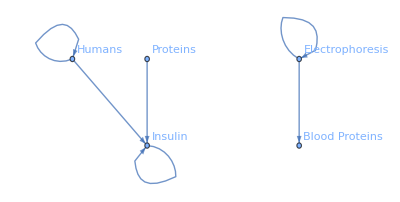

```mathematica
Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topoftopCitingCitedMeSHgraph[gen]]
```

{Humans,Electrophoresis,Blood Proteins,Insulin,Proteins}

< edge list >

```mathematica
el[gen]=EdgeList[topoftopCitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Electrophoresis->Electrophoresis,Electrophoresis->Blood Proteins,Humans->Insulin,Proteins->Insulin,Insulin->Insulin}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topoftopCitingCitedMeSHgraph[gen],EdgeWeight]
```

{7.42164,5.35518,5.35518,5.18041,4.9316,3.41786}

```mathematica
topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

7.42164 | 0 | 0 | 5.18041 | 0
0 | 5.35518 | 5.35518 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3.41786 | 0
0 | 0 | 0 | 4.9316 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{12.602,10.7104,0,3.41786,4.9316}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{7.42164,5.35518,5.35518,13.5299,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Insulin

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{20.0237,16.0655,5.35518,16.9477,4.9316}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{12.602,7.42164},{10.7104,5.35518},{0,5.35518},{3.41786,13.5299},{4.9316,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

1.84897

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.00927705],Electrophoresis->Electrophoresis→Thickness[0.00669397],Electrophoresis->Blood Proteins→Thickness[0.00669397],Humans->Insulin→Thickness[0.00647551],Proteins->Insulin→Thickness[0.0061645],Insulin->Insulin→Thickness[0.00427232]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Insulin→Insulin}

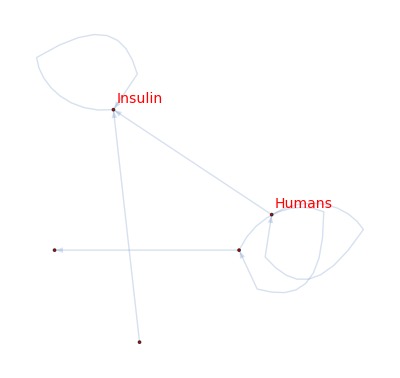

```mathematica
g[gen]=Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

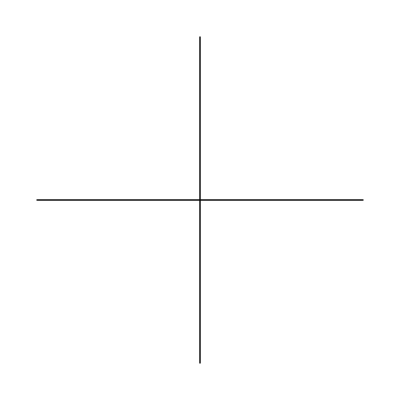

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

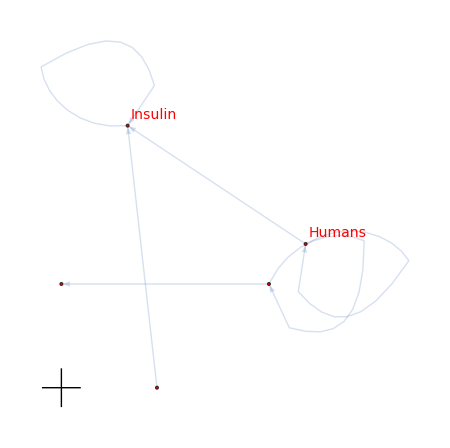

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1960

```mathematica
gen=1960
```

1960

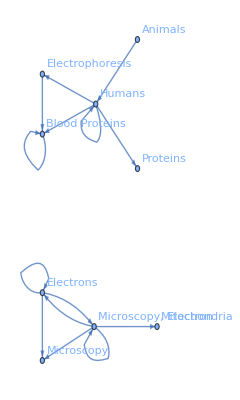

```mathematica
Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topoftopCitingCitedMeSHgraph[gen]]
```

{Humans,Blood Proteins,Electrophoresis,Animals,Microscopy, Electron,Microscopy,Electrons,Proteins,Mitochondria}

< edge list >

```mathematica
el[gen]=EdgeList[topoftopCitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Humans->Blood Proteins,Electrophoresis->Blood Proteins,Humans->Electrophoresis,Animals->Humans,Blood Proteins->Blood Proteins,Microscopy, Electron->Microscopy, Electron,Microscopy, Electron->Microscopy,Microscopy, Electron->Electrons,Humans->Proteins,Electrons->Microscopy, Electron,Electrons->Microscopy,Electrons->Electrons,Microscopy, Electron->Mitochondria}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topoftopCitingCitedMeSHgraph[gen],EdgeWeight]
```

{20.3947,15.7438,11.6148,10.4821,10.0365,8.8926,8.43563,8.43563,8.43563,7.91921,7.9018,7.9018,7.9018,7.52483}

```mathematica
topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

20.3947 | 15.7438 | 10.4821 | 0 | 0 | 0 | 0 | 7.91921 | 0
0 | 8.8926 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 11.6148 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10.0365 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 8.43563 | 8.43563 | 8.43563 | 0 | 7.52483
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 7.9018 | 7.9018 | 7.9018 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{54.5398,8.8926,11.6148,10.0365,32.8317,0,23.7054,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{30.4313,36.2512,10.4821,0,16.3374,16.3374,16.3374,7.91921,7.52483}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Blood Proteins

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{84.971,45.1438,22.0968,10.0365,49.1692,16.3374,40.0428,7.91921,7.52483}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{54.5398,30.4313},{8.8926,36.2512},{11.6148,10.4821},{10.0365,0},{32.8317,16.3374},{0,16.3374},{23.7054,16.3374},{0,7.91921},{0,7.52483}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

6.54884

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.0254934],Humans->Blood Proteins→Thickness[0.0196797],Electrophoresis->Blood Proteins→Thickness[0.0145185],Humans->Electrophoresis→Thickness[0.0131026],Animals->Humans→Thickness[0.0125457],Blood Proteins->Blood Proteins→Thickness[0.0111157],Microscopy, Electron->Microscopy, Electron→Thickness[0.0105445],Microscopy, Electron->Microscopy→Thickness[0.0105445],Microscopy, Electron->Electrons→Thickness[0.0105445],Humans->Proteins→Thickness[0.00989901],Electrons->Microscopy, Electron→Thickness[0.00987724],Electrons->Microscopy→Thickness[0.00987724],Electrons->Electrons→Thickness[0.00987724],Microscopy, Electron->Mitochondria→Thickness[0.00940604]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Blood Proteins→Blood Proteins}

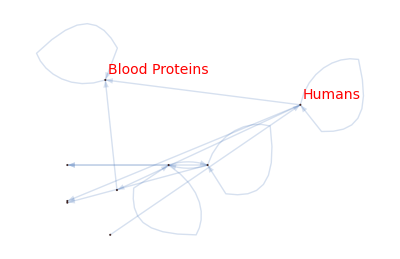

```mathematica
g[gen]=Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

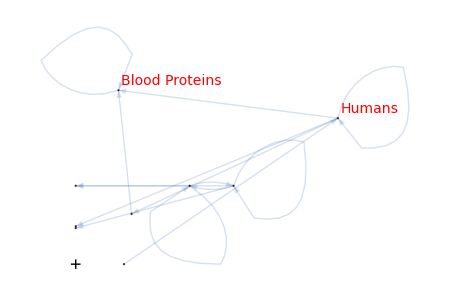

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1965

```mathematica
gen=1965
```

1965

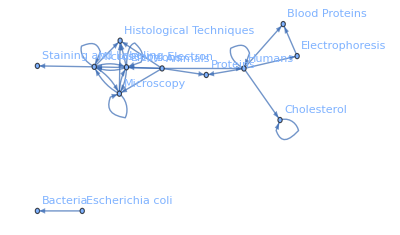

```mathematica
Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topoftopCitingCitedMeSHgraph[gen]]
```

{Microscopy, Electron,Animals,Humans,Microscopy,Electrons,Escherichia coli,Bacteria,Histological Techniques,Blood Proteins,Electrophoresis,Proteins,Cholesterol,Staining and Labeling}

< edge list >

```mathematica
el[gen]=EdgeList[topoftopCitingCitedMeSHgraph[gen]]
```

{Microscopy, Electron->Microscopy, Electron,Animals->Humans,Humans->Humans,Animals->Microscopy, Electron,Microscopy, Electron->Microscopy,Microscopy, Electron->Electrons,Electrons->Microscopy, Electron,Microscopy->Microscopy, Electron,Escherichia coli->Bacteria,Microscopy, Electron->Histological Techniques,Animals->Microscopy,Animals->Electrons,Electrons->Microscopy,Electrons->Electrons,Humans->Blood Proteins,Humans->Electrophoresis,Humans->Proteins,Microscopy->Microscopy,Microscopy->Electrons,Animals->Histological Techniques,Electrophoresis->Blood Proteins,Humans->Cholesterol,Electrons->Histological Techniques,Animals->Proteins,Microscopy, Electron->Staining and Labeling,Microscopy->Histological Techniques,Cholesterol->Cholesterol}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topoftopCitingCitedMeSHgraph[gen],EdgeWeight]
```

{21.4444,18.9107,18.33,17.0739,16.7522,16.7522,14.5171,13.2689,13.2224,13.099,12.8413,12.8413,11.693,11.693,11.3593,10.9961,10.956,10.5522,10.5522,10.2112,10.0515,9.76944,9.11733,9.06606,8.60976,8.35874,8.15877}

```mathematica
topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

21.4444 | 0 | 0 | 16.7522 | 16.7522 | 0 | 0 | 13.099 | 0 | 0 | 0 | 0 | 8.60976
17.0739 | 0 | 18.9107 | 12.8413 | 12.8413 | 0 | 0 | 10.2112 | 0 | 0 | 9.06606 | 0 | 0
0 | 0 | 18.33 | 0 | 0 | 0 | 0 | 0 | 11.3593 | 10.9961 | 10.956 | 9.76944 | 0
13.2689 | 0 | 0 | 10.5522 | 10.5522 | 0 | 0 | 8.35874 | 0 | 0 | 0 | 0 | 0
14.5171 | 0 | 0 | 11.693 | 11.693 | 0 | 0 | 9.11733 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 13.2224 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.0515 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.15877 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{76.6576,80.9444,61.4108,42.7321,47.0203,13.2224,0,0,0,10.0515,0,8.15877,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Animals

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{66.3043,0,37.2407,51.8386,51.8386,0,13.2224,40.7863,21.4109,10.9961,20.022,17.9282,8.60976}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Microscopy, Electron

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{142.962,80.9444,98.6515,94.5707,98.8589,13.2224,13.2224,40.7863,21.4109,21.0476,20.022,26.087,8.60976}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{76.6576,66.3043},{80.9444,0},{61.4108,37.2407},{42.7321,51.8386},{47.0203,51.8386},{13.2224,0},{0,13.2224},{0,40.7863},{0,21.4109},{10.0515,10.9961},{0,20.022},{8.15877,17.9282},{0,8.60976}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

10.4634

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Microscopy, Electron->Microscopy, Electron→Thickness[0.0268056],Animals->Humans→Thickness[0.0236384],Humans->Humans→Thickness[0.0229125],Animals->Microscopy, Electron→Thickness[0.0213424],Microscopy, Electron->Microscopy→Thickness[0.0209402],Microscopy, Electron->Electrons→Thickness[0.0209402],Electrons->Microscopy, Electron→Thickness[0.0181463],Microscopy->Microscopy, Electron→Thickness[0.0165861],Escherichia coli->Bacteria→Thickness[0.016528],Microscopy, Electron->Histological Techniques→Thickness[0.0163738],Animals->Microscopy→Thickness[0.0160516],Animals->Electrons→Thickness[0.0160516],Electrons->Microscopy→Thickness[0.0146162],Electrons->Electrons→Thickness[0.0146162],Humans->Blood Proteins→Thickness[0.0141992],Humans->Electrophoresis→Thickness[0.0137451],Humans->Proteins→Thickness[0.013695],Microscopy->Microscopy→Thickness[0.0131903],Microscopy->Electrons→Thickness[0.0131903],Animals->Histological Techniques→Thickness[0.012764],Electrophoresis->Blood Proteins→Thickness[0.0125644],Humans->Cholesterol→Thickness[0.0122118],Electrons->Histological Techniques→Thickness[0.0113967],Animals->Proteins→Thickness[0.0113326],Microscopy, Electron->Staining and Labeling→Thickness[0.0107622],Microscopy->Histological Techniques→Thickness[0.0104484],Cholesterol->Cholesterol→Thickness[0.0101985]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Animals→Animals,Microscopy, Electron→Microscopy, Electron}

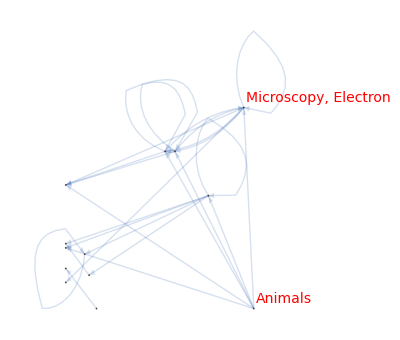

```mathematica
g[gen]=Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

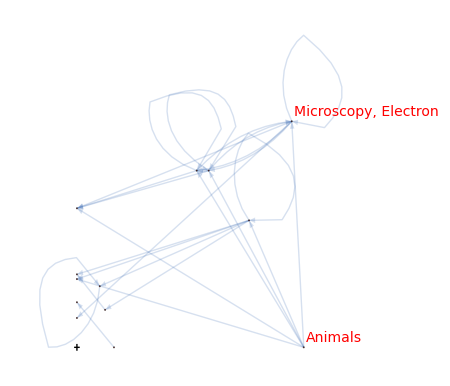

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1970

```mathematica
gen=1970
```

1970

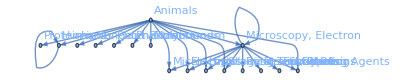

```mathematica
Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topoftopCitingCitedMeSHgraph[gen]]
```

{Microscopy, Electron,Animals,Microscopy,Electrons,Histological Techniques,Staining and Labeling,Coloring Agents,Proteins,Humans,Lipids,Tungsten Compounds,Plant Extracts,Phenols,Molybdenum,Resins, Synthetic,Resins, Plant,Epoxy Resins}

< edge list >

```mathematica
el[gen]=EdgeList[topoftopCitingCitedMeSHgraph[gen]]
```

{Microscopy, Electron->Microscopy, Electron,Animals->Microscopy, Electron,Microscopy, Electron->Microscopy,Microscopy, Electron->Electrons,Microscopy, Electron->Histological Techniques,Animals->Microscopy,Animals->Electrons,Microscopy, Electron->Staining and Labeling,Animals->Histological Techniques,Microscopy, Electron->Coloring Agents,Animals->Proteins,Animals->Humans,Animals->Staining and Labeling,Humans->Humans,Animals->Lipids,Animals->Coloring Agents,Animals->Tungsten Compounds,Animals->Plant Extracts,Animals->Phenols,Animals->Molybdenum,Microscopy, Electron->Resins, Synthetic,Microscopy, Electron->Resins, Plant,Microscopy, Electron->Epoxy Resins}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topoftopCitingCitedMeSHgraph[gen],EdgeWeight]
```

{68.5065,52.8479,48.8338,48.8338,36.2019,35.9387,35.9387,34.6581,30.4008,28.9624,28.931,27.6185,27.4094,26.4556,23.6543,22.9942,22.6482,22.6482,22.6482,22.6482,19.6727,19.6727,19.6727}

```mathematica
topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

68.5065 | 0 | 48.8338 | 48.8338 | 36.2019 | 34.6581 | 28.9624 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.6727 | 19.6727 | 19.6727
52.8479 | 0 | 35.9387 | 35.9387 | 30.4008 | 27.4094 | 22.9942 | 28.931 | 27.6185 | 23.6543 | 22.6482 | 22.6482 | 22.6482 | 22.6482 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 26.4556 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{325.014,376.326,0,0,0,0,0,0,26.4556,0,0,0,0,0,0,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Animals

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{121.354,0,84.7725,84.7725,66.6027,62.0675,51.9566,28.931,54.0741,23.6543,22.6482,22.6482,22.6482,22.6482,19.6727,19.6727,19.6727}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Microscopy, Electron

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{446.369,376.326,84.7725,84.7725,66.6027,62.0675,51.9566,28.931,80.5296,23.6543,22.6482,22.6482,22.6482,22.6482,19.6727,19.6727,19.6727}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{325.014,121.354},{376.326,0},{0,84.7725},{0,84.7725},{0,66.6027},{0,62.0675},{0,51.9566},{0,28.931},{26.4556,54.0741},{0,23.6543},{0,22.6482},{0,22.6482},{0,22.6482},{0,22.6482},{0,19.6727},{0,19.6727},{0,19.6727}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

39.5409

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Microscopy, Electron->Microscopy, Electron→Thickness[0.0856331],Animals->Microscopy, Electron→Thickness[0.0660599],Microscopy, Electron->Microscopy→Thickness[0.0610423],Microscopy, Electron->Electrons→Thickness[0.0610423],Microscopy, Electron->Histological Techniques→Thickness[0.0452523],Animals->Microscopy→Thickness[0.0449234],Animals->Electrons→Thickness[0.0449234],Microscopy, Electron->Staining and Labeling→Thickness[0.0433226],Animals->Histological Techniques→Thickness[0.038001],Microscopy, Electron->Coloring Agents→Thickness[0.036203],Animals->Proteins→Thickness[0.0361638],Animals->Humans→Thickness[0.0345232],Animals->Staining and Labeling→Thickness[0.0342618],Humans->Humans→Thickness[0.0330694],Animals->Lipids→Thickness[0.0295679],Animals->Coloring Agents→Thickness[0.0287428],Animals->Tungsten Compounds→Thickness[0.0283102],Animals->Plant Extracts→Thickness[0.0283102],Animals->Phenols→Thickness[0.0283102],Animals->Molybdenum→Thickness[0.0283102],Microscopy, Electron->Resins, Synthetic→Thickness[0.0245908],Microscopy, Electron->Resins, Plant→Thickness[0.0245908],Microscopy, Electron->Epoxy Resins→Thickness[0.0245908]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Animals→Animals,Microscopy, Electron→Microscopy, Electron}

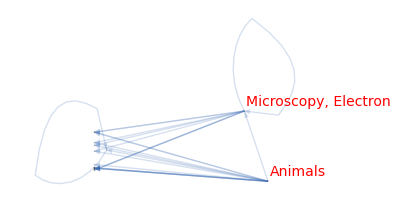

```mathematica
g[gen]=Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

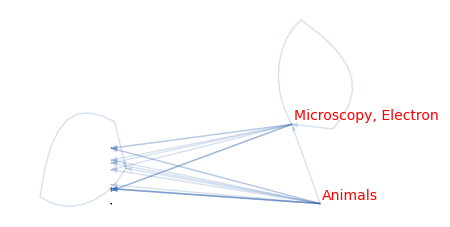

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1975

```mathematica
gen=1975
```

1975

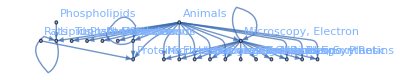

```mathematica
Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topoftopCitingCitedMeSHgraph[gen]]
```

{Microscopy, Electron,Animals,Proteins,Microscopy,Electrons,Tungsten Compounds,Plant Extracts,Phenols,Molybdenum,Histological Techniques,Lipids,Staining and Labeling,Humans,Coloring Agents,Phospholipids,Resins, Synthetic,Resins, Plant,Epoxy Resins,Lead,Citric Acid,Citrates,Rats}

< edge list >

```mathematica
el[gen]=EdgeList[topoftopCitingCitedMeSHgraph[gen]]
```

{Microscopy, Electron->Microscopy, Electron,Animals->Microscopy, Electron,Animals->Proteins,Microscopy, Electron->Microscopy,Microscopy, Electron->Electrons,Animals->Tungsten Compounds,Animals->Plant Extracts,Animals->Phenols,Animals->Molybdenum,Animals->Microscopy,Animals->Electrons,Microscopy, Electron->Histological Techniques,Animals->Lipids,Animals->Histological Techniques,Microscopy, Electron->Staining and Labeling,Animals->Humans,Animals->Staining and Labeling,Humans->Humans,Microscopy, Electron->Coloring Agents,Phospholipids->Lipids,Animals->Coloring Agents,Microscopy, Electron->Resins, Synthetic,Microscopy, Electron->Resins, Plant,Microscopy, Electron->Epoxy Resins,Microscopy, Electron->Lead,Microscopy, Electron->Citric Acid,Microscopy, Electron->Citrates,Lipids->Lipids,Animals->Resins, Synthetic,Animals->Resins, Plant,Animals->Epoxy Resins,Humans->Proteins,Rats->Proteins}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topoftopCitingCitedMeSHgraph[gen],EdgeWeight]
```

{91.1877,78.3125,70.6527,62.2245,62.2245,59.3023,59.3023,59.3023,59.3023,52.2781,52.2781,49.209,48.5212,43.4029,42.242,38.5025,36.8794,36.7454,34.2388,30.4158,30.0814,28.9632,28.9632,28.9632,28.3902,28.1685,28.1685,26.7069,26.0344,26.0344,26.0344,24.9803,24.7907}

```mathematica
topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

91.1877 | 0 | 0 | 62.2245 | 62.2245 | 0 | 0 | 0 | 0 | 49.209 | 0 | 42.242 | 0 | 34.2388 | 0 | 28.9632 | 28.9632 | 28.9632 | 28.3902 | 28.1685 | 28.1685 | 0
78.3125 | 0 | 70.6527 | 52.2781 | 52.2781 | 59.3023 | 59.3023 | 59.3023 | 59.3023 | 43.4029 | 48.5212 | 36.8794 | 38.5025 | 30.0814 | 0 | 26.0344 | 26.0344 | 26.0344 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 26.7069 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 24.9803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 36.7454 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 30.4158 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 24.7907 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{512.943,766.221,0,0,0,0,0,0,0,0,26.7069,0,61.7257,0,30.4158,0,0,0,0,0,0,24.7907}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Animals

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{169.5,0,120.424,114.503,114.503,59.3023,59.3023,59.3023,59.3023,92.6119,105.644,79.1215,75.2479,64.3202,0,54.9976,54.9976,54.9976,28.3902,28.1685,28.1685,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Microscopy, Electron

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{682.443,766.221,120.424,114.503,114.503,59.3023,59.3023,59.3023,59.3023,92.6119,132.351,79.1215,136.974,64.3202,30.4158,54.9976,54.9976,54.9976,28.3902,28.1685,28.1685,24.7907}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{512.943,169.5},{766.221,0},{0,120.424},{0,114.503},{0,114.503},{0,59.3023},{0,59.3023},{0,59.3023},{0,59.3023},{0,92.6119},{26.7069,105.644},{0,79.1215},{61.7257,75.2479},{0,64.3202},{30.4158,0},{0,54.9976},{0,54.9976},{0,54.9976},{0,28.3902},{0,28.1685},{0,28.1685},{24.7907,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

78.4746

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Microscopy, Electron->Microscopy, Electron→Thickness[0.113985],Animals->Microscopy, Electron→Thickness[0.0978906],Animals->Proteins→Thickness[0.0883159],Microscopy, Electron->Microscopy→Thickness[0.0777806],Microscopy, Electron->Electrons→Thickness[0.0777806],Animals->Tungsten Compounds→Thickness[0.0741279],Animals->Plant Extracts→Thickness[0.0741279],Animals->Phenols→Thickness[0.0741279],Animals->Molybdenum→Thickness[0.0741279],Animals->Microscopy→Thickness[0.0653476],Animals->Electrons→Thickness[0.0653476],Microscopy, Electron->Histological Techniques→Thickness[0.0615112],Animals->Lipids→Thickness[0.0606515],Animals->Histological Techniques→Thickness[0.0542537],Microscopy, Electron->Staining and Labeling→Thickness[0.0528026],Animals->Humans→Thickness[0.0481281],Animals->Staining and Labeling→Thickness[0.0460993],Humans->Humans→Thickness[0.0459318],Microscopy, Electron->Coloring Agents→Thickness[0.0427985],Phospholipids->Lipids→Thickness[0.0380198],Animals->Coloring Agents→Thickness[0.0376018],Microscopy, Electron->Resins, Synthetic→Thickness[0.036204],Microscopy, Electron->Resins, Plant→Thickness[0.036204],Microscopy, Electron->Epoxy Resins→Thickness[0.036204],Microscopy, Electron->Lead→Thickness[0.0354878],Microscopy, Electron->Citric Acid→Thickness[0.0352107],Microscopy, Electron->Citrates→Thickness[0.0352107],Lipids->Lipids→Thickness[0.0333836],Animals->Resins, Synthetic→Thickness[0.032543],Animals->Resins, Plant→Thickness[0.032543],Animals->Epoxy Resins→Thickness[0.032543],Humans->Proteins→Thickness[0.0312254],Rats->Proteins→Thickness[0.0309884]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Animals→Animals,Microscopy, Electron→Microscopy, Electron}

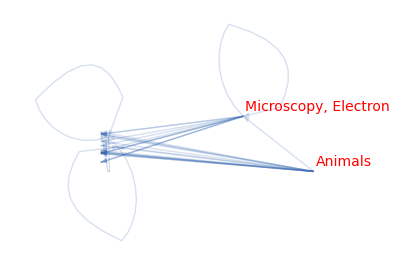

```mathematica
g[gen]=Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

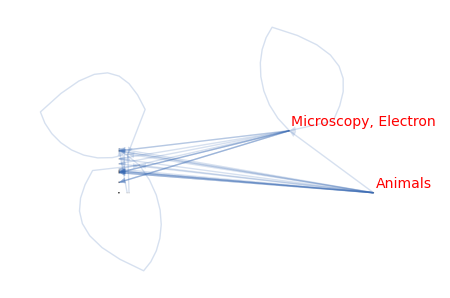

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1980

```mathematica
gen=1980
```

1980

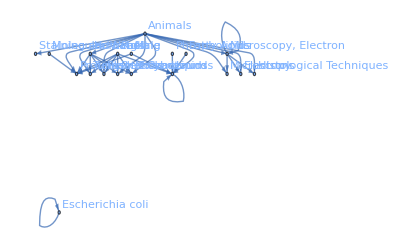

```mathematica
Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topoftopCitingCitedMeSHgraph[gen]]
```

{Animals,Proteins,Tungsten Compounds,Plant Extracts,Phenols,Molybdenum,Microscopy, Electron,Lipids,Microscopy,Electrons,Histological Techniques,Phospholipids,Rats,Humans,Staining and Labeling,Male,Molecular Weight,Escherichia coli,Fatty Acids}

< edge list >

```mathematica
el[gen]=EdgeList[topoftopCitingCitedMeSHgraph[gen]]
```

{Animals->Proteins,Animals->Tungsten Compounds,Animals->Plant Extracts,Animals->Phenols,Animals->Molybdenum,Animals->Microscopy, Electron,Microscopy, Electron->Microscopy, Electron,Animals->Lipids,Microscopy, Electron->Microscopy,Microscopy, Electron->Electrons,Animals->Microscopy,Animals->Electrons,Microscopy, Electron->Histological Techniques,Phospholipids->Lipids,Animals->Histological Techniques,Rats->Proteins,Humans->Proteins,Rats->Lipids,Rats->Tungsten Compounds,Rats->Plant Extracts,Rats->Phenols,Rats->Molybdenum,Humans->Tungsten Compounds,Humans->Plant Extracts,Humans->Phenols,Humans->Molybdenum,Animals->Staining and Labeling,Male->Proteins,Molecular Weight->Proteins,Animals->Humans,Escherichia coli->Escherichia coli,Male->Lipids,Lipids->Lipids,Fatty Acids->Lipids}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topoftopCitingCitedMeSHgraph[gen],EdgeWeight]
```

{148.286,125.552,125.552,125.552,125.552,105.319,104.354,102.12,64.4966,64.4966,62.4023,62.4023,58.8568,57.7018,57.2221,56.9721,55.6708,53.3314,51.2326,51.2326,51.2326,51.2326,47.2912,47.2912,47.2912,47.2912,47.0326,47.0096,46.5419,46.4855,46.4731,45.9415,44.9706,43.7723}

```mathematica
topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

0 | 148.286 | 125.552 | 125.552 | 125.552 | 125.552 | 105.319 | 102.12 | 62.4023 | 62.4023 | 57.2221 | 0 | 0 | 46.4855 | 47.0326 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 104.354 | 0 | 64.4966 | 64.4966 | 58.8568 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 44.9706 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 57.7018 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 56.9721 | 51.2326 | 51.2326 | 51.2326 | 51.2326 | 0 | 53.3314 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 55.6708 | 47.2912 | 47.2912 | 47.2912 | 47.2912 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 47.0096 | 0 | 0 | 0 | 0 | 0 | 45.9415 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 46.5419 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 46.4731 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 43.7723 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{1133.48,0,0,0,0,0,292.204,44.9706,0,0,0,57.7018,315.234,244.836,0,92.9511,46.5419,46.4731,43.7723}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Animals

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{0,354.48,224.076,224.076,224.076,224.076,209.673,347.838,126.899,126.899,116.079,0,0,46.4855,47.0326,0,0,46.4731,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Proteins

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{1133.48,354.48,224.076,224.076,224.076,224.076,501.877,392.808,126.899,126.899,116.079,57.7018,315.234,291.321,47.0326,92.9511,46.5419,92.9463,43.7723}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{1133.48,0},{0,354.48},{0,224.076},{0,224.076},{0,224.076},{0,224.076},{292.204,209.673},{44.9706,347.838},{0,126.899},{0,126.899},{0,116.079},{57.7018,0},{315.234,0},{244.836,46.4855},{0,47.0326},{92.9511,0},{46.5419,0},{46.4731,46.4731},{43.7723,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

118.762

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Animals->Proteins→Thickness[0.185357],Animals->Tungsten Compounds→Thickness[0.15694],Animals->Plant Extracts→Thickness[0.15694],Animals->Phenols→Thickness[0.15694],Animals->Molybdenum→Thickness[0.15694],Animals->Microscopy, Electron→Thickness[0.131649],Microscopy, Electron->Microscopy, Electron→Thickness[0.130442],Animals->Lipids→Thickness[0.12765],Microscopy, Electron->Microscopy→Thickness[0.0806207],Microscopy, Electron->Electrons→Thickness[0.0806207],Animals->Microscopy→Thickness[0.0780029],Animals->Electrons→Thickness[0.0780029],Microscopy, Electron->Histological Techniques→Thickness[0.073571],Phospholipids->Lipids→Thickness[0.0721272],Animals->Histological Techniques→Thickness[0.0715277],Rats->Proteins→Thickness[0.0712151],Humans->Proteins→Thickness[0.0695884],Rats->Lipids→Thickness[0.0666642],Rats->Tungsten Compounds→Thickness[0.0640408],Rats->Plant Extracts→Thickness[0.0640408],Rats->Phenols→Thickness[0.0640408],Rats->Molybdenum→Thickness[0.0640408],Humans->Tungsten Compounds→Thickness[0.059114],Humans->Plant Extracts→Thickness[0.059114],Humans->Phenols→Thickness[0.059114],Humans->Molybdenum→Thickness[0.059114],Animals->Staining and Labeling→Thickness[0.0587908],Male->Proteins→Thickness[0.0587621],Molecular Weight->Proteins→Thickness[0.0581773],Animals->Humans→Thickness[0.0581068],Escherichia coli->Escherichia coli→Thickness[0.0580914],Male->Lipids→Thickness[0.0574269],Lipids->Lipids→Thickness[0.0562132],Fatty Acids->Lipids→Thickness[0.0547154]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Animals→Animals,Proteins→Proteins}

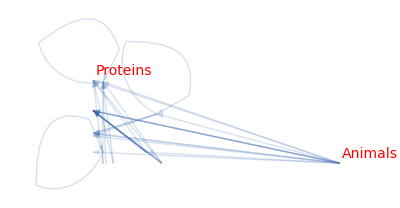

```mathematica
g[gen]=Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

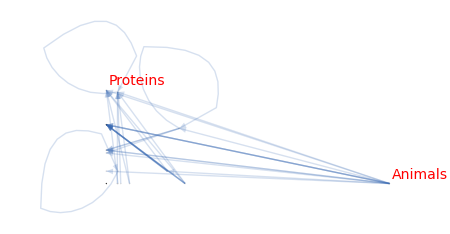

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1985

```mathematica
gen=1985
```

1985

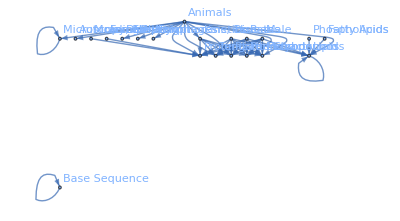

```mathematica
Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topoftopCitingCitedMeSHgraph[gen]]
```

{Animals,Proteins,Tungsten Compounds,Plant Extracts,Phenols,Molybdenum,Lipids,Humans,Rats,Microscopy, Electron,Male,Phospholipids,Base Sequence,Kinetics,Fatty Acids,Autoradiography,Molecular Weight,Female,DNA,Electrophoresis, Disc,Coliphages}

< edge list >

```mathematica
el[gen]=EdgeList[topoftopCitingCitedMeSHgraph[gen]]
```

{Animals->Proteins,Animals->Tungsten Compounds,Animals->Plant Extracts,Animals->Phenols,Animals->Molybdenum,Animals->Lipids,Humans->Proteins,Rats->Proteins,Animals->Microscopy, Electron,Rats->Tungsten Compounds,Rats->Plant Extracts,Rats->Phenols,Rats->Molybdenum,Male->Proteins,Microscopy, Electron->Microscopy, Electron,Humans->Tungsten Compounds,Humans->Plant Extracts,Humans->Phenols,Humans->Molybdenum,Phospholipids->Lipids,Rats->Lipids,Male->Tungsten Compounds,Male->Plant Extracts,Male->Phenols,Male->Molybdenum,Male->Lipids,Base Sequence->Base Sequence,Kinetics->Proteins,Fatty Acids->Lipids,Animals->Autoradiography,Molecular Weight->Proteins,Lipids->Lipids,Female->Proteins,Animals->Kinetics,Kinetics->Tungsten Compounds,Kinetics->Plant Extracts,Kinetics->Phenols,Kinetics->Molybdenum,Animals->DNA,Humans->Lipids,Animals->Electrophoresis, Disc,Animals->Coliphages}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topoftopCitingCitedMeSHgraph[gen],EdgeWeight]
```

{226.331,193.399,193.399,193.399,193.399,145.345,91.4279,90.6333,83.6084,81.095,81.095,81.095,81.095,78.9746,78.1968,77.2184,77.2184,77.2184,77.2184,75.7371,75.2258,71.5333,71.5333,71.5333,71.5333,68.2406,67.7807,61.0198,56.3553,55.7599,55.1612,54.7446,54.0694,52.5655,52.1255,52.1255,52.1255,52.1255,51.4081,51.125,48.1273,47.7706}

```mathematica
topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

0 | 226.331 | 193.399 | 193.399 | 193.399 | 193.399 | 145.345 | 0 | 0 | 83.6084 | 0 | 0 | 0 | 52.5655 | 0 | 55.7599 | 0 | 0 | 51.4081 | 48.1273 | 47.7706
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 54.7446 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 91.4279 | 77.2184 | 77.2184 | 77.2184 | 77.2184 | 51.125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 90.6333 | 81.095 | 81.095 | 81.095 | 81.095 | 75.2258 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 78.1968 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 78.9746 | 71.5333 | 71.5333 | 71.5333 | 71.5333 | 68.2406 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 75.7371 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 67.7807 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 61.0198 | 52.1255 | 52.1255 | 52.1255 | 52.1255 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 56.3553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 55.1612 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 54.0694 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{1484.51,0,0,0,0,0,54.7446,451.427,490.239,78.1968,433.348,75.7371,67.7807,269.522,56.3553,0,55.1612,54.0694,0,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Animals

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{0,657.618,475.371,475.371,475.371,475.371,526.774,0,0,161.805,0,0,67.7807,52.5655,0,55.7599,0,0,51.4081,48.1273,47.7706}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Proteins

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{1484.51,657.618,475.371,475.371,475.371,475.371,581.518,451.427,490.239,240.002,433.348,75.7371,135.561,322.087,56.3553,55.7599,55.1612,54.0694,51.4081,48.1273,47.7706}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{1484.51,0},{0,657.618},{0,475.371},{0,475.371},{0,475.371},{0,475.371},{54.7446,526.774},{451.427,0},{490.239,0},{78.1968,161.805},{433.348,0},{75.7371,0},{67.7807,67.7807},{269.522,52.5655},{56.3553,0},{0,55.7599},{55.1612,0},{54.0694,0},{0,51.4081},{0,48.1273},{0,47.7706}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

162.365

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Animals->Proteins→Thickness[0.282914],Animals->Tungsten Compounds→Thickness[0.241748],Animals->Plant Extracts→Thickness[0.241748],Animals->Phenols→Thickness[0.241748],Animals->Molybdenum→Thickness[0.241748],Animals->Lipids→Thickness[0.181682],Humans->Proteins→Thickness[0.114285],Rats->Proteins→Thickness[0.113292],Animals->Microscopy, Electron→Thickness[0.10451],Rats->Tungsten Compounds→Thickness[0.101369],Rats->Plant Extracts→Thickness[0.101369],Rats->Phenols→Thickness[0.101369],Rats->Molybdenum→Thickness[0.101369],Male->Proteins→Thickness[0.0987183],Microscopy, Electron->Microscopy, Electron→Thickness[0.097746],Humans->Tungsten Compounds→Thickness[0.096523],Humans->Plant Extracts→Thickness[0.096523],Humans->Phenols→Thickness[0.096523],Humans->Molybdenum→Thickness[0.096523],Phospholipids->Lipids→Thickness[0.0946714],Rats->Lipids→Thickness[0.0940322],Male->Tungsten Compounds→Thickness[0.0894166],Male->Plant Extracts→Thickness[0.0894166],Male->Phenols→Thickness[0.0894166],Male->Molybdenum→Thickness[0.0894166],Male->Lipids→Thickness[0.0853007],Base Sequence->Base Sequence→Thickness[0.0847259],Kinetics->Proteins→Thickness[0.0762747],Fatty Acids->Lipids→Thickness[0.0704441],Animals->Autoradiography→Thickness[0.0696998],Molecular Weight->Proteins→Thickness[0.0689515],Lipids->Lipids→Thickness[0.0684308],Female->Proteins→Thickness[0.0675867],Animals->Kinetics→Thickness[0.0657069],Kinetics->Tungsten Compounds→Thickness[0.0651568],Kinetics->Plant Extracts→Thickness[0.0651568],Kinetics->Phenols→Thickness[0.0651568],Kinetics->Molybdenum→Thickness[0.0651568],Animals->DNA→Thickness[0.0642602],Humans->Lipids→Thickness[0.0639062],Animals->Electrophoresis, Disc→Thickness[0.0601591],Animals->Coliphages→Thickness[0.0597133]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Animals→Animals,Proteins→Proteins}

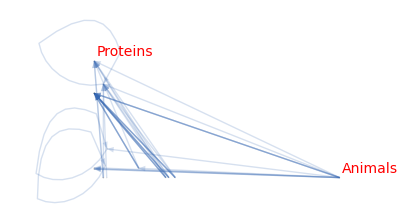

```mathematica
g[gen]=Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

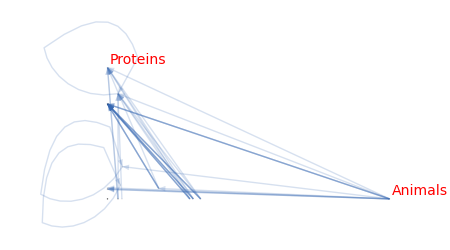

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1990

```mathematica
gen=1990
```

1990

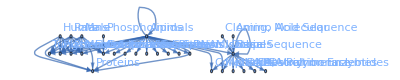

```mathematica
Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topoftopCitingCitedMeSHgraph[gen]]
```

{Animals,Proteins,Tungsten Compounds,Plant Extracts,Phenols,Molybdenum,Base Sequence,Lipids,DNA Restriction Enzymes,Rats,Humans,Coliphages,Male,Autoradiography,Kinetics,Methods,DNA, Viral,DNA Polymerase I,Electrophoresis, Disc,Cloning, Molecular,Viral Proteins,Genetics, Microbial,Genes,Carbon Isotopes,DNA,Deoxyribonucleotides,Amino Acid Sequence,Phospholipids}

< edge list >

```mathematica
el[gen]=EdgeList[topoftopCitingCitedMeSHgraph[gen]]
```

{Animals->Proteins,Animals->Tungsten Compounds,Animals->Plant Extracts,Animals->Phenols,Animals->Molybdenum,Base Sequence->Base Sequence,Animals->Lipids,Base Sequence->DNA Restriction Enzymes,Rats->Proteins,Humans->Proteins,Animals->Coliphages,Rats->Tungsten Compounds,Rats->Plant Extracts,Rats->Phenols,Rats->Molybdenum,Male->Proteins,Animals->Autoradiography,Animals->Kinetics,Humans->Tungsten Compounds,Humans->Plant Extracts,Humans->Phenols,Humans->Molybdenum,Base Sequence->Methods,Male->Tungsten Compounds,Male->Plant Extracts,Male->Phenols,Male->Molybdenum,Animals->Base Sequence,Base Sequence->Coliphages,Base Sequence->DNA, Viral,Base Sequence->DNA Polymerase I,Animals->Electrophoresis, Disc,Cloning, Molecular->Base Sequence,Animals->Viral Proteins,Animals->Genetics, Microbial,Animals->Genes,Animals->Carbon Isotopes,Rats->Lipids,Animals->Methods,Kinetics->Proteins,Animals->Animals,Animals->DNA,Base Sequence->Deoxyribonucleotides,Male->Lipids,Amino Acid Sequence->Base Sequence,Phospholipids->Lipids}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topoftopCitingCitedMeSHgraph[gen],EdgeWeight]
```

{296.298,258.271,258.271,258.271,258.271,157.319,156.952,124.31,122.563,121.192,118.183,110.717,110.717,110.717,110.717,109.228,105.772,104.299,103.317,103.317,103.317,103.317,100.893,99.4947,99.4947,99.4947,99.4947,97.8779,95.6225,93.0985,93.0985,92.4025,87.9837,87.0122,87.0122,87.0122,87.0122,84.8739,84.6854,83.3629,83.0645,81.736,78.2315,77.9296,77.773,74.1471}

```mathematica
topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

83.0645 | 296.298 | 258.271 | 258.271 | 258.271 | 258.271 | 97.8779 | 156.952 | 0 | 0 | 0 | 118.183 | 0 | 105.772 | 104.299 | 84.6854 | 0 | 0 | 92.4025 | 0 | 87.0122 | 87.0122 | 87.0122 | 87.0122 | 81.736 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 157.319 | 0 | 124.31 | 0 | 0 | 95.6225 | 0 | 0 | 0 | 100.893 | 93.0985 | 93.0985 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 78.2315 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 122.563 | 110.717 | 110.717 | 110.717 | 110.717 | 0 | 84.8739 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 121.192 | 103.317 | 103.317 | 103.317 | 103.317 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 109.228 | 99.4947 | 99.4947 | 99.4947 | 99.4947 | 0 | 77.9296 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 83.3629 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 87.9837 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 77.773 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 74.1471 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{2602.4,0,0,0,0,0,742.573,0,0,650.305,534.459,0,585.137,0,83.3629,0,0,0,0,87.9837,0,0,0,0,0,0,77.773,74.1471}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Animals

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{83.0645,732.644,571.8,571.8,571.8,571.8,420.953,393.903,124.31,0,0,213.806,0,105.772,104.299,185.578,93.0985,93.0985,92.4025,0,87.0122,87.0122,87.0122,87.0122,81.736,78.2315,0,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Proteins

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{2685.47,732.644,571.8,571.8,571.8,571.8,1163.53,393.903,124.31,650.305,534.459,213.806,585.137,105.772,187.662,185.578,93.0985,93.0985,92.4025,87.9837,87.0122,87.0122,87.0122,87.0122,81.736,78.2315,77.773,74.1471}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{2602.4,83.0645},{0,732.644},{0,571.8},{0,571.8},{0,571.8},{0,571.8},{742.573,420.953},{0,393.903},{0,124.31},{650.305,0},{534.459,0},{0,213.806},{585.137,0},{0,105.772},{83.3629,104.299},{0,185.578},{0,93.0985},{0,93.0985},{0,92.4025},{87.9837,0},{0,87.0122},{0,87.0122},{0,87.0122},{0,87.0122},{0,81.736},{0,78.2315},{77.773,0},{74.1471,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

270.357

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Animals->Proteins→Thickness[0.370372],Animals->Tungsten Compounds→Thickness[0.322839],Animals->Plant Extracts→Thickness[0.322839],Animals->Phenols→Thickness[0.322839],Animals->Molybdenum→Thickness[0.322839],Base Sequence->Base Sequence→Thickness[0.196648],Animals->Lipids→Thickness[0.196191],Base Sequence->DNA Restriction Enzymes→Thickness[0.155388],Rats->Proteins→Thickness[0.153204],Humans->Proteins→Thickness[0.15149],Animals->Coliphages→Thickness[0.147729],Rats->Tungsten Compounds→Thickness[0.138396],Rats->Plant Extracts→Thickness[0.138396],Rats->Phenols→Thickness[0.138396],Rats->Molybdenum→Thickness[0.138396],Male->Proteins→Thickness[0.136535],Animals->Autoradiography→Thickness[0.132216],Animals->Kinetics→Thickness[0.130373],Humans->Tungsten Compounds→Thickness[0.129146],Humans->Plant Extracts→Thickness[0.129146],Humans->Phenols→Thickness[0.129146],Humans->Molybdenum→Thickness[0.129146],Base Sequence->Methods→Thickness[0.126116],Male->Tungsten Compounds→Thickness[0.124368],Male->Plant Extracts→Thickness[0.124368],Male->Phenols→Thickness[0.124368],Male->Molybdenum→Thickness[0.124368],Animals->Base Sequence→Thickness[0.122347],Base Sequence->Coliphages→Thickness[0.119528],Base Sequence->DNA, Viral→Thickness[0.116373],Base Sequence->DNA Polymerase I→Thickness[0.116373],Animals->Electrophoresis, Disc→Thickness[0.115503],Cloning, Molecular->Base Sequence→Thickness[0.10998],Animals->Viral Proteins→Thickness[0.108765],Animals->Genetics, Microbial→Thickness[0.108765],Animals->Genes→Thickness[0.108765],Animals->Carbon Isotopes→Thickness[0.108765],Rats->Lipids→Thickness[0.106092],Animals->Methods→Thickness[0.105857],Kinetics->Proteins→Thickness[0.104204],Animals->Animals→Thickness[0.103831],Animals->DNA→Thickness[0.10217],Base Sequence->Deoxyribonucleotides→Thickness[0.0977894],Male->Lipids→Thickness[0.097412],Amino Acid Sequence->Base Sequence→Thickness[0.0972162],Phospholipids->Lipids→Thickness[0.0926839]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Animals→Animals,Proteins→Proteins}

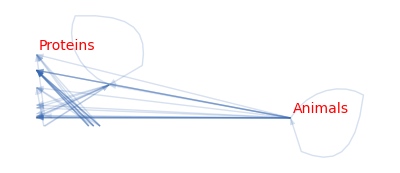

```mathematica
g[gen]=Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

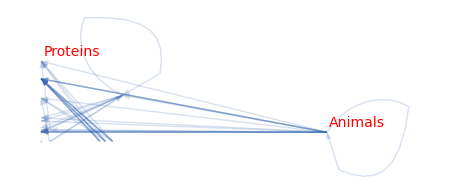

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1995

```mathematica
gen=1995
```

1995

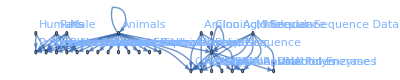

```mathematica
Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topoftopCitingCitedMeSHgraph[gen]]
```

{Animals,Proteins,Phenols,Tungsten Compounds,Plant Extracts,Molybdenum,Base Sequence,DNA Restriction Enzymes,Molecular Sequence Data,Coliphages,Methods,Lipids,Amino Acid Sequence,DNA, Viral,DNA Polymerase I,Autoradiography,Cloning, Molecular,Rats,Humans,Kinetics,Deoxyribonucleotides,Genes,Male,DNA,Viral Proteins,Genetics, Microbial,Electrophoresis, Disc,Carbon Isotopes}

< edge list >

```mathematica
el[gen]=EdgeList[topoftopCitingCitedMeSHgraph[gen]]
```

{Animals->Proteins,Animals->Phenols,Animals->Tungsten Compounds,Animals->Plant Extracts,Animals->Molybdenum,Base Sequence->Base Sequence,Base Sequence->DNA Restriction Enzymes,Molecular Sequence Data->Base Sequence,Base Sequence->Coliphages,Animals->Coliphages,Molecular Sequence Data->Coliphages,Base Sequence->Methods,Animals->Lipids,Amino Acid Sequence->Base Sequence,Molecular Sequence Data->DNA Restriction Enzymes,Base Sequence->DNA, Viral,Base Sequence->DNA Polymerase I,Animals->Autoradiography,Amino Acid Sequence->Coliphages,Cloning, Molecular->Base Sequence,Rats->Proteins,Molecular Sequence Data->Methods,Humans->Proteins,Animals->Base Sequence,Animals->Kinetics,Base Sequence->Deoxyribonucleotides,Animals->Animals,Animals->Genes,Male->Proteins,Amino Acid Sequence->DNA Restriction Enzymes,Rats->Phenols,Animals->Methods,Rats->Tungsten Compounds,Rats->Plant Extracts,Rats->Molybdenum,Base Sequence->DNA,Humans->Phenols,Animals->Viral Proteins,Animals->Genetics, Microbial,Animals->Electrophoresis, Disc,Animals->Carbon Isotopes,Male->Phenols,Amino Acid Sequence->Methods,Male->Tungsten Compounds,Male->Plant Extracts,Male->Molybdenum,Molecular Sequence Data->DNA, Viral,Molecular Sequence Data->DNA Polymerase I}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topoftopCitingCitedMeSHgraph[gen],EdgeWeight]
```

{364.909,315.602,304.199,304.199,304.199,290.797,228.088,210.867,204.218,190.098,185.686,185.58,184.297,173.112,171.19,161.774,161.774,159.212,158.086,154.793,153.979,152.541,151.818,150.68,149.034,145.715,145.289,140.579,140.529,139.241,137.567,134.866,134.182,134.182,134.182,133.53,132.158,130.609,130.609,130.609,130.609,127.527,124.876,124.041,124.041,124.041,123.72,123.72}

```mathematica
topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

145.289 | 364.909 | 315.602 | 304.199 | 304.199 | 304.199 | 150.68 | 0 | 0 | 190.098 | 134.866 | 184.297 | 0 | 0 | 0 | 159.212 | 0 | 0 | 0 | 149.034 | 0 | 140.579 | 0 | 0 | 130.609 | 130.609 | 130.609 | 130.609
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 290.797 | 228.088 | 0 | 204.218 | 185.58 | 0 | 0 | 161.774 | 161.774 | 0 | 0 | 0 | 0 | 0 | 145.715 | 0 | 0 | 133.53 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 210.867 | 171.19 | 0 | 185.686 | 152.541 | 0 | 0 | 123.72 | 123.72 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 173.112 | 139.241 | 0 | 158.086 | 124.876 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 154.793 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 153.979 | 137.567 | 134.182 | 134.182 | 134.182 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 151.818 | 132.158 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 140.529 | 127.527 | 124.041 | 124.041 | 124.041 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{3369.6,0,0,0,0,0,1511.47,0,967.723,0,0,0,595.315,0,0,0,154.793,694.093,283.976,0,0,0,640.178,0,0,0,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Animals

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{145.289,811.235,712.854,562.422,562.422,562.422,980.249,538.518,0,738.088,597.863,184.297,0,285.494,285.494,159.212,0,0,0,149.034,145.715,140.579,0,133.53,130.609,130.609,130.609,130.609}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Base Sequence

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{3514.89,811.235,712.854,562.422,562.422,562.422,2491.72,538.518,967.723,738.088,597.863,184.297,595.315,285.494,285.494,159.212,154.793,694.093,283.976,149.034,145.715,140.579,640.178,133.53,130.609,130.609,130.609,130.609}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{3369.6,145.289},{0,811.235},{0,712.854},{0,562.422},{0,562.422},{0,562.422},{1511.47,980.249},{0,538.518},{967.723,0},{0,738.088},{0,597.863},{0,184.297},{595.315,0},{0,285.494},{0,285.494},{0,159.212},{154.793,0},{694.093,0},{283.976,0},{0,149.034},{0,145.715},{0,140.579},{640.178,0},{0,133.53},{0,130.609},{0,130.609},{0,130.609},{0,130.609}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

350.929

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Animals->Proteins→Thickness[0.456136],Animals->Phenols→Thickness[0.394503],Animals->Tungsten Compounds→Thickness[0.380249],Animals->Plant Extracts→Thickness[0.380249],Animals->Molybdenum→Thickness[0.380249],Base Sequence->Base Sequence→Thickness[0.363497],Base Sequence->DNA Restriction Enzymes→Thickness[0.28511],Molecular Sequence Data->Base Sequence→Thickness[0.263584],Base Sequence->Coliphages→Thickness[0.255272],Animals->Coliphages→Thickness[0.237623],Molecular Sequence Data->Coliphages→Thickness[0.232107],Base Sequence->Methods→Thickness[0.231974],Animals->Lipids→Thickness[0.230371],Amino Acid Sequence->Base Sequence→Thickness[0.21639],Molecular Sequence Data->DNA Restriction Enzymes→Thickness[0.213987],Base Sequence->DNA, Viral→Thickness[0.202217],Base Sequence->DNA Polymerase I→Thickness[0.202217],Animals->Autoradiography→Thickness[0.199015],Amino Acid Sequence->Coliphages→Thickness[0.197608],Cloning, Molecular->Base Sequence→Thickness[0.193491],Rats->Proteins→Thickness[0.192474],Molecular Sequence Data->Methods→Thickness[0.190676],Humans->Proteins→Thickness[0.189773],Animals->Base Sequence→Thickness[0.18835],Animals->Kinetics→Thickness[0.186293],Base Sequence->Deoxyribonucleotides→Thickness[0.182143],Animals->Animals→Thickness[0.181611],Animals->Genes→Thickness[0.175724],Male->Proteins→Thickness[0.175661],Amino Acid Sequence->DNA Restriction Enzymes→Thickness[0.174051],Rats->Phenols→Thickness[0.171959],Animals->Methods→Thickness[0.168583],Rats->Tungsten Compounds→Thickness[0.167728],Rats->Plant Extracts→Thickness[0.167728],Rats->Molybdenum→Thickness[0.167728],Base Sequence->DNA→Thickness[0.166912],Humans->Phenols→Thickness[0.165198],Animals->Viral Proteins→Thickness[0.163262],Animals->Genetics, Microbial→Thickness[0.163262],Animals->Electrophoresis, Disc→Thickness[0.163262],Animals->Carbon Isotopes→Thickness[0.163262],Male->Phenols→Thickness[0.159409],Amino Acid Sequence->Methods→Thickness[0.156095],Male->Tungsten Compounds→Thickness[0.155051],Male->Plant Extracts→Thickness[0.155051],Male->Molybdenum→Thickness[0.155051],Molecular Sequence Data->DNA, Viral→Thickness[0.15465],Molecular Sequence Data->DNA Polymerase I→Thickness[0.15465]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Animals→Animals,Base Sequence→Base Sequence}

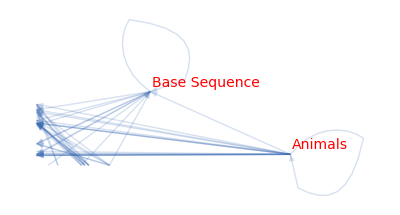

```mathematica
g[gen]=Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

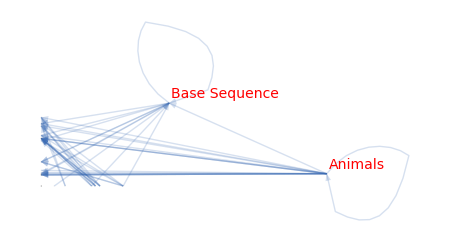

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 2000

```mathematica
gen=2000
```

2000

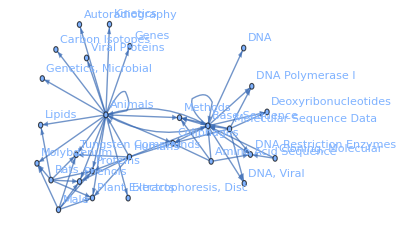

```mathematica
Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topoftopCitingCitedMeSHgraph[gen]]
```

{Animals,Proteins,Base Sequence,Phenols,Tungsten Compounds,Plant Extracts,Molybdenum,Molecular Sequence Data,Lipids,DNA Restriction Enzymes,Methods,Coliphages,Amino Acid Sequence,Autoradiography,Cloning, Molecular,DNA, Viral,Kinetics,DNA Polymerase I,Humans,Rats,Genes,Carbon Isotopes,Deoxyribonucleotides,Electrophoresis, Disc,DNA,Viral Proteins,Genetics, Microbial,Male}

< edge list >

```mathematica
el[gen]=EdgeList[topoftopCitingCitedMeSHgraph[gen]]
```

{Animals->Proteins,Base Sequence->Base Sequence,Animals->Phenols,Animals->Tungsten Compounds,Animals->Plant Extracts,Animals->Molybdenum,Molecular Sequence Data->Base Sequence,Animals->Lipids,Base Sequence->DNA Restriction Enzymes,Base Sequence->Methods,Base Sequence->Coliphages,Molecular Sequence Data->Coliphages,Amino Acid Sequence->Base Sequence,Animals->Coliphages,Molecular Sequence Data->Methods,Molecular Sequence Data->DNA Restriction Enzymes,Animals->Autoradiography,Animals->Animals,Amino Acid Sequence->Coliphages,Animals->Base Sequence,Animals->Methods,Cloning, Molecular->Base Sequence,Base Sequence->DNA, Viral,Animals->Kinetics,Base Sequence->DNA Polymerase I,Humans->Proteins,Amino Acid Sequence->Methods,Rats->Proteins,Animals->Genes,Amino Acid Sequence->DNA Restriction Enzymes,Animals->Carbon Isotopes,Base Sequence->Deoxyribonucleotides,Animals->Electrophoresis, Disc,Base Sequence->DNA,Animals->Viral Proteins,Animals->Genetics, Microbial,Male->Proteins,Molecular Sequence Data->DNA, Viral,Rats->Phenols,Base Sequence->Animals,Humans->Phenols,Molecular Sequence Data->DNA Polymerase I,Humans->Coliphages,Rats->Tungsten Compounds,Rats->Plant Extracts,Rats->Molybdenum,Molecular Sequence Data->Deoxyribonucleotides,Humans->Base Sequence,Male->Phenols,Rats->Lipids,Humans->Animals,Cloning, Molecular->DNA Restriction Enzymes,Male->Tungsten Compounds,Male->Plant Extracts,Male->Molybdenum,Humans->Tungsten Compounds,Humans->Plant Extracts}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topoftopCitingCitedMeSHgraph[gen],EdgeWeight]
```

{418.492,364.99,348.378,325.993,325.993,325.993,292.687,270.72,269.621,249.274,237.91,235.155,231.493,228.874,214.902,208.684,199.231,197.085,196.515,195.99,192.75,191.821,186.359,181.558,181.252,179.71,178.865,174.092,172.085,167.548,166.779,165.088,164.156,161.987,158.218,158.218,157.392,152.749,152.608,152.382,151.209,148.888,146.687,145.469,145.469,145.469,144.44,143.556,142.102,138.601,138.341,135.092,134.7,134.7,134.7,133.348,133.348}

```mathematica
topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

197.085 | 418.492 | 195.99 | 348.378 | 325.993 | 325.993 | 325.993 | 0 | 270.72 | 0 | 192.75 | 228.874 | 0 | 199.231 | 0 | 0 | 181.558 | 0 | 0 | 0 | 172.085 | 166.779 | 0 | 164.156 | 0 | 158.218 | 158.218 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
152.382 | 0 | 364.99 | 0 | 0 | 0 | 0 | 0 | 0 | 269.621 | 249.274 | 237.91 | 0 | 0 | 0 | 186.359 | 0 | 181.252 | 0 | 0 | 0 | 0 | 165.088 | 0 | 161.987 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 292.687 | 0 | 0 | 0 | 0 | 0 | 0 | 208.684 | 214.902 | 235.155 | 0 | 0 | 0 | 152.749 | 0 | 148.888 | 0 | 0 | 0 | 0 | 144.44 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 231.493 | 0 | 0 | 0 | 0 | 0 | 0 | 167.548 | 178.865 | 196.515 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 191.821 | 0 | 0 | 0 | 0 | 0 | 0 | 135.092 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
138.341 | 179.71 | 143.556 | 151.209 | 133.348 | 133.348 | 0 | 0 | 0 | 0 | 0 | 146.687 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 174.092 | 0 | 152.608 | 145.469 | 145.469 | 145.469 | 0 | 138.601 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 157.392 | 0 | 142.102 | 134.7 | 134.7 | 134.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{4030.51,0,1968.86,0,0,0,0,1397.5,0,0,0,0,774.422,0,326.913,0,0,0,1026.2,901.708,0,0,0,0,0,0,0,703.594}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Animals

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{487.809,929.686,1420.54,794.297,739.51,739.51,606.162,0,409.322,780.944,835.791,1045.14,0,199.231,0,339.107,181.558,330.139,0,0,172.085,166.779,309.528,164.156,161.987,158.218,158.218,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Base Sequence

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{4518.32,929.686,3389.4,794.297,739.51,739.51,606.162,1397.5,409.322,780.944,835.791,1045.14,774.422,199.231,326.913,339.107,181.558,330.139,1026.2,901.708,172.085,166.779,309.528,164.156,161.987,158.218,158.218,703.594}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{4030.51,487.809},{0,929.686},{1968.86,1420.54},{0,794.297},{0,739.51},{0,739.51},{0,606.162},{1397.5,0},{0,409.322},{0,780.944},{0,835.791},{0,1045.14},{774.422,0},{0,199.231},{326.913,0},{0,339.107},{0,181.558},{0,330.139},{1026.2,0},{901.708,0},{0,172.085},{0,166.779},{0,309.528},{0,164.156},{0,161.987},{0,158.218},{0,158.218},{703.594,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

427.352

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Animals->Proteins→Thickness[0.523115],Base Sequence->Base Sequence→Thickness[0.456237],Animals->Phenols→Thickness[0.435473],Animals->Tungsten Compounds→Thickness[0.407491],Animals->Plant Extracts→Thickness[0.407491],Animals->Molybdenum→Thickness[0.407491],Molecular Sequence Data->Base Sequence→Thickness[0.365858],Animals->Lipids→Thickness[0.3384],Base Sequence->DNA Restriction Enzymes→Thickness[0.337026],Base Sequence->Methods→Thickness[0.311592],Base Sequence->Coliphages→Thickness[0.297387],Molecular Sequence Data->Coliphages→Thickness[0.293943],Amino Acid Sequence->Base Sequence→Thickness[0.289367],Animals->Coliphages→Thickness[0.286093],Molecular Sequence Data->Methods→Thickness[0.268628],Molecular Sequence Data->DNA Restriction Enzymes→Thickness[0.260855],Animals->Autoradiography→Thickness[0.249039],Animals->Animals→Thickness[0.246357],Amino Acid Sequence->Coliphages→Thickness[0.245643],Animals->Base Sequence→Thickness[0.244987],Animals->Methods→Thickness[0.240938],Cloning, Molecular->Base Sequence→Thickness[0.239777],Base Sequence->DNA, Viral→Thickness[0.232948],Animals->Kinetics→Thickness[0.226947],Base Sequence->DNA Polymerase I→Thickness[0.226564],Humans->Proteins→Thickness[0.224638],Amino Acid Sequence->Methods→Thickness[0.223582],Rats->Proteins→Thickness[0.217615],Animals->Genes→Thickness[0.215107],Amino Acid Sequence->DNA Restriction Enzymes→Thickness[0.209435],Animals->Carbon Isotopes→Thickness[0.208473],Base Sequence->Deoxyribonucleotides→Thickness[0.20636],Animals->Electrophoresis, Disc→Thickness[0.205195],Base Sequence->DNA→Thickness[0.202484],Animals->Viral Proteins→Thickness[0.197772],Animals->Genetics, Microbial→Thickness[0.197772],Male->Proteins→Thickness[0.19674],Molecular Sequence Data->DNA, Viral→Thickness[0.190936],Rats->Phenols→Thickness[0.19076],Base Sequence->Animals→Thickness[0.190478],Humans->Phenols→Thickness[0.189012],Molecular Sequence Data->DNA Polymerase I→Thickness[0.186109],Humans->Coliphages→Thickness[0.183358],Rats->Tungsten Compounds→Thickness[0.181836],Rats->Plant Extracts→Thickness[0.181836],Rats->Molybdenum→Thickness[0.181836],Molecular Sequence Data->Deoxyribonucleotides→Thickness[0.18055],Humans->Base Sequence→Thickness[0.179444],Male->Phenols→Thickness[0.177627],Rats->Lipids→Thickness[0.173252],Humans->Animals→Thickness[0.172927],Cloning, Molecular->DNA Restriction Enzymes→Thickness[0.168865],Male->Tungsten Compounds→Thickness[0.168375],Male->Plant Extracts→Thickness[0.168375],Male->Molybdenum→Thickness[0.168375],Humans->Tungsten Compounds→Thickness[0.166685],Humans->Plant Extracts→Thickness[0.166685]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Animals→Animals,Base Sequence→Base Sequence}

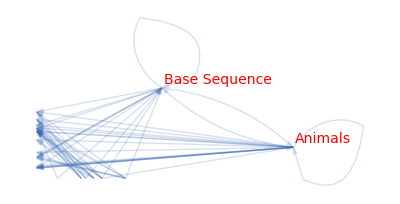

```mathematica
g[gen]=Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

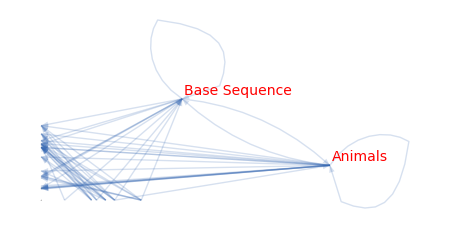

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 2005

```mathematica
gen=2005
```

2005

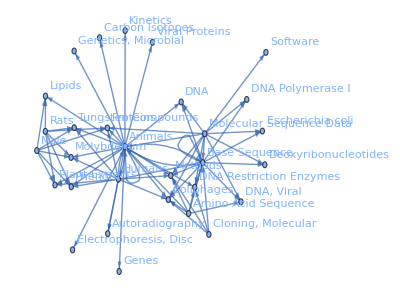

```mathematica
Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topoftopCitingCitedMeSHgraph[gen]]
```

{Animals,Proteins,Base Sequence,Molecular Sequence Data,Phenols,Tungsten Compounds,Plant Extracts,Molybdenum,DNA Restriction Enzymes,Lipids,Amino Acid Sequence,Coliphages,Methods,DNA, Viral,Cloning, Molecular,Humans,Autoradiography,DNA,Kinetics,Genes,Rats,DNA Polymerase I,Carbon Isotopes,Escherichia coli,Electrophoresis, Disc,Male,Viral Proteins,Genetics, Microbial,Deoxyribonucleotides,Software}

< edge list >

```mathematica
el[gen]=EdgeList[topoftopCitingCitedMeSHgraph[gen]]
```

{Animals->Proteins,Base Sequence->Base Sequence,Molecular Sequence Data->Base Sequence,Animals->Phenols,Animals->Tungsten Compounds,Animals->Plant Extracts,Animals->Molybdenum,Base Sequence->DNA Restriction Enzymes,Animals->Lipids,Animals->Animals,Amino Acid Sequence->Base Sequence,Base Sequence->Coliphages,Molecular Sequence Data->Coliphages,Base Sequence->Methods,Animals->Coliphages,Molecular Sequence Data->DNA Restriction Enzymes,Molecular Sequence Data->Methods,Base Sequence->DNA, Viral,Animals->Base Sequence,Amino Acid Sequence->Coliphages,Cloning, Molecular->Base Sequence,Humans->Proteins,Animals->Methods,Animals->Autoradiography,Humans->Animals,Base Sequence->DNA,Base Sequence->Animals,Amino Acid Sequence->Methods,Molecular Sequence Data->Animals,Animals->Kinetics,Amino Acid Sequence->DNA Restriction Enzymes,Molecular Sequence Data->DNA, Viral,Animals->Genes,Rats->Proteins,Animals->Humans,Base Sequence->DNA Polymerase I,Animals->Carbon Isotopes,Base Sequence->Escherichia coli,Animals->Electrophoresis, Disc,Male->Proteins,Animals->Viral Proteins,Humans->Base Sequence,Animals->DNA,Humans->Coliphages,Molecular Sequence Data->DNA,Animals->Genetics, Microbial,Cloning, Molecular->DNA Restriction Enzymes,Base Sequence->Deoxyribonucleotides,Cloning, Molecular->Coliphages,Rats->Phenols,Amino Acid Sequence->DNA, Viral,Humans->Phenols,Animals->DNA Restriction Enzymes,Molecular Sequence Data->DNA Polymerase I,Rats->Tungsten Compounds,Rats->Plant Extracts,Rats->Molybdenum,Male->Phenols,Molecular Sequence Data->Deoxyribonucleotides,Rats->Lipids,Cloning, Molecular->Methods,Male->Lipids,Amino Acid Sequence->Animals,Molecular Sequence Data->Software,Male->Tungsten Compounds,Male->Plant Extracts,Male->Molybdenum,Molecular Sequence Data->Escherichia coli,Humans->Tungsten Compounds,Humans->Plant Extracts,Humans->Molybdenum,Molecular Sequence Data->Proteins,Humans->Methods,Humans->Autoradiography}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topoftopCitingCitedMeSHgraph[gen],EdgeWeight]
```

{496.242,446.291,383.883,369.371,342.06,342.06,342.06,326.997,302.587,298.263,296.399,291.512,287.793,278.482,274.82,264.063,251.482,249.106,244.198,239.568,235.32,228.024,225.776,221.561,218.788,215.658,208.931,208.283,205.861,205.105,203.287,200.278,198.589,195.833,193.025,185.116,183.734,182.63,180.777,179.075,177.71,177.324,177.028,176.675,176.283,174.768,172.162,168.953,162.604,162.568,162.02,161.621,157.186,155.234,153.828,153.828,153.828,152.291,150.787,150.661,149.302,147.057,145.739,143.48,142.841,142.841,142.841,141.787,140.24,140.24,140.24,140.227,140.042,137.852}

```mathematica
topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

298.263 | 496.242 | 244.198 | 0 | 369.371 | 342.06 | 342.06 | 342.06 | 157.186 | 302.587 | 0 | 274.82 | 225.776 | 0 | 0 | 193.025 | 221.561 | 177.028 | 205.105 | 198.589 | 0 | 0 | 183.734 | 0 | 180.777 | 0 | 177.71 | 174.768 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
208.931 | 0 | 446.291 | 0 | 0 | 0 | 0 | 0 | 326.997 | 0 | 0 | 291.512 | 278.482 | 249.106 | 0 | 0 | 0 | 215.658 | 0 | 0 | 0 | 185.116 | 0 | 182.63 | 0 | 0 | 0 | 0 | 168.953 | 0
205.861 | 140.227 | 383.883 | 0 | 0 | 0 | 0 | 0 | 264.063 | 0 | 0 | 287.793 | 251.482 | 200.278 | 0 | 0 | 0 | 176.283 | 0 | 0 | 0 | 155.234 | 0 | 141.787 | 0 | 0 | 0 | 0 | 150.787 | 143.48
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
145.739 | 0 | 296.399 | 0 | 0 | 0 | 0 | 0 | 203.287 | 0 | 0 | 239.568 | 208.283 | 162.02 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 235.32 | 0 | 0 | 0 | 0 | 0 | 172.162 | 0 | 0 | 162.604 | 149.302 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
218.788 | 228.024 | 177.324 | 0 | 161.621 | 140.24 | 140.24 | 140.24 | 0 | 0 | 0 | 176.675 | 140.042 | 0 | 0 | 0 | 137.852 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 195.833 | 0 | 0 | 162.568 | 153.828 | 153.828 | 153.828 | 0 | 150.661 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 179.075 | 0 | 0 | 152.291 | 142.841 | 142.841 | 142.841 | 0 | 147.057 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{5106.92,0,2553.68,2501.16,0,0,0,0,0,0,1255.3,0,0,0,719.388,1661.05,0,0,0,0,970.548,0,0,0,0,906.947,0,0,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Animals

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{1077.58,1239.4,1783.42,0,845.851,778.97,778.97,778.97,1123.7,600.305,0,1432.97,1253.37,611.405,0,193.025,359.413,568.968,205.105,198.589,0,340.35,183.734,324.417,180.777,0,177.71,174.768,319.74,143.48}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Base Sequence

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{6184.5,1239.4,4337.09,2501.16,845.851,778.97,778.97,778.97,1123.7,600.305,1255.3,1432.97,1253.37,611.405,719.388,1854.07,359.413,568.968,205.105,198.589,970.548,340.35,183.734,324.417,180.777,906.947,177.71,174.768,319.74,143.48}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{5106.92,1077.58},{0,1239.4},{2553.68,1783.42},{2501.16,0},{0,845.851},{0,778.97},{0,778.97},{0,778.97},{0,1123.7},{0,600.305},{1255.3,0},{0,1432.97},{0,1253.37},{0,611.405},{719.388,0},{1661.05,193.025},{0,359.413},{0,568.968},{0,205.105},{0,198.589},{970.548,0},{0,340.35},{0,183.734},{0,324.417},{0,180.777},{906.947,0},{0,177.71},{0,174.768},{0,319.74},{0,143.48}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

540.936

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Animals->Proteins→Thickness[0.620302],Base Sequence->Base Sequence→Thickness[0.557863],Molecular Sequence Data->Base Sequence→Thickness[0.479854],Animals->Phenols→Thickness[0.461714],Animals->Tungsten Compounds→Thickness[0.427575],Animals->Plant Extracts→Thickness[0.427575],Animals->Molybdenum→Thickness[0.427575],Base Sequence->DNA Restriction Enzymes→Thickness[0.408747],Animals->Lipids→Thickness[0.378234],Animals->Animals→Thickness[0.372829],Amino Acid Sequence->Base Sequence→Thickness[0.370499],Base Sequence->Coliphages→Thickness[0.36439],Molecular Sequence Data->Coliphages→Thickness[0.359741],Base Sequence->Methods→Thickness[0.348102],Animals->Coliphages→Thickness[0.343525],Molecular Sequence Data->DNA Restriction Enzymes→Thickness[0.330079],Molecular Sequence Data->Methods→Thickness[0.314352],Base Sequence->DNA, Viral→Thickness[0.311383],Animals->Base Sequence→Thickness[0.305248],Amino Acid Sequence->Coliphages→Thickness[0.29946],Cloning, Molecular->Base Sequence→Thickness[0.29415],Humans->Proteins→Thickness[0.285031],Animals->Methods→Thickness[0.282221],Animals->Autoradiography→Thickness[0.276951],Humans->Animals→Thickness[0.273485],Base Sequence->DNA→Thickness[0.269573],Base Sequence->Animals→Thickness[0.261164],Amino Acid Sequence->Methods→Thickness[0.260354],Molecular Sequence Data->Animals→Thickness[0.257326],Animals->Kinetics→Thickness[0.256381],Amino Acid Sequence->DNA Restriction Enzymes→Thickness[0.254109],Molecular Sequence Data->DNA, Viral→Thickness[0.250347],Animals->Genes→Thickness[0.248236],Rats->Proteins→Thickness[0.244791],Animals->Humans→Thickness[0.241281],Base Sequence->DNA Polymerase I→Thickness[0.231395],Animals->Carbon Isotopes→Thickness[0.229667],Base Sequence->Escherichia coli→Thickness[0.228288],Animals->Electrophoresis, Disc→Thickness[0.225971],Male->Proteins→Thickness[0.223844],Animals->Viral Proteins→Thickness[0.222137],Humans->Base Sequence→Thickness[0.221655],Animals->DNA→Thickness[0.221285],Humans->Coliphages→Thickness[0.220844],Molecular Sequence Data->DNA→Thickness[0.220353],Animals->Genetics, Microbial→Thickness[0.21846],Cloning, Molecular->DNA Restriction Enzymes→Thickness[0.215202],Base Sequence->Deoxyribonucleotides→Thickness[0.211191],Cloning, Molecular->Coliphages→Thickness[0.203255],Rats->Phenols→Thickness[0.20321],Amino Acid Sequence->DNA, Viral→Thickness[0.202526],Humans->Phenols→Thickness[0.202026],Animals->DNA Restriction Enzymes→Thickness[0.196483],Molecular Sequence Data->DNA Polymerase I→Thickness[0.194043],Rats->Tungsten Compounds→Thickness[0.192285],Rats->Plant Extracts→Thickness[0.192285],Rats->Molybdenum→Thickness[0.192285],Male->Phenols→Thickness[0.190364],Molecular Sequence Data->Deoxyribonucleotides→Thickness[0.188484],Rats->Lipids→Thickness[0.188327],Cloning, Molecular->Methods→Thickness[0.186628],Male->Lipids→Thickness[0.183821],Amino Acid Sequence->Animals→Thickness[0.182174],Molecular Sequence Data->Software→Thickness[0.17935],Male->Tungsten Compounds→Thickness[0.178552],Male->Plant Extracts→Thickness[0.178552],Male->Molybdenum→Thickness[0.178552],Molecular Sequence Data->Escherichia coli→Thickness[0.177233],Humans->Tungsten Compounds→Thickness[0.1753],Humans->Plant Extracts→Thickness[0.1753],Humans->Molybdenum→Thickness[0.1753],Molecular Sequence Data->Proteins→Thickness[0.175283],Humans->Methods→Thickness[0.175053],Humans->Autoradiography→Thickness[0.172315]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Animals→Animals,Base Sequence→Base Sequence}

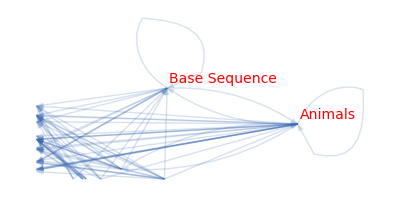

```mathematica
g[gen]=Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

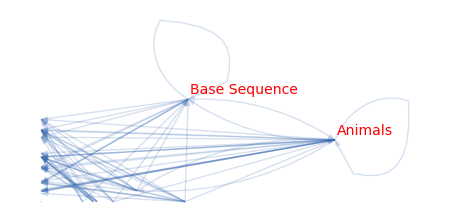

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 2010

```mathematica
gen=2010
```

2010

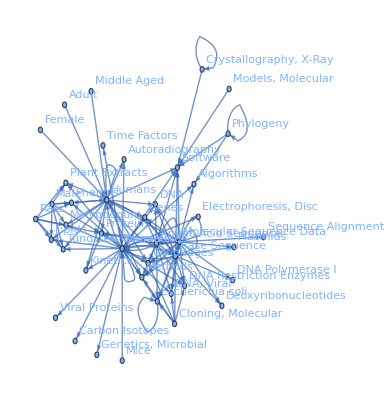

```mathematica
Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topoftopCitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Proteins,Base Sequence,Molecular Sequence Data,Phenols,Software,DNA Restriction Enzymes,Lipids,Tungsten Compounds,Plant Extracts,Molybdenum,Amino Acid Sequence,Coliphages,Female,Male,Methods,DNA, Viral,Cloning, Molecular,DNA,Genes,Kinetics,Escherichia coli,Autoradiography,Rats,Algorithms,Models, Molecular,Carbon Isotopes,Electrophoresis, Disc,Viral Proteins,Genetics, Microbial,Phylogeny,Crystallography, X-Ray,DNA Polymerase I,Time Factors,Deoxyribonucleotides,Middle Aged,Adult,Plasmids,Mice,Sequence Alignment}

< edge list >

```mathematica
el[gen]=EdgeList[topoftopCitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Proteins,Base Sequence->Base Sequence,Animals->Animals,Molecular Sequence Data->Base Sequence,Animals->Humans,Humans->Animals,Animals->Phenols,Molecular Sequence Data->Software,Base Sequence->DNA Restriction Enzymes,Animals->Lipids,Animals->Tungsten Compounds,Animals->Plant Extracts,Animals->Molybdenum,Amino Acid Sequence->Base Sequence,Animals->Base Sequence,Humans->Proteins,Base Sequence->Coliphages,Female->Humans,Molecular Sequence Data->Coliphages,Animals->Coliphages,Male->Humans,Molecular Sequence Data->Animals,Molecular Sequence Data->DNA Restriction Enzymes,Base Sequence->Methods,Base Sequence->DNA, Viral,Animals->Software,Amino Acid Sequence->Software,Molecular Sequence Data->Proteins,Cloning, Molecular->Base Sequence,Base Sequence->DNA,Molecular Sequence Data->Methods,Amino Acid Sequence->Coliphages,Base Sequence->Animals,Molecular Sequence Data->Amino Acid Sequence,Animals->Methods,Animals->Genes,Animals->Kinetics,Humans->Base Sequence,Base Sequence->Escherichia coli,Animals->DNA,Animals->Autoradiography,Molecular Sequence Data->DNA,Humans->Software,Amino Acid Sequence->Proteins,Rats->Proteins,Amino Acid Sequence->DNA Restriction Enzymes,Amino Acid Sequence->Methods,Molecular Sequence Data->DNA, Viral,Male->Proteins,Molecular Sequence Data->Escherichia coli,Molecular Sequence Data->Algorithms,Models, Molecular->Software,Amino Acid Sequence->Amino Acid Sequence,Amino Acid Sequence->Animals,Animals->Carbon Isotopes,Animals->Electrophoresis, Disc,Humans->Coliphages,Animals->Viral Proteins,Animals->Genetics, Microbial,Cloning, Molecular->DNA Restriction Enzymes,Phylogeny->Software,Crystallography, X-Ray->Software,Animals->Algorithms,Base Sequence->DNA Polymerase I,Humans->DNA,Animals->DNA Restriction Enzymes,Molecular Sequence Data->Humans,Cloning, Molecular->Coliphages,Animals->Time Factors,Humans->Genes,Base Sequence->Deoxyribonucleotides,Molecular Sequence Data->Genes,Amino Acid Sequence->DNA, Viral,Middle Aged->Humans,Male->Lipids,Rats->Phenols,Animals->Escherichia coli,Animals->Amino Acid Sequence,Humans->Phenols,Adult->Humans,Base Sequence->Plasmids,Rats->Lipids,Phylogeny->Algorithms,Humans->Methods,Amino Acid Sequence->Escherichia coli,Amino Acid Sequence->DNA,Male->Phenols,Rats->Tungsten Compounds,Rats->Plant Extracts,Rats->Molybdenum,Base Sequence->Software,Escherichia coli->Escherichia coli,Molecular Sequence Data->Molecular Sequence Data,Cloning, Molecular->Escherichia coli,Animals->DNA, Viral,Humans->Kinetics,Mice->Animals,Cloning, Molecular->Methods,Molecular Sequence Data->DNA Polymerase I,Molecular Sequence Data->Deoxyribonucleotides,Phylogeny->Phylogeny,Male->Tungsten Compounds,Male->Plant Extracts,Male->Molybdenum,Molecular Sequence Data->Plasmids,Crystallography, X-Ray->Crystallography, X-Ray,Kinetics->Proteins,Humans->Autoradiography,Humans->Lipids,Humans->Tungsten Compounds,Humans->Plant Extracts,Humans->Molybdenum,Base Sequence->Humans,Cloning, Molecular->DNA, Viral,Amino Acid Sequence->Genes,Molecular Sequence Data->Sequence Alignment,Base Sequence->Genes}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topoftopCitingCitedMeSHgraph[gen],EdgeWeight]
```

{707.785,655.514,542.527,508.33,481.565,415.023,396.539,396.406,381.586,370.148,369.574,365.307,365.307,365.307,353.858,345.565,341.846,325.71,320.595,312.782,308.931,305.837,296.604,290.432,290.201,282.183,279.574,277.035,274.48,270.977,267.918,266.981,263.896,263.854,263.425,261.097,257.641,257.095,256.115,253.404,247.771,240.391,239.507,236.858,230.057,227.84,224.588,220.239,214.859,211.769,209.396,207.354,206.096,204.125,203.542,201.61,200.538,198.638,197.672,195.117,193.712,191.762,187.748,187.184,186.972,185.599,185.581,184.79,181.864,179.326,178.63,178.626,177.954,177.215,177.16,176.775,175.64,175.49,174.596,173.95,173.83,172.186,170.941,169.848,168.833,168.629,166.328,166.236,165.787,165.787,165.787,165.036,164.861,164.829,164.335,161.011,160.614,159.539,158.266,157.412,156.793,155.179,155.101,155.101,155.101,153.066,152.665,150.771,150.61,150.295,149.894,149.894,149.894,149.623,149.598,148.002,145.807,144.713}

```mathematica
topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

707.785 | 396.539 | 341.846 | 256.115 | 0 | 173.95 | 236.858 | 0 | 150.295 | 149.894 | 149.894 | 149.894 | 0 | 198.638 | 0 | 0 | 168.833 | 0 | 0 | 185.599 | 178.63 | 160.614 | 0 | 150.61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
415.023 | 508.33 | 655.514 | 345.565 | 0 | 396.406 | 279.574 | 185.581 | 369.574 | 365.307 | 365.307 | 365.307 | 174.596 | 308.931 | 0 | 0 | 261.097 | 161.011 | 0 | 247.771 | 257.641 | 257.095 | 175.49 | 240.391 | 0 | 187.184 | 0 | 201.61 | 200.538 | 197.672 | 195.117 | 0 | 0 | 0 | 179.326 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
149.623 | 263.854 | 0 | 542.527 | 0 | 0 | 165.036 | 370.148 | 0 | 0 | 0 | 0 | 0 | 325.71 | 0 | 0 | 290.201 | 282.183 | 0 | 267.918 | 144.713 | 0 | 253.404 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 186.972 | 0 | 178.626 | 0 | 0 | 172.186 | 0 | 0
184.79 | 296.604 | 274.48 | 481.565 | 164.829 | 0 | 381.586 | 290.432 | 0 | 0 | 0 | 0 | 263.425 | 312.782 | 0 | 0 | 266.981 | 214.859 | 0 | 239.507 | 177.954 | 0 | 209.396 | 0 | 0 | 207.354 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 157.412 | 0 | 156.793 | 0 | 0 | 153.066 | 0 | 145.807
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 203.542 | 230.057 | 353.858 | 0 | 0 | 277.035 | 224.588 | 0 | 0 | 0 | 0 | 204.125 | 263.896 | 0 | 0 | 220.239 | 177.215 | 0 | 166.328 | 148.002 | 0 | 168.629 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
320.595 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
305.837 | 0 | 211.769 | 0 | 0 | 166.236 | 0 | 0 | 176.775 | 155.101 | 155.101 | 155.101 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 270.977 | 0 | 0 | 0 | 193.712 | 0 | 0 | 0 | 0 | 0 | 181.864 | 0 | 0 | 158.266 | 149.598 | 0 | 0 | 0 | 0 | 164.335 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 150.771 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 164.861 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 227.84 | 0 | 0 | 175.64 | 0 | 0 | 170.941 | 165.787 | 165.787 | 165.787 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 206.096 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 191.762 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 169.848 | 0 | 0 | 0 | 0 | 0 | 155.179 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 187.748 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 152.665 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
177.16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
173.83 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 159.539 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{3755.99,7496.96,0,3593.1,4579.62,0,0,0,0,0,0,0,2637.51,0,320.595,1325.92,0,0,1118.75,0,0,150.771,164.861,0,1071.78,0,206.096,0,0,0,0,516.789,340.413,0,0,0,177.16,173.83,0,159.539,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Animals

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{2434.64,1828.41,2092.28,2250.61,164.829,912.232,1925.7,1264.46,867.586,836.088,836.088,836.088,642.146,1591.82,0,0,1365.62,984.866,0,1107.12,906.939,417.71,1136.12,391.001,0,564.386,0,201.61,200.538,197.672,195.117,155.179,152.665,344.384,179.326,335.419,0,0,325.252,0,145.807}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{6190.63,9325.37,2092.28,5843.71,4744.45,912.232,1925.7,1264.46,867.586,836.088,836.088,836.088,3279.66,1591.82,320.595,1325.92,1365.62,984.866,1118.75,1107.12,906.939,568.481,1300.98,391.001,1071.78,564.386,206.096,201.61,200.538,197.672,195.117,671.968,493.077,344.384,179.326,335.419,177.16,173.83,325.252,159.539,145.807}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{3755.99,2434.64},{7496.96,1828.41},{0,2092.28},{3593.1,2250.61},{4579.62,164.829},{0,912.232},{0,1925.7},{0,1264.46},{0,867.586},{0,836.088},{0,836.088},{0,836.088},{2637.51,642.146},{0,1591.82},{320.595,0},{1325.92,0},{0,1365.62},{0,984.866},{1118.75,0},{0,1107.12},{0,906.939},{150.771,417.71},{164.861,1136.12},{0,391.001},{1071.78,0},{0,564.386},{206.096,0},{0,201.61},{0,200.538},{0,197.672},{0,195.117},{516.789,155.179},{340.413,152.665},{0,344.384},{0,179.326},{0,335.419},{177.16,0},{173.83,0},{0,325.252},{159.539,0},{0,145.807}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

788.238

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.884731],Animals->Proteins→Thickness[0.819393],Base Sequence->Base Sequence→Thickness[0.678159],Animals->Animals→Thickness[0.635413],Molecular Sequence Data->Base Sequence→Thickness[0.601956],Animals->Humans→Thickness[0.518779],Humans->Animals→Thickness[0.495674],Animals->Phenols→Thickness[0.495508],Molecular Sequence Data->Software→Thickness[0.476983],Base Sequence->DNA Restriction Enzymes→Thickness[0.462685],Animals->Lipids→Thickness[0.461968],Animals->Tungsten Compounds→Thickness[0.456634],Animals->Plant Extracts→Thickness[0.456634],Animals->Molybdenum→Thickness[0.456634],Amino Acid Sequence->Base Sequence→Thickness[0.442322],Animals->Base Sequence→Thickness[0.431956],Humans->Proteins→Thickness[0.427307],Base Sequence->Coliphages→Thickness[0.407138],Female->Humans→Thickness[0.400744],Molecular Sequence Data->Coliphages→Thickness[0.390978],Animals->Coliphages→Thickness[0.386164],Male->Humans→Thickness[0.382296],Molecular Sequence Data->Animals→Thickness[0.370756],Molecular Sequence Data->DNA Restriction Enzymes→Thickness[0.36304],Base Sequence->Methods→Thickness[0.362751],Base Sequence->DNA, Viral→Thickness[0.352729],Animals->Software→Thickness[0.349468],Amino Acid Sequence->Software→Thickness[0.346294],Molecular Sequence Data->Proteins→Thickness[0.3431],Cloning, Molecular->Base Sequence→Thickness[0.338721],Base Sequence->DNA→Thickness[0.334897],Molecular Sequence Data->Methods→Thickness[0.333726],Amino Acid Sequence->Coliphages→Thickness[0.329871],Base Sequence->Animals→Thickness[0.329818],Molecular Sequence Data->Amino Acid Sequence→Thickness[0.329282],Animals->Methods→Thickness[0.326371],Animals->Genes→Thickness[0.322051],Animals->Kinetics→Thickness[0.321369],Humans->Base Sequence→Thickness[0.320144],Base Sequence->Escherichia coli→Thickness[0.316756],Animals->DNA→Thickness[0.309714],Animals->Autoradiography→Thickness[0.300489],Molecular Sequence Data->DNA→Thickness[0.299384],Humans->Software→Thickness[0.296072],Amino Acid Sequence->Proteins→Thickness[0.287571],Rats->Proteins→Thickness[0.2848],Amino Acid Sequence->DNA Restriction Enzymes→Thickness[0.280734],Amino Acid Sequence->Methods→Thickness[0.275298],Molecular Sequence Data->DNA, Viral→Thickness[0.268574],Male->Proteins→Thickness[0.264711],Molecular Sequence Data->Escherichia coli→Thickness[0.261745],Molecular Sequence Data->Algorithms→Thickness[0.259192],Models, Molecular->Software→Thickness[0.25762],Amino Acid Sequence->Amino Acid Sequence→Thickness[0.255156],Amino Acid Sequence->Animals→Thickness[0.254428],Animals->Carbon Isotopes→Thickness[0.252013],Animals->Electrophoresis, Disc→Thickness[0.250672],Humans->Coliphages→Thickness[0.248297],Animals->Viral Proteins→Thickness[0.247091],Animals->Genetics, Microbial→Thickness[0.243896],Cloning, Molecular->DNA Restriction Enzymes→Thickness[0.24214],Phylogeny->Software→Thickness[0.239702],Crystallography, X-Ray->Software→Thickness[0.234685],Animals->Algorithms→Thickness[0.23398],Base Sequence->DNA Polymerase I→Thickness[0.233716],Humans->DNA→Thickness[0.231999],Animals->DNA Restriction Enzymes→Thickness[0.231977],Molecular Sequence Data->Humans→Thickness[0.230988],Cloning, Molecular->Coliphages→Thickness[0.227329],Animals->Time Factors→Thickness[0.224158],Humans->Genes→Thickness[0.223287],Base Sequence->Deoxyribonucleotides→Thickness[0.223283],Molecular Sequence Data->Genes→Thickness[0.222442],Amino Acid Sequence->DNA, Viral→Thickness[0.221519],Middle Aged->Humans→Thickness[0.22145],Male->Lipids→Thickness[0.220969],Rats->Phenols→Thickness[0.21955],Animals->Escherichia coli→Thickness[0.219363],Animals->Amino Acid Sequence→Thickness[0.218245],Humans->Phenols→Thickness[0.217437],Adult->Humans→Thickness[0.217287],Base Sequence->Plasmids→Thickness[0.215232],Rats->Lipids→Thickness[0.213677],Phylogeny->Algorithms→Thickness[0.212311],Humans->Methods→Thickness[0.211041],Amino Acid Sequence->Escherichia coli→Thickness[0.210787],Amino Acid Sequence->DNA→Thickness[0.20791],Male->Phenols→Thickness[0.207795],Rats->Tungsten Compounds→Thickness[0.207233],Rats->Plant Extracts→Thickness[0.207233],Rats->Molybdenum→Thickness[0.207233],Base Sequence->Software→Thickness[0.206295],Escherichia coli->Escherichia coli→Thickness[0.206076],Molecular Sequence Data->Molecular Sequence Data→Thickness[0.206036],Cloning, Molecular->Escherichia coli→Thickness[0.205419],Animals->DNA, Viral→Thickness[0.201264],Humans->Kinetics→Thickness[0.200768],Mice->Animals→Thickness[0.199424],Cloning, Molecular->Methods→Thickness[0.197832],Molecular Sequence Data->DNA Polymerase I→Thickness[0.196765],Molecular Sequence Data->Deoxyribonucleotides→Thickness[0.195991],Phylogeny->Phylogeny→Thickness[0.193974],Male->Tungsten Compounds→Thickness[0.193876],Male->Plant Extracts→Thickness[0.193876],Male->Molybdenum→Thickness[0.193876],Molecular Sequence Data->Plasmids→Thickness[0.191332],Crystallography, X-Ray->Crystallography, X-Ray→Thickness[0.190831],Kinetics->Proteins→Thickness[0.188464],Humans->Autoradiography→Thickness[0.188262],Humans->Lipids→Thickness[0.187869],Humans->Tungsten Compounds→Thickness[0.187367],Humans->Plant Extracts→Thickness[0.187367],Humans->Molybdenum→Thickness[0.187367],Base Sequence->Humans→Thickness[0.187028],Cloning, Molecular->DNA, Viral→Thickness[0.186997],Amino Acid Sequence->Genes→Thickness[0.185002],Molecular Sequence Data->Sequence Alignment→Thickness[0.182259],Base Sequence->Genes→Thickness[0.180891]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Animals→Animals,Humans→Humans}

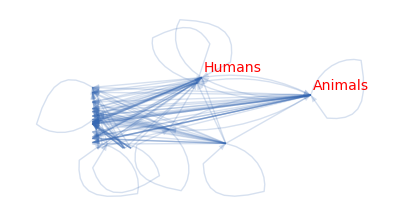

```mathematica
g[gen]=Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

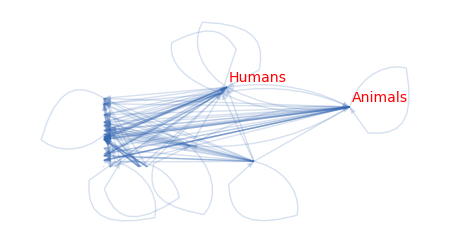

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 2015

```mathematica
gen=2015
```

2015

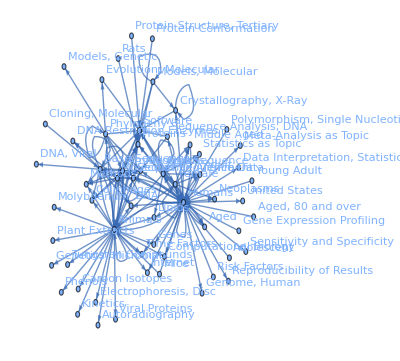

```mathematica
Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topoftopCitingCitedMeSHgraph[gen]]
```

{Humans,Female,Male,Animals,Software,Proteins,Middle Aged,Adult,Molecular Sequence Data,Algorithms,Neoplasms,Aged,Statistics as Topic,Base Sequence,Lipids,Phylogeny,Amino Acid Sequence,Crystallography, X-Ray,Phenols,Models, Molecular,Tungsten Compounds,Plant Extracts,Molybdenum,Reproducibility of Results,Sequence Alignment,Mice,Time Factors,DNA Restriction Enzymes,Genes,Coliphages,Sequence Analysis, DNA,Methods,DNA,Kinetics,Data Interpretation, Statistical,United States,Gene Expression Profiling,Internet,Protein Structure, Tertiary,Autoradiography,Sensitivity and Specificity,Rats,Meta-Analysis as Topic,Cloning, Molecular,DNA, Viral,Polymorphism, Single Nucleotide,Adolescent,Protein Conformation,Viral Proteins,Risk Factors,Evolution, Molecular,Young Adult,Genome, Human,Models, Genetic,Carbon Isotopes,Aged, 80 and over,Electrophoresis, Disc,Computational Biology,Genetics, Microbial}

< edge list >

```mathematica
el[gen]=EdgeList[topoftopCitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Female->Humans,Male->Humans,Animals->Humans,Humans->Animals,Animals->Animals,Humans->Software,Animals->Proteins,Animals->Software,Middle Aged->Humans,Adult->Humans,Molecular Sequence Data->Software,Humans->Female,Animals->Algorithms,Humans->Neoplasms,Aged->Humans,Humans->Male,Humans->Algorithms,Humans->Statistics as Topic,Base Sequence->Base Sequence,Humans->Proteins,Animals->Lipids,Humans->Adult,Phylogeny->Software,Molecular Sequence Data->Base Sequence,Amino Acid Sequence->Software,Crystallography, X-Ray->Crystallography, X-Ray,Phylogeny->Algorithms,Animals->Base Sequence,Animals->Phenols,Models, Molecular->Software,Molecular Sequence Data->Algorithms,Humans->Middle Aged,Animals->Tungsten Compounds,Animals->Plant Extracts,Animals->Molybdenum,Molecular Sequence Data->Animals,Humans->Base Sequence,Molecular Sequence Data->Proteins,Humans->Reproducibility of Results,Molecular Sequence Data->Amino Acid Sequence,Models, Molecular->Crystallography, X-Ray,Crystallography, X-Ray->Software,Female->Female,Animals->Sequence Alignment,Humans->Aged,Mice->Humans,Animals->Time Factors,Phylogeny->Phylogeny,Base Sequence->DNA Restriction Enzymes,Phylogeny->Sequence Alignment,Animals->Genes,Amino Acid Sequence->Base Sequence,Base Sequence->Animals,Animals->Amino Acid Sequence,Animals->Coliphages,Animals->Molecular Sequence Data,Molecular Sequence Data->Coliphages,Molecular Sequence Data->Sequence Alignment,Humans->Sequence Alignment,Amino Acid Sequence->Proteins,Male->Female,Mice->Animals,Sequence Analysis, DNA->Software,Base Sequence->Coliphages,Female->Adult,Female->Male,Base Sequence->Software,Animals->Methods,Humans->Molecular Sequence Data,Male->Male,Animals->DNA,Humans->Amino Acid Sequence,Male->Adult,Base Sequence->Methods,Molecular Sequence Data->DNA Restriction Enzymes,Molecular Sequence Data->Humans,Animals->Kinetics,Humans->Genes,Molecular Sequence Data->Molecular Sequence Data,Humans->Time Factors,Amino Acid Sequence->Amino Acid Sequence,Humans->Data Interpretation, Statistical,Molecular Sequence Data->Methods,Humans->United States,Gene Expression Profiling->Humans,Animals->Internet,Protein Structure, Tertiary->Software,Humans->DNA,Animals->Autoradiography,Amino Acid Sequence->Coliphages,Female->Software,Male->Proteins,Sequence Analysis, DNA->Algorithms,Female->Animals,Molecular Sequence Data->DNA,Female->Statistics as Topic,Models, Molecular->Proteins,Humans->Sensitivity and Specificity,Models, Molecular->Models, Molecular,Base Sequence->DNA,Rats->Proteins,Male->Lipids,Humans->Internet,Humans->Meta-Analysis as Topic,Cloning, Molecular->Base Sequence,Humans->Sequence Analysis, DNA,Animals->Phylogeny,Female->Middle Aged,Base Sequence->DNA, Viral,Male->Software,Polymorphism, Single Nucleotide->Humans,Male->Animals,Amino Acid Sequence->Animals,Amino Acid Sequence->Algorithms,Adolescent->Humans,Protein Conformation->Software,Animals->Viral Proteins,Risk Factors->Humans,Phylogeny->Evolution, Molecular,Phylogeny->Amino Acid Sequence,Young Adult->Humans,Evolution, Molecular->Software,Male->Middle Aged,Female->Neoplasms,Humans->Genome, Human,Phylogeny->Models, Genetic,Male->Statistics as Topic,Animals->Carbon Isotopes,Aged, 80 and over->Humans,Amino Acid Sequence->Methods,Animals->Electrophoresis, Disc,Female->Aged,Sequence Alignment->Software,Humans->Computational Biology,Animals->Computational Biology,Humans->Lipids,Humans->Crystallography, X-Ray,Animals->Genetics, Microbial,Base Sequence->Humans}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topoftopCitingCitedMeSHgraph[gen],EdgeWeight]
```

{2946.35,1391.85,1252.91,1071.39,953.397,951.686,879.946,808.623,762.814,746.997,731.396,697.582,662.085,608.646,578.731,566.782,560.652,557.174,549.633,511.898,509.833,497.782,495.926,482.292,476.172,461.949,460.15,438.154,435.055,430.565,430.008,427.79,399.159,396.295,396.295,396.295,390.01,379.609,379.075,368.703,365.915,365.253,364.417,364.18,363.027,353.854,353.11,345.467,341.318,333.154,329.652,328.647,324.216,316.797,316.634,314.423,312.694,311.511,311.395,311.085,309.158,307.838,301.281,300.603,300.224,300.179,299.282,295.454,294.495,290.876,290.471,287.669,281.639,280.976,275.385,272.602,271.602,270.991,268.824,268.749,268.703,264.798,264.689,264.533,263.157,260.571,260.117,259.687,259.489,258.592,257.53,254.559,252.993,252.381,252.322,251.819,250.802,250.24,249.812,248.197,247.913,247.696,246.133,245.209,240.27,239.792,238.99,238.951,238.437,238.064,237.94,235.65,235.421,233.933,232.706,231.569,230.708,225.472,225.257,224.566,224.395,224.091,222.961,221.822,221.001,220.102,219.689,219.442,218.939,217.356,216.225,215.644,215.246,212.914,212.772,212.382,212.007,211.022,209.343,208.823}

```mathematica
topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

2946.35 | 662.085 | 560.652 | 953.397 | 879.946 | 509.833 | 399.159 | 495.926 | 290.876 | 557.174 | 578.731 | 353.854 | 549.633 | 379.609 | 212.007 | 0 | 281.639 | 211.022 | 0 | 0 | 0 | 0 | 0 | 368.703 | 311.085 | 0 | 268.703 | 0 | 268.824 | 0 | 238.99 | 0 | 259.489 | 0 | 264.689 | 263.157 | 0 | 245.209 | 0 | 0 | 249.812 | 0 | 240.27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 220.102 | 0 | 0 | 0 | 0 | 212.772 | 0
1391.85 | 364.18 | 299.282 | 252.322 | 254.559 | 0 | 238.437 | 300.179 | 0 | 0 | 221.001 | 215.246 | 250.802 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1252.91 | 307.838 | 290.471 | 235.421 | 237.94 | 252.993 | 221.822 | 280.976 | 0 | 0 | 0 | 0 | 219.442 | 0 | 246.133 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1071.39 | 0 | 0 | 951.686 | 762.814 | 808.623 | 0 | 0 | 312.694 | 608.646 | 0 | 0 | 0 | 435.055 | 497.782 | 238.951 | 316.634 | 0 | 430.565 | 0 | 396.295 | 396.295 | 396.295 | 0 | 363.027 | 0 | 345.467 | 0 | 328.647 | 314.423 | 0 | 294.495 | 287.669 | 270.991 | 0 | 0 | 0 | 260.117 | 0 | 258.592 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 225.472 | 0 | 0 | 0 | 0 | 0 | 218.939 | 0 | 215.644 | 212.382 | 209.343
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
746.997 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
731.396 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
271.602 | 0 | 0 | 390.01 | 697.582 | 379.075 | 0 | 0 | 268.749 | 427.79 | 0 | 0 | 0 | 476.172 | 0 | 0 | 365.915 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 311.395 | 0 | 0 | 272.602 | 0 | 311.511 | 0 | 264.533 | 251.819 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
566.782 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
208.823 | 0 | 0 | 316.797 | 295.454 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 511.898 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 333.154 | 0 | 300.224 | 0 | 275.385 | 247.913 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 238.064 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 482.292 | 0 | 0 | 0 | 0 | 438.154 | 0 | 0 | 0 | 0 | 0 | 341.318 | 224.395 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 329.652 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 224.566 | 0 | 0 | 219.689 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 233.933 | 461.949 | 309.158 | 0 | 0 | 0 | 232.706 | 0 | 0 | 0 | 324.216 | 0 | 0 | 264.798 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 257.53 | 0 | 216.225 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 364.417 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 460.15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 430.008 | 250.24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 365.253 | 0 | 248.197 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 212.914 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
353.11 | 0 | 0 | 301.281 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 300.603 | 0 | 0 | 0 | 0 | 252.381 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
260.571 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 259.687 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 247.696 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 239.792 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
235.65 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
231.569 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 230.708 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
225.257 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 222.961 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
224.091 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
217.356 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{14233.7,3787.86,3545.95,11428.9,0,0,746.997,731.396,4688.75,0,0,566.782,0,2727.71,0,2260.07,2300.52,824.567,0,1293.7,0,0,0,0,212.914,654.391,0,0,0,0,552.983,0,0,0,0,0,260.571,0,259.687,0,0,247.696,0,239.792,0,235.65,231.569,230.708,0,225.257,222.961,224.091,0,0,0,217.356,0,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{10935.7,1334.1,1150.4,3634.85,6093.83,2757.62,859.417,1077.08,872.318,2516.85,799.732,569.1,1019.88,2366.74,955.923,580.269,1453.38,1036.42,430.565,248.197,396.295,396.295,396.295,368.703,1315.16,0,614.17,605.756,597.471,1183.69,238.99,1050.64,1046.89,270.991,264.689,263.157,0,505.326,0,258.592,249.812,0,240.27,0,238.064,0,0,0,225.472,0,224.566,0,220.102,219.689,218.939,0,215.644,425.155,209.343}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{25169.4,5121.96,4696.36,15063.8,6093.83,2757.62,1606.41,1808.48,5561.07,2516.85,799.732,1135.88,1019.88,5094.46,955.923,2840.33,3753.9,1860.99,430.565,1541.89,396.295,396.295,396.295,368.703,1528.07,654.391,614.17,605.756,597.471,1183.69,791.973,1050.64,1046.89,270.991,264.689,263.157,260.571,505.326,259.687,258.592,249.812,247.696,240.27,239.792,238.064,235.65,231.569,230.708,225.472,225.257,447.527,224.091,220.102,219.689,218.939,217.356,215.644,425.155,209.343}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{14233.7,10935.7},{3787.86,1334.1},{3545.95,1150.4},{11428.9,3634.85},{0,6093.83},{0,2757.62},{746.997,859.417},{731.396,1077.08},{4688.75,872.318},{0,2516.85},{0,799.732},{566.782,569.1},{0,1019.88},{2727.71,2366.74},{0,955.923},{2260.07,580.269},{2300.52,1453.38},{824.567,1036.42},{0,430.565},{1293.7,248.197},{0,396.295},{0,396.295},{0,396.295},{0,368.703},{212.914,1315.16},{654.391,0},{0,614.17},{0,605.756},{0,597.471},{0,1183.69},{552.983,238.99},{0,1050.64},{0,1046.89},{0,270.991},{0,264.689},{0,263.157},{260.571,0},{0,505.326},{259.687,0},{0,258.592},{0,249.812},{247.696,0},{0,240.27},{239.792,0},{0,238.064},{235.65,0},{231.569,0},{230.708,0},{0,225.472},{225.257,0},{222.961,224.566},{224.091,0},{0,220.102},{0,219.689},{0,218.939},{217.356,0},{0,215.644},{0,425.155},{0,209.343}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

1794.96

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[3.68293],Female->Humans→Thickness[1.73981],Male->Humans→Thickness[1.56614],Animals->Humans→Thickness[1.33923],Humans->Animals→Thickness[1.19175],Animals->Animals→Thickness[1.18961],Humans->Software→Thickness[1.09993],Animals->Proteins→Thickness[1.01078],Animals->Software→Thickness[0.953518],Middle Aged->Humans→Thickness[0.933746],Adult->Humans→Thickness[0.914246],Molecular Sequence Data->Software→Thickness[0.871978],Humans->Female→Thickness[0.827607],Animals->Algorithms→Thickness[0.760807],Humans->Neoplasms→Thickness[0.723414],Aged->Humans→Thickness[0.708478],Humans->Male→Thickness[0.700815],Humans->Algorithms→Thickness[0.696467],Humans->Statistics as Topic→Thickness[0.687041],Base Sequence->Base Sequence→Thickness[0.639872],Humans->Proteins→Thickness[0.637291],Animals->Lipids→Thickness[0.622228],Humans->Adult→Thickness[0.619908],Phylogeny->Software→Thickness[0.602865],Molecular Sequence Data->Base Sequence→Thickness[0.595215],Amino Acid Sequence->Software→Thickness[0.577436],Crystallography, X-Ray->Crystallography, X-Ray→Thickness[0.575188],Phylogeny->Algorithms→Thickness[0.547693],Animals->Base Sequence→Thickness[0.543819],Animals->Phenols→Thickness[0.538206],Models, Molecular->Software→Thickness[0.53751],Molecular Sequence Data->Algorithms→Thickness[0.534738],Humans->Middle Aged→Thickness[0.498948],Animals->Tungsten Compounds→Thickness[0.495368],Animals->Plant Extracts→Thickness[0.495368],Animals->Molybdenum→Thickness[0.495368],Molecular Sequence Data->Animals→Thickness[0.487512],Humans->Base Sequence→Thickness[0.474511],Molecular Sequence Data->Proteins→Thickness[0.473843],Humans->Reproducibility of Results→Thickness[0.460878],Molecular Sequence Data->Amino Acid Sequence→Thickness[0.457394],Models, Molecular->Crystallography, X-Ray→Thickness[0.456566],Crystallography, X-Ray->Software→Thickness[0.455521],Female->Female→Thickness[0.455226],Animals->Sequence Alignment→Thickness[0.453784],Humans->Aged→Thickness[0.442317],Mice->Humans→Thickness[0.441388],Animals->Time Factors→Thickness[0.431834],Phylogeny->Phylogeny→Thickness[0.426647],Base Sequence->DNA Restriction Enzymes→Thickness[0.416443],Phylogeny->Sequence Alignment→Thickness[0.412064],Animals->Genes→Thickness[0.410809],Amino Acid Sequence->Base Sequence→Thickness[0.40527],Base Sequence->Animals→Thickness[0.395997],Animals->Amino Acid Sequence→Thickness[0.395792],Animals->Coliphages→Thickness[0.393028],Animals->Molecular Sequence Data→Thickness[0.390867],Molecular Sequence Data->Coliphages→Thickness[0.389389],Molecular Sequence Data->Sequence Alignment→Thickness[0.389244],Humans->Sequence Alignment→Thickness[0.388856],Amino Acid Sequence->Proteins→Thickness[0.386448],Male->Female→Thickness[0.384798],Mice->Animals→Thickness[0.376602],Sequence Analysis, DNA->Software→Thickness[0.375753],Base Sequence->Coliphages→Thickness[0.37528],Female->Adult→Thickness[0.375223],Female->Male→Thickness[0.374102],Base Sequence->Software→Thickness[0.369317],Animals->Methods→Thickness[0.368119],Humans->Molecular Sequence Data→Thickness[0.363595],Male->Male→Thickness[0.363088],Animals->DNA→Thickness[0.359586],Humans->Amino Acid Sequence→Thickness[0.352048],Male->Adult→Thickness[0.35122],Base Sequence->Methods→Thickness[0.344231],Molecular Sequence Data->DNA Restriction Enzymes→Thickness[0.340753],Molecular Sequence Data->Humans→Thickness[0.339502],Animals->Kinetics→Thickness[0.338739],Humans->Genes→Thickness[0.33603],Molecular Sequence Data->Molecular Sequence Data→Thickness[0.335936],Humans->Time Factors→Thickness[0.335878],Amino Acid Sequence->Amino Acid Sequence→Thickness[0.330997],Humans->Data Interpretation, Statistical→Thickness[0.330861],Molecular Sequence Data->Methods→Thickness[0.330666],Humans->United States→Thickness[0.328946],Gene Expression Profiling->Humans→Thickness[0.325713],Animals->Internet→Thickness[0.325146],Protein Structure, Tertiary->Software→Thickness[0.324608],Humans->DNA→Thickness[0.324362],Animals->Autoradiography→Thickness[0.323239],Amino Acid Sequence->Coliphages→Thickness[0.321913],Female->Software→Thickness[0.318198],Male->Proteins→Thickness[0.316242],Sequence Analysis, DNA->Algorithms→Thickness[0.315476],Female->Animals→Thickness[0.315402],Molecular Sequence Data->DNA→Thickness[0.314774],Female->Statistics as Topic→Thickness[0.313502],Models, Molecular->Proteins→Thickness[0.312799],Humans->Sensitivity and Specificity→Thickness[0.312265],Models, Molecular->Models, Molecular→Thickness[0.310246],Base Sequence->DNA→Thickness[0.309891],Rats->Proteins→Thickness[0.30962],Male->Lipids→Thickness[0.307667],Humans->Internet→Thickness[0.306511],Humans->Meta-Analysis as Topic→Thickness[0.300337],Cloning, Molecular->Base Sequence→Thickness[0.29974],Humans->Sequence Analysis, DNA→Thickness[0.298738],Animals->Phylogeny→Thickness[0.298689],Female->Middle Aged→Thickness[0.298046],Base Sequence->DNA, Viral→Thickness[0.297581],Male->Software→Thickness[0.297425],Polymorphism, Single Nucleotide->Humans→Thickness[0.294563],Male->Animals→Thickness[0.294277],Amino Acid Sequence->Animals→Thickness[0.292417],Amino Acid Sequence->Algorithms→Thickness[0.290882],Adolescent->Humans→Thickness[0.289462],Protein Conformation->Software→Thickness[0.288385],Animals->Viral Proteins→Thickness[0.28184],Risk Factors->Humans→Thickness[0.281572],Phylogeny->Evolution, Molecular→Thickness[0.280708],Phylogeny->Amino Acid Sequence→Thickness[0.280493],Young Adult->Humans→Thickness[0.280114],Evolution, Molecular->Software→Thickness[0.278701],Male->Middle Aged→Thickness[0.277278],Female->Neoplasms→Thickness[0.276251],Humans->Genome, Human→Thickness[0.275128],Phylogeny->Models, Genetic→Thickness[0.274612],Male->Statistics as Topic→Thickness[0.274302],Animals->Carbon Isotopes→Thickness[0.273674],Aged, 80 and over->Humans→Thickness[0.271695],Amino Acid Sequence->Methods→Thickness[0.270281],Animals->Electrophoresis, Disc→Thickness[0.269555],Female->Aged→Thickness[0.269057],Sequence Alignment->Software→Thickness[0.266143],Humans->Computational Biology→Thickness[0.265965],Animals->Computational Biology→Thickness[0.265478],Humans->Lipids→Thickness[0.265009],Humans->Crystallography, X-Ray→Thickness[0.263777],Animals->Genetics, Microbial→Thickness[0.261679],Base Sequence->Humans→Thickness[0.261029]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

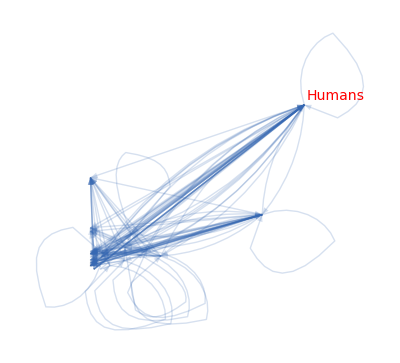

```mathematica
g[gen]=Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

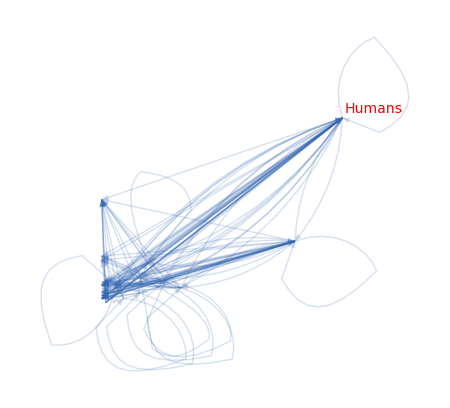

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 2020

```mathematica
gen=2020
```

2020

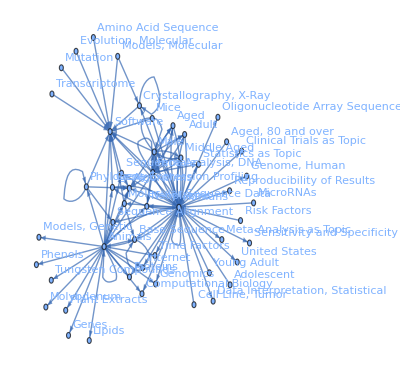

```mathematica
Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topoftopCitingCitedMeSHgraph[gen]]
```

{Humans,Female,Male,Software,Animals,Algorithms,Middle Aged,Adult,Neoplasms,Aged,Phylogeny,Statistics as Topic,Meta-Analysis as Topic,Proteins,Computational Biology,Reproducibility of Results,Sequence Alignment,Crystallography, X-Ray,Mice,Molecular Sequence Data,Genomics,Data Interpretation, Statistical,Lipids,Internet,Sequence Analysis, DNA,Base Sequence,Models, Molecular,Amino Acid Sequence,Sensitivity and Specificity,Time Factors,Young Adult,United States,Gene Expression Profiling,Genome, Human,Evolution, Molecular,Adolescent,Phenols,Cell Line, Tumor,Aged, 80 and over,Oligonucleotide Array Sequence Analysis,Models, Genetic,Risk Factors,Clinical Trials as Topic,Transcriptome,MicroRNAs,Tungsten Compounds,Plant Extracts,Molybdenum,Genes,Mutation}

< edge list >

```mathematica
el[gen]=EdgeList[topoftopCitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Female->Humans,Male->Humans,Humans->Software,Animals->Software,Animals->Humans,Animals->Algorithms,Middle Aged->Humans,Humans->Algorithms,Adult->Humans,Humans->Animals,Humans->Female,Humans->Neoplasms,Animals->Animals,Humans->Male,Aged->Humans,Phylogeny->Software,Humans->Statistics as Topic,Humans->Adult,Humans->Meta-Analysis as Topic,Female->Software,Animals->Proteins,Phylogeny->Algorithms,Male->Software,Animals->Computational Biology,Humans->Middle Aged,Humans->Reproducibility of Results,Animals->Sequence Alignment,Female->Female,Humans->Aged,Humans->Computational Biology,Humans->Sequence Alignment,Crystallography, X-Ray->Crystallography, X-Ray,Humans->Proteins,Mice->Humans,Male->Female,Molecular Sequence Data->Software,Humans->Genomics,Female->Male,Humans->Data Interpretation, Statistical,Female->Algorithms,Animals->Lipids,Humans->Internet,Humans->Sequence Analysis, DNA,Animals->Base Sequence,Male->Male,Phylogeny->Phylogeny,Male->Algorithms,Models, Molecular->Software,Models, Molecular->Crystallography, X-Ray,Humans->Base Sequence,Amino Acid Sequence->Software,Female->Adult,Phylogeny->Sequence Alignment,Humans->Sensitivity and Specificity,Animals->Time Factors,Young Adult->Humans,Male->Adult,Female->Neoplasms,Humans->United States,Sequence Analysis, DNA->Software,Animals->Internet,Gene Expression Profiling->Software,Humans->Genome, Human,Gene Expression Profiling->Humans,Humans->Gene Expression Profiling,Mice->Software,Middle Aged->Female,Animals->Sequence Analysis, DNA,Crystallography, X-Ray->Software,Evolution, Molecular->Software,Female->Middle Aged,Animals->Molecular Sequence Data,Adolescent->Humans,Molecular Sequence Data->Algorithms,Humans->Time Factors,Animals->Phylogeny,Animals->Phenols,Base Sequence->Base Sequence,Cell Line, Tumor->Humans,Aged, 80 and over->Humans,Humans->Oligonucleotide Array Sequence Analysis,Animals->Gene Expression Profiling,Gene Expression Profiling->Algorithms,Sequence Analysis, DNA->Algorithms,Female->Statistics as Topic,Female->Aged,Female->Animals,Male->Middle Aged,Animals->Models, Genetic,Risk Factors->Humans,Animals->Genomics,Humans->Clinical Trials as Topic,Transcriptome->Software,Middle Aged->Male,Animals->Neoplasms,Humans->Crystallography, X-Ray,MicroRNAs->Humans,Animals->Tungsten Compounds,Animals->Plant Extracts,Animals->Molybdenum,Humans->Molecular Sequence Data,Male->Aged,Male->Neoplasms,Adult->Female,Aged->Female,Molecular Sequence Data->Base Sequence,Animals->Genes,Mutation->Software}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topoftopCitingCitedMeSHgraph[gen],EdgeWeight]
```

{6347.05,2990.73,2682.02,2435.4,2072.37,2043.21,1631.71,1578.29,1557.95,1526.92,1513.43,1460.29,1397.64,1309.55,1271.07,1202.23,1064.04,1008.95,988.444,969.169,955.775,951.299,933.525,889.245,830.951,825.937,812.341,809.371,802.546,766.879,745.149,737.719,720.233,713.833,709.729,702.928,701.442,698.603,673.465,670.223,661.279,659.802,644.104,639.386,636.296,634.061,624.682,605.95,601.538,590.246,587.21,584.514,578.588,558.989,557.971,548.502,542.294,541.124,540.975,536.194,532.514,531.744,528.764,527.792,523.145,518.425,506.246,492.197,480.515,480.456,477.578,476.496,472.569,470.338,470.045,463.4,463.018,457.78,457.737,457.43,457.253,454.238,452.512,452.177,451.353,447.152,447.124,447.068,446.171,445.033,442.843,437.332,435.917,428.025,427.267,425.864,424.34,421.051,421.042,421.042,421.042,418.291,416.78,416.666,413.484,410.744,410.661,409.602,408.794}

```mathematica
topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

6347.05 | 1460.29 | 1271.07 | 2435.4 | 1513.43 | 1557.95 | 825.937 | 988.444 | 1397.64 | 766.879 | 0 | 1008.95 | 969.169 | 713.833 | 745.149 | 812.341 | 737.719 | 424.34 | 0 | 418.291 | 698.603 | 670.223 | 0 | 644.104 | 639.386 | 587.21 | 0 | 0 | 557.971 | 463.4 | 0 | 536.194 | 518.425 | 527.792 | 0 | 0 | 0 | 0 | 0 | 454.238 | 0 | 0 | 435.917 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2990.73 | 802.546 | 673.465 | 955.775 | 447.068 | 661.279 | 476.496 | 578.588 | 540.975 | 447.124 | 0 | 447.152 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2682.02 | 702.928 | 634.061 | 889.245 | 0 | 605.95 | 446.171 | 541.124 | 416.666 | 416.78 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2043.21 | 0 | 0 | 2072.37 | 1309.55 | 1631.71 | 0 | 0 | 425.864 | 0 | 463.018 | 0 | 0 | 951.299 | 830.951 | 0 | 809.371 | 0 | 0 | 472.569 | 437.332 | 0 | 659.802 | 531.744 | 480.515 | 636.296 | 0 | 0 | 0 | 548.502 | 0 | 0 | 452.512 | 0 | 0 | 0 | 457.78 | 0 | 0 | 0 | 445.033 | 0 | 0 | 0 | 0 | 421.042 | 421.042 | 421.042 | 409.602 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1578.29 | 492.197 | 427.267 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1526.92 | 413.484 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1202.23 | 410.744 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1064.04 | 0 | 933.525 | 0 | 0 | 0 | 0 | 624.682 | 0 | 0 | 0 | 0 | 0 | 558.989 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 480.456 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 720.233 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
709.729 | 0 | 0 | 506.246 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 701.442 | 0 | 470.045 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 410.661 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 532.514 | 0 | 451.353 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 457.737 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 601.538 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 590.246 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 584.514 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
542.294 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
523.145 | 0 | 0 | 528.764 | 0 | 452.177 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 477.578 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
470.338 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
457.43 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
457.253 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
442.843 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 428.025 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
421.051 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 408.794 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{31127.3,9021.2,7334.95,0,17332.2,0,2497.75,1940.4,0,1612.97,3181.24,0,0,0,0,0,0,1200.69,1215.97,1582.15,0,0,0,0,983.867,457.737,1191.78,584.514,0,0,542.294,0,1504.09,0,477.578,470.338,0,457.43,457.253,0,0,442.843,0,428.025,421.051,0,0,0,0,408.794}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topoftopCitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{22394.5,4282.19,3005.86,12666.7,3270.04,6763.99,1748.6,2108.16,2781.15,1630.78,1087.7,1456.11,969.169,1665.13,1576.1,812.341,2106.08,1734.82,0,890.861,1135.94,670.223,659.802,1175.85,1119.9,2091.9,0,0,557.971,1011.9,0,536.194,970.937,527.792,0,0,457.78,0,0,454.238,445.033,0,435.917,0,0,421.042,421.042,421.042,409.602,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{53521.9,13303.4,10340.8,12666.7,20602.2,6763.99,4246.36,4048.56,2781.15,3243.76,4268.94,1456.11,969.169,1665.13,1576.1,812.341,2106.08,2935.51,1215.97,2473.01,1135.94,670.223,659.802,1175.85,2103.77,2549.64,1191.78,584.514,557.971,1011.9,542.294,536.194,2475.02,527.792,477.578,470.338,457.78,457.43,457.253,454.238,445.033,442.843,435.917,428.025,421.051,421.042,421.042,421.042,409.602,408.794}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{31127.3,22394.5},{9021.2,4282.19},{7334.95,3005.86},{0,12666.7},{17332.2,3270.04},{0,6763.99},{2497.75,1748.6},{1940.4,2108.16},{0,2781.15},{1612.97,1630.78},{3181.24,1087.7},{0,1456.11},{0,969.169},{0,1665.13},{0,1576.1},{0,812.341},{0,2106.08},{1200.69,1734.82},{1215.97,0},{1582.15,890.861},{0,1135.94},{0,670.223},{0,659.802},{0,1175.85},{983.867,1119.9},{457.737,2091.9},{1191.78,0},{584.514,0},{0,557.971},{0,1011.9},{542.294,0},{0,536.194},{1504.09,970.937},{0,527.792},{477.578,0},{470.338,0},{0,457.78},{457.43,0},{457.253,0},{0,454.238},{0,445.033},{442.843,0},{0,435.917},{428.025,0},{421.051,0},{0,421.042},{0,421.042},{0,421.042},{0,409.602},{408.794,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

3834.61

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[7.93381],Female->Humans→Thickness[3.73841],Male->Humans→Thickness[3.35253],Humans->Software→Thickness[3.04425],Animals->Software→Thickness[2.59046],Animals->Humans→Thickness[2.55401],Animals->Algorithms→Thickness[2.03964],Middle Aged->Humans→Thickness[1.97286],Humans->Algorithms→Thickness[1.94744],Adult->Humans→Thickness[1.90865],Humans->Animals→Thickness[1.89178],Humans->Female→Thickness[1.82536],Humans->Neoplasms→Thickness[1.74705],Animals->Animals→Thickness[1.63694],Humans->Male→Thickness[1.58884],Aged->Humans→Thickness[1.50279],Phylogeny->Software→Thickness[1.33006],Humans->Statistics as Topic→Thickness[1.26119],Humans->Adult→Thickness[1.23555],Humans->Meta-Analysis as Topic→Thickness[1.21146],Female->Software→Thickness[1.19472],Animals->Proteins→Thickness[1.18912],Phylogeny->Algorithms→Thickness[1.16691],Male->Software→Thickness[1.11156],Animals->Computational Biology→Thickness[1.03869],Humans->Middle Aged→Thickness[1.03242],Humans->Reproducibility of Results→Thickness[1.01543],Animals->Sequence Alignment→Thickness[1.01171],Female->Female→Thickness[1.00318],Humans->Aged→Thickness[0.958598],Humans->Computational Biology→Thickness[0.931436],Humans->Sequence Alignment→Thickness[0.922149],Crystallography, X-Ray->Crystallography, X-Ray→Thickness[0.900291],Humans->Proteins→Thickness[0.892291],Mice->Humans→Thickness[0.887161],Male->Female→Thickness[0.87866],Molecular Sequence Data->Software→Thickness[0.876803],Humans->Genomics→Thickness[0.873254],Female->Male→Thickness[0.841831],Humans->Data Interpretation, Statistical→Thickness[0.837779],Female->Algorithms→Thickness[0.826599],Animals->Lipids→Thickness[0.824752],Humans->Internet→Thickness[0.80513],Humans->Sequence Analysis, DNA→Thickness[0.799232],Animals->Base Sequence→Thickness[0.79537],Male->Male→Thickness[0.792576],Phylogeny->Phylogeny→Thickness[0.780852],Male->Algorithms→Thickness[0.757437],Models, Molecular->Software→Thickness[0.751923],Models, Molecular->Crystallography, X-Ray→Thickness[0.737808],Humans->Base Sequence→Thickness[0.734013],Amino Acid Sequence->Software→Thickness[0.730643],Female->Adult→Thickness[0.723235],Phylogeny->Sequence Alignment→Thickness[0.698737],Humans->Sensitivity and Specificity→Thickness[0.697464],Animals->Time Factors→Thickness[0.685628],Young Adult->Humans→Thickness[0.677868],Male->Adult→Thickness[0.676405],Female->Neoplasms→Thickness[0.676218],Humans->United States→Thickness[0.670243],Sequence Analysis, DNA->Software→Thickness[0.665643],Animals->Internet→Thickness[0.66468],Gene Expression Profiling->Software→Thickness[0.660955],Humans->Genome, Human→Thickness[0.659739],Gene Expression Profiling->Humans→Thickness[0.653931],Humans->Gene Expression Profiling→Thickness[0.648031],Mice->Software→Thickness[0.632807],Middle Aged->Female→Thickness[0.615246],Animals->Sequence Analysis, DNA→Thickness[0.600644],Crystallography, X-Ray->Software→Thickness[0.60057],Evolution, Molecular->Software→Thickness[0.596972],Female->Middle Aged→Thickness[0.59562],Animals->Molecular Sequence Data→Thickness[0.590712],Adolescent->Humans→Thickness[0.587923],Molecular Sequence Data->Algorithms→Thickness[0.587557],Humans->Time Factors→Thickness[0.579251],Animals->Phylogeny→Thickness[0.578773],Animals->Phenols→Thickness[0.572225],Base Sequence->Base Sequence→Thickness[0.572172],Cell Line, Tumor->Humans→Thickness[0.571787],Aged, 80 and over->Humans→Thickness[0.571566],Humans->Oligonucleotide Array Sequence Analysis→Thickness[0.567797],Animals->Gene Expression Profiling→Thickness[0.56564],Gene Expression Profiling->Algorithms→Thickness[0.565221],Sequence Analysis, DNA->Algorithms→Thickness[0.564191],Female->Statistics as Topic→Thickness[0.55894],Female->Aged→Thickness[0.558905],Female->Animals→Thickness[0.558835],Male->Middle Aged→Thickness[0.557714],Animals->Models, Genetic→Thickness[0.556291],Risk Factors->Humans→Thickness[0.553554],Animals->Genomics→Thickness[0.546665],Humans->Clinical Trials as Topic→Thickness[0.544897],Transcriptome->Software→Thickness[0.535032],Middle Aged->Male→Thickness[0.534084],Animals->Neoplasms→Thickness[0.53233],Humans->Crystallography, X-Ray→Thickness[0.530425],MicroRNAs->Humans→Thickness[0.526313],Animals->Tungsten Compounds→Thickness[0.526303],Animals->Plant Extracts→Thickness[0.526303],Animals->Molybdenum→Thickness[0.526303],Humans->Molecular Sequence Data→Thickness[0.522864],Male->Aged→Thickness[0.520975],Male->Neoplasms→Thickness[0.520832],Adult->Female→Thickness[0.516855],Aged->Female→Thickness[0.51343],Molecular Sequence Data->Base Sequence→Thickness[0.513326],Animals->Genes→Thickness[0.512003],Mutation->Software→Thickness[0.510992]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

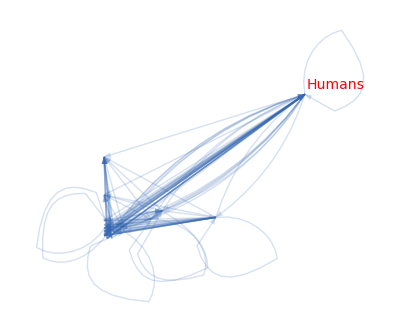

```mathematica
g[gen]=Graph[topoftopCitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

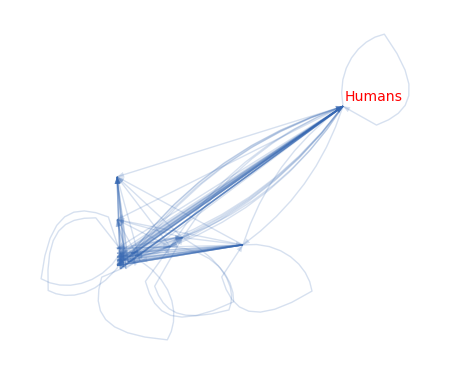

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### tabular 1955~2020

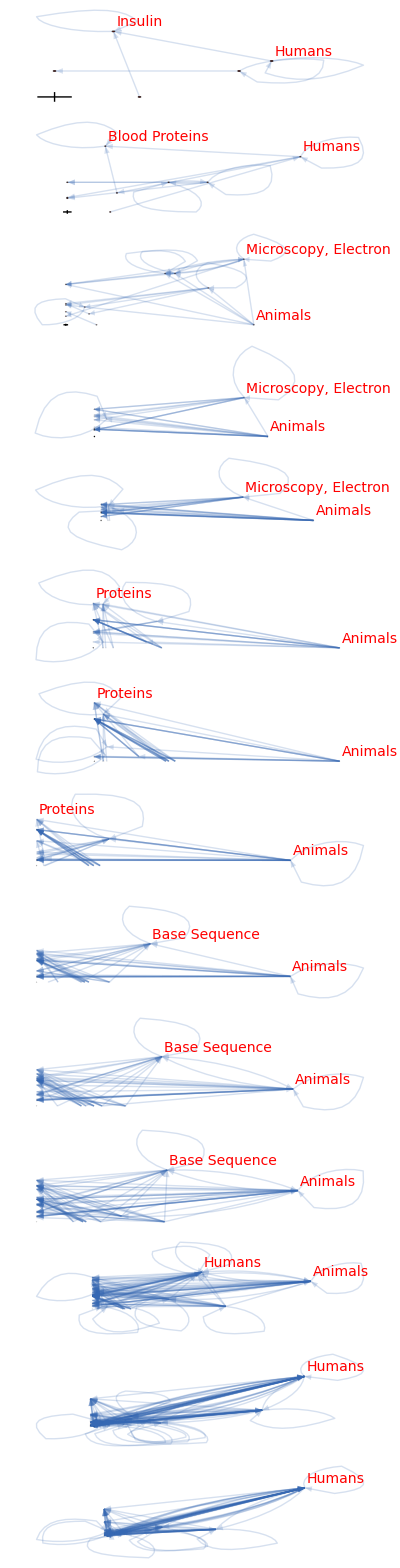

```mathematica
Table[Show[g[n],ovl,ImageSize->500],{n,1955,2020,5}]//TableForm
```

## Q2論文のMeSHの上位(生産5%)を見る（可視化）

2 回目以降の評価はここから始める。

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"<>"Q2CitingCitedMeSHwlink.save"];
```

#### 準備

```mathematica
Do[acm[n]=Accumulate[Map[#[[1]]&,Q2CitingCitedMeSHwlink[n]]];
prd[n]=(Map[#[[1]]&,Q2CitingCitedMeSHwlink[n]]//Total)*(0.05)//Round;
near[n]=Nearest[acm[n]->"Index",prd[n]][[1]];
topofQ2CitingCitedMeSH[n]=Q2CitingCitedMeSHwlink[n][[1;;near[n]]],{n,1950,2020,5}]
```

```mathematica
wlinkToGraph[l_]:=Module[{g,w},
g=Map[#[[2]]&,l];
w=Map[DirectedEdge[#[[2,1]],#[[2,2]]]->#[[1]]&,l];
Graph[g,EdgeWeight->w]
]
```

```mathematica
Do[topofQ2CitingCitedMeSHgraph[n]=(topofQ2CitingCitedMeSH[n]//wlinkToGraph),{n,1950,2020,5}]
```

#### 1950

MeSHが取れなかったのでグラフなし。

#### 1955

```mathematica
gen=1955
```

1955

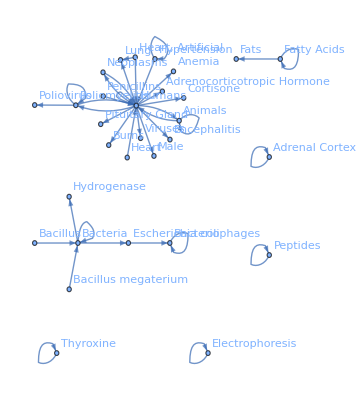

```mathematica
Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Poliomyelitis,Lung,Fatty Acids,Bacteriophages,Bacteria,Neoplasms,Hydrogenase,Adrenal Cortex,Poliovirus,Bacillus,Adrenocorticotropic Hormone,Peptides,Escherichia coli,Bacillus megaterium,Penicillins,Viruses,Male,Heart, Artificial,Heart,Encephalitis,Cortisone,Thyroxine,Pituitary Gland,Hypertension,Electrophoresis,Fats,Burns,Anemia}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Humans,Animals->Animals,Poliomyelitis->Poliomyelitis,Humans->Lung,Humans->Animals,Fatty Acids->Fatty Acids,Bacteriophages->Bacteriophages,Bacteria->Bacteria,Poliomyelitis->Humans,Humans->Neoplasms,Bacteria->Hydrogenase,Adrenal Cortex->Adrenal Cortex,Poliomyelitis->Poliovirus,Bacillus->Bacteria,Humans->Poliomyelitis,Humans->Adrenocorticotropic Hormone,Peptides->Peptides,Bacteria->Escherichia coli,Bacillus megaterium->Bacteria,Penicillins->Humans,Humans->Viruses,Escherichia coli->Bacteriophages,Humans->Male,Heart, Artificial->Humans,Heart->Humans,Humans->Encephalitis,Humans->Cortisone,Heart, Artificial->Lung,Thyroxine->Thyroxine,Humans->Pituitary Gland,Neoplasms->Humans,Hypertension->Humans,Electrophoresis->Electrophoresis,Fatty Acids->Fats,Humans->Burns,Humans->Anemia,Hypertension->Hypertension}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ2CitingCitedMeSHgraph[gen],EdgeWeight]
```

{24.8449,3.65925,3.51165,3.04314,2.96376,2.86928,2.13909,2.07312,1.63148,1.60236,1.58154,1.56667,1.54713,1.5234,1.49188,1.47246,1.43858,1.41667,1.35093,1.28333,1.28056,1.25663,1.25208,1.2426,1.24167,1.22311,1.22063,1.2153,1.20833,1.20612,1.19119,1.18261,1.18032,1.10476,1.09184,1.08333,1.0788,1.07857}

```mathematica
topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

24.8449 | 2.86928 | 1.47246 | 2.96376 | 0 | 0 | 0 | 1.58154 | 0 | 0 | 0 | 0 | 1.43858 | 0 | 0 | 0 | 0 | 1.25663 | 1.2426 | 0 | 0 | 1.22063 | 1.2153 | 0 | 1.19119 | 0 | 0 | 0 | 1.08333 | 1.0788
3.65925 | 3.51165 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.60236 | 0 | 3.04314 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.5234 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2.13909 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.09184 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2.07312 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.63148 | 0 | 1.56667 | 0 | 0 | 0 | 0 | 0 | 1.35093 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.18261 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.54713 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.49188 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.41667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.25208 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.28333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.28056 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.24167 | 0 | 0 | 1.20833 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.22311 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.20612 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.18032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.07857 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.10476 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{43.459,7.1709,6.16891,0,3.23092,2.07312,4.54907,1.18261,0,1.54713,0,1.49188,0,1.41667,1.25208,1.28333,1.28056,0,0,2.45,1.22311,0,0,1.20612,0,2.25889,1.10476,0,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{36.2148,6.38093,4.51561,4.17209,2.13909,3.3252,4.4067,1.58154,1.56667,1.54713,1.5234,0,1.43858,1.41667,1.35093,0,0,1.25663,1.2426,0,0,1.22063,1.2153,1.20612,1.19119,1.07857,1.10476,1.09184,1.08333,1.0788}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{79.6738,13.5518,10.6845,4.17209,5.37001,5.39831,8.95577,2.76415,1.56667,3.09426,1.5234,1.49188,1.43858,2.83333,2.60301,1.28333,1.28056,1.25663,1.2426,2.45,1.22311,1.22063,1.2153,2.41224,1.19119,3.33746,2.20952,1.09184,1.08333,1.0788}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{43.459,36.2148},{7.1709,6.38093},{6.16891,4.51561},{0,4.17209},{3.23092,2.13909},{2.07312,3.3252},{4.54907,4.4067},{1.18261,1.58154},{0,1.56667},{1.54713,1.54713},{0,1.5234},{1.49188,0},{0,1.43858},{1.41667,1.41667},{1.25208,1.35093},{1.28333,0},{1.28056,0},{0,1.25663},{0,1.2426},{2.45,0},{1.22311,0},{0,1.22063},{0,1.2153},{1.20612,1.20612},{0,1.19119},{2.25889,1.07857},{1.10476,1.10476},{0,1.09184},{0,1.08333},{0,1.0788}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

5.65703

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.0310561],Animals->Humans→Thickness[0.00457406],Animals->Animals→Thickness[0.00438956],Poliomyelitis->Poliomyelitis→Thickness[0.00380393],Humans->Lung→Thickness[0.0037047],Humans->Animals→Thickness[0.0035866],Fatty Acids->Fatty Acids→Thickness[0.00267386],Bacteriophages->Bacteriophages→Thickness[0.00259139],Bacteria->Bacteria→Thickness[0.00203935],Poliomyelitis->Humans→Thickness[0.00200295],Humans->Neoplasms→Thickness[0.00197693],Bacteria->Hydrogenase→Thickness[0.00195833],Adrenal Cortex->Adrenal Cortex→Thickness[0.00193392],Poliomyelitis->Poliovirus→Thickness[0.00190425],Bacillus->Bacteria→Thickness[0.00186485],Humans->Poliomyelitis→Thickness[0.00184058],Humans->Adrenocorticotropic Hormone→Thickness[0.00179822],Peptides->Peptides→Thickness[0.00177083],Bacteria->Escherichia coli→Thickness[0.00168866],Bacillus megaterium->Bacteria→Thickness[0.00160417],Penicillins->Humans→Thickness[0.00160069],Humans->Viruses→Thickness[0.00157078],Escherichia coli->Bacteriophages→Thickness[0.0015651],Humans->Male→Thickness[0.00155325],Heart, Artificial->Humans→Thickness[0.00155208],Heart->Humans→Thickness[0.00152888],Humans->Encephalitis→Thickness[0.00152579],Humans->Cortisone→Thickness[0.00151913],Heart, Artificial->Lung→Thickness[0.00151042],Thyroxine->Thyroxine→Thickness[0.00150765],Humans->Pituitary Gland→Thickness[0.00148899],Neoplasms->Humans→Thickness[0.00147826],Hypertension->Humans→Thickness[0.0014754],Electrophoresis->Electrophoresis→Thickness[0.00138095],Fatty Acids->Fats→Thickness[0.0013648],Humans->Burns→Thickness[0.00135417],Humans->Anemia→Thickness[0.0013485],Hypertension->Hypertension→Thickness[0.00134821]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

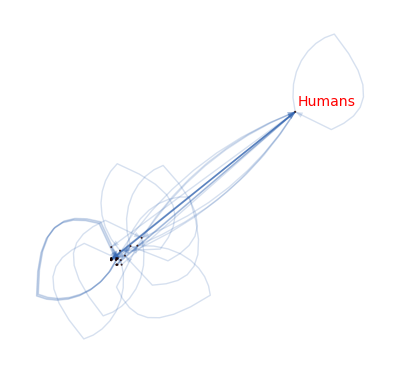

```mathematica
g[gen]=Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

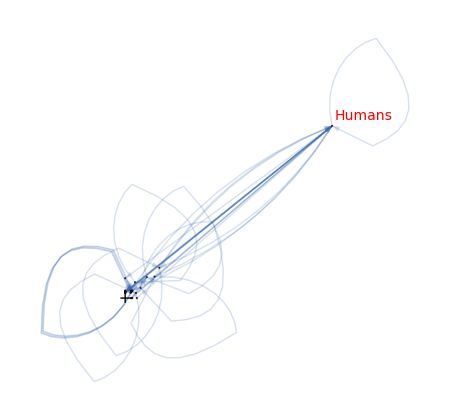

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1960

```mathematica
gen=1960
```

1960

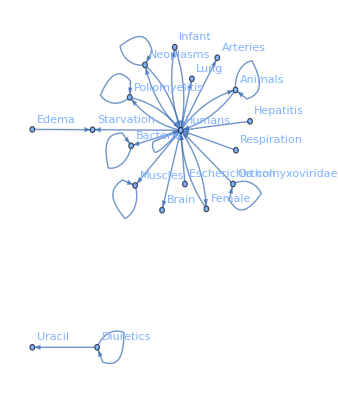

```mathematica
Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Poliomyelitis,Bacteria,Neoplasms,Muscles,Female,Orthomyxoviridae,Lung,Edema,Starvation,Brain,Respiration,Diuretics,Uracil,Hepatitis,Escherichia coli,Infant,Arteries}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Humans->Animals,Animals->Humans,Animals->Animals,Poliomyelitis->Poliomyelitis,Bacteria->Bacteria,Humans->Neoplasms,Poliomyelitis->Humans,Humans->Bacteria,Muscles->Muscles,Humans->Female,Humans->Poliomyelitis,Orthomyxoviridae->Humans,Humans->Lung,Orthomyxoviridae->Orthomyxoviridae,Edema->Starvation,Humans->Starvation,Neoplasms->Humans,Humans->Brain,Respiration->Humans,Female->Humans,Diuretics->Diuretics,Diuretics->Uracil,Hepatitis->Humans,Escherichia coli->Humans,Humans->Infant,Humans->Muscles,Neoplasms->Neoplasms,Humans->Arteries,Infant->Humans}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ2CitingCitedMeSHgraph[gen],EdgeWeight]
```

{41.6159,5.2901,5.00781,4.20305,2.88743,2.54583,2.53745,2.50471,2.42467,2.28859,2.06253,2.03537,1.90861,1.85696,1.85504,1.83333,1.75,1.65141,1.5735,1.51433,1.46204,1.425,1.39167,1.38401,1.34606,1.34228,1.30339,1.30034,1.2928,1.26752}

```mathematica
topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

41.6159 | 5.2901 | 2.03537 | 2.42467 | 2.53745 | 1.30339 | 2.06253 | 0 | 1.85696 | 0 | 1.75 | 1.5735 | 0 | 0 | 0 | 0 | 0 | 1.34228 | 1.2928
5.00781 | 4.20305 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.50471 | 0 | 2.88743 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2.54583 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.65141 | 0 | 0 | 0 | 1.30034 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2.28859 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.46204 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.90861 | 0 | 0 | 0 | 0 | 0 | 0 | 1.85504 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.83333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.51433 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.425 | 1.39167 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.38401 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.34606 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.26752 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{65.0849,9.21085,5.39214,2.54583,2.95175,2.28859,1.46204,3.76366,0,1.83333,0,0,1.51433,2.81667,0,1.38401,1.34606,1.26752,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{59.6624,9.49315,4.92281,4.9705,3.8378,3.59198,2.06253,1.85504,1.85696,0,3.58333,1.5735,0,1.425,1.39167,0,0,1.34228,1.2928}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{124.747,18.704,10.315,7.51634,6.78955,5.88058,3.52457,5.6187,1.85696,1.83333,3.58333,1.5735,1.51433,4.24167,1.39167,1.38401,1.34606,2.60981,1.2928}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{65.0849,59.6624},{9.21085,9.49315},{5.39214,4.92281},{2.54583,4.9705},{2.95175,3.8378},{2.28859,3.59198},{1.46204,2.06253},{3.76366,1.85504},{0,1.85696},{1.83333,0},{0,3.58333},{0,1.5735},{1.51433,0},{2.81667,1.425},{0,1.39167},{1.38401,0},{1.34606,0},{1.26752,1.34228},{0,1.2928}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

8.82929

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.0520198],Humans->Animals→Thickness[0.00661263],Animals->Humans→Thickness[0.00625976],Animals->Animals→Thickness[0.00525381],Poliomyelitis->Poliomyelitis→Thickness[0.00360929],Bacteria->Bacteria→Thickness[0.00318229],Humans->Neoplasms→Thickness[0.00317181],Poliomyelitis->Humans→Thickness[0.00313089],Humans->Bacteria→Thickness[0.00303084],Muscles->Muscles→Thickness[0.00286074],Humans->Female→Thickness[0.00257817],Humans->Poliomyelitis→Thickness[0.00254421],Orthomyxoviridae->Humans→Thickness[0.00238577],Humans->Lung→Thickness[0.00232119],Orthomyxoviridae->Orthomyxoviridae→Thickness[0.0023188],Edema->Starvation→Thickness[0.00229167],Humans->Starvation→Thickness[0.0021875],Neoplasms->Humans→Thickness[0.00206426],Humans->Brain→Thickness[0.00196688],Respiration->Humans→Thickness[0.00189291],Female->Humans→Thickness[0.00182755],Diuretics->Diuretics→Thickness[0.00178125],Diuretics->Uracil→Thickness[0.00173958],Hepatitis->Humans→Thickness[0.00173002],Escherichia coli->Humans→Thickness[0.00168258],Humans->Infant→Thickness[0.00167785],Humans->Muscles→Thickness[0.00162924],Neoplasms->Neoplasms→Thickness[0.00162543],Humans->Arteries→Thickness[0.001616],Infant->Humans→Thickness[0.00158441]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

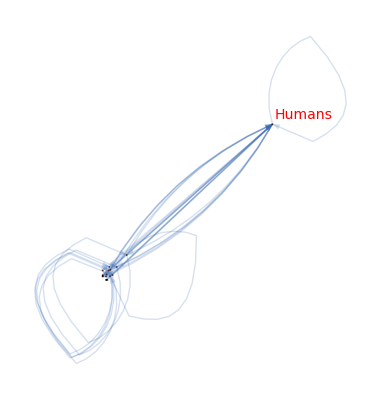

```mathematica
g[gen]=Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

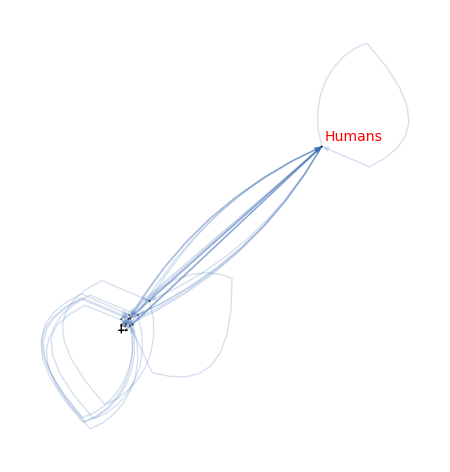

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1965

```mathematica
gen=1965
```

1965

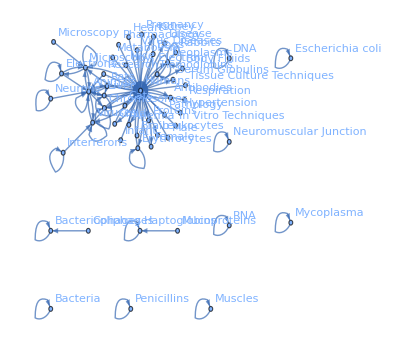

```mathematica
Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Research,Erythrocytes,Female,Rats,Chromosomes,Viruses,Male,Neoplasms,Microscopy, Electron,Child,Antibodies,Escherichia coli,In Vitro Techniques,Mycoplasma,Hemoglobins,Proteins,DNA,Pharmacology,Brain,Coliphages,Bacteriophages,Electrons,Kidney,Liver,Infant,Metabolism,Rabbits,Leukocytes,Dogs,Anemia,Neuromuscular Junction,Cats,RNA,Body Fluids,Respiration,Mice,Bacteria,Heart,Neurons,Pregnancy,Penicillins,Virus Diseases,Mucoproteins,Haptoglobins,Microscopy,Pathology,Tissue Culture Techniques,Disease,Hypertension,Muscles,Interferons,Serum Globulins}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Humans,Animals->Animals,Humans->Animals,Research->Humans,Research->Animals,Humans->Erythrocytes,Female->Humans,Erythrocytes->Humans,Rats->Humans,Chromosomes->Chromosomes,Humans->Viruses,Male->Humans,Neoplasms->Humans,Erythrocytes->Erythrocytes,Microscopy, Electron->Microscopy, Electron,Humans->Neoplasms,Child->Humans,Humans->Antibodies,Escherichia coli->Escherichia coli,Chromosomes->Humans,In Vitro Techniques->Humans,Mycoplasma->Mycoplasma,Hemoglobins->Humans,Humans->Proteins,DNA->DNA,Hemoglobins->Hemoglobins,Viruses->Humans,Pharmacology->Humans,Microscopy, Electron->Animals,Rats->Animals,Humans->Chromosomes,Brain->Humans,Coliphages->Bacteriophages,Electrons->Microscopy, Electron,Humans->Kidney,Kidney->Humans,Bacteriophages->Bacteriophages,Liver->Liver,Infant->Humans,Animals->Rats,Animals->Microscopy, Electron,Viruses->Viruses,Microscopy, Electron->Humans,Metabolism->Humans,Antibodies->Humans,Microscopy, Electron->Electrons,Rabbits->Humans,Humans->Leukocytes,Dogs->Humans,Anemia->Humans,Neuromuscular Junction->Neuromuscular Junction,Cats->Humans,Liver->Humans,RNA->RNA,Humans->Body Fluids,Respiration->Humans,Mice->Humans,Animals->Chromosomes,Electrons->Electrons,Humans->Anemia,Bacteria->Bacteria,Heart->Humans,Animals->Liver,Neurons->Neurons,Pregnancy->Humans,Penicillins->Penicillins,Humans->Virus Diseases,Electrons->Animals,Mucoproteins->Haptoglobins,Microscopy->Microscopy, Electron,Pathology->Humans,Animals->Viruses,Neoplasms->Neoplasms,Tissue Culture Techniques->Humans,Humans->Female,Humans->Disease,Hypertension->Humans,Haptoglobins->Haptoglobins,Humans->Child,Muscles->Muscles,Humans->Microscopy, Electron,Viruses->Animals,Rats->Liver,Interferons->Viruses,Interferons->Interferons,Neurons->Animals,Humans->Serum Globulins}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ2CitingCitedMeSHgraph[gen],EdgeWeight]
```

{70.9284,16.9226,13.8512,9.74616,9.70763,5.83426,5.26423,5.04214,5.00971,3.97872,3.88322,3.72729,3.71206,3.58197,3.48209,3.45176,3.42983,3.42673,3.39253,3.36333,3.23207,3.2003,3.19019,3.1884,3.15809,3.12398,3.07801,2.97756,2.89879,2.88898,2.84851,2.77246,2.75385,2.74927,2.71829,2.71212,2.70749,2.68142,2.65517,2.62004,2.5932,2.58627,2.49138,2.48805,2.40549,2.40477,2.3983,2.34992,2.34042,2.30318,2.2769,2.26175,2.25904,2.25493,2.21606,2.2005,2.17934,2.17439,2.16627,2.16017,2.11394,2.11187,2.11024,2.10844,2.10387,2.09735,2.07828,2.05845,2.01739,2.01604,1.99647,1.98018,1.97383,1.94969,1.94901,1.92308,1.92111,1.92105,1.91835,1.90979,1.90411,1.89362,1.88719,1.88484,1.86248,1.86248,1.85426,1.8526}

```mathematica
topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

70.9284 | 9.74616 | 0 | 5.26423 | 1.92308 | 0 | 2.77246 | 3.72729 | 0 | 3.42983 | 1.89362 | 1.90979 | 3.39253 | 0 | 0 | 0 | 0 | 3.15809 | 0 | 0 | 0 | 0 | 0 | 0 | 2.71212 | 0 | 0 | 0 | 0 | 2.34042 | 0 | 2.11394 | 0 | 0 | 0 | 2.2005 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.05845 | 0 | 0 | 0 | 0 | 0 | 1.92111 | 0 | 0 | 0 | 1.8526
16.9226 | 13.8512 | 0 | 0 | 0 | 2.5932 | 2.16627 | 1.97383 | 0 | 0 | 2.58627 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.10844 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.70763 | 5.83426 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.00971 | 0 | 0 | 3.48209 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.04214 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.97872 | 2.84851 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.88484 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.23207 | 0 | 0 | 0 | 0 | 0 | 3.88322 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.97756 | 1.88719 | 0 | 0 | 0 | 0 | 0 | 2.49138 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.71206 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.58197 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.94969 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.48805 | 2.88898 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.45176 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.3983 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.42673 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.40477 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.36333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.2003 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.19019 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.1884 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.07801 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.12398 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.89879 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.75385 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.74927 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.68142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2.01739 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.71829 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.16017 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.70749 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.25493 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.65517 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.62004 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.40549 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.34992 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.30318 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.2769 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.26175 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.25904 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.21606 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.17934 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.17439 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.11187 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.11024 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.85426 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.10387 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.09735 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.07828 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.01604 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.91835 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.99647 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.98018 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.94901 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.92105 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.90411 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.86248 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.86248 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{123.345,42.2019,15.5419,8.4918,5.04214,8.71207,7.11529,7.35614,3.71206,5.53166,11.2271,3.42673,2.40477,3.36333,3.2003,3.19019,6.2664,0,3.12398,2.89879,2.75385,2.74927,2.68142,6.89586,2.70749,4.9101,2.62004,2.40549,2.34992,0,2.30318,2.2769,2.26175,2.25904,2.21606,0,2.17934,2.17439,2.11187,2.11024,3.95813,2.09735,2.07828,0,2.01604,1.91835,1.99647,1.98018,1.94901,0,1.92105,1.90411,3.72495,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{179.042,40.928,0,8.74632,1.92308,2.5932,8.82195,10.055,0,5.37952,12.6464,1.90979,3.39253,3.36333,0,3.19019,3.07801,3.15809,3.12398,0,0,0,5.43068,4.55847,2.71212,6.64846,0,0,0,2.34042,0,2.11394,2.26175,0,2.21606,2.2005,0,0,2.11187,0,2.10387,0,2.07828,2.05845,0,3.93439,0,0,0,1.92111,0,1.90411,1.86248,1.8526}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{302.387,83.1299,15.5419,17.2381,6.96521,11.3053,15.9372,17.4111,3.71206,10.9112,23.8735,5.33652,5.7973,6.72666,3.2003,6.38038,9.34441,3.15809,6.24797,2.89879,2.75385,2.74927,8.1121,11.4543,5.41961,11.5586,2.62004,2.40549,2.34992,2.34042,2.30318,4.39084,4.52351,2.25904,4.43212,2.2005,2.17934,2.17439,4.22375,2.11024,6.062,2.09735,4.15655,2.05845,2.01604,5.85274,1.99647,1.98018,1.94901,1.92111,1.92105,3.80822,5.58743,1.8526}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{123.345,179.042},{42.2019,40.928},{15.5419,0},{8.4918,8.74632},{5.04214,1.92308},{8.71207,2.5932},{7.11529,8.82195},{7.35614,10.055},{3.71206,0},{5.53166,5.37952},{11.2271,12.6464},{3.42673,1.90979},{2.40477,3.39253},{3.36333,3.36333},{3.2003,0},{3.19019,3.19019},{6.2664,3.07801},{0,3.15809},{3.12398,3.12398},{2.89879,0},{2.75385,0},{2.74927,0},{2.68142,5.43068},{6.89586,4.55847},{2.70749,2.71212},{4.9101,6.64846},{2.62004,0},{2.40549,0},{2.34992,0},{0,2.34042},{2.30318,0},{2.2769,2.11394},{2.26175,2.26175},{2.25904,0},{2.21606,2.21606},{0,2.2005},{2.17934,0},{2.17439,0},{2.11187,2.11187},{2.11024,0},{3.95813,2.10387},{2.09735,0},{2.07828,2.07828},{0,2.05845},{2.01604,0},{1.91835,3.93439},{1.99647,0},{1.98018,0},{1.94901,0},{0,1.92111},{1.92105,0},{1.90411,1.90411},{3.72495,1.86248},{0,1.8526}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

21.7417

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.0886605],Animals->Humans→Thickness[0.0211533],Animals->Animals→Thickness[0.0173141],Humans->Animals→Thickness[0.0121827],Research->Humans→Thickness[0.0121345],Research->Animals→Thickness[0.00729283],Humans->Erythrocytes→Thickness[0.00658028],Female->Humans→Thickness[0.00630267],Erythrocytes->Humans→Thickness[0.00626214],Rats->Humans→Thickness[0.0049734],Chromosomes->Chromosomes→Thickness[0.00485402],Humans->Viruses→Thickness[0.00465911],Male->Humans→Thickness[0.00464007],Neoplasms->Humans→Thickness[0.00447746],Erythrocytes->Erythrocytes→Thickness[0.00435262],Microscopy, Electron->Microscopy, Electron→Thickness[0.00431471],Humans->Neoplasms→Thickness[0.00428729],Child->Humans→Thickness[0.00428342],Humans->Antibodies→Thickness[0.00424067],Escherichia coli->Escherichia coli→Thickness[0.00420417],Chromosomes->Humans→Thickness[0.00404009],In Vitro Techniques->Humans→Thickness[0.00400037],Mycoplasma->Mycoplasma→Thickness[0.00398774],Hemoglobins->Humans→Thickness[0.00398549],Humans->Proteins→Thickness[0.00394762],DNA->DNA→Thickness[0.00390498],Hemoglobins->Hemoglobins→Thickness[0.00384751],Viruses->Humans→Thickness[0.00372195],Pharmacology->Humans→Thickness[0.00362349],Microscopy, Electron->Animals→Thickness[0.00361123],Rats->Animals→Thickness[0.00356064],Humans->Chromosomes→Thickness[0.00346558],Brain->Humans→Thickness[0.00344231],Coliphages->Bacteriophages→Thickness[0.00343659],Electrons->Microscopy, Electron→Thickness[0.00339786],Humans->Kidney→Thickness[0.00339014],Kidney->Humans→Thickness[0.00338437],Bacteriophages->Bacteriophages→Thickness[0.00335177],Liver->Liver→Thickness[0.00331897],Infant->Humans→Thickness[0.00327505],Animals->Rats→Thickness[0.0032415],Animals->Microscopy, Electron→Thickness[0.00323284],Viruses->Viruses→Thickness[0.00311423],Microscopy, Electron->Humans→Thickness[0.00311007],Metabolism->Humans→Thickness[0.00300687],Antibodies->Humans→Thickness[0.00300596],Microscopy, Electron->Electrons→Thickness[0.00299787],Rabbits->Humans→Thickness[0.00293739],Humans->Leukocytes→Thickness[0.00292552],Dogs->Humans→Thickness[0.00287897],Anemia->Humans→Thickness[0.00284612],Neuromuscular Junction->Neuromuscular Junction→Thickness[0.00282719],Cats->Humans→Thickness[0.00282381],Liver->Humans→Thickness[0.00281866],RNA->RNA→Thickness[0.00277008],Humans->Body Fluids→Thickness[0.00275063],Respiration->Humans→Thickness[0.00272417],Mice->Humans→Thickness[0.00271799],Animals->Chromosomes→Thickness[0.00270784],Electrons->Electrons→Thickness[0.00270022],Humans->Anemia→Thickness[0.00264243],Bacteria->Bacteria→Thickness[0.00263984],Heart->Humans→Thickness[0.00263781],Animals->Liver→Thickness[0.00263556],Neurons->Neurons→Thickness[0.00262984],Pregnancy->Humans→Thickness[0.00262169],Penicillins->Penicillins→Thickness[0.00259785],Humans->Virus Diseases→Thickness[0.00257307],Electrons->Animals→Thickness[0.00252174],Mucoproteins->Haptoglobins→Thickness[0.00252004],Microscopy->Microscopy, Electron→Thickness[0.00249559],Pathology->Humans→Thickness[0.00247522],Animals->Viruses→Thickness[0.00246728],Neoplasms->Neoplasms→Thickness[0.00243711],Tissue Culture Techniques->Humans→Thickness[0.00243626],Humans->Female→Thickness[0.00240384],Humans->Disease→Thickness[0.00240139],Hypertension->Humans→Thickness[0.00240131],Haptoglobins->Haptoglobins→Thickness[0.00239794],Humans->Child→Thickness[0.00238724],Muscles->Muscles→Thickness[0.00238014],Humans->Microscopy, Electron→Thickness[0.00236703],Viruses->Animals→Thickness[0.00235899],Rats->Liver→Thickness[0.00235605],Interferons->Viruses→Thickness[0.0023281],Interferons->Interferons→Thickness[0.0023281],Neurons->Animals→Thickness[0.00231782],Humans->Serum Globulins→Thickness[0.00231575]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

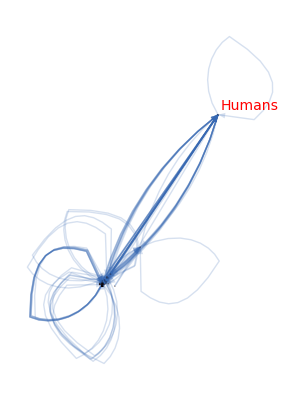

```mathematica
g[gen]=Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

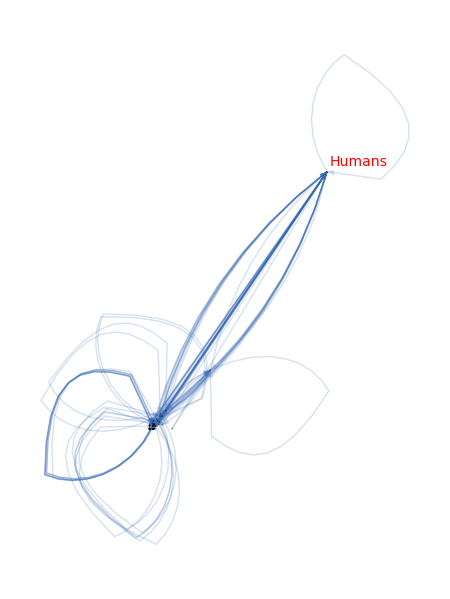

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1970

```mathematica
gen=1970
```

1970

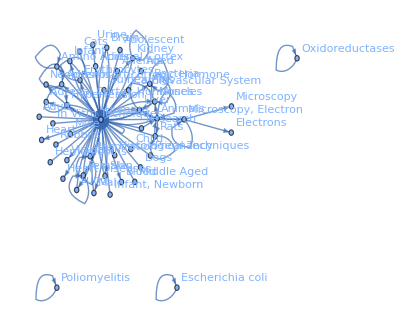

```mathematica
Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Female,Male,Adult,Rats,Blood,Child,Heart,Research,Middle Aged,Kidney,Muscles,Poliomyelitis,Escherichia coli,Neoplasms,Liver,Infant,Amino Acids,Respiration,Erythrocytes,Brain,Skin,Adolescent,In Vitro Techniques,Rabbits,Aged,Dogs,Microscopy, Electron,Mice,Hypertension,Electrons,Anemia,Adrenocorticotropic Hormone,Infant, Newborn,Bacteria,Cats,Oxidoreductases,Pregnancy,Adrenal Cortex Hormones,Heart Diseases,Histological Techniques,Lung,Cardiovascular System,Viruses,Adrenal Cortex,Hemoglobins,Microscopy,Urine,Guinea Pigs}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Humans,Animals->Animals,Humans->Animals,Female->Humans,Male->Humans,Adult->Humans,Rats->Humans,Humans->Blood,Child->Humans,Humans->Heart,Rats->Animals,Humans->Female,Research->Humans,Humans->Male,Middle Aged->Humans,Humans->Kidney,Animals->Rats,Muscles->Humans,Poliomyelitis->Poliomyelitis,Kidney->Humans,Escherichia coli->Escherichia coli,Neoplasms->Humans,Liver->Humans,Muscles->Muscles,Infant->Humans,Humans->Neoplasms,Humans->Liver,Amino Acids->Amino Acids,Respiration->Humans,Humans->Erythrocytes,Brain->Humans,Erythrocytes->Humans,Humans->Respiration,Skin->Humans,Adolescent->Humans,Animals->Liver,In Vitro Techniques->Humans,Humans->Muscles,Liver->Liver,Rabbits->Humans,Humans->Amino Acids,Aged->Humans,Dogs->Humans,Microscopy, Electron->Microscopy, Electron,Female->Female,Humans->Brain,Mice->Humans,Rats->Rats,Hypertension->Humans,Humans->Infant,Microscopy, Electron->Electrons,Humans->Anemia,Adrenocorticotropic Hormone->Adrenocorticotropic Hormone,Infant, Newborn->Humans,Bacteria->Bacteria,Microscopy, Electron->Humans,Humans->Bacteria,Cats->Humans,Oxidoreductases->Oxidoreductases,Pregnancy->Humans,Humans->Adrenal Cortex Hormones,Hypertension->Hypertension,Respiration->Respiration,Kidney->Kidney,Humans->Heart Diseases,Humans->Adrenocorticotropic Hormone,Humans->Histological Techniques,Humans->Lung,Humans->Skin,Animals->Muscles,Humans->Cardiovascular System,Humans->Viruses,Humans->Adrenal Cortex,Research->Animals,Hemoglobins->Humans,Humans->Hypertension,Microscopy, Electron->Microscopy,Humans->Urine,Animals->Microscopy, Electron,Guinea Pigs->Humans,Erythrocytes->Erythrocytes,Lung->Humans}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ2CitingCitedMeSHgraph[gen],EdgeWeight]
```

{198.764,44.2264,34.4426,27.6092,20.3559,19.1438,11.1343,9.3667,9.3294,8.80232,8.72627,8.54819,8.39861,8.12944,7.91406,7.81169,7.17192,7.07548,7.0378,7.00438,6.89248,6.76905,6.71448,6.67216,6.65546,6.56902,6.56219,6.55478,6.53235,6.29239,5.87306,5.78422,5.74802,5.73554,5.59593,5.57697,5.4763,5.35984,5.35668,5.26013,5.23954,5.18356,5.14916,5.08876,5.05668,5.04656,4.99088,4.96033,4.91281,4.9024,4.90226,4.80558,4.74383,4.72767,4.70585,4.69349,4.68777,4.67114,4.6453,4.60803,4.59634,4.59552,4.56806,4.55994,4.52913,4.42827,4.40969,4.39987,4.29927,4.28239,4.24442,4.23306,4.19817,4.18771,4.17639,4.17171,4.13755,4.11299,4.08067,4.07057,4.06252,4.06238,4.05595}

```mathematica
topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

198.764 | 27.6092 | 8.39861 | 7.91406 | 0 | 0 | 9.3294 | 0 | 8.72627 | 0 | 0 | 7.17192 | 5.35668 | 0 | 0 | 6.56219 | 6.55478 | 4.90226 | 5.18356 | 5.73554 | 5.87306 | 4.99088 | 4.28239 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.13755 | 0 | 4.74383 | 4.40969 | 0 | 4.67114 | 0 | 0 | 0 | 4.59552 | 4.42827 | 4.39987 | 4.29927 | 4.23306 | 4.19817 | 4.18771 | 0 | 0 | 4.08067 | 0
44.2264 | 34.4426 | 0 | 0 | 0 | 7.07548 | 0 | 0 | 0 | 0 | 0 | 0 | 4.24442 | 0 | 0 | 0 | 5.4763 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.07057 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
20.3559 | 0 | 5.04656 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
19.1438 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.1343 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.3667 | 8.54819 | 0 | 0 | 0 | 4.91281 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.80232 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.12944 | 4.17639 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.81169 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.89248 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.52913 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.0378 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.65546 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.00438 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.76905 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.71448 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.67216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.26013 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.56902 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.53235 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.29239 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.55994 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.74802 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.06238 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.78422 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.59593 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.57697 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.35984 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.23954 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.14916 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.08876 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.68777 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.05668 | 0 | 0 | 4.80558 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.11299 | 0 | 0
4.96033 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.9024 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.56806 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.72767 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.70585 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.69349 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.6453 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.60803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.59634 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.05595 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.17171 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.06252 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{369.74,99.5358,25.4025,19.1438,11.1343,22.8277,0,8.80232,0,12.3058,7.81169,11.4216,13.6933,7.00438,6.76905,6.71448,11.9323,6.56902,6.53235,10.8523,9.8104,5.78422,5.59593,5.57697,5.35984,5.23954,5.14916,5.08876,18.663,4.96033,9.47046,0,0,4.72767,4.70585,4.69349,4.6453,4.60803,4.59634,0,0,0,4.05595,0,0,0,4.17171,0,0,4.06252}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{452.244,74.7764,13.4452,7.91406,0,11.9883,9.3294,0,8.72627,0,0,11.701,16.2566,7.00438,6.76905,6.56219,17.2912,4.90226,11.7159,10.2955,9.93544,4.99088,4.28239,0,0,0,0,0,9.12725,0,8.70561,4.80558,4.74383,9.13736,0,9.36463,0,4.60803,0,4.59552,4.42827,4.39987,4.29927,4.23306,4.19817,4.18771,0,4.11299,4.08067,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{821.984,174.312,38.8476,27.0579,11.1343,34.816,9.3294,8.80232,8.72627,12.3058,7.81169,23.1226,29.9498,14.0088,13.5381,13.2767,29.2235,11.4713,18.2483,21.1478,19.7458,10.7751,9.87832,5.57697,5.35984,5.23954,5.14916,5.08876,27.7903,4.96033,18.1761,4.80558,4.74383,13.865,4.70585,14.0581,4.6453,9.21606,4.59634,4.59552,4.42827,4.39987,8.35522,4.23306,4.19817,4.18771,4.17171,4.11299,4.08067,4.06252}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{369.74,452.244},{99.5358,74.7764},{25.4025,13.4452},{19.1438,7.91406},{11.1343,0},{22.8277,11.9883},{0,9.3294},{8.80232,0},{0,8.72627},{12.3058,0},{7.81169,0},{11.4216,11.701},{13.6933,16.2566},{7.00438,7.00438},{6.76905,6.76905},{6.71448,6.56219},{11.9323,17.2912},{6.56902,4.90226},{6.53235,11.7159},{10.8523,10.2955},{9.8104,9.93544},{5.78422,4.99088},{5.59593,4.28239},{5.57697,0},{5.35984,0},{5.23954,0},{5.14916,0},{5.08876,0},{18.663,9.12725},{4.96033,0},{9.47046,8.70561},{0,4.80558},{0,4.74383},{4.72767,9.13736},{4.70585,0},{4.69349,9.36463},{4.6453,0},{4.60803,4.60803},{4.59634,0},{0,4.59552},{0,4.42827},{0,4.39987},{4.05595,4.29927},{0,4.23306},{0,4.19817},{0,4.18771},{4.17171,0},{0,4.11299},{0,4.08067},{4.06252,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

58.4151

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.248456],Animals->Humans→Thickness[0.055283],Animals->Animals→Thickness[0.0430532],Humans->Animals→Thickness[0.0345115],Female->Humans→Thickness[0.0254449],Male->Humans→Thickness[0.0239297],Adult->Humans→Thickness[0.0139179],Rats->Humans→Thickness[0.0117084],Humans->Blood→Thickness[0.0116617],Child->Humans→Thickness[0.0110029],Humans->Heart→Thickness[0.0109078],Rats->Animals→Thickness[0.0106852],Humans->Female→Thickness[0.0104983],Research->Humans→Thickness[0.0101618],Humans->Male→Thickness[0.00989257],Middle Aged->Humans→Thickness[0.00976462],Humans->Kidney→Thickness[0.0089649],Animals->Rats→Thickness[0.00884435],Muscles->Humans→Thickness[0.00879724],Poliomyelitis->Poliomyelitis→Thickness[0.00875548],Kidney->Humans→Thickness[0.0086156],Escherichia coli->Escherichia coli→Thickness[0.00846131],Neoplasms->Humans→Thickness[0.0083931],Liver->Humans→Thickness[0.0083402],Muscles->Muscles→Thickness[0.00831933],Infant->Humans→Thickness[0.00821128],Humans->Neoplasms→Thickness[0.00820273],Humans->Liver→Thickness[0.00819347],Amino Acids->Amino Acids→Thickness[0.00816544],Respiration->Humans→Thickness[0.00786549],Humans->Erythrocytes→Thickness[0.00734133],Brain->Humans→Thickness[0.00723028],Erythrocytes->Humans→Thickness[0.00718502],Humans->Respiration→Thickness[0.00716942],Skin->Humans→Thickness[0.00699491],Adolescent->Humans→Thickness[0.00697121],Animals->Liver→Thickness[0.00684538],In Vitro Techniques->Humans→Thickness[0.0066998],Humans->Muscles→Thickness[0.00669585],Liver->Liver→Thickness[0.00657516],Rabbits->Humans→Thickness[0.00654942],Humans->Amino Acids→Thickness[0.00647944],Aged->Humans→Thickness[0.00643646],Dogs->Humans→Thickness[0.00636095],Microscopy, Electron->Microscopy, Electron→Thickness[0.00632085],Female->Female→Thickness[0.00630821],Humans->Brain→Thickness[0.0062386],Mice->Humans→Thickness[0.00620041],Rats->Rats→Thickness[0.00614101],Hypertension->Humans→Thickness[0.006128],Humans->Infant→Thickness[0.00612783],Microscopy, Electron->Electrons→Thickness[0.00600697],Humans->Anemia→Thickness[0.00592978],Adrenocorticotropic Hormone->Adrenocorticotropic Hormone→Thickness[0.00590959],Infant, Newborn->Humans→Thickness[0.00588231],Bacteria->Bacteria→Thickness[0.00586686],Microscopy, Electron->Humans→Thickness[0.00585971],Humans->Bacteria→Thickness[0.00583893],Cats->Humans→Thickness[0.00580662],Oxidoreductases->Oxidoreductases→Thickness[0.00576004],Pregnancy->Humans→Thickness[0.00574543],Humans->Adrenal Cortex Hormones→Thickness[0.0057444],Hypertension->Hypertension→Thickness[0.00571008],Respiration->Respiration→Thickness[0.00569993],Kidney->Kidney→Thickness[0.00566141],Humans->Heart Diseases→Thickness[0.00553534],Humans->Adrenocorticotropic Hormone→Thickness[0.00551211],Humans->Histological Techniques→Thickness[0.00549984],Humans->Lung→Thickness[0.00537409],Humans->Skin→Thickness[0.00535299],Animals->Muscles→Thickness[0.00530552],Humans->Cardiovascular System→Thickness[0.00529132],Humans->Viruses→Thickness[0.00524772],Humans->Adrenal Cortex→Thickness[0.00523464],Research->Animals→Thickness[0.00522049],Hemoglobins->Humans→Thickness[0.00521463],Humans->Hypertension→Thickness[0.00517193],Microscopy, Electron->Microscopy→Thickness[0.00514123],Humans->Urine→Thickness[0.00510084],Animals->Microscopy, Electron→Thickness[0.00508821],Guinea Pigs->Humans→Thickness[0.00507815],Erythrocytes->Erythrocytes→Thickness[0.00507798],Lung->Humans→Thickness[0.00506994]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

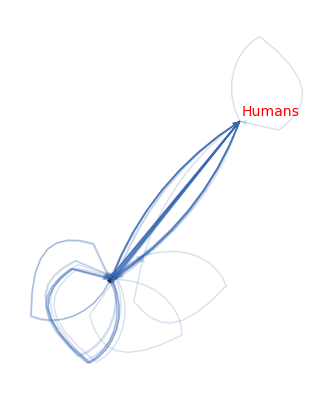

```mathematica
g[gen]=Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

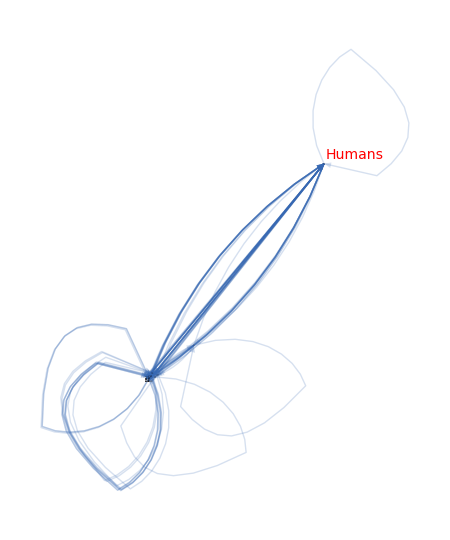

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1975

```mathematica
gen=1975
```

1975

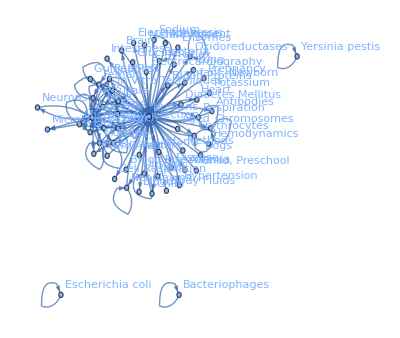

```mathematica
Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Adult,Middle Aged,Rats,Child,Muscles,Mice,Research,Blood,Aged,Neoplasms,Microscopy, Electron,Adolescent,Escherichia coli,Infant,Dogs,Rabbits,In Vitro Techniques,Heart,Liver,Infant, Newborn,Erythrocytes,Cats,Electrons,Respiration,Body Fluids,Neurons,Bacteriophages,Electrocardiography,Lung,Chromosomes,Kidney,Time Factors,Disease,Pregnancy,Hypertension,Bacteria,Blood Pressure,Proteins,Brain,Child, Preschool,Insulin,Diabetes Mellitus,Yersinia pestis,Blood Proteins,Antibodies,Microscopy,Enzymes,Methods,Sodium,Oxidoreductases,Guinea Pigs,Glucose,Cell Respiration,Skin,Anemia,Potassium,Electrophoresis,Intestines,Hemodynamics,Reflex}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Animals->Humans,Male->Humans,Female->Humans,Humans->Animals,Adult->Humans,Middle Aged->Humans,Rats->Animals,Rats->Humans,Animals->Rats,Male->Animals,Child->Humans,Muscles->Muscles,Animals->Muscles,Female->Animals,Mice->Animals,Research->Humans,Humans->Male,Humans->Blood,Aged->Humans,Humans->Neoplasms,Animals->Mice,Microscopy, Electron->Animals,Adolescent->Humans,Muscles->Humans,Escherichia coli->Escherichia coli,Rats->Rats,Microscopy, Electron->Humans,Infant->Humans,Dogs->Humans,Rabbits->Animals,In Vitro Techniques->Humans,Microscopy, Electron->Microscopy, Electron,Humans->Heart,Liver->Humans,Animals->Microscopy, Electron,Animals->Rabbits,Infant, Newborn->Humans,Rabbits->Humans,Humans->Muscles,Humans->Female,In Vitro Techniques->Animals,Erythrocytes->Humans,Research->Animals,Cats->Humans,Microscopy, Electron->Electrons,Animals->Liver,Humans->Liver,Cats->Animals,Humans->Respiration,Humans->Rats,Humans->Body Fluids,Animals->Cats,Neoplasms->Humans,Mice->Humans,Neurons->Animals,Bacteriophages->Bacteriophages,Electrocardiography->Humans,Humans->Erythrocytes,Humans->Lung,Chromosomes->Chromosomes,Animals->Research,Humans->Kidney,Time Factors->Humans,Animals->Electrons,Humans->Disease,Pregnancy->Humans,Lung->Humans,Respiration->Humans,Mice->Mice,Kidney->Humans,Heart->Humans,Liver->Liver,Liver->Animals,Humans->Hypertension,Bacteria->Bacteria,Blood Pressure->Humans,Animals->Proteins,Hypertension->Humans,Humans->Rabbits,Neoplasms->Neoplasms,Brain->Humans,Muscles->Animals,Humans->Infant,Respiration->Respiration,Child, Preschool->Humans,Insulin->Insulin,Humans->Diabetes Mellitus,Yersinia pestis->Yersinia pestis,Humans->Blood Proteins,Humans->Antibodies,Antibodies->Humans,Animals->Neurons,Animals->In Vitro Techniques,Insulin->Humans,Microscopy, Electron->Microscopy,Humans->Microscopy, Electron,Animals->Kidney,Humans->Enzymes,Cats->Cats,Female->Female,Animals->Male,Male->Male,Methods->Humans,Sodium->Humans,Humans->Chromosomes,Humans->Oxidoreductases,Animals->Microscopy,Kidney->Kidney,Guinea Pigs->Humans,Humans->Proteins,Humans->Bacteria,Blood Proteins->Humans,Glucose->Humans,Humans->Cell Respiration,Skin->Humans,Male->Rats,Humans->Brain,Humans->Anemia,Disease->Humans,Humans->Electrons,Erythrocytes->Erythrocytes,Diabetes Mellitus->Humans,Potassium->Humans,Humans->Electrophoresis,Humans->Intestines,Oxidoreductases->Oxidoreductases,Rats->Liver,Time Factors->Animals,Bacteria->Humans,Humans->Infant, Newborn,Hemodynamics->Humans,Humans->Child,Humans->Reflex}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ2CitingCitedMeSHgraph[gen],EdgeWeight]
```

{226.155,67.6267,62.971,39.8371,36.904,34.8682,22.8363,16.2373,16.1895,14.0923,14.0492,13.1063,12.0386,11.4161,10.9848,10.8593,10.7435,10.7404,10.1179,10.1126,10.0889,10.0247,9.95937,9.91658,9.65799,9.35785,9.29934,8.98949,8.97153,8.93301,8.81953,8.76929,8.41928,8.373,8.33331,8.28772,8.22588,8.05497,7.99003,7.95511,7.86499,7.72564,7.47636,7.30686,7.22118,7.08852,7.04566,7.04561,7.04446,7.03396,6.93043,6.92378,6.92041,6.88843,6.75609,6.65516,6.65076,6.52713,6.47477,6.4735,6.40468,6.35443,6.34624,6.33254,6.27727,6.24478,6.22198,6.21655,6.16099,6.1363,5.96519,5.96251,5.93001,5.92658,5.84268,5.76008,5.63632,5.60068,5.58314,5.57197,5.55729,5.51807,5.50723,5.36127,5.35101,5.32874,5.27391,5.18466,5.12934,5.09261,5.07688,5.07538,5.03541,4.98725,4.96342,4.94164,4.93944,4.92485,4.91909,4.91267,4.89104,4.83995,4.82868,4.75349,4.75193,4.7504,4.72121,4.66992,4.65241,4.63015,4.61948,4.61455,4.5759,4.56389,4.51558,4.46688,4.46375,4.45762,4.34731,4.30281,4.24617,4.23572,4.22428,4.15872,4.11476,4.10116,4.09943,4.06971,4.06352,4.03006,3.98965,3.98582,3.97529,3.96703,3.95208}

```mathematica
topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

226.155 | 34.8682 | 10.1179 | 7.72564 | 0 | 0 | 6.92378 | 3.96703 | 7.86499 | 0 | 0 | 10.1126 | 0 | 10.0247 | 4.92485 | 0 | 0 | 5.35101 | 0 | 5.55729 | 0 | 8.33331 | 7.04446 | 3.98582 | 6.4735 | 0 | 4.23572 | 6.93043 | 6.92041 | 0 | 0 | 0 | 6.40468 | 4.72121 | 6.33254 | 0 | 6.22198 | 0 | 5.76008 | 4.5759 | 0 | 4.61455 | 4.34731 | 0 | 0 | 5.12934 | 0 | 5.07688 | 5.07538 | 0 | 4.91267 | 0 | 0 | 4.66992 | 0 | 0 | 4.46688 | 0 | 4.30281 | 0 | 4.10116 | 4.09943 | 0 | 3.95208
62.971 | 67.6267 | 4.82868 | 0 | 0 | 0 | 14.0492 | 0 | 10.9848 | 9.95937 | 6.34624 | 0 | 0 | 0 | 8.22588 | 0 | 0 | 0 | 0 | 8.05497 | 4.96342 | 0 | 7.04561 | 0 | 0 | 6.88843 | 6.24478 | 0 | 0 | 4.98725 | 0 | 0 | 0 | 0 | 4.91909 | 0 | 0 | 0 | 0 | 0 | 0 | 5.58314 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.65241 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
39.8371 | 13.1063 | 4.75349 | 0 | 0 | 0 | 4.45762 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
36.904 | 10.8593 | 0 | 4.83995 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
22.8363 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16.2373 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
14.0923 | 16.1895 | 0 | 0 | 0 | 0 | 8.98949 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.06352 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.0386 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.35785 | 5.36127 | 0 | 0 | 0 | 0 | 0 | 0 | 11.4161 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.65516 | 10.7435 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.96519 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10.7404 | 7.22118 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10.0889 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.75609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.51807 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.97153 | 9.91658 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.373 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.04566 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.93944 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.65799 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.29934 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.93301 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.81953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.95511 | 8.76929 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.41928 | 7.47636 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.93001 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.28772 | 5.84268 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.92658 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.99003 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.30686 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.22428 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.08852 | 7.03396 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.89104 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.1363 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.32874 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6.65076 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.52713 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.47477 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.16099 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.35443 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.96251 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.63015 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.27727 | 4.03006 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.24617 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.21655 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.57197 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.98965 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.63632 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.60068 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.50723 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.27391 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.94164 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.18466 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.15872 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.09261 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.56389 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.03541 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.75193 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.7504 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.06971 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.61948 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.51558 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.46375 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.11476 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.97529 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{466.281,238.331,62.1545,52.6033,22.8363,16.2373,43.3348,12.0386,26.1352,23.3638,17.9616,0,10.0889,12.2742,39.2462,9.65799,9.29934,8.93301,8.81953,16.7244,15.8956,5.93001,20.057,7.99003,11.5311,19.0135,0,11.465,0,6.65076,6.52713,6.47477,6.16099,6.35443,10.5927,10.3073,4.24617,6.21655,5.57197,9.62597,5.60068,0,5.50723,5.27391,10.1263,4.15872,5.09261,4.56389,5.03541,0,0,4.75193,4.7504,4.06971,4.61948,4.51558,0,4.46375,0,4.11476,0,0,3.97529,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{681.338,215.696,19.7,12.5656,0,0,34.4201,3.96703,30.2659,15.9246,6.34624,10.1126,0,15.5428,21.5237,0,9.29934,5.35101,0,13.6123,4.96342,8.33331,24.0802,3.98582,10.6978,11.7795,17.5262,12.2592,6.92041,4.98725,6.52713,0,6.40468,11.0756,15.8818,0,6.22198,0,5.76008,10.2122,0,10.1977,4.34731,0,5.18466,5.12934,5.09261,5.07688,5.07538,9.59185,4.91267,0,0,8.73963,0,0,4.46688,0,4.30281,0,4.10116,4.09943,0,3.95208}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{1147.62,454.027,81.8545,65.1689,22.8363,16.2373,77.7548,16.0056,56.4011,39.2884,24.3078,10.1126,10.0889,27.8169,60.7699,9.65799,18.5987,14.284,8.81953,30.3367,20.8591,14.2633,44.1372,11.9759,22.2289,30.793,17.5262,23.7242,6.92041,11.638,13.0543,6.47477,12.5657,17.4301,26.4744,10.3073,10.4682,6.21655,11.3321,19.8382,5.60068,10.1977,9.85454,5.27391,15.311,9.28805,10.1852,9.64077,10.1108,9.59185,4.91267,4.75193,4.7504,12.8093,4.61948,4.51558,4.46688,4.46375,4.30281,4.11476,4.10116,4.09943,3.97529,3.95208}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{466.281,681.338},{238.331,215.696},{62.1545,19.7},{52.6033,12.5656},{22.8363,0},{16.2373,0},{43.3348,34.4201},{12.0386,3.96703},{26.1352,30.2659},{23.3638,15.9246},{17.9616,6.34624},{0,10.1126},{10.0889,0},{12.2742,15.5428},{39.2462,21.5237},{9.65799,0},{9.29934,9.29934},{8.93301,5.35101},{8.81953,0},{16.7244,13.6123},{15.8956,4.96342},{5.93001,8.33331},{20.057,24.0802},{7.99003,3.98582},{11.5311,10.6978},{19.0135,11.7795},{0,17.5262},{11.465,12.2592},{0,6.92041},{6.65076,4.98725},{6.52713,6.52713},{6.47477,0},{6.16099,6.40468},{6.35443,11.0756},{10.5927,15.8818},{10.3073,0},{4.24617,6.22198},{6.21655,0},{5.57197,5.76008},{9.62597,10.2122},{5.60068,0},{0,10.1977},{5.50723,4.34731},{5.27391,0},{10.1263,5.18466},{4.15872,5.12934},{5.09261,5.09261},{4.56389,5.07688},{5.03541,5.07538},{0,9.59185},{0,4.91267},{4.75193,0},{4.7504,0},{4.06971,8.73963},{4.61948,0},{4.51558,0},{0,4.46688},{4.46375,0},{0,4.30281},{4.11476,0},{0,4.10116},{0,4.09943},{3.97529,0},{0,3.95208}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

82.5615

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.282693],Animals->Animals→Thickness[0.0845334],Animals->Humans→Thickness[0.0787138],Male->Humans→Thickness[0.0497963],Female->Humans→Thickness[0.04613],Humans->Animals→Thickness[0.0435852],Adult->Humans→Thickness[0.0285453],Middle Aged->Humans→Thickness[0.0202966],Rats->Animals→Thickness[0.0202369],Rats->Humans→Thickness[0.0176153],Animals->Rats→Thickness[0.0175615],Male->Animals→Thickness[0.0163829],Child->Humans→Thickness[0.0150482],Muscles->Muscles→Thickness[0.0142701],Animals->Muscles→Thickness[0.013731],Female->Animals→Thickness[0.0135741],Mice->Animals→Thickness[0.0134293],Research->Humans→Thickness[0.0134255],Humans->Male→Thickness[0.0126473],Humans->Blood→Thickness[0.0126408],Aged->Humans→Thickness[0.0126112],Humans->Neoplasms→Thickness[0.0125309],Animals->Mice→Thickness[0.0124492],Microscopy, Electron->Animals→Thickness[0.0123957],Adolescent->Humans→Thickness[0.0120725],Muscles->Humans→Thickness[0.0116973],Escherichia coli->Escherichia coli→Thickness[0.0116242],Rats->Rats→Thickness[0.0112369],Microscopy, Electron->Humans→Thickness[0.0112144],Infant->Humans→Thickness[0.0111663],Dogs->Humans→Thickness[0.0110244],Rabbits->Animals→Thickness[0.0109616],In Vitro Techniques->Humans→Thickness[0.0105241],Microscopy, Electron->Microscopy, Electron→Thickness[0.0104662],Humans->Heart→Thickness[0.0104166],Liver->Humans→Thickness[0.0103596],Animals->Microscopy, Electron→Thickness[0.0102823],Animals->Rabbits→Thickness[0.0100687],Infant, Newborn->Humans→Thickness[0.00998754],Rabbits->Humans→Thickness[0.00994389],Humans->Muscles→Thickness[0.00983123],Humans->Female→Thickness[0.00965705],In Vitro Techniques->Animals→Thickness[0.00934545],Erythrocytes->Humans→Thickness[0.00913357],Research->Animals→Thickness[0.00902647],Cats->Humans→Thickness[0.00886065],Microscopy, Electron->Electrons→Thickness[0.00880707],Animals->Liver→Thickness[0.00880702],Humans->Liver→Thickness[0.00880557],Cats->Animals→Thickness[0.00879244],Humans->Respiration→Thickness[0.00866304],Humans->Rats→Thickness[0.00865473],Humans->Body Fluids→Thickness[0.00865051],Animals->Cats→Thickness[0.00861054],Neoplasms->Humans→Thickness[0.00844512],Mice->Humans→Thickness[0.00831895],Neurons->Animals→Thickness[0.00831345],Bacteriophages->Bacteriophages→Thickness[0.00815891],Electrocardiography->Humans→Thickness[0.00809346],Humans->Erythrocytes→Thickness[0.00809187],Humans->Lung→Thickness[0.00800585],Chromosomes->Chromosomes→Thickness[0.00794304],Animals->Research→Thickness[0.0079328],Humans->Kidney→Thickness[0.00791568],Time Factors->Humans→Thickness[0.00784659],Animals->Electrons→Thickness[0.00780598],Humans->Disease→Thickness[0.00777748],Pregnancy->Humans→Thickness[0.00777069],Lung->Humans→Thickness[0.00770123],Respiration->Humans→Thickness[0.00767037],Mice->Mice→Thickness[0.00745649],Kidney->Humans→Thickness[0.00745314],Heart->Humans→Thickness[0.00741251],Liver->Liver→Thickness[0.00740823],Liver->Animals→Thickness[0.00730335],Humans->Hypertension→Thickness[0.0072001],Bacteria->Bacteria→Thickness[0.0070454],Blood Pressure->Humans→Thickness[0.00700085],Animals->Proteins→Thickness[0.00697892],Hypertension->Humans→Thickness[0.00696496],Humans->Rabbits→Thickness[0.00694661],Neoplasms->Neoplasms→Thickness[0.00689759],Brain->Humans→Thickness[0.00688404],Muscles->Animals→Thickness[0.00670159],Humans->Infant→Thickness[0.00668876],Respiration->Respiration→Thickness[0.00666093],Child, Preschool->Humans→Thickness[0.00659239],Insulin->Insulin→Thickness[0.00648083],Humans->Diabetes Mellitus→Thickness[0.00641167],Yersinia pestis->Yersinia pestis→Thickness[0.00636576],Humans->Blood Proteins→Thickness[0.0063461],Humans->Antibodies→Thickness[0.00634423],Antibodies->Humans→Thickness[0.00629426],Animals->Neurons→Thickness[0.00623407],Animals->In Vitro Techniques→Thickness[0.00620428],Insulin->Humans→Thickness[0.00617705],Microscopy, Electron->Microscopy→Thickness[0.0061743],Humans->Microscopy, Electron→Thickness[0.00615606],Animals->Kidney→Thickness[0.00614886],Humans->Enzymes→Thickness[0.00614084],Cats->Cats→Thickness[0.00611381],Female->Female→Thickness[0.00604994],Animals->Male→Thickness[0.00603585],Male->Male→Thickness[0.00594186],Methods->Humans→Thickness[0.00593991],Sodium->Humans→Thickness[0.005938],Humans->Chromosomes→Thickness[0.00590151],Humans->Oxidoreductases→Thickness[0.00583739],Animals->Microscopy→Thickness[0.00581551],Kidney->Kidney→Thickness[0.00578768],Guinea Pigs->Humans→Thickness[0.00577435],Humans->Proteins→Thickness[0.00576819],Humans->Bacteria→Thickness[0.00571988],Blood Proteins->Humans→Thickness[0.00570486],Glucose->Humans→Thickness[0.00564447],Humans->Cell Respiration→Thickness[0.00558361],Skin->Humans→Thickness[0.00557969],Male->Rats→Thickness[0.00557202],Humans->Brain→Thickness[0.00543413],Humans->Anemia→Thickness[0.00537851],Disease->Humans→Thickness[0.00530771],Humans->Electrons→Thickness[0.00529465],Erythrocytes->Erythrocytes→Thickness[0.00528035],Diabetes Mellitus->Humans→Thickness[0.0051984],Potassium->Humans→Thickness[0.00514344],Humans->Electrophoresis→Thickness[0.00512645],Humans->Intestines→Thickness[0.00512428],Oxidoreductases->Oxidoreductases→Thickness[0.00508714],Rats->Liver→Thickness[0.0050794],Time Factors->Animals→Thickness[0.00503758],Bacteria->Humans→Thickness[0.00498707],Humans->Infant, Newborn→Thickness[0.00498228],Hemodynamics->Humans→Thickness[0.00496911],Humans->Child→Thickness[0.00495878],Humans->Reflex→Thickness[0.0049401]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

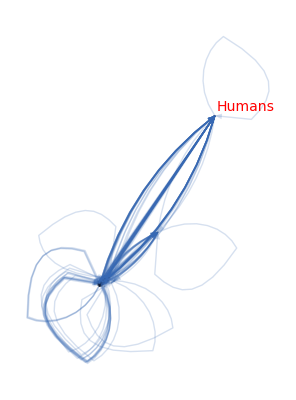

```mathematica
g[gen]=Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

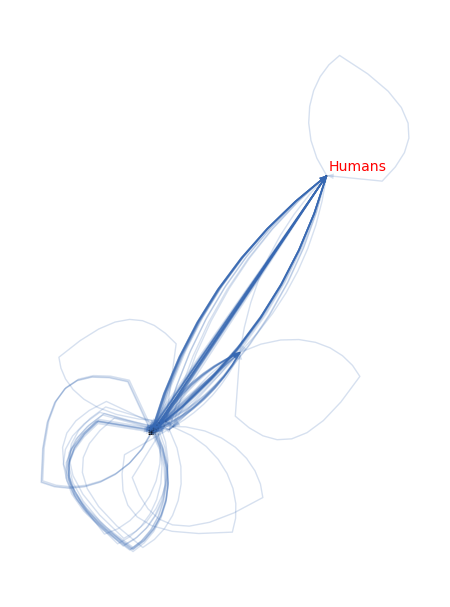

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1980

```mathematica
gen=1980
```

1980

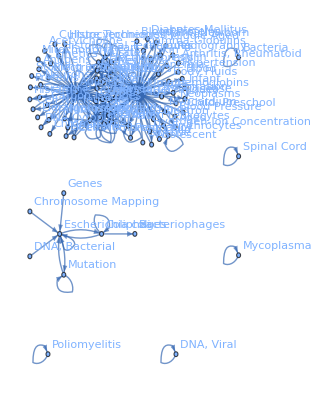

```mathematica
Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Adult,Rats,Middle Aged,Escherichia coli,Microscopy, Electron,Child,Aged,Mice,Adolescent,In Vitro Techniques,Research,Time Factors,Mutation,Cats,Rabbits,Liver,Kidney,Muscles,Infant,Neoplasms,Dogs,Pregnancy,Electrons,Infant, Newborn,Heart,Child, Preschool,Erythrocytes,Methods,Blood,Microscopy,Brain,Neurons,Calcium,Coliphages,Blood Pressure,Bacteria,Potassium,Body Fluids,Guinea Pigs,Histological Techniques,Tritium,gamma-Globulins,DNA, Bacterial,Blood Proteins,Spinal Cord,Histocytochemistry,Sodium,Cell Membrane,Proteins,Diabetes Mellitus,Antibodies,Mitochondria,Mycoplasma,Anemia,Hemoglobins,Electric Stimulation,Poliomyelitis,Cytoplasm,Lung,Kinetics,Respiration,Cerebral Cortex,Hypertension,Lipids,Skin,Antigens,Electrophysiology,Arthritis, Rheumatoid,Culture Techniques,Electrophoresis,Genes,DNA,Chromosomes,Radiography,Glucose,Leukocytes,Histamine,Bacteriophages,Disease,Insulin,Hydrogen-Ion Concentration,Acetylcholine,Carbon Isotopes,Cell Nucleus,Chromosome Mapping,Myocardium,Staining and Labeling,DNA, Viral}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Animals->Humans,Male->Humans,Female->Humans,Humans->Animals,Adult->Humans,Animals->Rats,Rats->Animals,Male->Animals,Middle Aged->Humans,Escherichia coli->Escherichia coli,Humans->Female,Microscopy, Electron->Microscopy, Electron,Animals->Microscopy, Electron,Humans->Male,Rats->Humans,Female->Animals,Rats->Rats,Microscopy, Electron->Animals,Child->Humans,Aged->Humans,Animals->Mice,Mice->Animals,Animals->Male,Adolescent->Humans,Humans->Adult,Female->Female,Male->Male,Animals->In Vitro Techniques,Animals->Research,Animals->Female,Time Factors->Humans,Mutation->Escherichia coli,In Vitro Techniques->Humans,In Vitro Techniques->Animals,Animals->Cats,Microscopy, Electron->Humans,Male->Rats,Time Factors->Animals,Rabbits->Animals,Liver->Humans,Kidney->Humans,Animals->Rabbits,Animals->Liver,Cats->Animals,Humans->Rats,Female->Male,Animals->Muscles,Infant->Humans,Humans->Neoplasms,Mutation->Mutation,Male->Female,Humans->Microscopy, Electron,Dogs->Humans,Humans->Middle Aged,Liver->Animals,Rabbits->Humans,Mice->Humans,Animals->Kidney,Pregnancy->Humans,Microscopy, Electron->Electrons,Research->Humans,Humans->Kidney,Mice->Mice,Humans->Child,Liver->Liver,Infant, Newborn->Humans,Escherichia coli->Mutation,Humans->Heart,Animals->Electrons,Child, Preschool->Humans,Humans->Erythrocytes,Erythrocytes->Humans,Female->Rats,Methods->Humans,Humans->Liver,Humans->Blood,Microscopy, Electron->Microscopy,Muscles->Muscles,Brain->Humans,Humans->Brain,Humans->In Vitro Techniques,Neurons->Animals,Neoplasms->Humans,Animals->Calcium,Animals->Microscopy,Humans->Infant,Humans->Research,Humans->Pregnancy,Cats->Cats,Male->Adult,Animals->Neurons,Male->Microscopy, Electron,Muscles->Humans,Coliphages->Escherichia coli,Blood Pressure->Humans,Kidney->Kidney,Bacteria->Bacteria,Animals->Potassium,Cats->Humans,Erythrocytes->Erythrocytes,Humans->Body Fluids,Heart->Heart,Rats->Microscopy, Electron,Adult->Male,Animals->Guinea Pigs,Animals->Histological Techniques,Adult->Female,Animals->Tritium,Humans->gamma-Globulins,Muscles->Animals,DNA, Bacterial->Escherichia coli,Humans->Blood Proteins,Calcium->Calcium,Animals->Brain,Animals->Heart,Spinal Cord->Spinal Cord,Kidney->Animals,Guinea Pigs->Animals,Coliphages->Coliphages,Heart->Humans,Escherichia coli->Coliphages,Rats->Liver,Animals->Histocytochemistry,Sodium->Humans,Cell Membrane->Animals,Female->Microscopy, Electron,Potassium->Humans,Cell Membrane->Microscopy, Electron,Humans->Muscles,Humans->Infant, Newborn,Animals->Proteins,Humans->Rabbits,Humans->Aged,Humans->Diabetes Mellitus,Sodium->Animals,Humans->Antibodies,Animals->Mitochondria,Female->Adult,Mycoplasma->Mycoplasma,Humans->Anemia,Humans->Hemoglobins,Electric Stimulation->Animals,Animals->Cell Membrane,Animals->Dogs,Humans->Mice,Poliomyelitis->Poliomyelitis,Humans->Adolescent,Animals->Cytoplasm,Lung->Humans,Antibodies->Humans,Adult->Adult,Microscopy, Electron->Rats,Hemoglobins->Hemoglobins,Liver->Rats,Male->Liver,Kinetics->Animals,Potassium->Potassium,Potassium->Animals,Respiration->Humans,Animals->Cerebral Cortex,Hypertension->Humans,Lipids->Humans,Tritium->Animals,Guinea Pigs->Humans,Rats->Male,Calcium->Animals,Skin->Humans,Dogs->Animals,Cytoplasm->Microscopy, Electron,Animals->Antigens,Animals->Electrophysiology,Animals->Sodium,Arthritis, Rheumatoid->Humans,Animals->Culture Techniques,Animals->Electrophoresis,Animals->Antibodies,Genes->Escherichia coli,Animals->DNA,Animals->Chromosomes,Radiography->Humans,Glucose->Humans,Humans->Leukocytes,Animals->Histamine,Coliphages->Bacteriophages,Humans->Disease,Male->In Vitro Techniques,Humans->Insulin,Hydrogen-Ion Concentration->Humans,Histocytochemistry->Animals,Animals->Acetylcholine,Humans->Respiration,Humans->Electrophoresis,Animals->Carbon Isotopes,Cell Nucleus->Animals,Calcium->Humans,Male->Mice,Animals->Methods,Animals->Cell Nucleus,Chromosome Mapping->Escherichia coli,Humans->Lipids,Myocardium->Humans,Pregnancy->Female,Animals->Staining and Labeling,DNA, Viral->DNA, Viral}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ2CitingCitedMeSHgraph[gen],EdgeWeight]
```

{239.524,108.332,77.2171,59.7502,56.1569,39.7823,36.0904,32.4618,31.0771,28.5661,27.1698,25.2304,23.8006,23.5227,23.4768,23.2045,22.0898,22.0168,19.2024,17.9209,16.6841,16.5167,16.152,16.0072,15.4429,15.2358,15.0856,14.8655,14.7024,14.1528,13.2149,12.654,12.6066,12.4097,12.2423,12.0515,11.9053,11.7636,11.6061,11.6024,11.2693,11.2625,11.0474,10.8938,10.6191,10.5553,10.4549,10.2101,10.1108,9.86067,9.84902,9.80938,9.76202,9.66548,9.63548,9.4595,9.35057,9.34223,9.24264,9.08464,9.05312,8.99493,8.6774,8.5137,8.47149,8.39096,8.23803,8.16422,8.09763,8.09319,8.08092,8.02576,8.00802,7.97423,7.9225,7.91089,7.89046,7.53099,7.45612,7.42623,7.40812,7.37601,7.36599,7.36308,7.35821,7.3558,7.06712,7.03176,7.02872,7.01641,6.91525,6.91379,6.88149,6.87836,6.85649,6.72414,6.6095,6.53391,6.52637,6.51156,6.50464,6.4914,6.49106,6.43943,6.3972,6.38478,6.37582,6.37486,6.3524,6.3464,6.34247,6.33473,6.32811,6.32619,6.30618,6.28078,6.27896,6.21729,6.21436,6.20746,6.13218,6.12644,6.09775,6.09649,6.06557,6.06462,6.05582,6.02162,5.99417,5.94615,5.92153,5.89557,5.87969,5.84421,5.83521,5.79854,5.79837,5.79718,5.7827,5.77072,5.75769,5.74471,5.73297,5.71045,5.68242,5.65135,5.63529,5.60325,5.60223,5.55824,5.54612,5.53644,5.4984,5.47263,5.47204,5.45971,5.45942,5.3982,5.38541,5.36825,5.33198,5.31532,5.31415,5.28454,5.25188,5.21327,5.20391,5.20351,5.18102,5.16764,5.14671,5.14164,5.10782,5.10619,5.0882,5.06133,5.04472,5.03231,5.01753,5.01532,5.01183,4.99482,4.97139,4.96553,4.96184,4.92211,4.89277,4.89026,4.8789,4.84888,4.83771,4.83117,4.82318,4.81551,4.81001,4.80921,4.79448,4.78594,4.78508,4.77705,4.77238,4.76828,4.76818,4.76132,4.74708,4.72463}

```mathematica
topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

239.524 | 39.7823 | 23.2045 | 23.8006 | 15.0856 | 10.4549 | 9.4595 | 0 | 9.66548 | 8.39096 | 5.83521 | 5.63529 | 5.60223 | 7.36599 | 7.02872 | 0 | 0 | 0 | 5.84421 | 7.89046 | 8.5137 | 5.92153 | 7.03176 | 9.84902 | 0 | 7.01641 | 0 | 5.89557 | 8.09319 | 0 | 8.00802 | 0 | 7.53099 | 0 | 7.37601 | 0 | 0 | 0 | 0 | 0 | 0 | 6.49106 | 0 | 0 | 0 | 6.34247 | 0 | 6.32619 | 0 | 0 | 0 | 0 | 0 | 5.79854 | 5.79718 | 0 | 0 | 5.74471 | 5.73297 | 0 | 0 | 0 | 0 | 0 | 4.82318 | 0 | 0 | 4.76828 | 0 | 0 | 0 | 0 | 0 | 4.81551 | 0 | 0 | 0 | 0 | 0 | 4.96553 | 0 | 0 | 4.89277 | 4.8789 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
77.2171 | 108.332 | 15.4429 | 12.654 | 0 | 32.4618 | 0 | 0 | 23.4768 | 0 | 0 | 16.152 | 0 | 14.1528 | 13.2149 | 0 | 0 | 11.9053 | 10.8938 | 10.6191 | 9.08464 | 10.1108 | 0 | 0 | 5.65135 | 0 | 8.08092 | 0 | 6.27896 | 0 | 0 | 4.78508 | 0 | 7.06712 | 6.28078 | 6.88149 | 7.3558 | 0 | 0 | 0 | 6.51156 | 0 | 6.37582 | 6.37486 | 6.3464 | 0 | 0 | 0 | 0 | 6.06557 | 5.10619 | 5.68242 | 5.87969 | 0 | 5.03231 | 5.7827 | 0 | 0 | 0 | 0 | 0 | 5.55824 | 0 | 0 | 0 | 5.31532 | 0 | 0 | 0 | 5.14164 | 5.10782 | 0 | 5.06133 | 5.04472 | 0 | 5.01532 | 5.01183 | 0 | 0 | 0 | 4.96184 | 0 | 0 | 0 | 0 | 4.83117 | 4.81001 | 4.77705 | 0 | 0 | 4.74708 | 0
59.7502 | 28.5661 | 14.7024 | 9.76202 | 6.91379 | 11.6061 | 0 | 0 | 6.87836 | 0 | 0 | 4.78594 | 0 | 4.89026 | 0 | 0 | 0 | 0 | 0 | 5.45942 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
56.1569 | 22.0168 | 10.2101 | 14.8655 | 5.77072 | 7.9225 | 0 | 0 | 6.02162 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
36.0904 | 0 | 6.38478 | 6.3524 | 5.4984 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
22.0898 | 31.0771 | 5.20391 | 0 | 0 | 19.2024 | 0 | 0 | 6.3972 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.09649 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
27.1698 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 25.2304 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.09763 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.09775 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.7636 | 17.9209 | 0 | 0 | 0 | 5.47263 | 0 | 0 | 23.5227 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.99493 | 0 | 0 | 0 | 0 | 0 | 0 | 7.45612 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16.6841 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16.5167 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.24264 | 16.0072 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.47149 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15.2358 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.2423 | 12.0515 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.6774 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.6066 | 11.6024 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.4097 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.80938 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.50464 | 10.5553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.91525 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.34223 | 11.2693 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.2625 | 9.35057 | 0 | 0 | 0 | 5.45971 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.23803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.0474 | 6.21436 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.53391 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.85649 | 6.33473 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.42623 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.86067 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.35821 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.63548 | 5.16764 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.05312 | 0 | 0 | 4.76132 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.16422 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.12644 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.43943 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.02576 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.97423 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.4914 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.91089 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.40812 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 7.36308 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.79448 | 5.20351 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.30618 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.72414 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.13218 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.92211 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.6095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.52637 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.99417 | 5.36825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.38541 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.21327 | 6.20746 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5.25188 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.32811 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.21729 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4.83771 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.06462 | 5.79837 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6.05582 | 0 | 0 | 0 | 0 | 0 | 0 | 5.94615 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.53644 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.75769 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.47204 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5.71045 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.60325 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.14671 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.54612 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5.3982 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.33198 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.31415 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.28454 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.18102 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.0882 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.01753 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.99482 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.97139 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.84888 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4.80921 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.77238 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.76818 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.72463

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{571.184,542.64,153.315,122.964,54.326,90.067,27.1698,39.4258,75.1309,16.6841,16.5167,33.7213,15.2358,24.2938,8.6774,24.209,22.2191,23.9752,20.6115,34.3108,23.7956,20.6174,9.86067,7.35821,14.8031,13.8144,0,8.16422,12.5659,8.02576,14.4656,7.91089,0,0,7.40812,7.36308,16.3042,17.7784,6.6095,6.52637,16.7478,0,11.4207,0,5.25188,0,6.32811,0,6.21729,4.83771,11.863,12.002,0,0,5.53644,0,5.75769,0,5.47204,5.71045,5.60325,5.14671,5.54612,5.3982,5.33198,0,5.31415,5.28454,5.18102,0,0,5.0882,0,0,5.01753,0,0,4.99482,4.97139,0,0,0,0,0,4.84888,0,0,4.80921,4.77238,4.76818,0,4.72463}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{833.04,398.252,75.1487,72.1958,33.2685,92.5801,9.4595,60.4823,87.055,8.39096,5.83521,35.0448,5.60223,26.409,20.2436,0,17.907,18.8206,16.738,38.3035,24.1322,23.4586,7.03176,9.84902,5.65135,7.01641,17.0759,5.89557,20.8116,0,14.4994,4.78508,7.53099,14.5232,13.6568,6.88149,13.662,12.2299,0,6.52637,11.897,6.49106,6.37582,6.37486,6.3464,6.34247,0,6.32619,6.21729,6.06557,5.10619,5.68242,5.87969,5.79854,10.8295,5.7827,5.75769,5.74471,11.205,0,5.60325,5.55824,0,0,4.82318,5.31532,0,4.76828,0,5.14164,5.10782,0,5.06133,9.86022,0,5.01532,5.01183,0,0,4.96553,4.96184,4.92211,4.89277,4.8789,0,4.83117,4.81001,4.77705,0,0,4.74708,4.72463}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{1404.22,940.892,228.463,195.16,87.5945,182.647,36.6293,99.9081,162.186,25.075,22.3519,68.7661,20.838,50.7029,28.921,24.209,40.1261,42.7958,37.3495,72.6143,47.9279,44.076,16.8924,17.2072,20.4545,20.8308,17.0759,14.0598,33.3774,8.02576,28.9651,12.696,7.53099,14.5232,21.0649,14.2446,29.9661,30.0083,6.6095,13.0527,28.6448,6.49106,17.7966,6.37486,11.5983,6.34247,6.32811,6.32619,12.4346,10.9033,16.9692,17.6844,5.87969,5.79854,16.3659,5.7827,11.5154,5.74471,16.6771,5.71045,11.2065,10.7049,5.54612,5.3982,10.1552,5.31532,5.31415,10.0528,5.18102,5.14164,5.10782,5.0882,5.06133,9.86022,5.01753,5.01532,5.01183,4.99482,4.97139,4.96553,4.96184,4.92211,4.89277,4.8789,4.84888,4.83117,4.81001,9.58626,4.77238,4.76818,4.74708,9.44927}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{571.184,833.04},{542.64,398.252},{153.315,75.1487},{122.964,72.1958},{54.326,33.2685},{90.067,92.5801},{27.1698,9.4595},{39.4258,60.4823},{75.1309,87.055},{16.6841,8.39096},{16.5167,5.83521},{33.7213,35.0448},{15.2358,5.60223},{24.2938,26.409},{8.6774,20.2436},{24.209,0},{22.2191,17.907},{23.9752,18.8206},{20.6115,16.738},{34.3108,38.3035},{23.7956,24.1322},{20.6174,23.4586},{9.86067,7.03176},{7.35821,9.84902},{14.8031,5.65135},{13.8144,7.01641},{0,17.0759},{8.16422,5.89557},{12.5659,20.8116},{8.02576,0},{14.4656,14.4994},{7.91089,4.78508},{0,7.53099},{0,14.5232},{7.40812,13.6568},{7.36308,6.88149},{16.3042,13.662},{17.7784,12.2299},{6.6095,0},{6.52637,6.52637},{16.7478,11.897},{0,6.49106},{11.4207,6.37582},{0,6.37486},{5.25188,6.3464},{0,6.34247},{6.32811,0},{0,6.32619},{6.21729,6.21729},{4.83771,6.06557},{11.863,5.10619},{12.002,5.68242},{0,5.87969},{0,5.79854},{5.53644,10.8295},{0,5.7827},{5.75769,5.75769},{0,5.74471},{5.47204,11.205},{5.71045,0},{5.60325,5.60325},{5.14671,5.55824},{5.54612,0},{5.3982,0},{5.33198,4.82318},{0,5.31532},{5.31415,0},{5.28454,4.76828},{5.18102,0},{0,5.14164},{0,5.10782},{5.0882,0},{0,5.06133},{0,9.86022},{5.01753,0},{0,5.01532},{0,5.01183},{4.99482,0},{4.97139,0},{0,4.96553},{0,4.96184},{0,4.92211},{0,4.89277},{0,4.8789},{4.84888,0},{0,4.83117},{0,4.81001},{4.80921,4.77705},{4.77238,0},{4.76818,0},{0,4.74708},{4.72463,4.72463}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

101.005

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.299405],Animals->Animals→Thickness[0.135415],Animals->Humans→Thickness[0.0965213],Male->Humans→Thickness[0.0746878],Female->Humans→Thickness[0.0701962],Humans->Animals→Thickness[0.0497279],Adult->Humans→Thickness[0.0451131],Animals->Rats→Thickness[0.0405773],Rats->Animals→Thickness[0.0388464],Male->Animals→Thickness[0.0357077],Middle Aged->Humans→Thickness[0.0339622],Escherichia coli->Escherichia coli→Thickness[0.031538],Humans->Female→Thickness[0.0297508],Microscopy, Electron->Microscopy, Electron→Thickness[0.0294033],Animals->Microscopy, Electron→Thickness[0.029346],Humans->Male→Thickness[0.0290057],Rats->Humans→Thickness[0.0276123],Female->Animals→Thickness[0.027521],Rats->Rats→Thickness[0.024003],Microscopy, Electron->Animals→Thickness[0.0224011],Child->Humans→Thickness[0.0208551],Aged->Humans→Thickness[0.0206459],Animals->Mice→Thickness[0.0201901],Mice->Animals→Thickness[0.020009],Animals->Male→Thickness[0.0193036],Adolescent->Humans→Thickness[0.0190447],Humans->Adult→Thickness[0.018857],Female->Female→Thickness[0.0185818],Male->Male→Thickness[0.018378],Animals->In Vitro Techniques→Thickness[0.017691],Animals->Research→Thickness[0.0165186],Animals->Female→Thickness[0.0158175],Time Factors->Humans→Thickness[0.0157582],Mutation->Escherichia coli→Thickness[0.0155121],In Vitro Techniques->Humans→Thickness[0.0153029],In Vitro Techniques->Animals→Thickness[0.0150644],Animals->Cats→Thickness[0.0148816],Microscopy, Electron->Humans→Thickness[0.0147045],Male->Rats→Thickness[0.0145077],Time Factors->Animals→Thickness[0.014503],Rabbits->Animals→Thickness[0.0140866],Liver->Humans→Thickness[0.0140781],Kidney->Humans→Thickness[0.0138092],Animals->Rabbits→Thickness[0.0136172],Animals->Liver→Thickness[0.0132739],Cats->Animals→Thickness[0.0131941],Humans->Rats→Thickness[0.0130686],Female->Male→Thickness[0.0127627],Animals->Muscles→Thickness[0.0126385],Infant->Humans→Thickness[0.0123258],Humans->Neoplasms→Thickness[0.0123113],Mutation->Mutation→Thickness[0.0122617],Male->Female→Thickness[0.0122025],Humans->Microscopy, Electron→Thickness[0.0120819],Dogs->Humans→Thickness[0.0120444],Humans->Middle Aged→Thickness[0.0118244],Liver->Animals→Thickness[0.0116882],Rabbits->Humans→Thickness[0.0116778],Mice->Humans→Thickness[0.0115533],Animals->Kidney→Thickness[0.0113558],Pregnancy->Humans→Thickness[0.0113164],Microscopy, Electron->Electrons→Thickness[0.0112437],Research->Humans→Thickness[0.0108467],Humans->Kidney→Thickness[0.0106421],Mice->Mice→Thickness[0.0105894],Humans->Child→Thickness[0.0104887],Liver->Liver→Thickness[0.0102975],Infant, Newborn->Humans→Thickness[0.0102053],Escherichia coli->Mutation→Thickness[0.010122],Humans->Heart→Thickness[0.0101165],Animals->Electrons→Thickness[0.0101012],Child, Preschool->Humans→Thickness[0.0100322],Humans->Erythrocytes→Thickness[0.01001],Erythrocytes->Humans→Thickness[0.00996779],Female->Rats→Thickness[0.00990312],Methods->Humans→Thickness[0.00988862],Humans->Liver→Thickness[0.00986307],Humans->Blood→Thickness[0.00941374],Microscopy, Electron->Microscopy→Thickness[0.00932015],Muscles->Muscles→Thickness[0.00928278],Brain->Humans→Thickness[0.00926015],Humans->Brain→Thickness[0.00922001],Humans->In Vitro Techniques→Thickness[0.00920749],Neurons->Animals→Thickness[0.00920386],Neoplasms->Humans→Thickness[0.00919776],Animals->Calcium→Thickness[0.00919475],Animals->Microscopy→Thickness[0.0088339],Humans->Infant→Thickness[0.00878969],Humans->Research→Thickness[0.0087859],Humans->Pregnancy→Thickness[0.00877051],Cats->Cats→Thickness[0.00864407],Male->Adult→Thickness[0.00864224],Animals->Neurons→Thickness[0.00860187],Male->Microscopy, Electron→Thickness[0.00859795],Muscles->Humans→Thickness[0.00857061],Coliphages->Escherichia coli→Thickness[0.00840517],Blood Pressure->Humans→Thickness[0.00826188],Kidney->Kidney→Thickness[0.00816738],Bacteria->Bacteria→Thickness[0.00815796],Animals->Potassium→Thickness[0.00813945],Cats->Humans→Thickness[0.0081308],Erythrocytes->Erythrocytes→Thickness[0.00811425],Humans->Body Fluids→Thickness[0.00811382],Heart->Heart→Thickness[0.00804928],Rats->Microscopy, Electron→Thickness[0.0079965],Adult->Male→Thickness[0.00798098],Animals->Guinea Pigs→Thickness[0.00796978],Animals->Histological Techniques→Thickness[0.00796857],Adult->Female→Thickness[0.00794049],Animals->Tritium→Thickness[0.007933],Humans->gamma-Globulins→Thickness[0.00792809],Muscles->Animals→Thickness[0.00791841],DNA, Bacterial->Escherichia coli→Thickness[0.00791013],Humans->Blood Proteins→Thickness[0.00790774],Calcium->Calcium→Thickness[0.00788272],Animals->Brain→Thickness[0.00785097],Animals->Heart→Thickness[0.0078487],Spinal Cord->Spinal Cord→Thickness[0.00777162],Kidney->Animals→Thickness[0.00776795],Guinea Pigs->Animals→Thickness[0.00775933],Coliphages->Coliphages→Thickness[0.00766522],Heart->Humans→Thickness[0.00765804],Escherichia coli->Coliphages→Thickness[0.00762219],Rats->Liver→Thickness[0.00762061],Animals->Histocytochemistry→Thickness[0.00758197],Sodium->Humans→Thickness[0.00758078],Cell Membrane->Animals→Thickness[0.00756978],Female->Microscopy, Electron→Thickness[0.00752702],Potassium->Humans→Thickness[0.00749271],Cell Membrane->Microscopy, Electron→Thickness[0.00743269],Humans->Muscles→Thickness[0.00740191],Humans->Infant, Newborn→Thickness[0.00736947],Animals->Proteins→Thickness[0.00734962],Humans->Rabbits→Thickness[0.00730526],Humans->Aged→Thickness[0.00729402],Humans->Diabetes Mellitus→Thickness[0.00724817],Sodium->Animals→Thickness[0.00724796],Humans->Antibodies→Thickness[0.00724648],Animals->Mitochondria→Thickness[0.00722837],Female->Adult→Thickness[0.0072134],Mycoplasma->Mycoplasma→Thickness[0.00719711],Humans->Anemia→Thickness[0.00718089],Humans->Hemoglobins→Thickness[0.00716622],Electric Stimulation->Animals→Thickness[0.00713806],Animals->Cell Membrane→Thickness[0.00710302],Animals->Dogs→Thickness[0.00706419],Humans->Mice→Thickness[0.00704411],Poliomyelitis->Poliomyelitis→Thickness[0.00700406],Humans->Adolescent→Thickness[0.00700278],Animals->Cytoplasm→Thickness[0.0069478],Lung->Humans→Thickness[0.00693265],Antibodies->Humans→Thickness[0.00692055],Adult->Adult→Thickness[0.006873],Microscopy, Electron->Rats→Thickness[0.00684079],Hemoglobins->Hemoglobins→Thickness[0.00684006],Liver->Rats→Thickness[0.00682463],Male->Liver→Thickness[0.00682428],Kinetics->Animals→Thickness[0.00674775],Potassium->Potassium→Thickness[0.00673176],Potassium->Animals→Thickness[0.00671031],Respiration->Humans→Thickness[0.00666497],Animals->Cerebral Cortex→Thickness[0.00664415],Hypertension->Humans→Thickness[0.00664269],Lipids->Humans→Thickness[0.00660567],Tritium->Animals→Thickness[0.00656484],Guinea Pigs->Humans→Thickness[0.00651658],Rats->Male→Thickness[0.00650489],Calcium->Animals→Thickness[0.00650439],Skin->Humans→Thickness[0.00647627],Dogs->Animals→Thickness[0.00645954],Cytoplasm->Microscopy, Electron→Thickness[0.00643338],Animals->Antigens→Thickness[0.00642705],Animals->Electrophysiology→Thickness[0.00638478],Animals->Sodium→Thickness[0.00638274],Arthritis, Rheumatoid->Humans→Thickness[0.00636025],Animals->Culture Techniques→Thickness[0.00632666],Animals->Electrophoresis→Thickness[0.00630589],Animals->Antibodies→Thickness[0.00629039],Genes->Escherichia coli→Thickness[0.00627192],Animals->DNA→Thickness[0.00626915],Animals->Chromosomes→Thickness[0.00626479],Radiography->Humans→Thickness[0.00624352],Glucose->Humans→Thickness[0.00621424],Humans->Leukocytes→Thickness[0.00620691],Animals->Histamine→Thickness[0.0062023],Coliphages->Bacteriophages→Thickness[0.00615263],Humans->Disease→Thickness[0.00611597],Male->In Vitro Techniques→Thickness[0.00611283],Humans->Insulin→Thickness[0.00609862],Hydrogen-Ion Concentration->Humans→Thickness[0.00606109],Histocytochemistry->Animals→Thickness[0.00604714],Animals->Acetylcholine→Thickness[0.00603897],Humans->Respiration→Thickness[0.00602897],Humans->Electrophoresis→Thickness[0.00601939],Animals->Carbon Isotopes→Thickness[0.00601251],Cell Nucleus->Animals→Thickness[0.00601151],Calcium->Humans→Thickness[0.0059931],Male->Mice→Thickness[0.00598243],Animals->Methods→Thickness[0.00598135],Animals->Cell Nucleus→Thickness[0.00597131],Chromosome Mapping->Escherichia coli→Thickness[0.00596548],Humans->Lipids→Thickness[0.00596035],Myocardium->Humans→Thickness[0.00596022],Pregnancy->Female→Thickness[0.00595165],Animals->Staining and Labeling→Thickness[0.00593385],DNA, Viral->DNA, Viral→Thickness[0.00590579]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

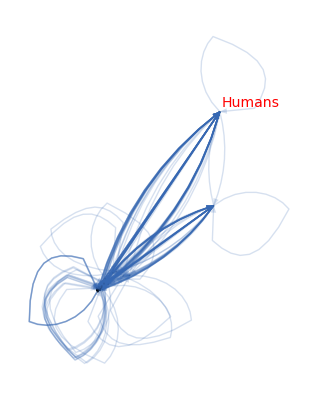

```mathematica
g[gen]=Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

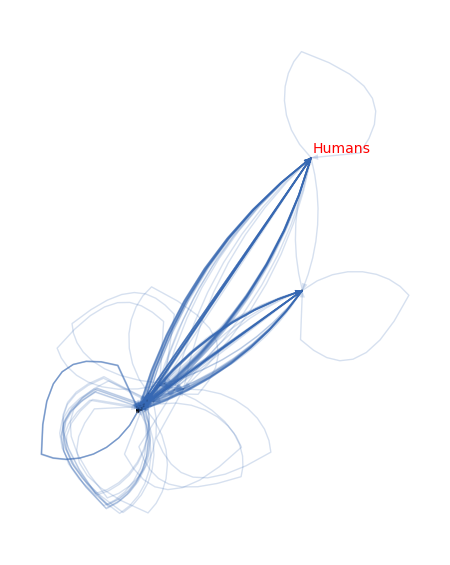

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1985

```mathematica
gen=1985
```

1985

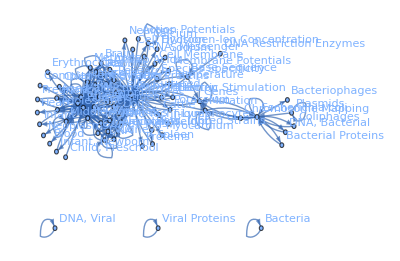

```mathematica
Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Adult,Rats,Mice,Middle Aged,Escherichia coli,Aged,Microscopy, Electron,Child,Adolescent,In Vitro Techniques,Liver,Kinetics,Cats,Time Factors,Mutation,Rabbits,Base Sequence,Cell Line,Molecular Weight,Brain,Infant,DNA,Cells, Cultured,Research,Neurons,Pregnancy,Infant, Newborn,Child, Preschool,Muscles,Kidney,Calcium,Cell Membrane,Sodium,Cattle,Erythrocytes,Guinea Pigs,Membrane Potentials,Tritium,DNA, Viral,Amino Acids,Methods,Potassium,Genes,Electric Stimulation,Temperature,DNA, Bacterial,Bacterial Proteins,Proteins,Coliphages,Plasmids,Rats, Inbred Strains,Antibodies,Spleen,Neoplasms,Viral Proteins,Action Potentials,Antigens,Species Specificity,Dogs,RNA, Messenger,Hydrogen-Ion Concentration,Cell Division,Blood,Bacteria,Bacteriophages,DNA Restriction Enzymes,Complement System Proteins,Lymphocytes,Heart,Myocardium,Chromosome Mapping,T-Lymphocytes}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Animals->Humans,Male->Humans,Female->Humans,Humans->Animals,Adult->Humans,Humans->Male,Male->Animals,Animals->Rats,Rats->Animals,Humans->Female,Mice->Animals,Middle Aged->Humans,Animals->Mice,Female->Animals,Humans->Adult,Escherichia coli->Escherichia coli,Male->Male,Animals->Male,Animals->Female,Female->Female,Rats->Rats,Rats->Humans,Humans->Middle Aged,Aged->Humans,Mice->Mice,Male->Female,Female->Male,Animals->Microscopy, Electron,Child->Humans,Adolescent->Humans,In Vitro Techniques->Animals,Microscopy, Electron->Animals,Animals->In Vitro Techniques,Animals->Liver,Male->Rats,Animals->Kinetics,Humans->Child,Animals->Cats,Time Factors->Animals,Male->Adult,Mutation->Escherichia coli,Mice->Humans,Mutation->Mutation,Animals->Rabbits,Rabbits->Animals,Time Factors->Humans,Kinetics->Animals,Adult->Male,Microscopy, Electron->Microscopy, Electron,Humans->Aged,Base Sequence->Base Sequence,Female->Adult,Adult->Adult,Humans->Rats,Humans->Adolescent,In Vitro Techniques->Humans,Humans->Mice,Liver->Liver,Cell Line->Animals,Escherichia coli->Mutation,Animals->Molecular Weight,Cats->Animals,Microscopy, Electron->Humans,Kinetics->Humans,Liver->Humans,Animals->Brain,Infant->Humans,Humans->Infant,Animals->Cell Line,Adult->Female,Animals->DNA,Animals->Time Factors,Humans->Time Factors,Rabbits->Humans,Liver->Animals,Humans->Liver,Cells, Cultured->Animals,Animals->Research,Rats->Male,Male->Middle Aged,Animals->Neurons,Molecular Weight->Animals,Animals->Base Sequence,Pregnancy->Humans,Infant, Newborn->Humans,Middle Aged->Male,Neurons->Animals,Child, Preschool->Humans,Kinetics->Kinetics,Base Sequence->Animals,Female->Rats,Muscles->Animals,Animals->Kidney,Calcium->Animals,Animals->Muscles,Female->Middle Aged,Animals->Calcium,Rats->Liver,DNA->Animals,Cell Membrane->Animals,Humans->Kidney,Animals->Cell Membrane,Middle Aged->Adult,Humans->Brain,Animals->Sodium,Adult->Middle Aged,Animals->Cattle,Erythrocytes->Humans,Humans->Kinetics,Animals->Guinea Pigs,Kidney->Humans,Humans->Erythrocytes,Cats->Cats,Female->Mice,Middle Aged->Female,Adult->Animals,Male->Mice,Membrane Potentials->Animals,DNA->DNA,Humans->Rabbits,Animals->Tritium,Muscles->Humans,DNA, Viral->DNA, Viral,Humans->Microscopy, Electron,Animals->Amino Acids,Guinea Pigs->Animals,Research->Humans,Humans->Molecular Weight,Male->Liver,Sodium->Animals,Muscles->Muscles,Brain->Animals,Humans->In Vitro Techniques,Humans->Methods,Potassium->Animals,Genes->Animals,Humans->Infant, Newborn,Animals->Electric Stimulation,Animals->Temperature,DNA, Bacterial->Escherichia coli,Animals->Methods,Middle Aged->Middle Aged,Animals->Genes,Bacterial Proteins->Escherichia coli,Male->Time Factors,Animals->Potassium,Animals->Proteins,Humans->Pregnancy,Animals->Membrane Potentials,Electric Stimulation->Animals,Escherichia coli->Coliphages,Animals->Cells, Cultured,Genes->Escherichia coli,Plasmids->Plasmids,Cell Line->Cell Line,Rats, Inbred Strains->Animals,Rats->Female,Animals->Antibodies,Genes->Genes,Spleen->Animals,Humans->Neoplasms,Escherichia coli->Genes,Male->Aged,Viral Proteins->Viral Proteins,Cats->Humans,Humans->Amino Acids,Animals->Adult,Action Potentials->Animals,Animals->Antigens,Coliphages->Escherichia coli,Cattle->Animals,Cell Line->Humans,Humans->Cell Line,Species Specificity->Animals,Dogs->Humans,Cells, Cultured->Humans,Animals->RNA, Messenger,Aged->Male,Genes->Mutation,Humans->Antigens,Antibodies->Humans,Animals->Hydrogen-Ion Concentration,Base Sequence->Genes,Methods->Humans,Animals->Cell Division,Kidney->Animals,Molecular Weight->Molecular Weight,Guinea Pigs->Humans,Humans->Blood,Animals->Spleen,Humans->Muscles,Male->Child,Animals->Dogs,Rats->Microscopy, Electron,Dogs->Animals,Male->Microscopy, Electron,Bacteria->Bacteria,Liver->Rats,Mutation->Animals,Escherichia coli->Bacteriophages,Mice->Female,DNA Restriction Enzymes->Base Sequence,Brain->Humans,Humans->Complement System Proteins,Female->Child,Lymphocytes->Humans,Mice->Rats,Humans->Antibodies,Humans->Heart,Animals->Myocardium,Plasmids->Escherichia coli,Escherichia coli->DNA, Bacterial,Calcium->Calcium,Escherichia coli->Chromosome Mapping,Escherichia coli->Bacterial Proteins,In Vitro Techniques->In Vitro Techniques,RNA, Messenger->Animals,T-Lymphocytes->Animals,Male->Adolescent,Mutation->Chromosome Mapping,Female->Aged,Lymphocytes->Animals,Humans->Research,DNA->Humans,Female->Adolescent,Mutation->Genes}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ2CitingCitedMeSHgraph[gen],EdgeWeight]
```

{278.168,186.374,103.18,89.4636,81.5337,66.515,55.6512,52.58,49.6346,47.0718,46.7714,46.5824,40.9276,40.1309,38.8401,38.6887,37.5095,34.1405,34.139,31.3555,27.6418,27.343,27.1272,26.9018,25.8788,25.1177,24.8683,23.8292,23.4662,22.8186,21.2585,21.2324,21.0957,20.7002,20.3382,19.5813,19.3943,18.7925,18.1291,17.7962,17.7933,17.4392,17.3291,17.3189,17.1429,17.1181,16.8495,16.7658,16.5744,16.3052,16.2441,15.7108,15.6324,15.333,14.7913,14.1635,13.9454,13.9285,13.7554,13.6954,13.6839,13.6442,13.4796,13.4283,13.4129,13.3219,13.2632,13.2016,13.1591,13.1177,13.1136,13.0975,13.0706,12.8816,12.7582,12.6527,12.6423,12.6068,12.6017,12.5309,12.3509,12.047,11.945,11.3919,11.3614,11.3234,11.2865,11.2225,11.2194,11.0469,10.9909,10.9469,10.8882,10.7565,10.7535,10.6834,10.5353,10.5035,10.472,10.45,10.4457,10.3906,10.2746,10.2545,10.0719,10.0425,9.98267,9.74468,9.69283,9.67106,9.66582,9.55709,9.45421,9.39927,9.33014,9.29398,9.27845,9.15526,9.15366,9.08464,9.07812,9.05141,8.905,8.87143,8.77815,8.75839,8.73176,8.724,8.66836,8.61982,8.54628,8.54486,8.47956,8.455,8.45483,8.43824,8.42275,8.41668,8.38102,8.3614,8.3025,8.27656,8.12266,8.08108,8.02316,8.02249,7.96462,7.93295,7.90573,7.88495,7.80227,7.74153,7.71275,7.63573,7.60716,7.59631,7.58902,7.56083,7.54467,7.50537,7.47144,7.46916,7.46378,7.39481,7.39341,7.36934,7.35514,7.28763,7.2848,7.27043,7.23423,7.22418,7.19105,7.17823,7.1778,7.15561,7.13,7.09697,7.08759,7.073,7.06727,7.04478,7.0435,7.03289,7.02651,7.01383,7.00075,6.98947,6.97014,6.96371,6.95512,6.94986,6.94848,6.90656,6.90621,6.88266,6.86543,6.8625,6.85045,6.84814,6.78725,6.78722,6.78475,6.78185,6.77956,6.77613,6.77383,6.77239,6.76937,6.72344,6.66666,6.65942,6.64884,6.63557,6.60765,6.59614,6.57987,6.56564,6.5261,6.52352,6.52024,6.51376,6.49784,6.47291,6.46971,6.45993,6.39175,6.37209}

```mathematica
topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

278.168 | 66.515 | 52.58 | 46.5824 | 37.5095 | 14.1635 | 13.7554 | 25.8788 | 0 | 15.7108 | 8.75839 | 18.1291 | 13.9454 | 8.45483 | 12.6068 | 9.66582 | 0 | 12.7582 | 0 | 9.05141 | 0 | 7.1778 | 8.61982 | 10.0425 | 13.1177 | 0 | 0 | 6.46971 | 0 | 7.88495 | 8.38102 | 0 | 6.94848 | 10.2746 | 0 | 0 | 0 | 0 | 9.39927 | 0 | 0 | 0 | 0 | 7.28763 | 8.43824 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.72344 | 0 | 7.46378 | 0 | 0 | 7.04478 | 0 | 0 | 0 | 0 | 0 | 6.95512 | 0 | 0 | 0 | 6.77613 | 0 | 6.66666 | 0 | 0 | 0
103.18 | 186.374 | 31.3555 | 27.6418 | 7.2848 | 47.0718 | 38.8401 | 0 | 0 | 0 | 22.8186 | 0 | 0 | 20.3382 | 19.5813 | 18.7925 | 17.7962 | 12.8816 | 0 | 17.1181 | 11.3614 | 13.1136 | 13.4796 | 13.2016 | 0 | 13.0706 | 7.63573 | 12.5309 | 11.945 | 0 | 0 | 0 | 10.5353 | 10.7535 | 10.472 | 10.2545 | 9.98267 | 9.69283 | 0 | 9.55709 | 7.80227 | 8.905 | 0 | 8.73176 | 8.12266 | 7.93295 | 8.02316 | 8.3614 | 8.3025 | 0 | 0 | 7.90573 | 0 | 0 | 0 | 7.50537 | 6.94986 | 0 | 0 | 0 | 7.23423 | 0 | 6.90621 | 7.08759 | 7.03289 | 7.00075 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.65942 | 0 | 0
89.4636 | 49.6346 | 34.139 | 23.8292 | 17.4392 | 19.3943 | 9.15366 | 12.047 | 0 | 7.39341 | 6.8625 | 6.90656 | 6.52024 | 0 | 8.54628 | 0 | 0 | 7.96462 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
81.5337 | 38.6887 | 23.4662 | 27.343 | 15.333 | 10.8882 | 9.29398 | 10.5035 | 0 | 6.49784 | 0 | 6.77383 | 6.39175 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
55.6512 | 9.15526 | 16.3052 | 13.0975 | 14.7913 | 0 | 0 | 9.74468 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
26.9018 | 46.7714 | 12.3509 | 7.54467 | 0 | 27.1272 | 0 | 0 | 0 | 0 | 6.88266 | 0 | 0 | 0 | 10.45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17.3189 | 40.9276 | 0 | 6.78475 | 0 | 6.76937 | 24.8683 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
40.1309 | 0 | 11.2225 | 9.27845 | 10.0719 | 0 | 0 | 8.08108 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 34.1405 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.6442 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.39481 | 0 | 0 | 6.63557 | 6.57987 | 0 | 7.71275 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.78722 | 0 | 0 | 0 | 0 | 0 | 6.59614 | 0
25.1177 | 0 | 7.073 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13.4129 | 20.7002 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16.2441 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21.2585 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21.2324 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13.9285 | 21.0957 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.56564 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13.2632 | 12.6423 | 0 | 0 | 0 | 6.84814 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.6954 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13.3219 | 16.5744 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.9909 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.35514 | 13.4283 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.33014 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16.7658 | 17.7933 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6.78725 | 0 | 0 | 0 | 0 | 0 | 0 | 17.3291 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17.1429 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.37209 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.51376 | 0
12.6527 | 16.8495 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 10.9469 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.6324 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.02651 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.17823 | 13.6839 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.58902 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 11.3919 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.97014 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.77956 | 8.455 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13.1591 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.45993 | 10.4457 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.07812 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.09697 | 12.6017 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.66836 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 11.2194 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.3234 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.2865 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.0469 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.87143 | 10.7565 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.47956 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.45421 | 6.98947 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 10.6834 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.60765 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 10.3906 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8.54486 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 7.19105 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.67106 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.96371 | 8.724 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 9.08464 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.77815 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.01383 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8.42275 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8.41668 | 0 | 0 | 0 | 0 | 0 | 0 | 7.60716 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.06727 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.47144 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 7.74153 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.27656 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.02249 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.22418 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.64884 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.59631 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 7.56083 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.0435 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 7.46916 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.36934 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 7.27043 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 7.15561 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.13 | 6.86543 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6.5261 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.85045 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.78185 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.77239 | 6.47291 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6.52352 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{789.905,869.125,299.294,236.714,118.745,138.028,96.6689,78.7849,89.491,32.1907,50.3572,21.2585,21.2324,41.5898,46.449,40.8872,30.1136,34.5591,54.1452,29.5022,33.6058,28.4511,18.362,15.2346,13.1591,25.9838,19.6987,8.66836,11.2194,11.3234,11.2865,11.0469,28.1075,16.4437,17.291,10.3906,8.54486,7.19105,9.67106,15.6877,9.08464,0,8.77815,0,7.01383,8.42275,30.5626,7.74153,0,8.27656,8.02249,0,7.22418,14.2451,7.56083,7.0435,7.46916,0,7.36934,7.27043,0,7.15561,13.9954,6.5261,0,0,0,6.85045,0,6.78185,0,13.2453,0,0,0,6.52352}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Animals

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{996.576,795.471,188.492,162.102,102.43,132.262,95.9114,66.255,89.2488,29.6021,61.5663,31.8095,26.8574,35.3587,64.8797,39.4492,27.1264,33.6045,37.8544,26.1695,33.7756,27.8804,29.0696,23.2441,13.1177,22.1487,7.63573,19.0006,11.945,7.88495,8.38102,0,25.9634,21.0281,17.0796,10.2545,9.98267,9.69283,9.39927,9.55709,7.80227,8.905,8.77815,16.0194,16.5609,7.93295,36.288,8.3614,8.3025,6.63557,6.57987,7.90573,7.71275,7.59631,0,14.2288,6.94986,7.46378,7.36934,0,14.279,0,6.90621,7.08759,7.03289,7.00075,6.95512,6.85045,6.78722,0,6.77613,0,6.66666,6.65942,13.1099,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{1786.48,1664.6,487.786,398.815,221.175,270.291,192.58,145.04,178.74,61.7928,111.923,53.068,48.0897,76.9485,111.329,80.3364,57.24,68.1635,91.9995,55.6717,67.3815,56.3315,47.4316,38.4787,26.2768,48.1325,27.3344,27.669,23.1644,19.2084,19.6675,11.0469,54.0709,37.4718,34.3706,20.6451,18.5275,16.8839,19.0703,25.2448,16.8869,8.905,17.5563,16.0194,23.5747,16.3557,66.8506,16.1029,8.3025,14.9121,14.6024,7.90573,14.9369,21.8415,7.56083,21.2723,14.419,7.46378,14.7387,7.27043,14.279,7.15561,20.9016,13.6137,7.03289,7.00075,6.95512,13.7009,6.78722,6.78185,6.77613,13.2453,6.66666,6.65942,13.1099,6.52352}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{789.905,996.576},{869.125,795.471},{299.294,188.492},{236.714,162.102},{118.745,102.43},{138.028,132.262},{96.6689,95.9114},{78.7849,66.255},{89.491,89.2488},{32.1907,29.6021},{50.3572,61.5663},{21.2585,31.8095},{21.2324,26.8574},{41.5898,35.3587},{46.449,64.8797},{40.8872,39.4492},{30.1136,27.1264},{34.5591,33.6045},{54.1452,37.8544},{29.5022,26.1695},{33.6058,33.7756},{28.4511,27.8804},{18.362,29.0696},{15.2346,23.2441},{13.1591,13.1177},{25.9838,22.1487},{19.6987,7.63573},{8.66836,19.0006},{11.2194,11.945},{11.3234,7.88495},{11.2865,8.38102},{11.0469,0},{28.1075,25.9634},{16.4437,21.0281},{17.291,17.0796},{10.3906,10.2545},{8.54486,9.98267},{7.19105,9.69283},{9.67106,9.39927},{15.6877,9.55709},{9.08464,7.80227},{0,8.905},{8.77815,8.77815},{0,16.0194},{7.01383,16.5609},{8.42275,7.93295},{30.5626,36.288},{7.74153,8.3614},{0,8.3025},{8.27656,6.63557},{8.02249,6.57987},{0,7.90573},{7.22418,7.71275},{14.2451,7.59631},{7.56083,0},{7.0435,14.2288},{7.46916,6.94986},{0,7.46378},{7.36934,7.36934},{7.27043,0},{0,14.279},{7.15561,0},{13.9954,6.90621},{6.5261,7.08759},{0,7.03289},{0,7.00075},{0,6.95512},{6.85045,6.85045},{0,6.78722},{6.78185,0},{0,6.77613},{13.2453,0},{0,6.66666},{0,6.65942},{0,13.1099},{6.52352,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

132.232

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.34771],Animals->Animals→Thickness[0.232967],Animals->Humans→Thickness[0.128975],Male->Humans→Thickness[0.111829],Female->Humans→Thickness[0.101917],Humans->Animals→Thickness[0.0831438],Adult->Humans→Thickness[0.069564],Humans->Male→Thickness[0.065725],Male->Animals→Thickness[0.0620433],Animals->Rats→Thickness[0.0588397],Rats->Animals→Thickness[0.0584642],Humans->Female→Thickness[0.058228],Mice->Animals→Thickness[0.0511595],Middle Aged->Humans→Thickness[0.0501637],Animals->Mice→Thickness[0.0485501],Female->Animals→Thickness[0.0483609],Humans->Adult→Thickness[0.0468869],Escherichia coli->Escherichia coli→Thickness[0.0426756],Male->Male→Thickness[0.0426738],Animals->Male→Thickness[0.0391944],Animals->Female→Thickness[0.0345523],Female->Female→Thickness[0.0341788],Rats->Rats→Thickness[0.0339089],Rats->Humans→Thickness[0.0336273],Humans->Middle Aged→Thickness[0.0323485],Aged->Humans→Thickness[0.0313971],Mice->Mice→Thickness[0.0310854],Male->Female→Thickness[0.0297865],Female->Male→Thickness[0.0293327],Animals->Microscopy, Electron→Thickness[0.0285233],Child->Humans→Thickness[0.0265731],Adolescent->Humans→Thickness[0.0265404],In Vitro Techniques->Animals→Thickness[0.0263696],Microscopy, Electron->Animals→Thickness[0.0258752],Animals->In Vitro Techniques→Thickness[0.0254228],Animals->Liver→Thickness[0.0244766],Male->Rats→Thickness[0.0242428],Animals->Kinetics→Thickness[0.0234907],Humans->Child→Thickness[0.0226614],Animals->Cats→Thickness[0.0222453],Time Factors->Animals→Thickness[0.0222416],Male->Adult→Thickness[0.021799],Mutation->Escherichia coli→Thickness[0.0216614],Mice->Humans→Thickness[0.0216486],Mutation->Mutation→Thickness[0.0214287],Animals->Rabbits→Thickness[0.0213976],Rabbits->Animals→Thickness[0.0210619],Time Factors->Humans→Thickness[0.0209573],Kinetics->Animals→Thickness[0.0207181],Adult->Male→Thickness[0.0203815],Microscopy, Electron->Microscopy, Electron→Thickness[0.0203051],Humans->Aged→Thickness[0.0196385],Base Sequence->Base Sequence→Thickness[0.0195405],Female->Adult→Thickness[0.0191663],Adult->Adult→Thickness[0.0184891],Humans->Rats→Thickness[0.0177043],Humans->Adolescent→Thickness[0.0174317],In Vitro Techniques->Humans→Thickness[0.0174106],Humans->Mice→Thickness[0.0171943],Liver->Liver→Thickness[0.0171192],Cell Line->Animals→Thickness[0.0171048],Escherichia coli->Mutation→Thickness[0.0170552],Animals->Molecular Weight→Thickness[0.0168495],Cats->Animals→Thickness[0.0167854],Microscopy, Electron->Humans→Thickness[0.0167661],Kinetics->Humans→Thickness[0.0166523],Liver->Humans→Thickness[0.016579],Animals->Brain→Thickness[0.016502],Infant->Humans→Thickness[0.0164489],Humans->Infant→Thickness[0.0163972],Animals->Cell Line→Thickness[0.016392],Adult->Female→Thickness[0.0163719],Animals->DNA→Thickness[0.0163382],Animals->Time Factors→Thickness[0.016102],Humans->Time Factors→Thickness[0.0159478],Rabbits->Humans→Thickness[0.0158158],Liver->Animals→Thickness[0.0158029],Humans->Liver→Thickness[0.0157585],Cells, Cultured->Animals→Thickness[0.0157521],Animals->Research→Thickness[0.0156636],Rats->Male→Thickness[0.0154386],Male->Middle Aged→Thickness[0.0150587],Animals->Neurons→Thickness[0.0149312],Molecular Weight->Animals→Thickness[0.0142398],Animals->Base Sequence→Thickness[0.0142017],Pregnancy->Humans→Thickness[0.0141543],Infant, Newborn->Humans→Thickness[0.0141081],Middle Aged->Male→Thickness[0.0140282],Neurons->Animals→Thickness[0.0140242],Child, Preschool->Humans→Thickness[0.0138086],Kinetics->Kinetics→Thickness[0.0137386],Base Sequence->Animals→Thickness[0.0136837],Female->Rats→Thickness[0.0136102],Muscles->Animals→Thickness[0.0134456],Animals->Kidney→Thickness[0.0134418],Calcium->Animals→Thickness[0.0133542],Animals->Muscles→Thickness[0.0131691],Female->Middle Aged→Thickness[0.0131294],Animals->Calcium→Thickness[0.01309],Rats->Liver→Thickness[0.0130625],DNA->Animals→Thickness[0.0130572],Cell Membrane->Animals→Thickness[0.0129882],Humans->Kidney→Thickness[0.0128433],Animals->Cell Membrane→Thickness[0.0128181],Middle Aged->Adult→Thickness[0.0125899],Humans->Brain→Thickness[0.0125532],Animals->Sodium→Thickness[0.0124783],Adult->Middle Aged→Thickness[0.0121809],Animals->Cattle→Thickness[0.012116],Erythrocytes->Humans→Thickness[0.0120888],Humans->Kinetics→Thickness[0.0120823],Animals->Guinea Pigs→Thickness[0.0119464],Kidney->Humans→Thickness[0.0118178],Humans->Erythrocytes→Thickness[0.0117491],Cats->Cats→Thickness[0.0116627],Female->Mice→Thickness[0.0116175],Middle Aged->Female→Thickness[0.0115981],Adult->Animals→Thickness[0.0114441],Male->Mice→Thickness[0.0114421],Membrane Potentials->Animals→Thickness[0.0113558],DNA->DNA→Thickness[0.0113476],Humans->Rabbits→Thickness[0.0113143],Animals->Tritium→Thickness[0.0111312],Muscles->Humans→Thickness[0.0110893],DNA, Viral->DNA, Viral→Thickness[0.0109727],Humans->Microscopy, Electron→Thickness[0.010948],Animals->Amino Acids→Thickness[0.0109147],Guinea Pigs->Animals→Thickness[0.010905],Research->Humans→Thickness[0.0108354],Humans->Molecular Weight→Thickness[0.0107748],Male->Liver→Thickness[0.0106828],Sodium->Animals→Thickness[0.0106811],Muscles->Muscles→Thickness[0.0105994],Brain->Animals→Thickness[0.0105687],Humans->In Vitro Techniques→Thickness[0.0105685],Humans->Methods→Thickness[0.0105478],Potassium->Animals→Thickness[0.0105284],Genes->Animals→Thickness[0.0105208],Humans->Infant, Newborn→Thickness[0.0104763],Animals->Electric Stimulation→Thickness[0.0104517],Animals->Temperature→Thickness[0.0103781],DNA, Bacterial->Escherichia coli→Thickness[0.0103457],Animals->Methods→Thickness[0.0101533],Middle Aged->Middle Aged→Thickness[0.0101013],Animals->Genes→Thickness[0.010029],Bacterial Proteins->Escherichia coli→Thickness[0.0100281],Male->Time Factors→Thickness[0.00995577],Animals->Potassium→Thickness[0.00991618],Animals->Proteins→Thickness[0.00988216],Humans->Pregnancy→Thickness[0.00985619],Animals->Membrane Potentials→Thickness[0.00975284],Electric Stimulation->Animals→Thickness[0.00967692],Escherichia coli->Coliphages→Thickness[0.00964093],Animals->Cells, Cultured→Thickness[0.00954466],Genes->Escherichia coli→Thickness[0.00950896],Plasmids->Plasmids→Thickness[0.00949539],Cell Line->Cell Line→Thickness[0.00948628],Rats, Inbred Strains->Animals→Thickness[0.00945103],Rats->Female→Thickness[0.00943084],Animals->Antibodies→Thickness[0.00938171],Genes->Genes→Thickness[0.0093393],Spleen->Animals→Thickness[0.00933645],Humans->Neoplasms→Thickness[0.00932972],Escherichia coli->Genes→Thickness[0.00924351],Male->Aged→Thickness[0.00924176],Viral Proteins->Viral Proteins→Thickness[0.00921167],Cats->Humans→Thickness[0.00919392],Humans->Amino Acids→Thickness[0.00910954],Animals->Adult→Thickness[0.00910601],Action Potentials->Animals→Thickness[0.00908803],Animals->Antigens→Thickness[0.00904278],Coliphages->Escherichia coli→Thickness[0.00903022],Cattle->Animals→Thickness[0.00898881],Cell Line->Humans→Thickness[0.00897279],Humans->Cell Line→Thickness[0.00897226],Species Specificity->Animals→Thickness[0.00894452],Dogs->Humans→Thickness[0.0089125],Cells, Cultured->Humans→Thickness[0.00887121],Animals->RNA, Messenger→Thickness[0.00885949],Aged->Male→Thickness[0.00884125],Genes->Mutation→Thickness[0.00883409],Humans->Antigens→Thickness[0.00880597],Antibodies->Humans→Thickness[0.00880438],Animals->Hydrogen-Ion Concentration→Thickness[0.00879112],Base Sequence->Genes→Thickness[0.00878314],Methods->Humans→Thickness[0.00876728],Animals->Cell Division→Thickness[0.00875094],Kidney->Animals→Thickness[0.00873684],Molecular Weight->Molecular Weight→Thickness[0.00871267],Guinea Pigs->Humans→Thickness[0.00870464],Humans->Blood→Thickness[0.0086939],Animals->Spleen→Thickness[0.00868732],Humans->Muscles→Thickness[0.0086856],Male->Child→Thickness[0.00863321],Animals->Dogs→Thickness[0.00863276],Rats->Microscopy, Electron→Thickness[0.00860332],Dogs->Animals→Thickness[0.00858179],Male->Microscopy, Electron→Thickness[0.00857812],Bacteria->Bacteria→Thickness[0.00856306],Liver->Rats→Thickness[0.00856017],Mutation->Animals→Thickness[0.00848406],Escherichia coli->Bacteriophages→Thickness[0.00848403],Mice->Female→Thickness[0.00848094],DNA Restriction Enzymes->Base Sequence→Thickness[0.00847732],Brain->Humans→Thickness[0.00847445],Humans->Complement System Proteins→Thickness[0.00847016],Female->Child→Thickness[0.00846728],Lymphocytes->Humans→Thickness[0.00846549],Mice->Rats→Thickness[0.00846171],Humans->Antibodies→Thickness[0.0084043],Humans->Heart→Thickness[0.00833333],Animals->Myocardium→Thickness[0.00832428],Plasmids->Escherichia coli→Thickness[0.00831105],Escherichia coli->DNA, Bacterial→Thickness[0.00829446],Calcium->Calcium→Thickness[0.00825956],Escherichia coli->Chromosome Mapping→Thickness[0.00824518],Escherichia coli->Bacterial Proteins→Thickness[0.00822484],In Vitro Techniques->In Vitro Techniques→Thickness[0.00820705],RNA, Messenger->Animals→Thickness[0.00815763],T-Lymphocytes->Animals→Thickness[0.00815441],Male->Adolescent→Thickness[0.0081503],Mutation->Chromosome Mapping→Thickness[0.0081422],Female->Aged→Thickness[0.0081223],Lymphocytes->Animals→Thickness[0.00809114],Humans->Research→Thickness[0.00808714],DNA->Humans→Thickness[0.00807491],Female->Adolescent→Thickness[0.00798969],Mutation->Genes→Thickness[0.00796512]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Animals→Animals,Humans→Humans}

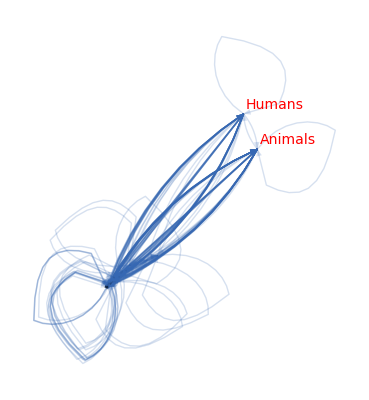

```mathematica
g[gen]=Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

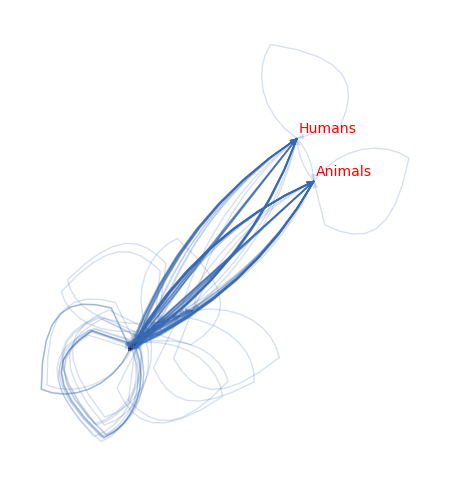

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1990

```mathematica
gen=1990
```

1990

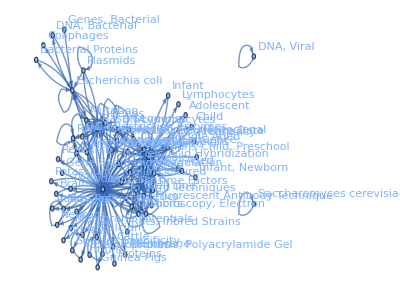

```mathematica
Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Rats,Mice,Adult,Middle Aged,Escherichia coli,In Vitro Techniques,Base Sequence,Kinetics,Microscopy, Electron,Aged,Rabbits,Cell Line,Mutation,Time Factors,Calcium,Adolescent,DNA,Molecular Weight,Liver,Child,Cells, Cultured,Cats,Muscles,Rats, Inbred Strains,Membrane Potentials,Cell Membrane,Genes,Potassium,Neurons,Sodium,Amino Acid Sequence,Brain,Molecular Sequence Data,Infant,Kidney,Guinea Pigs,Transcription, Genetic,Action Potentials,RNA, Messenger,DNA Restriction Enzymes,Cloning, Molecular,Cattle,DNA, Viral,Plasmids,Child, Preschool,T-Lymphocytes,Research,Lymphocytes,Genes, Bacterial,Saccharomyces cerevisiae,DNA, Bacterial,Infant, Newborn,Bacterial Proteins,Fluorescent Antibody Technique,Gene Expression Regulation,Proteins,Pregnancy,Coliphages,Dogs,Species Specificity,Antibodies, Monoclonal,Nucleic Acid Hybridization,Tritium,Peptides,Electrophoresis, Polyacrylamide Gel}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Animals->Humans,Male->Humans,Humans->Animals,Female->Humans,Humans->Male,Humans->Female,Male->Animals,Animals->Rats,Rats->Animals,Animals->Mice,Adult->Humans,Mice->Animals,Humans->Adult,Female->Animals,Animals->Male,Male->Male,Middle Aged->Humans,Escherichia coli->Escherichia coli,Humans->Middle Aged,Mice->Mice,Animals->Female,Rats->Rats,Female->Female,In Vitro Techniques->Animals,Female->Male,Male->Female,Base Sequence->Base Sequence,Animals->Kinetics,Microscopy, Electron->Animals,Animals->In Vitro Techniques,Humans->Mice,Animals->Microscopy, Electron,Aged->Humans,Animals->Rabbits,Animals->Cell Line,Kinetics->Animals,Male->Rats,Cell Line->Animals,Mice->Humans,Rats->Humans,Base Sequence->Animals,Male->Adult,Adult->Male,Mutation->Mutation,Humans->Aged,Animals->Base Sequence,Time Factors->Animals,Animals->Calcium,Adolescent->Humans,Mutation->Escherichia coli,Humans->Rats,Animals->DNA,Rabbits->Animals,Animals->Molecular Weight,Animals->Liver,Child->Humans,Female->Adult,Cells, Cultured->Animals,Calcium->Animals,Adult->Adult,Humans->Time Factors,Humans->Kinetics,DNA->Animals,Humans->Cell Line,Animals->Time Factors,Animals->Cats,Animals->Muscles,Adult->Female,Humans->Adolescent,Rats->Male,Microscopy, Electron->Microscopy, Electron,Rats, Inbred Strains->Animals,Time Factors->Humans,Membrane Potentials->Animals,Humans->Child,Kinetics->Humans,Male->Middle Aged,Humans->Base Sequence,Liver->Animals,Cats->Animals,Animals->Cell Membrane,Kinetics->Kinetics,Animals->Genes,Cell Line->Humans,Animals->Membrane Potentials,Middle Aged->Male,Muscles->Animals,Animals->Cells, Cultured,Animals->Potassium,Escherichia coli->Mutation,Animals->Neurons,Female->Middle Aged,Molecular Weight->Animals,Neurons->Animals,Animals->Sodium,Humans->DNA,Amino Acid Sequence->Animals,Animals->Amino Acid Sequence,Female->Rats,Animals->Brain,Base Sequence->Humans,Cell Membrane->Animals,Molecular Sequence Data->Base Sequence,Middle Aged->Adult,Genes->Animals,Cell Line->Cell Line,Female->Mice,Microscopy, Electron->Humans,Male->Mice,Base Sequence->Genes,Molecular Sequence Data->Animals,Adult->Middle Aged,Humans->Liver,Muscles->Muscles,Infant->Humans,In Vitro Techniques->Humans,Middle Aged->Female,Calcium->Calcium,Humans->Rabbits,Animals->Kidney,Animals->Guinea Pigs,Transcription, Genetic->Animals,Potassium->Animals,Base Sequence->Transcription, Genetic,Action Potentials->Animals,Sodium->Animals,Animals->Mutation,RNA, Messenger->Animals,Humans->Molecular Weight,Liver->Humans,Base Sequence->Escherichia coli,Middle Aged->Middle Aged,Cells, Cultured->Humans,Mutation->Animals,DNA->DNA,Base Sequence->DNA Restriction Enzymes,Cloning, Molecular->Animals,Cell Line->Mice,Animals->RNA, Messenger,Animals->Transcription, Genetic,Animals->Cattle,Amino Acid Sequence->Base Sequence,DNA->Humans,Liver->Liver,Humans->Genes,Transcription, Genetic->Base Sequence,Humans->Infant,Guinea Pigs->Animals,Humans->Amino Acid Sequence,Humans->Microscopy, Electron,Rabbits->Humans,DNA, Viral->DNA, Viral,Plasmids->Escherichia coli,Child, Preschool->Humans,Animals->T-Lymphocytes,Cloning, Molecular->Base Sequence,Adult->Animals,Animals->Research,Genes->Base Sequence,Base Sequence->DNA,Humans->Lymphocytes,Humans->In Vitro Techniques,Cats->Cats,Genes, Bacterial->Escherichia coli,Male->Time Factors,T-Lymphocytes->Animals,Saccharomyces cerevisiae->Saccharomyces cerevisiae,Transcription, Genetic->Transcription, Genetic,DNA, Bacterial->Escherichia coli,Rats->Liver,Base Sequence->Amino Acid Sequence,Infant, Newborn->Humans,Mice->Cell Line,Bacterial Proteins->Escherichia coli,Humans->Fluorescent Antibody Technique,Gene Expression Regulation->Animals,Rats, Inbred Strains->Rats,Mutation->Genes,Mutation->Base Sequence,Animals->Cloning, Molecular,Amino Acid Sequence->Amino Acid Sequence,Humans->T-Lymphocytes,Plasmids->Plasmids,Genes->Genes,Base Sequence->Cloning, Molecular,Rats->Mice,Animals->Proteins,Pregnancy->Humans,Escherichia coli->Coliphages,Plasmids->Base Sequence,Mice->Female,Base Sequence->Plasmids,Mice->Male,Animals->Dogs,Humans->Cells, Cultured,Animals->Action Potentials,Brain->Animals,Animals->Adult,Animals->DNA Restriction Enzymes,Animals->Species Specificity,Escherichia coli->Bacterial Proteins,Escherichia coli->DNA, Bacterial,Animals->Escherichia coli,Genes->Escherichia coli,Cattle->Animals,Base Sequence->Mutation,DNA Restriction Enzymes->Base Sequence,RNA, Messenger->RNA, Messenger,Base Sequence->RNA, Messenger,Antibodies, Monoclonal->Animals,Aged->Male,Genes->Mutation,Molecular Sequence Data->Humans,Nucleic Acid Hybridization->Animals,Animals->Tritium,Escherichia coli->Base Sequence,Escherichia coli->Genes,Animals->Peptides,Humans->Nucleic Acid Hybridization,Male->Aged,Mice->Rats,Kidney->Animals,Electrophoresis, Polyacrylamide Gel->Animals,Rats->Female,Antibodies, Monoclonal->Humans,Fluorescent Antibody Technique->Animals,In Vitro Techniques->In Vitro Techniques}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ2CitingCitedMeSHgraph[gen],EdgeWeight]
```

{345.223,293.132,120.257,110.103,108.901,101.546,82.8488,74.6605,73.8533,72.7086,72.377,69.9648,69.7143,65.8628,59.2482,57.0433,53.5774,52.6422,48.3537,47.9582,43.19,41.5814,41.3097,39.9083,39.0338,37.09,35.9868,34.6556,34.0221,33.7594,31.9063,31.646,31.2926,30.4197,30.1285,29.9725,29.6774,29.5078,29.5031,28.1731,27.8849,26.9788,26.3137,26.2156,25.0886,25.0855,24.7753,24.5413,24.1307,24.0905,24.0869,24.0771,23.9306,23.6747,23.491,23.4641,22.7766,22.687,22.6646,22.5713,22.3344,21.6944,21.6245,21.32,21.2521,21.1243,21.0251,20.5973,20.5638,20.2395,20.1063,19.889,19.7333,19.5742,19.4381,19.3068,19.2608,18.6558,18.4954,18.3191,18.3182,18.2474,18.0245,17.7905,17.5889,17.4938,17.477,17.3791,17.374,17.3669,17.3213,17.271,17.2395,17.2307,17.0713,16.9409,16.9079,16.7568,16.6133,16.5354,16.3236,16.3082,16.2491,16.0879,15.7947,15.556,15.5071,15.2789,15.2317,15.2155,15.1418,15.0555,14.9608,14.9147,14.8365,14.775,14.7346,14.6897,14.6706,14.5536,14.5314,14.5053,14.499,14.3379,14.2511,14.2086,14.117,13.858,13.8522,13.7088,13.6892,13.6372,13.5651,13.4618,13.4005,13.2978,13.2538,13.2428,13.2216,13.1767,13.1205,13.0898,13.0338,13.0253,13.0224,13.0084,12.9824,12.9741,12.952,12.8891,12.8527,12.8296,12.8195,12.6978,12.662,12.6516,12.6415,12.5709,12.5423,12.5325,12.48,12.4415,12.4009,12.3349,12.2869,12.2673,12.2578,12.1766,12.0361,12.0322,12.0197,12.0003,11.9525,11.9485,11.9468,11.8996,11.8872,11.8279,11.8086,11.7343,11.7302,11.6525,11.6084,11.5678,11.5639,11.4411,11.4232,11.3973,11.3218,11.3119,11.3109,11.3087,11.2769,11.2342,11.2268,11.1908,11.1843,11.1726,11.1674,11.1645,11.1588,11.1409,11.1125,11.0804,11.0578,10.9984,10.9568,10.9507,10.8603,10.8086,10.7198,10.6646,10.6218,10.57,10.5554,10.5546,10.5357,10.5275,10.5086,10.4969,10.4406,10.4212,10.3877,10.3801,10.2978,10.2694,10.2488,10.2242,10.219}

```mathematica
topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

345.223 | 108.901 | 82.8488 | 74.6605 | 23.9306 | 31.2926 | 59.2482 | 43.19 | 0 | 12.3349 | 18.3191 | 21.32 | 12.8296 | 24.7753 | 14.5314 | 21.1243 | 0 | 21.6245 | 0 | 20.1063 | 16.7568 | 13.6892 | 14.8365 | 19.2608 | 11.1843 | 0 | 0 | 0 | 0 | 0 | 12.9824 | 0 | 0 | 0 | 12.8527 | 0 | 0 | 12.952 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.5678 | 0 | 12.4009 | 0 | 0 | 0 | 0 | 0 | 11.8872 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.4406 | 0 | 0 | 0
120.257 | 293.132 | 53.5774 | 41.3097 | 72.7086 | 69.9648 | 11.1645 | 0 | 11.0578 | 31.646 | 24.5413 | 33.7594 | 30.4197 | 0 | 29.9725 | 29.6774 | 13.8522 | 21.0251 | 24.0905 | 0 | 23.6747 | 23.4641 | 22.7766 | 0 | 17.3669 | 20.5973 | 20.5638 | 0 | 17.477 | 18.0245 | 17.5889 | 17.3213 | 17.2395 | 16.9079 | 16.5354 | 16.3082 | 0 | 0 | 14.5053 | 14.499 | 13.0898 | 11.1726 | 13.1205 | 11.1588 | 11.6525 | 13.0338 | 0 | 0 | 0 | 12.6415 | 12.5325 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.3218 | 0 | 0 | 11.1908 | 11.1409 | 0 | 0 | 10.5357 | 10.4969 | 0
110.103 | 73.8533 | 52.6422 | 34.6556 | 29.5031 | 15.1418 | 26.2156 | 18.4954 | 0 | 0 | 0 | 0 | 0 | 10.4212 | 0 | 0 | 0 | 12.2578 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
101.546 | 57.0433 | 35.9868 | 39.0338 | 16.3236 | 15.2317 | 22.6646 | 17.2307 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
26.9788 | 72.377 | 19.889 | 10.2694 | 39.9083 | 11.3973 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.0003 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
27.8849 | 65.8628 | 11.2268 | 11.2769 | 10.3877 | 41.5814 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.9468 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
69.7143 | 12.5423 | 25.0886 | 20.2395 | 0 | 0 | 21.6944 | 14.9147 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
48.3537 | 0 | 17.3791 | 14.6706 | 0 | 0 | 15.556 | 13.4618 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 47.9582 | 0 | 10.5275 | 0 | 0 | 0 | 0 | 0 | 17.271 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.5086 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.0804 | 0 | 11.1125 | 0 | 0 | 0 | 0 | 11.3109 | 0 | 0 | 0 | 0 | 0 | 0 | 0
14.6897 | 37.09 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.219 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16.2491 | 26.3137 | 0 | 0 | 0 | 0 | 0 | 0 | 13.5651 | 0 | 34.0221 | 0 | 0 | 0 | 0 | 0 | 10.9507 | 0 | 0 | 0 | 12.4415 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.0555 | 0 | 0 | 0 | 11.9525 | 0 | 0 | 0 | 0 | 0 | 14.2086 | 0 | 10.7198 | 13.2428 | 11.4232 | 0 | 0 | 11.2342 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
18.6558 | 29.5078 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17.7905 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15.2155 | 31.9063 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.7333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
30.1285 | 0 | 10.6218 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.8195 | 23.491 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17.4938 | 28.1731 | 0 | 0 | 0 | 13.1767 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.2789 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 13.2978 | 0 | 0 | 0 | 0 | 0 | 0 | 24.0771 | 0 | 11.7302 | 0 | 0 | 0 | 0 | 0 | 25.0855 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.7343 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
19.4381 | 24.1307 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 22.3344 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.5536 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
24.0869 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13.0224 | 21.2521 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.2538 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 17.0713 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13.6372 | 18.3182 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.0084 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
22.687 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13.4005 | 22.5713 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 18.2474 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.2869 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 17.374 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.775 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 19.5742 | 0 | 0 | 11.8086 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 19.3068 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16.0879 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 15.5071 | 0 | 0 | 0 | 0 | 0 | 0 | 10.9984 | 0 | 12.48 | 0 | 0 | 0 | 0 | 0 | 10.57 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.4411 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 14.2511 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16.9409 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 13.858 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16.6133 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.0253 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.6084 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 11.1674 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10.5554 | 14.9608 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.7947 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
14.7346 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 10.3801 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12.8891 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 14.3379 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.9741 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.0322 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 14.117 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 13.7088 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.8086 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.8603 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 13.2216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.5709 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 10.9568 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.6978 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.662 | 0 | 11.3087 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.5639 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.6516 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12.1766 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.2673 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.0361 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.0197 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.9485 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.8996 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 10.2242 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 11.8279 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.3119 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10.2488 | 10.6646 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 10.5546 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 10.2978 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{1097.07,1360.09,383.289,305.06,192.82,180.167,164.194,109.421,119.769,61.9987,201.379,65.9541,66.8551,40.7503,36.3105,74.1225,85.9248,43.5688,36.888,24.0869,47.5282,17.0713,44.9637,22.687,35.9718,30.5343,32.1489,31.3829,19.3068,16.0879,60.9966,14.2511,16.9409,13.858,41.247,11.1674,41.3109,14.7346,10.3801,12.8891,39.3442,14.117,24.5174,10.8603,25.7925,10.9568,12.6978,35.5345,12.6516,12.1766,0,0,12.2673,12.0361,12.0197,11.9485,11.8996,10.2242,11.8279,0,11.3119,0,0,0,20.9134,10.5546,0,0,10.2978}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Animals

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{1153.04,1348.42,309.261,246.116,204.571,197.786,156.543,107.293,156.505,54.2,188.154,72.8699,62.9826,35.1965,44.5039,78.0274,77.7293,54.9074,38.6441,20.1063,66.1267,37.1533,62.6217,19.2608,28.5512,32.8842,35.3388,0,17.477,18.0245,79.3108,17.3213,17.2395,16.9079,52.949,16.3082,0,12.952,14.5053,14.499,39.3306,11.1726,34.6489,24.4016,23.0757,13.0338,12.6978,22.7981,0,24.2094,12.5325,12.4009,0,12.0361,11.0804,0,11.1125,11.8872,0,11.3218,0,11.3109,11.1908,11.1409,0,10.4406,10.5357,10.4969,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Animals

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{2250.11,2708.51,692.55,551.176,397.391,377.954,320.737,216.714,276.274,116.199,389.533,138.824,129.838,75.9468,80.8144,152.15,163.654,98.4762,75.5321,44.1932,113.655,54.2246,107.585,41.9478,64.523,63.4185,67.4877,31.3829,36.7838,34.1123,140.307,31.5725,34.1804,30.7659,94.196,27.4756,41.3109,27.6866,24.8854,27.388,78.6748,25.2896,59.1663,35.2619,48.8682,23.9906,25.3957,58.3326,12.6516,36.386,12.5325,12.4009,12.2673,24.0722,23.1001,11.9485,23.0121,22.1114,11.8279,11.3218,11.3119,11.3109,11.1908,11.1409,20.9134,20.9952,10.5357,10.4969,10.2978}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{1097.07,1153.04},{1360.09,1348.42},{383.289,309.261},{305.06,246.116},{192.82,204.571},{180.167,197.786},{164.194,156.543},{109.421,107.293},{119.769,156.505},{61.9987,54.2},{201.379,188.154},{65.9541,72.8699},{66.8551,62.9826},{40.7503,35.1965},{36.3105,44.5039},{74.1225,78.0274},{85.9248,77.7293},{43.5688,54.9074},{36.888,38.6441},{24.0869,20.1063},{47.5282,66.1267},{17.0713,37.1533},{44.9637,62.6217},{22.687,19.2608},{35.9718,28.5512},{30.5343,32.8842},{32.1489,35.3388},{31.3829,0},{19.3068,17.477},{16.0879,18.0245},{60.9966,79.3108},{14.2511,17.3213},{16.9409,17.2395},{13.858,16.9079},{41.247,52.949},{11.1674,16.3082},{41.3109,0},{14.7346,12.952},{10.3801,14.5053},{12.8891,14.499},{39.3442,39.3306},{14.117,11.1726},{24.5174,34.6489},{10.8603,24.4016},{25.7925,23.0757},{10.9568,13.0338},{12.6978,12.6978},{35.5345,22.7981},{12.6516,0},{12.1766,24.2094},{0,12.5325},{0,12.4009},{12.2673,0},{12.0361,12.0361},{12.0197,11.0804},{11.9485,0},{11.8996,11.1125},{10.2242,11.8872},{11.8279,0},{0,11.3218},{11.3119,0},{0,11.3109},{0,11.1908},{0,11.1409},{20.9134,0},{10.5546,10.4406},{0,10.5357},{0,10.4969},{10.2978,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

191.522

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.431529],Animals->Animals→Thickness[0.366415],Animals->Humans→Thickness[0.150321],Male->Humans→Thickness[0.137629],Humans->Animals→Thickness[0.136127],Female->Humans→Thickness[0.126932],Humans->Male→Thickness[0.103561],Humans->Female→Thickness[0.0933256],Male->Animals→Thickness[0.0923166],Animals->Rats→Thickness[0.0908857],Rats->Animals→Thickness[0.0904713],Animals->Mice→Thickness[0.087456],Adult->Humans→Thickness[0.0871429],Mice->Animals→Thickness[0.0823285],Humans->Adult→Thickness[0.0740603],Female->Animals→Thickness[0.0713042],Animals->Male→Thickness[0.0669717],Male->Male→Thickness[0.0658028],Middle Aged->Humans→Thickness[0.0604421],Escherichia coli->Escherichia coli→Thickness[0.0599478],Humans->Middle Aged→Thickness[0.0539875],Mice->Mice→Thickness[0.0519767],Animals->Female→Thickness[0.0516371],Rats->Rats→Thickness[0.0498854],Female->Female→Thickness[0.0487923],In Vitro Techniques->Animals→Thickness[0.0463625],Female->Male→Thickness[0.0449835],Male->Female→Thickness[0.0433196],Base Sequence->Base Sequence→Thickness[0.0425276],Animals->Kinetics→Thickness[0.0421993],Microscopy, Electron->Animals→Thickness[0.0398829],Animals->In Vitro Techniques→Thickness[0.0395575],Humans->Mice→Thickness[0.0391157],Animals->Microscopy, Electron→Thickness[0.0380247],Aged->Humans→Thickness[0.0376606],Animals->Rabbits→Thickness[0.0374656],Animals->Cell Line→Thickness[0.0370967],Kinetics->Animals→Thickness[0.0368847],Male->Rats→Thickness[0.0368789],Cell Line->Animals→Thickness[0.0352164],Mice->Humans→Thickness[0.0348561],Rats->Humans→Thickness[0.0337235],Base Sequence->Animals→Thickness[0.0328921],Male->Adult→Thickness[0.0327695],Adult->Male→Thickness[0.0313608],Mutation->Mutation→Thickness[0.0313568],Humans->Aged→Thickness[0.0309691],Animals->Base Sequence→Thickness[0.0306766],Time Factors->Animals→Thickness[0.0301634],Animals->Calcium→Thickness[0.0301131],Adolescent->Humans→Thickness[0.0301086],Mutation->Escherichia coli→Thickness[0.0300963],Humans->Rats→Thickness[0.0299133],Animals->DNA→Thickness[0.0295933],Rabbits->Animals→Thickness[0.0293638],Animals->Molecular Weight→Thickness[0.0293301],Animals->Liver→Thickness[0.0284707],Child->Humans→Thickness[0.0283588],Female->Adult→Thickness[0.0283307],Cells, Cultured->Animals→Thickness[0.0282141],Calcium->Animals→Thickness[0.027918],Adult->Adult→Thickness[0.0271179],Humans->Time Factors→Thickness[0.0270306],Humans->Kinetics→Thickness[0.02665],DNA->Animals→Thickness[0.0265651],Humans->Cell Line→Thickness[0.0264054],Animals->Time Factors→Thickness[0.0262814],Animals->Cats→Thickness[0.0257466],Animals->Muscles→Thickness[0.0257048],Adult->Female→Thickness[0.0252994],Humans->Adolescent→Thickness[0.0251329],Rats->Male→Thickness[0.0248613],Microscopy, Electron->Microscopy, Electron→Thickness[0.0246667],Rats, Inbred Strains->Animals→Thickness[0.0244678],Time Factors->Humans→Thickness[0.0242976],Membrane Potentials->Animals→Thickness[0.0241335],Humans->Child→Thickness[0.024076],Kinetics->Humans→Thickness[0.0233198],Male->Middle Aged→Thickness[0.0231192],Humans->Base Sequence→Thickness[0.0228988],Liver->Animals→Thickness[0.0228977],Cats->Animals→Thickness[0.0228093],Animals->Cell Membrane→Thickness[0.0225306],Kinetics->Kinetics→Thickness[0.0222382],Animals->Genes→Thickness[0.0219861],Cell Line->Humans→Thickness[0.0218673],Animals->Membrane Potentials→Thickness[0.0218463],Middle Aged->Male→Thickness[0.0217239],Muscles->Animals→Thickness[0.0217175],Animals->Cells, Cultured→Thickness[0.0217087],Animals->Potassium→Thickness[0.0216517],Escherichia coli->Mutation→Thickness[0.0215888],Animals->Neurons→Thickness[0.0215493],Female->Middle Aged→Thickness[0.0215384],Molecular Weight->Animals→Thickness[0.0213392],Neurons->Animals→Thickness[0.0211762],Animals->Sodium→Thickness[0.0211348],Humans->DNA→Thickness[0.0209459],Amino Acid Sequence->Animals→Thickness[0.0207667],Animals->Amino Acid Sequence→Thickness[0.0206692],Female->Rats→Thickness[0.0204045],Animals->Brain→Thickness[0.0203852],Base Sequence->Humans→Thickness[0.0203113],Cell Membrane->Animals→Thickness[0.0201098],Molecular Sequence Data->Base Sequence→Thickness[0.0197434],Middle Aged->Adult→Thickness[0.0194449],Genes->Animals→Thickness[0.0193839],Cell Line->Cell Line→Thickness[0.0190986],Female->Mice→Thickness[0.0190397],Microscopy, Electron->Humans→Thickness[0.0190194],Male->Mice→Thickness[0.0189272],Base Sequence->Genes→Thickness[0.0188194],Molecular Sequence Data->Animals→Thickness[0.018701],Adult->Middle Aged→Thickness[0.0186433],Humans->Liver→Thickness[0.0185456],Muscles->Muscles→Thickness[0.0184687],Infant->Humans→Thickness[0.0184182],In Vitro Techniques->Humans→Thickness[0.0183621],Middle Aged->Female→Thickness[0.0183382],Calcium->Calcium→Thickness[0.0181921],Humans->Rabbits→Thickness[0.0181643],Animals->Kidney→Thickness[0.0181317],Animals->Guinea Pigs→Thickness[0.0181237],Transcription, Genetic->Animals→Thickness[0.0179224],Potassium->Animals→Thickness[0.0178139],Base Sequence->Transcription, Genetic→Thickness[0.0177608],Action Potentials->Animals→Thickness[0.0176463],Sodium->Animals→Thickness[0.0173225],Animals->Mutation→Thickness[0.0173152],RNA, Messenger->Animals→Thickness[0.017136],Humans->Molecular Weight→Thickness[0.0171115],Liver->Humans→Thickness[0.0170464],Base Sequence->Escherichia coli→Thickness[0.0169563],Middle Aged->Middle Aged→Thickness[0.0168273],Cells, Cultured->Humans→Thickness[0.0167506],Mutation->Animals→Thickness[0.0166223],DNA->DNA→Thickness[0.0165672],Base Sequence->DNA Restriction Enzymes→Thickness[0.0165535],Cloning, Molecular->Animals→Thickness[0.0165269],Cell Line->Mice→Thickness[0.0164709],Animals->RNA, Messenger→Thickness[0.0164006],Animals->Transcription, Genetic→Thickness[0.0163623],Animals->Cattle→Thickness[0.0162923],Amino Acid Sequence->Base Sequence→Thickness[0.0162816],DNA->Humans→Thickness[0.016278],Liver->Liver→Thickness[0.0162605],Humans->Genes→Thickness[0.016228],Transcription, Genetic->Base Sequence→Thickness[0.0162177],Humans->Infant→Thickness[0.01619],Guinea Pigs->Animals→Thickness[0.0161113],Humans->Amino Acid Sequence→Thickness[0.0160659],Humans->Microscopy, Electron→Thickness[0.0160369],Rabbits->Humans→Thickness[0.0160243],DNA, Viral->DNA, Viral→Thickness[0.0158723],Plasmids->Escherichia coli→Thickness[0.0158275],Child, Preschool->Humans→Thickness[0.0158145],Animals->T-Lymphocytes→Thickness[0.0158019],Cloning, Molecular->Base Sequence→Thickness[0.0157137],Adult->Animals→Thickness[0.0156778],Animals->Research→Thickness[0.0156657],Genes->Base Sequence→Thickness[0.0156],Base Sequence->DNA→Thickness[0.0155518],Humans->Lymphocytes→Thickness[0.0155011],Humans->In Vitro Techniques→Thickness[0.0154187],Cats->Cats→Thickness[0.0153586],Genes, Bacterial->Escherichia coli→Thickness[0.0153342],Male->Time Factors→Thickness[0.0153223],T-Lymphocytes->Animals→Thickness[0.0152208],Saccharomyces cerevisiae->Saccharomyces cerevisiae→Thickness[0.0150451],Transcription, Genetic->Transcription, Genetic→Thickness[0.0150402],DNA, Bacterial->Escherichia coli→Thickness[0.0150247],Rats->Liver→Thickness[0.0150003],Base Sequence->Amino Acid Sequence→Thickness[0.0149407],Infant, Newborn->Humans→Thickness[0.0149357],Mice->Cell Line→Thickness[0.0149335],Bacterial Proteins->Escherichia coli→Thickness[0.0148745],Humans->Fluorescent Antibody Technique→Thickness[0.014859],Gene Expression Regulation->Animals→Thickness[0.0147849],Rats, Inbred Strains->Rats→Thickness[0.0147608],Mutation->Genes→Thickness[0.0146678],Mutation->Base Sequence→Thickness[0.0146627],Animals->Cloning, Molecular→Thickness[0.0145657],Amino Acid Sequence->Amino Acid Sequence→Thickness[0.0145105],Humans->T-Lymphocytes→Thickness[0.0144598],Plasmids->Plasmids→Thickness[0.0144548],Genes->Genes→Thickness[0.0143013],Base Sequence->Cloning, Molecular→Thickness[0.0142789],Rats->Mice→Thickness[0.0142467],Animals->Proteins→Thickness[0.0141522],Pregnancy->Humans→Thickness[0.0141399],Escherichia coli->Coliphages→Thickness[0.0141387],Plasmids->Base Sequence→Thickness[0.0141359],Mice->Female→Thickness[0.0140962],Base Sequence->Plasmids→Thickness[0.0140428],Mice->Male→Thickness[0.0140335],Animals->Dogs→Thickness[0.0139885],Humans->Cells, Cultured→Thickness[0.0139804],Animals->Action Potentials→Thickness[0.0139657],Brain->Animals→Thickness[0.0139593],Animals->Adult→Thickness[0.0139557],Animals->DNA Restriction Enzymes→Thickness[0.0139485],Animals->Species Specificity→Thickness[0.0139262],Escherichia coli->Bacterial Proteins→Thickness[0.0138906],Escherichia coli->DNA, Bacterial→Thickness[0.0138505],Animals->Escherichia coli→Thickness[0.0138223],Genes->Escherichia coli→Thickness[0.013748],Cattle->Animals→Thickness[0.013696],Base Sequence->Mutation→Thickness[0.0136883],DNA Restriction Enzymes->Base Sequence→Thickness[0.0135754],RNA, Messenger->RNA, Messenger→Thickness[0.0135107],Base Sequence->RNA, Messenger→Thickness[0.0133998],Antibodies, Monoclonal->Animals→Thickness[0.0133307],Aged->Male→Thickness[0.0132773],Genes->Mutation→Thickness[0.0132125],Molecular Sequence Data->Humans→Thickness[0.0131942],Nucleic Acid Hybridization->Animals→Thickness[0.0131933],Animals->Tritium→Thickness[0.0131696],Escherichia coli->Base Sequence→Thickness[0.0131594],Escherichia coli->Genes→Thickness[0.0131357],Animals->Peptides→Thickness[0.0131211],Humans->Nucleic Acid Hybridization→Thickness[0.0130507],Male->Aged→Thickness[0.0130265],Mice->Rats→Thickness[0.0129846],Kidney->Animals→Thickness[0.0129751],Electrophoresis, Polyacrylamide Gel->Animals→Thickness[0.0128723],Rats->Female→Thickness[0.0128368],Antibodies, Monoclonal->Humans→Thickness[0.012811],Fluorescent Antibody Technique->Animals→Thickness[0.0127802],In Vitro Techniques->In Vitro Techniques→Thickness[0.0127738]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Animals→Animals,Animals→Animals}

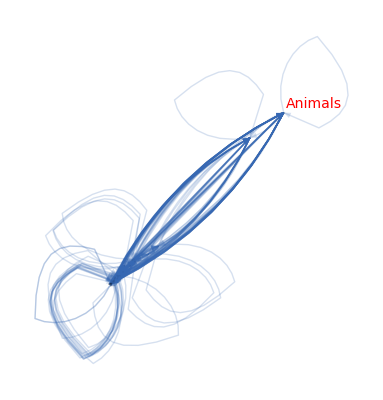

```mathematica
g[gen]=Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

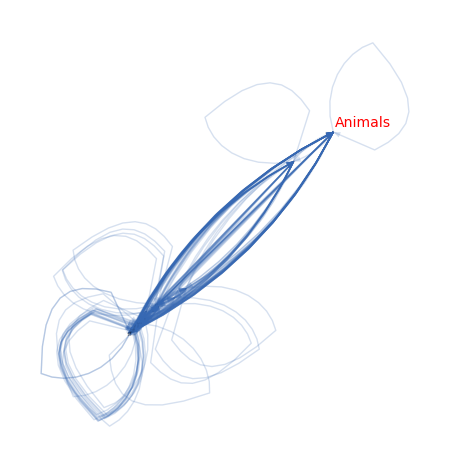

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1995

```mathematica
gen=1995
```

1995

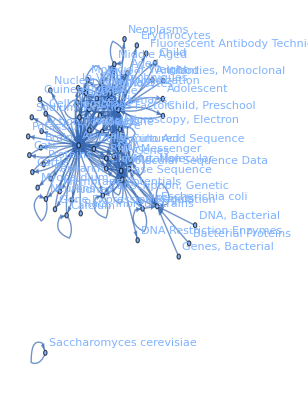

```mathematica
Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Adult,Rats,Mice,Middle Aged,Base Sequence,Escherichia coli,Molecular Sequence Data,Aged,Kinetics,In Vitro Techniques,Amino Acid Sequence,Microscopy, Electron,Cell Line,Cells, Cultured,Adolescent,Calcium,Time Factors,Mutation,Neurons,Child,Muscles,Rabbits,DNA,Molecular Weight,Liver,Cats,Genes,Cell Membrane,Brain,Cloning, Molecular,Rats, Inbred Strains,RNA, Messenger,Transcription, Genetic,Membrane Potentials,Saccharomyces cerevisiae,Plasmids,T-Lymphocytes,Sodium,Cattle,Bacterial Proteins,Infant,Neoplasms,Child, Preschool,Gene Expression Regulation,DNA, Bacterial,Genes, Bacterial,Antibodies, Monoclonal,Kidney,Erythrocytes,Action Potentials,Proteins,Potassium,Fluorescent Antibody Technique,Research,Guinea Pigs,DNA Restriction Enzymes,Myocardium,Nucleic Acid Hybridization}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Animals->Humans,Humans->Animals,Male->Humans,Female->Humans,Humans->Male,Humans->Female,Adult->Humans,Male->Animals,Rats->Animals,Animals->Rats,Humans->Adult,Mice->Animals,Animals->Mice,Animals->Male,Male->Male,Female->Animals,Middle Aged->Humans,Base Sequence->Base Sequence,Humans->Middle Aged,Escherichia coli->Escherichia coli,Female->Female,Molecular Sequence Data->Animals,Animals->Female,Molecular Sequence Data->Base Sequence,Base Sequence->Animals,Female->Male,Male->Female,Mice->Mice,Rats->Rats,Aged->Humans,Molecular Sequence Data->Molecular Sequence Data,Animals->Base Sequence,Animals->Kinetics,In Vitro Techniques->Animals,Molecular Sequence Data->Humans,Rats->Humans,Mice->Humans,Humans->Mice,Humans->Aged,Base Sequence->Humans,Base Sequence->Molecular Sequence Data,Molecular Sequence Data->Amino Acid Sequence,Animals->Microscopy, Electron,Humans->Base Sequence,Animals->Cell Line,Microscopy, Electron->Animals,Animals->In Vitro Techniques,Animals->Amino Acid Sequence,Amino Acid Sequence->Animals,Kinetics->Animals,Male->Adult,Male->Rats,Adult->Male,Cell Line->Animals,Cells, Cultured->Animals,Amino Acid Sequence->Amino Acid Sequence,Base Sequence->Amino Acid Sequence,Adolescent->Humans,Humans->Rats,Animals->Calcium,Humans->Kinetics,Female->Adult,Humans->Time Factors,Mutation->Mutation,Humans->Amino Acid Sequence,Animals->Neurons,Humans->Cell Line,Animals->Molecular Sequence Data,Humans->Molecular Sequence Data,Child->Humans,Adult->Adult,Adult->Female,Animals->Muscles,Animals->Rabbits,Animals->DNA,Animals->Molecular Weight,Animals->Liver,Animals->Time Factors,Calcium->Animals,Rats->Male,Time Factors->Animals,Animals->Cells, Cultured,DNA->Animals,Amino Acid Sequence->Base Sequence,Animals->Cats,Humans->Adolescent,Time Factors->Humans,Humans->Child,Rabbits->Animals,Male->Middle Aged,Amino Acid Sequence->Humans,In Vitro Techniques->Humans,Female->Middle Aged,Middle Aged->Male,Microscopy, Electron->Microscopy, Electron,Base Sequence->Genes,Escherichia coli->Mutation,Kinetics->Humans,Animals->Genes,Cell Line->Humans,Animals->Cell Membrane,Animals->Brain,Base Sequence->Cloning, Molecular,Mutation->Escherichia coli,Neurons->Animals,Amino Acid Sequence->Molecular Sequence Data,Base Sequence->Mutation,Middle Aged->Female,Rats, Inbred Strains->Animals,Humans->DNA,Base Sequence->Escherichia coli,RNA, Messenger->Animals,Animals->Mutation,Molecular Sequence Data->Cloning, Molecular,Humans->Molecular Weight,DNA->Humans,Base Sequence->DNA,Liver->Animals,Muscles->Muscles,Microscopy, Electron->Humans,Cells, Cultured->Humans,Calcium->Calcium,Muscles->Animals,Base Sequence->Transcription, Genetic,Animals->Cloning, Molecular,Humans->Cells, Cultured,Animals->RNA, Messenger,Cloning, Molecular->Base Sequence,Cloning, Molecular->Animals,Membrane Potentials->Animals,Transcription, Genetic->Animals,Middle Aged->Adult,Female->Mice,Adult->Middle Aged,Saccharomyces cerevisiae->Saccharomyces cerevisiae,Cats->Animals,Base Sequence->Plasmids,Transcription, Genetic->Base Sequence,Cell Membrane->Animals,Molecular Sequence Data->Mutation,Humans->T-Lymphocytes,Animals->Sodium,Middle Aged->Middle Aged,Kinetics->Kinetics,Male->Mice,Molecular Sequence Data->DNA,Humans->Microscopy, Electron,DNA->Base Sequence,Adult->Animals,Animals->T-Lymphocytes,DNA->DNA,Female->Rats,Animals->Cattle,Molecular Sequence Data->Genes,Animals->Membrane Potentials,Plasmids->Escherichia coli,Molecular Sequence Data->Transcription, Genetic,Liver->Humans,Animals->Transcription, Genetic,Bacterial Proteins->Escherichia coli,Molecular Weight->Animals,Base Sequence->RNA, Messenger,Cell Line->Cell Line,Mutation->Animals,T-Lymphocytes->Animals,Infant->Humans,Humans->Neoplasms,Molecular Sequence Data->Escherichia coli,Humans->Mutation,Male->Time Factors,Aged->Male,Child, Preschool->Humans,Neurons->Neurons,Rabbits->Humans,Humans->Genes,RNA, Messenger->Base Sequence,Animals->Gene Expression Regulation,Humans->Cloning, Molecular,Aged->Female,DNA, Bacterial->Escherichia coli,Molecular Sequence Data->Plasmids,Genes, Bacterial->Escherichia coli,Male->Aged,Humans->Liver,Liver->Liver,Escherichia coli->Base Sequence,Antibodies, Monoclonal->Humans,Animals->Kidney,Mice->Cell Line,Rats->Liver,Humans->RNA, Messenger,Mutation->Base Sequence,Genes->Animals,Female->Aged,Humans->Erythrocytes,Humans->Child, Preschool,Base Sequence->Mice,Muscles->Humans,Animals->Action Potentials,Plasmids->Plasmids,Animals->Proteins,Plasmids->Base Sequence,Animals->Potassium,Humans->In Vitro Techniques,Humans->Fluorescent Antibody Technique,Animals->Research,Animals->Guinea Pigs,Mutation->Genes,Transcription, Genetic->Transcription, Genetic,Gene Expression Regulation->Animals,Base Sequence->DNA Restriction Enzymes,Humans->Rabbits,Animals->Myocardium,Cattle->Animals,Molecular Sequence Data->Mice,Molecular Sequence Data->RNA, Messenger,Mice->Female,Animals->Nucleic Acid Hybridization,Guinea Pigs->Animals,Mice->Male,Escherichia coli->Genes,Animals->Adult}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ2CitingCitedMeSHgraph[gen],EdgeWeight]
```

{528.909,391.304,202.341,163.491,162.656,148.296,127.478,116.931,102.753,101.32,95.7744,93.5606,89.6975,87.6086,85.0044,79.8756,78.337,76.6881,74.4386,70.1752,64.6733,61.54,57.7834,57.4258,57.3862,57.2584,56.9376,53.9617,52.6747,51.7015,49.9568,49.8411,48.6542,47.5987,46.3934,45.9716,45.1916,45.001,44.9152,41.8817,41.5738,41.2899,40.8611,40.127,39.4761,39.1696,39.1683,38.8498,38.7495,38.017,37.4462,37.3864,36.7572,36.5026,35.76,35.5488,35.4382,34.762,34.0123,33.9913,33.8323,33.729,33.5867,33.2731,33.0055,32.9415,32.4247,31.8578,31.771,31.3195,31.3169,31.19,31.0682,30.9431,30.9056,30.339,29.8223,29.5932,29.4809,29.3438,29.1462,29.1071,29.0429,28.6927,28.613,28.5953,28.4894,27.9524,27.762,26.8491,26.8238,26.6666,26.6185,26.5445,26.0611,25.8427,25.7717,25.6045,25.5155,25.4463,25.2975,25.2191,25.0816,24.9566,24.9527,24.9077,24.8252,24.8051,24.6576,24.4232,24.4036,24.1561,24.0484,23.9639,23.9388,23.6,23.4034,23.282,23.1594,22.8682,22.7892,22.7443,22.6061,22.6028,22.4829,22.2993,22.226,22.1709,21.9965,21.8529,21.6421,21.2805,21.233,21.1464,21.0682,21.0166,21.0003,20.9162,20.7374,20.5073,20.4728,20.2276,20.0114,19.7034,19.5353,19.2504,19.2344,19.149,18.9678,18.8941,18.8688,18.8156,18.7244,18.7186,18.5638,18.4603,18.4501,18.4445,18.4328,18.2912,18.229,18.1531,18.1408,18.0702,17.9171,17.8974,17.8765,17.6858,17.5224,17.4974,17.396,17.3955,17.2147,17.1883,17.1471,17.0678,17.0442,16.8686,16.8668,16.7658,16.6981,16.6388,16.6383,16.6336,16.5754,16.5445,16.4799,16.4106,16.3841,16.374,16.251,16.1902,16.1863,16.1356,16.1307,16.0123,16.0052,16.0046,15.8868,15.8854,15.8313,15.7838,15.7683,15.7606,15.7549,15.7333,15.704,15.6347,15.6298,15.4497,15.392,15.3476,15.2052,15.1681,15.1598,15.1509,15.1338,15.1329,15.1124,15.0258,14.9987,14.9937,14.8969,14.8879}

```mathematica
topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

528.909 | 163.491 | 127.478 | 116.931 | 89.6975 | 33.8323 | 41.8817 | 64.6733 | 39.1696 | 0 | 31.3169 | 41.5738 | 33.5867 | 15.7333 | 32.4247 | 18.9678 | 31.771 | 22.1709 | 27.9524 | 0 | 33.0055 | 17.396 | 0 | 26.8491 | 0 | 15.1681 | 24.1561 | 23.4034 | 16.5445 | 0 | 17.0442 | 0 | 0 | 16.7658 | 0 | 16.1863 | 0 | 0 | 0 | 0 | 20.0114 | 0 | 0 | 0 | 0 | 17.5224 | 16.0046 | 0 | 0 | 0 | 0 | 0 | 16.0052 | 0 | 0 | 0 | 15.704 | 0 | 0 | 0 | 0 | 0
202.341 | 391.304 | 79.8756 | 57.3862 | 14.8879 | 93.5606 | 85.0044 | 0 | 47.5987 | 0 | 31.3195 | 0 | 46.3934 | 38.7495 | 38.017 | 39.4761 | 39.1683 | 28.6927 | 0 | 33.729 | 29.3438 | 23.9388 | 31.8578 | 0 | 30.9056 | 30.339 | 29.8223 | 29.5932 | 29.4809 | 28.4894 | 25.2975 | 25.0816 | 24.9566 | 22.226 | 0 | 21.9965 | 18.229 | 18.4501 | 0 | 0 | 18.8156 | 19.7034 | 18.5638 | 0 | 0 | 0 | 0 | 16.8668 | 0 | 0 | 0 | 16.374 | 0 | 15.8313 | 15.7683 | 15.7549 | 0 | 15.6347 | 15.6298 | 0 | 15.1598 | 15.0258
162.656 | 101.32 | 78.337 | 52.6747 | 36.7572 | 36.5026 | 19.2344 | 26.6666 | 0 | 0 | 0 | 16.5754 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17.3955 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
148.296 | 76.6881 | 53.9617 | 57.7834 | 33.2731 | 18.7186 | 21.0682 | 26.0611 | 0 | 0 | 0 | 16.0123 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
102.753 | 18.8688 | 35.76 | 30.9431 | 31.0682 | 0 | 0 | 21.0166 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
45.001 | 95.7744 | 29.1071 | 0 | 0 | 49.9568 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16.1902 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
44.9152 | 87.6086 | 14.9937 | 15.1124 | 0 | 0 | 51.7015 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16.251 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
74.4386 | 0 | 25.8427 | 24.4232 | 21.1464 | 0 | 0 | 19.5353 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
41.2899 | 56.9376 | 0 | 0 | 0 | 0 | 15.8868 | 0 | 70.1752 | 24.0484 | 40.8611 | 0 | 0 | 0 | 34.0123 | 0 | 0 | 0 | 0 | 0 | 0 | 24.6576 | 0 | 0 | 0 | 0 | 23.1594 | 0 | 0 | 0 | 25.6045 | 0 | 0 | 24.9527 | 0 | 18.0702 | 22.2993 | 0 | 0 | 20.7374 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.2052 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16.4106 | 61.54 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 25.5155 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.8969 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
45.1916 | 57.4258 | 0 | 0 | 0 | 0 | 15.1338 | 0 | 57.2584 | 17.4974 | 48.6542 | 0 | 0 | 0 | 40.127 | 0 | 0 | 0 | 0 | 0 | 0 | 20.2276 | 0 | 0 | 0 | 0 | 19.149 | 0 | 0 | 0 | 18.4603 | 0 | 0 | 23.6 | 0 | 15.1329 | 18.4328 | 0 | 0 | 16.6383 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
49.8411 | 0 | 17.2147 | 16.6981 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
25.4463 | 37.3864 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.2504 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
26.5445 | 45.9716 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
26.6185 | 37.4462 | 0 | 0 | 0 | 0 | 0 | 0 | 28.5953 | 0 | 24.8051 | 0 | 0 | 0 | 34.762 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
22.7443 | 38.8498 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 25.7717 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
25.2191 | 35.5488 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17.9171 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
22.6061 | 35.4382 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
33.9913 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 29.1462 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22.6028 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
27.762 | 29.0429 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 17.8974 | 0 | 0 | 0 | 0 | 0 | 0 | 16.1356 | 24.9077 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32.9415 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.4497 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 24.8252 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17.1471 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
31.19 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15.8854 | 22.4829 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22.7892 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17.0678 | 26.8238 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23.282 | 28.613 | 0 | 0 | 0 | 0 | 0 | 0 | 18.8941 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18.7244 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 18.1408 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
18.2912 | 22.8682 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16.4799 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 20.9162 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16.1307 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 20.4728 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 21.6421 | 0 | 0 | 0 | 0 | 0 | 0 | 21.8529 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 24.4036 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 23.9639 | 0 | 0 | 0 | 0 | 0 | 0 | 16.8686 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 21.233 | 0 | 0 | 0 | 0 | 0 | 0 | 20.5073 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.392 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 21.2805 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21.0003 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.7606 | 18.4445 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.7838 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 17.8765 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 15.1509 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18.1531 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17.6858 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17.1883 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 15.3476 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16.6388 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16.6336 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16.3841 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 14.9987 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{1753.33,1886.64,548.12,451.863,240.41,236.03,230.582,165.386,457.898,118.363,412.929,83.7539,82.0831,72.5161,152.227,87.3658,78.685,58.0443,33.9913,51.7491,56.8049,107.332,41.9723,31.19,61.1576,43.8916,89.5135,18.1408,57.6392,20.9162,16.1307,20.4728,0,43.495,24.4036,40.8325,57.1323,21.2805,21.0003,49.9889,17.8765,0,15.1509,18.1531,17.6858,0,17.1883,15.3476,16.6388,16.6336,16.3841,0,0,0,0,0,0,0,14.9987,0,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Animals

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{1813.54,1733.32,462.571,371.952,226.83,232.571,249.911,157.953,369.227,197.863,176.957,74.1616,99.2305,54.4828,179.343,84.2155,105.107,50.8635,27.9524,56.3318,79.7448,144.677,49.0049,26.8491,53.6948,45.5071,115.011,52.9965,78.6955,28.4894,116.753,25.0816,24.9566,87.5445,0,71.3858,74.3532,18.4501,21.0003,53.1595,38.827,19.7034,18.5638,0,0,17.5224,16.0046,16.8668,0,0,0,16.374,16.0052,15.8313,15.7683,15.7549,15.704,15.6347,15.6298,15.2052,15.1598,15.0258}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{3566.87,3619.96,1010.69,823.815,467.24,468.601,480.493,323.339,827.124,316.227,589.886,157.916,181.314,126.999,331.57,171.581,183.792,108.908,61.9437,108.081,136.55,252.009,90.9773,58.0391,114.852,89.3987,204.525,71.1374,136.335,49.4056,132.884,45.5544,24.9566,131.04,24.4036,112.218,131.485,39.7306,42.0006,103.148,56.7035,19.7034,33.7147,18.1531,17.6858,17.5224,33.1929,32.2143,16.6388,16.6336,16.3841,16.374,16.0052,15.8313,15.7683,15.7549,15.704,15.6347,30.6285,15.2052,15.1598,15.0258}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{1753.33,1813.54},{1886.64,1733.32},{548.12,462.571},{451.863,371.952},{240.41,226.83},{236.03,232.571},{230.582,249.911},{165.386,157.953},{457.898,369.227},{118.363,197.863},{412.929,176.957},{83.7539,74.1616},{82.0831,99.2305},{72.5161,54.4828},{152.227,179.343},{87.3658,84.2155},{78.685,105.107},{58.0443,50.8635},{33.9913,27.9524},{51.7491,56.3318},{56.8049,79.7448},{107.332,144.677},{41.9723,49.0049},{31.19,26.8491},{61.1576,53.6948},{43.8916,45.5071},{89.5135,115.011},{18.1408,52.9965},{57.6392,78.6955},{20.9162,28.4894},{16.1307,116.753},{20.4728,25.0816},{0,24.9566},{43.495,87.5445},{24.4036,0},{40.8325,71.3858},{57.1323,74.3532},{21.2805,18.4501},{21.0003,21.0003},{49.9889,53.1595},{17.8765,38.827},{0,19.7034},{15.1509,18.5638},{18.1531,0},{17.6858,0},{0,17.5224},{17.1883,16.0046},{15.3476,16.8668},{16.6388,0},{16.6336,0},{16.3841,0},{0,16.374},{0,16.0052},{0,15.8313},{0,15.7683},{0,15.7549},{0,15.704},{0,15.6347},{14.9987,15.6298},{0,15.2052},{0,15.1598},{0,15.0258}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

261.693

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.661136],Animals->Animals→Thickness[0.48913],Animals->Humans→Thickness[0.252926],Humans->Animals→Thickness[0.204363],Male->Humans→Thickness[0.20332],Female->Humans→Thickness[0.18537],Humans->Male→Thickness[0.159348],Humans->Female→Thickness[0.146163],Adult->Humans→Thickness[0.128442],Male->Animals→Thickness[0.12665],Rats->Animals→Thickness[0.119718],Animals->Rats→Thickness[0.116951],Humans->Adult→Thickness[0.112122],Mice->Animals→Thickness[0.109511],Animals->Mice→Thickness[0.106256],Animals->Male→Thickness[0.0998445],Male->Male→Thickness[0.0979213],Female->Animals→Thickness[0.0958601],Middle Aged->Humans→Thickness[0.0930482],Base Sequence->Base Sequence→Thickness[0.087719],Humans->Middle Aged→Thickness[0.0808416],Escherichia coli->Escherichia coli→Thickness[0.076925],Female->Female→Thickness[0.0722293],Molecular Sequence Data->Animals→Thickness[0.0717823],Animals->Female→Thickness[0.0717328],Molecular Sequence Data->Base Sequence→Thickness[0.071573],Base Sequence->Animals→Thickness[0.071172],Female->Male→Thickness[0.0674521],Male->Female→Thickness[0.0658434],Mice->Mice→Thickness[0.0646269],Rats->Rats→Thickness[0.062446],Aged->Humans→Thickness[0.0623014],Molecular Sequence Data->Molecular Sequence Data→Thickness[0.0608178],Animals->Base Sequence→Thickness[0.0594983],Animals->Kinetics→Thickness[0.0579917],In Vitro Techniques->Animals→Thickness[0.0574645],Molecular Sequence Data->Humans→Thickness[0.0564895],Rats->Humans→Thickness[0.0562513],Mice->Humans→Thickness[0.056144],Humans->Mice→Thickness[0.0523521],Humans->Aged→Thickness[0.0519673],Base Sequence->Humans→Thickness[0.0516124],Base Sequence->Molecular Sequence Data→Thickness[0.0510764],Molecular Sequence Data->Amino Acid Sequence→Thickness[0.0501588],Animals->Microscopy, Electron→Thickness[0.0493451],Humans->Base Sequence→Thickness[0.048962],Animals->Cell Line→Thickness[0.0489603],Microscopy, Electron->Animals→Thickness[0.0485622],Animals->In Vitro Techniques→Thickness[0.0484368],Animals->Amino Acid Sequence→Thickness[0.0475212],Amino Acid Sequence->Animals→Thickness[0.0468077],Kinetics->Animals→Thickness[0.0467331],Male->Adult→Thickness[0.0459466],Male->Rats→Thickness[0.0456283],Adult->Male→Thickness[0.0447],Cell Line->Animals→Thickness[0.044436],Cells, Cultured->Animals→Thickness[0.0442977],Amino Acid Sequence->Amino Acid Sequence→Thickness[0.0434525],Base Sequence->Amino Acid Sequence→Thickness[0.0425154],Adolescent->Humans→Thickness[0.0424891],Humans->Rats→Thickness[0.0422904],Animals->Calcium→Thickness[0.0421612],Humans->Kinetics→Thickness[0.0419834],Female->Adult→Thickness[0.0415914],Humans->Time Factors→Thickness[0.0412568],Mutation->Mutation→Thickness[0.0411769],Humans->Amino Acid Sequence→Thickness[0.0405308],Animals->Neurons→Thickness[0.0398222],Humans->Cell Line→Thickness[0.0397138],Animals->Molecular Sequence Data→Thickness[0.0391494],Humans->Molecular Sequence Data→Thickness[0.0391461],Child->Humans→Thickness[0.0389875],Adult->Adult→Thickness[0.0388352],Adult->Female→Thickness[0.0386788],Animals->Muscles→Thickness[0.038632],Animals->Rabbits→Thickness[0.0379237],Animals->DNA→Thickness[0.0372778],Animals->Molecular Weight→Thickness[0.0369915],Animals->Liver→Thickness[0.0368512],Animals->Time Factors→Thickness[0.0366798],Calcium->Animals→Thickness[0.0364328],Rats->Male→Thickness[0.0363839],Time Factors->Animals→Thickness[0.0363037],Animals->Cells, Cultured→Thickness[0.0358658],DNA->Animals→Thickness[0.0357662],Amino Acid Sequence->Base Sequence→Thickness[0.0357441],Animals->Cats→Thickness[0.0356118],Humans->Adolescent→Thickness[0.0349405],Time Factors->Humans→Thickness[0.0347025],Humans->Child→Thickness[0.0335614],Rabbits->Animals→Thickness[0.0335297],Male->Middle Aged→Thickness[0.0333333],Amino Acid Sequence->Humans→Thickness[0.0332732],In Vitro Techniques->Humans→Thickness[0.0331806],Female->Middle Aged→Thickness[0.0325764],Middle Aged->Male→Thickness[0.0323033],Microscopy, Electron->Microscopy, Electron→Thickness[0.0322146],Base Sequence->Genes→Thickness[0.0320056],Escherichia coli->Mutation→Thickness[0.0318944],Kinetics->Humans→Thickness[0.0318079],Animals->Genes→Thickness[0.0316219],Cell Line->Humans→Thickness[0.0315239],Animals->Cell Membrane→Thickness[0.031352],Animals->Brain→Thickness[0.0311958],Base Sequence->Cloning, Molecular→Thickness[0.0311909],Mutation->Escherichia coli→Thickness[0.0311346],Neurons->Animals→Thickness[0.0310315],Amino Acid Sequence->Molecular Sequence Data→Thickness[0.0310064],Base Sequence->Mutation→Thickness[0.0308219],Middle Aged->Female→Thickness[0.030529],Rats, Inbred Strains->Animals→Thickness[0.0305045],Humans->DNA→Thickness[0.0301951],Base Sequence->Escherichia coli→Thickness[0.0300606],RNA, Messenger->Animals→Thickness[0.0299549],Animals->Mutation→Thickness[0.0299235],Molecular Sequence Data->Cloning, Molecular→Thickness[0.0295],Humans->Molecular Weight→Thickness[0.0292542],DNA->Humans→Thickness[0.0291026],Base Sequence->DNA→Thickness[0.0289493],Liver->Animals→Thickness[0.0285852],Muscles->Muscles→Thickness[0.0284865],Microscopy, Electron->Humans→Thickness[0.0284304],Cells, Cultured->Humans→Thickness[0.0282577],Calcium->Calcium→Thickness[0.0282535],Muscles->Animals→Thickness[0.0281037],Base Sequence->Transcription, Genetic→Thickness[0.0278742],Animals->Cloning, Molecular→Thickness[0.0277825],Humans->Cells, Cultured→Thickness[0.0277136],Animals->RNA, Messenger→Thickness[0.0274956],Cloning, Molecular->Base Sequence→Thickness[0.0273161],Cloning, Molecular->Animals→Thickness[0.0270526],Membrane Potentials->Animals→Thickness[0.0266006],Transcription, Genetic->Animals→Thickness[0.0265412],Middle Aged->Adult→Thickness[0.026433],Female->Mice→Thickness[0.0263352],Adult->Middle Aged→Thickness[0.0262707],Saccharomyces cerevisiae->Saccharomyces cerevisiae→Thickness[0.0262504],Cats->Animals→Thickness[0.0261452],Base Sequence->Plasmids→Thickness[0.0259217],Transcription, Genetic->Base Sequence→Thickness[0.0256342],Cell Membrane->Animals→Thickness[0.0255911],Molecular Sequence Data->Mutation→Thickness[0.0252844],Humans->T-Lymphocytes→Thickness[0.0250142],Animals->Sodium→Thickness[0.0246292],Middle Aged->Middle Aged→Thickness[0.0244191],Kinetics->Kinetics→Thickness[0.024063],Male->Mice→Thickness[0.024043],Molecular Sequence Data->DNA→Thickness[0.0239363],Humans->Microscopy, Electron→Thickness[0.0237098],DNA->Base Sequence→Thickness[0.0236176],Adult->Animals→Thickness[0.023586],Animals->T-Lymphocytes→Thickness[0.0235195],DNA->DNA→Thickness[0.0234055],Female->Rats→Thickness[0.0233982],Animals->Cattle→Thickness[0.0232048],Molecular Sequence Data->Genes→Thickness[0.0230754],Animals->Membrane Potentials→Thickness[0.0230626],Plasmids->Escherichia coli→Thickness[0.0230556],Molecular Sequence Data->Transcription, Genetic→Thickness[0.0230411],Liver->Humans→Thickness[0.022864],Animals->Transcription, Genetic→Thickness[0.0227863],Bacterial Proteins->Escherichia coli→Thickness[0.0226914],Molecular Weight->Animals→Thickness[0.022676],Base Sequence->RNA, Messenger→Thickness[0.0225878],Cell Line->Cell Line→Thickness[0.0223964],Mutation->Animals→Thickness[0.0223718],T-Lymphocytes->Animals→Thickness[0.0223456],Infant->Humans→Thickness[0.0221073],Humans->Neoplasms→Thickness[0.021903],Molecular Sequence Data->Escherichia coli→Thickness[0.0218718],Humans->Mutation→Thickness[0.0217451],Male->Time Factors→Thickness[0.0217443],Aged->Male→Thickness[0.0215184],Child, Preschool->Humans→Thickness[0.0214853],Neurons->Neurons→Thickness[0.0214339],Rabbits->Humans→Thickness[0.0213347],Humans->Genes→Thickness[0.0213053],RNA, Messenger->Base Sequence→Thickness[0.0210857],Animals->Gene Expression Regulation→Thickness[0.0210834],Humans->Cloning, Molecular→Thickness[0.0209572],Aged->Female→Thickness[0.0208726],DNA, Bacterial->Escherichia coli→Thickness[0.0207984],Molecular Sequence Data->Plasmids→Thickness[0.0207979],Genes, Bacterial->Escherichia coli→Thickness[0.020792],Male->Aged→Thickness[0.0207193],Humans->Liver→Thickness[0.0206806],Liver->Liver→Thickness[0.0205998],Escherichia coli->Base Sequence→Thickness[0.0205133],Antibodies, Monoclonal->Humans→Thickness[0.0204802],Animals->Kidney→Thickness[0.0204675],Mice->Cell Line→Thickness[0.0203137],Rats->Liver→Thickness[0.0202378],Humans->RNA, Messenger→Thickness[0.0202328],Mutation->Base Sequence→Thickness[0.0201695],Genes->Animals→Thickness[0.0201634],Female->Aged→Thickness[0.0200154],Humans->Erythrocytes→Thickness[0.0200065],Humans->Child, Preschool→Thickness[0.0200057],Base Sequence->Mice→Thickness[0.0198584],Muscles->Humans→Thickness[0.0198568],Animals->Action Potentials→Thickness[0.0197892],Plasmids->Plasmids→Thickness[0.0197297],Animals->Proteins→Thickness[0.0197104],Plasmids->Base Sequence→Thickness[0.0197007],Animals->Potassium→Thickness[0.0196936],Humans->In Vitro Techniques→Thickness[0.0196666],Humans->Fluorescent Antibody Technique→Thickness[0.01963],Animals->Research→Thickness[0.0195434],Animals->Guinea Pigs→Thickness[0.0195373],Mutation->Genes→Thickness[0.0193121],Transcription, Genetic->Transcription, Genetic→Thickness[0.01924],Gene Expression Regulation->Animals→Thickness[0.0191845],Base Sequence->DNA Restriction Enzymes→Thickness[0.0190065],Humans->Rabbits→Thickness[0.0189602],Animals->Myocardium→Thickness[0.0189498],Cattle->Animals→Thickness[0.0189386],Molecular Sequence Data->Mice→Thickness[0.0189172],Molecular Sequence Data->RNA, Messenger→Thickness[0.0189161],Mice->Female→Thickness[0.0188905],Animals->Nucleic Acid Hybridization→Thickness[0.0187822],Guinea Pigs->Animals→Thickness[0.0187483],Mice->Male→Thickness[0.0187422],Escherichia coli->Genes→Thickness[0.0186211],Animals->Adult→Thickness[0.0186099]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Animals→Animals,Humans→Humans}

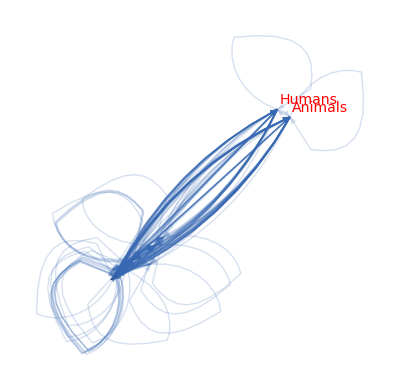

```mathematica
g[gen]=Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

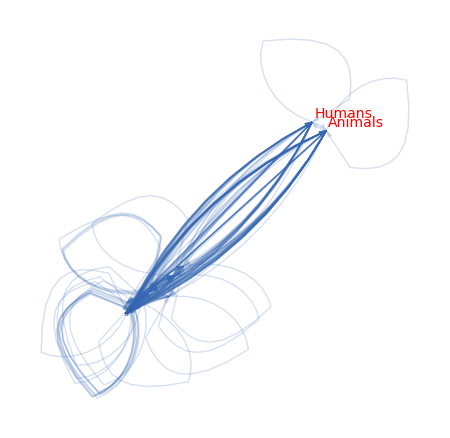

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 2000

```mathematica
gen=2000
```

2000

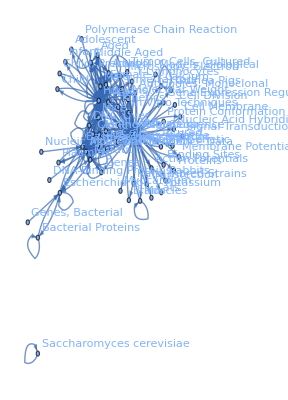

```mathematica
Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Mice,Adult,Rats,Base Sequence,Middle Aged,Molecular Sequence Data,Amino Acid Sequence,Escherichia coli,Aged,In Vitro Techniques,Kinetics,Cell Line,Cells, Cultured,DNA,Calcium,Adolescent,Microscopy, Electron,Child,Rabbits,Cloning, Molecular,Neurons,Mutation,Time Factors,RNA, Messenger,Muscles,Saccharomyces cerevisiae,Transcription, Genetic,Molecular Weight,Liver,Cell Membrane,Membrane Potentials,Genes,Plasmids,Brain,Bacterial Proteins,Rats, Inbred Strains,Cats,T-Lymphocytes,Gene Expression Regulation,Child, Preschool,Antibodies, Monoclonal,Polymerase Chain Reaction,Binding Sites,Potassium,Genes, Bacterial,Guinea Pigs,Signal Transduction,Cell Division,Tumor Cells, Cultured,Protein Conformation,Action Potentials,Infant,Myocardium,Proteins,Models, Biological,Cattle,Transfection,DNA-Binding Proteins,Nucleic Acid Conformation,Nucleic Acid Hybridization}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Animals->Humans,Humans->Animals,Male->Humans,Female->Humans,Humans->Male,Humans->Female,Mice->Animals,Adult->Humans,Animals->Mice,Male->Animals,Rats->Animals,Humans->Adult,Animals->Rats,Base Sequence->Base Sequence,Female->Animals,Middle Aged->Humans,Molecular Sequence Data->Animals,Molecular Sequence Data->Base Sequence,Male->Male,Humans->Middle Aged,Animals->Male,Molecular Sequence Data->Molecular Sequence Data,Animals->Base Sequence,Animals->Molecular Sequence Data,Female->Female,Animals->Female,Mice->Mice,Base Sequence->Animals,Humans->Molecular Sequence Data,Molecular Sequence Data->Humans,Humans->Mice,Humans->Base Sequence,Base Sequence->Molecular Sequence Data,Animals->Amino Acid Sequence,Female->Male,Molecular Sequence Data->Amino Acid Sequence,Male->Female,Escherichia coli->Escherichia coli,Aged->Humans,Mice->Humans,Amino Acid Sequence->Animals,Humans->Aged,Base Sequence->Humans,Animals->In Vitro Techniques,Animals->Kinetics,Animals->Cell Line,Rats->Rats,Amino Acid Sequence->Amino Acid Sequence,Humans->Amino Acid Sequence,Cell Line->Animals,In Vitro Techniques->Animals,Rats->Humans,Amino Acid Sequence->Molecular Sequence Data,Cells, Cultured->Animals,Humans->Cell Line,Male->Adult,Base Sequence->Amino Acid Sequence,Amino Acid Sequence->Base Sequence,Kinetics->Animals,Animals->Cells, Cultured,Female->Adult,Animals->DNA,Adult->Male,Humans->Rats,Amino Acid Sequence->Humans,Calcium->Animals,Adult->Female,Adult->Adult,Adolescent->Humans,Humans->Kinetics,Animals->Microscopy, Electron,Male->Rats,Child->Humans,Animals->Calcium,Cell Line->Humans,Female->Middle Aged,Humans->Adolescent,Animals->Rabbits,Animals->Cloning, Molecular,Animals->Neurons,Microscopy, Electron->Animals,Male->Middle Aged,Mutation->Mutation,Molecular Sequence Data->Cloning, Molecular,Humans->Child,Humans->Time Factors,Humans->DNA,RNA, Messenger->Animals,Humans->Cells, Cultured,Animals->Mutation,Time Factors->Animals,Animals->Muscles,Animals->RNA, Messenger,Base Sequence->Cloning, Molecular,Time Factors->Humans,Middle Aged->Male,Saccharomyces cerevisiae->Saccharomyces cerevisiae,Middle Aged->Female,Animals->Transcription, Genetic,Base Sequence->Transcription, Genetic,Rabbits->Animals,Neurons->Animals,Cells, Cultured->Humans,Base Sequence->DNA,Animals->Molecular Weight,Animals->Time Factors,Molecular Sequence Data->Transcription, Genetic,DNA->Animals,Humans->In Vitro Techniques,Rats->Male,Female->Mice,Kinetics->Humans,Cloning, Molecular->Base Sequence,Transcription, Genetic->Base Sequence,Molecular Sequence Data->Mutation,Base Sequence->Escherichia coli,Middle Aged->Adult,Cloning, Molecular->Animals,Humans->Cloning, Molecular,Base Sequence->Mutation,Adult->Middle Aged,Animals->Liver,Animals->Cell Membrane,Mutation->Animals,Membrane Potentials->Animals,Mutation->Escherichia coli,Animals->Membrane Potentials,In Vitro Techniques->Humans,Molecular Sequence Data->DNA,Transcription, Genetic->Animals,Escherichia coli->Mutation,Middle Aged->Middle Aged,Molecular Sequence Data->Escherichia coli,Base Sequence->Genes,Humans->Mutation,Cell Membrane->Animals,Mutation->Base Sequence,Male->Mice,Molecular Sequence Data->Mice,Animals->Genes,Mice->Molecular Sequence Data,Adult->Animals,Base Sequence->Plasmids,Animals->Brain,DNA->Humans,Mice->Base Sequence,RNA, Messenger->Base Sequence,Mutation->Humans,Liver->Animals,RNA, Messenger->Humans,Base Sequence->RNA, Messenger,Calcium->Calcium,Female->Aged,Bacterial Proteins->Escherichia coli,Male->Aged,DNA->DNA,Escherichia coli->Base Sequence,Cell Line->Cell Line,Rats, Inbred Strains->Animals,Microscopy, Electron->Humans,Transcription, Genetic->Transcription, Genetic,Molecular Sequence Data->Plasmids,Kinetics->Kinetics,Humans->RNA, Messenger,Mice->Female,Aged->Female,Amino Acid Sequence->Cloning, Molecular,Cloning, Molecular->Molecular Sequence Data,Microscopy, Electron->Microscopy, Electron,Humans->Molecular Weight,Animals->Cats,Female->Rats,Aged->Male,Humans->T-Lymphocytes,DNA->Base Sequence,Bacterial Proteins->Bacterial Proteins,Humans->Transcription, Genetic,Animals->Gene Expression Regulation,Base Sequence->Mice,Muscles->Animals,Child, Preschool->Humans,Humans->Antibodies, Monoclonal,Cloning, Molecular->Amino Acid Sequence,Polymerase Chain Reaction->Humans,Binding Sites->Animals,Mice->Cell Line,Molecular Sequence Data->Cell Line,Animals->Potassium,Animals->Antibodies, Monoclonal,Molecular Sequence Data->RNA, Messenger,Humans->Liver,Genes, Bacterial->Escherichia coli,Escherichia coli->Bacterial Proteins,Animals->Guinea Pigs,Signal Transduction->Animals,Mice->Male,Humans->Child, Preschool,RNA, Messenger->RNA, Messenger,Muscles->Muscles,Animals->Adult,Cell Division->Animals,Animals->Binding Sites,Molecular Sequence Data->Genes,Tumor Cells, Cultured->Animals,Tumor Cells, Cultured->Humans,Gene Expression Regulation->Animals,Animals->Protein Conformation,Plasmids->Base Sequence,T-Lymphocytes->Animals,Animals->Action Potentials,Infant->Humans,Animals->Myocardium,Humans->Infant,Cell Line->Mice,Molecular Weight->Animals,Animals->Proteins,Models, Biological->Animals,Animals->T-Lymphocytes,Brain->Animals,Transcription, Genetic->Molecular Sequence Data,Animals->Cattle,Transfection->Animals,Rats->Mice,Antibodies, Monoclonal->Animals,DNA-Binding Proteins->Molecular Sequence Data,Nucleic Acid Conformation->Base Sequence,Mutation->Molecular Sequence Data,Mice->Amino Acid Sequence,Aged->Adult,Aged->Middle Aged,Animals->Nucleic Acid Hybridization,Animals->Transfection}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ2CitingCitedMeSHgraph[gen],EdgeWeight]
```

{639.45,506.705,257.639,242.148,197.994,188.314,165.932,157.816,128.533,128.141,126.441,119.591,119.328,118.526,111.546,99.6883,96.7424,95.896,92.4592,92.4149,92.1,91.8691,90.6932,90.6225,82.8181,81.8081,79.0743,77.1427,76.0987,75.5315,75.0943,72.6498,70.2972,69.8144,69.1626,69.0739,68.2416,67.5897,66.8574,65.8327,65.1782,63.2863,61.4198,60.8423,58.1562,57.6897,57.1054,56.8587,56.1968,55.9674,54.9226,54.7967,54.0069,53.6822,53.3514,51.4123,50.0559,49.9609,48.6734,48.5368,48.4597,47.1433,46.9298,46.3038,46.1058,45.06,43.1113,42.288,41.5188,41.4891,41.2594,40.8198,40.3943,40.1993,38.9191,38.6854,38.6762,37.7073,37.5513,37.3539,36.9201,36.8891,36.8508,36.589,36.3732,36.2732,35.6313,35.3908,35.2684,35.0312,34.5426,34.277,34.223,34.101,34.0965,33.8695,33.801,33.4685,33.4484,32.8524,32.7134,32.5689,32.5004,32.0874,31.6381,31.5207,31.4117,31.0758,30.9932,30.9676,30.8513,30.2731,30.1285,29.9538,29.9495,29.7502,29.7311,29.503,29.4324,29.3307,29.1708,29.1691,28.9782,28.6548,28.5755,28.3832,28.3262,28.15,28.0507,28.0361,27.8353,27.805,27.1693,27.0046,26.6343,26.396,26.0347,25.6101,25.5495,25.3669,25.3289,25.2403,25.2134,25.0512,24.7929,24.7147,24.6956,24.6187,24.5487,24.3339,24.2758,24.2441,24.1281,24.0046,23.9777,23.8676,23.826,23.6476,23.6247,23.621,23.4531,23.3501,23.0297,22.9951,22.9931,22.9906,22.8177,22.7491,22.6475,22.5368,22.4675,22.4364,22.4001,22.3786,22.3332,22.2096,22.1809,22.1187,22.0051,21.8459,21.8434,21.8245,21.8012,21.7735,21.6334,21.6087,21.5394,21.3485,21.273,21.1467,21.1248,21.0332,20.9818,20.9585,20.8638,20.8158,20.7453,20.729,20.7289,20.7288,20.6527,20.6277,20.5188,20.4351,20.4021,20.3642,20.3363,20.1851,20.1069,20.0926,20.0422,20.0055,19.9795,19.8559,19.8027,19.7976,19.787,19.7412,19.708,19.6687,19.6061,19.5171,19.5065,19.4468,19.369,19.3275,19.2758,19.2072,19.201,19.1954,19.1778,19.0821,19.0714,19.0667}

```mathematica
topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

639.45 | 242.148 | 165.932 | 157.816 | 70.2972 | 118.526 | 45.06 | 69.8144 | 91.8691 | 75.0943 | 54.9226 | 0 | 60.8423 | 30.8513 | 40.8198 | 50.0559 | 34.5426 | 35.2684 | 0 | 37.5513 | 0 | 35.6313 | 0 | 29.1708 | 0 | 26.0347 | 35.3908 | 22.9906 | 0 | 0 | 22.0051 | 22.4364 | 20.9818 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22.2096 | 0 | 20.7289 | 21.7735 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.8027 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
257.639 | 506.705 | 90.6932 | 77.1427 | 126.441 | 20.6277 | 111.546 | 82.8181 | 0 | 81.8081 | 69.0739 | 0 | 0 | 57.6897 | 57.1054 | 56.8587 | 47.1433 | 46.3038 | 38.6854 | 0 | 40.3943 | 0 | 37.3539 | 36.9201 | 36.8891 | 34.277 | 31.0758 | 34.0965 | 34.101 | 0 | 32.7134 | 31.4117 | 28.6548 | 28.5755 | 28.0507 | 25.2403 | 0 | 24.7147 | 0 | 0 | 22.4001 | 19.6687 | 21.8459 | 0 | 21.1248 | 0 | 20.4351 | 21.1467 | 0 | 20.8158 | 0 | 0 | 0 | 20.1069 | 20.0055 | 0 | 19.8559 | 19.7412 | 0 | 19.5065 | 19.0667 | 0 | 0 | 19.0714
197.994 | 119.591 | 92.1 | 66.8574 | 25.3669 | 49.9609 | 40.1993 | 0 | 36.589 | 0 | 0 | 0 | 23.826 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
188.314 | 96.7424 | 68.2416 | 79.0743 | 30.1285 | 46.9298 | 22.3786 | 0 | 37.7073 | 0 | 0 | 0 | 23.9777 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
63.2863 | 128.533 | 20.729 | 22.8177 | 76.0987 | 0 | 0 | 24.6187 | 0 | 25.2134 | 19.1954 | 0 | 0 | 0 | 0 | 21.3485 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
128.141 | 25.0512 | 46.1058 | 41.5188 | 0 | 41.4891 | 0 | 0 | 28.9782 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
53.6822 | 119.328 | 30.2731 | 0 | 19.369 | 0 | 56.1968 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
58.1562 | 75.5315 | 0 | 0 | 21.8434 | 0 | 0 | 99.6883 | 0 | 69.1626 | 48.6734 | 29.503 | 0 | 0 | 0 | 0 | 0 | 31.5207 | 0 | 0 | 0 | 0 | 0 | 33.8695 | 0 | 29.1691 | 0 | 24.1281 | 0 | 0 | 32.5689 | 0 | 0 | 0 | 0 | 26.396 | 24.7929 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
95.896 | 0 | 33.4685 | 32.8524 | 0 | 29.4324 | 0 | 0 | 27.0046 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
72.6498 | 92.4592 | 0 | 0 | 25.3289 | 0 | 0 | 92.4149 | 0 | 90.6225 | 67.5897 | 26.6343 | 0 | 0 | 0 | 21.273 | 0 | 27.8353 | 0 | 0 | 0 | 0 | 0 | 36.2732 | 0 | 29.7311 | 0 | 21.0332 | 0 | 0 | 30.9932 | 0 | 0 | 0 | 0 | 20.4021 | 22.9951 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
43.1113 | 61.4198 | 0 | 0 | 0 | 0 | 0 | 48.5368 | 0 | 53.3514 | 55.9674 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22.6475 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 23.6247 | 0 | 0 | 0 | 65.8327 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 27.1693 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 20.8638 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
65.1782 | 0 | 22.3332 | 22.7491 | 0 | 19.1778 | 0 | 0 | 19.0821 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
28.0361 | 54.0069 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
29.9538 | 48.4597 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22.9931 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
38.6762 | 54.7967 | 0 | 0 | 19.7976 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23.621 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
31.6381 | 51.4123 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
24.6956 | 30.9676 | 0 | 0 | 0 | 0 | 0 | 22.1809 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23.6476 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 42.288 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24.0046 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
41.2594 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23.3501 | 36.8508 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22.4675 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
38.9191 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 32.5004 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 29.3307 | 0 | 0 | 0 | 0 | 0 | 29.9495 | 0 | 22.5368 | 21.6334 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 32.0874 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
24.3339 | 28.3832 | 0 | 0 | 0 | 0 | 0 | 25.5495 | 0 | 19.201 | 0 | 28.15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 36.3732 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
33.801 | 34.223 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
24.2441 | 35.0312 | 0 | 0 | 0 | 0 | 0 | 24.5487 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 20.7288 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 21.8245 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 20.6527 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 33.4484 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 27.805 | 0 | 0 | 0 | 0 | 0 | 29.7502 | 0 | 19.5171 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23.0297 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 19.787 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 24.2758 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 25.6101 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 28.3262 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 20.0926 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 19.6061 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23.8676 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22.1187 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 23.4531 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 20.0422 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 20.1851 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21.8012 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 19.3275 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21.6087 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 21.5394 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 20.9585 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 20.7453 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 20.5188 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
20.3363 | 20.3642 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
19.9795 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 19.708 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 19.4468 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.2758 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.2072 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{2320.02,2497.54,652.484,593.494,401.841,311.284,278.849,605.004,218.654,678.235,285.034,137.49,148.52,82.043,101.407,136.891,83.0504,101.492,66.2926,41.2594,82.6684,38.9191,32.5004,103.45,32.0874,161.991,68.024,104.553,42.4772,33.4484,100.102,19.787,24.2758,25.6101,28.3262,0,20.0926,19.6061,45.9862,23.4531,0,20.0422,20.1851,21.8012,19.3275,21.6087,21.5394,0,20.9585,0,20.7453,20.5188,40.7005,0,0,19.9795,0,0,19.708,0,19.4468,19.2758,19.2072,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Animals

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{2286.13,2350.41,569.877,500.829,414.671,326.144,275.381,612.795,241.23,475.783,337.056,194.946,108.646,88.541,120.918,173.157,81.6858,164.576,62.6899,37.5513,62.8618,35.6313,37.3539,158.881,36.8891,182.754,66.4666,122.977,54.7537,33.4484,141.31,53.8481,49.6366,28.5755,28.0507,72.0384,47.7879,24.7147,42.9824,0,22.4001,41.8783,21.8459,20.7289,42.8983,0,20.4351,21.1467,0,20.8158,0,0,0,20.1069,20.0055,19.8027,19.8559,19.7412,0,19.5065,19.0667,0,0,19.0714}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Animals

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{4606.15,4847.95,1222.36,1094.32,816.512,637.428,554.23,1217.8,459.884,1154.02,622.09,332.436,257.166,170.584,222.325,310.049,164.736,266.068,128.982,78.8107,145.53,74.5504,69.8543,262.332,68.9765,344.745,134.491,227.53,97.2309,66.8968,241.412,73.6351,73.9124,54.1855,56.3769,72.0384,67.8805,44.3208,88.9687,23.4531,22.4001,61.9205,42.031,42.5302,62.2258,21.6087,41.9746,21.1467,20.9585,20.8158,20.7453,20.5188,40.7005,20.1069,20.0055,39.7822,19.8559,19.7412,19.708,19.5065,38.5135,19.2758,19.2072,19.0714}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{2320.02,2286.13},{2497.54,2350.41},{652.484,569.877},{593.494,500.829},{401.841,414.671},{311.284,326.144},{278.849,275.381},{605.004,612.795},{218.654,241.23},{678.235,475.783},{285.034,337.056},{137.49,194.946},{148.52,108.646},{82.043,88.541},{101.407,120.918},{136.891,173.157},{83.0504,81.6858},{101.492,164.576},{66.2926,62.6899},{41.2594,37.5513},{82.6684,62.8618},{38.9191,35.6313},{32.5004,37.3539},{103.45,158.881},{32.0874,36.8891},{161.991,182.754},{68.024,66.4666},{104.553,122.977},{42.4772,54.7537},{33.4484,33.4484},{100.102,141.31},{19.787,53.8481},{24.2758,49.6366},{25.6101,28.5755},{28.3262,28.0507},{0,72.0384},{20.0926,47.7879},{19.6061,24.7147},{45.9862,42.9824},{23.4531,0},{0,22.4001},{20.0422,41.8783},{20.1851,21.8459},{21.8012,20.7289},{19.3275,42.8983},{21.6087,0},{21.5394,20.4351},{0,21.1467},{20.9585,0},{0,20.8158},{20.7453,0},{20.5188,0},{40.7005,0},{0,20.1069},{0,20.0055},{19.9795,19.8027},{0,19.8559},{0,19.7412},{19.708,0},{0,19.5065},{19.4468,19.0667},{19.2758,0},{19.2072,0},{0,19.0714}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

342.96

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.799312],Animals->Animals→Thickness[0.633382],Animals->Humans→Thickness[0.322049],Humans->Animals→Thickness[0.302685],Male->Humans→Thickness[0.247492],Female->Humans→Thickness[0.235392],Humans->Male→Thickness[0.207415],Humans->Female→Thickness[0.19727],Mice->Animals→Thickness[0.160666],Adult->Humans→Thickness[0.160176],Animals->Mice→Thickness[0.158052],Male->Animals→Thickness[0.149488],Rats->Animals→Thickness[0.149159],Humans->Adult→Thickness[0.148158],Animals->Rats→Thickness[0.139433],Base Sequence->Base Sequence→Thickness[0.12461],Female->Animals→Thickness[0.120928],Middle Aged->Humans→Thickness[0.11987],Molecular Sequence Data->Animals→Thickness[0.115574],Molecular Sequence Data->Base Sequence→Thickness[0.115519],Male->Male→Thickness[0.115125],Humans->Middle Aged→Thickness[0.114836],Animals->Male→Thickness[0.113366],Molecular Sequence Data->Molecular Sequence Data→Thickness[0.113278],Animals->Base Sequence→Thickness[0.103523],Animals->Molecular Sequence Data→Thickness[0.10226],Female->Female→Thickness[0.0988429],Animals->Female→Thickness[0.0964284],Mice->Mice→Thickness[0.0951233],Base Sequence->Animals→Thickness[0.0944144],Humans->Molecular Sequence Data→Thickness[0.0938679],Molecular Sequence Data->Humans→Thickness[0.0908123],Humans->Mice→Thickness[0.0878715],Humans->Base Sequence→Thickness[0.087268],Base Sequence->Molecular Sequence Data→Thickness[0.0864533],Animals->Amino Acid Sequence→Thickness[0.0863423],Female->Male→Thickness[0.085302],Molecular Sequence Data->Amino Acid Sequence→Thickness[0.0844872],Male->Female→Thickness[0.0835717],Escherichia coli->Escherichia coli→Thickness[0.0822908],Aged->Humans→Thickness[0.0814728],Mice->Humans→Thickness[0.0791079],Amino Acid Sequence->Animals→Thickness[0.0767748],Humans->Aged→Thickness[0.0760529],Base Sequence->Humans→Thickness[0.0726953],Animals->In Vitro Techniques→Thickness[0.0721122],Animals->Kinetics→Thickness[0.0713817],Animals->Cell Line→Thickness[0.0710734],Rats->Rats→Thickness[0.0702461],Amino Acid Sequence->Amino Acid Sequence→Thickness[0.0699592],Humans->Amino Acid Sequence→Thickness[0.0686532],Cell Line->Animals→Thickness[0.0684958],In Vitro Techniques->Animals→Thickness[0.0675086],Rats->Humans→Thickness[0.0671027],Amino Acid Sequence->Molecular Sequence Data→Thickness[0.0666893],Cells, Cultured->Animals→Thickness[0.0642654],Humans->Cell Line→Thickness[0.0625698],Male->Adult→Thickness[0.0624512],Base Sequence->Amino Acid Sequence→Thickness[0.0608418],Amino Acid Sequence->Base Sequence→Thickness[0.060671],Kinetics->Animals→Thickness[0.0605746],Animals->Cells, Cultured→Thickness[0.0589291],Female->Adult→Thickness[0.0586622],Animals->DNA→Thickness[0.0578798],Adult->Male→Thickness[0.0576322],Humans->Rats→Thickness[0.056325],Amino Acid Sequence->Humans→Thickness[0.0538891],Calcium->Animals→Thickness[0.05286],Adult->Female→Thickness[0.0518985],Adult->Adult→Thickness[0.0518614],Adolescent->Humans→Thickness[0.0515742],Humans->Kinetics→Thickness[0.0510247],Animals->Microscopy, Electron→Thickness[0.0504928],Male->Rats→Thickness[0.0502492],Child->Humans→Thickness[0.0486489],Animals->Calcium→Thickness[0.0483567],Cell Line->Humans→Thickness[0.0483452],Female->Middle Aged→Thickness[0.0471342],Humans->Adolescent→Thickness[0.0469392],Animals->Rabbits→Thickness[0.0466923],Animals->Cloning, Molecular→Thickness[0.0461502],Animals->Neurons→Thickness[0.0461114],Microscopy, Electron->Animals→Thickness[0.0460635],Male->Middle Aged→Thickness[0.0457363],Mutation->Mutation→Thickness[0.0454665],Molecular Sequence Data->Cloning, Molecular→Thickness[0.0453415],Humans->Child→Thickness[0.0445391],Humans->Time Factors→Thickness[0.0442384],Humans->DNA→Thickness[0.0440855],RNA, Messenger->Animals→Thickness[0.043789],Humans->Cells, Cultured→Thickness[0.0431782],Animals->Mutation→Thickness[0.0428463],Time Factors->Animals→Thickness[0.0427787],Animals->Muscles→Thickness[0.0426263],Animals->RNA, Messenger→Thickness[0.0426206],Base Sequence->Cloning, Molecular→Thickness[0.0423369],Time Factors->Humans→Thickness[0.0422513],Middle Aged->Male→Thickness[0.0418357],Saccharomyces cerevisiae->Saccharomyces cerevisiae→Thickness[0.0418105],Middle Aged->Female→Thickness[0.0410655],Animals->Transcription, Genetic→Thickness[0.0408918],Base Sequence->Transcription, Genetic→Thickness[0.0407111],Rabbits->Animals→Thickness[0.0406255],Neurons->Animals→Thickness[0.0401093],Cells, Cultured->Humans→Thickness[0.0395476],Base Sequence->DNA→Thickness[0.0394009],Animals->Molecular Weight→Thickness[0.0392646],Animals->Time Factors→Thickness[0.0388448],Molecular Sequence Data->Transcription, Genetic→Thickness[0.0387415],DNA->Animals→Thickness[0.0387095],Humans->In Vitro Techniques→Thickness[0.0385641],Rats->Male→Thickness[0.0378414],Female->Mice→Thickness[0.0376606],Kinetics->Humans→Thickness[0.0374422],Cloning, Molecular->Base Sequence→Thickness[0.0374369],Transcription, Genetic->Base Sequence→Thickness[0.0371878],Molecular Sequence Data->Mutation→Thickness[0.0371638],Base Sequence->Escherichia coli→Thickness[0.0368787],Middle Aged->Adult→Thickness[0.0367905],Cloning, Molecular->Animals→Thickness[0.0366634],Humans->Cloning, Molecular→Thickness[0.0364635],Base Sequence->Mutation→Thickness[0.0364614],Adult->Middle Aged→Thickness[0.0362228],Animals->Liver→Thickness[0.0358185],Animals->Cell Membrane→Thickness[0.0357193],Mutation->Animals→Thickness[0.035479],Membrane Potentials->Animals→Thickness[0.0354078],Mutation->Escherichia coli→Thickness[0.0351874],Animals->Membrane Potentials→Thickness[0.0350634],In Vitro Techniques->Humans→Thickness[0.0350452],Molecular Sequence Data->DNA→Thickness[0.0347942],Transcription, Genetic->Animals→Thickness[0.0347562],Escherichia coli->Mutation→Thickness[0.0339616],Middle Aged->Middle Aged→Thickness[0.0337557],Molecular Sequence Data->Escherichia coli→Thickness[0.0332929],Base Sequence->Genes→Thickness[0.032995],Humans->Mutation→Thickness[0.0325434],Cell Membrane->Animals→Thickness[0.0320126],Mutation->Base Sequence→Thickness[0.0319369],Male->Mice→Thickness[0.0317086],Molecular Sequence Data->Mice→Thickness[0.0316611],Animals->Genes→Thickness[0.0315504],Mice->Molecular Sequence Data→Thickness[0.0315167],Adult->Animals→Thickness[0.0313141],Base Sequence->Plasmids→Thickness[0.0309911],Animals->Brain→Thickness[0.0308934],DNA->Humans→Thickness[0.0308695],Mice->Base Sequence→Thickness[0.0307734],RNA, Messenger->Base Sequence→Thickness[0.0306858],Mutation->Humans→Thickness[0.0304173],Liver->Animals→Thickness[0.0303448],RNA, Messenger->Humans→Thickness[0.0303051],Base Sequence->RNA, Messenger→Thickness[0.0301601],Calcium->Calcium→Thickness[0.0300057],Female->Aged→Thickness[0.0299721],Bacterial Proteins->Escherichia coli→Thickness[0.0298345],Male->Aged→Thickness[0.0297825],DNA->DNA→Thickness[0.0295595],Escherichia coli->Base Sequence→Thickness[0.0295309],Cell Line->Cell Line→Thickness[0.0295263],Rats, Inbred Strains->Animals→Thickness[0.0293164],Microscopy, Electron->Humans→Thickness[0.0291876],Transcription, Genetic->Transcription, Genetic→Thickness[0.0287871],Molecular Sequence Data->Plasmids→Thickness[0.0287438],Kinetics->Kinetics→Thickness[0.0287414],Humans->RNA, Messenger→Thickness[0.0287383],Mice->Female→Thickness[0.0285221],Aged->Female→Thickness[0.0284363],Amino Acid Sequence->Cloning, Molecular→Thickness[0.0283094],Cloning, Molecular->Molecular Sequence Data→Thickness[0.028171],Microscopy, Electron->Microscopy, Electron→Thickness[0.0280844],Humans->Molecular Weight→Thickness[0.0280455],Animals->Cats→Thickness[0.0280001],Female->Rats→Thickness[0.0279733],Aged->Male→Thickness[0.0279165],Humans->T-Lymphocytes→Thickness[0.027762],DNA->Base Sequence→Thickness[0.0277261],Bacterial Proteins->Bacterial Proteins→Thickness[0.0276483],Humans->Transcription, Genetic→Thickness[0.0275064],Animals->Gene Expression Regulation→Thickness[0.0273074],Base Sequence->Mice→Thickness[0.0273042],Muscles->Animals→Thickness[0.0272806],Child, Preschool->Humans→Thickness[0.0272515],Humans->Antibodies, Monoclonal→Thickness[0.0272169],Cloning, Molecular->Amino Acid Sequence→Thickness[0.0270417],Polymerase Chain Reaction->Humans→Thickness[0.0270109],Binding Sites->Animals→Thickness[0.0269243],Mice->Cell Line→Thickness[0.0266856],Molecular Sequence Data->Cell Line→Thickness[0.0265913],Animals->Potassium→Thickness[0.0264334],Animals->Antibodies, Monoclonal→Thickness[0.026406],Molecular Sequence Data->RNA, Messenger→Thickness[0.0262915],Humans->Liver→Thickness[0.0262272],Genes, Bacterial->Escherichia coli→Thickness[0.0261981],Escherichia coli->Bacterial Proteins→Thickness[0.0260797],Animals->Guinea Pigs→Thickness[0.0260197],Signal Transduction->Animals→Thickness[0.0259316],Mice->Male→Thickness[0.0259113],Humans->Child, Preschool→Thickness[0.0259112],RNA, Messenger->RNA, Messenger→Thickness[0.025911],Muscles->Muscles→Thickness[0.0258159],Animals->Adult→Thickness[0.0257847],Cell Division->Animals→Thickness[0.0256486],Animals->Binding Sites→Thickness[0.0255439],Molecular Sequence Data->Genes→Thickness[0.0255026],Tumor Cells, Cultured->Animals→Thickness[0.0254552],Tumor Cells, Cultured->Humans→Thickness[0.0254203],Gene Expression Regulation->Animals→Thickness[0.0252313],Animals->Protein Conformation→Thickness[0.0251336],Plasmids->Base Sequence→Thickness[0.0251158],T-Lymphocytes->Animals→Thickness[0.0250528],Animals->Action Potentials→Thickness[0.0250069],Infant->Humans→Thickness[0.0249744],Animals->Myocardium→Thickness[0.0248198],Humans->Infant→Thickness[0.0247534],Cell Line->Mice→Thickness[0.024747],Molecular Weight->Animals→Thickness[0.0247338],Animals->Proteins→Thickness[0.0246765],Models, Biological->Animals→Thickness[0.024635],Animals->T-Lymphocytes→Thickness[0.0245859],Brain->Animals→Thickness[0.0245076],Transcription, Genetic->Molecular Sequence Data→Thickness[0.0243963],Animals->Cattle→Thickness[0.0243832],Transfection->Animals→Thickness[0.0243085],Rats->Mice→Thickness[0.0242113],Antibodies, Monoclonal->Animals→Thickness[0.0241594],DNA-Binding Proteins->Molecular Sequence Data→Thickness[0.0240948],Nucleic Acid Conformation->Base Sequence→Thickness[0.024009],Mutation->Molecular Sequence Data→Thickness[0.0240013],Mice->Amino Acid Sequence→Thickness[0.0239943],Aged->Adult→Thickness[0.0239723],Aged->Middle Aged→Thickness[0.0238527],Animals->Nucleic Acid Hybridization→Thickness[0.0238392],Animals->Transfection→Thickness[0.0238333]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Animals→Animals,Animals→Animals}

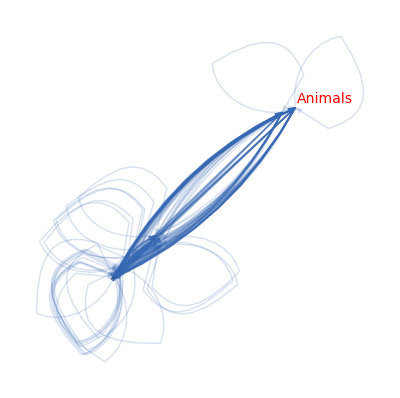

```mathematica
g[gen]=Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

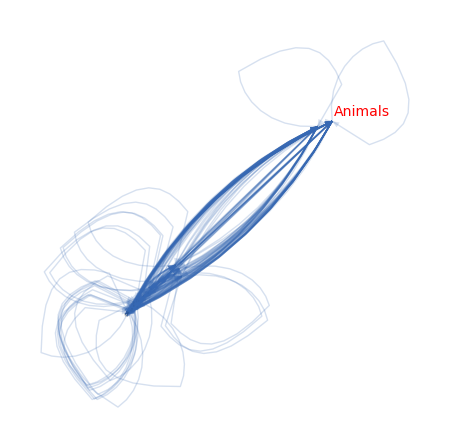

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 2005

```mathematica
gen=2005
```

2005

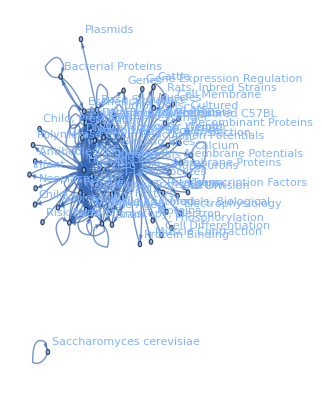

```mathematica
Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Adult,Mice,Rats,Middle Aged,Molecular Sequence Data,Base Sequence,Aged,Amino Acid Sequence,Escherichia coli,Cell Line,Kinetics,Cells, Cultured,In Vitro Techniques,Adolescent,Neurons,Calcium,Time Factors,Child,Microscopy, Electron,Mutation,DNA,RNA, Messenger,Cloning, Molecular,Muscles,Rabbits,Transcription, Genetic,Saccharomyces cerevisiae,Cell Membrane,Signal Transduction,Membrane Potentials,Bacterial Proteins,Child, Preschool,Brain,Liver,Molecular Weight,Infant,Cats,Genes,Models, Biological,Gene Expression Regulation,Cattle,T-Lymphocytes,Binding Sites,DNA-Binding Proteins,Polymerase Chain Reaction,Rats, Inbred Strains,Cell Division,Mice, Inbred C57BL,Transcription Factors,Proteins,Action Potentials,Membrane Proteins,Tumor Cells, Cultured,Protein Binding,Transfection,Risk Factors,Plasmids,Muscle Contraction,Antibodies, Monoclonal,Neoplasms,Recombinant Proteins,Cell Differentiation,Potassium,Phosphorylation,Electrophysiology}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Animals->Humans,Humans->Animals,Male->Humans,Female->Humans,Humans->Male,Humans->Female,Humans->Adult,Mice->Animals,Animals->Mice,Adult->Humans,Male->Animals,Rats->Animals,Humans->Middle Aged,Animals->Rats,Male->Male,Female->Animals,Middle Aged->Humans,Animals->Male,Female->Female,Animals->Molecular Sequence Data,Animals->Female,Humans->Molecular Sequence Data,Molecular Sequence Data->Animals,Molecular Sequence Data->Molecular Sequence Data,Animals->Base Sequence,Mice->Mice,Humans->Aged,Female->Male,Male->Female,Humans->Mice,Base Sequence->Base Sequence,Mice->Humans,Animals->Amino Acid Sequence,Humans->Base Sequence,Molecular Sequence Data->Base Sequence,Aged->Humans,Molecular Sequence Data->Humans,Base Sequence->Animals,Escherichia coli->Escherichia coli,Humans->Amino Acid Sequence,Molecular Sequence Data->Amino Acid Sequence,Amino Acid Sequence->Animals,Male->Adult,Rats->Rats,Female->Adult,Animals->Cell Line,Base Sequence->Molecular Sequence Data,Cell Line->Animals,Adult->Male,Animals->Kinetics,Amino Acid Sequence->Amino Acid Sequence,Amino Acid Sequence->Molecular Sequence Data,Rats->Humans,Base Sequence->Humans,Cells, Cultured->Animals,In Vitro Techniques->Animals,Humans->Cell Line,Adult->Female,Humans->Adolescent,Adult->Adult,Animals->In Vitro Techniques,Female->Middle Aged,Animals->Cells, Cultured,Male->Middle Aged,Adolescent->Humans,Amino Acid Sequence->Humans,Humans->Rats,Animals->Neurons,Kinetics->Animals,Amino Acid Sequence->Base Sequence,Cell Line->Humans,Middle Aged->Male,Male->Rats,Animals->Calcium,Neurons->Animals,Humans->Time Factors,Middle Aged->Female,Humans->Child,Base Sequence->Amino Acid Sequence,Child->Humans,Animals->Microscopy, Electron,Calcium->Animals,Humans->Kinetics,Mutation->Mutation,Animals->DNA,Animals->RNA, Messenger,Time Factors->Animals,Animals->Mutation,RNA, Messenger->Animals,Mutation->Animals,Time Factors->Humans,Middle Aged->Adult,Humans->Cells, Cultured,Animals->Time Factors,Adult->Middle Aged,Middle Aged->Middle Aged,Animals->Cloning, Molecular,Cells, Cultured->Humans,Animals->Muscles,Microscopy, Electron->Animals,Female->Aged,Humans->Mutation,Male->Aged,Animals->Rabbits,Rats->Male,Mutation->Humans,Animals->Transcription, Genetic,Humans->DNA,Female->Mice,Saccharomyces cerevisiae->Saccharomyces cerevisiae,Animals->Cell Membrane,Humans->RNA, Messenger,Aged->Female,Aged->Male,Transcription, Genetic->Animals,Signal Transduction->Animals,Molecular Sequence Data->Cloning, Molecular,Mice->Molecular Sequence Data,Mutation->Escherichia coli,Mice->Female,Molecular Sequence Data->Mutation,Kinetics->Humans,Membrane Potentials->Animals,Bacterial Proteins->Escherichia coli,Rabbits->Animals,Escherichia coli->Mutation,Adult->Animals,Humans->Child, Preschool,Cloning, Molecular->Animals,Animals->Brain,Animals->Liver,DNA->Animals,Animals->Molecular Weight,Base Sequence->Transcription, Genetic,Bacterial Proteins->Bacterial Proteins,Humans->Infant,Mice->Base Sequence,Humans->Cloning, Molecular,Mutation->Base Sequence,Base Sequence->Cloning, Molecular,Cell Membrane->Animals,Transcription, Genetic->Base Sequence,Male->Mice,Base Sequence->DNA,Mutation->Molecular Sequence Data,RNA, Messenger->Humans,Aged->Middle Aged,Base Sequence->Mutation,Animals->Adult,Middle Aged->Aged,Animals->Membrane Potentials,Cloning, Molecular->Base Sequence,Base Sequence->Escherichia coli,Mice->Male,Animals->Signal Transduction,Animals->Cats,Molecular Sequence Data->Escherichia coli,Molecular Sequence Data->Transcription, Genetic,Animals->Genes,Models, Biological->Animals,In Vitro Techniques->Humans,Humans->In Vitro Techniques,Humans->Transcription, Genetic,Molecular Sequence Data->Mice,Calcium->Calcium,Aged->Adult,Gene Expression Regulation->Animals,Child, Preschool->Humans,Animals->Cattle,Humans->T-Lymphocytes,Cell Line->Cell Line,Binding Sites->Animals,DNA-Binding Proteins->Animals,Animals->Binding Sites,Molecular Sequence Data->DNA,Liver->Animals,Mice->Cell Line,Adult->Aged,Animals->Gene Expression Regulation,Microscopy, Electron->Microscopy, Electron,Humans->Molecular Weight,Polymerase Chain Reaction->Humans,RNA, Messenger->Base Sequence,Muscles->Animals,Brain->Animals,Aged->Aged,Mice->Amino Acid Sequence,Infant->Humans,Base Sequence->Genes,Female->Rats,Humans->Polymerase Chain Reaction,Transcription, Genetic->Transcription, Genetic,Humans->Microscopy, Electron,DNA->Humans,Rats, Inbred Strains->Animals,Escherichia coli->Base Sequence,Animals->T-Lymphocytes,Cell Division->Animals,Base Sequence->Mice,Mice, Inbred C57BL->Animals,DNA-Binding Proteins->Molecular Sequence Data,Humans->Liver,Mice->Rats,Transcription Factors->Animals,Amino Acid Sequence->Cloning, Molecular,Animals->Proteins,Cell Line->Mice,Animals->DNA-Binding Proteins,Action Potentials->Animals,Muscles->Muscles,Animals->Membrane Proteins,Kinetics->Kinetics,Escherichia coli->Bacterial Proteins,Animals->Models, Biological,DNA->DNA,Animals->Action Potentials,Tumor Cells, Cultured->Humans,Female->Adolescent,Protein Binding->Animals,Microscopy, Electron->Humans,Base Sequence->RNA, Messenger,Animals->Cell Division,Humans->Rabbits,T-Lymphocytes->Animals,Humans->Escherichia coli,Humans->DNA-Binding Proteins,Male->Adolescent,Transfection->Animals,Risk Factors->Humans,Transcription, Genetic->Humans,RNA, Messenger->RNA, Messenger,Mutation->Amino Acid Sequence,Membrane Proteins->Animals,Bacterial Proteins->Molecular Sequence Data,Animals->Escherichia coli,Male->Time Factors,Rats->Female,Transcription, Genetic->Molecular Sequence Data,Base Sequence->Plasmids,Humans->Binding Sites,Animals->Muscle Contraction,Humans->Antibodies, Monoclonal,Humans->Neoplasms,Animals->Middle Aged,Animals->Transcription Factors,Neurons->Neurons,Tumor Cells, Cultured->Animals,Cats->Animals,Humans->Brain,Signal Transduction->Humans,DNA-Binding Proteins->Humans,Recombinant Proteins->Animals,T-Lymphocytes->Humans,Cell Differentiation->Animals,Cattle->Animals,Animals->Potassium,Rats->Mice,Middle Aged->Animals,Phosphorylation->Animals,Cloning, Molecular->Molecular Sequence Data,Amino Acid Sequence->Mutation,Animals->Protein Binding,Animals->Electrophysiology,Animals->Transfection}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ2CitingCitedMeSHgraph[gen],EdgeWeight]
```

{882.998,706.161,363.441,349.046,276.379,267.594,267.494,258.161,190.61,186.71,177.639,174.073,168.161,156.518,154.472,143.462,140.168,135.566,132.346,131.391,124.383,118.885,116.9,115.146,110.458,109.319,107.993,107.393,107.04,105.951,105.616,103.456,102.17,98.3504,97.3209,97.131,96.5597,93.8192,88.304,87.8686,83.5982,81.9584,81.177,77.7621,77.7501,74.576,74.532,74.516,74.164,71.5037,70.5296,69.842,69.6334,69.2238,68.9777,67.3486,67.339,66.5908,66.4343,65.1469,63.5814,62.8851,62.578,60.8852,59.7283,59.6261,57.1,56.4311,56.1887,56.1031,55.7053,55.0461,54.9579,54.6331,54.5084,54.4002,54.0902,53.8424,53.4015,53.3394,52.6116,52.2805,52.2299,51.1291,50.7508,50.5299,50.3785,49.9117,49.7532,48.7356,48.45,47.9027,46.5183,46.3885,46.1299,45.2093,44.9183,44.6784,44.1135,44.0095,43.1134,43.0424,42.3667,41.4376,41.2451,40.7376,40.6428,40.5086,40.5016,40.4842,39.5639,38.9395,38.7187,37.9774,37.6558,37.6479,37.5575,37.4799,37.1173,36.693,36.4185,35.8601,35.7797,35.6276,35.5496,35.4582,35.3151,35.3036,35.2973,35.2555,35.0921,34.9617,34.803,34.5742,34.4173,34.286,34.1513,34.0939,34.0861,33.9138,33.7438,33.5378,33.5104,33.1951,33.0776,32.9799,32.9319,32.9296,32.8741,32.8318,32.4841,32.1951,31.9708,31.8698,31.7477,31.7229,31.6009,31.464,31.3511,31.2817,31.1875,31.134,30.9785,30.5948,30.3956,30.3874,30.3713,30.1544,30.0198,30.0165,30.0101,29.9411,29.7592,29.6525,29.5732,29.5673,29.5366,29.4575,28.8827,28.8524,28.784,28.7676,28.6934,28.6577,28.6214,28.5786,28.5278,28.3691,28.2777,28.2598,28.2371,27.9624,27.8494,27.6351,27.6262,27.5291,27.3707,27.3616,27.2254,27.113,27.1122,27.0684,26.9636,26.9486,26.9461,26.9236,26.873,26.8382,26.7775,26.7528,26.7048,26.6619,26.6176,26.6142,26.5727,26.4899,26.4794,26.352,26.2675,26.0453,26.0061,25.8877,25.8359,25.8012,25.588,25.5133,25.5034,25.5032,25.3294,25.3053,25.2744,25.2664,25.2205,25.154,24.891,24.8049,24.7472,24.737,24.5738,24.4882,24.4546,24.3819,24.3726,24.2625,24.2452,24.216,24.1507,24.1475,24.1146,24.108,24.095,24.0167,24.015,23.9332,23.9236,23.917,23.9162,23.9066,23.8949,23.8095,23.8006,23.7598,23.5865,23.5001,23.4606,23.3891}

```mathematica
topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

882.998 | 349.046 | 267.494 | 258.161 | 190.61 | 103.456 | 56.1887 | 154.472 | 115.146 | 97.131 | 107.04 | 81.9584 | 25.5034 | 66.4343 | 50.7508 | 46.1299 | 30.5948 | 63.5814 | 0 | 0 | 53.8424 | 53.3394 | 27.6262 | 41.4376 | 40.4842 | 37.9774 | 33.9138 | 0 | 25.588 | 30.3956 | 0 | 0 | 0 | 0 | 0 | 35.2555 | 24.095 | 26.9486 | 28.6934 | 34.0939 | 0 | 0 | 0 | 0 | 0 | 29.9411 | 24.3819 | 25.5032 | 27.8494 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24.2625 | 24.2452 | 0 | 0 | 0 | 0 | 0
363.441 | 706.161 | 131.391 | 116.9 | 32.4841 | 177.639 | 143.462 | 24.216 | 118.885 | 107.993 | 0 | 97.3209 | 24.7472 | 74.516 | 69.842 | 59.7283 | 62.578 | 0 | 56.1031 | 54.4002 | 45.2093 | 0 | 52.2299 | 48.7356 | 50.3785 | 49.9117 | 44.1135 | 43.1134 | 40.7376 | 40.5016 | 0 | 38.7187 | 31.6009 | 31.9708 | 0 | 0 | 34.9617 | 34.803 | 34.4173 | 0 | 31.464 | 31.1875 | 26.4899 | 28.784 | 30.0101 | 27.2254 | 29.5673 | 26.7528 | 0 | 0 | 25.8012 | 0 | 24.1507 | 26.8382 | 26.352 | 26.6176 | 0 | 23.5001 | 23.3891 | 0 | 0 | 24.3726 | 0 | 0 | 0 | 0 | 23.9066 | 0 | 23.4606
276.379 | 168.161 | 140.168 | 105.616 | 77.7501 | 33.0776 | 54.5084 | 59.6261 | 0 | 0 | 41.2451 | 0 | 0 | 0 | 0 | 0 | 0 | 25.3294 | 0 | 0 | 24.737 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
267.594 | 135.566 | 105.951 | 124.383 | 74.532 | 39.5639 | 27.9624 | 60.8852 | 0 | 0 | 42.3667 | 0 | 0 | 0 | 0 | 0 | 0 | 26.0453 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
174.073 | 35.2973 | 70.5296 | 65.1469 | 62.8851 | 0 | 0 | 44.9183 | 0 | 0 | 28.8524 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
98.3504 | 186.71 | 31.7229 | 35.8601 | 0 | 107.393 | 26.9461 | 0 | 36.693 | 34.0861 | 0 | 28.2777 | 0 | 28.8827 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
68.9777 | 156.518 | 40.6428 | 24.5738 | 0 | 23.8949 | 74.576 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
132.346 | 23.8095 | 54.6331 | 53.4015 | 46.3885 | 0 | 0 | 44.6784 | 0 | 0 | 32.1951 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
88.304 | 110.458 | 0 | 0 | 0 | 30.3874 | 0 | 0 | 109.319 | 96.5597 | 0 | 81.177 | 31.3511 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 35.7797 | 29.5366 | 0 | 37.1173 | 0 | 0 | 31.2817 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
67.3486 | 87.8686 | 0 | 0 | 0 | 27.1122 | 0 | 0 | 74.164 | 102.17 | 0 | 52.6116 | 31.7477 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32.8318 | 32.9799 | 25.8359 | 33.5378 | 0 | 0 | 34.286 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 28.2371 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24.4546 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
93.8192 | 0 | 37.6479 | 37.6558 | 30.1544 | 0 | 0 | 32.8741 | 0 | 0 | 28.3691 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
56.4311 | 77.7621 | 0 | 0 | 0 | 0 | 0 | 0 | 69.2238 | 55.0461 | 0 | 69.6334 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23.5865 | 0 | 0 | 26.873 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 27.3616 | 0 | 0 | 83.5982 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 35.3036 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 26.5727 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
54.9579 | 71.5037 | 0 | 0 | 0 | 26.7775 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29.7592 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
35.6276 | 55.7053 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 26.6142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
44.0095 | 67.339 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
30.9785 | 66.5908 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
57.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 54.0902 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24.1475 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 51.1291 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 30.3713 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
46.5183 | 49.7532 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
52.2805 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
25.8877 | 43.0424 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 28.7676 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
40.5086 | 47.9027 | 0 | 0 | 0 | 0 | 0 | 0 | 32.9319 | 33.7438 | 0 | 25.154 | 36.4185 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 50.5299 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
27.5291 | 34.5742 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 26.4794 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
32.9296 | 48.45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 28.6214 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 25.2205 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 35.0921 | 0 | 0 | 0 | 0 | 0 | 0 | 23.7598 | 31.8698 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 28.5786 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 26.6619 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 35.3151 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
25.2664 | 37.5575 | 0 | 0 | 0 | 0 | 0 | 0 | 24.4882 | 33.1951 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 27.6351 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 38.9395 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 33.5104 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
24.0167 | 37.4799 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 35.5496 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24.8049 | 0 | 0 | 0 | 35.4582 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 34.1513 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
30.0165 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 28.5278 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 29.4575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
28.2598 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 24.108 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 31.134 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 30.0198 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 23.9162 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23.9236 | 25.5133 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 29.6525 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
24.015 | 29.5732 | 0 | 0 | 0 | 0 | 0 | 0 | 26.9636 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
28.6577 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 27.3707 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 27.113 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 27.0684 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 26.9236 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 26.7048 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 24.891 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
26.2675 | 24.1146 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 26.0061 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 25.3053 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
25.2744 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 23.9332 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 23.917 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 23.8006 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{3596.57,3523.08,1006.6,904.851,481.702,614.922,389.183,387.452,681.272,655.186,260.52,378.556,172.836,182.998,117.947,111.348,97.5693,57.1,78.2377,81.5004,96.2716,52.2805,97.6977,267.189,88.5827,135.222,90.7217,55.2405,35.3151,148.142,38.9395,33.5104,61.4966,35.5496,94.4144,30.0165,28.5278,29.4575,0,28.2598,24.108,0,31.134,30.0198,23.9162,49.4369,29.6525,80.5518,28.6577,27.3707,27.113,27.0684,26.9236,0,26.7048,24.891,50.3821,26.0061,25.3053,25.2744,0,0,0,0,23.9332,23.917,0,23.8006,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{3254.09,3429.57,880.18,821.699,514.804,569.302,383.643,421.67,656.379,647.778,280.069,436.133,268.824,199.592,147.207,105.858,93.1728,114.956,80.2506,84.7714,123.789,53.3394,108.624,268.205,179.859,138.946,175.555,69.7753,66.3256,164.1,38.9395,38.7187,31.6009,31.9708,60.724,35.2555,59.0567,61.7516,63.1108,34.0939,31.464,59.4245,26.4899,28.784,30.0101,57.1664,53.9492,52.256,27.8494,0,25.8012,0,24.1507,26.8382,26.352,26.6176,0,23.5001,23.3891,0,24.4546,24.3726,24.2625,24.2452,0,0,23.9066,0,23.4606}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Animals

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{6850.66,6952.65,1886.78,1726.55,996.507,1184.22,772.826,809.122,1337.65,1302.96,540.589,814.689,441.66,382.591,265.154,217.207,190.742,172.056,158.488,166.272,220.06,105.62,206.321,535.394,268.441,274.167,266.277,125.016,101.641,312.242,77.8789,72.2291,93.0975,67.5204,155.138,65.272,87.5845,91.2091,63.1108,62.3537,55.572,59.4245,57.6239,58.8038,53.9263,106.603,83.6016,132.808,56.5071,27.3707,52.9141,27.0684,51.0742,26.8382,53.0568,51.5086,50.3821,49.5063,48.6945,25.2744,24.4546,24.3726,24.2625,24.2452,23.9332,23.917,23.9066,23.8006,23.4606}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{3596.57,3254.09},{3523.08,3429.57},{1006.6,880.18},{904.851,821.699},{481.702,514.804},{614.922,569.302},{389.183,383.643},{387.452,421.67},{681.272,656.379},{655.186,647.778},{260.52,280.069},{378.556,436.133},{172.836,268.824},{182.998,199.592},{117.947,147.207},{111.348,105.858},{97.5693,93.1728},{57.1,114.956},{78.2377,80.2506},{81.5004,84.7714},{96.2716,123.789},{52.2805,53.3394},{97.6977,108.624},{267.189,268.205},{88.5827,179.859},{135.222,138.946},{90.7217,175.555},{55.2405,69.7753},{35.3151,66.3256},{148.142,164.1},{38.9395,38.9395},{33.5104,38.7187},{61.4966,31.6009},{35.5496,31.9708},{94.4144,60.724},{30.0165,35.2555},{28.5278,59.0567},{29.4575,61.7516},{0,63.1108},{28.2598,34.0939},{24.108,31.464},{0,59.4245},{31.134,26.4899},{30.0198,28.784},{23.9162,30.0101},{49.4369,57.1664},{29.6525,53.9492},{80.5518,52.256},{28.6577,27.8494},{27.3707,0},{27.113,25.8012},{27.0684,0},{26.9236,24.1507},{0,26.8382},{26.7048,26.352},{24.891,26.6176},{50.3821,0},{26.0061,23.5001},{25.3053,23.3891},{25.2744,0},{0,24.4546},{0,24.3726},{0,24.2625},{0,24.2452},{23.9332,0},{23.917,0},{0,23.9066},{23.8006,0},{0,23.4606}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

496.964

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[1.10375],Animals->Animals→Thickness[0.882701],Animals->Humans→Thickness[0.454301],Humans->Animals→Thickness[0.436308],Male->Humans→Thickness[0.345474],Female->Humans→Thickness[0.334492],Humans->Male→Thickness[0.334367],Humans->Female→Thickness[0.322702],Humans->Adult→Thickness[0.238263],Mice->Animals→Thickness[0.233387],Animals->Mice→Thickness[0.222048],Adult->Humans→Thickness[0.217591],Male->Animals→Thickness[0.210202],Rats->Animals→Thickness[0.195647],Humans->Middle Aged→Thickness[0.19309],Animals->Rats→Thickness[0.179327],Male->Male→Thickness[0.17521],Female->Animals→Thickness[0.169458],Middle Aged->Humans→Thickness[0.165432],Animals->Male→Thickness[0.164239],Female->Female→Thickness[0.155479],Animals->Molecular Sequence Data→Thickness[0.148607],Animals->Female→Thickness[0.146125],Humans->Molecular Sequence Data→Thickness[0.143932],Molecular Sequence Data->Animals→Thickness[0.138072],Molecular Sequence Data->Molecular Sequence Data→Thickness[0.136649],Animals->Base Sequence→Thickness[0.134991],Mice->Mice→Thickness[0.134241],Humans->Aged→Thickness[0.133801],Female->Male→Thickness[0.132439],Male->Female→Thickness[0.132019],Humans->Mice→Thickness[0.12932],Base Sequence->Base Sequence→Thickness[0.127713],Mice->Humans→Thickness[0.122938],Animals->Amino Acid Sequence→Thickness[0.121651],Humans->Base Sequence→Thickness[0.121414],Molecular Sequence Data->Base Sequence→Thickness[0.1207],Aged->Humans→Thickness[0.117274],Molecular Sequence Data->Humans→Thickness[0.11038],Base Sequence->Animals→Thickness[0.109836],Escherichia coli->Escherichia coli→Thickness[0.104498],Humans->Amino Acid Sequence→Thickness[0.102448],Molecular Sequence Data->Amino Acid Sequence→Thickness[0.101471],Amino Acid Sequence->Animals→Thickness[0.0972027],Male->Adult→Thickness[0.0971876],Rats->Rats→Thickness[0.09322],Female->Adult→Thickness[0.093165],Animals->Cell Line→Thickness[0.093145],Base Sequence->Molecular Sequence Data→Thickness[0.092705],Cell Line->Animals→Thickness[0.0893797],Adult->Male→Thickness[0.0881621],Animals->Kinetics→Thickness[0.0873026],Amino Acid Sequence->Amino Acid Sequence→Thickness[0.0870417],Amino Acid Sequence->Molecular Sequence Data→Thickness[0.0865298],Rats->Humans→Thickness[0.0862222],Base Sequence->Humans→Thickness[0.0841858],Cells, Cultured->Animals→Thickness[0.0841738],In Vitro Techniques->Animals→Thickness[0.0832385],Humans->Cell Line→Thickness[0.0830429],Adult->Female→Thickness[0.0814336],Humans->Adolescent→Thickness[0.0794767],Adult->Adult→Thickness[0.0786064],Animals->In Vitro Techniques→Thickness[0.0782225],Female->Middle Aged→Thickness[0.0761065],Animals->Cells, Cultured→Thickness[0.0746604],Male->Middle Aged→Thickness[0.0745326],Adolescent->Humans→Thickness[0.071375],Amino Acid Sequence->Humans→Thickness[0.0705389],Humans->Rats→Thickness[0.0702359],Animals->Neurons→Thickness[0.0701289],Kinetics->Animals→Thickness[0.0696316],Amino Acid Sequence->Base Sequence→Thickness[0.0688076],Cell Line->Humans→Thickness[0.0686974],Middle Aged->Male→Thickness[0.0682914],Male->Rats→Thickness[0.0681355],Animals->Calcium→Thickness[0.0680002],Neurons->Animals→Thickness[0.0676128],Humans->Time Factors→Thickness[0.067303],Middle Aged->Female→Thickness[0.0667519],Humans->Child→Thickness[0.0666743],Base Sequence->Amino Acid Sequence→Thickness[0.0657645],Child->Humans→Thickness[0.0653506],Animals->Microscopy, Electron→Thickness[0.0652873],Calcium->Animals→Thickness[0.0639114],Humans->Kinetics→Thickness[0.0634385],Mutation->Mutation→Thickness[0.0631624],Animals->DNA→Thickness[0.0629731],Animals->RNA, Messenger→Thickness[0.0623896],Time Factors->Animals→Thickness[0.0621916],Animals->Mutation→Thickness[0.0609195],RNA, Messenger->Animals→Thickness[0.0605625],Mutation->Animals→Thickness[0.0598783],Time Factors->Humans→Thickness[0.0581479],Middle Aged->Adult→Thickness[0.0579857],Humans->Cells, Cultured→Thickness[0.0576623],Animals->Time Factors→Thickness[0.0565117],Adult->Middle Aged→Thickness[0.0561478],Middle Aged->Middle Aged→Thickness[0.055848],Animals->Cloning, Molecular→Thickness[0.0551419],Cells, Cultured->Humans→Thickness[0.0550118],Animals->Muscles→Thickness[0.0538917],Microscopy, Electron->Animals→Thickness[0.0538029],Female->Aged→Thickness[0.0529583],Humans->Mutation→Thickness[0.051797],Male->Aged→Thickness[0.0515564],Animals->Rabbits→Thickness[0.050922],Rats->Male→Thickness[0.0508035],Mutation->Humans→Thickness[0.0506357],Animals->Transcription, Genetic→Thickness[0.050627],Humans->DNA→Thickness[0.0506053],Female->Mice→Thickness[0.0494549],Saccharomyces cerevisiae->Saccharomyces cerevisiae→Thickness[0.0486743],Animals->Cell Membrane→Thickness[0.0483984],Humans->RNA, Messenger→Thickness[0.0474718],Aged->Female→Thickness[0.0470697],Aged->Male→Thickness[0.0470599],Transcription, Genetic->Animals→Thickness[0.0469469],Signal Transduction->Animals→Thickness[0.0468499],Molecular Sequence Data->Cloning, Molecular→Thickness[0.0463966],Mice->Molecular Sequence Data→Thickness[0.0458662],Mutation->Escherichia coli→Thickness[0.0455232],Mice->Female→Thickness[0.0448251],Molecular Sequence Data->Mutation→Thickness[0.0447246],Kinetics->Humans→Thickness[0.0445345],Membrane Potentials->Animals→Thickness[0.0444369],Bacterial Proteins->Escherichia coli→Thickness[0.0443227],Rabbits->Animals→Thickness[0.0441438],Escherichia coli->Mutation→Thickness[0.0441294],Adult->Animals→Thickness[0.0441217],Humans->Child, Preschool→Thickness[0.0440694],Cloning, Molecular->Animals→Thickness[0.0438652],Animals->Brain→Thickness[0.0437021],Animals->Liver→Thickness[0.0435037],DNA->Animals→Thickness[0.0432178],Animals->Molecular Weight→Thickness[0.0430217],Base Sequence->Transcription, Genetic→Thickness[0.0428574],Bacterial Proteins->Bacterial Proteins→Thickness[0.0426891],Humans->Infant→Thickness[0.0426174],Mice->Base Sequence→Thickness[0.0426076],Humans->Cloning, Molecular→Thickness[0.0423923],Mutation->Base Sequence→Thickness[0.0421798],Base Sequence->Cloning, Molecular→Thickness[0.0419222],Cell Membrane->Animals→Thickness[0.0418879],Transcription, Genetic->Base Sequence→Thickness[0.0414938],Male->Mice→Thickness[0.041347],Base Sequence->DNA→Thickness[0.0412249],Mutation->Molecular Sequence Data→Thickness[0.0411648],RNA, Messenger->Humans→Thickness[0.041162],Aged->Middle Aged→Thickness[0.0410926],Base Sequence->Mutation→Thickness[0.0410397],Animals->Adult→Thickness[0.0406051],Middle Aged->Aged→Thickness[0.0402439],Animals->Membrane Potentials→Thickness[0.0399635],Cloning, Molecular->Base Sequence→Thickness[0.0398373],Base Sequence->Escherichia coli→Thickness[0.0396846],Mice->Male→Thickness[0.0396537],Animals->Signal Transduction→Thickness[0.0395011],Animals->Cats→Thickness[0.03933],Molecular Sequence Data->Escherichia coli→Thickness[0.0391888],Molecular Sequence Data->Transcription, Genetic→Thickness[0.0391021],Animals->Genes→Thickness[0.0389844],Models, Biological->Animals→Thickness[0.0389175],In Vitro Techniques->Humans→Thickness[0.0387231],Humans->In Vitro Techniques→Thickness[0.0382435],Humans->Transcription, Genetic→Thickness[0.0379945],Molecular Sequence Data->Mice→Thickness[0.0379843],Calcium->Calcium→Thickness[0.0379641],Aged->Adult→Thickness[0.0376931],Gene Expression Regulation->Animals→Thickness[0.0375247],Child, Preschool->Humans→Thickness[0.0375206],Animals->Cattle→Thickness[0.0375126],Humans->T-Lymphocytes→Thickness[0.0374263],Cell Line->Cell Line→Thickness[0.0371991],Binding Sites->Animals→Thickness[0.0370656],DNA-Binding Proteins->Animals→Thickness[0.0369665],Animals->Binding Sites→Thickness[0.0369591],Molecular Sequence Data->DNA→Thickness[0.0369208],Liver->Animals→Thickness[0.0368219],Mice->Cell Line→Thickness[0.0361034],Adult->Aged→Thickness[0.0360655],Animals->Gene Expression Regulation→Thickness[0.03598],Microscopy, Electron->Microscopy, Electron→Thickness[0.0359596],Humans->Molecular Weight→Thickness[0.0358668],Polymerase Chain Reaction->Humans→Thickness[0.0358221],RNA, Messenger->Base Sequence→Thickness[0.0357768],Muscles->Animals→Thickness[0.0357232],Brain->Animals→Thickness[0.0356598],Aged->Aged→Thickness[0.0354613],Mice->Amino Acid Sequence→Thickness[0.0353471],Infant->Humans→Thickness[0.0353248],Base Sequence->Genes→Thickness[0.0352963],Female->Rats→Thickness[0.0349531],Humans->Polymerase Chain Reaction→Thickness[0.0348117],Transcription, Genetic->Transcription, Genetic→Thickness[0.0345438],Humans->Microscopy, Electron→Thickness[0.0345327],DNA->Humans→Thickness[0.0344113],Rats, Inbred Strains->Animals→Thickness[0.0342134],Escherichia coli->Base Sequence→Thickness[0.034202],Animals->T-Lymphocytes→Thickness[0.0340317],Cell Division->Animals→Thickness[0.0338912],Base Sequence->Mice→Thickness[0.0338903],Mice, Inbred C57BL->Animals→Thickness[0.0338355],DNA-Binding Proteins->Molecular Sequence Data→Thickness[0.0337045],Humans->Liver→Thickness[0.0336858],Mice->Rats→Thickness[0.0336826],Transcription Factors->Animals→Thickness[0.0336545],Amino Acid Sequence->Cloning, Molecular→Thickness[0.0335912],Animals->Proteins→Thickness[0.0335477],Cell Line->Mice→Thickness[0.0334718],Animals->DNA-Binding Proteins→Thickness[0.033441],Action Potentials->Animals→Thickness[0.033381],Muscles->Muscles→Thickness[0.0333274],Animals->Membrane Proteins→Thickness[0.033272],Kinetics->Kinetics→Thickness[0.0332677],Escherichia coli->Bacterial Proteins→Thickness[0.0332159],Animals->Models, Biological→Thickness[0.0331124],DNA->DNA→Thickness[0.0330992],Animals->Action Potentials→Thickness[0.03294],Tumor Cells, Cultured->Humans→Thickness[0.0328344],Female->Adolescent→Thickness[0.0325566],Protein Binding->Animals→Thickness[0.0325077],Microscopy, Electron->Humans→Thickness[0.0323596],Base Sequence->RNA, Messenger→Thickness[0.0322949],Animals->Cell Division→Thickness[0.0322515],Humans->Rabbits→Thickness[0.031985],T-Lymphocytes->Animals→Thickness[0.0318916],Humans->Escherichia coli→Thickness[0.0318792],Humans->DNA-Binding Proteins→Thickness[0.031879],Male->Adolescent→Thickness[0.0316617],Transfection->Animals→Thickness[0.0316317],Risk Factors->Humans→Thickness[0.031593],Transcription, Genetic->Humans→Thickness[0.031583],RNA, Messenger->RNA, Messenger→Thickness[0.0315257],Mutation->Amino Acid Sequence→Thickness[0.0314425],Membrane Proteins->Animals→Thickness[0.0311138],Bacterial Proteins->Molecular Sequence Data→Thickness[0.0310062],Animals->Escherichia coli→Thickness[0.030934],Male->Time Factors→Thickness[0.0309213],Rats->Female→Thickness[0.0307172],Transcription, Genetic->Molecular Sequence Data→Thickness[0.0306102],Base Sequence->Plasmids→Thickness[0.0305682],Humans->Binding Sites→Thickness[0.0304774],Animals->Muscle Contraction→Thickness[0.0304658],Humans->Antibodies, Monoclonal→Thickness[0.0303282],Humans->Neoplasms→Thickness[0.0303066],Animals->Middle Aged→Thickness[0.03027],Animals->Transcription Factors→Thickness[0.0301883],Neurons->Neurons→Thickness[0.0301844],Tumor Cells, Cultured->Animals→Thickness[0.0301433],Cats->Animals→Thickness[0.030135],Humans->Brain→Thickness[0.0301187],Signal Transduction->Humans→Thickness[0.0300209],DNA-Binding Proteins->Humans→Thickness[0.0300187],Recombinant Proteins->Animals→Thickness[0.0299165],T-Lymphocytes->Humans→Thickness[0.0299045],Cell Differentiation->Animals→Thickness[0.0298962],Cattle->Animals→Thickness[0.0298952],Animals->Potassium→Thickness[0.0298832],Rats->Mice→Thickness[0.0298686],Middle Aged->Animals→Thickness[0.0297619],Phosphorylation->Animals→Thickness[0.0297508],Cloning, Molecular->Molecular Sequence Data→Thickness[0.0296997],Amino Acid Sequence->Mutation→Thickness[0.0294831],Animals->Protein Binding→Thickness[0.0293752],Animals->Electrophysiology→Thickness[0.0293257],Animals->Transfection→Thickness[0.0292364]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Animals→Animals}

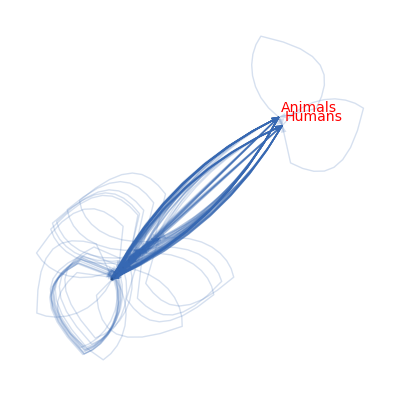

```mathematica
g[gen]=Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

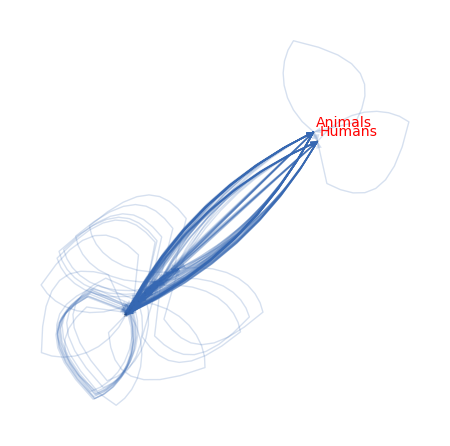

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 2010

```mathematica
gen=2010
```

2010

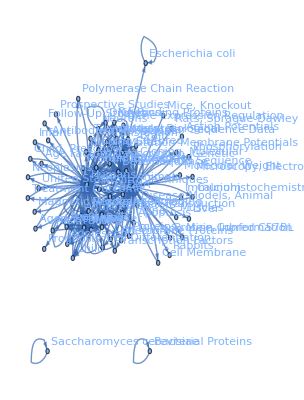

```mathematica
Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Female,Male,Adult,Mice,Middle Aged,Rats,Aged,Molecular Sequence Data,Base Sequence,Amino Acid Sequence,Adolescent,Signal Transduction,Cell Line,Neurons,Cells, Cultured,Child,Time Factors,Escherichia coli,Kinetics,Mutation,Brain,RNA, Messenger,Risk Factors,Models, Biological,In Vitro Techniques,Calcium,Mice, Inbred C57BL,DNA,Neoplasms,Transcription, Genetic,Gene Expression Regulation,Microscopy, Electron,Aged, 80 and over,Cell Membrane,Saccharomyces cerevisiae,Cloning, Molecular,United States,Transcription Factors,DNA-Binding Proteins,Bacterial Proteins,Treatment Outcome,Prospective Studies,Protein Binding,Cell Differentiation,Child, Preschool,Magnetic Resonance Imaging,Mice, Knockout,Rats, Sprague-Dawley,Binding Sites,Proteins,Follow-Up Studies,Membrane Proteins,Polymerase Chain Reaction,Rabbits,Disease Models, Animal,Infant,Antibodies, Monoclonal,T-Lymphocytes,Transfection,Apoptosis,Phosphorylation,Cell Division,Molecular Weight,Membrane Potentials,Protein Conformation,Prognosis,Age Factors,Action Potentials,Muscles,Immunohistochemistry,Liver}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Humans->Animals,Animals->Humans,Female->Humans,Humans->Male,Humans->Female,Male->Humans,Humans->Adult,Mice->Animals,Animals->Mice,Adult->Humans,Humans->Middle Aged,Male->Male,Male->Animals,Female->Female,Middle Aged->Humans,Animals->Male,Humans->Mice,Female->Male,Female->Animals,Animals->Rats,Male->Female,Rats->Animals,Mice->Humans,Humans->Aged,Animals->Female,Humans->Molecular Sequence Data,Aged->Humans,Animals->Molecular Sequence Data,Mice->Mice,Molecular Sequence Data->Animals,Female->Adult,Humans->Base Sequence,Male->Adult,Animals->Base Sequence,Animals->Amino Acid Sequence,Humans->Adolescent,Molecular Sequence Data->Humans,Adult->Male,Humans->Amino Acid Sequence,Molecular Sequence Data->Molecular Sequence Data,Adult->Female,Female->Middle Aged,Base Sequence->Base Sequence,Molecular Sequence Data->Base Sequence,Signal Transduction->Animals,Male->Middle Aged,Adolescent->Humans,Adult->Adult,Humans->Cell Line,Animals->Cell Line,Middle Aged->Female,Amino Acid Sequence->Animals,Cell Line->Animals,Base Sequence->Animals,Humans->Rats,Middle Aged->Male,Animals->Neurons,Cells, Cultured->Animals,Rats->Humans,Neurons->Animals,Humans->Child,Rats->Rats,Child->Humans,Molecular Sequence Data->Amino Acid Sequence,Animals->Cells, Cultured,Humans->Time Factors,Animals->Signal Transduction,Cell Line->Humans,Base Sequence->Humans,Escherichia coli->Escherichia coli,Animals->Kinetics,Signal Transduction->Humans,Female->Aged,Amino Acid Sequence->Humans,Animals->Mutation,Mutation->Animals,Humans->Cells, Cultured,Middle Aged->Middle Aged,Male->Aged,Middle Aged->Adult,Humans->Mutation,Humans->Signal Transduction,Base Sequence->Molecular Sequence Data,Amino Acid Sequence->Amino Acid Sequence,Aged->Female,Cells, Cultured->Humans,Amino Acid Sequence->Molecular Sequence Data,Adult->Middle Aged,Humans->Brain,Aged->Male,Time Factors->Humans,Animals->RNA, Messenger,Risk Factors->Humans,Models, Biological->Animals,Mutation->Humans,Humans->Kinetics,Male->Rats,Animals->Time Factors,Time Factors->Animals,Brain->Humans,Animals->In Vitro Techniques,Animals->Calcium,Humans->RNA, Messenger,Female->Mice,RNA, Messenger->Animals,Humans->Risk Factors,Animals->Models, Biological,Animals->Adult,Animals->Brain,Mice, Inbred C57BL->Animals,In Vitro Techniques->Animals,Mutation->Mutation,Animals->DNA,Aged->Middle Aged,Mice->Female,Humans->DNA,Models, Biological->Humans,Calcium->Animals,Amino Acid Sequence->Base Sequence,Middle Aged->Aged,Kinetics->Animals,Humans->Neoplasms,Rats->Male,Female->Adolescent,Male->Mice,Animals->Transcription, Genetic,Gene Expression Regulation->Animals,Mice->Male,Aged->Aged,Animals->Microscopy, Electron,Humans->Models, Biological,Male->Adolescent,Brain->Animals,Animals->Gene Expression Regulation,Aged, 80 and over->Humans,Animals->Cell Membrane,Saccharomyces cerevisiae->Saccharomyces cerevisiae,Animals->Cloning, Molecular,RNA, Messenger->Humans,Animals->Mice, Inbred C57BL,Adult->Animals,Humans->Aged, 80 and over,Humans->United States,Animals->Transcription Factors,Aged->Adult,Base Sequence->Amino Acid Sequence,Animals->DNA-Binding Proteins,Bacterial Proteins->Bacterial Proteins,Mice->Molecular Sequence Data,Treatment Outcome->Humans,Humans->Prospective Studies,Protein Binding->Animals,Humans->Transcription, Genetic,Cell Differentiation->Animals,Adolescent->Female,Humans->Child, Preschool,Adolescent->Male,Humans->Cloning, Molecular,Humans->DNA-Binding Proteins,Adult->Aged,Transcription, Genetic->Animals,Magnetic Resonance Imaging->Humans,Neoplasms->Humans,Animals->Cell Differentiation,Animals->Middle Aged,Mice, Knockout->Animals,Rats, Sprague-Dawley->Animals,Humans->Protein Binding,Protein Binding->Humans,Animals->Binding Sites,Humans->Gene Expression Regulation,Molecular Sequence Data->Mutation,Animals->Proteins,Humans->Follow-Up Studies,Animals->Protein Binding,Mice->Rats,Humans->Transcription Factors,Animals->Membrane Proteins,Child, Preschool->Humans,Humans->Neurons,Gene Expression Regulation->Humans,Humans->Polymerase Chain Reaction,Animals->Rabbits,Molecular Sequence Data->Cloning, Molecular,Mutation->Molecular Sequence Data,Humans->Treatment Outcome,Humans->Binding Sites,Disease Models, Animal->Animals,Transcription Factors->Animals,Mice->Base Sequence,Humans->Magnetic Resonance Imaging,Cell Membrane->Animals,Binding Sites->Animals,Polymerase Chain Reaction->Humans,Signal Transduction->Signal Transduction,Humans->Infant,Humans->Antibodies, Monoclonal,Humans->T-Lymphocytes,DNA->Animals,Animals->Transfection,Kinetics->Humans,Humans->Apoptosis,Signal Transduction->Mice,Humans->Transfection,Humans->In Vitro Techniques,Apoptosis->Humans,Mutation->Base Sequence,Phosphorylation->Animals,Animals->Cell Division,Animals->Molecular Weight,Animals->Membrane Potentials,Apoptosis->Animals,Animals->Protein Conformation,Humans->Prognosis,Mice->Cell Line,Disease Models, Animal->Humans,Female->Child,Mice->Amino Acid Sequence,Transcription, Genetic->Humans,Humans->Proteins,Humans->Age Factors,Base Sequence->DNA,Child->Male,Adult->Adolescent,Male->Child,Risk Factors->Female,Neurons->Humans,Animals->Phosphorylation,Molecular Sequence Data->Escherichia coli,Transcription, Genetic->Base Sequence,Action Potentials->Animals,Animals->Muscles,DNA-Binding Proteins->Animals,Adolescent->Adult,Base Sequence->Mutation,Child->Female,Membrane Potentials->Animals,Neurons->Neurons,Female->Rats,Humans->Membrane Proteins,Immunohistochemistry->Animals,Humans->Cell Differentiation,Male->Time Factors,Animals->Liver,Animals->T-Lymphocytes,Membrane Proteins->Animals,Humans->Cell Division,Infant->Humans}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ2CitingCitedMeSHgraph[gen],EdgeWeight]
```

{1785.69,1229.,772.384,748.7,569.144,568.889,565.676,556.536,384.08,353.931,344.961,335.428,315.279,289.318,286.173,275.376,270.254,255.624,250.65,239.259,236.747,234.018,230.737,227.449,226.514,226.237,220.383,197.991,196.234,195.658,190.637,167.92,163.361,161.536,160.914,154.224,151.642,144.242,142.929,141.514,140.854,139.787,139.625,132.025,127.79,127.629,126.627,125.235,125.204,124.826,121.927,119.151,118.294,117.922,116.318,116.143,115.652,115.529,114.487,114.026,109.819,106.294,104.812,104.73,104.659,104.412,104.344,103.052,102.756,102.472,98.4671,97.1152,96.4752,96.2795,94.9523,94.4009,94.0909,94.0877,93.652,93.3139,92.0023,91.992,91.0582,91.0199,89.0311,88.7856,88.5066,87.5044,87.0007,86.9212,86.8698,86.4816,85.9882,85.612,85.0887,83.9325,83.771,83.5321,82.7246,79.4367,79.0662,79.0005,78.5465,77.6608,74.0144,73.7999,73.7058,73.4817,72.8041,72.1826,71.2509,70.5274,70.4934,70.3699,70.2791,69.7243,69.6903,69.3364,69.2922,69.0585,69.0309,69.0098,68.5428,67.7214,67.1107,67.0949,66.9812,66.81,66.2912,65.4477,64.6316,64.5972,64.4166,63.9991,63.3816,63.0452,62.2516,61.9621,61.8219,61.7787,61.7092,61.3927,61.377,61.2652,60.7326,60.16,60.0542,59.8414,59.5667,58.9716,58.7386,58.4244,58.1884,57.9081,57.8808,56.7352,56.5254,56.4112,56.2905,55.9594,55.8766,55.7318,55.4685,55.1827,54.9641,54.7809,53.8204,53.6328,53.5584,53.4063,53.406,53.4045,53.0618,52.6798,52.4391,52.2844,51.8824,51.6306,51.1187,51.0404,50.718,50.7078,50.111,49.7551,49.7174,49.6846,49.4373,49.0124,48.7927,48.7794,48.6361,48.5045,48.3542,48.2113,48.1712,48.1241,48.0182,47.9859,47.5633,47.4873,47.4344,47.1989,46.8132,46.7902,46.6728,46.6622,46.357,46.2745,46.2197,46.1965,45.7939,45.7437,45.7175,45.7104,45.4099,45.2209,45.1897,45.0709,44.7783,44.7099,44.648,44.6142,44.5519,44.4918,44.3614,44.2923,44.2808,44.0854,44.0604,43.8616,43.8229,43.6906,43.6259,43.5982,43.5672,43.5415,43.4813,43.4682,43.3414,43.3012,43.1963,43.104,43.0597,42.9652,42.9335,42.9286,42.5532,42.3666,42.292,42.249}

```mathematica
topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

1785.69 | 772.384 | 565.676 | 568.889 | 384.08 | 250.65 | 315.279 | 115.652 | 226.237 | 197.991 | 161.536 | 140.854 | 144.242 | 91.0199 | 121.927 | 50.7078 | 93.652 | 104.812 | 103.052 | 0 | 83.5321 | 91.0582 | 86.8698 | 74.0144 | 73.4817 | 64.4166 | 46.357 | 0 | 0 | 69.3364 | 67.7214 | 57.8808 | 53.0618 | 0 | 61.2652 | 0 | 0 | 55.9594 | 60.7326 | 51.1187 | 55.8766 | 0 | 49.0124 | 58.1884 | 53.4063 | 42.9652 | 56.4112 | 48.3542 | 0 | 0 | 48.7927 | 44.6142 | 52.2844 | 43.104 | 49.7551 | 0 | 0 | 47.9859 | 47.5633 | 47.4873 | 46.6622 | 46.7902 | 0 | 42.292 | 0 | 0 | 0 | 45.2209 | 44.5519 | 0 | 0 | 0 | 0
748.7 | 1229. | 220.383 | 255.624 | 72.1826 | 344.961 | 53.8204 | 234.018 | 0 | 195.658 | 154.224 | 151.642 | 0 | 102.756 | 119.151 | 114.487 | 104.344 | 0 | 79.4367 | 0 | 96.4752 | 94.0909 | 71.2509 | 85.612 | 0 | 72.8041 | 78.5465 | 77.6608 | 61.3927 | 70.2791 | 0 | 66.81 | 63.0452 | 64.5972 | 0 | 61.9621 | 0 | 61.7787 | 0 | 60.16 | 59.5667 | 0 | 0 | 0 | 51.8824 | 54.7809 | 0 | 0 | 0 | 0 | 53.4045 | 52.4391 | 0 | 51.0404 | 0 | 49.7174 | 0 | 0 | 0 | 42.5532 | 47.1989 | 0 | 43.8616 | 45.7939 | 45.7437 | 45.7175 | 45.4099 | 0 | 0 | 0 | 43.5982 | 0 | 42.9286
569.144 | 236.747 | 275.376 | 239.259 | 163.361 | 73.7999 | 132.025 | 43.1963 | 94.9523 | 0 | 0 | 0 | 67.0949 | 0 | 0 | 0 | 0 | 44.7783 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
556.536 | 286.173 | 230.737 | 289.318 | 160.914 | 66.9812 | 125.235 | 82.7246 | 92.0023 | 0 | 0 | 0 | 63.9991 | 0 | 0 | 0 | 0 | 44.2808 | 42.9335 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
335.428 | 61.377 | 139.625 | 141.514 | 124.826 | 0 | 86.9212 | 0 | 55.7318 | 0 | 0 | 0 | 44.2923 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
226.514 | 353.931 | 69.6903 | 65.4477 | 0 | 190.637 | 0 | 51.6306 | 0 | 58.7386 | 48.5045 | 44.7099 | 0 | 0 | 45.1897 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
270.254 | 0 | 118.294 | 115.529 | 91.992 | 0 | 93.3139 | 0 | 69.0098 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
109.819 | 227.449 | 0 | 67.1107 | 0 | 0 | 0 | 104.73 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
196.234 | 0 | 88.5066 | 86.4816 | 60.0542 | 0 | 69.7243 | 0 | 64.6316 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
142.929 | 167.92 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 139.787 | 127.629 | 104.412 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 43.8229 | 0 | 52.6798 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 49.6846 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
98.4671 | 116.143 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 89.0311 | 127.79 | 59.8414 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 43.4813 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 44.4918 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
94.4009 | 117.922 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 87.0007 | 69.0309 | 88.7856 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
125.204 | 0 | 56.5254 | 56.2905 | 43.5415 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
96.2795 | 126.627 | 0 | 0 | 0 | 46.6728 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 48.0182 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
102.472 | 116.318 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
44.0604 | 106.294 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 43.3012 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
87.5044 | 114.026 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
104.659 | 0 | 43.4682 | 44.3614 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
85.9882 | 79.0662 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 97.1152 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
46.8132 | 68.5428 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
83.771 | 94.0877 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 49.4373 | 46.2197 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 70.3699 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
79.0005 | 63.3816 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
61.7092 | 73.7058 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
85.0887 | 0 | 44.0854 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
69.2922 | 83.9325 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 70.4934 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 69.0585 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 70.5274 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 47.4344 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
54.9641 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
44.648 | 55.4685 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 43.6906 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
50.111 | 66.2912 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
62.2516 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 48.2113 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 61.8219 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 48.6361 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 43.5672 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 58.9716 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
58.4244 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
53.406 | 57.9081 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 56.7352 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
50.718 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
55.1827 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 53.6328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 53.5584 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 48.1712 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 42.3666 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
48.1241 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
45.0709 | 48.7794 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
42.249 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
46.2745 | 45.7104 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 46.1965 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 43.3414 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 43.6259 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 43.0597 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{8162.45,6042.49,1939.73,2041.83,989.715,1154.99,758.392,509.108,565.632,828.865,579.246,457.14,281.561,317.598,218.79,193.656,201.531,192.489,165.054,97.1152,115.356,343.886,142.382,135.415,129.174,153.225,70.4934,69.0585,70.5274,47.4344,54.9641,143.807,116.402,0,62.2516,48.2113,61.8219,0,0,48.6361,43.5672,58.9716,58.4244,0,111.314,56.7352,50.718,55.1827,53.6328,53.5584,48.1712,0,0,42.3666,48.1241,0,93.8503,42.249,0,0,0,91.9848,46.1965,0,0,43.3414,0,0,0,43.6259,0,43.0597,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{6817.38,5597.8,1852.37,1929.83,1100.95,973.703,876.319,631.952,602.565,817.644,778.624,590.245,319.628,241.794,286.267,208.496,197.996,193.871,225.422,140.938,180.007,351.68,158.121,159.626,73.4817,137.221,124.903,77.6608,61.3927,184.107,67.7214,124.691,116.107,64.5972,61.2652,61.9621,61.8219,167.423,60.7326,111.279,115.443,58.9716,49.0124,58.1884,105.289,97.7461,56.4112,48.3542,0,0,102.197,97.0534,52.2844,94.1444,49.7551,49.7174,0,47.9859,47.5633,90.0405,93.8611,46.7902,43.8616,88.0859,45.7437,45.7175,45.4099,45.2209,44.5519,0,43.5982,0,42.9286}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{14979.8,11640.3,3792.1,3971.66,2090.67,2128.7,1634.71,1141.06,1168.2,1646.51,1357.87,1047.38,601.189,559.392,505.057,402.152,399.527,386.36,390.477,238.053,295.363,695.566,300.503,295.041,202.656,290.445,195.397,146.719,131.92,231.542,122.685,268.498,232.509,64.5972,123.517,110.173,123.644,167.423,60.7326,159.915,159.011,117.943,107.437,58.1884,216.603,154.481,107.129,103.537,53.6328,53.5584,150.368,97.0534,52.2844,136.511,97.8792,49.7174,93.8503,90.2349,47.5633,90.0405,93.8611,138.775,90.058,88.0859,45.7437,89.0589,45.4099,45.2209,44.5519,43.6259,43.5982,43.0597,42.9286}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{8162.45,6817.38},{6042.49,5597.8},{1939.73,1852.37},{2041.83,1929.83},{989.715,1100.95},{1154.99,973.703},{758.392,876.319},{509.108,631.952},{565.632,602.565},{828.865,817.644},{579.246,778.624},{457.14,590.245},{281.561,319.628},{317.598,241.794},{218.79,286.267},{193.656,208.496},{201.531,197.996},{192.489,193.871},{165.054,225.422},{97.1152,140.938},{115.356,180.007},{343.886,351.68},{142.382,158.121},{135.415,159.626},{129.174,73.4817},{153.225,137.221},{70.4934,124.903},{69.0585,77.6608},{70.5274,61.3927},{47.4344,184.107},{54.9641,67.7214},{143.807,124.691},{116.402,116.107},{0,64.5972},{62.2516,61.2652},{48.2113,61.9621},{61.8219,61.8219},{0,167.423},{0,60.7326},{48.6361,111.279},{43.5672,115.443},{58.9716,58.9716},{58.4244,49.0124},{0,58.1884},{111.314,105.289},{56.7352,97.7461},{50.718,56.4112},{55.1827,48.3542},{53.6328,0},{53.5584,0},{48.1712,102.197},{0,97.0534},{0,52.2844},{42.3666,94.1444},{48.1241,49.7551},{0,49.7174},{93.8503,0},{42.249,47.9859},{0,47.5633},{0,90.0405},{0,93.8611},{91.9848,46.7902},{46.1965,43.8616},{0,88.0859},{0,45.7437},{43.3414,45.7175},{0,45.4099},{0,45.2209},{0,44.5519},{43.6259,0},{0,43.5982},{43.0597,0},{0,42.9286}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

1063.5

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[2.23211],Animals->Animals→Thickness[1.53625],Humans->Animals→Thickness[0.96548],Animals->Humans→Thickness[0.935874],Female->Humans→Thickness[0.711429],Humans->Male→Thickness[0.711111],Humans->Female→Thickness[0.707095],Male->Humans→Thickness[0.69567],Humans->Adult→Thickness[0.4801],Mice->Animals→Thickness[0.442414],Animals->Mice→Thickness[0.431202],Adult->Humans→Thickness[0.419285],Humans->Middle Aged→Thickness[0.394099],Male->Male→Thickness[0.361648],Male->Animals→Thickness[0.357716],Female->Female→Thickness[0.34422],Middle Aged->Humans→Thickness[0.337817],Animals->Male→Thickness[0.319531],Humans->Mice→Thickness[0.313312],Female->Male→Thickness[0.299074],Female->Animals→Thickness[0.295933],Animals->Rats→Thickness[0.292523],Male->Female→Thickness[0.288421],Rats->Animals→Thickness[0.284311],Mice->Humans→Thickness[0.283142],Humans->Aged→Thickness[0.282796],Animals->Female→Thickness[0.275478],Humans->Molecular Sequence Data→Thickness[0.247489],Aged->Humans→Thickness[0.245292],Animals->Molecular Sequence Data→Thickness[0.244572],Mice->Mice→Thickness[0.238297],Molecular Sequence Data->Animals→Thickness[0.2099],Female->Adult→Thickness[0.204202],Humans->Base Sequence→Thickness[0.201919],Male->Adult→Thickness[0.201142],Animals->Base Sequence→Thickness[0.19278],Animals->Amino Acid Sequence→Thickness[0.189552],Humans->Adolescent→Thickness[0.180302],Molecular Sequence Data->Humans→Thickness[0.178661],Adult->Male→Thickness[0.176893],Humans->Amino Acid Sequence→Thickness[0.176068],Molecular Sequence Data->Molecular Sequence Data→Thickness[0.174734],Adult->Female→Thickness[0.174531],Female->Middle Aged→Thickness[0.165031],Base Sequence->Base Sequence→Thickness[0.159737],Molecular Sequence Data->Base Sequence→Thickness[0.159536],Signal Transduction->Animals→Thickness[0.158284],Male->Middle Aged→Thickness[0.156544],Adolescent->Humans→Thickness[0.156505],Adult->Adult→Thickness[0.156033],Humans->Cell Line→Thickness[0.152408],Animals->Cell Line→Thickness[0.148939],Middle Aged->Female→Thickness[0.147867],Amino Acid Sequence->Animals→Thickness[0.147402],Cell Line->Animals→Thickness[0.145397],Base Sequence->Animals→Thickness[0.145179],Humans->Rats→Thickness[0.144565],Middle Aged->Male→Thickness[0.144411],Animals->Neurons→Thickness[0.143109],Cells, Cultured->Animals→Thickness[0.142533],Rats->Humans→Thickness[0.137274],Neurons->Animals→Thickness[0.132868],Humans->Child→Thickness[0.131015],Rats->Rats→Thickness[0.130912],Child->Humans→Thickness[0.130824],Molecular Sequence Data->Amino Acid Sequence→Thickness[0.130515],Animals->Cells, Cultured→Thickness[0.13043],Humans->Time Factors→Thickness[0.128815],Animals->Signal Transduction→Thickness[0.128445],Cell Line->Humans→Thickness[0.12809],Base Sequence->Humans→Thickness[0.123084],Escherichia coli->Escherichia coli→Thickness[0.121394],Animals->Kinetics→Thickness[0.120594],Signal Transduction->Humans→Thickness[0.120349],Female->Aged→Thickness[0.11869],Amino Acid Sequence->Humans→Thickness[0.118001],Animals->Mutation→Thickness[0.117614],Mutation->Animals→Thickness[0.11761],Humans->Cells, Cultured→Thickness[0.117065],Middle Aged->Middle Aged→Thickness[0.116642],Male->Aged→Thickness[0.115003],Middle Aged->Adult→Thickness[0.11499],Humans->Mutation→Thickness[0.113823],Humans->Signal Transduction→Thickness[0.113775],Base Sequence->Molecular Sequence Data→Thickness[0.111289],Amino Acid Sequence->Amino Acid Sequence→Thickness[0.110982],Aged->Female→Thickness[0.110633],Cells, Cultured->Humans→Thickness[0.109381],Amino Acid Sequence->Molecular Sequence Data→Thickness[0.108751],Adult->Middle Aged→Thickness[0.108652],Humans->Brain→Thickness[0.108587],Aged->Male→Thickness[0.108102],Time Factors->Humans→Thickness[0.107485],Animals->RNA, Messenger→Thickness[0.107015],Risk Factors->Humans→Thickness[0.106361],Models, Biological->Animals→Thickness[0.104916],Mutation->Humans→Thickness[0.104714],Humans->Kinetics→Thickness[0.104415],Male->Rats→Thickness[0.103406],Animals->Time Factors→Thickness[0.0992959],Time Factors->Animals→Thickness[0.0988328],Brain->Humans→Thickness[0.0987506],Animals->In Vitro Techniques→Thickness[0.0981831],Animals->Calcium→Thickness[0.097076],Humans->RNA, Messenger→Thickness[0.0925179],Female->Mice→Thickness[0.0922499],RNA, Messenger->Animals→Thickness[0.0921323],Humans->Risk Factors→Thickness[0.0918521],Animals->Models, Biological→Thickness[0.0910051],Animals->Adult→Thickness[0.0902282],Animals->Brain→Thickness[0.0890637],Mice, Inbred C57BL->Animals→Thickness[0.0881592],In Vitro Techniques->Animals→Thickness[0.0881167],Mutation->Mutation→Thickness[0.0879624],Animals->DNA→Thickness[0.0878489],Aged->Middle Aged→Thickness[0.0871554],Mice->Female→Thickness[0.0871128],Humans->DNA→Thickness[0.0866705],Models, Biological->Humans→Thickness[0.0866153],Calcium->Animals→Thickness[0.0863231],Amino Acid Sequence->Base Sequence→Thickness[0.0862886],Middle Aged->Aged→Thickness[0.0862623],Kinetics->Animals→Thickness[0.0856785],Humans->Neoplasms→Thickness[0.0846517],Rats->Male→Thickness[0.0838884],Female->Adolescent→Thickness[0.0838686],Male->Mice→Thickness[0.0837265],Animals->Transcription, Genetic→Thickness[0.0835124],Gene Expression Regulation->Animals→Thickness[0.082864],Mice->Male→Thickness[0.0818096],Aged->Aged→Thickness[0.0807895],Animals->Microscopy, Electron→Thickness[0.0807465],Humans->Models, Biological→Thickness[0.0805207],Male->Adolescent→Thickness[0.0799989],Brain->Animals→Thickness[0.079227],Animals->Gene Expression Regulation→Thickness[0.0788065],Aged, 80 and over->Humans→Thickness[0.0778144],Animals->Cell Membrane→Thickness[0.0774526],Saccharomyces cerevisiae->Saccharomyces cerevisiae→Thickness[0.0772774],Animals->Cloning, Molecular→Thickness[0.0772234],RNA, Messenger->Humans→Thickness[0.0771364],Animals->Mice, Inbred C57BL→Thickness[0.0767408],Adult->Animals→Thickness[0.0767213],Humans->Aged, 80 and over→Thickness[0.0765815],Humans->United States→Thickness[0.0759158],Animals->Transcription Factors→Thickness[0.0752],Aged->Adult→Thickness[0.0750677],Base Sequence->Amino Acid Sequence→Thickness[0.0748018],Animals->DNA-Binding Proteins→Thickness[0.0744584],Bacterial Proteins->Bacterial Proteins→Thickness[0.0737145],Mice->Molecular Sequence Data→Thickness[0.0734233],Treatment Outcome->Humans→Thickness[0.0730305],Humans->Prospective Studies→Thickness[0.0727354],Protein Binding->Animals→Thickness[0.0723851],Humans->Transcription, Genetic→Thickness[0.072351],Cell Differentiation->Animals→Thickness[0.0709189],Adolescent->Female→Thickness[0.0706567],Humans->Child, Preschool→Thickness[0.070514],Adolescent->Male→Thickness[0.0703632],Humans->Cloning, Molecular→Thickness[0.0699492],Humans->DNA-Binding Proteins→Thickness[0.0698457],Adult->Aged→Thickness[0.0696648],Transcription, Genetic->Animals→Thickness[0.0693356],Magnetic Resonance Imaging->Humans→Thickness[0.0689784],Neoplasms->Humans→Thickness[0.0687051],Animals->Cell Differentiation→Thickness[0.0684761],Animals->Middle Aged→Thickness[0.0672755],Mice, Knockout->Animals→Thickness[0.067041],Rats, Sprague-Dawley->Animals→Thickness[0.0669481],Humans->Protein Binding→Thickness[0.0667579],Protein Binding->Humans→Thickness[0.0667575],Animals->Binding Sites→Thickness[0.0667556],Humans->Gene Expression Regulation→Thickness[0.0663273],Molecular Sequence Data->Mutation→Thickness[0.0658497],Animals->Proteins→Thickness[0.0655489],Humans->Follow-Up Studies→Thickness[0.0653555],Animals->Protein Binding→Thickness[0.064853],Mice->Rats→Thickness[0.0645383],Humans->Transcription Factors→Thickness[0.0638983],Animals->Membrane Proteins→Thickness[0.0638005],Child, Preschool->Humans→Thickness[0.0633975],Humans->Neurons→Thickness[0.0633847],Gene Expression Regulation->Humans→Thickness[0.0626387],Humans->Polymerase Chain Reaction→Thickness[0.0621939],Animals->Rabbits→Thickness[0.0621467],Molecular Sequence Data->Cloning, Molecular→Thickness[0.0621058],Mutation->Molecular Sequence Data→Thickness[0.0617967],Humans->Treatment Outcome→Thickness[0.0612655],Humans->Binding Sites→Thickness[0.0609909],Disease Models, Animal->Animals→Thickness[0.0609743],Transcription Factors->Animals→Thickness[0.0607951],Mice->Base Sequence→Thickness[0.0606306],Humans->Magnetic Resonance Imaging→Thickness[0.0604428],Cell Membrane->Animals→Thickness[0.0602641],Binding Sites->Animals→Thickness[0.060214],Polymerase Chain Reaction->Humans→Thickness[0.0601552],Signal Transduction->Signal Transduction→Thickness[0.0600227],Humans->Infant→Thickness[0.0599824],Humans->Antibodies, Monoclonal→Thickness[0.0594541],Humans->T-Lymphocytes→Thickness[0.0593592],DNA->Animals→Thickness[0.059293],Animals->Transfection→Thickness[0.0589986],Kinetics->Humans→Thickness[0.0585165],Humans->Apoptosis→Thickness[0.0584877],Signal Transduction->Mice→Thickness[0.058341],Humans->Transfection→Thickness[0.0583278],Humans->In Vitro Techniques→Thickness[0.0579462],Apoptosis->Humans→Thickness[0.0578431],Mutation->Base Sequence→Thickness[0.0577747],Phosphorylation->Animals→Thickness[0.0577456],Animals->Cell Division→Thickness[0.0572424],Animals->Molecular Weight→Thickness[0.0571796],Animals->Membrane Potentials→Thickness[0.0571469],Apoptosis->Animals→Thickness[0.057138],Animals->Protein Conformation→Thickness[0.0567624],Humans->Prognosis→Thickness[0.0565261],Mice->Cell Line→Thickness[0.0564871],Disease Models, Animal->Humans→Thickness[0.0563386],Female->Child→Thickness[0.0559728],Mice->Amino Acid Sequence→Thickness[0.0558874],Transcription, Genetic->Humans→Thickness[0.05581],Humans->Proteins→Thickness[0.0557678],Humans->Age Factors→Thickness[0.0556898],Base Sequence->DNA→Thickness[0.0556147],Child->Male→Thickness[0.0554517],Adult->Adolescent→Thickness[0.0553653],Male->Child→Thickness[0.055351],Risk Factors->Female→Thickness[0.0551067],Neurons->Humans→Thickness[0.0550755],Animals->Phosphorylation→Thickness[0.0548269],Molecular Sequence Data->Escherichia coli→Thickness[0.0547786],Transcription, Genetic->Base Sequence→Thickness[0.0546132],Action Potentials->Animals→Thickness[0.0545324],Animals->Muscles→Thickness[0.0544978],DNA-Binding Proteins->Animals→Thickness[0.054459],Adolescent->Adult→Thickness[0.0544269],Base Sequence->Mutation→Thickness[0.0543517],Child->Female→Thickness[0.0543352],Membrane Potentials->Animals→Thickness[0.0541768],Neurons->Neurons→Thickness[0.0541265],Female->Rats→Thickness[0.0539954],Humans->Membrane Proteins→Thickness[0.05388],Immunohistochemistry->Animals→Thickness[0.0538246],Humans->Cell Differentiation→Thickness[0.0537065],Male->Time Factors→Thickness[0.0536669],Animals->Liver→Thickness[0.0536608],Animals->T-Lymphocytes→Thickness[0.0531915],Membrane Proteins->Animals→Thickness[0.0529582],Humans->Cell Division→Thickness[0.052865],Infant->Humans→Thickness[0.0528112]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

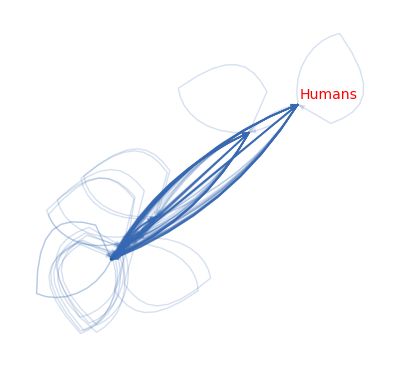

```mathematica
g[gen]=Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

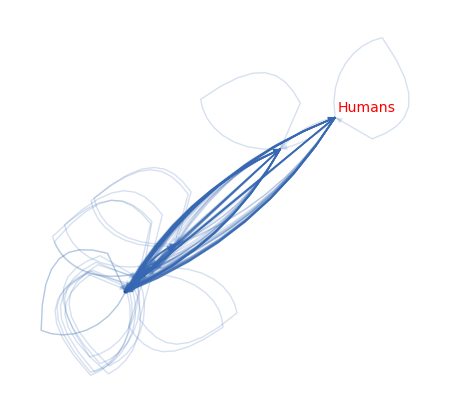

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 2015

```mathematica
gen=2015
```

2015

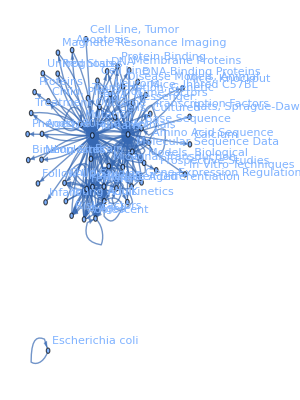

```mathematica
Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Female,Male,Adult,Mice,Middle Aged,Aged,Rats,Molecular Sequence Data,Adolescent,Signal Transduction,Amino Acid Sequence,Base Sequence,Child,Risk Factors,Young Adult,Cell Line,Time Factors,Neurons,Cells, Cultured,Mutation,Brain,Aged, 80 and over,Neoplasms,Mice, Inbred C57BL,Models, Biological,Treatment Outcome,RNA, Messenger,Magnetic Resonance Imaging,United States,Gene Expression Regulation,Cell Line, Tumor,Disease Models, Animal,Prospective Studies,Child, Preschool,Kinetics,Protein Binding,Cell Differentiation,Transcription Factors,Mice, Knockout,Escherichia coli,Follow-Up Studies,DNA-Binding Proteins,Transcription, Genetic,In Vitro Techniques,Prognosis,DNA,Apoptosis,Phenotype,Membrane Proteins,Rats, Sprague-Dawley,Infant,Binding Sites,Proteins,Calcium}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Humans->Animals,Animals->Humans,Female->Humans,Humans->Female,Male->Humans,Humans->Male,Humans->Adult,Adult->Humans,Animals->Mice,Mice->Animals,Humans->Middle Aged,Female->Female,Male->Male,Middle Aged->Humans,Male->Animals,Humans->Mice,Female->Male,Male->Female,Animals->Male,Humans->Aged,Mice->Humans,Female->Animals,Animals->Female,Aged->Humans,Animals->Rats,Female->Adult,Male->Adult,Mice->Mice,Rats->Animals,Humans->Molecular Sequence Data,Adult->Female,Animals->Molecular Sequence Data,Adult->Male,Humans->Adolescent,Female->Middle Aged,Signal Transduction->Animals,Male->Middle Aged,Middle Aged->Female,Adolescent->Humans,Signal Transduction->Humans,Middle Aged->Male,Adult->Adult,Humans->Amino Acid Sequence,Animals->Signal Transduction,Humans->Signal Transduction,Animals->Amino Acid Sequence,Humans->Base Sequence,Molecular Sequence Data->Animals,Female->Aged,Humans->Child,Animals->Base Sequence,Humans->Rats,Risk Factors->Humans,Young Adult->Humans,Male->Aged,Humans->Cell Line,Humans->Time Factors,Humans->Risk Factors,Animals->Neurons,Middle Aged->Middle Aged,Animals->Cells, Cultured,Aged->Female,Molecular Sequence Data->Humans,Humans->Mutation,Child->Humans,Humans->Cells, Cultured,Aged->Male,Middle Aged->Adult,Rats->Humans,Humans->Brain,Neurons->Animals,Animals->Cell Line,Brain->Humans,Cells, Cultured->Animals,Adult->Middle Aged,Cell Line->Animals,Animals->Mutation,Cell Line->Humans,Humans->Aged, 80 and over,Humans->Neoplasms,Molecular Sequence Data->Molecular Sequence Data,Mice, Inbred C57BL->Animals,Humans->Models, Biological,Time Factors->Humans,Mutation->Humans,Treatment Outcome->Humans,Cells, Cultured->Humans,Middle Aged->Aged,Aged->Middle Aged,Neoplasms->Humans,Female->Adolescent,Amino Acid Sequence->Animals,Aged, 80 and over->Humans,Aged->Aged,Models, Biological->Animals,Animals->Adult,Humans->Treatment Outcome,Rats->Rats,Animals->Models, Biological,Female->Mice,Male->Adolescent,Base Sequence->Animals,Animals->RNA, Messenger,Mutation->Animals,Humans->RNA, Messenger,Male->Mice,Animals->Time Factors,Humans->Magnetic Resonance Imaging,Animals->Mice, Inbred C57BL,Humans->United States,Magnetic Resonance Imaging->Humans,Gene Expression Regulation->Animals,Models, Biological->Humans,Mice->Male,Amino Acid Sequence->Humans,Animals->Brain,Cell Line, Tumor->Humans,Male->Rats,Mice->Female,Brain->Animals,Molecular Sequence Data->Base Sequence,Adolescent->Female,Disease Models, Animal->Animals,Base Sequence->Humans,Humans->Prospective Studies,Animals->Gene Expression Regulation,Adult->Animals,Base Sequence->Base Sequence,Adolescent->Male,Disease Models, Animal->Humans,Aged->Adult,Humans->Child, Preschool,Animals->Kinetics,Molecular Sequence Data->Amino Acid Sequence,Humans->Neurons,Humans->Gene Expression Regulation,Animals->Middle Aged,Time Factors->Animals,Humans->Protein Binding,Signal Transduction->Signal Transduction,Signal Transduction->Mice,Animals->Cell Differentiation,Gene Expression Regulation->Humans,Cell Differentiation->Animals,Animals->Transcription Factors,Adult->Aged,Risk Factors->Female,RNA, Messenger->Animals,Mice, Knockout->Animals,Protein Binding->Humans,Animals->Mice, Knockout,Escherichia coli->Escherichia coli,Humans->Transcription Factors,Protein Binding->Animals,Humans->Follow-Up Studies,Humans->Kinetics,Humans->DNA-Binding Proteins,Animals->Transcription, Genetic,Mice, Inbred C57BL->Humans,Risk Factors->Male,Female->Child,Female->Risk Factors,Humans->Transcription, Genetic,Animals->In Vitro Techniques,RNA, Messenger->Humans,Amino Acid Sequence->Molecular Sequence Data,Mutation->Mutation,Humans->Prognosis,Humans->Cell Differentiation,Humans->DNA,Amino Acid Sequence->Amino Acid Sequence,Rats->Male,Humans->Mice, Inbred C57BL,Young Adult->Female,Child, Preschool->Humans,Male->Child,Animals->Protein Binding,Apoptosis->Humans,Humans->Phenotype,Animals->DNA-Binding Proteins,Base Sequence->Molecular Sequence Data,Prognosis->Humans,Humans->Apoptosis,Animals->Membrane Proteins,Adolescent->Adult,Rats, Sprague-Dawley->Animals,Young Adult->Male,Animals->DNA,Humans->Infant,Adult->Adolescent,Humans->Membrane Proteins,Male->Risk Factors,Male->Brain,United States->Humans,Middle Aged->Animals,Humans->Binding Sites,Child->Female,Mice->Molecular Sequence Data,Humans->Proteins,Animals->Calcium,Mice->Signal Transduction}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ2CitingCitedMeSHgraph[gen],EdgeWeight]
```

{3845.41,2293.99,1728.69,1637.82,1331.54,1298.73,1292.39,1263.95,806.453,727.302,704.186,688.407,687.479,667.487,663.002,609.737,584.664,579.912,563.487,554.63,520.965,518.721,509.541,493.429,456.163,447.996,394.427,384.228,362.895,362.147,351.84,348.353,331.12,330.173,313.226,313.107,312.118,308.91,294.466,286.423,283.719,274.516,272.277,270.899,256.391,252.307,251.2,251.082,241.584,234.001,233.669,232.707,232.603,228.95,226.214,225.999,225.51,219.831,215.763,215.41,215.29,214.83,214.673,214.562,213.495,211.076,210.49,206.731,206.069,203.482,200.696,198.559,197.726,197.511,194.914,192.827,190.61,185.609,181.47,180.986,178.717,175.387,174.706,167.312,166.762,166.362,165.964,165.071,164.235,162.81,162.336,161.882,161.461,161.165,160.444,159.661,158.266,157.674,156.792,153.973,153.709,153.565,153.26,152.794,151.69,151.3,150.139,149.42,148.613,147.235,146.891,146.76,143.797,143.767,143.72,143.356,143.021,142.56,142.019,141.845,141.17,141.007,140.006,138.37,138.231,137.298,135.601,134.074,133.386,133.053,131.412,131.057,129.469,129.269,128.856,127.989,126.823,126.507,125.764,125.091,124.984,124.274,123.687,123.437,123.255,123.12,122.96,122.888,121.862,121.21,117.633,117.484,117.383,117.093,116.663,116.316,114.571,113.981,113.628,112.822,112.647,112.518,112.257,112.174,111.86,111.83,111.112,110.964,109.412,109.327,108.632,108.091,107.911,107.724,107.677,107.657,107.371,107.308,106.218,106.058,105.569,104.958,104.168,103.521,101.875,101.864,101.644,101.168,100.912,100.832,100.508,100.33,99.5367,99.3733,98.6705,98.1255,98.0884,97.9082,97.7163,97.7124,96.8606,96.3167,96.3081}

```mathematica
topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

3845.41 | 1728.69 | 1298.73 | 1263.95 | 806.453 | 579.912 | 687.479 | 518.721 | 228.95 | 348.353 | 313.107 | 251.2 | 256.391 | 241.584 | 232.707 | 215.41 | 0 | 219.831 | 215.763 | 126.823 | 206.731 | 211.076 | 198.559 | 178.717 | 175.387 | 107.677 | 166.762 | 156.792 | 150.139 | 147.235 | 146.76 | 126.507 | 0 | 0 | 135.601 | 129.269 | 113.981 | 124.984 | 108.632 | 116.663 | 0 | 0 | 114.571 | 113.628 | 111.86 | 0 | 109.327 | 108.091 | 101.875 | 105.569 | 99.5367 | 0 | 100.508 | 97.9082 | 96.8606 | 0
1637.82 | 2293.99 | 456.163 | 520.965 | 157.674 | 704.186 | 125.764 | 0 | 394.427 | 330.173 | 0 | 252.307 | 251.082 | 232.603 | 0 | 0 | 0 | 197.511 | 148.613 | 215.29 | 214.673 | 181.47 | 142.56 | 0 | 0 | 146.891 | 153.709 | 0 | 151.69 | 0 | 0 | 134.074 | 0 | 0 | 0 | 0 | 128.856 | 106.218 | 123.437 | 122.96 | 117.383 | 0 | 0 | 104.958 | 112.822 | 111.83 | 0 | 100.832 | 0 | 0 | 101.864 | 0 | 0 | 0 | 0 | 96.3167
1331.54 | 493.429 | 667.487 | 563.487 | 384.228 | 153.565 | 312.118 | 233.669 | 0 | 0 | 161.461 | 0 | 0 | 0 | 112.257 | 112.174 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1292.39 | 584.664 | 554.63 | 663.002 | 362.895 | 149.42 | 294.466 | 225.51 | 141.845 | 0 | 153.26 | 0 | 0 | 0 | 107.308 | 99.3733 | 0 | 0 | 0 | 0 | 0 | 0 | 98.6705 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
727.302 | 133.386 | 331.12 | 313.226 | 270.899 | 0 | 190.61 | 122.888 | 0 | 0 | 100.33 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
509.541 | 688.407 | 141.17 | 143.356 | 0 | 362.147 | 0 | 0 | 0 | 97.7124 | 0 | 96.3081 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
609.737 | 98.0884 | 286.423 | 272.277 | 203.482 | 0 | 214.83 | 162.81 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
447.996 | 0 | 214.562 | 206.069 | 129.469 | 0 | 162.336 | 159.661 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
200.696 | 351.84 | 0 | 107.724 | 0 | 0 | 0 | 0 | 153.973 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
213.495 | 234.001 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 174.706 | 0 | 0 | 127.989 | 140.006 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
283.719 | 0 | 138.37 | 131.412 | 101.644 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
274.516 | 308.91 | 0 | 0 | 0 | 123.687 | 0 | 0 | 0 | 0 | 0 | 124.274 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
143.021 | 161.165 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 110.964 | 0 | 0 | 107.911 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
137.298 | 152.794 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 104.168 | 0 | 0 | 0 | 133.053 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
210.49 | 0 | 97.7163 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
226.214 | 0 | 121.862 | 112.518 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
225.999 | 0 | 107.657 | 100.912 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
180.986 | 185.609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
166.362 | 125.091 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 197.726 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
164.235 | 192.827 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
165.964 | 151.3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 109.412 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
194.914 | 141.007 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
160.444 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
161.882 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
112.647 | 167.312 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
143.72 | 158.266 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
165.071 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
111.112 | 121.21 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
143.797 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
98.1255 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
123.255 | 143.767 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
142.019 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
131.057 | 138.231 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
107.371 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
117.484 | 116.316 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 123.12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 117.633 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 117.093 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
103.521 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
106.058 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 101.168 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{17240.7,10271.1,4525.42,4727.44,2189.76,2038.64,1847.65,1320.09,814.234,890.197,655.145,831.387,523.061,527.312,308.206,460.594,434.569,366.595,291.454,197.726,357.061,426.676,335.921,160.444,161.882,279.959,301.986,165.071,232.323,143.797,98.1255,267.022,142.019,269.288,0,107.371,0,233.8,123.12,0,117.633,117.093,0,0,0,0,103.521,0,106.058,0,0,101.168,0,0,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{15117.2,9409.95,4415.89,4398.9,2416.74,2072.92,1987.6,1423.26,919.195,1166.08,728.159,724.088,743.372,747.246,452.271,426.958,0,417.343,364.376,342.114,421.403,501.957,439.79,178.717,175.387,254.569,320.471,156.792,301.829,147.235,146.76,260.581,0,0,135.601,129.269,242.837,231.201,232.07,239.623,117.383,117.093,114.571,218.586,224.682,111.83,109.327,208.923,101.875,105.569,201.401,0,100.508,97.9082,96.8606,96.3167}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{32357.9,19681.1,8941.3,9126.34,4606.51,4111.56,3835.25,2743.35,1733.43,2056.27,1383.3,1555.48,1266.43,1274.56,760.478,887.552,434.569,783.938,655.83,539.84,778.465,928.633,775.711,339.162,337.269,534.528,622.457,321.863,534.152,291.032,244.886,527.604,142.019,269.288,135.601,236.64,242.837,465.002,355.19,239.623,235.016,234.187,114.571,218.586,224.682,111.83,212.848,208.923,207.933,105.569,201.401,101.168,100.508,97.9082,96.8606,96.3167}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{17240.7,15117.2},{10271.1,9409.95},{4525.42,4415.89},{4727.44,4398.9},{2189.76,2416.74},{2038.64,2072.92},{1847.65,1987.6},{1320.09,1423.26},{814.234,919.195},{890.197,1166.08},{655.145,728.159},{831.387,724.088},{523.061,743.372},{527.312,747.246},{308.206,452.271},{460.594,426.958},{434.569,0},{366.595,417.343},{291.454,364.376},{197.726,342.114},{357.061,421.403},{426.676,501.957},{335.921,439.79},{160.444,178.717},{161.882,175.387},{279.959,254.569},{301.986,320.471},{165.071,156.792},{232.323,301.829},{143.797,147.235},{98.1255,146.76},{267.022,260.581},{142.019,0},{269.288,0},{0,135.601},{107.371,129.269},{0,242.837},{233.8,231.201},{123.12,232.07},{0,239.623},{117.633,117.383},{117.093,117.093},{0,114.571},{0,218.586},{0,224.682},{0,111.83},{103.521,109.327},{0,208.923},{106.058,101.875},{0,105.569},{0,201.401},{101.168,0},{0,100.508},{0,97.9082},{0,96.8606},{0,96.3167}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

2292.97

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[4.80676],Animals->Animals→Thickness[2.86749],Humans->Animals→Thickness[2.16087],Animals->Humans→Thickness[2.04727],Female->Humans→Thickness[1.66442],Humans->Female→Thickness[1.62341],Male->Humans→Thickness[1.61549],Humans->Male→Thickness[1.57994],Humans->Adult→Thickness[1.00807],Adult->Humans→Thickness[0.909127],Animals->Mice→Thickness[0.880232],Mice->Animals→Thickness[0.860509],Humans->Middle Aged→Thickness[0.859348],Female->Female→Thickness[0.834359],Male->Male→Thickness[0.828752],Middle Aged->Humans→Thickness[0.762171],Male->Animals→Thickness[0.73083],Humans->Mice→Thickness[0.72489],Female->Male→Thickness[0.704359],Male->Female→Thickness[0.693287],Animals->Male→Thickness[0.651206],Humans->Aged→Thickness[0.648402],Mice->Humans→Thickness[0.636926],Female->Animals→Thickness[0.616786],Animals->Female→Thickness[0.570204],Aged->Humans→Thickness[0.559995],Animals->Rats→Thickness[0.493034],Female->Adult→Thickness[0.480285],Male->Adult→Thickness[0.453619],Mice->Mice→Thickness[0.452684],Rats->Animals→Thickness[0.439801],Humans->Molecular Sequence Data→Thickness[0.435441],Adult->Female→Thickness[0.4139],Animals->Molecular Sequence Data→Thickness[0.412717],Adult->Male→Thickness[0.391533],Humans->Adolescent→Thickness[0.391384],Female->Middle Aged→Thickness[0.390148],Signal Transduction->Animals→Thickness[0.386137],Male->Middle Aged→Thickness[0.368083],Middle Aged->Female→Thickness[0.358028],Adolescent->Humans→Thickness[0.354649],Signal Transduction->Humans→Thickness[0.343146],Middle Aged->Male→Thickness[0.340346],Adult->Adult→Thickness[0.338623],Humans->Amino Acid Sequence→Thickness[0.320489],Animals->Signal Transduction→Thickness[0.315384],Humans->Signal Transduction→Thickness[0.313999],Animals->Amino Acid Sequence→Thickness[0.313852],Humans->Base Sequence→Thickness[0.30198],Molecular Sequence Data->Animals→Thickness[0.292501],Female->Aged→Thickness[0.292087],Humans->Child→Thickness[0.290884],Animals->Base Sequence→Thickness[0.290753],Humans->Rats→Thickness[0.286187],Risk Factors->Humans→Thickness[0.282768],Young Adult->Humans→Thickness[0.282499],Male->Aged→Thickness[0.281888],Humans->Cell Line→Thickness[0.274789],Humans->Time Factors→Thickness[0.269703],Humans->Risk Factors→Thickness[0.269263],Animals->Neurons→Thickness[0.269113],Middle Aged->Middle Aged→Thickness[0.268537],Animals->Cells, Cultured→Thickness[0.268341],Aged->Female→Thickness[0.268202],Molecular Sequence Data->Humans→Thickness[0.266869],Humans->Mutation→Thickness[0.263844],Child->Humans→Thickness[0.263113],Humans->Cells, Cultured→Thickness[0.258414],Aged->Male→Thickness[0.257586],Middle Aged->Adult→Thickness[0.254352],Rats->Humans→Thickness[0.25087],Humans->Brain→Thickness[0.248199],Neurons->Animals→Thickness[0.247158],Animals->Cell Line→Thickness[0.246889],Brain->Humans→Thickness[0.243643],Cells, Cultured->Animals→Thickness[0.241033],Adult->Middle Aged→Thickness[0.238263],Cell Line->Animals→Thickness[0.232011],Animals->Mutation→Thickness[0.226837],Cell Line->Humans→Thickness[0.226233],Humans->Aged, 80 and over→Thickness[0.223397],Humans->Neoplasms→Thickness[0.219234],Molecular Sequence Data->Molecular Sequence Data→Thickness[0.218382],Mice, Inbred C57BL->Animals→Thickness[0.20914],Humans->Models, Biological→Thickness[0.208452],Time Factors->Humans→Thickness[0.207953],Mutation->Humans→Thickness[0.207455],Treatment Outcome->Humans→Thickness[0.206339],Cells, Cultured->Humans→Thickness[0.205293],Middle Aged->Aged→Thickness[0.203512],Aged->Middle Aged→Thickness[0.202919],Neoplasms->Humans→Thickness[0.202353],Female->Adolescent→Thickness[0.201826],Amino Acid Sequence->Animals→Thickness[0.201456],Aged, 80 and over->Humans→Thickness[0.200555],Aged->Aged→Thickness[0.199576],Models, Biological->Animals→Thickness[0.197833],Animals->Adult→Thickness[0.197093],Humans->Treatment Outcome→Thickness[0.19599],Rats->Rats→Thickness[0.192466],Animals->Models, Biological→Thickness[0.192136],Female->Mice→Thickness[0.191957],Male->Adolescent→Thickness[0.191576],Base Sequence->Animals→Thickness[0.190993],Animals->RNA, Messenger→Thickness[0.189612],Mutation->Animals→Thickness[0.189126],Humans->RNA, Messenger→Thickness[0.187674],Male->Mice→Thickness[0.186775],Animals->Time Factors→Thickness[0.185766],Humans->Magnetic Resonance Imaging→Thickness[0.184044],Animals->Mice, Inbred C57BL→Thickness[0.183614],Humans->United States→Thickness[0.18345],Magnetic Resonance Imaging->Humans→Thickness[0.179746],Gene Expression Regulation->Animals→Thickness[0.179709],Models, Biological->Humans→Thickness[0.17965],Mice->Male→Thickness[0.179195],Amino Acid Sequence->Humans→Thickness[0.178776],Animals->Brain→Thickness[0.178201],Cell Line, Tumor->Humans→Thickness[0.177524],Male->Rats→Thickness[0.177306],Mice->Female→Thickness[0.176462],Brain->Animals→Thickness[0.176258],Molecular Sequence Data->Base Sequence→Thickness[0.175008],Adolescent->Female→Thickness[0.172962],Disease Models, Animal->Animals→Thickness[0.172789],Base Sequence->Humans→Thickness[0.171622],Humans->Prospective Studies→Thickness[0.169501],Animals->Gene Expression Regulation→Thickness[0.167592],Adult->Animals→Thickness[0.166732],Base Sequence->Base Sequence→Thickness[0.166316],Adolescent->Male→Thickness[0.164265],Disease Models, Animal->Humans→Thickness[0.163821],Aged->Adult→Thickness[0.161837],Humans->Child, Preschool→Thickness[0.161586],Animals->Kinetics→Thickness[0.16107],Molecular Sequence Data->Amino Acid Sequence→Thickness[0.159986],Humans->Neurons→Thickness[0.158529],Humans->Gene Expression Regulation→Thickness[0.158134],Animals->Middle Aged→Thickness[0.157204],Time Factors->Animals→Thickness[0.156364],Humans->Protein Binding→Thickness[0.15623],Signal Transduction->Signal Transduction→Thickness[0.155342],Signal Transduction->Mice→Thickness[0.154609],Animals->Cell Differentiation→Thickness[0.154297],Gene Expression Regulation->Humans→Thickness[0.154069],Cell Differentiation->Animals→Thickness[0.1539],Animals->Transcription Factors→Thickness[0.1537],Adult->Aged→Thickness[0.15361],Risk Factors->Female→Thickness[0.152328],RNA, Messenger->Animals→Thickness[0.151513],Mice, Knockout->Animals→Thickness[0.147041],Protein Binding->Humans→Thickness[0.146855],Animals->Mice, Knockout→Thickness[0.146729],Escherichia coli->Escherichia coli→Thickness[0.146367],Humans->Transcription Factors→Thickness[0.145829],Protein Binding->Animals→Thickness[0.145395],Humans->Follow-Up Studies→Thickness[0.143213],Humans->Kinetics→Thickness[0.142476],Humans->DNA-Binding Proteins→Thickness[0.142035],Animals->Transcription, Genetic→Thickness[0.141027],Mice, Inbred C57BL->Humans→Thickness[0.140809],Risk Factors->Male→Thickness[0.140647],Female->Child→Thickness[0.140321],Female->Risk Factors→Thickness[0.140218],Humans->Transcription, Genetic→Thickness[0.139825],Animals->In Vitro Techniques→Thickness[0.139788],RNA, Messenger->Humans→Thickness[0.138891],Amino Acid Sequence->Molecular Sequence Data→Thickness[0.138705],Mutation->Mutation→Thickness[0.136764],Humans->Prognosis→Thickness[0.136659],Humans->Cell Differentiation→Thickness[0.13579],Humans->DNA→Thickness[0.135113],Amino Acid Sequence->Amino Acid Sequence→Thickness[0.134888],Rats->Male→Thickness[0.134656],Humans->Mice, Inbred C57BL→Thickness[0.134597],Young Adult->Female→Thickness[0.134571],Child, Preschool->Humans→Thickness[0.134214],Male->Child→Thickness[0.134134],Animals->Protein Binding→Thickness[0.132772],Apoptosis->Humans→Thickness[0.132573],Humans->Phenotype→Thickness[0.131961],Animals->DNA-Binding Proteins→Thickness[0.131198],Base Sequence->Molecular Sequence Data→Thickness[0.13021],Prognosis->Humans→Thickness[0.129401],Humans->Apoptosis→Thickness[0.127344],Animals->Membrane Proteins→Thickness[0.12733],Adolescent->Adult→Thickness[0.127055],Rats, Sprague-Dawley->Animals→Thickness[0.12646],Young Adult->Male→Thickness[0.12614],Animals->DNA→Thickness[0.12604],Humans->Infant→Thickness[0.125635],Adult->Adolescent→Thickness[0.125413],Humans->Membrane Proteins→Thickness[0.124421],Male->Risk Factors→Thickness[0.124217],Male->Brain→Thickness[0.123338],United States->Humans→Thickness[0.122657],Middle Aged->Animals→Thickness[0.122611],Humans->Binding Sites→Thickness[0.122385],Child->Female→Thickness[0.122145],Mice->Molecular Sequence Data→Thickness[0.12214],Humans->Proteins→Thickness[0.121076],Animals->Calcium→Thickness[0.120396],Mice->Signal Transduction→Thickness[0.120385]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

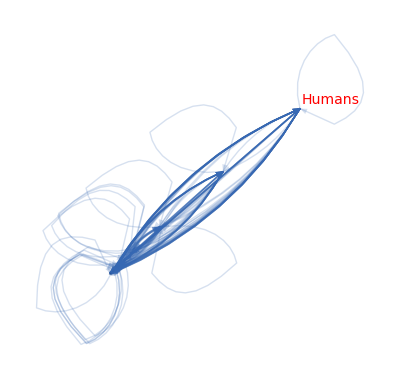

```mathematica
g[gen]=Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

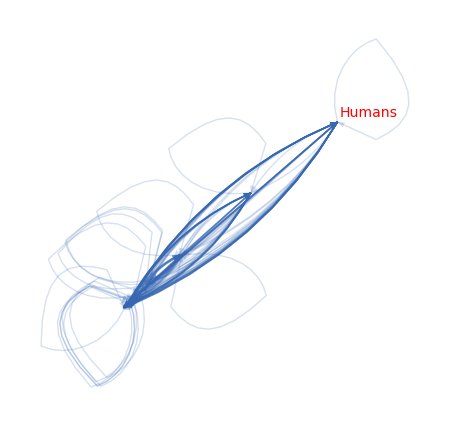

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 2020

```mathematica
gen=2020
```

2020

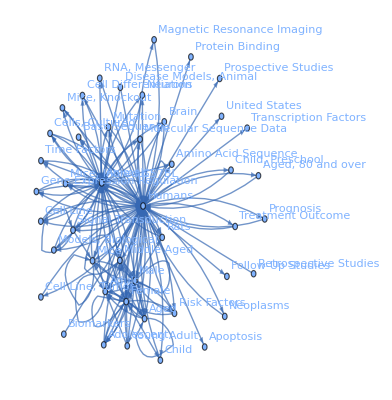

```mathematica
Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Female,Male,Adult,Middle Aged,Mice,Aged,Adolescent,Signal Transduction,Rats,Young Adult,Molecular Sequence Data,Risk Factors,Child,Brain,Amino Acid Sequence,Neoplasms,Mutation,Aged, 80 and over,Cell Line,Time Factors,Cells, Cultured,Neurons,Treatment Outcome,Models, Biological,Base Sequence,Mice, Inbred C57BL,United States,Magnetic Resonance Imaging,Cell Line, Tumor,Disease Models, Animal,RNA, Messenger,Prospective Studies,Child, Preschool,Gene Expression Regulation,Mice, Knockout,Protein Binding,Biomarkers,Cell Differentiation,Prognosis,Retrospective Studies,Follow-Up Studies,Apoptosis,Transcription Factors}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ2CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Humans->Animals,Animals->Humans,Female->Humans,Male->Humans,Humans->Female,Humans->Male,Humans->Adult,Adult->Humans,Humans->Middle Aged,Female->Female,Animals->Mice,Male->Male,Middle Aged->Humans,Humans->Mice,Mice->Animals,Female->Male,Male->Female,Male->Animals,Humans->Aged,Animals->Male,Aged->Humans,Mice->Humans,Female->Animals,Animals->Female,Female->Adult,Male->Adult,Adult->Female,Female->Middle Aged,Adult->Male,Mice->Mice,Humans->Adolescent,Male->Middle Aged,Middle Aged->Female,Adolescent->Humans,Signal Transduction->Animals,Animals->Rats,Young Adult->Humans,Middle Aged->Male,Signal Transduction->Humans,Humans->Signal Transduction,Adult->Adult,Humans->Molecular Sequence Data,Animals->Signal Transduction,Humans->Risk Factors,Rats->Animals,Animals->Molecular Sequence Data,Female->Aged,Male->Aged,Risk Factors->Humans,Aged->Female,Middle Aged->Middle Aged,Humans->Child,Child->Humans,Humans->Brain,Aged->Male,Middle Aged->Adult,Brain->Humans,Humans->Amino Acid Sequence,Humans->Neoplasms,Humans->Rats,Humans->Mutation,Adult->Middle Aged,Humans->Aged, 80 and over,Humans->Cell Line,Humans->Time Factors,Neoplasms->Humans,Humans->Cells, Cultured,Animals->Amino Acid Sequence,Animals->Neurons,Treatment Outcome->Humans,Humans->Treatment Outcome,Aged, 80 and over->Humans,Humans->Models, Biological,Humans->Base Sequence,Animals->Cells, Cultured,Middle Aged->Aged,Aged->Middle Aged,Mice, Inbred C57BL->Animals,Neurons->Animals,Rats->Humans,Aged->Aged,Humans->United States,Animals->Cell Line,Female->Adolescent,Animals->Mice, Inbred C57BL,Male->Mice,Animals->Models, Biological,Animals->Base Sequence,Humans->Magnetic Resonance Imaging,Male->Adolescent,Magnetic Resonance Imaging->Humans,Mutation->Humans,Cell Line, Tumor->Humans,Disease Models, Animal->Animals,Female->Mice,Cells, Cultured->Animals,Disease Models, Animal->Humans,Animals->Mutation,Animals->Adult,Animals->Brain,Adolescent->Female,Cell Line->Humans,Adolescent->Male,Mice->Male,Cell Line->Animals,Brain->Animals,Humans->RNA, Messenger,Humans->Prospective Studies,Time Factors->Humans,Young Adult->Female,Cells, Cultured->Humans,Models, Biological->Animals,Humans->Mice, Inbred C57BL,Aged->Adult,Humans->Child, Preschool,Young Adult->Male,Adult->Animals,Mice->Female,Molecular Sequence Data->Animals,Female->Risk Factors,Gene Expression Regulation->Animals,Animals->Mice, Knockout,Animals->RNA, Messenger,Adult->Aged,Models, Biological->Humans,Mutation->Animals,Signal Transduction->Mice,Animals->Middle Aged,Mice, Inbred C57BL->Humans,Humans->Protein Binding,Biomarkers->Humans,Risk Factors->Female,Humans->Gene Expression Regulation,Animals->Cell Differentiation,Humans->Young Adult,Gene Expression Regulation->Humans,Signal Transduction->Signal Transduction,Prognosis->Humans,Humans->Neurons,Humans->Prognosis,Retrospective Studies->Humans,Humans->Cell Differentiation,Molecular Sequence Data->Humans,Animals->Time Factors,Male->Risk Factors,Cell Differentiation->Animals,Humans->Follow-Up Studies,Humans->Apoptosis,Animals->Gene Expression Regulation,Humans->Cell Line, Tumor,Female->Child,Young Adult->Adult,Risk Factors->Male,Humans->Transcription Factors,Child, Preschool->Humans,Humans->Mice, Knockout,Mice, Knockout->Animals,Male->Rats}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ2CitingCitedMeSHgraph[gen],EdgeWeight]
```

{7315.39,3740.22,3162.49,2946.54,2593.63,2489.15,2481.52,2413.12,1500.24,1380.53,1314.84,1280.02,1246.88,1223.56,1186.82,1123.37,1094.36,1082.47,1061.49,997.693,985.575,904.864,872.402,866.317,865.907,800.129,727.504,673.843,634.388,602.151,591.472,583.268,575.09,570.791,550.869,540.222,537.686,534.456,529.98,525.199,507.923,502.67,499.72,496.201,480.242,460.944,454.74,451.548,448.098,433.501,421.53,409.548,406.153,402.594,399.61,398.107,396.993,379.691,378.478,368.422,365.854,363.523,360.181,359.265,356.965,353.841,349.061,345.53,334.31,334.065,329.845,329.629,328.256,316.937,315.41,313.945,312.398,308.721,308.543,307.63,306.663,301.799,299.614,298.555,298.421,297.499,295.527,289.512,287.536,286.79,282.221,280.66,279.499,279.477,277.912,276.793,276.223,276.12,274.106,270.139,269.429,265.666,264.058,259.254,254.136,252.072,251.754,251.146,250.774,250.51,250.086,249.432,248.455,241.859,239.856,239.315,237.03,236.832,236.673,236.077,235.75,235.471,232.523,231.052,229.667,227.216,227.091,226.467,225.584,225.22,223.969,223.471,222.444,217.937,217.834,217.513,217.105,217.016,216.682,216.315,212.561,212.444,211.955,211.739,210.008,209.487,208.407,207.951,207.933,207.037,206.97,204.114,201.812,201.149,199.449,196.711,195.744,195.342,194.216,193.354}

```mathematica
topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

7315.39 | 3162.49 | 2481.52 | 2413.12 | 1500.24 | 1314.84 | 1123.37 | 985.575 | 575.09 | 502.67 | 363.523 | 217.105 | 496.201 | 460.944 | 402.594 | 398.107 | 368.422 | 365.854 | 360.181 | 356.965 | 353.841 | 349.061 | 334.31 | 212.561 | 328.256 | 315.41 | 313.945 | 239.856 | 298.555 | 282.221 | 204.114 | 0 | 250.774 | 250.51 | 237.03 | 217.834 | 195.342 | 223.471 | 0 | 211.739 | 212.444 | 0 | 207.933 | 207.037 | 196.711
2946.54 | 3740.22 | 800.129 | 904.864 | 269.429 | 225.22 | 1246.88 | 0 | 0 | 480.242 | 534.456 | 0 | 451.548 | 0 | 0 | 265.666 | 334.065 | 0 | 270.139 | 0 | 298.421 | 209.487 | 312.398 | 329.845 | 0 | 287.536 | 286.79 | 295.527 | 0 | 0 | 0 | 0 | 229.667 | 0 | 0 | 206.97 | 231.052 | 0 | 0 | 217.513 | 0 | 0 | 0 | 0 | 0
2593.63 | 865.907 | 1280.02 | 1082.47 | 727.504 | 602.151 | 276.223 | 448.098 | 297.499 | 0 | 0 | 0 | 0 | 235.471 | 201.812 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2489.15 | 997.693 | 1061.49 | 1223.56 | 673.843 | 570.791 | 289.512 | 433.501 | 280.66 | 0 | 193.354 | 0 | 0 | 208.407 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1380.53 | 236.673 | 634.388 | 591.472 | 499.72 | 359.265 | 0 | 227.216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1186.82 | 0 | 550.869 | 525.199 | 379.691 | 406.153 | 0 | 308.721 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
866.317 | 1094.36 | 236.077 | 252.072 | 0 | 0 | 583.268 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
872.402 | 0 | 409.548 | 396.993 | 239.315 | 308.543 | 0 | 299.614 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
540.222 | 0 | 264.058 | 254.136 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
507.923 | 537.686 | 0 | 0 | 0 | 0 | 225.584 | 0 | 0 | 216.682 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
301.799 | 454.74 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
529.98 | 0 | 249.432 | 236.832 | 201.149 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
210.008 | 235.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
421.53 | 0 | 217.937 | 199.449 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
399.61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
378.478 | 251.146 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
345.53 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
279.477 | 226.467 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
316.937 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
259.254 | 251.754 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
250.086 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
248.455 | 276.12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 306.663 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
329.629 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
227.091 | 241.859 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
223.969 | 307.63 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
279.499 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
277.912 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
274.106 | 276.793 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
195.744 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
217.016 | 232.523 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 194.216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
222.444 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 207.951 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
216.315 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
211.955 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{30807.2,15374.6,8610.79,8421.96,3929.26,3357.45,3032.09,2526.42,1058.42,1487.87,756.539,1217.39,445.758,838.916,399.61,629.624,0,345.53,505.945,316.937,511.008,250.086,524.575,306.663,329.629,468.95,0,531.599,0,279.499,277.912,550.899,0,0,195.744,449.54,194.216,0,222.444,207.951,216.315,211.955,0,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ2CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{27315.8,14098.6,8185.46,8080.16,4490.89,3786.97,3744.84,2702.73,1153.25,1199.59,1091.33,217.105,947.749,904.822,604.406,663.773,702.487,365.854,630.32,356.965,652.263,558.549,646.708,542.406,328.256,602.946,600.735,535.383,298.555,282.221,204.114,0,480.441,250.51,237.03,424.804,426.394,223.471,0,429.252,212.444,0,207.933,207.037,196.711}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{58122.9,29473.2,16796.2,16502.1,8420.15,7144.42,6776.93,5229.14,2211.67,2687.47,1847.87,1434.5,1393.51,1743.74,1004.02,1293.4,702.487,711.384,1136.26,673.902,1163.27,808.635,1171.28,849.069,657.885,1071.9,600.735,1066.98,298.555,561.72,482.027,550.899,480.441,250.51,432.774,874.343,620.61,223.471,222.444,637.203,428.759,211.955,207.933,207.037,196.711}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{30807.2,27315.8},{15374.6,14098.6},{8610.79,8185.46},{8421.96,8080.16},{3929.26,4490.89},{3357.45,3786.97},{3032.09,3744.84},{2526.42,2702.73},{1058.42,1153.25},{1487.87,1199.59},{756.539,1091.33},{1217.39,217.105},{445.758,947.749},{838.916,904.822},{399.61,604.406},{629.624,663.773},{0,702.487},{345.53,365.854},{505.945,630.32},{316.937,356.965},{511.008,652.263},{250.086,558.549},{524.575,646.708},{306.663,542.406},{329.629,328.256},{468.95,602.946},{0,600.735},{531.599,535.383},{0,298.555},{279.499,282.221},{277.912,204.114},{550.899,0},{0,480.441},{0,250.51},{195.744,237.03},{449.54,424.804},{194.216,426.394},{0,223.471},{222.444,0},{207.951,429.252},{216.315,212.444},{211.955,0},{0,207.933},{0,207.037},{0,196.711}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

4117.32

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[9.14423],Animals->Animals→Thickness[4.67527],Humans->Animals→Thickness[3.95312],Animals->Humans→Thickness[3.68318],Female->Humans→Thickness[3.24204],Male->Humans→Thickness[3.11144],Humans->Female→Thickness[3.1019],Humans->Male→Thickness[3.01639],Humans->Adult→Thickness[1.8753],Adult->Humans→Thickness[1.72566],Humans->Middle Aged→Thickness[1.64355],Female->Female→Thickness[1.60002],Animals->Mice→Thickness[1.5586],Male->Male→Thickness[1.52945],Middle Aged->Humans→Thickness[1.48352],Humans->Mice→Thickness[1.40422],Mice->Animals→Thickness[1.36795],Female->Male→Thickness[1.35309],Male->Female→Thickness[1.32686],Male->Animals→Thickness[1.24712],Humans->Aged→Thickness[1.23197],Animals->Male→Thickness[1.13108],Aged->Humans→Thickness[1.0905],Mice->Humans→Thickness[1.0829],Female->Animals→Thickness[1.08238],Animals->Female→Thickness[1.00016],Female->Adult→Thickness[0.90938],Male->Adult→Thickness[0.842304],Adult->Female→Thickness[0.792985],Female->Middle Aged→Thickness[0.752689],Adult->Male→Thickness[0.73934],Mice->Mice→Thickness[0.729085],Humans->Adolescent→Thickness[0.718862],Male->Middle Aged→Thickness[0.713489],Middle Aged->Female→Thickness[0.688586],Adolescent->Humans→Thickness[0.675277],Signal Transduction->Animals→Thickness[0.672107],Animals->Rats→Thickness[0.66807],Young Adult->Humans→Thickness[0.662475],Middle Aged->Male→Thickness[0.656499],Signal Transduction->Humans→Thickness[0.634904],Humans->Signal Transduction→Thickness[0.628338],Adult->Adult→Thickness[0.62465],Humans->Molecular Sequence Data→Thickness[0.620252],Animals->Signal Transduction→Thickness[0.600303],Humans->Risk Factors→Thickness[0.576181],Rats->Animals→Thickness[0.568424],Animals->Molecular Sequence Data→Thickness[0.564435],Female->Aged→Thickness[0.560122],Male->Aged→Thickness[0.541876],Risk Factors->Humans→Thickness[0.526913],Aged->Female→Thickness[0.511935],Middle Aged->Middle Aged→Thickness[0.507692],Humans->Child→Thickness[0.503242],Child->Humans→Thickness[0.499513],Humans->Brain→Thickness[0.497634],Aged->Male→Thickness[0.496241],Middle Aged->Adult→Thickness[0.474614],Brain->Humans→Thickness[0.473098],Humans->Amino Acid Sequence→Thickness[0.460528],Humans->Neoplasms→Thickness[0.457317],Humans->Rats→Thickness[0.454404],Humans->Mutation→Thickness[0.450227],Adult->Middle Aged→Thickness[0.449081],Humans->Aged, 80 and over→Thickness[0.446206],Humans->Cell Line→Thickness[0.442302],Humans->Time Factors→Thickness[0.436326],Neoplasms->Humans→Thickness[0.431913],Humans->Cells, Cultured→Thickness[0.417887],Animals->Amino Acid Sequence→Thickness[0.417581],Animals->Neurons→Thickness[0.412306],Treatment Outcome->Humans→Thickness[0.412036],Humans->Treatment Outcome→Thickness[0.41032],Aged, 80 and over->Humans→Thickness[0.396171],Humans->Models, Biological→Thickness[0.394262],Humans->Base Sequence→Thickness[0.392431],Animals->Cells, Cultured→Thickness[0.390497],Middle Aged->Aged→Thickness[0.385901],Aged->Middle Aged→Thickness[0.385679],Mice, Inbred C57BL->Animals→Thickness[0.384538],Neurons->Animals→Thickness[0.383329],Rats->Humans→Thickness[0.377249],Aged->Aged→Thickness[0.374517],Humans->United States→Thickness[0.373194],Animals->Cell Line→Thickness[0.373027],Female->Adolescent→Thickness[0.371874],Animals->Mice, Inbred C57BL→Thickness[0.369409],Male->Mice→Thickness[0.36189],Animals->Models, Biological→Thickness[0.35942],Animals->Base Sequence→Thickness[0.358487],Humans->Magnetic Resonance Imaging→Thickness[0.352777],Male->Adolescent→Thickness[0.350826],Magnetic Resonance Imaging->Humans→Thickness[0.349374],Mutation->Humans→Thickness[0.349347],Cell Line, Tumor->Humans→Thickness[0.347391],Disease Models, Animal->Animals→Thickness[0.345991],Female->Mice→Thickness[0.345279],Cells, Cultured->Animals→Thickness[0.34515],Disease Models, Animal->Humans→Thickness[0.342632],Animals->Mutation→Thickness[0.337673],Animals->Adult→Thickness[0.336786],Animals->Brain→Thickness[0.332083],Adolescent->Female→Thickness[0.330073],Cell Line->Humans→Thickness[0.324067],Adolescent->Male→Thickness[0.31767],Mice->Male→Thickness[0.31509],Cell Line->Animals→Thickness[0.314693],Brain->Animals→Thickness[0.313932],Humans->RNA, Messenger→Thickness[0.313468],Humans->Prospective Studies→Thickness[0.313138],Time Factors->Humans→Thickness[0.312608],Young Adult->Female→Thickness[0.31179],Cells, Cultured->Humans→Thickness[0.310569],Models, Biological->Animals→Thickness[0.302324],Humans->Mice, Inbred C57BL→Thickness[0.299819],Aged->Adult→Thickness[0.299144],Humans->Child, Preschool→Thickness[0.296288],Young Adult->Male→Thickness[0.296041],Adult->Animals→Thickness[0.295842],Mice->Female→Thickness[0.295096],Molecular Sequence Data->Animals→Thickness[0.294687],Female->Risk Factors→Thickness[0.294339],Gene Expression Regulation->Animals→Thickness[0.290654],Animals->Mice, Knockout→Thickness[0.288815],Animals->RNA, Messenger→Thickness[0.287084],Adult->Aged→Thickness[0.28402],Models, Biological->Humans→Thickness[0.283863],Mutation->Animals→Thickness[0.283084],Signal Transduction->Mice→Thickness[0.28198],Animals->Middle Aged→Thickness[0.281526],Mice, Inbred C57BL->Humans→Thickness[0.279961],Humans->Protein Binding→Thickness[0.279339],Biomarkers->Humans→Thickness[0.278055],Risk Factors->Female→Thickness[0.272422],Humans->Gene Expression Regulation→Thickness[0.272292],Animals->Cell Differentiation→Thickness[0.271891],Humans->Young Adult→Thickness[0.271381],Gene Expression Regulation->Humans→Thickness[0.27127],Signal Transduction->Signal Transduction→Thickness[0.270852],Prognosis->Humans→Thickness[0.270394],Humans->Neurons→Thickness[0.265701],Humans->Prognosis→Thickness[0.265555],Retrospective Studies->Humans→Thickness[0.264944],Humans->Cell Differentiation→Thickness[0.264673],Molecular Sequence Data->Humans→Thickness[0.26251],Animals->Time Factors→Thickness[0.261859],Male->Risk Factors→Thickness[0.260508],Cell Differentiation->Animals→Thickness[0.259939],Humans->Follow-Up Studies→Thickness[0.259916],Humans->Apoptosis→Thickness[0.258796],Animals->Gene Expression Regulation→Thickness[0.258712],Humans->Cell Line, Tumor→Thickness[0.255143],Female->Child→Thickness[0.252265],Young Adult->Adult→Thickness[0.251437],Risk Factors->Male→Thickness[0.249311],Humans->Transcription Factors→Thickness[0.245889],Child, Preschool->Humans→Thickness[0.24468],Humans->Mice, Knockout→Thickness[0.244177],Mice, Knockout->Animals→Thickness[0.24277],Male->Rats→Thickness[0.241692]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

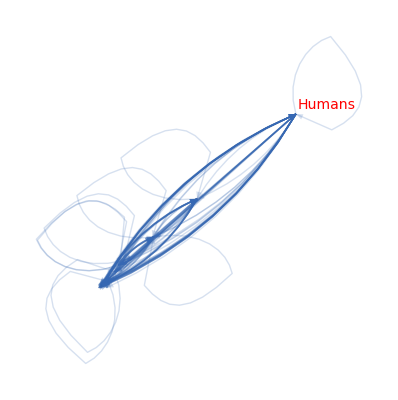

```mathematica
g[gen]=Graph[topofQ2CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

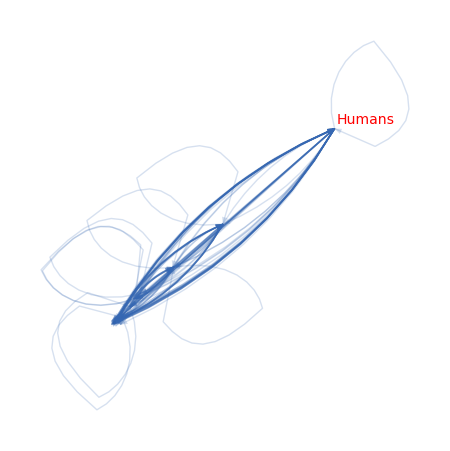

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### tabular 1955~2020

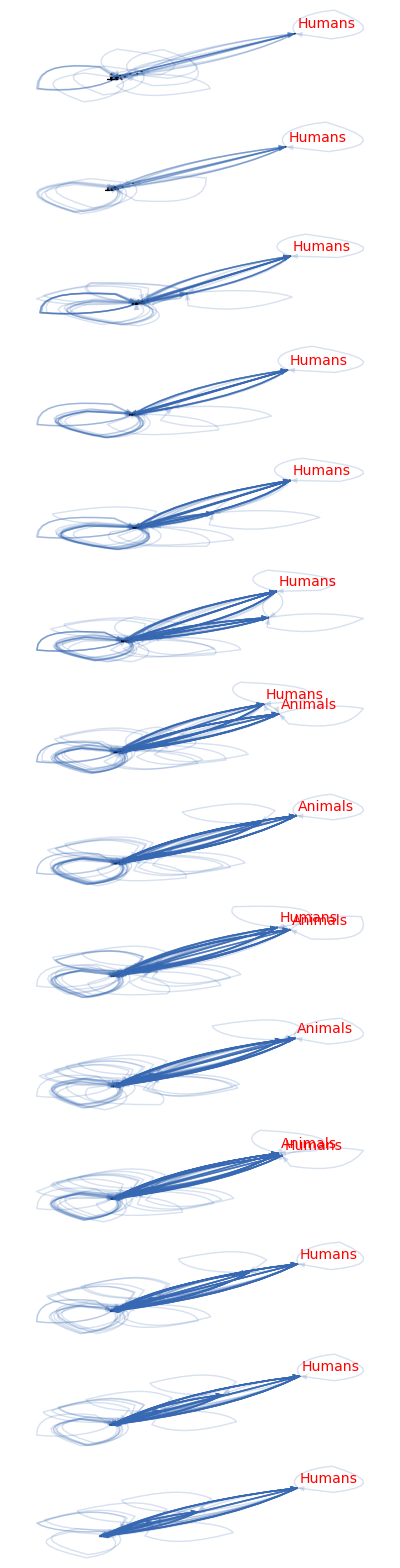

```mathematica
Table[Show[g[n],ovl,ImageSize->500],{n,1955,2020,5}]//TableForm
```

## Q3論文のMeSHの上位(生産5%)を見る（可視化）

2 回目以降の評価はここから始める。

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"<>"Q3CitingCitedMeSHwlink.save"];
```

#### 準備

```mathematica
Do[acm[n]=Accumulate[Map[#[[1]]&,Q3CitingCitedMeSHwlink[n]]];
prd[n]=(Map[#[[1]]&,Q3CitingCitedMeSHwlink[n]]//Total)*(0.05)//Round;
near[n]=Nearest[acm[n]->"Index",prd[n]][[1]];
topofQ3CitingCitedMeSH[n]=Q3CitingCitedMeSHwlink[n][[1;;near[n]]],{n,1950,2020,5}]
```

```mathematica
wlinkToGraph[l_]:=Module[{g,w},
g=Map[#[[2]]&,l];
w=Map[DirectedEdge[#[[2,1]],#[[2,2]]]->#[[1]]&,l];
Graph[g,EdgeWeight->w]
]
```

```mathematica
Do[topofQ3CitingCitedMeSHgraph[n]=(topofQ3CitingCitedMeSH[n]//wlinkToGraph),{n,1950,2020,5}]
```

#### 1950

```mathematica
gen=1950
```

1950

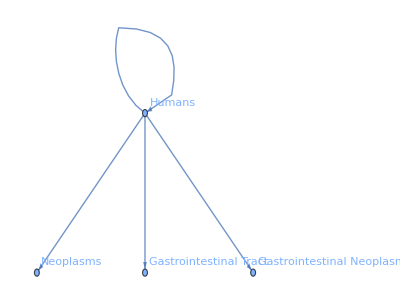

```mathematica
Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans,Neoplasms,Gastrointestinal Tract,Gastrointestinal Neoplasms}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Humans->Neoplasms,Humans->Gastrointestinal Tract,Humans->Gastrointestinal Neoplasms}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ3CitingCitedMeSHgraph[gen],EdgeWeight]
```

{0.381548,0.1875,0.1875,0.1875}

```mathematica
topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

0.381548 | 0.1875 | 0.1875 | 0.1875
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{0.944048,0,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{0.381548,0.1875,0.1875,0.1875}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{1.3256,0.1875,0.1875,0.1875}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{0.944048,0.381548},{0,0.1875},{0,0.1875},{0,0.1875}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

0.101824

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.000476935],Humans->Neoplasms→Thickness[0.000234375],Humans->Gastrointestinal Tract→Thickness[0.000234375],Humans->Gastrointestinal Neoplasms→Thickness[0.000234375]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

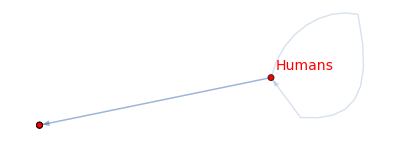

```mathematica
g[gen]=Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

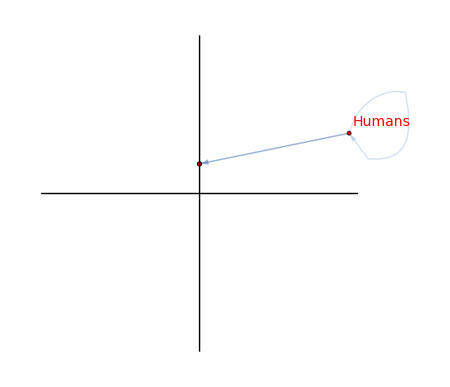

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1955

```mathematica
gen=1955
```

1955

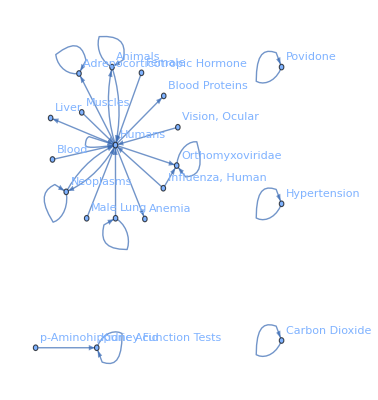

```mathematica
Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Orthomyxoviridae,Neoplasms,Lung,Kidney Function Tests,Vision, Ocular,Povidone,p-Aminohippuric Acid,Hypertension,Influenza, Human,Muscles,Female,Adrenocorticotropic Hormone,Anemia,Blood,Carbon Dioxide,Liver,Male,Blood Proteins}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Humans,Animals->Animals,Humans->Animals,Humans->Orthomyxoviridae,Neoplasms->Humans,Humans->Neoplasms,Orthomyxoviridae->Orthomyxoviridae,Lung->Humans,Kidney Function Tests->Kidney Function Tests,Vision, Ocular->Humans,Povidone->Povidone,p-Aminohippuric Acid->Kidney Function Tests,Neoplasms->Neoplasms,Hypertension->Hypertension,Influenza, Human->Orthomyxoviridae,Muscles->Humans,Female->Humans,Humans->Adrenocorticotropic Hormone,Humans->Anemia,Blood->Humans,Lung->Lung,Carbon Dioxide->Carbon Dioxide,Influenza, Human->Humans,Adrenocorticotropic Hormone->Adrenocorticotropic Hormone,Humans->Liver,Male->Humans,Humans->Blood Proteins}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ3CitingCitedMeSHgraph[gen],EdgeWeight]
```

{36.4292,3.55518,3.26817,2.49375,2.43806,2.28786,2.18106,2.0556,1.81455,1.61667,1.53929,1.46667,1.45,1.43526,1.4238,1.40111,1.39721,1.3639,1.31151,1.29348,1.27407,1.26984,1.26263,1.25877,1.24101,1.23944,1.23288,1.155}

```mathematica
topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

36.4292 | 2.49375 | 2.43806 | 2.18106 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.31151 | 1.29348 | 0 | 0 | 1.23944 | 0 | 1.155
3.55518 | 3.26817 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2.0556 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.28786 | 0 | 0 | 1.43526 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.81455 | 0 | 0 | 0 | 1.26984 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.61667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.53929 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.46667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.4238 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.25877 | 0 | 1.40111 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.39721 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.3639 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.24101 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.27407 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.26263 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.23288 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{48.5415,6.82335,2.0556,3.72312,3.08439,1.61667,1.53929,1.46667,1.45,1.4238,2.65988,1.39721,1.3639,1.24101,0,1.27407,1.26263,0,1.23288,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{52.1529,5.76192,5.89477,3.61632,1.26984,3.06667,0,1.46667,0,1.4238,0,0,0,2.55251,1.29348,0,1.26263,1.23944,0,1.155}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{100.694,12.5853,7.95036,7.33944,4.35423,4.68333,1.53929,2.93333,1.45,2.84759,2.65988,1.39721,1.3639,3.79352,1.29348,1.27407,2.52526,1.23944,1.23288,1.155}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{48.5415,52.1529},{6.82335,5.76192},{2.0556,5.89477},{3.72312,3.61632},{3.08439,1.26984},{1.61667,3.06667},{1.53929,0},{1.46667,1.46667},{1.45,0},{1.4238,1.4238},{2.65988,0},{1.39721,0},{1.3639,0},{1.24101,2.55251},{0,1.29348},{1.27407,0},{1.26263,1.26263},{0,1.23944},{1.23288,0},{0,1.155}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

7.12475

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.0455365],Animals->Humans→Thickness[0.00444398],Animals->Animals→Thickness[0.00408521],Humans->Animals→Thickness[0.00311719],Humans->Orthomyxoviridae→Thickness[0.00304758],Neoplasms->Humans→Thickness[0.00285982],Humans->Neoplasms→Thickness[0.00272633],Orthomyxoviridae->Orthomyxoviridae→Thickness[0.00256949],Lung->Humans→Thickness[0.00226819],Kidney Function Tests->Kidney Function Tests→Thickness[0.00202083],Vision, Ocular->Humans→Thickness[0.00192411],Povidone->Povidone→Thickness[0.00183333],p-Aminohippuric Acid->Kidney Function Tests→Thickness[0.0018125],Neoplasms->Neoplasms→Thickness[0.00179407],Hypertension->Hypertension→Thickness[0.00177975],Influenza, Human->Orthomyxoviridae→Thickness[0.00175139],Muscles->Humans→Thickness[0.00174651],Female->Humans→Thickness[0.00170488],Humans->Adrenocorticotropic Hormone→Thickness[0.00163938],Humans->Anemia→Thickness[0.00161685],Blood->Humans→Thickness[0.00159258],Lung->Lung→Thickness[0.0015873],Carbon Dioxide->Carbon Dioxide→Thickness[0.00157829],Influenza, Human->Humans→Thickness[0.00157346],Adrenocorticotropic Hormone->Adrenocorticotropic Hormone→Thickness[0.00155126],Humans->Liver→Thickness[0.00154931],Male->Humans→Thickness[0.0015411],Humans->Blood Proteins→Thickness[0.00144375]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

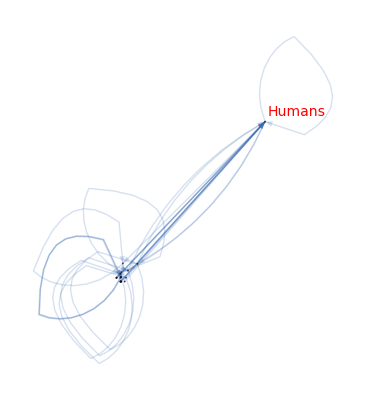

```mathematica
g[gen]=Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

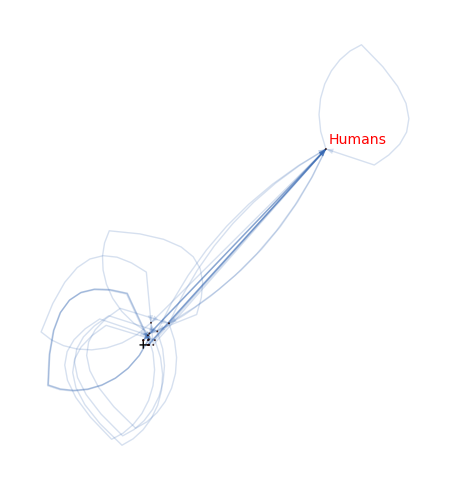

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

#### 1960

```mathematica
gen=1960
```

1960

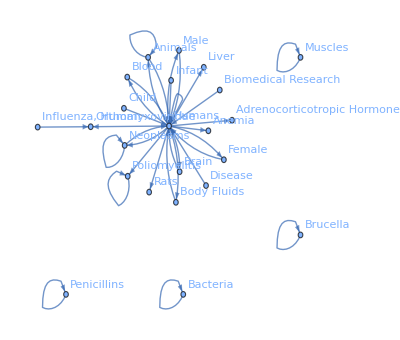

```mathematica
Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Neoplasms,Poliomyelitis,Child,Infant,Female,Orthomyxoviridae,Disease,Anemia,Brain,Liver,Penicillins,Adrenocorticotropic Hormone,Influenza, Human,Body Fluids,Blood,Bacteria,Rats,Muscles,Biomedical Research,Brucella,Male}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Humans->Animals,Animals->Animals,Animals->Humans,Humans->Neoplasms,Neoplasms->Humans,Poliomyelitis->Poliomyelitis,Child->Humans,Infant->Humans,Female->Humans,Humans->Orthomyxoviridae,Disease->Humans,Humans->Female,Neoplasms->Neoplasms,Humans->Anemia,Humans->Brain,Humans->Liver,Penicillins->Penicillins,Brain->Humans,Humans->Adrenocorticotropic Hormone,Influenza, Human->Orthomyxoviridae,Humans->Body Fluids,Body Fluids->Humans,Humans->Blood,Bacteria->Bacteria,Humans->Rats,Muscles->Muscles,Biomedical Research->Humans,Brucella->Brucella,Male->Humans,Humans->Male,Blood->Humans,Humans->Poliomyelitis}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ3CitingCitedMeSHgraph[gen],EdgeWeight]
```

{102.81,9.86101,9.15939,9.02839,4.90663,4.43019,4.22907,3.8086,3.73898,3.56934,3.54778,3.53972,3.3105,3.2606,2.88299,2.83367,2.7562,2.64401,2.64006,2.54395,2.52036,2.51906,2.48707,2.41798,2.33474,2.24474,2.23841,2.22282,2.2,2.14962,2.14489,2.13879,2.13034}

```mathematica
topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

102.81 | 9.86101 | 4.90663 | 2.13034 | 0 | 0 | 3.3105 | 3.54778 | 0 | 2.88299 | 2.83367 | 2.7562 | 0 | 2.54395 | 0 | 2.51906 | 2.41798 | 0 | 2.24474 | 0 | 0 | 0 | 2.14489
9.02839 | 9.15939 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.43019 | 0 | 3.2606 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4.22907 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.8086 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.73898 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.56934 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.53972 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.64006 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.64401 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.52036 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.48707 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.13879 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.33474 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.23841 | 0 | 0 | 0
2.22282 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.2 | 0
2.14962 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{146.91,18.1878,7.69079,4.22907,3.8086,3.73898,3.56934,0,3.53972,0,2.64006,0,2.64401,0,2.52036,2.48707,2.13879,2.33474,0,2.23841,2.22282,2.2,2.14962}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{142.563,19.0204,8.16724,6.35942,0,0,3.3105,6.06814,0,2.88299,2.83367,2.7562,2.64401,2.54395,0,2.51906,2.41798,2.33474,2.24474,2.23841,0,2.2,2.14489}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{289.473,37.2082,15.858,10.5885,3.8086,3.73898,6.87984,6.06814,3.53972,2.88299,5.47373,2.7562,5.28802,2.54395,2.52036,5.00613,4.55677,4.66948,2.24474,4.47683,2.22282,4.4,4.2945}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{146.91,142.563},{18.1878,19.0204},{7.69079,8.16724},{4.22907,6.35942},{3.8086,0},{3.73898,0},{3.56934,3.3105},{0,6.06814},{3.53972,0},{0,2.88299},{2.64006,2.83367},{0,2.7562},{2.64401,2.64401},{0,2.54395},{2.52036,0},{2.48707,2.51906},{2.13879,2.41798},{2.33474,2.33474},{0,2.24474},{2.23841,2.23841},{2.22282,0},{2.2,2.2},{2.14962,2.14489}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

20.4711

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.128512],Humans->Animals→Thickness[0.0123263],Animals->Animals→Thickness[0.0114492],Animals->Humans→Thickness[0.0112855],Humans->Neoplasms→Thickness[0.00613329],Neoplasms->Humans→Thickness[0.00553773],Poliomyelitis->Poliomyelitis→Thickness[0.00528634],Child->Humans→Thickness[0.00476075],Infant->Humans→Thickness[0.00467372],Female->Humans→Thickness[0.00446168],Humans->Orthomyxoviridae→Thickness[0.00443473],Disease->Humans→Thickness[0.00442466],Humans->Female→Thickness[0.00413812],Neoplasms->Neoplasms→Thickness[0.00407576],Humans->Anemia→Thickness[0.00360374],Humans->Brain→Thickness[0.00354208],Humans->Liver→Thickness[0.00344525],Penicillins->Penicillins→Thickness[0.00330501],Brain->Humans→Thickness[0.00330007],Humans->Adrenocorticotropic Hormone→Thickness[0.00317994],Influenza, Human->Orthomyxoviridae→Thickness[0.00315045],Humans->Body Fluids→Thickness[0.00314883],Body Fluids->Humans→Thickness[0.00310883],Humans->Blood→Thickness[0.00302248],Bacteria->Bacteria→Thickness[0.00291843],Humans->Rats→Thickness[0.00280593],Muscles->Muscles→Thickness[0.00279802],Biomedical Research->Humans→Thickness[0.00277853],Brucella->Brucella→Thickness[0.00275],Male->Humans→Thickness[0.00268702],Humans->Male→Thickness[0.00268111],Blood->Humans→Thickness[0.00267348],Humans->Poliomyelitis→Thickness[0.00266293]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

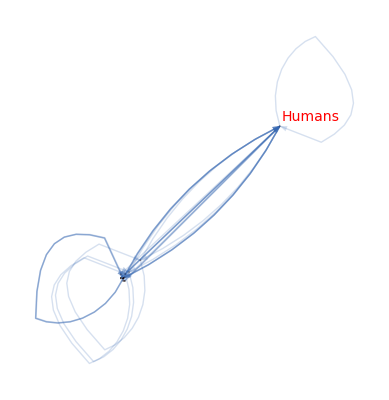

```mathematica
g[gen]=Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 1965

```mathematica
gen=1965
```

1965

```mathematica
Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Neoplasms,Female,Infant,Child,Male,Disease,Brain,Electrophoresis,Hypertension,Syphilis,Adrenocorticotropic Hormone,Blood,Heart,Anemia,Muscles,Research,Pregnancy,Penicillins,Cortisone,Infant, Newborn,Body Fluids}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Humans,Humans->Animals,Animals->Animals,Humans->Neoplasms,Female->Humans,Neoplasms->Humans,Humans->Female,Infant->Humans,Child->Humans,Male->Humans,Disease->Humans,Humans->Brain,Neoplasms->Neoplasms,Brain->Humans,Female->Female,Electrophoresis->Electrophoresis,Hypertension->Hypertension,Humans->Syphilis,Humans->Child,Humans->Adrenocorticotropic Hormone,Humans->Blood,Humans->Male,Hypertension->Humans,Heart->Humans,Blood->Humans,Humans->Infant,Humans->Anemia,Muscles->Humans,Research->Humans,Pregnancy->Humans,Humans->Penicillins,Humans->Cortisone,Syphilis->Syphilis,Infant, Newborn->Humans,Body Fluids->Humans,Humans->Heart}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ3CitingCitedMeSHgraph[gen],EdgeWeight]
```

{180.697,18.3236,17.131,14.4612,11.2348,9.54767,9.03819,8.60033,6.99478,6.84892,6.57046,6.1063,5.99375,5.75894,5.49378,5.4319,5.35863,5.33527,5.07917,4.95646,4.58062,4.56809,4.44887,4.39203,4.37017,4.31415,4.27278,4.23383,4.21728,4.20523,4.10987,4.02225,3.97325,3.82234,3.80171,3.8,3.79888}

```mathematica
topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

180.697 | 17.131 | 11.2348 | 8.60033 | 4.27278 | 4.95646 | 4.44887 | 0 | 5.99375 | 0 | 0 | 5.07917 | 4.58062 | 4.56809 | 3.79888 | 4.23383 | 0 | 0 | 0 | 4.02225 | 3.97325 | 0 | 0
18.3236 | 14.4612 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.03819 | 0 | 5.75894 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.54767 | 0 | 0 | 5.4319 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.99478 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.84892 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.57046 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.1063 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.49378 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.35863 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.39203 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.33527 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.82234 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.31415 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.37017 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.21728 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.20523 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.10987 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.80171 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{267.591,32.7848,14.7971,14.9796,6.99478,6.84892,6.57046,6.1063,5.49378,5.35863,9.7273,3.82234,0,4.31415,4.37017,0,4.21728,4.20523,4.10987,0,0,3.80171,3.8}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{282.831,31.5923,16.9938,14.0322,4.27278,4.95646,4.44887,0,5.99375,5.35863,5.33527,8.90151,4.58062,4.56809,3.79888,4.23383,0,0,0,4.02225,3.97325,0,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{550.422,64.3771,31.7909,29.0118,11.2676,11.8054,11.0193,6.1063,11.4875,10.7173,15.0626,12.7238,4.58062,8.88224,8.16905,4.23383,4.21728,4.20523,4.10987,4.02225,3.97325,3.80171,3.8}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{267.591,282.831},{32.7848,31.5923},{14.7971,16.9938},{14.9796,14.0322},{6.99478,4.27278},{6.84892,4.95646},{6.57046,4.44887},{6.1063,0},{5.49378,5.99375},{5.35863,5.35863},{9.7273,5.33527},{3.82234,8.90151},{0,4.58062},{4.31415,4.56809},{4.37017,3.79888},{0,4.23383},{4.21728,0},{4.20523,0},{4.10987,0},{0,4.02225},{0,3.97325},{3.80171,0},{3.8,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

38.9356

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.225871],Animals->Humans→Thickness[0.0229045],Humans->Animals→Thickness[0.0214138],Animals->Animals→Thickness[0.0180765],Humans->Neoplasms→Thickness[0.0140436],Female->Humans→Thickness[0.0119346],Neoplasms->Humans→Thickness[0.0112977],Humans->Female→Thickness[0.0107504],Infant->Humans→Thickness[0.00874347],Child->Humans→Thickness[0.00856115],Male->Humans→Thickness[0.00821308],Disease->Humans→Thickness[0.00763287],Humans->Brain→Thickness[0.00749219],Neoplasms->Neoplasms→Thickness[0.00719868],Brain->Humans→Thickness[0.00686723],Female->Female→Thickness[0.00678987],Electrophoresis->Electrophoresis→Thickness[0.00669829],Hypertension->Hypertension→Thickness[0.00666909],Humans->Syphilis→Thickness[0.00634896],Humans->Child→Thickness[0.00619558],Humans->Adrenocorticotropic Hormone→Thickness[0.00572577],Humans->Blood→Thickness[0.00571012],Humans->Male→Thickness[0.00556109],Hypertension->Humans→Thickness[0.00549003],Heart->Humans→Thickness[0.00546271],Blood->Humans→Thickness[0.00539268],Humans->Infant→Thickness[0.00534097],Humans->Anemia→Thickness[0.00529229],Muscles->Humans→Thickness[0.0052716],Research->Humans→Thickness[0.00525654],Pregnancy->Humans→Thickness[0.00513733],Humans->Penicillins→Thickness[0.00502781],Humans->Cortisone→Thickness[0.00496656],Syphilis->Syphilis→Thickness[0.00477793],Infant, Newborn->Humans→Thickness[0.00475213],Body Fluids->Humans→Thickness[0.00475],Humans->Heart→Thickness[0.0047486]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 1970

```mathematica
gen=1970
```

1970

```mathematica
Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Female,Male,Neoplasms,Child,Adult,Infant,Blood,Disease,Middle Aged,Medical Records,Research,Rats,Cardiovascular System,Brain,Lung,Heart,Pregnancy,Body Fluids,Aged,Infant, Newborn,Adolescent,Hemoglobins,Liver,Kidney,Skin,Electrocardiography,Erythrocytes,Blood Group Antigens,In Vitro Techniques,Anemia,Mental Disorders}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Humans,Animals->Animals,Female->Humans,Male->Humans,Humans->Animals,Humans->Neoplasms,Child->Humans,Adult->Humans,Infant->Humans,Neoplasms->Humans,Humans->Female,Humans->Blood,Humans->Disease,Middle Aged->Humans,Medical Records->Humans,Research->Humans,Rats->Animals,Humans->Infant,Female->Female,Humans->Cardiovascular System,Humans->Male,Rats->Humans,Humans->Brain,Lung->Humans,Disease->Humans,Humans->Heart,Humans->Child,Neoplasms->Neoplasms,Pregnancy->Humans,Humans->Body Fluids,Animals->Rats,Humans->Lung,Aged->Humans,Infant, Newborn->Humans,Adolescent->Humans,Humans->Hemoglobins,Humans->Liver,Liver->Humans,Kidney->Humans,Humans->Pregnancy,Liver->Liver,Skin->Humans,Brain->Humans,Electrocardiography->Humans,Erythrocytes->Humans,Body Fluids->Humans,Blood Group Antigens->Blood Group Antigens,In Vitro Techniques->Humans,Humans->Anemia,Humans->Mental Disorders,Humans->Kidney,Humans->Erythrocytes,Hemoglobins->Hemoglobins}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ3CitingCitedMeSHgraph[gen],EdgeWeight]
```

{283.514,37.1359,33.1397,26.5946,24.8291,24.5499,14.6383,14.2532,13.7266,12.726,12.2794,11.3746,10.7623,10.5239,9.74513,8.76054,8.22052,8.15938,7.90818,7.87547,7.82357,7.7868,7.67933,7.59792,7.54132,7.43144,7.39825,7.276,7.10184,7.00879,6.89807,6.89539,6.72147,6.29824,6.29608,6.26006,6.25448,6.20831,5.88997,5.85957,5.77191,5.74508,5.57368,5.46542,5.45151,5.28418,5.18711,5.09794,5.07309,5.0451,5.03556,5.01209,4.97965,4.95231}

```mathematica
topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

283.514 | 24.5499 | 11.3746 | 7.7868 | 14.6383 | 7.276 | 0 | 7.90818 | 10.7623 | 10.5239 | 0 | 0 | 0 | 0 | 7.82357 | 7.59792 | 6.72147 | 7.39825 | 5.77191 | 6.89807 | 0 | 0 | 0 | 6.25448 | 6.20831 | 5.01209 | 0 | 0 | 4.97965 | 0 | 0 | 5.0451 | 5.03556
37.1359 | 33.1397 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.89539 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
26.5946 | 0 | 7.87547 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
24.8291 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.2794 | 0 | 0 | 0 | 7.10184 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
14.2532 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13.7266 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.726 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.43144 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.74513 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.76054 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.22052 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.67933 | 8.15938 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.46542 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.54132 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.00879 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.18711 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.29824 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.29608 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.26006 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.95231 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.88997 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.74508 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.85957 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.57368 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.45151 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.28418 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.09794 | 0 | 0 | 0
5.07309 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{453.08,77.171,34.4701,24.8291,19.3812,14.2532,13.7266,12.726,0,7.43144,9.74513,8.76054,8.22052,15.8387,0,5.46542,7.54132,0,7.00879,5.18711,6.29824,6.29608,6.26006,4.95231,11.6351,5.85957,5.57368,5.45151,5.28418,5.09794,5.07309,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{544.085,65.849,19.25,7.7868,21.7402,7.276,0,7.90818,10.7623,10.5239,0,0,0,6.89539,7.82357,7.59792,6.72147,7.39825,5.77191,6.89807,0,0,0,11.2068,11.9534,5.01209,0,0,4.97965,5.09794,0,5.0451,5.03556}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{997.165,143.02,53.7201,32.6159,41.1214,21.5292,13.7266,20.6342,10.7623,17.9553,9.74513,8.76054,8.22052,22.7341,7.82357,13.0633,14.2628,7.39825,12.7807,12.0852,6.29824,6.29608,6.26006,16.1591,23.5884,10.8717,5.57368,5.45151,10.2638,10.1959,5.07309,5.0451,5.03556}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{453.08,544.085},{77.171,65.849},{34.4701,19.25},{24.8291,7.7868},{19.3812,21.7402},{14.2532,7.276},{13.7266,0},{12.726,7.90818},{0,10.7623},{7.43144,10.5239},{9.74513,0},{8.76054,0},{8.22052,0},{15.8387,6.89539},{0,7.82357},{5.46542,7.59792},{7.54132,6.72147},{0,7.39825},{7.00879,5.77191},{5.18711,6.89807},{6.29824,0},{6.29608,0},{6.26006,0},{4.95231,11.2068},{11.6351,11.9534},{5.85957,5.01209},{5.57368,0},{5.45151,0},{5.28418,4.97965},{5.09794,5.09794},{5.07309,0},{0,5.0451},{0,5.03556}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

70.8033

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.354393],Animals->Humans→Thickness[0.0464198],Animals->Animals→Thickness[0.0414247],Female->Humans→Thickness[0.0332433],Male->Humans→Thickness[0.0310364],Humans->Animals→Thickness[0.0306874],Humans->Neoplasms→Thickness[0.0182979],Child->Humans→Thickness[0.0178165],Adult->Humans→Thickness[0.0171582],Infant->Humans→Thickness[0.0159075],Neoplasms->Humans→Thickness[0.0153492],Humans->Female→Thickness[0.0142182],Humans->Blood→Thickness[0.0134528],Humans->Disease→Thickness[0.0131548],Middle Aged->Humans→Thickness[0.0121814],Medical Records->Humans→Thickness[0.0109507],Research->Humans→Thickness[0.0102757],Rats->Animals→Thickness[0.0101992],Humans->Infant→Thickness[0.00988522],Female->Female→Thickness[0.00984434],Humans->Cardiovascular System→Thickness[0.00977946],Humans->Male→Thickness[0.00973351],Rats->Humans→Thickness[0.00959916],Humans->Brain→Thickness[0.00949741],Lung->Humans→Thickness[0.00942665],Disease->Humans→Thickness[0.0092893],Humans->Heart→Thickness[0.00924781],Humans->Child→Thickness[0.009095],Neoplasms->Neoplasms→Thickness[0.00887731],Pregnancy->Humans→Thickness[0.00876099],Humans->Body Fluids→Thickness[0.00862259],Animals->Rats→Thickness[0.00861924],Humans->Lung→Thickness[0.00840183],Aged->Humans→Thickness[0.00787281],Infant, Newborn->Humans→Thickness[0.00787009],Adolescent->Humans→Thickness[0.00782507],Humans->Hemoglobins→Thickness[0.0078181],Humans->Liver→Thickness[0.00776039],Liver->Humans→Thickness[0.00736246],Kidney->Humans→Thickness[0.00732446],Humans->Pregnancy→Thickness[0.00721489],Liver->Liver→Thickness[0.00718135],Skin->Humans→Thickness[0.0069671],Brain->Humans→Thickness[0.00683178],Electrocardiography->Humans→Thickness[0.00681439],Erythrocytes->Humans→Thickness[0.00660523],Body Fluids->Humans→Thickness[0.00648389],Blood Group Antigens->Blood Group Antigens→Thickness[0.00637242],In Vitro Techniques->Humans→Thickness[0.00634136],Humans->Anemia→Thickness[0.00630638],Humans->Mental Disorders→Thickness[0.00629445],Humans->Kidney→Thickness[0.00626511],Humans->Erythrocytes→Thickness[0.00622457],Hemoglobins->Hemoglobins→Thickness[0.00619039]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 1975

```mathematica
gen=1975
```

1975

```mathematica
Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Female,Male,Neoplasms,Child,Adult,Infant,Blood,Brain,Middle Aged,Pregnancy,Lung,Rats,Heart,Liver,Kidney,Cortisone,Aged,Research,Infant, Newborn,Cardiovascular System,Electrocardiography,Disease,Adolescent,Muscles,Skin,Poliomyelitis,Adrenocorticotropic Hormone,Erythrocytes,Body Fluids,Blood Proteins}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Humans,Animals->Animals,Female->Humans,Humans->Animals,Male->Humans,Humans->Neoplasms,Child->Humans,Adult->Humans,Infant->Humans,Humans->Female,Neoplasms->Humans,Humans->Blood,Humans->Brain,Humans->Male,Middle Aged->Humans,Pregnancy->Humans,Humans->Infant,Humans->Lung,Rats->Humans,Humans->Heart,Humans->Liver,Female->Female,Lung->Humans,Humans->Kidney,Humans->Cortisone,Liver->Humans,Humans->Child,Aged->Humans,Research->Humans,Infant, Newborn->Humans,Humans->Cardiovascular System,Humans->Electrocardiography,Humans->Disease,Heart->Humans,Disease->Humans,Kidney->Humans,Neoplasms->Neoplasms,Adolescent->Humans,Rats->Animals,Animals->Rats,Electrocardiography->Humans,Muscles->Humans,Brain->Humans,Skin->Humans,Poliomyelitis->Poliomyelitis,Humans->Adrenocorticotropic Hormone,Muscles->Muscles,Erythrocytes->Humans,Humans->Pregnancy,Body Fluids->Humans,Blood Proteins->Humans,Liver->Liver,Humans->Blood Proteins,Humans->Skin}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ3CitingCitedMeSHgraph[gen],EdgeWeight]
```

{487.723,71.1327,50.7559,46.4231,44.5517,41.3423,26.2573,23.4594,21.8427,21.0154,18.8521,18.4355,18.4183,15.7343,15.169,15.0328,14.4464,14.4148,14.3091,14.0654,13.8429,13.2961,13.0477,12.8965,12.5537,12.5341,12.4056,12.1902,11.9548,11.6146,11.4205,11.407,11.3614,11.3482,11.2691,11.1489,10.9941,10.8932,10.8735,10.7338,10.6838,10.6417,10.3979,10.2795,9.91697,9.66539,9.47052,9.40571,9.29713,9.2463,9.17196,9.16439,9.04176,8.96659,8.81893}

```mathematica
topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

487.723 | 44.5517 | 18.8521 | 15.169 | 26.2573 | 12.1902 | 0 | 14.4148 | 18.4183 | 15.7343 | 0 | 9.2463 | 14.3091 | 0 | 13.8429 | 13.2961 | 12.5537 | 12.5341 | 0 | 0 | 0 | 11.407 | 11.3614 | 11.3482 | 0 | 0 | 8.81893 | 0 | 9.47052 | 0 | 0 | 8.96659
71.1327 | 50.7559 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.6838 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
46.4231 | 0 | 13.0477 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
41.3423 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
18.4355 | 0 | 0 | 0 | 10.8932 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23.4594 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21.8427 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21.0154 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10.2795 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15.0328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
14.4464 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.8965 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
14.0654 | 10.7338 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.2691 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.4056 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.04176 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10.9941 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.9548 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.6146 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.4205 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10.6417 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.1489 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10.8735 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10.3979 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.40571 | 0 | 0 | 0 | 0 | 0 | 0
9.91697 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.66539 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.29713 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.17196 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.16439 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{790.466,132.572,59.4707,41.3423,29.3287,23.4594,21.8427,21.0154,0,10.2795,15.0328,14.4464,12.8965,24.7992,11.2691,21.4474,10.9941,0,11.9548,11.6146,11.4205,0,10.6417,11.1489,10.8735,19.8036,9.91697,9.66539,0,9.29713,9.17196,9.16439}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{948.366,106.041,31.8998,15.169,37.1505,12.1902,0,14.4148,18.4183,15.7343,0,9.2463,14.3091,10.6838,13.8429,22.3378,12.5537,12.5341,0,0,0,11.407,11.3614,11.3482,0,9.40571,8.81893,9.66539,9.47052,0,0,8.96659}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{1738.83,238.614,91.3705,56.5114,66.4792,35.6496,21.8427,35.4302,18.4183,26.0138,15.0328,23.6927,27.2055,35.4829,25.112,43.7852,23.5478,12.5341,11.9548,11.6146,11.4205,11.407,22.0031,22.4971,10.8735,29.2093,18.7359,19.3308,9.47052,9.29713,9.17196,18.131}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{790.466,948.366},{132.572,106.041},{59.4707,31.8998},{41.3423,15.169},{29.3287,37.1505},{23.4594,12.1902},{21.8427,0},{21.0154,14.4148},{0,18.4183},{10.2795,15.7343},{15.0328,0},{14.4464,9.2463},{12.8965,14.3091},{24.7992,10.6838},{11.2691,13.8429},{21.4474,22.3378},{10.9941,12.5537},{0,12.5341},{11.9548,0},{11.6146,0},{11.4205,0},{0,11.407},{10.6417,11.3614},{11.1489,11.3482},{10.8735,0},{19.8036,9.40571},{9.91697,8.81893},{9.66539,9.66539},{0,9.47052},{9.29713,0},{9.17196,0},{9.16439,8.96659}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

123.46

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.609654],Animals->Humans→Thickness[0.0889159],Animals->Animals→Thickness[0.0634448],Female->Humans→Thickness[0.0580288],Humans->Animals→Thickness[0.0556897],Male->Humans→Thickness[0.0516779],Humans->Neoplasms→Thickness[0.0328216],Child->Humans→Thickness[0.0293242],Adult->Humans→Thickness[0.0273033],Infant->Humans→Thickness[0.0262693],Humans->Female→Thickness[0.0235652],Neoplasms->Humans→Thickness[0.0230443],Humans->Blood→Thickness[0.0230228],Humans->Brain→Thickness[0.0196679],Humans->Male→Thickness[0.0189613],Middle Aged->Humans→Thickness[0.0187909],Pregnancy->Humans→Thickness[0.0180579],Humans->Infant→Thickness[0.0180184],Humans->Lung→Thickness[0.0178863],Rats->Humans→Thickness[0.0175818],Humans->Heart→Thickness[0.0173036],Humans->Liver→Thickness[0.0166201],Female->Female→Thickness[0.0163096],Lung->Humans→Thickness[0.0161206],Humans->Kidney→Thickness[0.0156921],Humans->Cortisone→Thickness[0.0156676],Liver->Humans→Thickness[0.015507],Humans->Child→Thickness[0.0152377],Aged->Humans→Thickness[0.0149434],Research->Humans→Thickness[0.0145183],Infant, Newborn->Humans→Thickness[0.0142757],Humans->Cardiovascular System→Thickness[0.0142588],Humans->Electrocardiography→Thickness[0.0142018],Humans->Disease→Thickness[0.0141852],Heart->Humans→Thickness[0.0140864],Disease->Humans→Thickness[0.0139362],Kidney->Humans→Thickness[0.0137427],Neoplasms->Neoplasms→Thickness[0.0136165],Adolescent->Humans→Thickness[0.0135919],Rats->Animals→Thickness[0.0134172],Animals->Rats→Thickness[0.0133547],Electrocardiography->Humans→Thickness[0.0133021],Muscles->Humans→Thickness[0.0129974],Brain->Humans→Thickness[0.0128494],Skin->Humans→Thickness[0.0123962],Poliomyelitis->Poliomyelitis→Thickness[0.0120817],Humans->Adrenocorticotropic Hormone→Thickness[0.0118381],Muscles->Muscles→Thickness[0.0117571],Erythrocytes->Humans→Thickness[0.0116214],Humans->Pregnancy→Thickness[0.0115579],Body Fluids->Humans→Thickness[0.011465],Blood Proteins->Humans→Thickness[0.0114555],Liver->Liver→Thickness[0.0113022],Humans->Blood Proteins→Thickness[0.0112082],Humans->Skin→Thickness[0.0110237]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 1980

```mathematica
gen=1980
```

1980

```mathematica
Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Female,Male,Adult,Neoplasms,Child,Middle Aged,Rats,Infant,Blood,Aged,Mice,Adolescent,Escherichia coli,Pregnancy,Kidney,Heart,Brain,Skin,Lung,Research,Infant, Newborn,Rabbits,Disease,Liver,Erythrocytes,Bacteria,Muscles,Poliomyelitis,Time Factors,Cortisone,In Vitro Techniques,Anemia,Dogs,Microscopy, Electron,Antibodies,Orthomyxoviridae,Hypertension,Blood Coagulation,Child, Preschool,Body Fluids,Medical Records,Cardiovascular System,Blood Proteins,Diagnosis, Differential,Adrenocorticotropic Hormone,Electrocardiography,Cats,Diabetes Mellitus,Respiration}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Animals->Humans,Female->Humans,Male->Humans,Humans->Animals,Adult->Humans,Humans->Female,Humans->Male,Humans->Neoplasms,Child->Humans,Middle Aged->Humans,Rats->Animals,Female->Female,Animals->Rats,Infant->Humans,Male->Animals,Rats->Humans,Humans->Blood,Aged->Humans,Neoplasms->Humans,Humans->Child,Female->Animals,Mice->Animals,Adolescent->Humans,Humans->Infant,Escherichia coli->Escherichia coli,Male->Male,Animals->Mice,Pregnancy->Humans,Humans->Kidney,Rats->Rats,Animals->Male,Humans->Heart,Humans->Brain,Humans->Adult,Neoplasms->Neoplasms,Kidney->Humans,Skin->Humans,Humans->Lung,Mice->Humans,Research->Humans,Humans->Rats,Brain->Humans,Infant, Newborn->Humans,Rabbits->Humans,Disease->Humans,Humans->Liver,Liver->Humans,Humans->Disease,Erythrocytes->Humans,Animals->Female,Animals->Liver,Bacteria->Bacteria,Humans->Infant, Newborn,Humans->Pregnancy,Heart->Humans,Muscles->Humans,Poliomyelitis->Poliomyelitis,Time Factors->Humans,Humans->Skin,Female->Male,Humans->Muscles,Mice->Mice,Lung->Humans,Humans->Cortisone,Muscles->Muscles,Animals->Rabbits,In Vitro Techniques->Animals,Humans->Anemia,Rabbits->Animals,Dogs->Humans,Liver->Liver,Microscopy, Electron->Humans,Antibodies->Humans,Pregnancy->Female,Orthomyxoviridae->Orthomyxoviridae,Humans->Middle Aged,Hypertension->Humans,Kidney->Kidney,Humans->Blood Coagulation,Child, Preschool->Humans,Humans->Body Fluids,Male->Female,Humans->Poliomyelitis,Medical Records->Humans,In Vitro Techniques->Humans,Humans->Mice,Humans->Cardiovascular System,Humans->Antibodies,Liver->Animals,Humans->Blood Proteins,Female->Pregnancy,Diagnosis, Differential->Humans,Humans->Adrenocorticotropic Hormone,Cardiovascular System->Humans,Humans->Erythrocytes,Body Fluids->Humans,Animals->In Vitro Techniques,Humans->Aged,Male->Rats,Electrocardiography->Humans,Cats->Humans,Humans->Diabetes Mellitus,Respiration->Humans,Animals->Muscles}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ3CitingCitedMeSHgraph[gen],EdgeWeight]
```

{529.311,98.7592,91.1772,72.0322,68.7948,62.1421,39.7916,34.6141,34.2272,28.5793,28.0596,27.2946,24.3762,23.0189,22.7357,21.7674,21.081,20.3103,19.6606,19.0061,18.7816,18.4092,17.1814,16.8364,16.7989,16.0365,15.7148,15.6634,15.3596,15.0134,14.5867,14.2128,13.8764,13.809,13.7333,13.3876,12.9871,12.7476,12.7178,12.5176,12.4566,12.4069,12.3755,12.373,12.3684,12.0945,11.9644,11.9305,11.8617,11.7483,11.2991,11.2082,11.0893,11.0082,10.9774,10.5969,10.5188,10.4816,10.3228,10.2471,10.1185,10.1162,10.052,9.91109,9.89969,9.77937,9.76488,9.68063,9.62902,9.46256,9.44042,9.43336,9.27803,9.19589,9.16894,9.16069,9.0232,8.96704,8.72838,8.70946,8.65888,8.542,8.48682,8.44504,8.43163,8.40389,8.35336,8.28555,8.07352,8.02634,7.99641,7.96779,7.9461,7.91908,7.84294,7.82488,7.81553,7.81013,7.78227,7.73097,7.64985,7.62509,7.60267,7.53399,7.48142,7.45566}

```mathematica
topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

529.311 | 62.1421 | 34.6141 | 34.2272 | 13.3876 | 28.5793 | 18.4092 | 8.96704 | 12.3755 | 16.0365 | 19.6606 | 7.73097 | 8.28555 | 0 | 0 | 10.5969 | 14.5867 | 13.809 | 13.7333 | 10.1185 | 12.5176 | 0 | 10.9774 | 0 | 11.7483 | 11.9305 | 7.81553 | 0 | 10.052 | 8.43163 | 0 | 9.77937 | 0 | 9.46256 | 0 | 0 | 8.02634 | 0 | 0 | 8.65888 | 0 | 8.48682 | 0 | 8.07352 | 7.96779 | 0 | 7.84294 | 0 | 0 | 7.53399 | 0
91.1772 | 98.7592 | 11.2082 | 13.8764 | 0 | 0 | 0 | 0 | 22.7357 | 0 | 0 | 0 | 15.3596 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.68063 | 0 | 11.0893 | 0 | 0 | 7.45566 | 0 | 0 | 0 | 7.78227 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
72.0322 | 17.1814 | 23.0189 | 10.1162 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.9461 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
68.7948 | 21.081 | 8.44504 | 15.6634 | 0 | 0 | 0 | 0 | 7.64985 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
39.7916 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
18.7816 | 0 | 0 | 0 | 0 | 12.9871 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
28.0596 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
27.2946 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
20.3103 | 24.3762 | 0 | 0 | 0 | 0 | 0 | 0 | 14.2128 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21.7674 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
19.0061 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.4566 | 16.8364 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.91109 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16.7989 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.7148 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15.0134 | 0 | 9.16069 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.7476 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.70946 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10.5188 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.373 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.7178 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.89969 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.4069 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.3684 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.0945 | 9.44042 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.9644 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.8617 | 7.99641 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.27803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.2991 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.0082 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10.4816 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.76488 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.3228 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10.2471 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.35336 | 9.62902 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.43336 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.19589 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.16894 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.0232 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.72838 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.542 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.81013 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.40389 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.82488 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.91908 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.62509 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.60267 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.48142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{1005.88,289.124,130.295,121.634,39.7916,31.7687,28.0596,27.2946,58.8993,21.7674,0,19.0061,39.2041,16.7989,15.7148,24.1741,21.4571,10.5188,12.373,12.7178,9.89969,12.4069,12.3684,21.5349,11.9644,29.1362,11.2991,11.0082,20.2464,10.3228,10.2471,0,17.9824,0,9.43336,9.19589,9.16894,9.0232,8.72838,0,8.542,7.81013,8.40389,7.82488,0,7.91908,0,7.62509,7.60267,0,7.48142}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{1239.66,267.442,86.447,73.8832,13.3876,41.5663,18.4092,8.96704,56.9739,16.0365,19.6606,7.73097,33.5562,0,15.7148,18.543,23.2962,13.809,13.7333,10.1185,12.5176,0,10.9774,9.68063,11.7483,32.2978,7.81553,11.0082,27.2726,18.7544,0,9.77937,7.78227,9.46256,0,0,8.02634,9.0232,0,8.65888,0,8.48682,0,8.07352,7.96779,0,7.84294,0,0,7.53399,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{2245.54,556.566,216.742,195.517,53.1792,73.335,46.4688,36.2617,115.873,37.8039,19.6606,26.737,72.7603,16.7989,31.4295,42.7171,44.7533,24.3278,26.1063,22.8363,22.4173,12.4069,23.3458,31.2156,23.7128,61.434,19.1146,22.0164,47.519,29.0772,10.2471,9.77937,25.7646,9.46256,9.43336,9.19589,17.1953,18.0464,8.72838,8.65888,8.542,16.2969,8.40389,15.8984,7.96779,7.91908,7.84294,7.62509,7.60267,7.53399,7.48142}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{1005.88,1239.66},{289.124,267.442},{130.295,86.447},{121.634,73.8832},{39.7916,13.3876},{31.7687,41.5663},{28.0596,18.4092},{27.2946,8.96704},{58.8993,56.9739},{21.7674,16.0365},{0,19.6606},{19.0061,7.73097},{39.2041,33.5562},{16.7989,0},{15.7148,15.7148},{24.1741,18.543},{21.4571,23.2962},{10.5188,13.809},{12.373,13.7333},{12.7178,10.1185},{9.89969,12.5176},{12.4069,0},{12.3684,10.9774},{21.5349,9.68063},{11.9644,11.7483},{29.1362,32.2978},{11.2991,7.81553},{11.0082,11.0082},{20.2464,27.2726},{10.3228,18.7544},{10.2471,0},{0,9.77937},{17.9824,7.78227},{0,9.46256},{9.43336,0},{9.19589,0},{9.16894,8.02634},{9.0232,9.0232},{8.72838,0},{0,8.65888},{8.542,0},{7.81013,8.48682},{8.40389,0},{7.82488,8.07352},{0,7.96779},{7.91908,0},{0,7.84294},{7.62509,0},{7.60267,0},{0,7.53399},{7.48142,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

159.642

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.661638],Animals->Animals→Thickness[0.123449],Animals->Humans→Thickness[0.113972],Female->Humans→Thickness[0.0900403],Male->Humans→Thickness[0.0859935],Humans->Animals→Thickness[0.0776776],Adult->Humans→Thickness[0.0497395],Humans->Female→Thickness[0.0432676],Humans->Male→Thickness[0.042784],Humans->Neoplasms→Thickness[0.0357241],Child->Humans→Thickness[0.0350745],Middle Aged->Humans→Thickness[0.0341183],Rats->Animals→Thickness[0.0304702],Female->Female→Thickness[0.0287737],Animals->Rats→Thickness[0.0284196],Infant->Humans→Thickness[0.0272093],Male->Animals→Thickness[0.0263512],Rats->Humans→Thickness[0.0253879],Humans->Blood→Thickness[0.0245758],Aged->Humans→Thickness[0.0237576],Neoplasms->Humans→Thickness[0.023477],Humans->Child→Thickness[0.0230115],Female->Animals→Thickness[0.0214767],Mice->Animals→Thickness[0.0210455],Adolescent->Humans→Thickness[0.0209986],Humans->Infant→Thickness[0.0200456],Escherichia coli->Escherichia coli→Thickness[0.0196435],Male->Male→Thickness[0.0195793],Animals->Mice→Thickness[0.0191995],Pregnancy->Humans→Thickness[0.0187667],Humans->Kidney→Thickness[0.0182334],Rats->Rats→Thickness[0.017766],Animals->Male→Thickness[0.0173455],Humans->Heart→Thickness[0.0172613],Humans->Brain→Thickness[0.0171666],Humans->Adult→Thickness[0.0167345],Neoplasms->Neoplasms→Thickness[0.0162338],Kidney->Humans→Thickness[0.0159345],Skin->Humans→Thickness[0.0158973],Humans->Lung→Thickness[0.015647],Mice->Humans→Thickness[0.0155708],Research->Humans→Thickness[0.0155087],Humans->Rats→Thickness[0.0154694],Brain->Humans→Thickness[0.0154662],Infant, Newborn->Humans→Thickness[0.0154605],Rabbits->Humans→Thickness[0.0151181],Disease->Humans→Thickness[0.0149556],Humans->Liver→Thickness[0.0149131],Liver->Humans→Thickness[0.0148271],Humans->Disease→Thickness[0.0146854],Erythrocytes->Humans→Thickness[0.0141238],Animals->Female→Thickness[0.0140103],Animals->Liver→Thickness[0.0138617],Bacteria->Bacteria→Thickness[0.0137603],Humans->Infant, Newborn→Thickness[0.0137218],Humans->Pregnancy→Thickness[0.0132462],Heart->Humans→Thickness[0.0131485],Muscles->Humans→Thickness[0.0131019],Poliomyelitis->Poliomyelitis→Thickness[0.0129034],Time Factors->Humans→Thickness[0.0128089],Humans->Skin→Thickness[0.0126482],Female->Male→Thickness[0.0126453],Humans->Muscles→Thickness[0.0125651],Mice->Mice→Thickness[0.0123889],Lung->Humans→Thickness[0.0123746],Humans->Cortisone→Thickness[0.0122242],Muscles->Muscles→Thickness[0.0122061],Animals->Rabbits→Thickness[0.0121008],In Vitro Techniques->Animals→Thickness[0.0120363],Humans->Anemia→Thickness[0.0118282],Rabbits->Animals→Thickness[0.0118005],Dogs->Humans→Thickness[0.0117917],Liver->Liver→Thickness[0.0115975],Microscopy, Electron->Humans→Thickness[0.0114949],Antibodies->Humans→Thickness[0.0114612],Pregnancy->Female→Thickness[0.0114509],Orthomyxoviridae->Orthomyxoviridae→Thickness[0.011279],Humans->Middle Aged→Thickness[0.0112088],Hypertension->Humans→Thickness[0.0109105],Kidney->Kidney→Thickness[0.0108868],Humans->Blood Coagulation→Thickness[0.0108236],Child, Preschool->Humans→Thickness[0.0106775],Humans->Body Fluids→Thickness[0.0106085],Male->Female→Thickness[0.0105563],Humans->Poliomyelitis→Thickness[0.0105395],Medical Records->Humans→Thickness[0.0105049],In Vitro Techniques->Humans→Thickness[0.0104417],Humans->Mice→Thickness[0.0103569],Humans->Cardiovascular System→Thickness[0.0100919],Humans->Antibodies→Thickness[0.0100329],Liver->Animals→Thickness[0.00999551],Humans->Blood Proteins→Thickness[0.00995974],Female->Pregnancy→Thickness[0.00993263],Diagnosis, Differential->Humans→Thickness[0.00989885],Humans->Adrenocorticotropic Hormone→Thickness[0.00980368],Cardiovascular System->Humans→Thickness[0.0097811],Humans->Erythrocytes→Thickness[0.00976942],Body Fluids->Humans→Thickness[0.00976266],Animals->In Vitro Techniques→Thickness[0.00972783],Humans->Aged→Thickness[0.00966372],Male->Rats→Thickness[0.00956231],Electrocardiography->Humans→Thickness[0.00953136],Cats->Humans→Thickness[0.00950333],Humans->Diabetes Mellitus→Thickness[0.00941749],Respiration->Humans→Thickness[0.00935177],Animals->Muscles→Thickness[0.00931958]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 1985

```mathematica
gen=1985
```

1985

```mathematica
Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Adult,Rats,Middle Aged,Mice,Aged,Kinetics,Escherichia coli,Time Factors,Adolescent,In Vitro Techniques,Child,Rats, Inbred Strains,Cell Line,Rabbits,Microscopy, Electron,Cells, Cultured,Molecular Weight,Liver,Calcium,Base Sequence,Cell Membrane,Infant,Child, Preschool,Mutation,Cattle,Muscles,Neurons,Cats,Brain,Infant, Newborn,DNA,DNA, Viral,Lymphocytes}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Humans->Male,Humans->Female,Male->Humans,Female->Humans,Humans->Adult,Male->Male,Humans->Animals,Male->Animals,Adult->Humans,Animals->Rats,Rats->Animals,Animals->Male,Animals->Humans,Female->Female,Humans->Middle Aged,Female->Male,Female->Animals,Male->Female,Middle Aged->Humans,Mice->Animals,Animals->Mice,Animals->Female,Rats->Rats,Humans->Aged,Adult->Male,Male->Adult,Animals->Kinetics,Female->Adult,Escherichia coli->Escherichia coli,Male->Rats,Mice->Mice,Adult->Female,Aged->Humans,Adult->Adult,Humans->Time Factors,Rats->Male,Kinetics->Animals,Male->Middle Aged,Humans->Adolescent,In Vitro Techniques->Animals,Middle Aged->Male,Female->Middle Aged,Adolescent->Humans,Middle Aged->Female,Animals->Time Factors,Humans->Kinetics,Adult->Middle Aged,Kinetics->Humans,Middle Aged->Adult,Animals->In Vitro Techniques,Kinetics->Kinetics,Humans->Child,Rats, Inbred Strains->Animals,Time Factors->Animals,Middle Aged->Middle Aged,Child->Humans,Humans->Rats,Animals->Cell Line,Animals->Rabbits,Microscopy, Electron->Animals,Time Factors->Humans,Cells, Cultured->Animals,Animals->Molecular Weight,Animals->Cells, Cultured,Humans->Mice,Animals->Liver,Rats->Humans,Liver->Animals,Male->Time Factors,Male->Aged,Female->Rats,Cell Line->Animals,Rabbits->Animals,Female->Aged,Aged->Male,Animals->Calcium,Calcium->Animals,Base Sequence->Base Sequence,Animals->Cell Membrane,Mice->Humans,Aged->Female,Humans->Infant,Molecular Weight->Animals,Male->Kinetics,Rats->Female,Rats, Inbred Strains->Rats,Female->Mice,Male->Mice,Animals->Microscopy, Electron,Humans->Child, Preschool,Mutation->Mutation,Kinetics->Male,Animals->Cattle,Mice->Female,Animals->Muscles,Female->Time Factors,Adult->Animals,Neurons->Animals,Mice->Male,Humans->Cells, Cultured,Time Factors->Male,Middle Aged->Aged,Animals->Cats,Aged->Middle Aged,Animals->Brain,Adult->Aged,Child, Preschool->Humans,Muscles->Animals,Aged->Adult,Humans->Cell Line,Cells, Cultured->Humans,Male->Adolescent,Female->Adolescent,Infant->Humans,Mutation->Escherichia coli,Infant, Newborn->Humans,Humans->Infant, Newborn,Escherichia coli->Mutation,Cattle->Animals,Adolescent->Male,Cats->Animals,Adolescent->Female,DNA->Animals,Animals->Neurons,Cell Line->Cell Line,Animals->Adult,Rats->Kinetics,DNA, Viral->DNA, Viral,Humans->Lymphocytes,Base Sequence->Animals,Animals->DNA}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ3CitingCitedMeSHgraph[gen],EdgeWeight]
```

{235.856,214.481,99.1877,93.0718,90.5849,87.237,73.0413,70.7014,70.1949,68.4645,66.5376,63.2134,62.7318,62.5331,61.0707,56.4356,54.864,50.4051,49.4641,48.3365,47.3795,46.9788,46.2128,45.6592,39.5788,34.1354,33.5349,33.0376,32.3103,31.1186,30.8923,30.8499,30.3601,30.2372,30.0528,29.072,27.2737,27.124,26.6957,25.1418,25.1,24.2636,24.0379,23.8512,22.4452,22.0395,21.8456,21.7869,21.0655,20.337,20.1672,20.1236,19.9872,19.9733,19.7149,19.2719,18.9957,18.9278,18.7836,18.596,18.5502,18.4012,18.3791,18.1103,17.4917,17.3888,16.3413,16.3094,15.9965,15.8297,15.579,15.5783,15.0515,14.9604,14.9054,14.8873,14.5944,14.5868,14.2221,14.1183,14.1105,13.841,13.8141,13.7986,13.6061,13.3673,13.3569,13.3296,13.1798,12.999,12.9903,12.962,12.8875,12.8152,12.5414,12.5284,12.4781,12.396,12.3901,12.3438,12.257,12.2482,12.1705,12.1244,12.1133,12.0551,12.0083,11.9781,11.7124,11.6746,11.5797,11.4904,11.4857,11.4218,11.3904,11.2627,11.2178,11.1039,11.0686,11.0423,11.0024,11.0002,10.9482,10.9399,10.8799,10.7661,10.7586,10.7178,10.6204,10.5281,10.3487,10.2888,10.2508}

```mathematica
topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

235.856 | 70.1949 | 99.1877 | 93.0718 | 73.0413 | 18.7836 | 54.864 | 16.3413 | 34.1354 | 21.7869 | 0 | 27.2737 | 25.1 | 0 | 19.9733 | 0 | 11.4904 | 0 | 0 | 12.2482 | 0 | 0 | 0 | 0 | 0 | 13.7986 | 12.962 | 0 | 0 | 0 | 0 | 0 | 0 | 11.0686 | 0 | 0 | 10.3487
61.0707 | 214.481 | 62.5331 | 45.6592 | 10.7178 | 63.2134 | 0 | 46.2128 | 0 | 32.3103 | 0 | 21.8456 | 0 | 20.1236 | 0 | 0 | 18.596 | 18.5502 | 12.9903 | 17.3888 | 17.4917 | 16.3094 | 14.5868 | 0 | 14.1105 | 0 | 0 | 0 | 12.5414 | 12.4781 | 10.7661 | 12.1133 | 12.0083 | 0 | 10.2508 | 0 | 0
90.5849 | 68.4645 | 70.7014 | 48.3365 | 33.0376 | 30.8499 | 25.1418 | 12.999 | 15.5783 | 13.3673 | 0 | 15.579 | 11.4218 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
87.237 | 49.4641 | 50.4051 | 56.4356 | 31.1186 | 15.0515 | 23.8512 | 13.1798 | 14.8873 | 0 | 0 | 12.396 | 11.3904 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
66.5376 | 12.3901 | 33.5349 | 30.2372 | 29.072 | 0 | 21.0655 | 0 | 11.9781 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15.9965 | 62.7318 | 27.124 | 13.3569 | 0 | 39.5788 | 0 | 0 | 0 | 10.6204 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
47.3795 | 0 | 24.0379 | 22.0395 | 20.1672 | 0 | 18.9957 | 0 | 12.1244 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13.841 | 46.9788 | 12.257 | 12.5284 | 0 | 0 | 0 | 30.3601 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
30.0528 | 0 | 14.5944 | 13.8141 | 11.5797 | 0 | 12.0551 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
20.337 | 26.6957 | 12.8152 | 0 | 0 | 0 | 0 | 0 | 0 | 19.9872 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 30.8923 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.0423 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
18.3791 | 19.2719 | 12.1705 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
22.4452 | 0 | 11.0002 | 10.9399 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 24.2636 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
18.9278 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 19.7149 | 0 | 0 | 0 | 13.3296 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 14.9604 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.7586 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 14.9054 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 18.4012 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.4857 | 18.1103 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 13.6061 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 15.8297 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 14.2221 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 10.2888 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.1183 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.2627 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.7124 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.2178 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.8875 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 11.0024 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 11.6746 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12.3438 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 10.9482 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.1039 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 10.8799 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.5281 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{861.526,778.35,436.062,365.417,204.815,169.408,144.744,115.965,82.0962,79.8351,41.9346,49.8215,44.3852,24.2636,18.9278,33.0445,25.719,14.9054,18.4012,29.596,13.6061,15.8297,14.2221,24.407,0,11.2627,11.7124,24.1053,11.0024,11.6746,12.3438,10.9482,0,11.1039,10.8799,10.5281,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{774.21,791.824,430.361,346.419,208.734,180.807,155.973,119.093,88.7035,98.072,42.1101,77.0942,47.9122,20.1236,19.9733,0,40.845,18.5502,12.9903,29.637,17.4917,16.3094,14.5868,14.1183,14.1105,13.7986,12.962,23.9298,12.5414,12.4781,10.7661,12.1133,12.0083,11.0686,10.2508,10.5281,10.3487}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Animals

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{1635.74,1570.17,866.424,711.836,413.549,350.215,300.717,235.058,170.8,177.907,84.0446,126.916,92.2974,44.3872,38.9011,33.0445,66.564,33.4556,31.3915,59.233,31.0978,32.1391,28.8089,38.5253,14.1105,25.0612,24.6743,48.0351,23.5438,24.1527,23.1099,23.0615,12.0083,22.1725,21.1307,21.0562,10.3487}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{861.526,774.21},{778.35,791.824},{436.062,430.361},{365.417,346.419},{204.815,208.734},{169.408,180.807},{144.744,155.973},{115.965,119.093},{82.0962,88.7035},{79.8351,98.072},{41.9346,42.1101},{49.8215,77.0942},{44.3852,47.9122},{24.2636,20.1236},{18.9278,19.9733},{33.0445,0},{25.719,40.845},{14.9054,18.5502},{18.4012,12.9903},{29.596,29.637},{13.6061,17.4917},{15.8297,16.3094},{14.2221,14.5868},{24.407,14.1183},{0,14.1105},{11.2627,13.7986},{11.7124,12.962},{24.1053,23.9298},{11.0024,12.5414},{11.6746,12.4781},{12.3438,10.7661},{10.9482,12.1133},{0,12.0083},{11.1039,11.0686},{10.8799,10.2508},{10.5281,10.5281},{0,10.3487}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

117.013

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.29482],Animals->Animals→Thickness[0.268102],Humans->Male→Thickness[0.123985],Humans->Female→Thickness[0.11634],Male->Humans→Thickness[0.113231],Female->Humans→Thickness[0.109046],Humans->Adult→Thickness[0.0913017],Male->Male→Thickness[0.0883768],Humans->Animals→Thickness[0.0877436],Male->Animals→Thickness[0.0855806],Adult->Humans→Thickness[0.083172],Animals->Rats→Thickness[0.0790168],Rats->Animals→Thickness[0.0784148],Animals->Male→Thickness[0.0781664],Animals->Humans→Thickness[0.0763384],Female->Female→Thickness[0.0705445],Humans->Middle Aged→Thickness[0.06858],Female->Male→Thickness[0.0630064],Female->Animals→Thickness[0.0618301],Male->Female→Thickness[0.0604207],Middle Aged->Humans→Thickness[0.0592243],Mice->Animals→Thickness[0.0587235],Animals->Mice→Thickness[0.057766],Animals->Female→Thickness[0.057074],Rats->Rats→Thickness[0.0494734],Humans->Aged→Thickness[0.0426693],Adult->Male→Thickness[0.0419187],Male->Adult→Thickness[0.041297],Animals->Kinetics→Thickness[0.0403878],Female->Adult→Thickness[0.0388982],Escherichia coli->Escherichia coli→Thickness[0.0386154],Male->Rats→Thickness[0.0385624],Mice->Mice→Thickness[0.0379501],Adult->Female→Thickness[0.0377965],Aged->Humans→Thickness[0.037566],Adult->Adult→Thickness[0.0363399],Humans->Time Factors→Thickness[0.0340921],Rats->Male→Thickness[0.033905],Kinetics->Animals→Thickness[0.0333697],Male->Middle Aged→Thickness[0.0314273],Humans->Adolescent→Thickness[0.031375],In Vitro Techniques->Animals→Thickness[0.0303295],Middle Aged->Male→Thickness[0.0300474],Female->Middle Aged→Thickness[0.029814],Adolescent->Humans→Thickness[0.0280564],Middle Aged->Female→Thickness[0.0275494],Animals->Time Factors→Thickness[0.027307],Humans->Kinetics→Thickness[0.0272336],Adult->Middle Aged→Thickness[0.0263318],Kinetics->Humans→Thickness[0.0254212],Middle Aged->Adult→Thickness[0.025209],Animals->In Vitro Techniques→Thickness[0.0251545],Kinetics->Kinetics→Thickness[0.024984],Humans->Child→Thickness[0.0249666],Rats, Inbred Strains->Animals→Thickness[0.0246437],Time Factors->Animals→Thickness[0.0240899],Middle Aged->Middle Aged→Thickness[0.0237446],Child->Humans→Thickness[0.0236597],Humans->Rats→Thickness[0.0234795],Animals->Cell Line→Thickness[0.0232449],Animals->Rabbits→Thickness[0.0231878],Microscopy, Electron->Animals→Thickness[0.0230015],Time Factors->Humans→Thickness[0.0229739],Cells, Cultured->Animals→Thickness[0.0226378],Animals->Molecular Weight→Thickness[0.0218647],Animals->Cells, Cultured→Thickness[0.021736],Humans->Mice→Thickness[0.0204266],Animals->Liver→Thickness[0.0203868],Rats->Humans→Thickness[0.0199957],Liver->Animals→Thickness[0.0197871],Male->Time Factors→Thickness[0.0194738],Male->Aged→Thickness[0.0194729],Female->Rats→Thickness[0.0188144],Cell Line->Animals→Thickness[0.0187005],Rabbits->Animals→Thickness[0.0186317],Female->Aged→Thickness[0.0186092],Aged->Male→Thickness[0.018243],Animals->Calcium→Thickness[0.0182335],Calcium->Animals→Thickness[0.0177777],Base Sequence->Base Sequence→Thickness[0.0176479],Animals->Cell Membrane→Thickness[0.0176381],Mice->Humans→Thickness[0.0173012],Aged->Female→Thickness[0.0172677],Humans->Infant→Thickness[0.0172482],Molecular Weight->Animals→Thickness[0.0170076],Male->Kinetics→Thickness[0.0167092],Rats->Female→Thickness[0.0166961],Rats, Inbred Strains->Rats→Thickness[0.016662],Female->Mice→Thickness[0.0164748],Male->Mice→Thickness[0.0162488],Animals->Microscopy, Electron→Thickness[0.0162379],Humans->Child, Preschool→Thickness[0.0162025],Mutation->Mutation→Thickness[0.0161094],Kinetics->Male→Thickness[0.016019],Animals->Cattle→Thickness[0.0156768],Mice->Female→Thickness[0.0156605],Animals->Muscles→Thickness[0.0155976],Female->Time Factors→Thickness[0.015495],Adult->Animals→Thickness[0.0154876],Neurons->Animals→Thickness[0.0154298],Mice->Male→Thickness[0.0153212],Humans->Cells, Cultured→Thickness[0.0153103],Time Factors->Male→Thickness[0.0152131],Middle Aged->Aged→Thickness[0.0151555],Animals->Cats→Thickness[0.0151417],Aged->Middle Aged→Thickness[0.0150689],Animals->Brain→Thickness[0.0150104],Adult->Aged→Thickness[0.0149726],Child, Preschool->Humans→Thickness[0.0146404],Muscles->Animals→Thickness[0.0145932],Aged->Adult→Thickness[0.0144747],Humans->Cell Line→Thickness[0.014363],Cells, Cultured->Humans→Thickness[0.0143571],Male->Adolescent→Thickness[0.0142773],Female->Adolescent→Thickness[0.014238],Infant->Humans→Thickness[0.0140783],Mutation->Escherichia coli→Thickness[0.0140222],Infant, Newborn->Humans→Thickness[0.0138798],Humans->Infant, Newborn→Thickness[0.0138358],Escherichia coli->Mutation→Thickness[0.0138029],Cattle->Animals→Thickness[0.013753],Adolescent->Male→Thickness[0.0137502],Cats->Animals→Thickness[0.0136852],Adolescent->Female→Thickness[0.0136749],DNA->Animals→Thickness[0.0135999],Animals->Neurons→Thickness[0.0134576],Cell Line->Cell Line→Thickness[0.0134483],Animals->Adult→Thickness[0.0133972],Rats->Kinetics→Thickness[0.0132755],DNA, Viral->DNA, Viral→Thickness[0.0131601],Humans->Lymphocytes→Thickness[0.0129359],Base Sequence->Animals→Thickness[0.0128609],Animals->DNA→Thickness[0.0128135]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Animals→Animals}

```mathematica
g[gen]=Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 1990

```mathematica
gen=1990
```

1990

```mathematica
Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Adult,Rats,Middle Aged,Mice,Aged,Microscopy, Electron,Adolescent,Child,Escherichia coli,In Vitro Techniques,Time Factors,Rabbits,Liver,Rats, Inbred Strains,Kinetics,Child, Preschool,Infant,Mutation,Cats,Methods,Tritium,DNA,Cell Line,Cattle,Infant, Newborn,Cells, Cultured,Calcium,Muscles,Dogs,Neurons,Pregnancy,Brain,Base Sequence,Guinea Pigs,Cell Membrane,Kidney,Carbon Isotopes,Age Factors,Hydrogen-Ion Concentration,Histocytochemistry,Research,Clinical Trials as Topic,Molecular Weight,Electric Stimulation}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Humans->Male,Male->Humans,Humans->Female,Female->Humans,Humans->Adult,Humans->Animals,Male->Animals,Adult->Humans,Male->Male,Animals->Humans,Animals->Rats,Rats->Animals,Animals->Male,Female->Female,Humans->Middle Aged,Female->Animals,Middle Aged->Humans,Female->Male,Male->Female,Animals->Female,Animals->Mice,Mice->Animals,Rats->Rats,Male->Adult,Humans->Aged,Adult->Male,Female->Adult,Aged->Humans,Animals->Microscopy, Electron,Humans->Adolescent,Male->Rats,Adult->Adult,Adult->Female,Microscopy, Electron->Animals,Humans->Child,Escherichia coli->Escherichia coli,Adolescent->Humans,Animals->In Vitro Techniques,Male->Middle Aged,Middle Aged->Male,Rats->Male,Child->Humans,Female->Middle Aged,Time Factors->Animals,In Vitro Techniques->Animals,Mice->Mice,Humans->Time Factors,Microscopy, Electron->Microscopy, Electron,Middle Aged->Female,Animals->Time Factors,Middle Aged->Adult,Animals->Rabbits,Humans->Rats,Adult->Middle Aged,Animals->Liver,Middle Aged->Middle Aged,Time Factors->Humans,Rats, Inbred Strains->Animals,Kinetics->Animals,Humans->Child, Preschool,Animals->Kinetics,Rabbits->Animals,Female->Rats,Humans->Infant,Rats->Humans,Mutation->Mutation,Liver->Animals,Humans->Mice,Aged->Male,Male->Aged,Child, Preschool->Humans,Female->Aged,Animals->Cats,Humans->Microscopy, Electron,Female->Adolescent,Male->Adolescent,Aged->Female,Rats->Female,Humans->Kinetics,Infant->Humans,Humans->Methods,Mutation->Escherichia coli,Animals->Tritium,Mice->Humans,Adult->Animals,Animals->DNA,Male->Time Factors,Cell Line->Animals,Animals->Cattle,Humans->Infant, Newborn,Aged->Adult,Cells, Cultured->Animals,Calcium->Animals,Kinetics->Humans,Middle Aged->Aged,Aged->Middle Aged,Male->Mice,Male->Child,Muscles->Animals,Animals->Calcium,Cats->Animals,Female->Mice,Female->Child,Adolescent->Male,Animals->Muscles,Animals->Adult,Infant, Newborn->Humans,Adult->Aged,Animals->Dogs,Neurons->Animals,Animals->Methods,Time Factors->Male,Rats, Inbred Strains->Rats,Humans->Pregnancy,Microscopy, Electron->Humans,DNA->Animals,Animals->Neurons,Humans->Rabbits,Adult->Adolescent,Humans->In Vitro Techniques,Animals->Brain,Animals->Cell Line,Adolescent->Female,Humans->Liver,Base Sequence->Base Sequence,Child->Male,Animals->Guinea Pigs,Escherichia coli->Mutation,Female->Time Factors,Cell Membrane->Animals,Male->Microscopy, Electron,Brain->Animals,Pregnancy->Humans,Animals->Kidney,Animals->Carbon Isotopes,Guinea Pigs->Animals,Male->Liver,Child->Female,Animals->Cell Membrane,Adolescent->Adult,Humans->Age Factors,Animals->Hydrogen-Ion Concentration,Liver->Liver,Animals->Histocytochemistry,Animals->Research,Mice->Female,Cattle->Animals,Humans->Clinical Trials as Topic,Rats->Liver,Mice->Male,Time Factors->Female,Female->Pregnancy,Male->In Vitro Techniques,Humans->Cell Line,Animals->Cells, Cultured,Animals->Rats, Inbred Strains,Aged->Aged,Liver->Rats,Female->Microscopy, Electron,Kinetics->Kinetics,Animals->Molecular Weight,Middle Aged->Animals,Histocytochemistry->Animals,Humans->Brain,Humans->DNA,Pregnancy->Female,Dogs->Animals,Base Sequence->Animals,Molecular Weight->Animals,Humans->Dogs,Mice->Rats,Animals->Electric Stimulation}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ3CitingCitedMeSHgraph[gen],EdgeWeight]
```

{358.698,301.001,147.967,142.444,134.426,133.312,109.528,104.839,99.5422,98.6765,96.5857,94.0275,89.1147,86.5775,80.8567,78.1318,76.9057,73.5781,71.3388,69.7404,67.2506,61.7408,54.7809,53.6894,53.3092,49.6271,47.4247,47.0487,46.3676,45.1513,43.1828,41.9121,41.4693,40.7019,40.1114,37.0027,36.6086,35.2367,34.67,34.0063,33.7853,33.5215,33.2349,32.6429,32.3929,31.8463,31.4872,30.9599,30.9037,30.5983,30.5687,29.2177,28.9055,27.563,26.891,26.7098,25.6639,25.1367,24.8937,23.9114,23.7382,23.6967,23.4405,22.8604,22.8241,22.7448,21.9042,21.6301,21.5143,21.2566,21.1498,20.9436,20.0629,20.0467,19.5734,19.5673,19.4992,19.1957,19.173,18.8301,18.7989,18.5227,18.2044,18.1768,17.7954,17.7932,17.6828,17.6588,17.5016,17.3169,17.2865,17.2724,17.2264,16.8873,16.7274,16.5862,16.5202,16.462,16.3278,16.2594,16.2122,16.212,16.0218,16.0138,15.9186,15.9184,15.9076,15.8367,15.7217,15.6653,15.6467,15.5735,15.5093,15.4999,15.4443,15.4086,15.3376,15.3235,15.2698,15.1765,15.0967,15.078,14.9832,14.8559,14.8545,14.8118,14.8079,14.7818,14.7155,14.6421,14.3113,14.1442,14.1071,13.9456,13.9068,13.8882,13.7612,13.5953,13.5635,13.5329,13.4413,13.4252,13.3007,13.2928,13.1564,13.1149,13.0357,13.0222,12.9941,12.9607,12.8442,12.7997,12.7908,12.6968,12.636,12.5689,12.5642,12.39,12.3662,12.362,12.3286,12.2907,12.2674,12.2244,12.0192,11.9988,11.9978,11.9092,11.868,11.825,11.803,11.7741,11.773,11.682}

```mathematica
topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

358.698 | 104.839 | 147.967 | 134.426 | 109.528 | 26.891 | 76.9057 | 21.2566 | 47.4247 | 19.5673 | 41.9121 | 36.6086 | 0 | 15.078 | 30.9037 | 15.1765 | 14.8118 | 0 | 18.7989 | 23.6967 | 22.7448 | 0 | 0 | 18.2044 | 0 | 11.9978 | 12.5689 | 0 | 17.2724 | 0 | 0 | 0 | 11.7741 | 0 | 15.4086 | 11.9988 | 0 | 0 | 0 | 0 | 0 | 13.3007 | 0 | 0 | 0 | 12.9607 | 0 | 0
94.0275 | 301.001 | 80.8567 | 61.7408 | 15.8367 | 89.1147 | 0 | 54.7809 | 0 | 43.1828 | 0 | 0 | 0 | 34.0063 | 29.2177 | 27.563 | 25.6639 | 12.39 | 23.4405 | 0 | 0 | 0 | 19.5734 | 15.5093 | 17.7954 | 17.6588 | 14.8559 | 17.2865 | 0 | 12.5642 | 16.212 | 15.9076 | 15.6467 | 15.2698 | 0 | 14.9832 | 0 | 14.7155 | 13.4413 | 13.8882 | 13.7612 | 0 | 13.2928 | 13.1149 | 13.0357 | 0 | 12.2674 | 11.682
142.444 | 99.5422 | 96.5857 | 67.2506 | 49.6271 | 41.4693 | 33.7853 | 16.3278 | 20.9436 | 14.1071 | 19.1957 | 16.2594 | 0 | 12.636 | 17.5016 | 0 | 13.5635 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
133.312 | 73.5781 | 69.7404 | 78.1318 | 46.3676 | 22.8241 | 32.3929 | 16.0138 | 20.0467 | 12.3286 | 19.4992 | 15.9186 | 0 | 0 | 14.3113 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.6968 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
98.6765 | 17.6828 | 47.0487 | 40.1114 | 40.7019 | 0 | 26.7098 | 0 | 15.6653 | 0 | 15.0967 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21.9042 | 86.5775 | 33.2349 | 18.8301 | 0 | 53.3092 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.8442 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
71.3388 | 12.2244 | 33.5215 | 30.5687 | 28.9055 | 0 | 25.1367 | 0 | 16.5202 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17.7932 | 53.6894 | 12.7997 | 13.0222 | 0 | 11.773 | 0 | 30.9599 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
45.1513 | 0 | 21.1498 | 19.173 | 17.2264 | 0 | 16.462 | 0 | 12.3662 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15.3376 | 37.0027 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 30.5983 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
34.67 | 0 | 15.9184 | 14.8545 | 13.4252 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
32.6429 | 0 | 14.7818 | 13.5329 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 35.2367 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.6421 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 31.4872 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
24.8937 | 31.8463 | 15.4999 | 12.7908 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 22.8604 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 21.5143 | 0 | 0 | 0 | 12.362 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.1564 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 23.9114 | 0 | 0 | 0 | 15.4443 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16.5862 | 23.7382 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.2907 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
20.0629 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
18.5227 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18.1768 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21.6301 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16.0218 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 15.3235 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 17.3169 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12.9941 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15.7217 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16.8873 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16.7274 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16.2122 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 11.868 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 15.5735 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13.9068 | 0 | 0 | 11.9092 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 13.9456 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 11.825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.8079 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 13.5953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 14.1442 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12.0192 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 11.803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{1392.72,1205.28,661.239,567.162,301.693,226.7,218.216,140.037,131.529,82.9386,78.8681,60.9576,49.8789,31.4872,85.0308,22.8604,47.0326,39.3557,52.6151,20.0629,18.5227,39.807,16.0218,0,0,15.3235,17.3169,12.9941,15.7217,16.8873,16.7274,16.2122,11.868,15.5735,25.8161,13.9456,26.6329,13.5953,14.1442,0,0,0,0,12.0192,0,0,11.803,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{1175.69,1157.75,589.104,516.343,321.619,273.188,211.392,139.339,132.967,119.784,95.7037,68.7866,53.4136,61.7203,91.9344,42.7396,80.0398,12.39,54.5301,23.6967,22.7448,36.2723,19.5734,33.7137,17.7954,29.6566,27.4249,17.2865,17.2724,12.5642,16.212,15.9076,27.4208,15.2698,28.1054,26.982,14.8079,14.7155,13.4413,13.8882,13.7612,13.3007,13.2928,13.1149,13.0357,12.9607,12.2674,11.682}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{2568.41,2363.04,1250.34,1083.5,623.312,499.888,429.608,279.376,264.495,202.723,174.572,129.744,103.292,93.2076,176.965,65.6,127.072,51.7457,107.145,43.7596,41.2675,76.0792,35.5952,33.7137,17.7954,44.9801,44.7417,30.2806,32.9941,29.4515,32.9394,32.1198,39.2888,30.8432,53.9215,40.9277,41.4408,28.3109,27.5855,13.8882,13.7612,13.3007,13.2928,25.1341,13.0357,12.9607,24.0704,11.682}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{1392.72,1175.69},{1205.28,1157.75},{661.239,589.104},{567.162,516.343},{301.693,321.619},{226.7,273.188},{218.216,211.392},{140.037,139.339},{131.529,132.967},{82.9386,119.784},{78.8681,95.7037},{60.9576,68.7866},{49.8789,53.4136},{31.4872,61.7203},{85.0308,91.9344},{22.8604,42.7396},{47.0326,80.0398},{39.3557,12.39},{52.6151,54.5301},{20.0629,23.6967},{18.5227,22.7448},{39.807,36.2723},{16.0218,19.5734},{0,33.7137},{0,17.7954},{15.3235,29.6566},{17.3169,27.4249},{12.9941,17.2865},{15.7217,17.2724},{16.8873,12.5642},{16.7274,16.212},{16.2122,15.9076},{11.868,27.4208},{15.5735,15.2698},{25.8161,28.1054},{13.9456,26.982},{26.6329,14.8079},{13.5953,14.7155},{14.1442,13.4413},{0,13.8882},{0,13.7612},{0,13.3007},{0,13.2928},{12.0192,13.1149},{0,13.0357},{0,12.9607},{11.803,12.2674},{0,11.682}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

182.261

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.448372],Animals->Animals→Thickness[0.376251],Humans->Male→Thickness[0.184959],Male->Humans→Thickness[0.178055],Humans->Female→Thickness[0.168033],Female->Humans→Thickness[0.16664],Humans->Adult→Thickness[0.13691],Humans->Animals→Thickness[0.131048],Male->Animals→Thickness[0.124428],Adult->Humans→Thickness[0.123346],Male->Male→Thickness[0.120732],Animals->Humans→Thickness[0.117534],Animals->Rats→Thickness[0.111393],Rats->Animals→Thickness[0.108222],Animals->Male→Thickness[0.101071],Female->Female→Thickness[0.0976647],Humans->Middle Aged→Thickness[0.0961321],Female->Animals→Thickness[0.0919727],Middle Aged->Humans→Thickness[0.0891736],Female->Male→Thickness[0.0871755],Male->Female→Thickness[0.0840633],Animals->Female→Thickness[0.0771759],Animals->Mice→Thickness[0.0684761],Mice->Animals→Thickness[0.0671117],Rats->Rats→Thickness[0.0666365],Male->Adult→Thickness[0.0620339],Humans->Aged→Thickness[0.0592809],Adult->Male→Thickness[0.0588109],Female->Adult→Thickness[0.0579595],Aged->Humans→Thickness[0.0564391],Animals->Microscopy, Electron→Thickness[0.0539786],Humans->Adolescent→Thickness[0.0523901],Male->Rats→Thickness[0.0518366],Adult->Adult→Thickness[0.0508774],Adult->Female→Thickness[0.0501392],Microscopy, Electron->Animals→Thickness[0.0462533],Humans->Child→Thickness[0.0457607],Escherichia coli->Escherichia coli→Thickness[0.0440459],Adolescent->Humans→Thickness[0.0433375],Animals->In Vitro Techniques→Thickness[0.0425079],Male->Middle Aged→Thickness[0.0422316],Middle Aged->Male→Thickness[0.0419018],Rats->Male→Thickness[0.0415436],Child->Humans→Thickness[0.0408037],Female->Middle Aged→Thickness[0.0404911],Time Factors->Animals→Thickness[0.0398079],In Vitro Techniques->Animals→Thickness[0.0393591],Mice->Mice→Thickness[0.0386999],Humans->Time Factors→Thickness[0.0386297],Microscopy, Electron->Microscopy, Electron→Thickness[0.0382479],Middle Aged->Female→Thickness[0.0382109],Animals->Time Factors→Thickness[0.0365221],Middle Aged->Adult→Thickness[0.0361319],Animals->Rabbits→Thickness[0.0344538],Humans->Rats→Thickness[0.0336137],Adult->Middle Aged→Thickness[0.0333873],Animals->Liver→Thickness[0.0320799],Middle Aged->Middle Aged→Thickness[0.0314208],Time Factors->Humans→Thickness[0.0311172],Rats, Inbred Strains->Animals→Thickness[0.0298892],Kinetics->Animals→Thickness[0.0296727],Humans->Child, Preschool→Thickness[0.0296209],Animals->Kinetics→Thickness[0.0293007],Rabbits->Animals→Thickness[0.0285755],Female->Rats→Thickness[0.0285301],Humans->Infant→Thickness[0.028431],Rats->Humans→Thickness[0.0273803],Mutation->Mutation→Thickness[0.0270377],Liver->Animals→Thickness[0.0268929],Humans->Mice→Thickness[0.0265708],Aged->Male→Thickness[0.0264372],Male->Aged→Thickness[0.0261795],Child, Preschool->Humans→Thickness[0.0250786],Female->Aged→Thickness[0.0250584],Animals->Cats→Thickness[0.0244668],Humans->Microscopy, Electron→Thickness[0.0244591],Female->Adolescent→Thickness[0.024374],Male->Adolescent→Thickness[0.0239947],Aged->Female→Thickness[0.0239663],Rats->Female→Thickness[0.0235377],Humans->Kinetics→Thickness[0.0234986],Infant->Humans→Thickness[0.0231534],Humans->Methods→Thickness[0.0227555],Mutation->Escherichia coli→Thickness[0.0227211],Animals->Tritium→Thickness[0.0222442],Mice->Humans→Thickness[0.0222415],Adult->Animals→Thickness[0.0221036],Animals->DNA→Thickness[0.0220735],Male->Time Factors→Thickness[0.021877],Cell Line->Animals→Thickness[0.0216461],Animals->Cattle→Thickness[0.0216081],Humans->Infant, Newborn→Thickness[0.0215905],Aged->Adult→Thickness[0.021533],Cells, Cultured->Animals→Thickness[0.0211092],Calcium->Animals→Thickness[0.0209093],Kinetics->Humans→Thickness[0.0207328],Middle Aged->Aged→Thickness[0.0206502],Aged->Middle Aged→Thickness[0.0205775],Male->Mice→Thickness[0.0204098],Male->Child→Thickness[0.0203242],Muscles->Animals→Thickness[0.0202653],Animals->Calcium→Thickness[0.020265],Cats->Animals→Thickness[0.0200272],Female->Mice→Thickness[0.0200172],Female->Child→Thickness[0.0198983],Adolescent->Male→Thickness[0.019898],Animals->Muscles→Thickness[0.0198845],Animals->Adult→Thickness[0.0197959],Infant, Newborn->Humans→Thickness[0.0196522],Adult->Aged→Thickness[0.0195816],Animals->Dogs→Thickness[0.0195584],Neurons->Animals→Thickness[0.0194668],Animals->Methods→Thickness[0.0193866],Time Factors->Male→Thickness[0.0193749],Rats, Inbred Strains->Rats→Thickness[0.0193054],Humans->Pregnancy→Thickness[0.0192608],Microscopy, Electron->Humans→Thickness[0.019172],DNA->Animals→Thickness[0.0191543],Animals->Neurons→Thickness[0.0190872],Humans->Rabbits→Thickness[0.0189707],Adult->Adolescent→Thickness[0.0188708],Humans->In Vitro Techniques→Thickness[0.0188475],Animals->Brain→Thickness[0.018729],Animals->Cell Line→Thickness[0.0185699],Adolescent->Female→Thickness[0.0185682],Humans->Liver→Thickness[0.0185148],Base Sequence->Base Sequence→Thickness[0.0185099],Child->Male→Thickness[0.0184772],Animals->Guinea Pigs→Thickness[0.0183944],Escherichia coli->Mutation→Thickness[0.0183027],Female->Time Factors→Thickness[0.0178892],Cell Membrane->Animals→Thickness[0.0176803],Male->Microscopy, Electron→Thickness[0.0176339],Brain->Animals→Thickness[0.0174321],Pregnancy->Humans→Thickness[0.0173836],Animals->Kidney→Thickness[0.0173602],Animals->Carbon Isotopes→Thickness[0.0172015],Guinea Pigs->Animals→Thickness[0.0169942],Male->Liver→Thickness[0.0169544],Child->Female→Thickness[0.0169161],Animals->Cell Membrane→Thickness[0.0168016],Adolescent->Adult→Thickness[0.0167816],Humans->Age Factors→Thickness[0.0166259],Animals->Hydrogen-Ion Concentration→Thickness[0.0166159],Liver->Liver→Thickness[0.0164454],Animals->Histocytochemistry→Thickness[0.0163937],Animals->Research→Thickness[0.0162946],Mice->Female→Thickness[0.0162777],Cattle->Animals→Thickness[0.0162426],Humans->Clinical Trials as Topic→Thickness[0.0162008],Rats->Liver→Thickness[0.0160553],Mice->Male→Thickness[0.0159997],Time Factors->Female→Thickness[0.0159885],Female->Pregnancy→Thickness[0.015871],Male->In Vitro Techniques→Thickness[0.015795],Humans->Cell Line→Thickness[0.0157112],Animals->Cells, Cultured→Thickness[0.0157052],Animals->Rats, Inbred Strains→Thickness[0.0154875],Aged->Aged→Thickness[0.0154578],Liver->Rats→Thickness[0.0154524],Female->Microscopy, Electron→Thickness[0.0154107],Kinetics->Kinetics→Thickness[0.0153634],Animals->Molecular Weight→Thickness[0.0153343],Middle Aged->Animals→Thickness[0.0152806],Histocytochemistry->Animals→Thickness[0.015024],Humans->Brain→Thickness[0.0149985],Humans->DNA→Thickness[0.0149973],Pregnancy->Female→Thickness[0.0148866],Dogs->Animals→Thickness[0.014835],Base Sequence->Animals→Thickness[0.0147812],Molecular Weight->Animals→Thickness[0.0147537],Humans->Dogs→Thickness[0.0147176],Mice->Rats→Thickness[0.0147162],Animals->Electric Stimulation→Thickness[0.0146025]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 1995

```mathematica
gen=1995
```

1995

```mathematica
Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Adult,Middle Aged,Rats,Aged,Mice,Child,Molecular Sequence Data,Adolescent,Base Sequence,In Vitro Techniques,Amino Acid Sequence,Infant,Neoplasms,Kinetics,Time Factors,Escherichia coli,Rabbits,Infant, Newborn,Liver,Cell Line,Child, Preschool,Cells, Cultured,Microscopy, Electron,DNA,Pregnancy,Kidney,Brain,Calcium,Muscles,Cloning, Molecular,Rats, Inbred Strains,Molecular Weight,Dogs,Erythrocytes,Heart,Neurons,Research,Cats,RNA, Messenger,Cell Membrane,Cattle,Antibodies, Monoclonal,Lung,Transcription, Genetic,Restriction Mapping,Blood Pressure,Mutation}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Male->Humans,Animals->Humans,Female->Humans,Humans->Animals,Humans->Male,Adult->Humans,Humans->Female,Middle Aged->Humans,Male->Animals,Humans->Adult,Rats->Animals,Animals->Rats,Male->Male,Animals->Male,Female->Female,Humans->Middle Aged,Female->Animals,Aged->Humans,Mice->Animals,Animals->Mice,Female->Male,Male->Female,Animals->Female,Child->Humans,Molecular Sequence Data->Molecular Sequence Data,Rats->Rats,Adolescent->Humans,Humans->Aged,Base Sequence->Base Sequence,Molecular Sequence Data->Base Sequence,Rats->Humans,Molecular Sequence Data->Animals,Base Sequence->Molecular Sequence Data,Mice->Mice,Mice->Humans,Adult->Male,Male->Rats,Base Sequence->Animals,Male->Adult,Humans->Child,In Vitro Techniques->Animals,Female->Adult,Molecular Sequence Data->Humans,Molecular Sequence Data->Amino Acid Sequence,Animals->Molecular Sequence Data,Humans->Mice,Adult->Female,Infant->Humans,Humans->Rats,Humans->Neoplasms,Animals->In Vitro Techniques,Animals->Kinetics,Animals->Base Sequence,Humans->Molecular Sequence Data,Humans->Adolescent,Adult->Adult,Amino Acid Sequence->Molecular Sequence Data,Time Factors->Humans,Rats->Male,Escherichia coli->Escherichia coli,Base Sequence->Humans,Base Sequence->Amino Acid Sequence,Humans->Time Factors,Female->Middle Aged,Male->Middle Aged,Amino Acid Sequence->Animals,Amino Acid Sequence->Amino Acid Sequence,Humans->Infant,Animals->Amino Acid Sequence,Humans->Base Sequence,Animals->Rabbits,Middle Aged->Male,Kinetics->Animals,Infant, Newborn->Humans,Middle Aged->Female,Animals->Liver,Animals->Cell Line,Child, Preschool->Humans,Cells, Cultured->Animals,In Vitro Techniques->Humans,Animals->Time Factors,Microscopy, Electron->Animals,Neoplasms->Humans,Animals->DNA,Amino Acid Sequence->Base Sequence,Rabbits->Animals,Animals->Microscopy, Electron,Cell Line->Animals,Liver->Humans,Humans->Cell Line,Pregnancy->Humans,Time Factors->Animals,Humans->Amino Acid Sequence,Middle Aged->Adult,Microscopy, Electron->Humans,Liver->Animals,Kidney->Humans,Adult->Middle Aged,Humans->Brain,Humans->Kinetics,Animals->Calcium,Animals->Cells, Cultured,Humans->Kidney,Humans->Liver,Middle Aged->Middle Aged,Calcium->Animals,Animals->Muscles,Humans->DNA,Female->Aged,Rabbits->Humans,Cells, Cultured->Humans,Molecular Sequence Data->Cloning, Molecular,Brain->Humans,Male->Aged,Rats, Inbred Strains->Animals,DNA->Animals,Female->Rats,Humans->Pregnancy,Kinetics->Humans,Animals->Molecular Weight,Amino Acid Sequence->Humans,Aged->Female,Aged->Male,Animals->Rats, Inbred Strains,Humans->In Vitro Techniques,Liver->Liver,Dogs->Humans,Base Sequence->Cloning, Molecular,Erythrocytes->Humans,Humans->Heart,Base Sequence->DNA,Humans->Erythrocytes,Humans->Infant, Newborn,Adult->Animals,Molecular Sequence Data->DNA,Humans->Cells, Cultured,Neurons->Animals,Animals->Brain,Cell Line->Humans,Research->Humans,Animals->Neurons,Animals->Cats,RNA, Messenger->Animals,Female->Mice,Animals->Cell Membrane,Middle Aged->Aged,Animals->Cattle,Animals->Adult,Aged->Middle Aged,Male->Time Factors,Humans->Antibodies, Monoclonal,Muscles->Animals,Molecular Sequence Data->Escherichia coli,Cattle->Animals,Humans->Lung,Base Sequence->Transcription, Genetic,Brain->Animals,Muscles->Muscles,DNA->Humans,Calcium->Calcium,Microscopy, Electron->Microscopy, Electron,Molecular Sequence Data->Restriction Mapping,Animals->Cloning, Molecular,Male->Mice,Molecular Sequence Data->Transcription, Genetic,Humans->Child, Preschool,Blood Pressure->Humans,Cats->Animals,Animals->RNA, Messenger,Lung->Humans,Molecular Sequence Data->Mutation,Rats->Female,Rats->Liver,Humans->Muscles,Aged->Aged}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ3CitingCitedMeSHgraph[gen],EdgeWeight]
```

{870.539,369.07,229.137,224.439,220.461,176.386,150.665,149.969,146.839,111.774,102.649,99.7104,96.9889,94.8254,91.0269,80.8623,79.4671,76.4818,76.4712,74.4717,73.52,69.6602,60.4834,59.0569,58.2661,57.7067,57.4761,55.957,55.7543,55.2766,52.8405,52.5593,49.8124,49.4328,49.0608,42.1559,41.5884,40.9985,40.4535,40.264,40.0576,39.3859,39.3758,38.8003,38.652,38.6178,38.2856,38.1814,38.1213,37.1247,36.5615,36.1003,34.8052,34.6534,34.0998,33.6698,33.627,33.5866,32.6415,31.7048,31.2667,30.6428,30.6157,30.4464,30.3965,30.3536,30.2806,30.2087,30.0501,29.853,29.6795,29.5795,29.4371,29.4108,29.3962,29.2335,28.995,28.847,28.8232,28.6766,28.0537,27.7702,27.2384,27.011,26.8687,26.3756,26.0551,25.9789,24.6862,24.6038,24.4954,24.4658,24.2045,24.0982,23.9773,23.9113,23.8271,23.8094,23.7098,23.6012,23.3486,23.34,23.2408,23.2109,23.1879,23.1573,23.0523,22.6177,22.4949,21.9492,21.7059,21.4892,21.2186,21.2138,21.1969,21.188,21.0707,21.0565,20.9756,20.9397,20.855,20.5097,20.4582,20.4208,20.3047,20.2558,20.0322,19.7776,19.6223,19.5346,19.418,19.3588,19.3191,19.1976,19.1887,18.9205,18.9144,18.9132,18.8399,18.6196,18.5143,18.4779,18.233,17.5172,17.4005,17.185,17.1523,16.9564,16.9528,16.8211,16.6517,16.6048,16.5754,16.3809,16.3585,16.3008,16.2727,16.1314,16.0289,15.9568,15.9371,15.8895,15.8602,15.851,15.8339,15.832,15.8285,15.7229,15.5827,15.5276,15.4868,15.4721,15.4715,15.4372,15.4121,15.3372,15.263}

```mathematica
topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

870.539 | 176.386 | 150.665 | 146.839 | 99.7104 | 76.4818 | 36.5615 | 55.2766 | 38.1814 | 39.3859 | 33.6698 | 33.627 | 29.5795 | 20.0322 | 23.9773 | 29.853 | 36.1003 | 23.34 | 30.3965 | 0 | 0 | 19.1887 | 23.1573 | 24.4658 | 15.7229 | 18.9132 | 0 | 21.9492 | 20.9397 | 23.1879 | 23.3486 | 0 | 15.3372 | 0 | 0 | 0 | 0 | 19.1976 | 19.3588 | 0 | 0 | 0 | 0 | 0 | 0 | 16.5754 | 16.2727 | 0 | 0 | 0 | 0
224.439 | 369.07 | 80.8623 | 58.2661 | 16.8211 | 0 | 94.8254 | 0 | 69.6602 | 0 | 38.2856 | 0 | 34.0998 | 34.8052 | 29.6795 | 0 | 0 | 34.6534 | 27.2384 | 0 | 29.4371 | 0 | 28.847 | 28.8232 | 0 | 23.2109 | 24.6862 | 26.3756 | 0 | 0 | 18.6196 | 23.2408 | 22.4949 | 15.8339 | 20.2558 | 20.5097 | 0 | 0 | 0 | 18.233 | 0 | 17.5172 | 15.4868 | 17.1523 | 16.9528 | 0 | 0 | 0 | 0 | 0 | 0
229.137 | 102.649 | 91.0269 | 59.0569 | 40.0576 | 30.2806 | 40.4535 | 21.188 | 15.832 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16.6048 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
220.461 | 76.4712 | 60.4834 | 79.4671 | 38.8003 | 30.3536 | 20.9756 | 21.7059 | 17.185 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
149.969 | 18.9205 | 40.9985 | 38.1213 | 33.5866 | 23.6012 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
111.774 | 0 | 29.4108 | 28.995 | 23.9113 | 23.0523 | 0 | 16.9564 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
49.8124 | 96.9889 | 31.2667 | 15.4372 | 0 | 0 | 55.957 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.4121 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
74.4717 | 0 | 20.3047 | 20.4208 | 0 | 16.6517 | 0 | 15.263 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
41.5884 | 73.52 | 0 | 0 | 0 | 0 | 0 | 0 | 42.1559 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
57.7067 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
38.652 | 49.4328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 57.4761 | 0 | 52.5593 | 0 | 38.6178 | 0 | 0 | 0 | 0 | 16.3585 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18.9144 | 0 | 0 | 0 | 0 | 0 | 21.2138 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.8285 | 15.851 | 0 | 15.4715
55.7543 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
30.6157 | 40.264 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 49.0608 | 0 | 52.8405 | 0 | 30.4464 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.3191 | 0 | 0 | 0 | 0 | 0 | 19.5346 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16.1314 | 0 | 0 | 0
27.7702 | 39.3758 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
20.4582 | 30.2087 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32.6415 | 0 | 26.0551 | 0 | 30.0501 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
37.1247 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
26.8687 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
20.855 | 29.3962 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
31.7048 | 24.0982 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 30.6428 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21.4892 | 25.9789 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
29.2335 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
24.4954 | 23.8094 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.7776 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
18.5143 | 24.6038 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
28.6766 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21.2186 | 28.0537 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23.8271 | 27.011 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.8602 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15.9371 | 21.0565 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
24.2045 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23.7098 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21.1969 | 16.0289 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 22.6177 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.8895 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16.3809 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.9568 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 21.0707 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
19.6223 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
19.418 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 18.8399 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
18.4779 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 15.5276 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 17.4005 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16.3008 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15.4721 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15.5827 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{2228.22,1480.38,646.286,565.903,305.197,234.1,264.874,147.112,157.264,57.7067,340.376,55.7543,258.213,67.146,139.414,37.1247,26.8687,50.2512,55.803,30.6428,47.4681,29.2335,68.0824,43.1182,28.6766,49.2723,66.6983,36.9936,24.2045,23.7098,37.2258,38.5072,32.3377,0,21.0707,0,19.6223,19.418,0,18.8399,18.4779,15.5276,17.4005,0,16.3008,0,15.4721,0,0,15.5827,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{2660.78,1421.46,505.018,446.603,252.887,200.421,248.773,130.39,183.014,39.3859,211.134,33.627,195.134,54.8374,152.771,29.853,36.1003,57.9934,74.2398,47.0012,29.4371,19.1887,87.194,53.289,15.7229,42.124,40.5464,86.5583,20.9397,23.1879,41.9682,39.1303,53.7889,56.5823,20.2558,20.5097,0,19.1976,19.3588,18.233,0,17.5172,15.4868,17.1523,16.9528,16.5754,16.2727,31.9599,15.851,0,15.4715}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{4888.99,2901.85,1151.3,1012.51,558.085,434.521,513.647,277.502,340.279,97.0926,551.509,89.3813,453.347,121.983,292.185,66.9776,62.969,108.245,130.043,77.644,76.9052,48.4222,155.276,96.4072,44.3995,91.3963,107.245,123.552,45.1442,46.8977,79.194,77.6375,86.1267,56.5823,41.3265,20.5097,19.6223,38.6157,19.3588,37.0729,18.4779,33.0448,32.8873,17.1523,33.2536,16.5754,31.7449,31.9599,15.851,15.5827,15.4715}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{2228.22,2660.78},{1480.38,1421.46},{646.286,505.018},{565.903,446.603},{305.197,252.887},{234.1,200.421},{264.874,248.773},{147.112,130.39},{157.264,183.014},{57.7067,39.3859},{340.376,211.134},{55.7543,33.627},{258.213,195.134},{67.146,54.8374},{139.414,152.771},{37.1247,29.853},{26.8687,36.1003},{50.2512,57.9934},{55.803,74.2398},{30.6428,47.0012},{47.4681,29.4371},{29.2335,19.1887},{68.0824,87.194},{43.1182,53.289},{28.6766,15.7229},{49.2723,42.124},{66.6983,40.5464},{36.9936,86.5583},{24.2045,20.9397},{23.7098,23.1879},{37.2258,41.9682},{38.5072,39.1303},{32.3377,53.7889},{0,56.5823},{21.0707,20.2558},{0,20.5097},{19.6223,0},{19.418,19.1976},{0,19.3588},{18.8399,18.233},{18.4779,0},{15.5276,17.5172},{17.4005,15.4868},{0,17.1523},{16.3008,16.9528},{0,16.5754},{15.4721,16.2727},{0,31.9599},{0,15.851},{15.5827,0},{0,15.4715}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

347.055

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[1.08817],Animals->Animals→Thickness[0.461338],Male->Humans→Thickness[0.286421],Animals->Humans→Thickness[0.280548],Female->Humans→Thickness[0.275576],Humans->Animals→Thickness[0.220482],Humans->Male→Thickness[0.188332],Adult->Humans→Thickness[0.187462],Humans->Female→Thickness[0.183549],Middle Aged->Humans→Thickness[0.139718],Male->Animals→Thickness[0.128312],Humans->Adult→Thickness[0.124638],Rats->Animals→Thickness[0.121236],Animals->Rats→Thickness[0.118532],Male->Male→Thickness[0.113784],Animals->Male→Thickness[0.101078],Female->Female→Thickness[0.0993339],Humans->Middle Aged→Thickness[0.0956022],Female->Animals→Thickness[0.095589],Aged->Humans→Thickness[0.0930896],Mice->Animals→Thickness[0.0919001],Animals->Mice→Thickness[0.0870753],Female->Male→Thickness[0.0756042],Male->Female→Thickness[0.0738211],Animals->Female→Thickness[0.0728326],Child->Humans→Thickness[0.0721334],Molecular Sequence Data->Molecular Sequence Data→Thickness[0.0718451],Rats->Rats→Thickness[0.0699463],Adolescent->Humans→Thickness[0.0696929],Humans->Aged→Thickness[0.0690958],Base Sequence->Base Sequence→Thickness[0.0660507],Molecular Sequence Data->Base Sequence→Thickness[0.0656991],Rats->Humans→Thickness[0.0622655],Molecular Sequence Data->Animals→Thickness[0.061791],Base Sequence->Molecular Sequence Data→Thickness[0.0613259],Mice->Mice→Thickness[0.0526948],Mice->Humans→Thickness[0.0519856],Adult->Male→Thickness[0.0512481],Male->Rats→Thickness[0.0505669],Base Sequence->Animals→Thickness[0.05033],Male->Adult→Thickness[0.050072],Humans->Child→Thickness[0.0492324],In Vitro Techniques->Animals→Thickness[0.0492198],Female->Adult→Thickness[0.0485004],Molecular Sequence Data->Humans→Thickness[0.048315],Molecular Sequence Data->Amino Acid Sequence→Thickness[0.0482723],Animals->Molecular Sequence Data→Thickness[0.047857],Humans->Mice→Thickness[0.0477268],Adult->Female→Thickness[0.0476517],Infant->Humans→Thickness[0.0464059],Humans->Rats→Thickness[0.0457019],Humans->Neoplasms→Thickness[0.0451254],Animals->In Vitro Techniques→Thickness[0.0435065],Animals->Kinetics→Thickness[0.0433167],Animals->Base Sequence→Thickness[0.0426248],Humans->Molecular Sequence Data→Thickness[0.0420873],Humans->Adolescent→Thickness[0.0420337],Adult->Adult→Thickness[0.0419833],Amino Acid Sequence->Molecular Sequence Data→Thickness[0.0408019],Time Factors->Humans→Thickness[0.0396311],Rats->Male→Thickness[0.0390834],Escherichia coli->Escherichia coli→Thickness[0.0383035],Base Sequence->Humans→Thickness[0.0382697],Base Sequence->Amino Acid Sequence→Thickness[0.038058],Humans->Time Factors→Thickness[0.0379956],Female->Middle Aged→Thickness[0.037942],Male->Middle Aged→Thickness[0.0378507],Amino Acid Sequence->Animals→Thickness[0.0377608],Amino Acid Sequence->Amino Acid Sequence→Thickness[0.0375627],Humans->Infant→Thickness[0.0373162],Animals->Amino Acid Sequence→Thickness[0.0370994],Humans->Base Sequence→Thickness[0.0369743],Animals->Rabbits→Thickness[0.0367963],Middle Aged->Male→Thickness[0.0367635],Kinetics->Animals→Thickness[0.0367452],Infant, Newborn->Humans→Thickness[0.0365418],Middle Aged->Female→Thickness[0.0362438],Animals->Liver→Thickness[0.0360587],Animals->Cell Line→Thickness[0.036029],Child, Preschool->Humans→Thickness[0.0358457],Cells, Cultured->Animals→Thickness[0.0350671],In Vitro Techniques->Humans→Thickness[0.0347127],Animals->Time Factors→Thickness[0.034048],Microscopy, Electron->Animals→Thickness[0.0337637],Neoplasms->Humans→Thickness[0.0335858],Animals->DNA→Thickness[0.0329695],Amino Acid Sequence->Base Sequence→Thickness[0.0325688],Rabbits->Animals→Thickness[0.0324737],Animals->Microscopy, Electron→Thickness[0.0308577],Cell Line->Animals→Thickness[0.0307548],Liver->Humans→Thickness[0.0306192],Humans->Cell Line→Thickness[0.0305823],Pregnancy->Humans→Thickness[0.0302556],Time Factors->Animals→Thickness[0.0301227],Humans->Amino Acid Sequence→Thickness[0.0299716],Middle Aged->Adult→Thickness[0.0298891],Microscopy, Electron->Humans→Thickness[0.0297839],Liver->Animals→Thickness[0.0297618],Kidney->Humans→Thickness[0.0296373],Adult->Middle Aged→Thickness[0.0295015],Humans->Brain→Thickness[0.0291857],Humans->Kinetics→Thickness[0.029175],Animals->Calcium→Thickness[0.029051],Animals->Cells, Cultured→Thickness[0.0290136],Humans->Kidney→Thickness[0.0289849],Humans->Liver→Thickness[0.0289467],Middle Aged->Middle Aged→Thickness[0.0288154],Calcium->Animals→Thickness[0.0282722],Animals->Muscles→Thickness[0.0281187],Humans->DNA→Thickness[0.0274366],Female->Aged→Thickness[0.0271324],Rabbits->Humans→Thickness[0.0268615],Cells, Cultured->Humans→Thickness[0.0265233],Molecular Sequence Data->Cloning, Molecular→Thickness[0.0265173],Brain->Humans→Thickness[0.0264961],Male->Aged→Thickness[0.026485],Rats, Inbred Strains->Animals→Thickness[0.0263383],DNA->Animals→Thickness[0.0263206],Female->Rats→Thickness[0.0262195],Humans->Pregnancy→Thickness[0.0261746],Kinetics->Humans→Thickness[0.0260687],Animals->Molecular Weight→Thickness[0.0256371],Amino Acid Sequence->Humans→Thickness[0.0255727],Aged->Female→Thickness[0.025526],Aged->Male→Thickness[0.0253808],Animals->Rats, Inbred Strains→Thickness[0.0253198],Humans->In Vitro Techniques→Thickness[0.0250403],Liver->Liver→Thickness[0.024722],Dogs->Humans→Thickness[0.0245279],Base Sequence->Cloning, Molecular→Thickness[0.0244182],Erythrocytes->Humans→Thickness[0.0242725],Humans->Heart→Thickness[0.0241985],Base Sequence->DNA→Thickness[0.0241488],Humans->Erythrocytes→Thickness[0.023997],Humans->Infant, Newborn→Thickness[0.0239859],Adult->Animals→Thickness[0.0236507],Molecular Sequence Data->DNA→Thickness[0.0236429],Humans->Cells, Cultured→Thickness[0.0236415],Neurons->Animals→Thickness[0.0235499],Animals->Brain→Thickness[0.0232745],Cell Line->Humans→Thickness[0.0231429],Research->Humans→Thickness[0.0230973],Animals->Neurons→Thickness[0.0227912],Animals->Cats→Thickness[0.0218965],RNA, Messenger->Animals→Thickness[0.0217507],Female->Mice→Thickness[0.0214813],Animals->Cell Membrane→Thickness[0.0214404],Middle Aged->Aged→Thickness[0.0211955],Animals->Cattle→Thickness[0.0211909],Animals->Adult→Thickness[0.0210264],Aged->Middle Aged→Thickness[0.0208146],Male->Time Factors→Thickness[0.0207561],Humans->Antibodies, Monoclonal→Thickness[0.0207192],Muscles->Animals→Thickness[0.0204762],Molecular Sequence Data->Escherichia coli→Thickness[0.0204481],Cattle->Animals→Thickness[0.020376],Humans->Lung→Thickness[0.0203409],Base Sequence->Transcription, Genetic→Thickness[0.0201643],Brain->Animals→Thickness[0.0200362],Muscles->Muscles→Thickness[0.019946],DNA->Humans→Thickness[0.0199214],Calcium->Calcium→Thickness[0.0198619],Microscopy, Electron->Microscopy, Electron→Thickness[0.0198252],Molecular Sequence Data->Restriction Mapping→Thickness[0.0198138],Animals->Cloning, Molecular→Thickness[0.0197924],Male->Mice→Thickness[0.01979],Molecular Sequence Data->Transcription, Genetic→Thickness[0.0197856],Humans->Child, Preschool→Thickness[0.0196537],Blood Pressure->Humans→Thickness[0.0194784],Cats->Animals→Thickness[0.0194096],Animals->RNA, Messenger→Thickness[0.0193585],Lung->Humans→Thickness[0.0193402],Molecular Sequence Data->Mutation→Thickness[0.0193394],Rats->Female→Thickness[0.0192965],Rats->Liver→Thickness[0.0192651],Humans->Muscles→Thickness[0.0191715],Aged->Aged→Thickness[0.0190787]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 2000

```mathematica
gen=2000
```

2000

```mathematica
Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Adult,Middle Aged,Rats,Mice,Aged,Child,Adolescent,Molecular Sequence Data,Base Sequence,Escherichia coli,Kinetics,Amino Acid Sequence,In Vitro Techniques,Infant,Cell Line,Time Factors,Cells, Cultured,Child, Preschool,Rats, Inbred Strains,DNA,Rabbits,Brain,Neoplasms,Infant, Newborn,Microscopy, Electron,Liver,Calcium,Pregnancy,Cloning, Molecular,Molecular Weight,Neurons,RNA, Messenger,Antibodies, Monoclonal,Muscles,Kidney,Risk Factors,Cattle,Heart,Cell Membrane,Mutation,Follow-Up Studies}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Male->Humans,Female->Humans,Animals->Humans,Humans->Male,Humans->Animals,Humans->Female,Adult->Humans,Humans->Adult,Middle Aged->Humans,Male->Male,Male->Animals,Humans->Middle Aged,Rats->Animals,Animals->Rats,Female->Female,Animals->Male,Female->Animals,Mice->Animals,Aged->Humans,Female->Male,Animals->Mice,Male->Female,Humans->Aged,Animals->Female,Child->Humans,Rats->Rats,Adolescent->Humans,Male->Adult,Molecular Sequence Data->Animals,Adult->Male,Female->Adult,Base Sequence->Base Sequence,Molecular Sequence Data->Base Sequence,Adult->Female,Molecular Sequence Data->Molecular Sequence Data,Humans->Child,Rats->Humans,Mice->Mice,Adult->Adult,Humans->Adolescent,Humans->Mice,Mice->Humans,Male->Rats,Humans->Rats,Female->Middle Aged,Male->Middle Aged,Base Sequence->Animals,Molecular Sequence Data->Humans,Escherichia coli->Escherichia coli,Base Sequence->Molecular Sequence Data,Middle Aged->Male,Animals->Kinetics,Middle Aged->Female,Animals->Molecular Sequence Data,Molecular Sequence Data->Amino Acid Sequence,In Vitro Techniques->Animals,Animals->Base Sequence,Amino Acid Sequence->Animals,Rats->Male,Infant->Humans,Animals->Cell Line,Humans->Time Factors,Animals->Amino Acid Sequence,Humans->Molecular Sequence Data,Cells, Cultured->Animals,Time Factors->Humans,Humans->Base Sequence,Humans->Infant,Animals->In Vitro Techniques,Middle Aged->Adult,Adult->Middle Aged,Child, Preschool->Humans,Humans->Cell Line,Base Sequence->Humans,Animals->Rats, Inbred Strains,Amino Acid Sequence->Amino Acid Sequence,Kinetics->Animals,Middle Aged->Middle Aged,Animals->Cells, Cultured,Animals->DNA,Animals->Rabbits,Amino Acid Sequence->Molecular Sequence Data,Aged->Female,Humans->Kinetics,Female->Aged,Aged->Male,Cell Line->Animals,Humans->Brain,Base Sequence->Amino Acid Sequence,Male->Aged,Humans->Neoplasms,Humans->Amino Acid Sequence,Infant, Newborn->Humans,Animals->Microscopy, Electron,Animals->Brain,Animals->Liver,Animals->Calcium,Amino Acid Sequence->Base Sequence,Rabbits->Animals,Calcium->Animals,Humans->DNA,Animals->Time Factors,Humans->Child, Preschool,Humans->Cells, Cultured,Time Factors->Animals,Cells, Cultured->Humans,Pregnancy->Humans,Microscopy, Electron->Animals,Aged->Middle Aged,Molecular Sequence Data->Cloning, Molecular,Amino Acid Sequence->Humans,Animals->Molecular Weight,In Vitro Techniques->Humans,Liver->Animals,Humans->Infant, Newborn,Rats, Inbred Strains->Animals,Brain->Humans,Neoplasms->Humans,Female->Rats,Middle Aged->Aged,Adult->Animals,Neurons->Animals,Kinetics->Humans,RNA, Messenger->Animals,Aged->Adult,Humans->Liver,Aged->Aged,Microscopy, Electron->Humans,Base Sequence->Cloning, Molecular,Cell Line->Humans,Humans->Antibodies, Monoclonal,Liver->Humans,Humans->Pregnancy,DNA->Animals,Animals->Adult,Animals->Muscles,Humans->Kidney,Molecular Sequence Data->Escherichia coli,Base Sequence->DNA,Adult->Aged,Molecular Sequence Data->DNA,Risk Factors->Humans,Rats->Rats, Inbred Strains,Rabbits->Humans,Animals->RNA, Messenger,Female->Mice,Female->Adolescent,Animals->Cloning, Molecular,Animals->Cattle,Male->Adolescent,Mice->Female,Base Sequence->Escherichia coli,Animals->Neurons,Humans->In Vitro Techniques,Male->Mice,Female->Child,Calcium->Calcium,Male->Child,Brain->Animals,Kidney->Humans,Humans->Heart,Rats->Female,Animals->Kidney,Adolescent->Male,Male->Time Factors,Adolescent->Female,Animals->Cell Membrane,Cattle->Animals,Humans->Rabbits,Animals->Mutation,Mice->Male,Cloning, Molecular->Animals,Humans->Microscopy, Electron,Humans->Follow-Up Studies}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ3CitingCitedMeSHgraph[gen],EdgeWeight]
```

{1045.31,486.626,297.433,293.975,283.041,247.112,246.057,241.095,198.047,168.168,146.321,137.914,137.694,130.892,128.261,127.963,123.058,118.51,102.873,102.762,102.513,99.657,98.9309,96.9347,89.5021,87.9833,75.4174,74.2642,71.0577,67.47,66.6694,66.5601,65.7269,63.1952,62.5608,62.5303,60.6067,59.9026,58.4736,57.9834,56.7799,56.553,56.4567,55.7509,54.0056,52.3296,52.2933,51.763,51.2384,50.931,49.8892,49.3368,49.2309,48.7915,48.5299,47.2028,46.8249,46.6822,46.2951,45.7416,45.2801,44.6868,44.4596,44.3993,42.4026,42.3394,42.2882,41.9691,41.5433,40.7918,40.7205,40.5514,40.2856,40.013,39.8514,39.8497,39.3616,39.169,38.8565,38.4791,38.1638,36.7785,36.7492,36.1252,36.0557,35.9543,35.9512,35.4664,35.3304,35.2759,34.807,34.4986,33.7201,33.6458,33.4989,33.43,32.6665,32.6641,32.4067,32.2854,31.9894,31.4732,31.4259,31.2263,30.4002,30.2689,29.9448,29.5354,28.9437,28.9056,28.8382,28.733,28.7208,28.2698,28.1567,28.0936,27.8844,27.7857,27.7621,27.7538,27.6476,27.1201,26.8526,26.6348,26.5562,26.5489,26.5413,26.2514,26.1208,26.0484,26.034,26.0261,25.9412,25.7979,25.2801,25.2674,25.0555,24.8315,24.7399,24.7392,24.6254,24.5243,24.4781,24.4356,24.4126,24.2687,24.1706,24.123,23.8567,23.8041,23.7146,23.552,23.2992,23.2707,23.1222,23.0624,22.9578,22.872,22.7321,22.7285,22.6066,22.4644,22.2821,22.126,21.6015,21.2993,21.2545,21.2444,21.1654,21.1038,20.9142,20.8563,20.7757,20.5556,20.4884,20.4782}

```mathematica
topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

1045.31 | 246.057 | 247.112 | 241.095 | 168.168 | 130.892 | 52.3296 | 56.4567 | 89.5021 | 59.9026 | 56.553 | 42.3394 | 41.5433 | 0 | 35.9543 | 33.6458 | 23.0624 | 40.7918 | 39.8514 | 44.3993 | 30.2689 | 30.4002 | 0 | 31.4259 | 20.9142 | 35.2759 | 33.7201 | 27.8844 | 20.4884 | 26.2514 | 0 | 25.2801 | 0 | 0 | 0 | 0 | 25.9412 | 0 | 24.7399 | 0 | 0 | 22.2821 | 0 | 0 | 20.4782
283.041 | 486.626 | 118.51 | 87.9833 | 25.0555 | 0 | 127.963 | 98.9309 | 0 | 0 | 0 | 47.2028 | 46.2951 | 0 | 48.7915 | 42.4026 | 40.7205 | 0 | 44.4596 | 31.2263 | 38.1638 | 0 | 39.3616 | 36.7785 | 36.7492 | 32.6665 | 0 | 0 | 33.43 | 32.6641 | 32.4067 | 0 | 23.8041 | 28.2698 | 23.1222 | 24.1706 | 0 | 24.8315 | 21.6015 | 0 | 23.7146 | 0 | 21.1654 | 20.8563 | 0
297.433 | 137.694 | 137.914 | 96.9347 | 67.47 | 51.763 | 54.0056 | 22.9578 | 34.4986 | 22.7285 | 23.552 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21.2545 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
293.975 | 102.873 | 99.657 | 123.058 | 65.7269 | 52.2933 | 27.6476 | 24.123 | 35.9512 | 22.872 | 23.8567 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
198.047 | 26.8526 | 66.5601 | 62.5303 | 56.7799 | 40.2856 | 0 | 0 | 24.5243 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
146.321 | 0 | 49.2309 | 48.5299 | 40.5514 | 38.4791 | 0 | 0 | 27.1201 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
58.4736 | 128.261 | 45.2801 | 22.126 | 0 | 0 | 74.2642 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24.4126 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
55.7509 | 102.762 | 20.7757 | 23.2992 | 0 | 0 | 0 | 57.9834 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
102.513 | 0 | 35.4664 | 36.0557 | 26.5413 | 28.8382 | 0 | 0 | 26.1208 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
75.4174 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
71.0577 | 0 | 21.2993 | 21.2444 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
50.931 | 66.6694 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 60.6067 | 62.5608 | 24.7392 | 0 | 46.8249 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24.4781 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 28.733 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
39.8497 | 51.2384 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 49.3368 | 63.1952 | 23.2707 | 0 | 34.807 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24.6254 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 26.034 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 49.8892 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
26.5562 | 38.8565 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
28.7208 | 45.7416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 36.1252 | 32.2854 | 0 | 0 | 39.169 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
28.1567 | 46.6822 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
44.6868 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
26.0261 | 35.3304 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
41.9691 | 29.9448 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
29.5354 | 42.2882 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
40.013 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 27.7857 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 25.2674 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
24.2687 | 31.9894 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
27.7621 | 22.6066 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
27.7538 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
33.4989 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
26.0484 | 28.9056 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
25.7979 | 28.0936 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 31.4732 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22.7321 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
28.9437 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 20.5556 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 26.6348 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 26.5489 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
22.4644 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
24.4356 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 21.1038 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{3070.32,2022.96,968.205,872.034,475.58,350.232,352.818,260.571,255.535,75.4174,113.601,365.543,312.357,49.8892,65.4127,182.042,74.8389,44.6868,61.3565,71.9139,71.8236,40.013,27.7857,25.2674,56.2582,50.3687,27.7538,33.4989,54.954,53.8915,54.2052,28.9437,20.5556,0,26.6348,26.5489,0,0,22.4644,24.4356,21.1038,0,0,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{3224.76,1878.84,841.805,762.857,450.293,342.551,336.21,260.452,237.717,105.503,103.962,235.611,245.88,97.8992,84.7457,196.849,63.7828,40.7918,84.311,96.8801,68.4328,30.4002,63.7742,117.308,57.6634,67.9424,33.7201,27.8844,53.9184,58.9156,55.1388,25.2801,78.5711,28.2698,23.1222,24.1706,25.9412,24.8315,46.3414,0,23.7146,22.2821,21.1654,20.8563,20.4782}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{6295.08,3901.81,1810.01,1634.89,925.874,692.784,689.027,521.023,493.252,180.921,217.563,601.154,558.237,147.788,150.158,378.891,138.622,85.4787,145.667,168.794,140.256,70.4132,91.5599,142.575,113.922,118.311,61.4739,61.3834,108.872,112.807,109.344,54.2237,99.1267,28.2698,49.757,50.7195,25.9412,24.8315,68.8058,24.4356,44.8185,22.2821,21.1654,20.8563,20.4782}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{3070.32,3224.76},{2022.96,1878.84},{968.205,841.805},{872.034,762.857},{475.58,450.293},{350.232,342.551},{352.818,336.21},{260.571,260.452},{255.535,237.717},{75.4174,105.503},{113.601,103.962},{365.543,235.611},{312.357,245.88},{49.8892,97.8992},{65.4127,84.7457},{182.042,196.849},{74.8389,63.7828},{44.6868,40.7918},{61.3565,84.311},{71.9139,96.8801},{71.8236,68.4328},{40.013,30.4002},{27.7857,63.7742},{25.2674,117.308},{56.2582,57.6634},{50.3687,67.9424},{27.7538,33.7201},{33.4989,27.8844},{54.954,53.9184},{53.8915,58.9156},{54.2052,55.1388},{28.9437,25.2801},{20.5556,78.5711},{0,28.2698},{26.6348,23.1222},{26.5489,24.1706},{0,25.9412},{0,24.8315},{22.4644,46.3414},{24.4356,0},{21.1038,23.7146},{0,22.2821},{0,21.1654},{0,20.8563},{0,20.4782}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

445.263

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[1.30664],Animals->Animals→Thickness[0.608282],Male->Humans→Thickness[0.371792],Female->Humans→Thickness[0.367468],Animals->Humans→Thickness[0.353801],Humans->Male→Thickness[0.30889],Humans->Animals→Thickness[0.307572],Humans->Female→Thickness[0.301368],Adult->Humans→Thickness[0.247559],Humans->Adult→Thickness[0.210211],Middle Aged->Humans→Thickness[0.182901],Male->Male→Thickness[0.172393],Male->Animals→Thickness[0.172117],Humans->Middle Aged→Thickness[0.163615],Rats->Animals→Thickness[0.160326],Animals->Rats→Thickness[0.159953],Female->Female→Thickness[0.153823],Animals->Male→Thickness[0.148137],Female->Animals→Thickness[0.128591],Mice->Animals→Thickness[0.128452],Aged->Humans→Thickness[0.128141],Female->Male→Thickness[0.124571],Animals->Mice→Thickness[0.123664],Male->Female→Thickness[0.121168],Humans->Aged→Thickness[0.111878],Animals->Female→Thickness[0.109979],Child->Humans→Thickness[0.0942718],Rats->Rats→Thickness[0.0928302],Adolescent->Humans→Thickness[0.0888221],Male->Adult→Thickness[0.0843375],Molecular Sequence Data->Animals→Thickness[0.0833368],Adult->Male→Thickness[0.0832001],Female->Adult→Thickness[0.0821587],Base Sequence->Base Sequence→Thickness[0.0789941],Molecular Sequence Data->Base Sequence→Thickness[0.078201],Adult->Female→Thickness[0.0781629],Molecular Sequence Data->Molecular Sequence Data→Thickness[0.0757584],Humans->Child→Thickness[0.0748783],Rats->Humans→Thickness[0.073092],Mice->Mice→Thickness[0.0724792],Adult->Adult→Thickness[0.0709749],Humans->Adolescent→Thickness[0.0706912],Humans->Mice→Thickness[0.0705709],Mice->Humans→Thickness[0.0696886],Male->Rats→Thickness[0.0675069],Humans->Rats→Thickness[0.0654121],Female->Middle Aged→Thickness[0.0653666],Male->Middle Aged→Thickness[0.0647037],Base Sequence->Animals→Thickness[0.064048],Molecular Sequence Data->Humans→Thickness[0.0636637],Escherichia coli->Escherichia coli→Thickness[0.0623615],Base Sequence->Molecular Sequence Data→Thickness[0.061671],Middle Aged->Male→Thickness[0.0615386],Animals->Kinetics→Thickness[0.0609893],Middle Aged->Female→Thickness[0.0606623],Animals->Molecular Sequence Data→Thickness[0.0590036],Molecular Sequence Data->Amino Acid Sequence→Thickness[0.0585311],In Vitro Techniques->Animals→Thickness[0.0583528],Animals->Base Sequence→Thickness[0.0578689],Amino Acid Sequence->Animals→Thickness[0.057177],Rats->Male→Thickness[0.0566001],Infant->Humans→Thickness[0.0558585],Animals->Cell Line→Thickness[0.0555745],Humans->Time Factors→Thickness[0.0554991],Animals->Amino Acid Sequence→Thickness[0.0530033],Humans->Molecular Sequence Data→Thickness[0.0529243],Cells, Cultured->Animals→Thickness[0.0528603],Time Factors->Humans→Thickness[0.0524614],Humans->Base Sequence→Thickness[0.0519291],Humans->Infant→Thickness[0.0509898],Animals->In Vitro Techniques→Thickness[0.0509006],Middle Aged->Adult→Thickness[0.0506893],Adult->Middle Aged→Thickness[0.050357],Child, Preschool->Humans→Thickness[0.0500162],Humans->Cell Line→Thickness[0.0498143],Base Sequence->Humans→Thickness[0.0498121],Animals->Rats, Inbred Strains→Thickness[0.049202],Amino Acid Sequence->Amino Acid Sequence→Thickness[0.0489612],Kinetics->Animals→Thickness[0.0485707],Middle Aged->Middle Aged→Thickness[0.0480988],Animals->Cells, Cultured→Thickness[0.0477048],Animals->DNA→Thickness[0.0459732],Animals->Rabbits→Thickness[0.0459364],Amino Acid Sequence->Molecular Sequence Data→Thickness[0.0451564],Aged->Female→Thickness[0.0450697],Humans->Kinetics→Thickness[0.0449428],Female->Aged→Thickness[0.044939],Aged->Male→Thickness[0.044333],Cell Line->Animals→Thickness[0.044163],Humans->Brain→Thickness[0.0440949],Base Sequence->Amino Acid Sequence→Thickness[0.0435088],Male->Aged→Thickness[0.0431232],Humans->Neoplasms→Thickness[0.0421501],Humans->Amino Acid Sequence→Thickness[0.0420572],Infant, Newborn->Humans→Thickness[0.0418737],Animals->Microscopy, Electron→Thickness[0.0417875],Animals->Brain→Thickness[0.0408331],Animals->Liver→Thickness[0.0408302],Animals->Calcium→Thickness[0.0405084],Amino Acid Sequence->Base Sequence→Thickness[0.0403567],Rabbits->Animals→Thickness[0.0399868],Calcium->Animals→Thickness[0.0393414],Humans->DNA→Thickness[0.0392824],Animals->Time Factors→Thickness[0.0390329],Humans->Child, Preschool→Thickness[0.0380003],Humans->Cells, Cultured→Thickness[0.0378362],Time Factors->Animals→Thickness[0.037431],Cells, Cultured->Humans→Thickness[0.0369193],Pregnancy->Humans→Thickness[0.0361796],Microscopy, Electron->Animals→Thickness[0.036132],Aged->Middle Aged→Thickness[0.0360478],Molecular Sequence Data->Cloning, Molecular→Thickness[0.0359163],Amino Acid Sequence->Humans→Thickness[0.035901],Animals->Molecular Weight→Thickness[0.0353373],In Vitro Techniques->Humans→Thickness[0.0351959],Liver->Animals→Thickness[0.0351171],Humans->Infant, Newborn→Thickness[0.0348555],Rats, Inbred Strains->Animals→Thickness[0.0347322],Brain->Humans→Thickness[0.0347027],Neoplasms->Humans→Thickness[0.0346922],Female->Rats→Thickness[0.0345594],Middle Aged->Aged→Thickness[0.0339001],Adult->Animals→Thickness[0.0335657],Neurons->Animals→Thickness[0.0332935],Kinetics->Humans→Thickness[0.0331952],RNA, Messenger->Animals→Thickness[0.0331862],Aged->Adult→Thickness[0.0331766],Humans->Liver→Thickness[0.0328143],Aged->Aged→Thickness[0.032651],Microscopy, Electron->Humans→Thickness[0.0325605],Base Sequence->Cloning, Molecular→Thickness[0.0325425],Cell Line->Humans→Thickness[0.0325326],Humans->Antibodies, Monoclonal→Thickness[0.0324265],Liver->Humans→Thickness[0.0322473],Humans->Pregnancy→Thickness[0.0316001],DNA->Animals→Thickness[0.0315843],Animals->Adult→Thickness[0.0313193],Animals->Muscles→Thickness[0.0310393],Humans->Kidney→Thickness[0.0309249],Molecular Sequence Data->Escherichia coli→Thickness[0.0309241],Base Sequence->DNA→Thickness[0.0307818],Adult->Aged→Thickness[0.0306553],Molecular Sequence Data->DNA→Thickness[0.0305976],Risk Factors->Humans→Thickness[0.0305445],Rats->Rats, Inbred Strains→Thickness[0.0305157],Rabbits->Humans→Thickness[0.0303359],Animals->RNA, Messenger→Thickness[0.0302132],Female->Mice→Thickness[0.0301538],Female->Adolescent→Thickness[0.0298209],Animals->Cloning, Molecular→Thickness[0.0297551],Animals->Cattle→Thickness[0.0296433],Male->Adolescent→Thickness[0.02944],Mice->Female→Thickness[0.029124],Base Sequence->Escherichia coli→Thickness[0.0290884],Animals->Neurons→Thickness[0.0289028],Humans->In Vitro Techniques→Thickness[0.0288279],Male->Mice→Thickness[0.0286972],Female->Child→Thickness[0.02859],Calcium->Calcium→Thickness[0.0284151],Male->Child→Thickness[0.0284106],Brain->Animals→Thickness[0.0282582],Kidney->Humans→Thickness[0.0280805],Humans->Heart→Thickness[0.0278526],Rats->Female→Thickness[0.0276575],Animals->Kidney→Thickness[0.0270019],Adolescent->Male→Thickness[0.0266241],Male->Time Factors→Thickness[0.0265681],Adolescent->Female→Thickness[0.0265555],Animals->Cell Membrane→Thickness[0.0264568],Cattle->Animals→Thickness[0.0263798],Humans->Rabbits→Thickness[0.0261428],Animals->Mutation→Thickness[0.0260704],Mice->Male→Thickness[0.0259696],Cloning, Molecular->Animals→Thickness[0.0256945],Humans->Microscopy, Electron→Thickness[0.0256105],Humans->Follow-Up Studies→Thickness[0.0255978]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 2005

```mathematica
gen=2005
```

2005

```mathematica
Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Adult,Middle Aged,Rats,Aged,Mice,Adolescent,Molecular Sequence Data,Child,Amino Acid Sequence,Base Sequence,Time Factors,Kinetics,Cells, Cultured,In Vitro Techniques,Child, Preschool,Cell Line,Escherichia coli,Neurons,Infant,Microscopy, Electron,Calcium,Rabbits,Risk Factors,Infant, Newborn,RNA, Messenger,Polymerase Chain Reaction,Follow-Up Studies,Brain,Mutation,Prospective Studies,Liver,Signal Transduction,Rats, Inbred Strains,Cattle,Aged, 80 and over,DNA,Cats,Cloning, Molecular,United States,Cell Membrane,Tumor Cells, Cultured,Age Factors,Binding Sites,Prognosis,Pregnancy,Treatment Outcome,Rats, Sprague-Dawley,Models, Biological,Mice, Inbred C57BL,Bacterial Proteins}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Humans->Male,Humans->Female,Female->Humans,Male->Humans,Humans->Animals,Animals->Humans,Humans->Adult,Humans->Middle Aged,Adult->Humans,Male->Male,Female->Female,Male->Animals,Animals->Male,Middle Aged->Humans,Animals->Rats,Female->Male,Humans->Aged,Male->Female,Rats->Animals,Mice->Animals,Animals->Mice,Animals->Female,Female->Animals,Aged->Humans,Male->Adult,Female->Adult,Adult->Male,Adult->Female,Humans->Adolescent,Animals->Molecular Sequence Data,Humans->Molecular Sequence Data,Adult->Adult,Female->Middle Aged,Male->Middle Aged,Rats->Rats,Mice->Mice,Middle Aged->Male,Molecular Sequence Data->Molecular Sequence Data,Middle Aged->Female,Humans->Mice,Mice->Humans,Humans->Child,Adolescent->Humans,Molecular Sequence Data->Animals,Child->Humans,Humans->Rats,Adult->Middle Aged,Animals->Amino Acid Sequence,Middle Aged->Middle Aged,Humans->Base Sequence,Animals->Base Sequence,Middle Aged->Adult,Male->Rats,Humans->Time Factors,Female->Aged,Male->Aged,Molecular Sequence Data->Humans,Animals->Kinetics,Aged->Male,Aged->Female,Molecular Sequence Data->Base Sequence,Humans->Amino Acid Sequence,Rats->Male,Amino Acid Sequence->Animals,Molecular Sequence Data->Amino Acid Sequence,Base Sequence->Base Sequence,Cells, Cultured->Animals,Rats->Humans,Amino Acid Sequence->Molecular Sequence Data,Base Sequence->Animals,Animals->Cells, Cultured,Animals->In Vitro Techniques,Aged->Middle Aged,Base Sequence->Molecular Sequence Data,Time Factors->Humans,In Vitro Techniques->Animals,Amino Acid Sequence->Amino Acid Sequence,Middle Aged->Aged,Humans->Child, Preschool,Cell Line->Animals,Escherichia coli->Escherichia coli,Neurons->Animals,Humans->Kinetics,Animals->Cell Line,Kinetics->Animals,Aged->Adult,Animals->Time Factors,Animals->Neurons,Aged->Aged,Female->Adolescent,Time Factors->Animals,Adult->Aged,Male->Adolescent,Base Sequence->Humans,Humans->Infant,Humans->Cells, Cultured,Animals->Adult,Child, Preschool->Humans,Amino Acid Sequence->Humans,Humans->Cell Line,Animals->Microscopy, Electron,Animals->Calcium,Animals->Rabbits,Cell Line->Humans,Mice->Female,Calcium->Animals,Cells, Cultured->Humans,Adolescent->Male,Mice->Male,Risk Factors->Humans,Adolescent->Female,Humans->Infant, Newborn,Female->Mice,Adult->Animals,Microscopy, Electron->Animals,Animals->RNA, Messenger,Infant->Humans,RNA, Messenger->Animals,Humans->Polymerase Chain Reaction,Female->Rats,Child->Male,Humans->Follow-Up Studies,Adult->Adolescent,Animals->Brain,Male->Mice,Male->Child,Amino Acid Sequence->Base Sequence,Female->Child,Humans->Risk Factors,Child->Female,Infant, Newborn->Humans,Mutation->Animals,Mutation->Humans,Humans->Prospective Studies,Animals->Liver,Humans->Brain,Kinetics->Humans,Animals->Middle Aged,Adolescent->Adult,Male->Time Factors,Brain->Animals,Signal Transduction->Animals,Mice->Molecular Sequence Data,Rats, Inbred Strains->Animals,Animals->Mutation,Rabbits->Animals,Base Sequence->Amino Acid Sequence,Humans->Mutation,Animals->Cattle,Humans->Aged, 80 and over,Rats->Female,Humans->RNA, Messenger,Animals->DNA,Humans->In Vitro Techniques,Animals->Cats,Mice->Rats,Animals->Cloning, Molecular,Humans->United States,Aged, 80 and over->Humans,Mutation->Mutation,Brain->Humans,Liver->Animals,Animals->Cell Membrane,Polymerase Chain Reaction->Humans,Humans->Tumor Cells, Cultured,Humans->Age Factors,Child->Child,Female->Time Factors,Animals->Binding Sites,Kinetics->Kinetics,Time Factors->Male,Humans->DNA,Cell Membrane->Animals,Prognosis->Humans,Humans->Prognosis,Humans->Pregnancy,RNA, Messenger->Humans,Treatment Outcome->Humans,Rats, Sprague-Dawley->Animals,Middle Aged->Animals,Models, Biological->Animals,Mice, Inbred C57BL->Animals,Pregnancy->Humans,Bacterial Proteins->Bacterial Proteins}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ3CitingCitedMeSHgraph[gen],EdgeWeight]
```

{1096.52,699.168,438.532,425.521,370.74,370.092,360.183,335.397,315.43,259.075,250.007,237.995,211.218,197.199,196.761,191.649,183.131,181.53,179.855,176.612,170.711,170.571,160.358,153.626,151.883,136.999,127.243,126.958,118.811,114.256,113.91,109.838,109.594,105.942,104.345,103.34,98.7536,96.5562,94.729,94.0627,93.9825,93.4702,91.4249,89.4699,87.516,85.997,83.2259,78.8984,78.2932,78.0038,77.8376,77.6616,77.4273,77.0331,76.1342,74.8778,72.5738,71.3942,69.3948,68.4024,68.1703,67.7151,66.8865,66.725,66.2748,65.2975,62.7982,62.5466,61.038,60.9329,60.8664,59.2447,58.8536,58.3201,58.2052,57.9133,56.8959,55.8226,55.7945,55.7299,55.2658,54.172,52.9831,52.7982,52.3866,51.8613,51.7882,50.7654,50.5814,50.3587,50.1258,50.0941,49.9914,49.3496,49.3125,48.076,47.7239,46.9669,46.8686,46.3284,46.0329,45.6814,44.6094,44.025,43.9184,43.641,42.6051,42.5488,42.391,42.0918,41.9491,41.5523,41.5505,41.2365,40.8208,40.623,40.553,40.2452,40.0441,39.4474,39.3946,38.7558,38.2609,38.2503,37.898,37.658,37.2829,37.2172,37.0686,36.7198,36.6977,36.499,36.4552,36.1706,36.1031,35.5869,35.5739,34.9867,34.7661,34.7207,34.5311,34.372,34.3441,34.0211,33.6948,33.1164,33.0805,33.0112,32.8704,32.6236,32.2247,32.2241,32.2,32.1621,32.0806,31.3706,31.3141,31.3019,30.9892,30.7518,30.6169,30.5718,30.3838,30.2933,30.1844,29.963,29.8,29.7212,29.6006,29.5353,29.5225,29.0326,28.8342,28.8304,28.6424,28.533,28.5282,28.4804,28.2207,28.1826,27.982,27.9718,27.5842,27.3307,27.1056,26.9293}

```mathematica
topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

1096.52 | 360.183 | 438.532 | 425.521 | 315.43 | 259.075 | 78.8984 | 179.855 | 93.4702 | 113.91 | 109.594 | 89.4699 | 66.725 | 77.6616 | 74.8778 | 52.3866 | 46.9669 | 31.3706 | 55.2658 | 45.6814 | 0 | 0 | 47.7239 | 0 | 0 | 0 | 36.6977 | 41.2365 | 32.1621 | 39.3946 | 38.2503 | 34.9867 | 32.6236 | 35.5869 | 0 | 0 | 0 | 0 | 32.2241 | 28.8304 | 0 | 0 | 30.7518 | 0 | 29.8 | 29.7212 | 0 | 28.5282 | 28.4804 | 0 | 0 | 0 | 0 | 0
335.397 | 699.168 | 196.761 | 153.626 | 46.8686 | 34.7207 | 183.131 | 0 | 160.358 | 0 | 109.838 | 0 | 78.0038 | 77.4273 | 50.5814 | 68.4024 | 58.8536 | 58.3201 | 0 | 51.8613 | 0 | 50.3587 | 0 | 44.6094 | 44.025 | 43.9184 | 0 | 0 | 40.2452 | 0 | 0 | 37.658 | 33.0805 | 0 | 35.5739 | 0 | 0 | 32.2247 | 0 | 32.0806 | 31.3141 | 30.9892 | 0 | 30.1844 | 0 | 0 | 29.5225 | 0 | 0 | 0 | 0 | 0 | 0 | 0
370.092 | 197.199 | 237.995 | 176.612 | 127.243 | 103.34 | 76.1342 | 71.3942 | 37.2829 | 49.3125 | 0 | 37.2172 | 0 | 0 | 34.372 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
370.74 | 151.883 | 181.53 | 211.218 | 126.958 | 104.345 | 38.7558 | 72.5738 | 40.8208 | 50.0941 | 0 | 36.7198 | 0 | 0 | 29.5353 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
250.007 | 40.623 | 118.811 | 114.256 | 105.942 | 78.2932 | 0 | 49.3496 | 0 | 37.898 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
191.649 | 27.9718 | 94.729 | 93.9825 | 77.0331 | 77.8376 | 0 | 55.7299 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
60.9329 | 170.711 | 66.2748 | 32.2 | 0 | 0 | 98.7536 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
136.999 | 0 | 68.1703 | 67.7151 | 50.7654 | 58.2052 | 0 | 50.1258 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
91.4249 | 170.571 | 41.9491 | 42.6051 | 0 | 0 | 31.3019 | 0 | 96.5562 | 0 | 33.6948 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
87.516 | 0 | 42.0918 | 41.5505 | 34.5311 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
69.3948 | 85.997 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 94.0627 | 0 | 62.7982 | 66.8865 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
83.2259 | 0 | 38.2609 | 36.499 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29.6006 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
46.0329 | 65.2975 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 60.8664 | 0 | 55.7945 | 37.0686 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
48.076 | 59.2447 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 57.9133 | 0 | 32.8704 | 62.5466 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
56.8959 | 49.9914 | 28.8342 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
34.7661 | 51.7882 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29.0326 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
42.391 | 61.038 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 55.8226 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
46.3284 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
43.641 | 54.172 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 52.9831 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 52.7982 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
40.0441 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 40.553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 42.5488 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 33.0112 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
41.5523 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
36.4552 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
28.2207 | 39.4474 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
29.963 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
30.3838 | 34.3441 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
36.1031 | 36.1706 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 30.5718 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 30.2933 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 34.0211 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 33.1164 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
30.6169 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 28.6424 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
28.533 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
27.1056 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
28.1826 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 27.982 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 27.5842 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 27.3307 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 26.9293

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{4558.4,2879.1,1518.19,1415.17,795.18,618.933,428.872,431.981,508.103,205.689,379.139,187.586,265.06,260.651,135.722,115.587,103.429,55.8226,46.3284,97.813,52.9831,52.7982,40.0441,40.553,42.5488,33.0112,41.5523,36.4552,67.6681,29.963,0,64.7279,102.845,0,30.2933,34.0211,33.1164,0,30.6169,0,0,0,0,28.6424,0,0,0,28.533,27.1056,28.1826,27.982,27.5842,27.3307,26.9293}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{3819.19,2789.51,1553.94,1395.79,884.771,715.817,506.975,479.029,428.488,251.215,465.969,193.008,296.192,321.591,189.366,149.822,105.821,89.6907,55.2658,97.5427,52.9831,50.3587,47.7239,44.6094,44.025,43.9184,36.6977,41.2365,72.4073,39.3946,38.2503,72.6447,96.276,35.5869,35.5739,0,0,32.2247,32.2241,60.911,31.3141,30.9892,30.7518,30.1844,29.8,29.7212,29.5225,28.5282,28.4804,0,0,0,0,26.9293}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{8377.59,5668.61,3072.13,2810.96,1679.95,1334.75,935.848,911.01,936.592,456.904,845.109,380.594,561.252,582.242,325.088,265.409,209.25,145.513,101.594,195.356,105.966,103.157,87.768,85.1624,86.5738,76.9297,78.25,77.6916,140.075,69.3576,38.2503,137.373,199.121,35.5869,65.8671,34.0211,33.1164,32.2247,62.841,60.911,31.3141,30.9892,30.7518,58.8268,29.8,29.7212,29.5225,57.0611,55.586,28.1826,27.982,27.5842,27.3307,53.8586}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{4558.4,3819.19},{2879.1,2789.51},{1518.19,1553.94},{1415.17,1395.79},{795.18,884.771},{618.933,715.817},{428.872,506.975},{431.981,479.029},{508.103,428.488},{205.689,251.215},{379.139,465.969},{187.586,193.008},{265.06,296.192},{260.651,321.591},{135.722,189.366},{115.587,149.822},{103.429,105.821},{55.8226,89.6907},{46.3284,55.2658},{97.813,97.5427},{52.9831,52.9831},{52.7982,50.3587},{40.0441,47.7239},{40.553,44.6094},{42.5488,44.025},{33.0112,43.9184},{41.5523,36.6977},{36.4552,41.2365},{67.6681,72.4073},{29.963,39.3946},{0,38.2503},{64.7279,72.6447},{102.845,96.276},{0,35.5869},{30.2933,35.5739},{34.0211,0},{33.1164,0},{0,32.2247},{30.6169,32.2241},{0,60.911},{0,31.3141},{0,30.9892},{0,30.7518},{28.6424,30.1844},{0,29.8},{0,29.7212},{0,29.5225},{28.533,28.5282},{27.1056,28.4804},{28.1826,0},{27.982,0},{27.5842,0},{27.3307,0},{26.9293,26.9293}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

594.687

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[1.37065],Animals->Animals→Thickness[0.87396],Humans->Male→Thickness[0.548165],Humans->Female→Thickness[0.531902],Female->Humans→Thickness[0.463425],Male->Humans→Thickness[0.462615],Humans->Animals→Thickness[0.450229],Animals->Humans→Thickness[0.419246],Humans->Adult→Thickness[0.394287],Humans->Middle Aged→Thickness[0.323844],Adult->Humans→Thickness[0.312509],Male->Male→Thickness[0.297494],Female->Female→Thickness[0.264023],Male->Animals→Thickness[0.246499],Animals->Male→Thickness[0.245951],Middle Aged->Humans→Thickness[0.239561],Animals->Rats→Thickness[0.228914],Female->Male→Thickness[0.226913],Humans->Aged→Thickness[0.224819],Male->Female→Thickness[0.220765],Rats->Animals→Thickness[0.213389],Mice->Animals→Thickness[0.213214],Animals->Mice→Thickness[0.200448],Animals->Female→Thickness[0.192033],Female->Animals→Thickness[0.189853],Aged->Humans→Thickness[0.171249],Male->Adult→Thickness[0.159054],Female->Adult→Thickness[0.158697],Adult->Male→Thickness[0.148514],Adult->Female→Thickness[0.14282],Humans->Adolescent→Thickness[0.142388],Animals->Molecular Sequence Data→Thickness[0.137297],Humans->Molecular Sequence Data→Thickness[0.136993],Adult->Adult→Thickness[0.132427],Female->Middle Aged→Thickness[0.130431],Male->Middle Aged→Thickness[0.129175],Rats->Rats→Thickness[0.123442],Mice->Mice→Thickness[0.120695],Middle Aged->Male→Thickness[0.118411],Molecular Sequence Data->Molecular Sequence Data→Thickness[0.117578],Middle Aged->Female→Thickness[0.117478],Humans->Mice→Thickness[0.116838],Mice->Humans→Thickness[0.114281],Humans->Child→Thickness[0.111837],Adolescent->Humans→Thickness[0.109395],Molecular Sequence Data->Animals→Thickness[0.107496],Child->Humans→Thickness[0.104032],Humans->Rats→Thickness[0.098623],Adult->Middle Aged→Thickness[0.0978665],Animals->Amino Acid Sequence→Thickness[0.0975047],Middle Aged->Middle Aged→Thickness[0.097297],Humans->Base Sequence→Thickness[0.0970769],Animals->Base Sequence→Thickness[0.0967841],Middle Aged->Adult→Thickness[0.0962914],Male->Rats→Thickness[0.0951677],Humans->Time Factors→Thickness[0.0935973],Female->Aged→Thickness[0.0907173],Male->Aged→Thickness[0.0892427],Molecular Sequence Data->Humans→Thickness[0.0867435],Animals->Kinetics→Thickness[0.0855031],Aged->Male→Thickness[0.0852129],Aged->Female→Thickness[0.0846439],Molecular Sequence Data->Base Sequence→Thickness[0.0836081],Humans->Amino Acid Sequence→Thickness[0.0834062],Rats->Male→Thickness[0.0828435],Amino Acid Sequence->Animals→Thickness[0.0816219],Molecular Sequence Data->Amino Acid Sequence→Thickness[0.0784978],Base Sequence->Base Sequence→Thickness[0.0781832],Cells, Cultured->Animals→Thickness[0.0762976],Rats->Humans→Thickness[0.0761662],Amino Acid Sequence->Molecular Sequence Data→Thickness[0.076083],Base Sequence->Animals→Thickness[0.0740558],Animals->Cells, Cultured→Thickness[0.073567],Animals->In Vitro Techniques→Thickness[0.0729002],Aged->Middle Aged→Thickness[0.0727565],Base Sequence->Molecular Sequence Data→Thickness[0.0723916],Time Factors->Humans→Thickness[0.0711199],In Vitro Techniques->Animals→Thickness[0.0697782],Amino Acid Sequence->Amino Acid Sequence→Thickness[0.0697431],Middle Aged->Aged→Thickness[0.0696624],Humans->Child, Preschool→Thickness[0.0690822],Cell Line->Animals→Thickness[0.0677149],Escherichia coli->Escherichia coli→Thickness[0.0662289],Neurons->Animals→Thickness[0.0659978],Humans->Kinetics→Thickness[0.0654832],Animals->Cell Line→Thickness[0.0648266],Kinetics->Animals→Thickness[0.0647353],Aged->Adult→Thickness[0.0634567],Animals->Time Factors→Thickness[0.0632267],Animals->Neurons→Thickness[0.0629483],Aged->Aged→Thickness[0.0626573],Female->Adolescent→Thickness[0.0626176],Time Factors->Animals→Thickness[0.0624893],Adult->Aged→Thickness[0.061687],Male->Adolescent→Thickness[0.0616406],Base Sequence->Humans→Thickness[0.060095],Humans->Infant→Thickness[0.0596549],Humans->Cells, Cultured→Thickness[0.0587087],Animals->Adult→Thickness[0.0585858],Child, Preschool->Humans→Thickness[0.0579105],Amino Acid Sequence->Humans→Thickness[0.0575412],Humans->Cell Line→Thickness[0.0571018],Animals->Microscopy, Electron→Thickness[0.0557617],Animals->Calcium→Thickness[0.0550312],Animals->Rabbits→Thickness[0.054898],Cell Line->Humans→Thickness[0.0545513],Mice->Female→Thickness[0.0532564],Calcium->Animals→Thickness[0.053186],Cells, Cultured->Humans→Thickness[0.0529888],Adolescent->Male→Thickness[0.0526147],Mice->Male→Thickness[0.0524364],Risk Factors->Humans→Thickness[0.0519404],Adolescent->Female→Thickness[0.0519381],Humans->Infant, Newborn→Thickness[0.0515456],Female->Mice→Thickness[0.051026],Adult->Animals→Thickness[0.0507787],Microscopy, Electron->Animals→Thickness[0.0506913],Animals->RNA, Messenger→Thickness[0.0503065],Infant->Humans→Thickness[0.0500551],RNA, Messenger->Animals→Thickness[0.0493093],Humans->Polymerase Chain Reaction→Thickness[0.0492432],Female->Rats→Thickness[0.0484448],Child->Male→Thickness[0.0478261],Humans->Follow-Up Studies→Thickness[0.0478129],Adult->Adolescent→Thickness[0.0473725],Animals->Brain→Thickness[0.0470725],Male->Mice→Thickness[0.0466036],Male->Child→Thickness[0.0465215],Amino Acid Sequence->Base Sequence→Thickness[0.0463358],Female->Child→Thickness[0.0458997],Humans->Risk Factors→Thickness[0.0458722],Child->Female→Thickness[0.0456238],Infant, Newborn->Humans→Thickness[0.045569],Mutation->Animals→Thickness[0.0452132],Mutation->Humans→Thickness[0.0451288],Humans->Prospective Studies→Thickness[0.0444836],Animals->Liver→Thickness[0.0444673],Humans->Brain→Thickness[0.0437334],Kinetics->Humans→Thickness[0.0434577],Animals->Middle Aged→Thickness[0.0434009],Adolescent->Adult→Thickness[0.0431639],Male->Time Factors→Thickness[0.0429649],Brain->Animals→Thickness[0.0429301],Signal Transduction->Animals→Thickness[0.0425264],Mice->Molecular Sequence Data→Thickness[0.0421185],Rats, Inbred Strains->Animals→Thickness[0.0413955],Animals->Mutation→Thickness[0.0413507],Rabbits->Animals→Thickness[0.0412641],Base Sequence->Amino Acid Sequence→Thickness[0.041088],Humans->Mutation→Thickness[0.0407795],Animals->Cattle→Thickness[0.0402809],Humans->Aged, 80 and over→Thickness[0.0402801],Rats->Female→Thickness[0.04025],Humans->RNA, Messenger→Thickness[0.0402026],Animals->DNA→Thickness[0.0401008],Humans->In Vitro Techniques→Thickness[0.0392132],Animals->Cats→Thickness[0.0391426],Mice->Rats→Thickness[0.0391274],Animals->Cloning, Molecular→Thickness[0.0387365],Humans->United States→Thickness[0.0384398],Aged, 80 and over->Humans→Thickness[0.0382712],Mutation->Mutation→Thickness[0.0382148],Brain->Humans→Thickness[0.0379797],Liver->Animals→Thickness[0.0378666],Animals->Cell Membrane→Thickness[0.0377304],Polymerase Chain Reaction->Humans→Thickness[0.0374537],Humans->Tumor Cells, Cultured→Thickness[0.0372499],Humans->Age Factors→Thickness[0.0371514],Child->Child→Thickness[0.0370008],Female->Time Factors→Thickness[0.0369191],Animals->Binding Sites→Thickness[0.0369031],Kinetics->Kinetics→Thickness[0.0362908],Time Factors->Male→Thickness[0.0360427],Humans->DNA→Thickness[0.036038],Cell Membrane->Animals→Thickness[0.035803],Prognosis->Humans→Thickness[0.0356662],Humans->Prognosis→Thickness[0.0356602],Humans->Pregnancy→Thickness[0.0356005],RNA, Messenger->Humans→Thickness[0.0352759],Treatment Outcome->Humans→Thickness[0.0352282],Rats, Sprague-Dawley->Animals→Thickness[0.0349774],Middle Aged->Animals→Thickness[0.0349647],Models, Biological->Animals→Thickness[0.0344802],Mice, Inbred C57BL->Animals→Thickness[0.0341634],Pregnancy->Humans→Thickness[0.033882],Bacterial Proteins->Bacterial Proteins→Thickness[0.0336616]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 2010

```mathematica
gen=2010
```

2010

```mathematica
Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Adult,Middle Aged,Aged,Rats,Mice,Adolescent,Child,Time Factors,Molecular Sequence Data,Kinetics,Base Sequence,Amino Acid Sequence,Cells, Cultured,Escherichia coli,Child, Preschool,In Vitro Techniques,Cell Line,Risk Factors,Neurons,Infant,Signal Transduction,Microscopy, Electron,Rabbits,Brain,Calcium,Follow-Up Studies,Models, Biological,Infant, Newborn,Aged, 80 and over,Prospective Studies,RNA, Messenger,Liver,DNA,Treatment Outcome,Age Factors,Rats, Inbred Strains,Mutation,Pregnancy,Prognosis,Neoplasms,Mice, Inbred C57BL,Cattle,United States}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Humans->Male,Humans->Female,Humans->Animals,Female->Humans,Male->Humans,Animals->Humans,Humans->Adult,Humans->Middle Aged,Male->Male,Adult->Humans,Female->Female,Animals->Male,Male->Animals,Middle Aged->Humans,Female->Male,Male->Female,Humans->Aged,Animals->Rats,Mice->Animals,Animals->Mice,Rats->Animals,Animals->Female,Female->Animals,Aged->Humans,Female->Adult,Male->Adult,Adult->Male,Adult->Female,Humans->Adolescent,Adult->Adult,Humans->Mice,Female->Middle Aged,Male->Middle Aged,Middle Aged->Male,Middle Aged->Female,Mice->Humans,Mice->Mice,Rats->Rats,Adolescent->Humans,Humans->Child,Humans->Time Factors,Humans->Rats,Middle Aged->Adult,Child->Humans,Middle Aged->Middle Aged,Animals->Molecular Sequence Data,Humans->Molecular Sequence Data,Adult->Middle Aged,Male->Rats,Female->Aged,Male->Aged,Aged->Male,Molecular Sequence Data->Animals,Aged->Female,Animals->Kinetics,Animals->Base Sequence,Rats->Male,Molecular Sequence Data->Molecular Sequence Data,Humans->Base Sequence,Animals->Amino Acid Sequence,Animals->Cells, Cultured,Aged->Middle Aged,Cells, Cultured->Animals,Rats->Humans,Base Sequence->Base Sequence,Middle Aged->Aged,Time Factors->Humans,Molecular Sequence Data->Base Sequence,Molecular Sequence Data->Humans,Escherichia coli->Escherichia coli,Humans->Child, Preschool,Animals->Time Factors,Humans->Amino Acid Sequence,Humans->Kinetics,Animals->In Vitro Techniques,Base Sequence->Animals,Aged->Adult,Aged->Aged,Animals->Cell Line,Amino Acid Sequence->Animals,Cell Line->Animals,Animals->Adult,Risk Factors->Humans,Humans->Cell Line,Neurons->Animals,Humans->Cells, Cultured,Time Factors->Animals,Female->Adolescent,Male->Adolescent,Animals->Neurons,Humans->Infant,In Vitro Techniques->Animals,Adult->Aged,Molecular Sequence Data->Amino Acid Sequence,Signal Transduction->Animals,Child, Preschool->Humans,Adolescent->Male,Adolescent->Female,Animals->Microscopy, Electron,Kinetics->Animals,Amino Acid Sequence->Amino Acid Sequence,Mice->Male,Base Sequence->Molecular Sequence Data,Animals->Rabbits,Adult->Animals,Mice->Female,Cells, Cultured->Humans,Animals->Brain,Animals->Calcium,Cell Line->Humans,Amino Acid Sequence->Molecular Sequence Data,Female->Mice,Humans->Risk Factors,Humans->Follow-Up Studies,Child->Male,Base Sequence->Humans,Male->Time Factors,Humans->Brain,Child->Female,Male->Mice,Infant->Humans,Models, Biological->Animals,Female->Rats,Calcium->Animals,Humans->Infant, Newborn,Aged, 80 and over->Humans,Humans->Prospective Studies,Animals->RNA, Messenger,Humans->Aged, 80 and over,Animals->Middle Aged,Adult->Adolescent,Male->Child,Amino Acid Sequence->Humans,Brain->Humans,Animals->Liver,Adolescent->Adult,Female->Child,RNA, Messenger->Animals,Signal Transduction->Humans,Brain->Animals,Animals->DNA,Treatment Outcome->Humans,Humans->Age Factors,Animals->Rats, Inbred Strains,Infant, Newborn->Humans,Animals->Mutation,Microscopy, Electron->Animals,Mutation->Animals,Female->Time Factors,Humans->Mutation,Rats->Female,Humans->Pregnancy,Humans->Prognosis,Models, Biological->Humans,Animals->Models, Biological,Humans->Neoplasms,Mutation->Humans,Animals->Signal Transduction,Mice->Rats,Humans->RNA, Messenger,Mice, Inbred C57BL->Animals,Time Factors->Male,Humans->Liver,Humans->DNA,Animals->Cattle,Pregnancy->Humans,Amino Acid Sequence->Base Sequence,Humans->Models, Biological,Rabbits->Animals,Neoplasms->Humans,Humans->United States,Humans->In Vitro Techniques}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ3CitingCitedMeSHgraph[gen],EdgeWeight]
```

{2027.19,1287.01,835.966,805.531,724.565,693.08,690.135,649.956,594.108,469.734,457.873,453.534,406.134,372.671,366.612,354.387,353.052,341.935,327.317,321.567,314.96,304.961,288.41,284.533,279.65,254.414,247.932,245.257,226.233,216.955,210.841,201.214,196.569,194.491,192.96,180.66,176.779,174.874,171.186,163.587,161.295,155.709,152.188,148.955,148.349,146.282,145.18,144.674,141.067,140.979,135.1,134.842,134.344,131.392,130.635,130.012,120.153,119.298,116.162,115.286,112.375,111.646,107.303,106.968,105.347,105.264,104.141,103.553,101.939,101.864,100.829,100.782,100.03,99.4604,98.9403,98.8965,97.6981,96.1955,95.6438,95.5246,95.4261,94.1309,93.8396,93.5379,93.1736,92.5729,91.5613,91.2235,90.3598,90.0555,89.6215,89.2434,87.4234,87.1493,86.4275,85.6033,83.2844,81.7593,81.6359,81.1479,80.9296,79.7558,76.7894,76.7784,76.5828,75.3465,74.9877,74.6966,74.1257,73.1123,73.0133,72.8405,71.9283,71.4079,71.2276,71.1888,70.8086,70.2572,70.1557,69.888,69.6958,69.4345,69.3424,68.6796,68.5409,68.5146,68.3918,68.3133,67.7442,67.6948,67.574,67.4706,66.7202,66.4595,66.4321,66.4043,66.3621,65.092,64.9444,64.7787,64.5344,64.2901,63.5461,63.4695,63.1759,61.5821,61.3749,61.1417,60.6925,60.5871,60.5237,60.3901,58.8878,58.589,58.1343,58.124,57.7555,57.6109,57.5629,57.4978,57.3669,57.3224,57.1332,56.994,56.7921,56.6908,56.0872,55.4048,55.3375,55.1712,55.1073,55.0473,54.6778,54.5873}

```mathematica
topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

2027.19 | 724.565 | 835.966 | 805.531 | 594.108 | 469.734 | 327.317 | 148.955 | 196.569 | 210.841 | 155.709 | 152.188 | 141.067 | 98.8965 | 112.375 | 98.9403 | 91.2235 | 0 | 100.03 | 54.5873 | 92.5729 | 71.2276 | 0 | 87.4234 | 0 | 0 | 0 | 69.888 | 0 | 71.1888 | 55.1712 | 68.3918 | 67.574 | 67.7442 | 57.3224 | 56.7921 | 56.6908 | 0 | 63.1759 | 0 | 60.3901 | 58.589 | 58.1343 | 57.6109 | 0 | 0 | 54.6778
649.956 | 1287.01 | 372.671 | 284.533 | 93.5379 | 67.4706 | 0 | 321.567 | 304.961 | 0 | 0 | 99.4604 | 144.674 | 120.153 | 119.298 | 111.646 | 107.303 | 0 | 0 | 97.6981 | 95.4261 | 0 | 89.2434 | 0 | 57.4978 | 80.9296 | 75.3465 | 73.1123 | 73.0133 | 0 | 57.7555 | 0 | 0 | 0 | 67.6948 | 66.3621 | 63.5461 | 0 | 0 | 61.5821 | 61.1417 | 0 | 0 | 0 | 0 | 56.0872 | 0
690.135 | 366.612 | 457.873 | 341.935 | 245.257 | 192.96 | 134.344 | 135.1 | 69.4345 | 89.6215 | 66.4595 | 70.1557 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
693.08 | 279.65 | 353.052 | 406.134 | 247.932 | 194.491 | 134.842 | 68.5409 | 71.4079 | 90.0555 | 64.9444 | 60.5237 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
453.534 | 74.9877 | 226.233 | 216.955 | 201.214 | 140.979 | 86.4275 | 0 | 0 | 66.7202 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
354.387 | 0 | 180.66 | 176.779 | 148.349 | 145.18 | 103.553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
254.414 | 0 | 131.392 | 130.012 | 95.6438 | 106.968 | 95.5246 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
105.264 | 288.41 | 116.162 | 58.8878 | 0 | 0 | 0 | 163.587 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
174.874 | 314.96 | 76.7784 | 74.6966 | 0 | 0 | 0 | 57.3669 | 171.186 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
161.295 | 0 | 81.6359 | 81.1479 | 65.092 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
146.282 | 0 | 70.8086 | 69.6958 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
101.939 | 90.3598 | 56.994 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
100.829 | 130.635 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 115.286 | 0 | 101.864 | 85.6033 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 79.7558 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
70.2572 | 96.1955 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 76.5828 | 0 | 104.141 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
66.4321 | 94.1309 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 71.9283 | 0 | 55.3375 | 76.7894 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
74.1257 | 105.347 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 100.782 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
81.7593 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 87.1493 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
72.8405 | 93.8396 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
93.1736 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 91.5613 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
69.3424 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
64.5344 | 83.2844 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 60.6925 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 55.1073 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
66.4043 | 64.2901 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 68.5146 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
58.124 | 68.6796 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
61.3749 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
68.3133 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 64.7787 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
63.4695 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
57.5629 | 60.5871 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
55.4048 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
55.0473 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 57.1332 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{8520.36,5160.68,2859.89,2664.65,1467.05,1108.91,813.955,732.311,869.862,389.171,286.786,249.292,534.217,79.7558,347.176,364.618,179.473,100.782,81.7593,87.1493,166.68,93.1736,91.5613,69.3424,147.819,60.6925,55.1073,130.694,68.5146,0,126.804,61.3749,68.3133,0,64.7787,0,0,63.4695,0,0,118.15,55.4048,0,55.0473,57.1332,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{6991.35,4788.24,2960.23,2646.31,1691.13,1317.78,882.008,895.116,813.56,457.238,287.113,382.327,549.538,219.05,493.015,372.979,198.527,100.782,100.03,152.285,187.999,71.2276,89.2434,87.4234,57.4978,80.9296,75.3465,143.,73.0133,71.1888,112.927,68.3918,67.574,67.7442,125.017,123.154,120.237,0,63.1759,61.5821,121.532,58.589,58.1343,57.6109,0,56.0872,54.6778}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{15511.7,9948.91,5820.12,5310.96,3158.18,2426.69,1695.96,1627.43,1683.42,846.41,573.899,631.62,1083.76,298.805,840.191,737.597,378.,201.565,181.789,239.435,354.679,164.401,180.805,156.766,205.317,141.622,130.454,273.695,141.528,71.1888,239.73,129.767,135.887,67.7442,189.796,123.154,120.237,63.4695,63.1759,61.5821,239.682,113.994,58.1343,112.658,57.1332,56.0872,54.6778}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{8520.36,6991.35},{5160.68,4788.24},{2859.89,2960.23},{2664.65,2646.31},{1467.05,1691.13},{1108.91,1317.78},{813.955,882.008},{732.311,895.116},{869.862,813.56},{389.171,457.238},{286.786,287.113},{249.292,382.327},{534.217,549.538},{79.7558,219.05},{347.176,493.015},{364.618,372.979},{179.473,198.527},{100.782,100.782},{81.7593,100.03},{87.1493,152.285},{166.68,187.999},{93.1736,71.2276},{91.5613,89.2434},{69.3424,87.4234},{147.819,57.4978},{60.6925,80.9296},{55.1073,75.3465},{130.694,143.},{68.5146,73.0133},{0,71.1888},{126.804,112.927},{61.3749,68.3918},{68.3133,67.574},{0,67.7442},{64.7787,125.017},{0,123.154},{0,120.237},{63.4695,0},{0,63.1759},{0,61.5821},{118.15,121.532},{55.4048,58.589},{0,58.1343},{55.0473,57.6109},{57.1332,0},{0,56.0872},{0,54.6778}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

1102.16

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[2.53399],Animals->Animals→Thickness[1.60876],Humans->Male→Thickness[1.04496],Humans->Female→Thickness[1.00691],Humans->Animals→Thickness[0.905706],Female->Humans→Thickness[0.86635],Male->Humans→Thickness[0.862669],Animals->Humans→Thickness[0.812446],Humans->Adult→Thickness[0.742635],Humans->Middle Aged→Thickness[0.587167],Male->Male→Thickness[0.572342],Adult->Humans→Thickness[0.566918],Female->Female→Thickness[0.507667],Animals->Male→Thickness[0.465839],Male->Animals→Thickness[0.458266],Middle Aged->Humans→Thickness[0.442984],Female->Male→Thickness[0.441315],Male->Female→Thickness[0.427419],Humans->Aged→Thickness[0.409147],Animals->Rats→Thickness[0.401958],Mice->Animals→Thickness[0.3937],Animals->Mice→Thickness[0.381202],Rats->Animals→Thickness[0.360512],Animals->Female→Thickness[0.355666],Female->Animals→Thickness[0.349563],Aged->Humans→Thickness[0.318018],Female->Adult→Thickness[0.309915],Male->Adult→Thickness[0.306571],Adult->Male→Thickness[0.282792],Adult->Female→Thickness[0.271194],Humans->Adolescent→Thickness[0.263552],Adult->Adult→Thickness[0.251517],Humans->Mice→Thickness[0.245712],Female->Middle Aged→Thickness[0.243113],Male->Middle Aged→Thickness[0.2412],Middle Aged->Male→Thickness[0.225825],Middle Aged->Female→Thickness[0.220974],Mice->Humans→Thickness[0.218592],Mice->Mice→Thickness[0.213983],Rats->Rats→Thickness[0.204483],Adolescent->Humans→Thickness[0.201619],Humans->Child→Thickness[0.194636],Humans->Time Factors→Thickness[0.190234],Humans->Rats→Thickness[0.186194],Middle Aged->Adult→Thickness[0.185436],Child->Humans→Thickness[0.182852],Middle Aged->Middle Aged→Thickness[0.181476],Animals->Molecular Sequence Data→Thickness[0.180842],Humans->Molecular Sequence Data→Thickness[0.176334],Adult->Middle Aged→Thickness[0.176224],Male->Rats→Thickness[0.168874],Female->Aged→Thickness[0.168553],Male->Aged→Thickness[0.16793],Aged->Male→Thickness[0.16424],Molecular Sequence Data->Animals→Thickness[0.163294],Aged->Female→Thickness[0.162515],Animals->Kinetics→Thickness[0.150191],Animals->Base Sequence→Thickness[0.149123],Rats->Male→Thickness[0.145203],Molecular Sequence Data->Molecular Sequence Data→Thickness[0.144107],Humans->Base Sequence→Thickness[0.140469],Animals->Amino Acid Sequence→Thickness[0.139558],Animals->Cells, Cultured→Thickness[0.134129],Aged->Middle Aged→Thickness[0.13371],Cells, Cultured->Animals→Thickness[0.131684],Rats->Humans→Thickness[0.13158],Base Sequence->Base Sequence→Thickness[0.130176],Middle Aged->Aged→Thickness[0.129441],Time Factors->Humans→Thickness[0.127423],Molecular Sequence Data->Base Sequence→Thickness[0.12733],Molecular Sequence Data->Humans→Thickness[0.126036],Escherichia coli->Escherichia coli→Thickness[0.125978],Humans->Child, Preschool→Thickness[0.125037],Animals->Time Factors→Thickness[0.124325],Humans->Amino Acid Sequence→Thickness[0.123675],Humans->Kinetics→Thickness[0.123621],Animals->In Vitro Techniques→Thickness[0.122123],Base Sequence->Animals→Thickness[0.120244],Aged->Adult→Thickness[0.119555],Aged->Aged→Thickness[0.119406],Animals->Cell Line→Thickness[0.119283],Amino Acid Sequence->Animals→Thickness[0.117664],Cell Line->Animals→Thickness[0.117299],Animals->Adult→Thickness[0.116922],Risk Factors->Humans→Thickness[0.116467],Humans->Cell Line→Thickness[0.115716],Neurons->Animals→Thickness[0.114452],Humans->Cells, Cultured→Thickness[0.114029],Time Factors->Animals→Thickness[0.11295],Female->Adolescent→Thickness[0.112569],Male->Adolescent→Thickness[0.112027],Animals->Neurons→Thickness[0.111554],Humans->Infant→Thickness[0.109279],In Vitro Techniques->Animals→Thickness[0.108937],Adult->Aged→Thickness[0.108034],Molecular Sequence Data->Amino Acid Sequence→Thickness[0.107004],Signal Transduction->Animals→Thickness[0.104105],Child, Preschool->Humans→Thickness[0.102199],Adolescent->Male→Thickness[0.102045],Adolescent->Female→Thickness[0.101435],Animals->Microscopy, Electron→Thickness[0.101162],Kinetics->Animals→Thickness[0.0996947],Amino Acid Sequence->Amino Acid Sequence→Thickness[0.0959868],Mice->Male→Thickness[0.095973],Base Sequence->Molecular Sequence Data→Thickness[0.0957285],Animals->Rabbits→Thickness[0.0941832],Adult->Animals→Thickness[0.0937347],Mice->Female→Thickness[0.0933707],Cells, Cultured->Humans→Thickness[0.0926572],Animals->Brain→Thickness[0.0913903],Animals->Calcium→Thickness[0.0912667],Cell Line->Humans→Thickness[0.0910507],Amino Acid Sequence->Molecular Sequence Data→Thickness[0.0899104],Female->Mice→Thickness[0.0892599],Humans->Risk Factors→Thickness[0.0890346],Humans->Follow-Up Studies→Thickness[0.0889859],Child->Male→Thickness[0.0885108],Base Sequence->Humans→Thickness[0.0878215],Male->Time Factors→Thickness[0.0876946],Humans->Brain→Thickness[0.0873599],Child->Female→Thickness[0.0871198],Male->Mice→Thickness[0.0867932],Infant->Humans→Thickness[0.086678],Models, Biological->Animals→Thickness[0.0858496],Female->Rats→Thickness[0.0856761],Calcium->Animals→Thickness[0.0856433],Humans->Infant, Newborn→Thickness[0.0854898],Aged, 80 and over->Humans→Thickness[0.0853916],Humans->Prospective Studies→Thickness[0.0846803],Animals->RNA, Messenger→Thickness[0.0846185],Humans->Aged, 80 and over→Thickness[0.0844675],Animals->Middle Aged→Thickness[0.0843382],Adult->Adolescent→Thickness[0.0834002],Male->Child→Thickness[0.0830744],Amino Acid Sequence->Humans→Thickness[0.0830402],Brain->Humans→Thickness[0.0830054],Animals->Liver→Thickness[0.0829526],Adolescent->Adult→Thickness[0.081365],Female->Child→Thickness[0.0811804],RNA, Messenger->Animals→Thickness[0.0809734],Signal Transduction->Humans→Thickness[0.080668],Brain->Animals→Thickness[0.0803626],Animals->DNA→Thickness[0.0794326],Treatment Outcome->Humans→Thickness[0.0793369],Humans->Age Factors→Thickness[0.0789699],Animals->Rats, Inbred Strains→Thickness[0.0769776],Infant, Newborn->Humans→Thickness[0.0767186],Animals->Mutation→Thickness[0.0764271],Microscopy, Electron->Animals→Thickness[0.0758656],Mutation->Animals→Thickness[0.0757339],Female->Time Factors→Thickness[0.0756547],Humans->Mutation→Thickness[0.0754877],Rats->Female→Thickness[0.0736097],Humans->Pregnancy→Thickness[0.0732362],Humans->Prognosis→Thickness[0.0726679],Models, Biological->Humans→Thickness[0.0726551],Animals->Models, Biological→Thickness[0.0721944],Humans->Neoplasms→Thickness[0.0720137],Mutation->Humans→Thickness[0.0719536],Animals->Signal Transduction→Thickness[0.0718723],Mice->Rats→Thickness[0.0717086],Humans->RNA, Messenger→Thickness[0.071653],Mice, Inbred C57BL->Animals→Thickness[0.0714166],Time Factors->Male→Thickness[0.0712425],Humans->Liver→Thickness[0.0709902],Humans->DNA→Thickness[0.0708635],Animals->Cattle→Thickness[0.070109],Pregnancy->Humans→Thickness[0.069256],Amino Acid Sequence->Base Sequence→Thickness[0.0691719],Humans->Models, Biological→Thickness[0.068964],Rabbits->Animals→Thickness[0.0688842],Neoplasms->Humans→Thickness[0.0688091],Humans->United States→Thickness[0.0683473],Humans->In Vitro Techniques→Thickness[0.0682341]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 2015

```mathematica
gen=2015
```

2015

```mathematica
Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Female,Male,Adult,Middle Aged,Aged,Mice,Rats,Adolescent,Child,Molecular Sequence Data,Time Factors,Risk Factors,Young Adult,Signal Transduction,Treatment Outcome,Aged, 80 and over,Amino Acid Sequence,Cells, Cultured,Base Sequence,Child, Preschool,Cell Line,Brain,Prospective Studies,Neurons,Neoplasms,Mutation,Follow-Up Studies,Infant,Disease Models, Animal,Magnetic Resonance Imaging,Mice, Inbred C57BL,Kinetics,United States,RNA, Messenger,Prognosis,Models, Biological,Retrospective Studies,Cell Line, Tumor,In Vitro Techniques,Escherichia coli,Gene Expression Regulation,Pregnancy}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Humans->Female,Humans->Male,Female->Humans,Humans->Animals,Male->Humans,Animals->Humans,Humans->Adult,Humans->Middle Aged,Adult->Humans,Female->Female,Male->Male,Middle Aged->Humans,Female->Male,Male->Female,Humans->Aged,Animals->Male,Male->Animals,Mice->Animals,Animals->Mice,Aged->Humans,Animals->Female,Female->Adult,Female->Animals,Male->Adult,Animals->Rats,Adult->Female,Humans->Mice,Adult->Male,Female->Middle Aged,Male->Middle Aged,Mice->Humans,Humans->Adolescent,Middle Aged->Female,Adult->Adult,Middle Aged->Male,Rats->Animals,Adolescent->Humans,Middle Aged->Middle Aged,Female->Aged,Mice->Mice,Humans->Child,Male->Aged,Middle Aged->Adult,Adult->Middle Aged,Aged->Female,Child->Humans,Aged->Male,Humans->Rats,Humans->Molecular Sequence Data,Animals->Molecular Sequence Data,Humans->Time Factors,Risk Factors->Humans,Young Adult->Humans,Humans->Risk Factors,Aged->Middle Aged,Signal Transduction->Animals,Middle Aged->Aged,Treatment Outcome->Humans,Humans->Aged, 80 and over,Aged->Aged,Signal Transduction->Humans,Female->Adolescent,Rats->Rats,Humans->Treatment Outcome,Molecular Sequence Data->Animals,Animals->Amino Acid Sequence,Rats->Humans,Male->Adolescent,Animals->Cells, Cultured,Aged->Adult,Humans->Amino Acid Sequence,Time Factors->Humans,Adolescent->Female,Aged, 80 and over->Humans,Animals->Adult,Humans->Base Sequence,Male->Rats,Humans->Cells, Cultured,Humans->Child, Preschool,Humans->Cell Line,Adolescent->Male,Adult->Aged,Humans->Signal Transduction,Animals->Base Sequence,Humans->Brain,Animals->Signal Transduction,Brain->Humans,Molecular Sequence Data->Humans,Molecular Sequence Data->Molecular Sequence Data,Cells, Cultured->Animals,Humans->Prospective Studies,Animals->Cell Line,Animals->Neurons,Animals->Time Factors,Neurons->Animals,Mice->Male,Neoplasms->Humans,Humans->Mutation,Animals->Middle Aged,Rats->Male,Humans->Follow-Up Studies,Cell Line->Animals,Child, Preschool->Humans,Humans->Infant,Mice->Female,Risk Factors->Female,Humans->Neoplasms,Cell Line->Humans,Disease Models, Animal->Animals,Magnetic Resonance Imaging->Humans,Female->Mice,Child->Female,Cells, Cultured->Humans,Mice, Inbred C57BL->Animals,Child->Male,Female->Child,Mutation->Humans,Animals->Kinetics,Humans->United States,Animals->RNA, Messenger,Amino Acid Sequence->Animals,Male->Child,Male->Mice,Humans->RNA, Messenger,Adolescent->Adult,Risk Factors->Male,Humans->Prognosis,Humans->Magnetic Resonance Imaging,Animals->Brain,Adult->Adolescent,Adult->Animals,Humans->Kinetics,Models, Biological->Animals,Animals->Mutation,Molecular Sequence Data->Base Sequence,Time Factors->Animals,Young Adult->Female,Brain->Animals,Humans->Retrospective Studies,Prognosis->Humans,Models, Biological->Humans,Disease Models, Animal->Humans,Female->Risk Factors,Cell Line, Tumor->Humans,Young Adult->Male,Humans->Models, Biological,Infant->Humans,Retrospective Studies->Humans,Molecular Sequence Data->Amino Acid Sequence,Base Sequence->Base Sequence,Base Sequence->Animals,Animals->In Vitro Techniques,Treatment Outcome->Female,Animals->Mice, Inbred C57BL,Escherichia coli->Escherichia coli,Treatment Outcome->Male,Mutation->Animals,Gene Expression Regulation->Animals,Pregnancy->Humans,Prospective Studies->Humans,Animals->Models, Biological,Amino Acid Sequence->Humans}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ3CitingCitedMeSHgraph[gen],EdgeWeight]
```

{4177.49,2151.61,1651.56,1642.68,1499.63,1491.83,1448.32,1421.45,1089.15,949.23,877.363,870.408,867.22,737.186,723.644,715.094,675.729,622.831,589.097,568.401,562.647,528.847,521.798,503.802,491.972,475.887,457.036,448.684,444.518,427.817,423.328,407.057,405.142,400.358,383.899,370.076,368.874,366.426,339.68,302.969,299.791,297.302,294.088,293.881,285.01,277.334,277.059,270.785,269.587,263.544,259.032,249.298,247.486,240.584,228.295,226.566,222.649,220.556,219.946,207.525,205.717,201.459,197.392,194.171,193.29,191.392,186.821,184.991,184.504,183.526,181.358,181.202,181.162,180.756,180.203,179.562,178.704,178.102,178.023,175.802,174.963,173.982,173.597,171.932,169.11,167.97,166.917,166.498,162.107,160.865,160.647,159.888,159.59,158.885,157.066,153.783,152.591,150.397,148.407,146.851,146.032,145.136,145.055,143.584,141.473,141.335,140.961,140.063,137.605,137.071,136.319,135.588,134.992,134.788,134.339,133.985,133.76,133.42,133.298,132.698,132.226,131.195,130.965,130.908,130.782,130.133,128.828,127.841,127.44,126.825,126.604,126.582,126.517,126.067,125.722,123.939,123.649,123.289,122.98,121.284,119.507,119.307,118.751,117.475,117.167,116.706,116.414,116.391,115.591,114.437,113.466,113.293,112.886,112.252,111.975,111.413,111.271,110.159,108.963,108.813,108.422,108.084,107.922,107.725}

```mathematica
topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

4177.49 | 1491.83 | 1651.56 | 1642.68 | 1089.15 | 949.23 | 675.729 | 444.518 | 263.544 | 400.358 | 294.088 | 259.032 | 247.486 | 226.566 | 0 | 169.11 | 191.392 | 205.717 | 181.162 | 175.802 | 178.102 | 174.963 | 173.982 | 166.917 | 159.59 | 0 | 137.605 | 146.851 | 145.055 | 141.335 | 0 | 126.825 | 0 | 126.067 | 132.226 | 130.133 | 127.44 | 116.391 | 119.507 | 0 | 0 | 0 | 0 | 0
1421.45 | 2151.61 | 521.798 | 622.831 | 178.704 | 146.032 | 0 | 562.647 | 457.036 | 0 | 0 | 249.298 | 153.783 | 0 | 0 | 166.498 | 0 | 0 | 184.991 | 181.358 | 167.97 | 0 | 158.885 | 126.604 | 0 | 157.066 | 0 | 123.939 | 0 | 0 | 0 | 0 | 111.413 | 132.698 | 0 | 131.195 | 0 | 107.922 | 0 | 0 | 112.252 | 0 | 0 | 0
1499.63 | 491.972 | 870.408 | 723.644 | 503.802 | 423.328 | 299.791 | 134.992 | 0 | 194.171 | 133.42 | 0 | 0 | 117.167 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1448.32 | 589.097 | 715.094 | 867.22 | 475.887 | 407.057 | 293.881 | 130.782 | 178.023 | 183.526 | 130.908 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
877.363 | 126.517 | 448.684 | 427.817 | 370.076 | 277.334 | 171.932 | 0 | 0 | 126.582 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
737.186 | 0 | 383.899 | 368.874 | 285.01 | 302.969 | 219.946 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
528.847 | 0 | 277.059 | 269.587 | 181.202 | 222.649 | 201.459 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
405.142 | 568.401 | 140.961 | 150.397 | 0 | 0 | 0 | 297.302 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
184.504 | 366.426 | 0 | 145.136 | 0 | 0 | 0 | 0 | 193.29 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
339.68 | 0 | 180.203 | 173.597 | 128.828 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
270.785 | 0 | 134.788 | 133.76 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
160.865 | 186.821 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 160.647 | 0 | 0 | 0 | 0 | 0 | 0 | 113.466 | 0 | 123.649 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
180.756 | 123.289 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
240.584 | 0 | 140.063 | 127.841 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
228.295 | 0 | 122.98 | 116.414 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
197.392 | 220.556 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
207.525 | 0 | 111.975 | 110.159 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
179.562 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
107.725 | 130.965 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
134.339 | 159.888 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 112.886 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 113.293 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
141.473 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
137.071 | 143.584 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
162.107 | 121.284 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
108.084 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 152.591 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
148.407 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
133.298 | 108.963 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
115.591 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
117.475 | 136.319 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
135.588 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 133.985 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
119.307 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
118.751 | 125.722 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
114.437 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
116.706 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 111.271 | 0 | 0
0 | 108.813 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
108.422 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{17039.4,8327.98,5392.33,5419.8,2826.31,2297.88,1680.8,1562.2,889.356,822.307,539.333,745.449,304.045,508.488,467.689,417.947,429.659,179.562,238.689,294.227,226.179,141.473,280.655,283.391,108.084,152.591,148.407,242.261,0,115.591,253.794,135.588,133.985,0,0,0,119.307,244.472,114.437,116.706,0,111.271,108.813,108.422}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{15304.2,7751.52,5699.47,5879.95,3212.66,2728.6,1862.74,1570.24,1091.89,904.637,558.417,668.977,401.269,343.733,0,335.607,191.392,205.717,479.619,357.159,583.014,174.963,332.868,293.521,159.59,157.066,137.605,270.79,145.055,141.335,0,126.825,111.413,258.765,132.226,261.328,127.44,224.313,119.507,0,112.252,111.271,0,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{32343.6,16079.5,11091.8,11299.8,6038.97,5026.48,3543.54,3132.44,1981.25,1726.94,1097.75,1414.43,705.314,852.22,467.689,753.555,621.051,385.279,718.308,651.386,809.193,316.437,613.523,576.912,267.673,309.657,286.011,513.051,145.055,256.927,253.794,262.413,245.399,258.765,132.226,261.328,246.747,468.786,233.944,116.706,112.252,222.541,108.813,108.422}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{17039.4,15304.2},{8327.98,7751.52},{5392.33,5699.47},{5419.8,5879.95},{2826.31,3212.66},{2297.88,2728.6},{1680.8,1862.74},{1562.2,1570.24},{889.356,1091.89},{822.307,904.637},{539.333,558.417},{745.449,668.977},{304.045,401.269},{508.488,343.733},{467.689,0},{417.947,335.607},{429.659,191.392},{179.562,205.717},{238.689,479.619},{294.227,357.159},{226.179,583.014},{141.473,174.963},{280.655,332.868},{283.391,293.521},{108.084,159.59},{152.591,157.066},{148.407,137.605},{242.261,270.79},{0,145.055},{115.591,141.335},{253.794,0},{135.588,126.825},{133.985,111.413},{0,258.765},{0,132.226},{0,261.328},{119.307,127.44},{244.472,224.313},{114.437,119.507},{116.706,0},{0,112.252},{111.271,111.271},{108.813,0},{108.422,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

2290.33

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[5.22186],Animals->Animals→Thickness[2.68951],Humans->Female→Thickness[2.06445],Humans->Male→Thickness[2.05335],Female->Humans→Thickness[1.87454],Humans->Animals→Thickness[1.86479],Male->Humans→Thickness[1.8104],Animals->Humans→Thickness[1.77682],Humans->Adult→Thickness[1.36144],Humans->Middle Aged→Thickness[1.18654],Adult->Humans→Thickness[1.0967],Female->Female→Thickness[1.08801],Male->Male→Thickness[1.08403],Middle Aged->Humans→Thickness[0.921482],Female->Male→Thickness[0.904555],Male->Female→Thickness[0.893868],Humans->Aged→Thickness[0.844662],Animals->Male→Thickness[0.778539],Male->Animals→Thickness[0.736371],Mice->Animals→Thickness[0.710501],Animals->Mice→Thickness[0.703309],Aged->Humans→Thickness[0.661059],Animals->Female→Thickness[0.652247],Female->Adult→Thickness[0.629753],Female->Animals→Thickness[0.614965],Male->Adult→Thickness[0.594859],Animals->Rats→Thickness[0.571295],Adult->Female→Thickness[0.560855],Humans->Mice→Thickness[0.555647],Adult->Male→Thickness[0.534771],Female->Middle Aged→Thickness[0.52916],Male->Middle Aged→Thickness[0.508822],Mice->Humans→Thickness[0.506427],Humans->Adolescent→Thickness[0.500448],Middle Aged->Female→Thickness[0.479874],Adult->Adult→Thickness[0.462595],Middle Aged->Male→Thickness[0.461093],Rats->Animals→Thickness[0.458033],Adolescent->Humans→Thickness[0.4246],Middle Aged->Middle Aged→Thickness[0.378711],Female->Aged→Thickness[0.374738],Mice->Mice→Thickness[0.371627],Humans->Child→Thickness[0.36761],Male->Aged→Thickness[0.367351],Middle Aged->Adult→Thickness[0.356263],Adult->Middle Aged→Thickness[0.346668],Aged->Female→Thickness[0.346323],Child->Humans→Thickness[0.338481],Aged->Male→Thickness[0.336984],Humans->Rats→Thickness[0.32943],Humans->Molecular Sequence Data→Thickness[0.32379],Animals->Molecular Sequence Data→Thickness[0.311623],Humans->Time Factors→Thickness[0.309358],Risk Factors->Humans→Thickness[0.30073],Young Adult->Humans→Thickness[0.285368],Humans->Risk Factors→Thickness[0.283208],Aged->Middle Aged→Thickness[0.278311],Signal Transduction->Animals→Thickness[0.275695],Middle Aged->Aged→Thickness[0.274933],Treatment Outcome->Humans→Thickness[0.259406],Humans->Aged, 80 and over→Thickness[0.257146],Aged->Aged→Thickness[0.251824],Signal Transduction->Humans→Thickness[0.24674],Female->Adolescent→Thickness[0.242714],Rats->Rats→Thickness[0.241612],Humans->Treatment Outcome→Thickness[0.239239],Molecular Sequence Data->Animals→Thickness[0.233527],Animals->Amino Acid Sequence→Thickness[0.231239],Rats->Humans→Thickness[0.23063],Male->Adolescent→Thickness[0.229408],Animals->Cells, Cultured→Thickness[0.226697],Aged->Adult→Thickness[0.226503],Humans->Amino Acid Sequence→Thickness[0.226452],Time Factors->Humans→Thickness[0.225945],Adolescent->Female→Thickness[0.225253],Aged, 80 and over->Humans→Thickness[0.224453],Animals->Adult→Thickness[0.22338],Humans->Base Sequence→Thickness[0.222628],Male->Rats→Thickness[0.222528],Humans->Cells, Cultured→Thickness[0.219752],Humans->Child, Preschool→Thickness[0.218704],Humans->Cell Line→Thickness[0.217478],Adolescent->Male→Thickness[0.216996],Adult->Aged→Thickness[0.214915],Humans->Signal Transduction→Thickness[0.211387],Animals->Base Sequence→Thickness[0.209962],Humans->Brain→Thickness[0.208646],Animals->Signal Transduction→Thickness[0.208122],Brain->Humans→Thickness[0.202634],Molecular Sequence Data->Humans→Thickness[0.201082],Molecular Sequence Data->Molecular Sequence Data→Thickness[0.200809],Cells, Cultured->Animals→Thickness[0.19986],Humans->Prospective Studies→Thickness[0.199487],Animals->Cell Line→Thickness[0.198607],Animals->Neurons→Thickness[0.196332],Animals->Time Factors→Thickness[0.192228],Neurons->Animals→Thickness[0.190739],Mice->Male→Thickness[0.187997],Neoplasms->Humans→Thickness[0.185509],Humans->Mutation→Thickness[0.183564],Animals->Middle Aged→Thickness[0.18254],Rats->Male→Thickness[0.18142],Humans->Follow-Up Studies→Thickness[0.181319],Cell Line->Animals→Thickness[0.17948],Child, Preschool->Humans→Thickness[0.176842],Humans->Infant→Thickness[0.176669],Mice->Female→Thickness[0.176201],Risk Factors->Female→Thickness[0.175079],Humans->Neoplasms→Thickness[0.172006],Cell Line->Humans→Thickness[0.171339],Disease Models, Animal->Animals→Thickness[0.170399],Magnetic Resonance Imaging->Humans→Thickness[0.169485],Female->Mice→Thickness[0.16874],Child->Female→Thickness[0.168484],Cells, Cultured->Humans→Thickness[0.167924],Mice, Inbred C57BL->Animals→Thickness[0.167482],Child->Male→Thickness[0.1672],Female->Child→Thickness[0.166776],Mutation->Humans→Thickness[0.166623],Animals->Kinetics→Thickness[0.165872],Humans->United States→Thickness[0.165283],Animals->RNA, Messenger→Thickness[0.163993],Amino Acid Sequence->Animals→Thickness[0.163706],Male->Child→Thickness[0.163635],Male->Mice→Thickness[0.163477],Humans->RNA, Messenger→Thickness[0.162666],Adolescent->Adult→Thickness[0.161035],Risk Factors->Male→Thickness[0.159801],Humans->Prognosis→Thickness[0.159299],Humans->Magnetic Resonance Imaging→Thickness[0.158532],Animals->Brain→Thickness[0.158255],Adult->Adolescent→Thickness[0.158227],Adult->Animals→Thickness[0.158147],Humans->Kinetics→Thickness[0.157583],Models, Biological->Animals→Thickness[0.157152],Animals->Mutation→Thickness[0.154923],Molecular Sequence Data->Base Sequence→Thickness[0.154561],Time Factors->Animals→Thickness[0.154111],Young Adult->Female→Thickness[0.153725],Brain->Animals→Thickness[0.151605],Humans->Retrospective Studies→Thickness[0.149384],Prognosis->Humans→Thickness[0.149134],Models, Biological->Humans→Thickness[0.148438],Disease Models, Animal->Humans→Thickness[0.146844],Female->Risk Factors→Thickness[0.146458],Cell Line, Tumor->Humans→Thickness[0.145882],Young Adult->Male→Thickness[0.145517],Humans->Models, Biological→Thickness[0.145489],Infant->Humans→Thickness[0.144489],Retrospective Studies->Humans→Thickness[0.143046],Molecular Sequence Data->Amino Acid Sequence→Thickness[0.141833],Base Sequence->Base Sequence→Thickness[0.141617],Base Sequence->Animals→Thickness[0.141107],Animals->In Vitro Techniques→Thickness[0.140316],Treatment Outcome->Female→Thickness[0.139969],Animals->Mice, Inbred C57BL→Thickness[0.139266],Escherichia coli->Escherichia coli→Thickness[0.139088],Treatment Outcome->Male→Thickness[0.137699],Mutation->Animals→Thickness[0.136203],Gene Expression Regulation->Animals→Thickness[0.136016],Pregnancy->Humans→Thickness[0.135528],Prospective Studies->Humans→Thickness[0.135104],Animals->Models, Biological→Thickness[0.134903],Amino Acid Sequence->Humans→Thickness[0.134656]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 2020

```mathematica
gen=2020
```

2020

```mathematica
Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Female,Male,Adult,Middle Aged,Aged,Mice,Adolescent,Rats,Young Adult,Child,Risk Factors,Time Factors,Aged, 80 and over,Treatment Outcome,Signal Transduction,Molecular Sequence Data,Neoplasms,Cells, Cultured,Brain,Prospective Studies,Cell Line,Child, Preschool,Retrospective Studies,United States,Mutation,Magnetic Resonance Imaging,Disease Models, Animal,Amino Acid Sequence,Follow-Up Studies,Prognosis,Mice, Inbred C57BL,Cell Line, Tumor,Neurons,Infant,Base Sequence,Models, Biological,Biomarkers}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ3CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Humans->Female,Humans->Male,Female->Humans,Humans->Animals,Male->Humans,Animals->Humans,Humans->Adult,Humans->Middle Aged,Female->Female,Adult->Humans,Male->Male,Middle Aged->Humans,Female->Male,Male->Female,Humans->Aged,Animals->Male,Male->Animals,Aged->Humans,Animals->Mice,Female->Adult,Animals->Female,Mice->Animals,Female->Animals,Humans->Mice,Male->Adult,Adult->Female,Female->Middle Aged,Adult->Male,Humans->Adolescent,Male->Middle Aged,Mice->Humans,Middle Aged->Female,Middle Aged->Male,Adult->Adult,Animals->Rats,Adolescent->Humans,Female->Aged,Male->Aged,Middle Aged->Middle Aged,Young Adult->Humans,Humans->Child,Aged->Female,Middle Aged->Adult,Aged->Male,Rats->Animals,Adult->Middle Aged,Child->Humans,Mice->Mice,Humans->Risk Factors,Risk Factors->Humans,Humans->Time Factors,Humans->Aged, 80 and over,Humans->Treatment Outcome,Humans->Rats,Middle Aged->Aged,Aged->Middle Aged,Signal Transduction->Humans,Signal Transduction->Animals,Treatment Outcome->Humans,Aged->Aged,Female->Adolescent,Humans->Signal Transduction,Aged, 80 and over->Humans,Male->Adolescent,Humans->Molecular Sequence Data,Neoplasms->Humans,Adolescent->Female,Animals->Molecular Sequence Data,Aged->Adult,Adolescent->Male,Animals->Signal Transduction,Humans->Cells, Cultured,Adult->Aged,Humans->Young Adult,Animals->Adult,Humans->Brain,Humans->Prospective Studies,Humans->Cell Line,Humans->Neoplasms,Brain->Humans,Animals->Cells, Cultured,Humans->Child, Preschool,Young Adult->Female,Retrospective Studies->Humans,Humans->United States,Time Factors->Humans,Young Adult->Male,Humans->Mutation,Rats->Humans,Magnetic Resonance Imaging->Humans,Mice->Male,Animals->Middle Aged,Disease Models, Animal->Animals,Humans->Amino Acid Sequence,Male->Rats,Humans->Retrospective Studies,Risk Factors->Female,Animals->Cell Line,Humans->Follow-Up Studies,Male->Mice,Animals->Amino Acid Sequence,Rats->Rats,Female->Child,Humans->Prognosis,Child->Female,Child, Preschool->Humans,Mice, Inbred C57BL->Animals,Female->Mice,Cell Line, Tumor->Humans,Neurons->Animals,Humans->Infant,Disease Models, Animal->Humans,Child->Male,Humans->Base Sequence,Prognosis->Humans,Male->Child,Mice->Female,Animals->Neurons,Young Adult->Adult,Female->Risk Factors,Humans->Magnetic Resonance Imaging,Animals->Mice, Inbred C57BL,Risk Factors->Male,Cells, Cultured->Animals,Animals->Base Sequence,Mutation->Humans,Adult->Adolescent,Animals->Time Factors,Humans->Cell Line, Tumor,Adolescent->Adult,Humans->Models, Biological,Biomarkers->Humans,Prospective Studies->Humans}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ3CitingCitedMeSHgraph[gen],EdgeWeight]
```

{7450.61,3403.79,2958.63,2895.53,2709.94,2608.49,2569.93,2467.99,1853.03,1643.3,1564.99,1508.12,1503.54,1308.05,1295.68,1273.59,1214.5,1043.94,958.511,955.574,950.087,892.014,890.943,874.897,830.054,825.809,816.826,783.694,747.071,730.696,710.144,708.752,680.681,676.73,651.263,630.141,627.32,582.409,549.776,533.707,523.591,517.327,499.028,494.305,485.929,484.748,470.458,467.407,460.733,456.212,433.587,428.827,407.365,402.442,395.729,394.138,392.297,387.384,382.944,379.46,375.683,368.99,357.84,342.015,335.133,334.072,323.252,318.956,316.936,310.975,305.745,303.013,302.697,300.975,299.8,299.458,295.731,294.284,290.509,288.796,288.585,287.605,283.696,283.345,279.398,262.918,262.175,261.753,260.524,259.683,257.819,254.129,253.661,253.108,252.196,249.868,248.039,245.928,243.64,243.234,242.305,240.663,239.071,238.393,237.059,236.787,236.682,236.077,235.551,234.145,234.013,233.611,232.846,232.044,231.436,231.093,231.022,231.021,230.518,229.352,225.812,225.741,225.035,223.807,222.954,222.857,221.505,221.41,219.73,218.561,217.131,217.09,216.31,215.588,209.885}

```mathematica
topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

7450.61 | 2608.49 | 2958.63 | 2895.53 | 1853.03 | 1643.3 | 1214.5 | 825.809 | 710.144 | 394.138 | 299.458 | 499.028 | 433.587 | 407.365 | 402.442 | 395.729 | 342.015 | 323.252 | 288.585 | 300.975 | 294.284 | 290.509 | 288.796 | 283.345 | 245.928 | 262.175 | 259.683 | 225.035 | 0 | 249.868 | 242.305 | 236.787 | 0 | 217.131 | 0 | 232.846 | 231.093 | 216.31 | 0
2467.99 | 3403.79 | 890.943 | 1043.94 | 295.731 | 253.108 | 0 | 950.087 | 0 | 627.32 | 0 | 0 | 0 | 218.561 | 0 | 0 | 302.697 | 310.975 | 0 | 283.696 | 0 | 0 | 243.234 | 0 | 0 | 0 | 0 | 0 | 0 | 239.071 | 0 | 0 | 223.807 | 0 | 229.352 | 0 | 221.505 | 0 | 0
2709.94 | 830.054 | 1564.99 | 1295.68 | 892.014 | 747.071 | 549.776 | 234.145 | 357.84 | 0 | 0 | 237.059 | 225.741 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2569.93 | 958.511 | 1273.59 | 1503.54 | 816.826 | 708.752 | 533.707 | 240.663 | 334.072 | 248.039 | 0 | 231.021 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1508.12 | 0 | 783.694 | 730.696 | 630.141 | 467.407 | 299.8 | 0 | 219.73 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1308.05 | 0 | 676.73 | 651.263 | 485.929 | 523.591 | 392.297 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
955.574 | 0 | 494.305 | 484.748 | 305.745 | 387.384 | 368.99 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
680.681 | 874.897 | 230.518 | 253.661 | 0 | 0 | 0 | 456.212 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
582.409 | 0 | 316.936 | 303.013 | 217.09 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
257.819 | 470.458 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 238.393 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
517.327 | 0 | 279.398 | 260.524 | 225.812 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
460.733 | 0 | 236.682 | 231.436 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
428.827 | 0 | 243.64 | 222.954 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
261.753 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
335.133 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
375.683 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
382.944 | 379.46 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
318.956 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 222.857 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
287.605 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
209.885 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
236.077 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
262.918 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
221.41 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
254.129 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
232.044 | 252.196 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
231.022 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 235.551 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
234.013 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 233.611 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
215.588 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{30022.7,12205.8,9644.31,9418.65,4639.59,4037.86,2996.75,2495.97,1419.45,966.67,1283.06,928.85,895.421,261.753,335.133,375.683,762.404,0,318.956,222.857,287.605,209.885,0,236.077,262.918,0,221.41,254.129,484.239,0,0,231.022,235.551,234.013,233.611,0,0,0,215.588}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ3CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{25957.2,10469.9,9950.05,9876.99,5722.32,4730.62,3359.07,2706.92,1621.79,1507.89,299.458,967.108,659.329,625.925,402.442,395.729,644.712,634.227,288.585,584.672,294.284,290.509,532.03,283.345,245.928,262.175,259.683,225.035,0,488.939,242.305,236.787,223.807,217.131,229.352,232.846,452.598,216.31,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{55979.9,22675.7,19594.4,19295.6,10361.9,8768.48,6355.81,5202.89,3041.23,2474.56,1582.52,1895.96,1554.75,887.678,737.575,771.412,1407.12,634.227,607.541,807.529,581.889,500.395,532.03,519.422,508.845,262.175,481.093,479.164,484.239,488.939,242.305,467.809,459.358,451.144,462.964,232.846,452.598,216.31,215.588}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{30022.7,25957.2},{12205.8,10469.9},{9644.31,9950.05},{9418.65,9876.99},{4639.59,5722.32},{4037.86,4730.62},{2996.75,3359.07},{2495.97,2706.92},{1419.45,1621.79},{966.67,1507.89},{1283.06,299.458},{928.85,967.108},{895.421,659.329},{261.753,625.925},{335.133,402.442},{375.683,395.729},{762.404,644.712},{0,634.227},{318.956,288.585},{222.857,584.672},{287.605,294.284},{209.885,290.509},{0,532.03},{236.077,283.345},{262.918,245.928},{0,262.175},{221.41,259.683},{254.129,225.035},{484.239,0},{0,488.939},{0,242.305},{231.022,236.787},{235.551,223.807},{234.013,217.131},{233.611,229.352},{0,232.846},{0,452.598},{0,216.31},{215.588,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

3968.8

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[9.31326],Animals->Animals→Thickness[4.25473],Humans->Female→Thickness[3.69829],Humans->Male→Thickness[3.61941],Female->Humans→Thickness[3.38742],Humans->Animals→Thickness[3.26062],Male->Humans→Thickness[3.21242],Animals->Humans→Thickness[3.08499],Humans->Adult→Thickness[2.31629],Humans->Middle Aged→Thickness[2.05413],Female->Female→Thickness[1.95623],Adult->Humans→Thickness[1.88515],Male->Male→Thickness[1.87943],Middle Aged->Humans→Thickness[1.63507],Female->Male→Thickness[1.6196],Male->Female→Thickness[1.59198],Humans->Aged→Thickness[1.51812],Animals->Male→Thickness[1.30493],Male->Animals→Thickness[1.19814],Aged->Humans→Thickness[1.19447],Animals->Mice→Thickness[1.18761],Female->Adult→Thickness[1.11502],Animals->Female→Thickness[1.11368],Mice->Animals→Thickness[1.09362],Female->Animals→Thickness[1.03757],Humans->Mice→Thickness[1.03226],Male->Adult→Thickness[1.02103],Adult->Female→Thickness[0.979617],Female->Middle Aged→Thickness[0.933838],Adult->Male→Thickness[0.91337],Humans->Adolescent→Thickness[0.88768],Male->Middle Aged→Thickness[0.88594],Mice->Humans→Thickness[0.850852],Middle Aged->Female→Thickness[0.845913],Middle Aged->Male→Thickness[0.814078],Adult->Adult→Thickness[0.787676],Animals->Rats→Thickness[0.78415],Adolescent->Humans→Thickness[0.728011],Female->Aged→Thickness[0.687221],Male->Aged→Thickness[0.667134],Middle Aged->Middle Aged→Thickness[0.654488],Young Adult->Humans→Thickness[0.646659],Humans->Child→Thickness[0.623784],Aged->Female→Thickness[0.617881],Middle Aged->Adult→Thickness[0.607411],Aged->Male→Thickness[0.605936],Rats->Animals→Thickness[0.588072],Adult->Middle Aged→Thickness[0.584259],Child->Humans→Thickness[0.575916],Mice->Mice→Thickness[0.570265],Humans->Risk Factors→Thickness[0.541984],Risk Factors->Humans→Thickness[0.536034],Humans->Time Factors→Thickness[0.509206],Humans->Aged, 80 and over→Thickness[0.503052],Humans->Treatment Outcome→Thickness[0.494661],Humans->Rats→Thickness[0.492672],Middle Aged->Aged→Thickness[0.490371],Aged->Middle Aged→Thickness[0.48423],Signal Transduction->Humans→Thickness[0.478681],Signal Transduction->Animals→Thickness[0.474325],Treatment Outcome->Humans→Thickness[0.469604],Aged->Aged→Thickness[0.461238],Female->Adolescent→Thickness[0.4473],Humans->Signal Transduction→Thickness[0.427519],Aged, 80 and over->Humans→Thickness[0.418917],Male->Adolescent→Thickness[0.41759],Humans->Molecular Sequence Data→Thickness[0.404065],Neoplasms->Humans→Thickness[0.398695],Adolescent->Female→Thickness[0.396171],Animals->Molecular Sequence Data→Thickness[0.388719],Aged->Adult→Thickness[0.382181],Adolescent->Male→Thickness[0.378766],Animals->Signal Transduction→Thickness[0.378371],Humans->Cells, Cultured→Thickness[0.376219],Adult->Aged→Thickness[0.37475],Humans->Young Adult→Thickness[0.374323],Animals->Adult→Thickness[0.369664],Humans->Brain→Thickness[0.367855],Humans->Prospective Studies→Thickness[0.363137],Humans->Cell Line→Thickness[0.360996],Humans->Neoplasms→Thickness[0.360731],Brain->Humans→Thickness[0.359506],Animals->Cells, Cultured→Thickness[0.35462],Humans->Child, Preschool→Thickness[0.354181],Young Adult->Female→Thickness[0.349247],Retrospective Studies->Humans→Thickness[0.328647],Humans->United States→Thickness[0.327719],Time Factors->Humans→Thickness[0.327191],Young Adult->Male→Thickness[0.325654],Humans->Mutation→Thickness[0.324603],Rats->Humans→Thickness[0.322274],Magnetic Resonance Imaging->Humans→Thickness[0.317662],Mice->Male→Thickness[0.317076],Animals->Middle Aged→Thickness[0.316385],Disease Models, Animal->Animals→Thickness[0.315245],Humans->Amino Acid Sequence→Thickness[0.312335],Male->Rats→Thickness[0.310049],Humans->Retrospective Studies→Thickness[0.30741],Risk Factors->Female→Thickness[0.30455],Animals->Cell Line→Thickness[0.304042],Humans->Follow-Up Studies→Thickness[0.302881],Male->Mice→Thickness[0.300829],Animals->Amino Acid Sequence→Thickness[0.298838],Rats->Rats→Thickness[0.297992],Female->Child→Thickness[0.296324],Humans->Prognosis→Thickness[0.295984],Child->Female→Thickness[0.295852],Child, Preschool->Humans→Thickness[0.295096],Mice, Inbred C57BL->Animals→Thickness[0.294438],Female->Mice→Thickness[0.292682],Cell Line, Tumor->Humans→Thickness[0.292516],Neurons->Animals→Thickness[0.292014],Humans->Infant→Thickness[0.291057],Disease Models, Animal->Humans→Thickness[0.290054],Child->Male→Thickness[0.289295],Humans->Base Sequence→Thickness[0.288866],Prognosis->Humans→Thickness[0.288777],Male->Child→Thickness[0.288776],Mice->Female→Thickness[0.288147],Animals->Neurons→Thickness[0.28669],Young Adult->Adult→Thickness[0.282265],Female->Risk Factors→Thickness[0.282177],Humans->Magnetic Resonance Imaging→Thickness[0.281294],Animals->Mice, Inbred C57BL→Thickness[0.279759],Risk Factors->Male→Thickness[0.278693],Cells, Cultured->Animals→Thickness[0.278572],Animals->Base Sequence→Thickness[0.276881],Mutation->Humans→Thickness[0.276763],Adult->Adolescent→Thickness[0.274663],Animals->Time Factors→Thickness[0.273201],Humans->Cell Line, Tumor→Thickness[0.271414],Adolescent->Adult→Thickness[0.271362],Humans->Models, Biological→Thickness[0.270387],Biomarkers->Humans→Thickness[0.269485],Prospective Studies->Humans→Thickness[0.262357]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ3CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### tabular 1950~2020

```mathematica
Table[Show[g[n],ovl,ImageSize->500],{n,1950,2020,5}]//TableForm
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

## Q4論文のMeSHの上位(生産5%)を見る（可視化）

2 回目以降の評価はここから始める。

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"<>"Q4CitingCitedMeSHwlink.save"];
```

#### 準備

```mathematica
Do[acm[n]=Accumulate[Map[#[[1]]&,Q4CitingCitedMeSHwlink[n]]];
prd[n]=(Map[#[[1]]&,Q4CitingCitedMeSHwlink[n]]//Total)*(0.05)//Round;
near[n]=Nearest[acm[n]->"Index",prd[n]][[1]];
topofQ4CitingCitedMeSH[n]=Q4CitingCitedMeSHwlink[n][[1;;near[n]]],{n,1950,2020,5}]
```

```mathematica
wlinkToGraph[l_]:=Module[{g,w},
g=Map[#[[2]]&,l];
w=Map[DirectedEdge[#[[2,1]],#[[2,2]]]->#[[1]]&,l];
Graph[g,EdgeWeight->w]
]
```

```mathematica
Do[topofQ4CitingCitedMeSHgraph[n]=(topofQ4CitingCitedMeSH[n]//wlinkToGraph),{n,1950,2020,5}]
```

#### 1950

```mathematica
gen=1950
```

1950

```mathematica
Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans->Humans}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ4CitingCitedMeSHgraph[gen],EdgeWeight]
```

{8.78159}

```mathematica
topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

8.78159

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{8.78159}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{8.78159}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{17.5632}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{8.78159,8.78159}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

1.2419

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.010977]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 1955

```mathematica
gen=1955
```

1955

```mathematica
Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Female,Public Health,Pregnancy,Syphilis}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Humans,Humans->Animals,Female->Humans,Humans->Female,Animals->Animals,Public Health->Humans,Pregnancy->Humans,Female->Female,Humans->Syphilis}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ4CitingCitedMeSHgraph[gen],EdgeWeight]
```

{36.8607,3.69533,3.47841,2.94592,2.91753,2.42321,1.88343,1.77991,1.63792,1.55308}

```mathematica
topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

36.8607 | 3.47841 | 2.91753 | 0 | 0 | 1.55308
3.69533 | 2.42321 | 0 | 0 | 0 | 0
2.94592 | 0 | 1.63792 | 0 | 0 | 0
1.88343 | 0 | 0 | 0 | 0 | 0
1.77991 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{44.8097,6.11854,4.58384,1.88343,1.77991,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{47.1653,5.90162,4.55545,0,0,1.55308}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{91.975,12.0202,9.13929,1.88343,1.77991,1.55308}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{44.8097,47.1653},{6.11854,5.90162},{4.58384,4.55545},{1.88343,0},{1.77991,0},{0,1.55308}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

6.50575

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.0460759],Animals->Humans→Thickness[0.00461916],Humans->Animals→Thickness[0.00434801],Female->Humans→Thickness[0.0036824],Humans->Female→Thickness[0.00364691],Animals->Animals→Thickness[0.00302902],Public Health->Humans→Thickness[0.00235429],Pregnancy->Humans→Thickness[0.00222489],Female->Female→Thickness[0.0020474],Humans->Syphilis→Thickness[0.00194134]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 1960

```mathematica
gen=1960
```

1960

```mathematica
Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Bacteria,Neoplasms,Nucleic Acids,Blood,Cellulose,Sensitivity and Specificity,Rats,Vision, Ocular,Proteins,Escherichia coli,Lung,Penicillins,Eye,Cornea,Viruses,Oxidoreductases,Hypersensitivity,Trachoma,Pancreas,Bacteriophages}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Humans->Animals,Animals->Humans,Animals->Animals,Bacteria->Bacteria,Humans->Neoplasms,Nucleic Acids->Nucleic Acids,Blood->Humans,Neoplasms->Humans,Cellulose->Cellulose,Sensitivity and Specificity->Nucleic Acids,Humans->Rats,Humans->Vision, Ocular,Humans->Proteins,Escherichia coli->Escherichia coli,Humans->Lung,Humans->Penicillins,Eye->Cornea,Humans->Viruses,Oxidoreductases->Oxidoreductases,Penicillins->Penicillins,Humans->Blood,Hypersensitivity->Humans,Trachoma->Trachoma,Humans->Pancreas,Bacteriophages->Bacteriophages,Neoplasms->Neoplasms}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ4CitingCitedMeSHgraph[gen],EdgeWeight]
```

{25.6087,2.69417,2.16283,2.10143,1.89702,1.82324,1.42976,1.2814,1.27733,1.25,1.16667,1.01151,1.01071,0.989015,0.975,0.923065,0.918193,0.869643,0.866539,0.864418,0.858874,0.856597,0.837959,0.833333,0.833333,0.827778,0.818571}

```mathematica
topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

25.6087 | 2.69417 | 0 | 1.82324 | 0 | 0.856597 | 0 | 0 | 1.01151 | 1.01071 | 0.989015 | 0 | 0.923065 | 0.918193 | 0 | 0 | 0.866539 | 0 | 0 | 0 | 0.833333 | 0
2.16283 | 2.10143 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.89702 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.27733 | 0 | 0 | 0.818571 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.42976 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.2814 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.975 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.858874 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.869643 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.864418 | 0 | 0 | 0 | 0
0.837959 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.833333 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.827778

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{37.5351,4.26426,1.89702,2.09591,1.42976,1.2814,1.25,1.16667,0,0,0,0.975,0,0.858874,0.869643,0,0,0.864418,0.837959,0.833333,0,0.827778}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{31.1683,4.7956,1.89702,2.64181,2.59643,0.856597,1.25,0,1.01151,1.01071,0.989015,0.975,0.923065,1.77707,0,0.869643,0.866539,0.864418,0,0.833333,0.833333,0.827778}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{68.7034,9.05986,3.79405,4.73772,4.02619,2.138,2.5,1.16667,1.01151,1.01071,0.989015,1.95,0.923065,2.63594,0.869643,0.869643,0.866539,1.72884,0.837959,1.66667,0.833333,1.65556}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{37.5351,31.1683},{4.26426,4.7956},{1.89702,1.89702},{2.09591,2.64181},{1.42976,2.59643},{1.2814,0.856597},{1.25,1.25},{1.16667,0},{0,1.01151},{0,1.01071},{0,0.989015},{0.975,0.975},{0,0.923065},{0.858874,1.77707},{0.869643,0},{0,0.869643},{0,0.866539},{0.864418,0.864418},{0.837959,0},{0.833333,0.833333},{0,0.833333},{0.827778,0.827778}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

4.87888

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.0320109],Humans->Animals→Thickness[0.00336772],Animals->Humans→Thickness[0.00270354],Animals->Animals→Thickness[0.00262678],Bacteria->Bacteria→Thickness[0.00237128],Humans->Neoplasms→Thickness[0.00227905],Nucleic Acids->Nucleic Acids→Thickness[0.0017872],Blood->Humans→Thickness[0.00160175],Neoplasms->Humans→Thickness[0.00159667],Cellulose->Cellulose→Thickness[0.0015625],Sensitivity and Specificity->Nucleic Acids→Thickness[0.00145833],Humans->Rats→Thickness[0.00126438],Humans->Vision, Ocular→Thickness[0.00126339],Humans->Proteins→Thickness[0.00123627],Escherichia coli->Escherichia coli→Thickness[0.00121875],Humans->Lung→Thickness[0.00115383],Humans->Penicillins→Thickness[0.00114774],Eye->Cornea→Thickness[0.00108705],Humans->Viruses→Thickness[0.00108317],Oxidoreductases->Oxidoreductases→Thickness[0.00108052],Penicillins->Penicillins→Thickness[0.00107359],Humans->Blood→Thickness[0.00107075],Hypersensitivity->Humans→Thickness[0.00104745],Trachoma->Trachoma→Thickness[0.00104167],Humans->Pancreas→Thickness[0.00104167],Bacteriophages->Bacteriophages→Thickness[0.00103472],Neoplasms->Neoplasms→Thickness[0.00102321]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 1965

```mathematica
gen=1965
```

1965

```mathematica
Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Female,Neoplasms,Male,Child,Collagen Diseases,Research,Infant,Disease,Medical Records,Pregnancy,Heart,Kidney,Rats,Brain,Fungi,Infant, Newborn}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Humans,Humans->Animals,Animals->Animals,Female->Humans,Humans->Female,Humans->Neoplasms,Male->Humans,Neoplasms->Humans,Child->Humans,Collagen Diseases->Humans,Research->Humans,Infant->Humans,Female->Female,Humans->Child,Humans->Disease,Humans->Infant,Medical Records->Humans,Disease->Humans,Humans->Male,Pregnancy->Humans,Humans->Medical Records,Humans->Heart,Kidney->Humans,Humans->Pregnancy,Neoplasms->Neoplasms,Humans->Kidney,Female->Pregnancy,Pregnancy->Female,Rats->Humans,Brain->Humans,Fungi->Fungi,Pregnancy->Pregnancy,Humans->Brain,Rats->Animals,Animals->Rats,Humans->Rats,Infant, Newborn->Humans}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ4CitingCitedMeSHgraph[gen],EdgeWeight]
```

{168.326,16.3715,16.2855,14.274,11.8126,8.78687,8.68379,8.41224,7.93872,7.79839,7.55162,7.33518,6.85856,6.53658,5.76832,5.42915,5.22992,5.19787,5.16896,5.12972,4.96354,4.85475,4.73741,4.70436,4.63396,4.30844,4.00895,3.83147,3.63629,3.53207,3.51679,3.36932,3.35535,3.33037,3.2802,3.20342,3.161,3.10268}

```mathematica
topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

168.326 | 16.2855 | 8.78687 | 8.68379 | 5.12972 | 5.76832 | 0 | 0 | 5.22992 | 5.42915 | 4.85475 | 4.63396 | 4.73741 | 4.00895 | 3.161 | 3.33037 | 0 | 0
16.3715 | 14.274 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.20342 | 0 | 0 | 0
11.8126 | 0 | 6.53658 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.83147 | 0 | 0 | 0 | 0 | 0 | 0
7.93872 | 0 | 0 | 4.30844 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.41224 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.79839 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.55162 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.33518 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.85856 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.16896 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.19787 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.96354 | 0 | 3.63629 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.35535 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.70436 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.53207 | 3.2802 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.51679 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.36932 | 0
3.10268 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{248.366,33.8489,22.1807,12.2472,8.41224,7.79839,7.55162,7.33518,6.85856,5.16896,5.19787,11.9552,0,4.70436,6.81227,3.51679,3.36932,3.10268}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{272.591,33.8397,18.9597,12.9922,5.12972,5.76832,0,0,5.22992,5.42915,4.85475,11.8208,4.73741,4.00895,6.36441,3.33037,3.36932,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{520.957,67.6886,41.1404,25.2394,13.542,13.5667,7.55162,7.33518,12.0885,10.5981,10.0526,23.7759,4.73741,8.7133,13.1767,6.84716,6.73864,3.10268}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{248.366,272.591},{33.8489,33.8397},{22.1807,18.9597},{12.2472,12.9922},{8.41224,5.12972},{7.79839,5.76832},{7.55162,0},{7.33518,0},{6.85856,5.22992},{5.16896,5.42915},{5.19787,4.85475},{11.9552,11.8208},{0,4.73741},{4.70436,4.00895},{6.81227,6.36441},{3.51679,3.33037},{3.36932,3.36932},{3.10268,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

36.877

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.210408],Animals->Humans→Thickness[0.0204644],Humans->Animals→Thickness[0.0203569],Animals->Animals→Thickness[0.0178425],Female->Humans→Thickness[0.0147658],Humans->Female→Thickness[0.0109836],Humans->Neoplasms→Thickness[0.0108547],Male->Humans→Thickness[0.0105153],Neoplasms->Humans→Thickness[0.0099234],Child->Humans→Thickness[0.00974799],Collagen Diseases->Humans→Thickness[0.00943952],Research->Humans→Thickness[0.00916898],Infant->Humans→Thickness[0.0085732],Female->Female→Thickness[0.00817073],Humans->Child→Thickness[0.0072104],Humans->Disease→Thickness[0.00678643],Humans->Infant→Thickness[0.0065374],Medical Records->Humans→Thickness[0.00649733],Disease->Humans→Thickness[0.0064612],Humans->Male→Thickness[0.00641215],Pregnancy->Humans→Thickness[0.00620442],Humans->Medical Records→Thickness[0.00606843],Humans->Heart→Thickness[0.00592176],Kidney->Humans→Thickness[0.00588045],Humans->Pregnancy→Thickness[0.00579245],Neoplasms->Neoplasms→Thickness[0.00538555],Humans->Kidney→Thickness[0.00501118],Female->Pregnancy→Thickness[0.00478934],Pregnancy->Female→Thickness[0.00454536],Rats->Humans→Thickness[0.00441509],Brain->Humans→Thickness[0.00439599],Fungi->Fungi→Thickness[0.00421165],Pregnancy->Pregnancy→Thickness[0.00419418],Humans->Brain→Thickness[0.00416296],Rats->Animals→Thickness[0.00410024],Animals->Rats→Thickness[0.00400427],Humans->Rats→Thickness[0.00395124],Infant, Newborn->Humans→Thickness[0.00387834]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 1970

```mathematica
gen=1970
```

1970

```mathematica
Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Female,Male,Neoplasms,Genetics, Medical,Genetics,Child,Disease,Infant,Adult,Epilepsy,Medical Records,Brain,Research,Penicillins,Mycology,Skin}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Humans,Humans->Animals,Animals->Animals,Female->Humans,Male->Humans,Humans->Neoplasms,Genetics, Medical->Humans,Genetics->Humans,Child->Humans,Neoplasms->Humans,Humans->Disease,Humans->Female,Infant->Humans,Humans->Child,Neoplasms->Neoplasms,Adult->Humans,Humans->Infant,Disease->Humans,Humans->Epilepsy,Epilepsy->Humans,Female->Female,Medical Records->Humans,Humans->Brain,Research->Humans,Penicillins->Penicillins,Mycology->Humans,Humans->Male,Epilepsy->Epilepsy,Skin->Humans}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ4CitingCitedMeSHgraph[gen],EdgeWeight]
```

{373.765,35.6924,33.657,31.865,25.2722,23.0764,19.3647,18.5492,17.8081,16.0589,16.0264,14.4493,14.4301,13.6195,11.6133,11.5712,10.7833,10.4786,9.49759,9.26968,9.20017,9.17507,9.14541,8.98739,8.9485,8.24056,8.14389,7.87273,7.82184,7.81072}

```mathematica
topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

373.765 | 33.657 | 14.4301 | 7.87273 | 19.3647 | 0 | 0 | 11.6133 | 14.4493 | 10.4786 | 0 | 9.26968 | 0 | 8.98739 | 0 | 0 | 0 | 0
35.6924 | 31.865 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
25.2722 | 0 | 9.17507 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23.0764 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16.0264 | 0 | 0 | 0 | 11.5712 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
18.5492 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17.8081 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16.0589 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.49759 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13.6195 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10.7833 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.20017 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.82184 | 0 | 0 | 0 | 0 | 0 | 0
9.14541 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.9485 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.24056 | 0 | 0
8.14389 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.81072 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{503.888,67.5573,34.4473,23.0764,27.5976,18.5492,17.8081,16.0589,9.49759,13.6195,10.7833,17.022,9.14541,0,8.9485,8.24056,8.14389,7.81072}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{603.398,65.5219,23.6051,7.87273,30.9359,0,0,11.6133,14.4493,10.4786,0,17.0915,0,8.98739,0,8.24056,0,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{1107.29,133.079,58.0524,30.9491,58.5335,18.5492,17.8081,27.6722,23.9469,24.0982,10.7833,34.1135,9.14541,8.98739,8.9485,16.4811,8.14389,7.81072}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{503.888,603.398},{67.5573,65.5219},{34.4473,23.6051},{23.0764,7.87273},{27.5976,30.9359},{18.5492,0},{17.8081,0},{16.0589,11.6133},{9.49759,14.4493},{13.6195,10.4786},{10.7833,0},{17.022,17.0915},{9.14541,0},{0,8.98739},{8.9485,0},{8.24056,8.24056},{8.14389,0},{7.81072,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

78.6124

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.467206],Animals->Humans→Thickness[0.0446155],Humans->Animals→Thickness[0.0420712],Animals->Animals→Thickness[0.0398312],Female->Humans→Thickness[0.0315903],Male->Humans→Thickness[0.0288455],Humans->Neoplasms→Thickness[0.0242059],Genetics, Medical->Humans→Thickness[0.0231865],Genetics->Humans→Thickness[0.0222601],Child->Humans→Thickness[0.0200736],Neoplasms->Humans→Thickness[0.020033],Humans->Disease→Thickness[0.0180617],Humans->Female→Thickness[0.0180376],Infant->Humans→Thickness[0.0170244],Humans->Child→Thickness[0.0145167],Neoplasms->Neoplasms→Thickness[0.0144639],Adult->Humans→Thickness[0.0134792],Humans->Infant→Thickness[0.0130983],Disease->Humans→Thickness[0.011872],Humans->Epilepsy→Thickness[0.0115871],Epilepsy->Humans→Thickness[0.0115002],Female->Female→Thickness[0.0114688],Medical Records->Humans→Thickness[0.0114318],Humans->Brain→Thickness[0.0112342],Research->Humans→Thickness[0.0111856],Penicillins->Penicillins→Thickness[0.0103007],Mycology->Humans→Thickness[0.0101799],Humans->Male→Thickness[0.00984092],Epilepsy->Epilepsy→Thickness[0.0097773],Skin->Humans→Thickness[0.0097634]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 1975

```mathematica
gen=1975
```

1975

```mathematica
Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Adult,Rats,Middle Aged,Time Factors,Microscopy, Electron,Mice,Aged,Adolescent,Methods,Child,Rabbits,In Vitro Techniques,Cats,Tritium,Liver,Infant,Child, Preschool,Escherichia coli,Carbon Isotopes,Dogs,Age Factors,Infant, Newborn,Neurons,Pregnancy,Electric Stimulation,Mutation,Kinetics,Muscles,Cell Membrane,Kidney,Cattle,Cell Nucleus,Guinea Pigs,Brain,Histocytochemistry,Radiography,Hydrogen-Ion Concentration,Mitochondria,Electrocardiography,Species Specificity,Sodium,Biopsy,Diagnosis, Differential,DNA,Dose-Response Relationship, Drug,Cells, Cultured,Endoplasmic Reticulum,Calcium,Culture Media,Culture Techniques,Models, Biological,Axons,Norepinephrine,Blood Pressure,Erythrocytes}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Male->Humans,Humans->Male,Female->Humans,Humans->Female,Male->Male,Male->Animals,Adult->Humans,Humans->Adult,Rats->Animals,Female->Female,Animals->Rats,Humans->Animals,Female->Animals,Animals->Male,Animals->Humans,Female->Male,Male->Female,Middle Aged->Humans,Humans->Middle Aged,Animals->Female,Time Factors->Animals,Rats->Rats,Male->Adult,Microscopy, Electron->Animals,Adult->Male,Female->Adult,Animals->Microscopy, Electron,Mice->Animals,Male->Rats,Time Factors->Humans,Aged->Humans,Humans->Aged,Humans->Adolescent,Adult->Adult,Animals->Mice,Adult->Female,Humans->Methods,Microscopy, Electron->Microscopy, Electron,Adolescent->Humans,Humans->Child,Child->Humans,Animals->Time Factors,Male->Middle Aged,Middle Aged->Male,Rats->Male,Humans->Time Factors,Rabbits->Animals,Animals->Rabbits,Animals->Methods,Female->Middle Aged,Methods->Humans,Middle Aged->Female,In Vitro Techniques->Animals,Middle Aged->Adult,Animals->Cats,Female->Rats,Animals->Tritium,Time Factors->Male,Adult->Middle Aged,Middle Aged->Middle Aged,Animals->Liver,Cats->Animals,Humans->Infant,Liver->Animals,Child, Preschool->Humans,Animals->In Vitro Techniques,Escherichia coli->Escherichia coli,Infant->Humans,Male->Time Factors,Humans->Child, Preschool,Animals->Carbon Isotopes,Rats->Female,Tritium->Animals,Time Factors->Female,Mice->Mice,Animals->Dogs,Age Factors->Humans,Male->Methods,Humans->Rats,Infant, Newborn->Humans,Male->Adolescent,Rats->Humans,Male->Aged,Dogs->Animals,Neurons->Animals,Aged->Male,Female->Adolescent,Pregnancy->Humans,Male->Child,Female->Aged,Adolescent->Male,Electric Stimulation->Animals,Methods->Animals,Time Factors->Rats,Male->Microscopy, Electron,Mutation->Mutation,Humans->Infant, Newborn,Kinetics->Animals,Muscles->Animals,Child->Male,Humans->Age Factors,Microscopy, Electron->Humans,Aged->Female,Humans->Microscopy, Electron,Female->Time Factors,Female->Methods,Female->Child,Pregnancy->Female,Adult->Animals,Adolescent->Female,Time Factors->Time Factors,Animals->Adult,Cats->Cats,Animals->Kinetics,Child->Female,Cell Membrane->Animals,Adult->Adolescent,Kidney->Animals,Animals->Muscles,Female->Pregnancy,Animals->Cattle,Humans->Pregnancy,Animals->Kidney,Middle Aged->Aged,Cell Nucleus->Animals,Aged->Adult,Animals->Guinea Pigs,Adult->Aged,Animals->Brain,Histocytochemistry->Animals,Guinea Pigs->Animals,Brain->Animals,Female->Microscopy, Electron,Rabbits->Humans,Animals->Histocytochemistry,Radiography->Humans,Aged->Middle Aged,Humans->Rabbits,Liver->Liver,Hydrogen-Ion Concentration->Animals,Male->Mice,Humans->Radiography,Tritium->Tritium,Animals->Hydrogen-Ion Concentration,Animals->Neurons,Adolescent->Adult,Microscopy, Electron->Male,Cattle->Animals,Humans->Dogs,Mitochondria->Animals,Humans->Electrocardiography,Methods->Methods,Male->Liver,Rabbits->Rabbits,Species Specificity->Animals,Mice->Male,Animals->Cell Nucleus,Animals->Electric Stimulation,Microscopy, Electron->Rats,Female->Mice,Sodium->Animals,Humans->Biopsy,Child->Child,Liver->Rats,Time Factors->Adult,Liver->Humans,Humans->Mice,Diagnosis, Differential->Humans,Humans->Liver,Rats->Microscopy, Electron,Animals->DNA,Dose-Response Relationship, Drug->Animals,Rats->Time Factors,Cells, Cultured->Animals,Middle Aged->Animals,Rats->Liver,Pregnancy->Animals,Mutation->Escherichia coli,Age Factors->Female,Endoplasmic Reticulum->Animals,Liver->Male,Microscopy, Electron->Female,Calcium->Animals,Adult->Child,Culture Media->Culture Media,Methods->Male,Animals->Culture Techniques,Models, Biological->Animals,Age Factors->Male,Male->Age Factors,Animals->Cell Membrane,Male->Infant,Electrocardiography->Humans,Axons->Animals,Mice->Humans,Pregnancy->Pregnancy,Male->Rabbits,Child, Preschool->Male,Animals->Norepinephrine,Animals->Blood Pressure,Dogs->Dogs,Humans->Erythrocytes,Animals->Calcium}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ4CitingCitedMeSHgraph[gen],EdgeWeight]
```

{77.0337,70.1875,34.7287,32.8929,32.0197,30.1356,24.2566,24.1836,23.3675,23.3436,20.5671,20.4606,19.865,19.342,19.096,18.9008,18.4184,17.4702,17.2452,16.708,15.886,15.5135,13.5116,12.5779,11.6081,11.3503,11.2375,10.7381,10.5543,9.98454,9.95046,9.84832,9.75156,9.61016,9.47759,9.44803,9.36538,9.35729,9.31675,9.08574,9.03345,8.89073,8.73356,8.62662,7.98145,7.83941,7.8121,7.6981,7.41426,7.25725,7.22453,7.1587,7.11083,6.86248,6.75474,6.61436,6.4318,6.37427,6.3324,6.21722,6.18152,5.74563,5.66285,5.62869,5.61586,5.58656,5.53572,5.51097,5.38897,5.31203,5.2205,5.21873,5.20999,5.13393,5.12163,5.08116,5.0473,5.03494,4.96184,4.88535,4.74442,4.74261,4.73315,4.70069,4.62762,4.59553,4.56348,4.49213,4.45605,4.41816,4.39233,4.3218,4.31391,4.26108,4.25441,4.22742,4.22455,4.22291,4.21705,4.14635,4.10708,4.06431,4.03233,4.03206,4.00786,3.9895,3.98047,3.97693,3.96849,3.96649,3.95387,3.92969,3.86253,3.78799,3.74703,3.73504,3.7038,3.69737,3.66943,3.66483,3.6461,3.64444,3.63677,3.62358,3.61707,3.61629,3.58233,3.5555,3.52527,3.51525,3.51347,3.49124,3.42261,3.42228,3.37174,3.3681,3.3392,3.33462,3.32176,3.31123,3.27117,3.25564,3.24868,3.20735,3.18476,3.17886,3.15174,3.1517,3.12805,3.11762,3.0948,3.09143,3.06844,3.05196,3.05005,2.991,2.98147,2.9799,2.97379,2.95864,2.95218,2.95091,2.94456,2.94426,2.93599,2.92002,2.9038,2.8807,2.86622,2.86485,2.85644,2.84752,2.83667,2.8272,2.80957,2.79233,2.77571,2.76176,2.76054,2.7604,2.74996,2.74714,2.73503,2.72133,2.71826,2.71718,2.6882,2.68379,2.68183,2.67879,2.67336,2.66501,2.65826,2.64275,2.63561,2.62287,2.619,2.61885,2.60273,2.59534,2.59481,2.5895,2.58838,2.58549,2.58293}

```mathematica
topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

77.0337 | 19.342 | 32.8929 | 30.1356 | 23.3436 | 4.74442 | 15.886 | 7.6981 | 3.9895 | 2.86622 | 9.61016 | 9.47759 | 9.31675 | 8.89073 | 3.31123 | 0 | 0 | 0 | 2.85644 | 5.61586 | 5.21873 | 0 | 0 | 3.0948 | 4.03233 | 4.21705 | 0 | 3.62358 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.20735 | 0 | 0 | 3.06844 | 0 | 0 | 2.94426 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.58549
18.4184 | 70.1875 | 18.9008 | 15.5135 | 3.78799 | 19.865 | 0 | 8.62662 | 10.5543 | 9.36538 | 0 | 0 | 7.22453 | 0 | 7.25725 | 5.51097 | 6.4318 | 6.3324 | 5.66285 | 0 | 0 | 0 | 5.20999 | 5.03494 | 0 | 0 | 3.15174 | 0 | 2.95864 | 0 | 3.73504 | 3.6461 | 2.65826 | 3.61707 | 3.63677 | 2.97379 | 3.52527 | 3.51347 | 3.3392 | 0 | 3.17886 | 0 | 0 | 0 | 0 | 0 | 0 | 2.83667 | 0 | 0 | 0 | 2.58293 | 0 | 2.68183 | 0 | 0 | 2.59481 | 2.5895 | 0
34.7287 | 24.1836 | 24.2566 | 17.2452 | 11.6081 | 9.95046 | 7.98145 | 5.2205 | 4.22455 | 3.24868 | 4.62762 | 4.73315 | 4.88535 | 4.39233 | 2.60273 | 0 | 0 | 0 | 3.05005 | 2.64275 | 0 | 0 | 0 | 0 | 2.66501 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
32.0197 | 19.096 | 17.4702 | 20.4606 | 10.7381 | 6.37427 | 7.1587 | 3.98047 | 3.37174 | 2.95091 | 4.3218 | 4.45605 | 3.97693 | 3.96849 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.64444 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23.3675 | 3.95387 | 11.2375 | 9.35729 | 9.44803 | 0 | 6.18152 | 0 | 0 | 0 | 3.51525 | 3.66943 | 0 | 2.71718 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.70069 | 20.5671 | 7.8121 | 5.13393 | 0 | 12.5779 | 0 | 2.80957 | 2.84752 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.76176 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16.708 | 2.77571 | 7.83941 | 6.86248 | 6.61436 | 0 | 5.74563 | 0 | 0 | 0 | 3.61629 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.84832 | 13.5116 | 6.21722 | 5.08116 | 2.9038 | 4.22742 | 0 | 3.86253 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.03206 | 11.3503 | 3.12805 | 2.72133 | 0 | 2.95218 | 0 | 0 | 9.08574 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.619 | 9.98454 | 2.9799 | 0 | 0 | 0 | 0 | 0 | 0 | 5.0473 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.75156 | 0 | 4.49213 | 4.00786 | 3.5555 | 0 | 3.32176 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.03345 | 0 | 4.31391 | 3.92969 | 3.1517 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.11083 | 4.25441 | 2.68379 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.05196 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.73356 | 0 | 4.06431 | 3.7038 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.93599 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.3681 | 7.41426 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.991 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6.75474 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5.62869 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.74703 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5.12163 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.18476 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.8807 | 5.58656 | 2.73503 | 0 | 0 | 2.92002 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.27117 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.31203 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.53572 | 0 | 2.59534 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.38897 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4.59553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.58838 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.96184 | 0 | 2.67336 | 2.74996 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.74261 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4.56348 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.41816 | 2.76054 | 0 | 3.96649 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.61885 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4.26108 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.7604 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.22291 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4.14635 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4.10708 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3.69737 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3.66483 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3.11762 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3.58233 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3.42261 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3.42228 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3.49124 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.33462 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3.25564 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3.09143 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.63561 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2.98147 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2.94456 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.86485 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2.8272 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2.79233 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2.74714 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2.71826 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.6882 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2.67879 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2.62287 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{299.003,277.104,172.247,143.988,73.4476,59.2106,50.1619,45.652,33.2696,20.6307,25.1288,20.4287,17.101,19.4377,13.7734,6.75474,9.37572,8.30639,17.3935,5.31203,8.13106,5.38897,0,7.18391,10.3852,4.74261,4.56348,13.764,4.26108,6.98331,4.14635,4.10708,3.69737,3.66483,3.11762,3.58233,3.42261,3.42228,3.49124,3.33462,3.25564,3.09143,2.63561,2.98147,2.94456,0,2.86485,0,2.8272,2.79233,2.74714,2.71826,2.6882,0,2.67879,2.62287,0,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{298.16,307.205,156.293,130.869,75.1512,63.6117,46.2751,32.1978,34.0734,23.4785,25.6911,22.3362,28.4555,22.9047,16.1622,5.51097,10.1788,9.51716,17.6023,8.25861,5.21873,8.14938,5.20999,10.7181,6.69734,4.21705,3.15174,9.88686,2.95864,4.22291,3.73504,3.6461,2.65826,3.61707,3.63677,2.97379,3.52527,3.51347,3.3392,3.20735,3.17886,0,3.06844,0,0,2.94426,0,2.83667,0,0,0,2.58293,2.6882,2.68183,0,0,2.59481,2.5895,2.58549}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Animals

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{597.163,584.309,328.539,274.857,148.599,122.822,96.437,77.8498,67.343,44.1092,50.8199,42.765,45.5565,42.3424,29.9356,12.2657,19.5545,17.8235,34.9958,13.5706,13.3498,13.5384,5.20999,17.902,17.0825,8.95966,7.71522,23.6509,7.21972,11.2062,7.88139,7.75317,6.35563,7.2819,6.75439,6.55612,6.94788,6.93576,6.83044,6.54198,6.4345,3.09143,5.70404,2.98147,2.94456,2.94426,2.86485,2.83667,2.8272,2.79233,2.74714,5.30119,5.37641,2.68183,2.67879,2.62287,2.59481,2.5895,2.58549}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{299.003,298.16},{277.104,307.205},{172.247,156.293},{143.988,130.869},{73.4476,75.1512},{59.2106,63.6117},{50.1619,46.2751},{45.652,32.1978},{33.2696,34.0734},{20.6307,23.4785},{25.1288,25.6911},{20.4287,22.3362},{17.101,28.4555},{19.4377,22.9047},{13.7734,16.1622},{6.75474,5.51097},{9.37572,10.1788},{8.30639,9.51716},{17.3935,17.6023},{5.31203,8.25861},{8.13106,5.21873},{5.38897,8.14938},{0,5.20999},{7.18391,10.7181},{10.3852,6.69734},{4.74261,4.21705},{4.56348,3.15174},{13.764,9.88686},{4.26108,2.95864},{6.98331,4.22291},{4.14635,3.73504},{4.10708,3.6461},{3.69737,2.65826},{3.66483,3.61707},{3.11762,3.63677},{3.58233,2.97379},{3.42261,3.52527},{3.42228,3.51347},{3.49124,3.3392},{3.33462,3.20735},{3.25564,3.17886},{3.09143,0},{2.63561,3.06844},{2.98147,0},{2.94456,0},{0,2.94426},{2.86485,0},{0,2.83667},{2.8272,0},{2.79233,0},{2.74714,0},{2.71826,2.58293},{2.6882,2.6882},{0,2.68183},{2.67879,0},{2.62287,0},{0,2.59481},{0,2.5895},{0,2.58549}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

42.8693

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.0962921],Animals->Animals→Thickness[0.0877344],Male->Humans→Thickness[0.0434109],Humans->Male→Thickness[0.0411161],Female->Humans→Thickness[0.0400246],Humans->Female→Thickness[0.0376695],Male->Male→Thickness[0.0303207],Male->Animals→Thickness[0.0302296],Adult->Humans→Thickness[0.0292094],Humans->Adult→Thickness[0.0291795],Rats->Animals→Thickness[0.0257089],Female->Female→Thickness[0.0255757],Animals->Rats→Thickness[0.0248313],Humans->Animals→Thickness[0.0241775],Female->Animals→Thickness[0.0238701],Animals->Male→Thickness[0.0236261],Animals->Humans→Thickness[0.023023],Female->Male→Thickness[0.0218377],Male->Female→Thickness[0.0215565],Middle Aged->Humans→Thickness[0.0208851],Humans->Middle Aged→Thickness[0.0198576],Animals->Female→Thickness[0.0193918],Time Factors->Animals→Thickness[0.0168895],Rats->Rats→Thickness[0.0157224],Male->Adult→Thickness[0.0145101],Microscopy, Electron->Animals→Thickness[0.0141878],Adult->Male→Thickness[0.0140469],Female->Adult→Thickness[0.0134226],Animals->Microscopy, Electron→Thickness[0.0131929],Mice->Animals→Thickness[0.0124807],Male->Rats→Thickness[0.0124381],Time Factors->Humans→Thickness[0.0123104],Aged->Humans→Thickness[0.0121894],Humans->Aged→Thickness[0.0120127],Humans->Adolescent→Thickness[0.011847],Adult->Adult→Thickness[0.01181],Animals->Mice→Thickness[0.0117067],Adult->Female→Thickness[0.0116966],Humans->Methods→Thickness[0.0116459],Microscopy, Electron->Microscopy, Electron→Thickness[0.0113572],Adolescent->Humans→Thickness[0.0112918],Humans->Child→Thickness[0.0111134],Child->Humans→Thickness[0.010917],Animals->Time Factors→Thickness[0.0107833],Male->Middle Aged→Thickness[0.00997681],Middle Aged->Male→Thickness[0.00979926],Rats->Male→Thickness[0.00976513],Humans->Time Factors→Thickness[0.00962262],Rabbits->Animals→Thickness[0.00926783],Animals->Rabbits→Thickness[0.00907156],Animals->Methods→Thickness[0.00903066],Female->Middle Aged→Thickness[0.00894838],Methods->Humans→Thickness[0.00888854],Middle Aged->Female→Thickness[0.00857811],In Vitro Techniques->Animals→Thickness[0.00844342],Middle Aged->Adult→Thickness[0.00826796],Animals->Cats→Thickness[0.00803975],Female->Rats→Thickness[0.00796784],Animals->Tritium→Thickness[0.0079155],Time Factors->Male→Thickness[0.00777153],Adult->Middle Aged→Thickness[0.0077269],Middle Aged->Middle Aged→Thickness[0.00718203],Animals->Liver→Thickness[0.00707856],Cats->Animals→Thickness[0.00703587],Humans->Infant→Thickness[0.00701982],Liver->Animals→Thickness[0.0069832],Child, Preschool->Humans→Thickness[0.00691965],Animals->In Vitro Techniques→Thickness[0.00688871],Escherichia coli->Escherichia coli→Thickness[0.00673622],Infant->Humans→Thickness[0.00664004],Male->Time Factors→Thickness[0.00652562],Humans->Child, Preschool→Thickness[0.00652341],Animals->Carbon Isotopes→Thickness[0.00651249],Rats->Female→Thickness[0.00641741],Tritium->Animals→Thickness[0.00640204],Time Factors->Female→Thickness[0.00635145],Mice->Mice→Thickness[0.00630912],Animals->Dogs→Thickness[0.00629367],Age Factors->Humans→Thickness[0.0062023],Male->Methods→Thickness[0.00610669],Humans->Rats→Thickness[0.00593053],Infant, Newborn->Humans→Thickness[0.00592827],Male->Adolescent→Thickness[0.00591644],Rats->Humans→Thickness[0.00587587],Male->Aged→Thickness[0.00578452],Dogs->Animals→Thickness[0.00574441],Neurons->Animals→Thickness[0.00570435],Aged->Male→Thickness[0.00561516],Female->Adolescent→Thickness[0.00557006],Pregnancy->Humans→Thickness[0.0055227],Male->Child→Thickness[0.00549042],Female->Aged→Thickness[0.00540225],Adolescent->Male→Thickness[0.00539239],Electric Stimulation->Animals→Thickness[0.00532635],Methods->Animals→Thickness[0.00531801],Time Factors->Rats→Thickness[0.00528427],Male->Microscopy, Electron→Thickness[0.00528068],Mutation->Mutation→Thickness[0.00527864],Humans->Infant, Newborn→Thickness[0.00527131],Kinetics->Animals→Thickness[0.00518294],Muscles->Animals→Thickness[0.00513385],Child->Male→Thickness[0.00508039],Humans->Age Factors→Thickness[0.00504041],Microscopy, Electron->Humans→Thickness[0.00504007],Aged->Female→Thickness[0.00500982],Humans->Microscopy, Electron→Thickness[0.00498687],Female->Time Factors→Thickness[0.00497559],Female->Methods→Thickness[0.00497116],Female->Child→Thickness[0.00496062],Pregnancy->Female→Thickness[0.00495811],Adult->Animals→Thickness[0.00494234],Adolescent->Female→Thickness[0.00491211],Time Factors->Time Factors→Thickness[0.00482816],Animals->Adult→Thickness[0.00473499],Cats->Cats→Thickness[0.00468378],Animals->Kinetics→Thickness[0.00466881],Child->Female→Thickness[0.00462975],Cell Membrane->Animals→Thickness[0.00462172],Adult->Adolescent→Thickness[0.00458679],Kidney->Animals→Thickness[0.00458104],Animals->Muscles→Thickness[0.00455762],Female->Pregnancy→Thickness[0.00455554],Animals->Cattle→Thickness[0.00454596],Humans->Pregnancy→Thickness[0.00452947],Animals->Kidney→Thickness[0.00452133],Middle Aged->Aged→Thickness[0.00452037],Cell Nucleus->Animals→Thickness[0.00447792],Aged->Adult→Thickness[0.00444438],Animals->Guinea Pigs→Thickness[0.00440658],Adult->Aged→Thickness[0.00439406],Animals->Brain→Thickness[0.00439184],Histocytochemistry->Animals→Thickness[0.00436404],Guinea Pigs->Animals→Thickness[0.00427826],Brain->Animals→Thickness[0.00427786],Female->Microscopy, Electron→Thickness[0.00421468],Rabbits->Humans→Thickness[0.00421012],Animals->Histocytochemistry→Thickness[0.004174],Radiography->Humans→Thickness[0.00416828],Aged->Middle Aged→Thickness[0.0041522],Humans->Rabbits→Thickness[0.00413903],Liver->Liver→Thickness[0.00408896],Hydrogen-Ion Concentration->Animals→Thickness[0.00406955],Male->Mice→Thickness[0.00406085],Humans->Radiography→Thickness[0.00400919],Tritium->Tritium→Thickness[0.00398095],Animals->Hydrogen-Ion Concentration→Thickness[0.00397358],Animals->Neurons→Thickness[0.00393967],Adolescent->Adult→Thickness[0.00393962],Microscopy, Electron->Male→Thickness[0.00391006],Cattle->Animals→Thickness[0.00389703],Humans->Dogs→Thickness[0.0038685],Mitochondria->Animals→Thickness[0.00386429],Humans->Electrocardiography→Thickness[0.00383555],Methods->Methods→Thickness[0.00381495],Male->Liver→Thickness[0.00381256],Rabbits->Rabbits→Thickness[0.00373875],Species Specificity->Animals→Thickness[0.00372683],Mice->Male→Thickness[0.00372487],Animals->Cell Nucleus→Thickness[0.00371724],Animals->Electric Stimulation→Thickness[0.0036983],Microscopy, Electron->Rats→Thickness[0.00369023],Female->Mice→Thickness[0.00368863],Sodium->Animals→Thickness[0.0036807],Humans->Biopsy→Thickness[0.00368033],Child->Child→Thickness[0.00366999],Liver->Rats→Thickness[0.00365003],Time Factors->Adult→Thickness[0.00362975],Liver->Humans→Thickness[0.00360087],Humans->Mice→Thickness[0.00358278],Diagnosis, Differential->Humans→Thickness[0.00358106],Humans->Liver→Thickness[0.00357055],Rats->Microscopy, Electron→Thickness[0.00355939],Animals->DNA→Thickness[0.00354584],Dose-Response Relationship, Drug->Animals→Thickness[0.00353399],Rats->Time Factors→Thickness[0.00351197],Cells, Cultured->Animals→Thickness[0.00349041],Middle Aged->Animals→Thickness[0.00346964],Rats->Liver→Thickness[0.0034522],Pregnancy->Animals→Thickness[0.00345068],Mutation->Escherichia coli→Thickness[0.0034505],Age Factors->Female→Thickness[0.00343745],Endoplasmic Reticulum->Animals→Thickness[0.00343392],Liver->Male→Thickness[0.00341879],Microscopy, Electron->Female→Thickness[0.00340167],Calcium->Animals→Thickness[0.00339783],Adult->Child→Thickness[0.00339648],Culture Media->Culture Media→Thickness[0.00336026],Methods->Male→Thickness[0.00335474],Animals->Culture Techniques→Thickness[0.00335229],Models, Biological->Animals→Thickness[0.00334849],Age Factors->Male→Thickness[0.0033417],Male->Age Factors→Thickness[0.00333126],Animals->Cell Membrane→Thickness[0.00332282],Male->Infant→Thickness[0.00330344],Electrocardiography->Humans→Thickness[0.00329451],Axons->Animals→Thickness[0.00327858],Mice->Humans→Thickness[0.00327375],Pregnancy->Pregnancy→Thickness[0.00327356],Male->Rabbits→Thickness[0.00325342],Child, Preschool->Male→Thickness[0.00324417],Animals->Norepinephrine→Thickness[0.00324351],Animals->Blood Pressure→Thickness[0.00323688],Dogs->Dogs→Thickness[0.00323547],Humans->Erythrocytes→Thickness[0.00323187],Animals->Calcium→Thickness[0.00322866]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Animals→Animals}

```mathematica
g[gen]=Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 1980

```mathematica
gen=1980
```

1980

```mathematica
Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Female,Male,Adult,Middle Aged,Rats,Aged,Adolescent,Child,Time Factors,Mice,Methods,Microscopy, Electron,Child, Preschool,In Vitro Techniques,Infant,Rabbits,Age Factors,Infant, Newborn,Pregnancy,Dogs,Liver,Radiography,Cats,Research,Carbon Isotopes,Diagnosis, Differential,Histocytochemistry,Guinea Pigs,Cattle,Culture Techniques}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Female->Humans,Male->Humans,Adult->Humans,Humans->Female,Humans->Male,Animals->Humans,Middle Aged->Humans,Humans->Adult,Female->Female,Male->Animals,Male->Male,Humans->Animals,Female->Animals,Rats->Animals,Animals->Rats,Humans->Middle Aged,Female->Male,Male->Female,Aged->Humans,Adolescent->Humans,Animals->Male,Child->Humans,Animals->Female,Adult->Male,Male->Adult,Adult->Female,Female->Adult,Humans->Child,Humans->Adolescent,Rats->Rats,Humans->Aged,Time Factors->Humans,Adult->Adult,Mice->Animals,Methods->Humans,Microscopy, Electron->Animals,Time Factors->Animals,Animals->Mice,Child, Preschool->Humans,Animals->Microscopy, Electron,Middle Aged->Male,Male->Middle Aged,Male->Rats,Female->Middle Aged,Middle Aged->Female,Animals->In Vitro Techniques,Microscopy, Electron->Microscopy, Electron,Infant->Humans,Humans->Methods,Animals->Rabbits,Adult->Middle Aged,Humans->Infant,Age Factors->Humans,Middle Aged->Adult,Rabbits->Animals,Infant, Newborn->Humans,Rats->Humans,Middle Aged->Middle Aged,Pregnancy->Humans,Animals->Dogs,Animals->Liver,Liver->Animals,Humans->Child, Preschool,Female->Rats,Radiography->Humans,Microscopy, Electron->Humans,Animals->Cats,Female->Adolescent,Humans->Infant, Newborn,Male->Adolescent,Animals->Research,Rats->Male,Male->Aged,Male->Child,Animals->Methods,Female->Child,In Vitro Techniques->Animals,Pregnancy->Female,Mice->Mice,Aged->Male,Cats->Animals,Adolescent->Male,Dogs->Animals,Adolescent->Female,Humans->Pregnancy,Female->Aged,Female->Pregnancy,Humans->Rats,Aged->Female,Animals->Carbon Isotopes,Adult->Adolescent,Methods->Animals,Child->Male,Adult->Animals,Diagnosis, Differential->Humans,Rats->Female,Middle Aged->Aged,Child->Female,Adult->Aged,Histocytochemistry->Animals,Guinea Pigs->Animals,Animals->Time Factors,Adolescent->Adult,Time Factors->Female,Child->Child,Aged->Middle Aged,Animals->Cattle,Animals->Culture Techniques}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ4CitingCitedMeSHgraph[gen],EdgeWeight]
```

{208.644,135.186,93.9408,93.7946,68.9032,61.0648,60.4868,49.6126,49.505,43.9611,42.4159,41.2394,40.7218,36.8629,35.9728,34.2507,33.7289,31.8775,31.1142,30.943,30.3702,29.0488,27.0733,25.8391,25.3928,22.2152,21.1116,21.0449,20.5658,20.1001,20.0127,19.9335,19.8254,19.5415,18.8121,18.6232,18.3702,18.3049,17.6503,17.5508,17.2272,16.5431,16.0723,15.4815,14.9239,14.4501,14.4448,14.4131,14.4068,13.8423,13.5288,13.2682,13.2539,13.1949,12.7647,12.7384,12.3576,12.1673,11.7458,11.7271,11.5506,11.1401,10.8709,10.8521,10.6161,10.4089,10.2631,10.1945,9.91069,9.9047,9.79597,9.77227,9.76585,9.72376,9.69498,9.66039,9.60355,9.5499,9.54684,9.40706,9.38143,9.32967,9.04167,8.99567,8.83215,8.72685,8.72311,8.71804,8.68131,8.61161,8.27984,8.13989,8.12848,8.02682,8.00124,7.95665,7.95334,7.7435,7.71574,7.65088,7.61931,7.33379,7.31581,7.28828,7.25965,7.1926,7.1875,7.05679,7.05317,7.01246}

```mathematica
topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

208.644 | 36.8629 | 61.0648 | 60.4868 | 43.9611 | 31.8775 | 8.61161 | 19.8254 | 20.0127 | 20.1001 | 0 | 0 | 13.5288 | 0 | 10.6161 | 0 | 13.1949 | 0 | 0 | 9.79597 | 8.72311 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
49.6126 | 135.186 | 25.3928 | 27.0733 | 0 | 0 | 33.7289 | 0 | 0 | 0 | 7.28828 | 17.5508 | 9.60355 | 16.5431 | 0 | 14.4131 | 0 | 13.2682 | 0 | 0 | 0 | 11.1401 | 10.8709 | 0 | 9.91069 | 9.76585 | 8.13989 | 0 | 0 | 0 | 7.05317 | 7.01246
93.9408 | 35.9728 | 42.4159 | 31.1142 | 20.5658 | 14.4501 | 10.4089 | 8.71804 | 9.9047 | 9.5499 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.68131 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
93.7946 | 41.2394 | 30.943 | 40.7218 | 21.1116 | 15.4815 | 14.9239 | 9.69498 | 9.77227 | 9.66039 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
68.9032 | 7.95665 | 21.0449 | 22.2152 | 18.8121 | 13.2539 | 0 | 7.61931 | 8.12848 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
49.505 | 0 | 14.4448 | 16.0723 | 12.7384 | 11.7271 | 0 | 7.71574 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.7458 | 34.2507 | 7.7435 | 9.72376 | 0 | 0 | 19.9335 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
30.3702 | 0 | 8.27984 | 9.32967 | 0 | 7.05679 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
29.0488 | 0 | 8.72685 | 8.99567 | 7.25965 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
25.8391 | 0 | 7.65088 | 8.00124 | 0 | 0 | 0 | 0 | 0 | 7.1875 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
19.5415 | 17.6503 | 7.1926 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 18.6232 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.38143 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
18.3702 | 8.02682 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10.1945 | 18.3049 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.4068 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17.2272 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 9.54684 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13.8423 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12.3576 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.7647 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.1673 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11.5506 | 0 | 9.40706 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8.83215 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 10.8521 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10.2631 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 9.04167 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.95334 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 7.33379 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 7.31581 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{567.305,413.554,285.722,287.343,167.934,112.203,83.3972,55.0365,54.031,48.6787,44.3844,28.0047,26.397,42.9062,17.2272,9.54684,13.8423,12.3576,12.7647,12.1673,20.9577,8.83215,10.8521,10.2631,9.04167,0,0,7.95334,7.33379,7.31581,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{795.278,419.354,244.307,233.734,124.449,93.8469,87.6068,53.5735,47.8181,46.4979,7.28828,26.9322,23.1324,30.9499,10.6161,14.4131,13.1949,13.2682,0,9.79597,17.4044,11.1401,10.8709,0,9.91069,9.76585,8.13989,0,0,0,7.05317,7.01246}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{1362.58,832.907,530.029,521.077,292.382,206.05,171.004,108.61,101.849,95.1765,51.6726,54.9369,49.5294,73.8561,27.8433,23.96,27.0372,25.6259,12.7647,21.9632,38.3621,19.9722,21.723,10.2631,18.9524,9.76585,8.13989,7.95334,7.33379,7.31581,7.05317,7.01246}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{567.305,795.278},{413.554,419.354},{285.722,244.307},{287.343,233.734},{167.934,124.449},{112.203,93.8469},{83.3972,87.6068},{55.0365,53.5735},{54.031,47.8181},{48.6787,46.4979},{44.3844,7.28828},{28.0047,26.9322},{26.397,23.1324},{42.9062,30.9499},{17.2272,10.6161},{9.54684,14.4131},{13.8423,13.1949},{12.3576,13.2682},{12.7647,0},{12.1673,9.79597},{20.9577,17.4044},{8.83215,11.1401},{10.8521,10.8709},{10.2631,0},{9.04167,9.91069},{0,9.76585},{0,8.13989},{7.95334,0},{7.33379,0},{7.31581,0},{0,7.05317},{0,7.01246}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

97.6884

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.260804],Animals->Animals→Thickness[0.168983],Female->Humans→Thickness[0.117426],Male->Humans→Thickness[0.117243],Adult->Humans→Thickness[0.086129],Humans->Female→Thickness[0.076331],Humans->Male→Thickness[0.0756085],Animals->Humans→Thickness[0.0620157],Middle Aged->Humans→Thickness[0.0618812],Humans->Adult→Thickness[0.0549514],Female->Female→Thickness[0.0530199],Male->Animals→Thickness[0.0515492],Male->Male→Thickness[0.0509022],Humans->Animals→Thickness[0.0460786],Female->Animals→Thickness[0.044966],Rats->Animals→Thickness[0.0428133],Animals->Rats→Thickness[0.0421611],Humans->Middle Aged→Thickness[0.0398469],Female->Male→Thickness[0.0388928],Male->Female→Thickness[0.0386788],Aged->Humans→Thickness[0.0379627],Adolescent->Humans→Thickness[0.036311],Animals->Male→Thickness[0.0338416],Child->Humans→Thickness[0.0322988],Animals->Female→Thickness[0.031741],Adult->Male→Thickness[0.027769],Male->Adult→Thickness[0.0263894],Adult->Female→Thickness[0.0263061],Female->Adult→Thickness[0.0257072],Humans->Child→Thickness[0.0251251],Humans->Adolescent→Thickness[0.0250158],Rats->Rats→Thickness[0.0249168],Humans->Aged→Thickness[0.0247818],Time Factors->Humans→Thickness[0.0244269],Adult->Adult→Thickness[0.0235151],Mice->Animals→Thickness[0.023279],Methods->Humans→Thickness[0.0229628],Microscopy, Electron->Animals→Thickness[0.0228811],Time Factors->Animals→Thickness[0.0220628],Animals->Mice→Thickness[0.0219385],Child, Preschool->Humans→Thickness[0.021534],Animals->Microscopy, Electron→Thickness[0.0206788],Middle Aged->Male→Thickness[0.0200904],Male->Middle Aged→Thickness[0.0193518],Male->Rats→Thickness[0.0186549],Female->Middle Aged→Thickness[0.0180627],Middle Aged->Female→Thickness[0.018056],Animals->In Vitro Techniques→Thickness[0.0180164],Microscopy, Electron->Microscopy, Electron→Thickness[0.0180085],Infant->Humans→Thickness[0.0173028],Humans->Methods→Thickness[0.016911],Animals->Rabbits→Thickness[0.0165853],Adult->Middle Aged→Thickness[0.0165674],Humans->Infant→Thickness[0.0164936],Age Factors->Humans→Thickness[0.0159559],Middle Aged->Adult→Thickness[0.015923],Rabbits->Animals→Thickness[0.015447],Infant, Newborn->Humans→Thickness[0.0152091],Rats->Humans→Thickness[0.0146823],Middle Aged->Middle Aged→Thickness[0.0146589],Pregnancy->Humans→Thickness[0.0144383],Animals->Dogs→Thickness[0.0139251],Animals->Liver→Thickness[0.0135886],Liver->Animals→Thickness[0.0135651],Humans->Child, Preschool→Thickness[0.0132701],Female->Rats→Thickness[0.0130111],Radiography->Humans→Thickness[0.0128288],Microscopy, Electron->Humans→Thickness[0.0127431],Animals->Cats→Thickness[0.0123884],Female->Adolescent→Thickness[0.0123809],Humans->Infant, Newborn→Thickness[0.012245],Male->Adolescent→Thickness[0.0122153],Animals->Research→Thickness[0.0122073],Rats->Male→Thickness[0.0121547],Male->Aged→Thickness[0.0121187],Male->Child→Thickness[0.0120755],Animals->Methods→Thickness[0.0120044],Female->Child→Thickness[0.0119374],In Vitro Techniques->Animals→Thickness[0.0119335],Pregnancy->Female→Thickness[0.0117588],Mice->Mice→Thickness[0.0117268],Aged->Male→Thickness[0.0116621],Cats->Animals→Thickness[0.0113021],Adolescent->Male→Thickness[0.0112446],Dogs->Animals→Thickness[0.0110402],Adolescent->Female→Thickness[0.0109086],Humans->Pregnancy→Thickness[0.0109039],Female->Aged→Thickness[0.0108975],Female->Pregnancy→Thickness[0.0108516],Humans->Rats→Thickness[0.0107645],Aged->Female→Thickness[0.0103498],Animals->Carbon Isotopes→Thickness[0.0101749],Adult->Adolescent→Thickness[0.0101606],Methods->Animals→Thickness[0.0100335],Child->Male→Thickness[0.0100016],Adult->Animals→Thickness[0.00994582],Diagnosis, Differential->Humans→Thickness[0.00994168],Rats->Female→Thickness[0.00967937],Middle Aged->Aged→Thickness[0.00964468],Child->Female→Thickness[0.0095636],Adult->Aged→Thickness[0.00952413],Histocytochemistry->Animals→Thickness[0.00916724],Guinea Pigs->Animals→Thickness[0.00914476],Animals->Time Factors→Thickness[0.00911035],Adolescent->Adult→Thickness[0.00907456],Time Factors->Female→Thickness[0.00899075],Child->Child→Thickness[0.00898437],Aged->Middle Aged→Thickness[0.00882098],Animals->Cattle→Thickness[0.00881646],Animals->Culture Techniques→Thickness[0.00876558]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 1985

```mathematica
gen=1985
```

1985

```mathematica
Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Female,Male,Adult,Neoplasms,Child,Middle Aged,Infant,Rats,Aged,Pregnancy,Brain,Adolescent,Disease,Mice,Blood,Heart,Liver,Infant, Newborn,Research,Poliomyelitis,Medical Records,Penicillins,Syphilis,Skin,Kidney,Electrocardiography,Cortisone,Tuberculosis,Lung,Muscles,Genetics,Diagnosis, Differential}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Animals->Humans,Female->Humans,Male->Humans,Humans->Animals,Humans->Female,Adult->Humans,Humans->Neoplasms,Child->Humans,Humans->Male,Female->Female,Neoplasms->Humans,Middle Aged->Humans,Infant->Humans,Rats->Animals,Animals->Rats,Neoplasms->Neoplasms,Aged->Humans,Pregnancy->Humans,Humans->Child,Humans->Infant,Humans->Brain,Adolescent->Humans,Male->Animals,Humans->Pregnancy,Male->Male,Disease->Humans,Humans->Disease,Rats->Humans,Mice->Animals,Humans->Blood,Animals->Mice,Humans->Heart,Humans->Adult,Humans->Liver,Infant, Newborn->Humans,Female->Animals,Brain->Humans,Pregnancy->Female,Female->Pregnancy,Rats->Rats,Liver->Humans,Heart->Humans,Research->Humans,Humans->Rats,Poliomyelitis->Poliomyelitis,Medical Records->Humans,Penicillins->Penicillins,Pregnancy->Pregnancy,Humans->Syphilis,Skin->Humans,Animals->Male,Humans->Kidney,Humans->Infant, Newborn,Electrocardiography->Humans,Humans->Cortisone,Syphilis->Syphilis,Humans->Penicillins,Humans->Tuberculosis,Humans->Lung,Muscles->Humans,Humans->Aged,Genetics->Humans,Humans->Muscles,Diagnosis, Differential->Humans}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ4CitingCitedMeSHgraph[gen],EdgeWeight]
```

{1102.83,149.354,131.175,130.261,114.315,110.72,75.0541,64.5688,61.6494,53.7935,53.0698,50.8772,46.771,45.7241,42.263,33.9859,33.5756,33.0258,32.8734,32.5364,31.557,29.5729,28.4791,28.2873,28.0607,27.6945,26.9119,26.7949,25.9483,25.9231,25.6419,25.1901,24.8364,24.3261,23.8743,23.4667,23.3091,23.2251,22.7362,21.8679,21.4417,21.3278,20.9204,20.6641,20.5791,20.2985,20.1536,19.5612,19.5512,19.4887,19.2911,18.9405,18.8328,18.6208,18.4853,18.416,18.103,18.0833,17.849,17.4899,17.4562,17.3645,17.352,17.1904,17.1801,17.1054}

```mathematica
topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

1102.83 | 110.72 | 75.0541 | 53.0698 | 23.8743 | 61.6494 | 31.557 | 0 | 29.5729 | 20.2985 | 17.352 | 27.6945 | 28.4791 | 0 | 25.9483 | 0 | 25.1901 | 24.3261 | 23.4667 | 18.4853 | 0 | 0 | 0 | 17.849 | 19.2911 | 0 | 18.6208 | 0 | 18.103 | 17.4899 | 17.4562 | 17.1801 | 0 | 0
131.175 | 149.354 | 0 | 18.8328 | 0 | 0 | 0 | 0 | 0 | 33.5756 | 0 | 0 | 0 | 0 | 0 | 24.8364 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
130.261 | 23.2251 | 50.8772 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21.4417 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
114.315 | 28.0607 | 0 | 26.9119 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
64.5688 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
46.771 | 0 | 0 | 0 | 0 | 33.0258 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
53.7935 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
45.7241 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
42.263 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
25.9231 | 33.9859 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21.3278 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
32.8734 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
32.5364 | 0 | 21.8679 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.4887 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
22.7362 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
28.2873 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
26.7949 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 25.6419 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
20.6641 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
20.9204 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23.3091 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
20.5791 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 20.1536 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
19.5612 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.5512 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18.0833 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
18.9405 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
18.416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17.3645 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17.1904 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17.1054 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{1825.56,357.773,225.805,169.287,64.5688,79.7968,53.7935,45.7241,42.263,81.2368,32.8734,73.893,22.7362,28.2873,26.7949,25.6419,0,20.6641,20.9204,23.3091,20.5791,20.1536,19.5612,19.5512,18.0833,18.9405,0,18.416,0,0,0,17.3645,17.1904,17.1054}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{2094.9,370.987,147.799,98.8144,23.8743,94.6752,31.557,0,29.5729,75.202,17.352,68.6248,28.4791,0,25.9483,24.8364,25.1901,24.3261,23.4667,18.4853,0,20.1536,0,37.4002,37.3744,0,18.6208,0,18.103,17.4899,17.4562,17.1801,0,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{3920.46,728.761,373.604,268.101,88.443,174.472,85.3505,45.7241,71.8359,156.439,50.2254,142.518,51.2153,28.2873,52.7432,50.4783,25.1901,44.9901,44.3871,41.7945,20.5791,40.3073,19.5612,56.9514,55.4577,18.9405,18.6208,18.416,18.103,17.4899,17.4562,34.5446,17.1904,17.1054}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{1825.56,2094.9},{357.773,370.987},{225.805,147.799},{169.287,98.8144},{64.5688,23.8743},{79.7968,94.6752},{53.7935,31.557},{45.7241,0},{42.263,29.5729},{81.2368,75.202},{32.8734,17.352},{73.893,68.6248},{22.7362,28.4791},{28.2873,0},{26.7949,25.9483},{25.6419,24.8364},{0,25.1901},{20.6641,24.3261},{20.9204,23.4667},{23.3091,18.4853},{20.5791,0},{20.1536,20.1536},{19.5612,0},{19.5512,37.4002},{18.0833,37.3744},{18.9405,0},{0,18.6208},{18.416,0},{0,18.103},{0,17.4899},{0,17.4562},{17.3645,17.1801},{17.1904,0},{17.1054,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

277.872

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[1.37854],Animals->Animals→Thickness[0.186692],Animals->Humans→Thickness[0.163969],Female->Humans→Thickness[0.162826],Male->Humans→Thickness[0.142893],Humans->Animals→Thickness[0.138401],Humans->Female→Thickness[0.0938176],Adult->Humans→Thickness[0.080711],Humans->Neoplasms→Thickness[0.0770617],Child->Humans→Thickness[0.0672419],Humans->Male→Thickness[0.0663372],Female->Female→Thickness[0.0635965],Neoplasms->Humans→Thickness[0.0584637],Middle Aged->Humans→Thickness[0.0571552],Infant->Humans→Thickness[0.0528287],Rats->Animals→Thickness[0.0424824],Animals->Rats→Thickness[0.0419695],Neoplasms->Neoplasms→Thickness[0.0412823],Aged->Humans→Thickness[0.0410917],Pregnancy->Humans→Thickness[0.0406705],Humans->Child→Thickness[0.0394463],Humans->Infant→Thickness[0.0369661],Humans->Brain→Thickness[0.0355989],Adolescent->Humans→Thickness[0.0353591],Male->Animals→Thickness[0.0350758],Humans->Pregnancy→Thickness[0.0346181],Male->Male→Thickness[0.0336398],Disease->Humans→Thickness[0.0334936],Humans->Disease→Thickness[0.0324354],Rats->Humans→Thickness[0.0324038],Mice->Animals→Thickness[0.0320524],Humans->Blood→Thickness[0.0314877],Animals->Mice→Thickness[0.0310455],Humans->Heart→Thickness[0.0304076],Humans->Adult→Thickness[0.0298428],Humans->Liver→Thickness[0.0293334],Infant, Newborn->Humans→Thickness[0.0291364],Female->Animals→Thickness[0.0290313],Brain->Humans→Thickness[0.0284202],Pregnancy->Female→Thickness[0.0273349],Female->Pregnancy→Thickness[0.0268021],Rats->Rats→Thickness[0.0266598],Liver->Humans→Thickness[0.0261504],Heart->Humans→Thickness[0.0258301],Research->Humans→Thickness[0.0257239],Humans->Rats→Thickness[0.0253732],Poliomyelitis->Poliomyelitis→Thickness[0.0251921],Medical Records->Humans→Thickness[0.0244515],Penicillins->Penicillins→Thickness[0.024439],Pregnancy->Pregnancy→Thickness[0.0243608],Humans->Syphilis→Thickness[0.0241139],Skin->Humans→Thickness[0.0236756],Animals->Male→Thickness[0.023541],Humans->Kidney→Thickness[0.023276],Humans->Infant, Newborn→Thickness[0.0231067],Electrocardiography->Humans→Thickness[0.02302],Humans->Cortisone→Thickness[0.0226288],Syphilis->Syphilis→Thickness[0.0226041],Humans->Penicillins→Thickness[0.0223113],Humans->Tuberculosis→Thickness[0.0218624],Humans->Lung→Thickness[0.0218203],Muscles->Humans→Thickness[0.0217056],Humans->Aged→Thickness[0.02169],Genetics->Humans→Thickness[0.021488],Humans->Muscles→Thickness[0.0214751],Diagnosis, Differential->Humans→Thickness[0.0213817]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 1990

```mathematica
gen=1990
```

1990

```mathematica
Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Adult,Middle Aged,Rats,Aged,Adolescent,Child,Mice,Microscopy, Electron,Time Factors,Child, Preschool,In Vitro Techniques,Infant,Rabbits,Methods,Infant, Newborn,Liver,Research,Dogs,Pregnancy,Radiography,Cats,Age Factors,Kinetics,Tritium,Cattle,Escherichia coli,Carbon Isotopes,Diagnosis, Differential,Brain}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Male->Humans,Female->Humans,Humans->Male,Humans->Female,Adult->Humans,Humans->Adult,Male->Male,Animals->Humans,Middle Aged->Humans,Male->Animals,Female->Female,Humans->Animals,Female->Animals,Animals->Rats,Rats->Animals,Male->Female,Humans->Middle Aged,Female->Male,Animals->Male,Aged->Humans,Animals->Female,Adolescent->Humans,Child->Humans,Male->Adult,Adult->Male,Rats->Rats,Female->Adult,Adult->Female,Humans->Aged,Humans->Child,Humans->Adolescent,Mice->Animals,Adult->Adult,Animals->Mice,Male->Rats,Male->Middle Aged,Middle Aged->Male,Microscopy, Electron->Animals,Time Factors->Animals,Animals->Microscopy, Electron,Time Factors->Humans,Middle Aged->Female,Female->Middle Aged,Child, Preschool->Humans,Animals->In Vitro Techniques,Middle Aged->Adult,Infant->Humans,Animals->Rabbits,Humans->Methods,Adult->Middle Aged,Humans->Infant,Microscopy, Electron->Microscopy, Electron,Middle Aged->Middle Aged,Infant, Newborn->Humans,Rats->Male,Humans->Child, Preschool,Rabbits->Animals,Animals->Time Factors,Rats->Humans,Humans->Time Factors,Methods->Humans,Animals->Liver,In Vitro Techniques->Animals,Humans->Infant, Newborn,Aged->Male,Humans->Rats,Female->Rats,Animals->Research,Animals->Dogs,Male->Child,Male->Aged,Mice->Mice,Liver->Animals,Pregnancy->Humans,Male->Adolescent,Female->Adolescent,Female->Child,Aged->Female,Female->Aged,Humans->Pregnancy,Radiography->Humans,Adolescent->Male,Adolescent->Female,Female->Pregnancy,Animals->Cats,Pregnancy->Female,Child->Male,Animals->Methods,Age Factors->Humans,Rats->Female,Child->Female,Adult->Animals,Dogs->Animals,Microscopy, Electron->Humans,Aged->Middle Aged,Kinetics->Animals,Cats->Animals,Middle Aged->Aged,Aged->Adult,Animals->Tritium,Adult->Adolescent,Animals->Cattle,Escherichia coli->Escherichia coli,Child->Child,Male->Time Factors,Humans->Radiography,Adult->Aged,Time Factors->Male,Cattle->Animals,Animals->Carbon Isotopes,Humans->In Vitro Techniques,Humans->Microscopy, Electron,Diagnosis, Differential->Humans,Animals->Brain}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ4CitingCitedMeSHgraph[gen],EdgeWeight]
```

{479.742,310.554,214.556,206.717,157.247,154.479,149.652,112.465,107.745,107.563,106.84,105.823,100.562,94.8613,84.1675,84.1272,83.4828,81.5671,80.0582,79.0278,73.3316,66.6931,64.1322,59.7524,56.7977,53.5526,53.5441,53.377,51.5944,50.754,49.3028,48.8355,48.1505,45.2397,45.2262,43.1145,40.9075,39.9569,39.7939,39.2218,39.2212,37.4793,36.4795,36.0635,35.9037,35.391,32.8941,32.2117,31.6509,31.4072,31.0947,30.9657,30.0922,29.3826,28.9113,28.8486,28.2902,27.7575,27.4772,27.1145,27.0567,26.9326,26.5012,25.9007,25.814,25.2705,24.72,24.5911,24.3597,24.2888,24.255,23.9428,23.6841,23.3628,23.12,23.1191,23.1136,23.0632,22.9999,22.2641,21.7211,21.4222,21.3795,21.3364,20.9531,20.8732,20.7984,20.4916,20.4072,20.2002,20.0676,19.8161,19.6208,19.4777,19.3783,19.2563,19.1091,18.8438,18.6078,18.2041,18.1685,18.0312,17.9543,17.8113,17.6553,17.5518,17.2728,17.2227,17.1969,17.0312,16.9374,16.8246,16.7066,16.6412,16.5633,16.1431}

```mathematica
topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

479.742 | 94.8613 | 157.247 | 154.479 | 112.465 | 80.0582 | 24.5911 | 49.3028 | 48.1505 | 48.8355 | 0 | 16.6412 | 26.9326 | 27.7575 | 16.7066 | 30.0922 | 0 | 31.0947 | 25.2705 | 0 | 0 | 0 | 21.4222 | 17.2227 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
107.563 | 310.554 | 73.3316 | 64.1322 | 0 | 0 | 84.1272 | 0 | 0 | 0 | 43.1145 | 37.4793 | 27.1145 | 0 | 32.8941 | 0 | 31.4072 | 20.2002 | 0 | 25.9007 | 24.2888 | 24.255 | 0 | 0 | 20.7984 | 0 | 0 | 18.0312 | 17.8113 | 0 | 16.8246 | 0 | 16.1431
214.556 | 105.823 | 107.745 | 81.5671 | 53.5526 | 39.9569 | 40.9075 | 23.6841 | 23.1136 | 23.9428 | 0 | 0 | 17.2728 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
206.717 | 84.1675 | 79.0278 | 100.562 | 51.5944 | 35.9037 | 24.3597 | 21.7211 | 23.0632 | 22.9999 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 20.8732 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
149.652 | 19.4777 | 53.5441 | 50.754 | 45.2262 | 30.9657 | 0 | 17.1969 | 17.9543 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
106.84 | 0 | 39.7939 | 36.0635 | 32.2117 | 28.9113 | 0 | 18.2041 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
27.0567 | 83.4828 | 28.2902 | 19.8161 | 0 | 0 | 53.377 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
66.6931 | 0 | 24.72 | 22.2641 | 18.1685 | 19.1091 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
59.7524 | 0 | 21.3364 | 20.9531 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
56.7977 | 0 | 20.4072 | 19.6208 | 0 | 0 | 0 | 0 | 0 | 17.5518 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 45.2397 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23.3628 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
19.2563 | 39.2218 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29.3826 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
36.4795 | 39.2212 | 17.0312 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
35.391 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 25.814 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
31.6509 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 27.4772 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
26.5012 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
28.8486 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 23.12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 19.3783 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23.1191 | 0 | 0 | 20.4916 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21.3795 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 18.6078 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
20.0676 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 18.8438 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16.9374 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17.6553 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16.5633 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{1462.87,995.971,732.121,670.99,384.771,262.024,212.023,150.955,102.042,114.377,68.6025,87.8607,92.732,35.391,25.814,31.6509,27.4772,26.5012,28.8486,23.12,0,19.3783,43.6107,21.3795,18.6078,20.0676,18.8438,0,16.9374,17.6553,0,16.5633,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{1734.63,972.227,622.474,590.704,313.218,234.905,227.362,130.109,112.282,113.33,66.4773,83.5032,71.3198,27.7575,49.6006,30.0922,31.4072,51.2949,25.2705,25.9007,24.2888,24.255,42.2954,17.2227,20.7984,0,0,18.0312,17.8113,17.6553,16.8246,0,16.1431}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{3197.5,1968.2,1354.6,1261.69,697.989,496.929,439.385,281.064,214.324,227.707,135.08,171.364,164.052,63.1484,75.4146,61.7431,58.8844,77.7961,54.1191,49.0207,24.2888,43.6333,85.9061,38.6022,39.4062,20.0676,18.8438,18.0312,34.7487,35.3105,16.8246,16.5633,16.1431}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{1462.87,1734.63},{995.971,972.227},{732.121,622.474},{670.99,590.704},{384.771,313.218},{262.024,234.905},{212.023,227.362},{150.955,130.109},{102.042,112.282},{114.377,113.33},{68.6025,66.4773},{87.8607,83.5032},{92.732,71.3198},{35.391,27.7575},{25.814,49.6006},{31.6509,30.0922},{27.4772,31.4072},{26.5012,51.2949},{28.8486,25.2705},{23.12,25.9007},{0,24.2888},{19.3783,24.255},{43.6107,42.2954},{21.3795,17.2227},{18.6078,20.7984},{20.0676,0},{18.8438,0},{0,18.0312},{16.9374,17.8113},{17.6553,17.6553},{0,16.8246},{16.5633,0},{0,16.1431}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

226.912

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[0.599677],Animals->Animals→Thickness[0.388192],Male->Humans→Thickness[0.268195],Female->Humans→Thickness[0.258396],Humans->Male→Thickness[0.196559],Humans->Female→Thickness[0.193099],Adult->Humans→Thickness[0.187066],Humans->Adult→Thickness[0.140581],Male->Male→Thickness[0.134681],Animals->Humans→Thickness[0.134454],Middle Aged->Humans→Thickness[0.133549],Male->Animals→Thickness[0.132279],Female->Female→Thickness[0.125703],Humans->Animals→Thickness[0.118577],Female->Animals→Thickness[0.105209],Animals->Rats→Thickness[0.105159],Rats->Animals→Thickness[0.104354],Male->Female→Thickness[0.101959],Humans->Middle Aged→Thickness[0.100073],Female->Male→Thickness[0.0987847],Animals->Male→Thickness[0.0916644],Aged->Humans→Thickness[0.0833664],Animals->Female→Thickness[0.0801652],Adolescent->Humans→Thickness[0.0746904],Child->Humans→Thickness[0.0709972],Male->Adult→Thickness[0.0669407],Adult->Male→Thickness[0.0669301],Rats->Rats→Thickness[0.0667212],Female->Adult→Thickness[0.064493],Adult->Female→Thickness[0.0634425],Humans->Aged→Thickness[0.0616285],Humans->Child→Thickness[0.0610443],Humans->Adolescent→Thickness[0.0601881],Mice->Animals→Thickness[0.0565496],Adult->Adult→Thickness[0.0565328],Animals->Mice→Thickness[0.0538931],Male->Rats→Thickness[0.0511343],Male->Middle Aged→Thickness[0.0499461],Middle Aged->Male→Thickness[0.0497424],Microscopy, Electron->Animals→Thickness[0.0490272],Time Factors->Animals→Thickness[0.0490266],Animals->Microscopy, Electron→Thickness[0.0468492],Time Factors->Humans→Thickness[0.0455994],Middle Aged->Female→Thickness[0.0450794],Female->Middle Aged→Thickness[0.0448796],Child, Preschool->Humans→Thickness[0.0442387],Animals->In Vitro Techniques→Thickness[0.0411176],Middle Aged->Adult→Thickness[0.0402646],Infant->Humans→Thickness[0.0395636],Animals->Rabbits→Thickness[0.039259],Humans->Methods→Thickness[0.0388684],Adult->Middle Aged→Thickness[0.0387072],Humans->Infant→Thickness[0.0376153],Microscopy, Electron->Microscopy, Electron→Thickness[0.0367283],Middle Aged->Middle Aged→Thickness[0.0361391],Infant, Newborn->Humans→Thickness[0.0360608],Rats->Male→Thickness[0.0353627],Humans->Child, Preschool→Thickness[0.0346968],Rabbits->Animals→Thickness[0.0343465],Animals->Time Factors→Thickness[0.0338931],Rats->Humans→Thickness[0.0338209],Humans->Time Factors→Thickness[0.0336657],Methods->Humans→Thickness[0.0331265],Animals->Liver→Thickness[0.0323758],In Vitro Techniques->Animals→Thickness[0.0322675],Humans->Infant, Newborn→Thickness[0.0315881],Aged->Male→Thickness[0.0309],Humans->Rats→Thickness[0.0307389],Female->Rats→Thickness[0.0304496],Animals->Research→Thickness[0.030361],Animals->Dogs→Thickness[0.0303187],Male->Child→Thickness[0.0299284],Male->Aged→Thickness[0.0296051],Mice->Mice→Thickness[0.0292036],Liver->Animals→Thickness[0.0289],Pregnancy->Humans→Thickness[0.0288989],Male->Adolescent→Thickness[0.028892],Female->Adolescent→Thickness[0.028829],Female->Child→Thickness[0.0287498],Aged->Female→Thickness[0.0278301],Female->Aged→Thickness[0.0271514],Humans->Pregnancy→Thickness[0.0267777],Radiography->Humans→Thickness[0.0267244],Adolescent->Male→Thickness[0.0266706],Adolescent->Female→Thickness[0.0261913],Female->Pregnancy→Thickness[0.0260915],Animals->Cats→Thickness[0.025998],Pregnancy->Female→Thickness[0.0256145],Child->Male→Thickness[0.025509],Animals->Methods→Thickness[0.0252502],Age Factors->Humans→Thickness[0.0250846],Rats->Female→Thickness[0.0247701],Child->Female→Thickness[0.0245259],Adult->Animals→Thickness[0.0243471],Dogs->Animals→Thickness[0.0242229],Microscopy, Electron->Humans→Thickness[0.0240704],Aged->Middle Aged→Thickness[0.0238863],Kinetics->Animals→Thickness[0.0235547],Cats->Animals→Thickness[0.0232597],Middle Aged->Aged→Thickness[0.0227552],Aged->Adult→Thickness[0.0227107],Animals->Tritium→Thickness[0.022539],Adult->Adolescent→Thickness[0.0224429],Animals->Cattle→Thickness[0.0222641],Escherichia coli->Escherichia coli→Thickness[0.0220691],Child->Child→Thickness[0.0219397],Male->Time Factors→Thickness[0.021591],Humans->Radiography→Thickness[0.0215284],Adult->Aged→Thickness[0.0214961],Time Factors->Male→Thickness[0.021289],Cattle->Animals→Thickness[0.0211717],Animals->Carbon Isotopes→Thickness[0.0210307],Humans->In Vitro Techniques→Thickness[0.0208832],Humans->Microscopy, Electron→Thickness[0.0208015],Diagnosis, Differential->Humans→Thickness[0.0207041],Animals->Brain→Thickness[0.0201788]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 1995

```mathematica
gen=1995
```

1995

```mathematica
Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Female,Male,Adult,Middle Aged,Aged,Child,Rats,Adolescent,Neoplasms,Infant,Mice,Pregnancy,Infant, Newborn,Child, Preschool,Research,Time Factors,Brain,Molecular Sequence Data,Disease,Heart,Rats, Inbred Strains,In Vitro Techniques,Diagnosis, Differential,Radiography,Liver,Kidney,Base Sequence,Rabbits,Electrocardiography,Dogs,Microscopy, Electron,Muscles,Medical Records,Blood,Kinetics,Prognosis}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Female->Humans,Male->Humans,Animals->Humans,Adult->Humans,Humans->Animals,Humans->Female,Humans->Male,Middle Aged->Humans,Humans->Adult,Female->Female,Male->Male,Aged->Humans,Child->Humans,Male->Animals,Humans->Middle Aged,Rats->Animals,Animals->Rats,Animals->Male,Adolescent->Humans,Female->Animals,Humans->Neoplasms,Female->Male,Humans->Aged,Male->Female,Infant->Humans,Humans->Child,Mice->Animals,Rats->Humans,Animals->Mice,Animals->Female,Rats->Rats,Neoplasms->Humans,Humans->Infant,Adult->Male,Male->Adult,Adult->Female,Female->Adult,Pregnancy->Humans,Infant, Newborn->Humans,Child, Preschool->Humans,Adult->Adult,Humans->Rats,Humans->Adolescent,Mice->Humans,Male->Rats,Middle Aged->Male,Male->Middle Aged,Research->Humans,Time Factors->Humans,Middle Aged->Female,Female->Middle Aged,Humans->Brain,Molecular Sequence Data->Animals,Humans->Disease,Humans->Pregnancy,Mice->Mice,Humans->Mice,Molecular Sequence Data->Molecular Sequence Data,Humans->Heart,Humans->Infant, Newborn,Rats->Male,Neoplasms->Neoplasms,Animals->Rats, Inbred Strains,Brain->Humans,In Vitro Techniques->Animals,Diagnosis, Differential->Humans,Middle Aged->Adult,Middle Aged->Middle Aged,Radiography->Humans,Liver->Humans,Molecular Sequence Data->Humans,Adult->Middle Aged,Aged->Male,Kidney->Humans,Humans->Liver,Base Sequence->Molecular Sequence Data,Animals->In Vitro Techniques,Female->Pregnancy,Animals->Liver,Humans->Kidney,Pregnancy->Female,In Vitro Techniques->Humans,Base Sequence->Base Sequence,Male->Aged,Animals->Molecular Sequence Data,Rabbits->Humans,Aged->Female,Female->Aged,Molecular Sequence Data->Base Sequence,Base Sequence->Animals,Electrocardiography->Humans,Dogs->Humans,Child->Child,Rabbits->Animals,Liver->Animals,Microscopy, Electron->Humans,Muscles->Humans,Humans->Molecular Sequence Data,Humans->Medical Records,Animals->Rabbits,Humans->Blood,Humans->Time Factors,Pregnancy->Pregnancy,Animals->Kinetics,Humans->Muscles,Prognosis->Humans,Aged->Middle Aged}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ4CitingCitedMeSHgraph[gen],EdgeWeight]
```

{1421.62,345.805,310.882,305.829,252.756,198.118,196.036,194.623,191.709,148.309,117.313,110.831,108.13,102.904,99.626,97.9625,90.1935,89.1097,86.6496,82.5167,80.4589,73.3496,69.8096,69.7575,69.5485,68.3093,65.7372,64.0238,59.9037,56.7029,55.9018,55.5543,54.3769,51.7649,49.2026,48.7362,48.1647,47.2077,46.5501,45.2577,44.1529,42.7891,40.8662,40.2945,39.1055,38.0521,37.2664,37.1244,36.8135,36.6585,35.9644,35.3495,35.264,34.2802,33.6748,33.3565,33.3462,33.1794,31.2718,31.2058,31.1834,30.6603,30.3446,29.817,29.5627,29.3784,28.8682,28.5344,28.5001,28.185,27.9286,27.9052,27.717,27.4992,27.393,27.1072,27.0609,26.8391,26.7832,25.9927,25.9751,25.9465,25.9266,25.8234,25.8136,25.4619,25.3801,25.3252,25.2004,25.0299,24.9542,23.5613,23.5433,23.4776,23.4035,23.3964,23.1661,23.156,23.0564,23.0187,23.0122,22.8965,22.6681,22.0937,21.9838,21.7119,21.4586,21.3421,21.3091}

```mathematica
topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

1421.62 | 196.036 | 194.623 | 191.709 | 117.313 | 90.1935 | 69.5485 | 64.0238 | 40.2945 | 39.1055 | 69.8096 | 49.2026 | 31.2718 | 33.3462 | 30.6603 | 0 | 0 | 22.0937 | 34.2802 | 23.0187 | 33.3565 | 31.1834 | 0 | 0 | 0 | 0 | 27.0609 | 25.9465 | 0 | 0 | 0 | 0 | 0 | 21.4586 | 23.0122 | 22.6681 | 0 | 0
252.756 | 345.805 | 55.5543 | 82.5167 | 0 | 0 | 0 | 0 | 86.6496 | 0 | 0 | 0 | 55.9018 | 0 | 0 | 0 | 0 | 0 | 0 | 25.3801 | 0 | 0 | 29.5627 | 26.7832 | 0 | 0 | 25.9751 | 0 | 0 | 22.8965 | 0 | 0 | 0 | 0 | 0 | 0 | 21.7119 | 0
310.882 | 73.3496 | 110.831 | 69.7575 | 46.5501 | 35.264 | 25.0299 | 0 | 0 | 0 | 0 | 0 | 0 | 25.9927 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
305.829 | 97.9625 | 68.3093 | 108.13 | 48.1647 | 36.8135 | 25.4619 | 0 | 37.2664 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
198.118 | 0 | 47.2077 | 48.7362 | 40.8662 | 27.4992 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
148.309 | 0 | 35.3495 | 37.1244 | 28.5001 | 28.185 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
102.904 | 0 | 25.2004 | 27.393 | 0 | 21.3091 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
99.626 | 0 | 0 | 0 | 0 | 0 | 0 | 23.4035 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
56.7029 | 89.1097 | 0 | 30.3446 | 0 | 0 | 0 | 0 | 54.3769 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
80.4589 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
51.7649 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29.817 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
65.7372 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
38.0521 | 59.9037 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 33.1794 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
45.2577 | 0 | 25.9266 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21.9838 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
44.1529 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
42.7891 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
36.6585 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
35.9644 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
29.3784 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
27.717 | 33.6748 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 31.2058 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24.9542 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
25.8234 | 28.8682 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
28.5344 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
27.9286 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
27.9052 | 23.1661 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
27.1072 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 23.5613 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 26.8391 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 25.8136 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
25.3252 | 23.3964 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23.5433 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23.4776 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23.156 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23.0564 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21.3421 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{2902.83,1031.49,697.657,727.937,362.428,277.468,176.806,123.029,230.534,80.4589,81.582,65.7372,131.135,93.1681,44.1529,42.7891,36.6585,35.9644,29.3784,117.552,0,0,0,54.6916,28.5344,27.9286,51.0713,27.1072,76.2139,48.7216,23.5433,23.4776,23.156,23.0564,0,0,0,21.3421}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{3671.87,994.833,563.002,595.711,281.394,239.265,120.04,87.4272,218.587,39.1055,99.6267,49.2026,120.353,81.3227,30.6603,0,0,22.0937,34.2802,106.444,33.3565,31.1834,29.5627,26.7832,0,0,53.036,25.9465,50.7678,22.8965,0,0,0,21.4586,23.0122,22.6681,21.7119,0}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{6574.71,2026.32,1260.66,1323.65,643.822,516.733,296.847,210.457,449.121,119.564,181.209,114.94,251.488,174.491,74.8132,42.7891,36.6585,58.0581,63.6586,223.995,33.3565,31.1834,29.5627,81.4748,28.5344,27.9286,104.107,53.0537,126.982,71.6181,23.5433,23.4776,23.156,44.5151,23.0122,22.6681,21.7119,21.3421}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{2902.83,3671.87},{1031.49,994.833},{697.657,563.002},{727.937,595.711},{362.428,281.394},{277.468,239.265},{176.806,120.04},{123.029,87.4272},{230.534,218.587},{80.4589,39.1055},{81.582,99.6267},{65.7372,49.2026},{131.135,120.353},{93.1681,81.3227},{44.1529,30.6603},{42.7891,0},{36.6585,0},{35.9644,22.0937},{29.3784,34.2802},{117.552,106.444},{0,33.3565},{0,31.1834},{0,29.5627},{54.6916,26.7832},{28.5344,0},{27.9286,0},{51.0713,53.036},{27.1072,25.9465},{76.2139,50.7678},{48.7216,22.8965},{23.5433,0},{23.4776,0},{23.156,0},{23.0564,21.4586},{0,23.0122},{0,22.6681},{0,21.7119},{21.3421,0}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

468.072

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[1.77702],Animals->Animals→Thickness[0.432256],Female->Humans→Thickness[0.388603],Male->Humans→Thickness[0.382286],Animals->Humans→Thickness[0.315945],Adult->Humans→Thickness[0.247648],Humans->Animals→Thickness[0.245045],Humans->Female→Thickness[0.243279],Humans->Male→Thickness[0.239636],Middle Aged->Humans→Thickness[0.185386],Humans->Adult→Thickness[0.146642],Female->Female→Thickness[0.138539],Male->Male→Thickness[0.135162],Aged->Humans→Thickness[0.12863],Child->Humans→Thickness[0.124532],Male->Animals→Thickness[0.122453],Humans->Middle Aged→Thickness[0.112742],Rats->Animals→Thickness[0.111387],Animals->Rats→Thickness[0.108312],Animals->Male→Thickness[0.103146],Adolescent->Humans→Thickness[0.100574],Female->Animals→Thickness[0.091687],Humans->Neoplasms→Thickness[0.087262],Female->Male→Thickness[0.0871968],Humans->Aged→Thickness[0.0869356],Male->Female→Thickness[0.0853866],Infant->Humans→Thickness[0.0821715],Humans->Child→Thickness[0.0800297],Mice->Animals→Thickness[0.0748796],Rats->Humans→Thickness[0.0708786],Animals->Mice→Thickness[0.0698772],Animals->Female→Thickness[0.0694429],Rats->Rats→Thickness[0.0679711],Neoplasms->Humans→Thickness[0.0647062],Humans->Infant→Thickness[0.0615032],Adult->Male→Thickness[0.0609202],Male->Adult→Thickness[0.0602059],Adult->Female→Thickness[0.0590097],Female->Adult→Thickness[0.0581876],Pregnancy->Humans→Thickness[0.0565721],Infant, Newborn->Humans→Thickness[0.0551911],Child, Preschool->Humans→Thickness[0.0534863],Adult->Adult→Thickness[0.0510828],Humans->Rats→Thickness[0.0503681],Humans->Adolescent→Thickness[0.0488818],Mice->Humans→Thickness[0.0475651],Male->Rats→Thickness[0.0465829],Middle Aged->Male→Thickness[0.0464055],Male->Middle Aged→Thickness[0.0460169],Research->Humans→Thickness[0.0458231],Time Factors->Humans→Thickness[0.0449555],Middle Aged->Female→Thickness[0.0441869],Female->Middle Aged→Thickness[0.04408],Humans->Brain→Thickness[0.0428503],Molecular Sequence Data->Animals→Thickness[0.0420935],Humans->Disease→Thickness[0.0416956],Humans->Pregnancy→Thickness[0.0416827],Mice->Mice→Thickness[0.0414743],Humans->Mice→Thickness[0.0390898],Molecular Sequence Data->Molecular Sequence Data→Thickness[0.0390072],Humans->Heart→Thickness[0.0389792],Humans->Infant, Newborn→Thickness[0.0383254],Rats->Male→Thickness[0.0379308],Neoplasms->Neoplasms→Thickness[0.0372713],Animals->Rats, Inbred Strains→Thickness[0.0369534],Brain->Humans→Thickness[0.0367231],In Vitro Techniques->Animals→Thickness[0.0360852],Diagnosis, Differential->Humans→Thickness[0.035668],Middle Aged->Adult→Thickness[0.0356251],Middle Aged->Middle Aged→Thickness[0.0352313],Radiography->Humans→Thickness[0.0349107],Liver->Humans→Thickness[0.0348815],Molecular Sequence Data->Humans→Thickness[0.0346463],Adult->Middle Aged→Thickness[0.034374],Aged->Male→Thickness[0.0342413],Kidney->Humans→Thickness[0.033884],Humans->Liver→Thickness[0.0338262],Base Sequence->Molecular Sequence Data→Thickness[0.0335489],Animals->In Vitro Techniques→Thickness[0.033479],Female->Pregnancy→Thickness[0.0324909],Animals->Liver→Thickness[0.0324689],Humans->Kidney→Thickness[0.0324331],Pregnancy->Female→Thickness[0.0324083],In Vitro Techniques->Humans→Thickness[0.0322793],Base Sequence->Base Sequence→Thickness[0.032267],Male->Aged→Thickness[0.0318274],Animals->Molecular Sequence Data→Thickness[0.0317251],Rabbits->Humans→Thickness[0.0316565],Aged->Female→Thickness[0.0315005],Female->Aged→Thickness[0.0312874],Molecular Sequence Data->Base Sequence→Thickness[0.0311928],Base Sequence->Animals→Thickness[0.0294516],Electrocardiography->Humans→Thickness[0.0294291],Dogs->Humans→Thickness[0.029347],Child->Child→Thickness[0.0292543],Rabbits->Animals→Thickness[0.0292455],Liver->Animals→Thickness[0.0289576],Microscopy, Electron->Humans→Thickness[0.028945],Muscles->Humans→Thickness[0.0288206],Humans->Molecular Sequence Data→Thickness[0.0287733],Humans->Medical Records→Thickness[0.0287652],Animals->Rabbits→Thickness[0.0286206],Humans->Blood→Thickness[0.0283352],Humans->Time Factors→Thickness[0.0276171],Pregnancy->Pregnancy→Thickness[0.0274797],Animals->Kinetics→Thickness[0.0271399],Humans->Muscles→Thickness[0.0268233],Prognosis->Humans→Thickness[0.0266776],Aged->Middle Aged→Thickness[0.0266364]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 2000

```mathematica
gen=2000
```

2000

```mathematica
Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Adult,Middle Aged,Aged,Rats,Mice,Molecular Sequence Data,Adolescent,Child,Base Sequence,Time Factors,Amino Acid Sequence,Child, Preschool,Cells, Cultured,Infant,Risk Factors,Kinetics,In Vitro Techniques,Aged, 80 and over,Follow-Up Studies,Infant, Newborn,Neurons,Rats, Sprague-Dawley,Polymerase Chain Reaction,RNA, Messenger}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Humans->Male,Humans->Female,Female->Humans,Male->Humans,Humans->Adult,Humans->Animals,Animals->Humans,Humans->Middle Aged,Male->Male,Adult->Humans,Female->Female,Middle Aged->Humans,Animals->Male,Female->Male,Male->Female,Male->Animals,Humans->Aged,Animals->Rats,Rats->Animals,Aged->Humans,Animals->Female,Female->Animals,Female->Adult,Male->Adult,Adult->Male,Mice->Animals,Adult->Female,Animals->Mice,Molecular Sequence Data->Molecular Sequence Data,Humans->Molecular Sequence Data,Animals->Molecular Sequence Data,Humans->Adolescent,Adult->Adult,Female->Middle Aged,Male->Middle Aged,Middle Aged->Male,Middle Aged->Female,Rats->Rats,Humans->Child,Molecular Sequence Data->Animals,Adolescent->Humans,Child->Humans,Humans->Base Sequence,Middle Aged->Middle Aged,Adult->Middle Aged,Molecular Sequence Data->Base Sequence,Middle Aged->Adult,Molecular Sequence Data->Humans,Humans->Rats,Aged->Male,Aged->Female,Animals->Base Sequence,Male->Rats,Base Sequence->Molecular Sequence Data,Humans->Time Factors,Female->Aged,Humans->Mice,Mice->Humans,Rats->Male,Amino Acid Sequence->Molecular Sequence Data,Male->Aged,Molecular Sequence Data->Amino Acid Sequence,Mice->Mice,Animals->Amino Acid Sequence,Base Sequence->Base Sequence,Aged->Middle Aged,Amino Acid Sequence->Animals,Humans->Child, Preschool,Amino Acid Sequence->Amino Acid Sequence,Base Sequence->Animals,Rats->Humans,Middle Aged->Aged,Aged->Aged,Humans->Amino Acid Sequence,Animals->Cells, Cultured,Humans->Infant,Aged->Adult,Base Sequence->Humans,Humans->Risk Factors,Child, Preschool->Humans,Animals->Kinetics,Adult->Aged,Female->Adolescent,Risk Factors->Humans,Male->Adolescent,Time Factors->Humans,Cells, Cultured->Animals,Animals->Adult,Adolescent->Male,Adolescent->Female,Humans->Cells, Cultured,Animals->In Vitro Techniques,Child->Male,Animals->Time Factors,Infant->Humans,Humans->Aged, 80 and over,Humans->Follow-Up Studies,Amino Acid Sequence->Humans,Child->Female,Amino Acid Sequence->Base Sequence,Humans->Infant, Newborn,Neurons->Animals,Rats, Sprague-Dawley->Animals,Animals->Neurons,Humans->Polymerase Chain Reaction,In Vitro Techniques->Animals,Kinetics->Animals,Aged, 80 and over->Humans,Male->Child,Animals->RNA, Messenger}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ4CitingCitedMeSHgraph[gen],EdgeWeight]
```

{969.571,494.895,406.18,388.4,332.273,330.397,274.222,264.351,249.223,229.166,228.039,225.271,199.213,171.831,171.089,167.685,161.529,157.617,155.397,144.961,136.795,130.079,121.415,114.858,113.986,112.032,110.964,108.634,107.043,99.6371,97.3042,97.1001,96.5393,95.9216,95.2608,92.8098,90.7985,85.5626,85.1916,82.4648,79.1727,78.1505,77.822,77.1914,69.8742,69.5953,68.9593,68.0018,67.7552,66.0505,64.9773,64.7889,64.6598,64.5031,64.0197,63.2835,63.246,62.8636,61.9074,61.6744,61.3865,60.7719,60.6951,58.8147,57.6645,57.0578,54.8919,52.9565,51.2796,50.248,49.8734,47.9966,47.9262,47.5802,47.5618,47.2461,46.1194,45.5426,44.707,44.2289,43.9918,43.7218,41.6605,41.4358,41.1746,40.7883,40.7567,40.6245,40.4456,40.2074,40.1187,39.2888,38.9997,38.8326,38.2305,38.0361,37.8949,36.9804,36.9165,36.8871,35.9325,35.6586,35.5642,35.5296,34.9167,34.3848,34.3077,34.2377,34.1413,33.2264,33.1749,32.8859}

```mathematica
topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

969.571 | 264.351 | 406.18 | 388.4 | 274.222 | 229.166 | 155.397 | 64.9773 | 61.9074 | 97.1001 | 95.9216 | 79.1727 | 69.8742 | 63.246 | 47.2461 | 50.248 | 38.9997 | 45.5426 | 43.9918 | 0 | 0 | 36.9804 | 36.9165 | 35.5642 | 0 | 0 | 34.3077 | 0
249.223 | 494.895 | 171.089 | 121.415 | 40.2074 | 0 | 0 | 144.961 | 99.6371 | 96.5393 | 0 | 0 | 64.5031 | 38.0361 | 57.0578 | 0 | 46.1194 | 0 | 0 | 41.6605 | 38.8326 | 0 | 0 | 0 | 34.3848 | 0 | 0 | 32.8859
330.397 | 157.617 | 228.039 | 161.529 | 112.032 | 90.7985 | 60.6951 | 64.0197 | 0 | 0 | 40.7567 | 33.1749 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
332.273 | 114.858 | 167.685 | 199.213 | 113.986 | 92.8098 | 62.8636 | 0 | 0 | 0 | 41.1746 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
225.271 | 0 | 110.964 | 107.043 | 95.2608 | 68.9593 | 41.4358 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
171.831 | 0 | 85.5626 | 85.1916 | 67.7552 | 69.5953 | 47.5802 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
130.079 | 0 | 64.7889 | 64.6598 | 44.707 | 52.9565 | 47.5618 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
47.9262 | 136.795 | 61.3865 | 0 | 0 | 0 | 0 | 82.4648 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
61.6744 | 108.634 | 0 | 0 | 0 | 0 | 0 | 0 | 57.6645 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
66.0505 | 78.1505 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 97.3042 | 0 | 0 | 68.0018 | 0 | 58.8147 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
77.822 | 0 | 40.1187 | 39.2888 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
77.1914 | 0 | 38.2305 | 35.9325 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
44.2289 | 47.9966 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 63.2835 | 0 | 0 | 54.8919 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
40.6245 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
36.8871 | 51.2796 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 60.7719 | 0 | 0 | 35.6586 | 0 | 49.8734 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
43.7218 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 40.4456 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
37.8949 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
40.7883 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 34.1413 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 34.2377 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
33.2264 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 35.5296 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 34.9167 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{3589.28,1771.45,1279.06,1124.86,648.934,527.516,404.753,328.572,227.973,368.322,157.23,151.354,210.401,40.6245,234.471,43.7218,40.4456,37.8949,40.7883,34.1413,34.2377,33.2264,0,0,35.5296,34.9167,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{3016.68,1633.85,1374.04,1202.67,748.17,604.286,415.534,356.423,219.209,414.999,177.853,112.348,292.93,101.282,212.992,50.248,85.1191,45.5426,43.9918,41.6605,38.8326,36.9804,36.9165,35.5642,34.3848,0,34.3077,32.8859}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{6605.96,3405.29,2653.1,2327.54,1397.1,1131.8,820.287,684.996,447.182,783.321,335.082,263.702,503.33,141.906,447.463,93.9697,125.565,83.4375,84.7801,75.8018,73.0703,70.2068,36.9165,35.5642,69.9144,34.9167,34.3077,32.8859}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{3589.28,3016.68},{1771.45,1633.85},{1279.06,1374.04},{1124.86,1202.67},{648.934,748.17},{527.516,604.286},{404.753,415.534},{328.572,356.423},{227.973,219.209},{368.322,414.999},{157.23,177.853},{151.354,112.348},{210.401,292.93},{40.6245,101.282},{234.471,212.992},{43.7218,50.248},{40.4456,85.1191},{37.8949,45.5426},{40.7883,43.9918},{34.1413,41.6605},{34.2377,38.8326},{33.2264,36.9804},{0,36.9165},{0,35.5642},{35.5296,34.3848},{34.9167,0},{0,34.3077},{0,32.8859}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

468.864

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[1.21196],Animals->Animals→Thickness[0.618618],Humans->Male→Thickness[0.507724],Humans->Female→Thickness[0.485499],Female->Humans→Thickness[0.415341],Male->Humans→Thickness[0.412997],Humans->Adult→Thickness[0.342777],Humans->Animals→Thickness[0.330439],Animals->Humans→Thickness[0.311528],Humans->Middle Aged→Thickness[0.286458],Male->Male→Thickness[0.285048],Adult->Humans→Thickness[0.281589],Female->Female→Thickness[0.249016],Middle Aged->Humans→Thickness[0.214789],Animals->Male→Thickness[0.213861],Female->Male→Thickness[0.209607],Male->Female→Thickness[0.201911],Male->Animals→Thickness[0.197021],Humans->Aged→Thickness[0.194246],Animals->Rats→Thickness[0.181202],Rats->Animals→Thickness[0.170993],Aged->Humans→Thickness[0.162598],Animals->Female→Thickness[0.151769],Female->Animals→Thickness[0.143573],Female->Adult→Thickness[0.142482],Male->Adult→Thickness[0.14004],Adult->Male→Thickness[0.138705],Mice->Animals→Thickness[0.135792],Adult->Female→Thickness[0.133804],Animals->Mice→Thickness[0.124546],Molecular Sequence Data->Molecular Sequence Data→Thickness[0.12163],Humans->Molecular Sequence Data→Thickness[0.121375],Animals->Molecular Sequence Data→Thickness[0.120674],Humans->Adolescent→Thickness[0.119902],Adult->Adult→Thickness[0.119076],Female->Middle Aged→Thickness[0.116012],Male->Middle Aged→Thickness[0.113498],Middle Aged->Male→Thickness[0.106953],Middle Aged->Female→Thickness[0.106489],Rats->Rats→Thickness[0.103081],Humans->Child→Thickness[0.0989659],Molecular Sequence Data->Animals→Thickness[0.0976881],Adolescent->Humans→Thickness[0.0972775],Child->Humans→Thickness[0.0964893],Humans->Base Sequence→Thickness[0.0873428],Middle Aged->Middle Aged→Thickness[0.0869941],Adult->Middle Aged→Thickness[0.0861991],Molecular Sequence Data->Base Sequence→Thickness[0.0850023],Middle Aged->Adult→Thickness[0.084694],Molecular Sequence Data->Humans→Thickness[0.0825631],Humans->Rats→Thickness[0.0812217],Aged->Male→Thickness[0.0809861],Aged->Female→Thickness[0.0808248],Animals->Base Sequence→Thickness[0.0806289],Male->Rats→Thickness[0.0800246],Base Sequence->Molecular Sequence Data→Thickness[0.0791043],Humans->Time Factors→Thickness[0.0790574],Female->Aged→Thickness[0.0785795],Humans->Mice→Thickness[0.0773842],Mice->Humans→Thickness[0.077093],Rats->Male→Thickness[0.0767331],Amino Acid Sequence->Molecular Sequence Data→Thickness[0.0759649],Male->Aged→Thickness[0.0758689],Molecular Sequence Data->Amino Acid Sequence→Thickness[0.0735184],Mice->Mice→Thickness[0.0720806],Animals->Amino Acid Sequence→Thickness[0.0713222],Base Sequence->Base Sequence→Thickness[0.0686148],Aged->Middle Aged→Thickness[0.0661956],Amino Acid Sequence->Animals→Thickness[0.0640995],Humans->Child, Preschool→Thickness[0.06281],Amino Acid Sequence->Amino Acid Sequence→Thickness[0.0623417],Base Sequence->Animals→Thickness[0.0599958],Rats->Humans→Thickness[0.0599077],Middle Aged->Aged→Thickness[0.0594753],Aged->Aged→Thickness[0.0594523],Humans->Amino Acid Sequence→Thickness[0.0590576],Animals->Cells, Cultured→Thickness[0.0576493],Humans->Infant→Thickness[0.0569283],Aged->Adult→Thickness[0.0558838],Base Sequence->Humans→Thickness[0.0552861],Humans->Risk Factors→Thickness[0.0549898],Child, Preschool->Humans→Thickness[0.0546522],Animals->Kinetics→Thickness[0.0520757],Adult->Aged→Thickness[0.0517948],Female->Adolescent→Thickness[0.0514682],Risk Factors->Humans→Thickness[0.0509854],Male->Adolescent→Thickness[0.0509459],Time Factors->Humans→Thickness[0.0507806],Cells, Cultured->Animals→Thickness[0.050557],Animals->Adult→Thickness[0.0502593],Adolescent->Male→Thickness[0.0501484],Adolescent->Female→Thickness[0.0491111],Humans->Cells, Cultured→Thickness[0.0487496],Animals->In Vitro Techniques→Thickness[0.0485408],Child->Male→Thickness[0.0477881],Animals->Time Factors→Thickness[0.0475451],Infant->Humans→Thickness[0.0473686],Humans->Aged, 80 and over→Thickness[0.0462255],Humans->Follow-Up Studies→Thickness[0.0461457],Amino Acid Sequence->Humans→Thickness[0.0461089],Child->Female→Thickness[0.0449156],Amino Acid Sequence->Base Sequence→Thickness[0.0445733],Humans->Infant, Newborn→Thickness[0.0444553],Neurons->Animals→Thickness[0.044412],Rats, Sprague-Dawley->Animals→Thickness[0.0436459],Animals->Neurons→Thickness[0.042981],Humans->Polymerase Chain Reaction→Thickness[0.0428846],In Vitro Techniques->Animals→Thickness[0.0427972],Kinetics->Animals→Thickness[0.0426766],Aged, 80 and over->Humans→Thickness[0.041533],Male->Child→Thickness[0.0414686],Animals->RNA, Messenger→Thickness[0.0411074]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 2005

```mathematica
gen=2005
```

2005

```mathematica
Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans,Animals,Male,Female,Adult,Middle Aged,Rats,Aged,Adolescent,Child,Mice,Time Factors,Child, Preschool,Infant,In Vitro Techniques,Microscopy, Electron,Infant, Newborn,Kinetics,Rabbits,Rats, Inbred Strains,Pregnancy}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Animals->Animals,Male->Humans,Female->Humans,Humans->Male,Humans->Female,Adult->Humans,Humans->Adult,Male->Male,Female->Female,Humans->Animals,Middle Aged->Humans,Humans->Middle Aged,Animals->Humans,Male->Animals,Female->Male,Male->Female,Animals->Male,Animals->Rats,Rats->Animals,Female->Animals,Aged->Humans,Animals->Female,Humans->Aged,Male->Adult,Adult->Male,Female->Adult,Adult->Female,Humans->Adolescent,Adolescent->Humans,Adult->Adult,Child->Humans,Rats->Rats,Humans->Child,Male->Middle Aged,Mice->Animals,Middle Aged->Male,Animals->Mice,Female->Middle Aged,Middle Aged->Female,Male->Rats,Middle Aged->Adult,Adult->Middle Aged,Middle Aged->Middle Aged,Humans->Time Factors,Rats->Male,Child, Preschool->Humans,Aged->Male,Male->Aged,Humans->Infant,Time Factors->Humans,Humans->Rats,Humans->Child, Preschool,Infant->Humans,Female->Aged,Aged->Female,Animals->In Vitro Techniques,Microscopy, Electron->Animals,Mice->Mice,Female->Adolescent,Male->Adolescent,Infant, Newborn->Humans,Time Factors->Animals,Animals->Time Factors,Animals->Kinetics,Aged->Middle Aged,Animals->Microscopy, Electron,Humans->Infant, Newborn,In Vitro Techniques->Animals,Rats->Humans,Animals->Rabbits,Middle Aged->Aged,Rats, Inbred Strains->Animals,Male->Child,Adolescent->Male,Adolescent->Female,Female->Rats,Aged->Adult,Female->Child,Child->Male,Kinetics->Animals,Humans->Pregnancy}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ4CitingCitedMeSHgraph[gen],EdgeWeight]
```

{1542.19,846.005,632.7,612.531,596.927,572.196,441.878,420.089,381.498,335.236,327.605,323.092,318.686,313.592,298.563,276.472,273.788,271.831,249.135,239.785,223.492,212.209,206.038,200.627,189.636,187.268,183.405,174.666,169.229,163.324,158.71,155.989,151.732,147.103,144.44,142.343,138.579,137.727,135.669,129.308,124.318,111.347,110.614,106.25,105.313,104.064,95.2968,91.3538,90.1421,89.6259,89.1846,87.2523,85.2714,85.1168,85.0879,84.9591,82.7717,79.79,79.4899,77.8565,77.8033,76.4937,75.4638,74.7759,74.1589,73.5219,73.5213,73.3617,72.1506,71.1424,70.1435,69.4903,69.1401,68.8416,68.542,67.4252,66.7636,66.6362,65.9282,64.9806,64.3815,63.599}

```mathematica
topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

1542.19 | 327.605 | 596.927 | 572.196 | 420.089 | 318.686 | 87.2523 | 200.627 | 169.229 | 147.103 | 0 | 105.313 | 85.2714 | 89.6259 | 0 | 0 | 73.3617 | 0 | 0 | 0 | 63.599
313.592 | 846.005 | 271.831 | 206.038 | 0 | 0 | 249.135 | 0 | 0 | 0 | 137.727 | 74.7759 | 0 | 0 | 82.7717 | 73.5213 | 0 | 74.1589 | 70.1435 | 0 | 0
632.7 | 298.563 | 381.498 | 273.788 | 189.636 | 144.44 | 124.318 | 90.1421 | 77.8033 | 68.8416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
612.531 | 223.492 | 276.472 | 335.236 | 183.405 | 135.669 | 66.7636 | 85.0879 | 77.8565 | 65.9282 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
441.878 | 0 | 187.268 | 174.666 | 158.71 | 110.614 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
323.092 | 0 | 138.579 | 129.308 | 111.347 | 106.25 | 0 | 69.4903 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
71.1424 | 239.785 | 104.064 | 0 | 0 | 0 | 151.732 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
212.209 | 0 | 91.3538 | 84.9591 | 66.6362 | 73.5219 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
163.324 | 0 | 68.542 | 67.4252 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
155.989 | 0 | 64.9806 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 142.343 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 79.4899 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
89.1846 | 75.4638 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
95.2968 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
85.1168 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 72.1506 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 79.79 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
76.4937 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 64.3815 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 69.1401 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{4799.08,2399.7,2281.73,2062.44,1073.14,878.067,566.723,528.679,299.291,220.97,221.833,164.648,95.2968,85.1168,72.1506,79.79,76.4937,64.3815,0,69.1401,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{4814.74,2438.72,2181.52,1843.62,1129.82,889.18,679.201,445.347,324.889,281.873,217.217,180.089,85.2714,89.6259,82.7717,73.5213,73.3617,74.1589,70.1435,0,63.599}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{9613.82,4838.42,4463.25,3906.06,2202.96,1767.25,1245.92,974.027,624.18,502.842,439.05,344.738,180.568,174.743,154.922,153.311,149.855,138.54,70.1435,69.1401,63.599}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{4799.08,4814.74},{2399.7,2438.72},{2281.73,2181.52},{2062.44,1843.62},{1073.14,1129.82},{878.067,889.18},{566.723,679.201},{528.679,445.347},{299.291,324.889},{220.97,281.873},{221.833,217.217},{164.648,180.089},{95.2968,85.2714},{85.1168,89.6259},{72.1506,82.7717},{79.79,73.5213},{76.4937,73.3617},{64.3815,74.1589},{0,70.1435},{69.1401,0},{0,63.599}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

679.801

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[1.92774],Animals->Animals→Thickness[1.05751],Male->Humans→Thickness[0.790875],Female->Humans→Thickness[0.765663],Humans->Male→Thickness[0.746159],Humans->Female→Thickness[0.715245],Adult->Humans→Thickness[0.552348],Humans->Adult→Thickness[0.525111],Male->Male→Thickness[0.476872],Female->Female→Thickness[0.419045],Humans->Animals→Thickness[0.409506],Middle Aged->Humans→Thickness[0.403866],Humans->Middle Aged→Thickness[0.398357],Animals->Humans→Thickness[0.39199],Male->Animals→Thickness[0.373203],Female->Male→Thickness[0.34559],Male->Female→Thickness[0.342236],Animals->Male→Thickness[0.339788],Animals->Rats→Thickness[0.311419],Rats->Animals→Thickness[0.299731],Female->Animals→Thickness[0.279365],Aged->Humans→Thickness[0.265261],Animals->Female→Thickness[0.257547],Humans->Aged→Thickness[0.250784],Male->Adult→Thickness[0.237044],Adult->Male→Thickness[0.234085],Female->Adult→Thickness[0.229257],Adult->Female→Thickness[0.218332],Humans->Adolescent→Thickness[0.211536],Adolescent->Humans→Thickness[0.204155],Adult->Adult→Thickness[0.198387],Child->Humans→Thickness[0.194986],Rats->Rats→Thickness[0.189665],Humans->Child→Thickness[0.183879],Male->Middle Aged→Thickness[0.18055],Mice->Animals→Thickness[0.177929],Middle Aged->Male→Thickness[0.173224],Animals->Mice→Thickness[0.172159],Female->Middle Aged→Thickness[0.169586],Middle Aged->Female→Thickness[0.161635],Male->Rats→Thickness[0.155398],Middle Aged->Adult→Thickness[0.139184],Adult->Middle Aged→Thickness[0.138268],Middle Aged->Middle Aged→Thickness[0.132812],Humans->Time Factors→Thickness[0.131641],Rats->Male→Thickness[0.13008],Child, Preschool->Humans→Thickness[0.119121],Aged->Male→Thickness[0.114192],Male->Aged→Thickness[0.112678],Humans->Infant→Thickness[0.112032],Time Factors->Humans→Thickness[0.111481],Humans->Rats→Thickness[0.109065],Humans->Child, Preschool→Thickness[0.106589],Infant->Humans→Thickness[0.106396],Female->Aged→Thickness[0.10636],Aged->Female→Thickness[0.106199],Animals->In Vitro Techniques→Thickness[0.103465],Microscopy, Electron->Animals→Thickness[0.0997375],Mice->Mice→Thickness[0.0993623],Female->Adolescent→Thickness[0.0973206],Male->Adolescent→Thickness[0.0972541],Infant, Newborn->Humans→Thickness[0.0956171],Time Factors->Animals→Thickness[0.0943298],Animals->Time Factors→Thickness[0.0934699],Animals->Kinetics→Thickness[0.0926986],Aged->Middle Aged→Thickness[0.0919023],Animals->Microscopy, Electron→Thickness[0.0919016],Humans->Infant, Newborn→Thickness[0.0917021],In Vitro Techniques->Animals→Thickness[0.0901883],Rats->Humans→Thickness[0.088928],Animals->Rabbits→Thickness[0.0876794],Middle Aged->Aged→Thickness[0.0868629],Rats, Inbred Strains->Animals→Thickness[0.0864251],Male->Child→Thickness[0.086052],Adolescent->Male→Thickness[0.0856775],Adolescent->Female→Thickness[0.0842815],Female->Rats→Thickness[0.0834545],Aged->Adult→Thickness[0.0832952],Female->Child→Thickness[0.0824102],Child->Male→Thickness[0.0812258],Kinetics->Animals→Thickness[0.0804769],Humans->Pregnancy→Thickness[0.0794988]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 2010

```mathematica
gen=2010
```

2010

```mathematica
Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans,Female,Male,Animals,Adult,Middle Aged,Aged,Mice,Adolescent,Rats,Child,Risk Factors,Treatment Outcome,Aged, 80 and over,Time Factors,Young Adult,Prospective Studies,Child, Preschool,Molecular Sequence Data,Retrospective Studies,Magnetic Resonance Imaging,Signal Transduction,Follow-Up Studies,Models, Biological,United States,Cells, Cultured,Neoplasms,Brain,Sensitivity and Specificity,Infant,Surveys and Questionnaires,Prognosis,Amino Acid Sequence,Reproducibility of Results,Disease Models, Animal,Mutation}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Humans->Female,Humans->Male,Animals->Animals,Female->Humans,Male->Humans,Humans->Adult,Animals->Humans,Humans->Animals,Humans->Middle Aged,Female->Female,Male->Male,Adult->Humans,Female->Male,Middle Aged->Humans,Male->Female,Humans->Aged,Animals->Male,Female->Adult,Aged->Humans,Male->Adult,Adult->Female,Animals->Female,Male->Animals,Female->Middle Aged,Adult->Male,Mice->Animals,Male->Middle Aged,Humans->Adolescent,Middle Aged->Female,Animals->Mice,Adult->Adult,Middle Aged->Male,Female->Animals,Adolescent->Humans,Animals->Rats,Middle Aged->Middle Aged,Female->Aged,Mice->Humans,Humans->Mice,Humans->Child,Male->Aged,Aged->Female,Middle Aged->Adult,Adult->Middle Aged,Aged->Male,Child->Humans,Rats->Animals,Risk Factors->Humans,Treatment Outcome->Humans,Humans->Treatment Outcome,Humans->Aged, 80 and over,Humans->Risk Factors,Aged->Middle Aged,Middle Aged->Aged,Humans->Time Factors,Mice->Mice,Aged->Aged,Humans->Rats,Female->Adolescent,Adolescent->Female,Aged, 80 and over->Humans,Adolescent->Male,Male->Adolescent,Aged->Adult,Adult->Aged,Young Adult->Humans,Time Factors->Humans,Humans->Prospective Studies,Humans->Child, Preschool,Animals->Molecular Sequence Data,Humans->Retrospective Studies,Magnetic Resonance Imaging->Humans,Signal Transduction->Animals,Animals->Adult,Rats->Rats,Risk Factors->Female,Child->Female,Signal Transduction->Humans,Humans->Follow-Up Studies,Child->Male,Adolescent->Adult,Humans->Magnetic Resonance Imaging,Humans->Molecular Sequence Data,Rats->Humans,Male->Rats,Risk Factors->Male,Models, Biological->Humans,Child, Preschool->Humans,Humans->United States,Molecular Sequence Data->Animals,Rats->Male,Female->Child,Mice->Male,Animals->Cells, Cultured,Neoplasms->Humans,Humans->Cells, Cultured,Male->Child,Brain->Humans,Adult->Adolescent,Treatment Outcome->Female,Animals->Middle Aged,Humans->Sensitivity and Specificity,Treatment Outcome->Male,Humans->Infant,Animals->Time Factors,Humans->Surveys and Questionnaires,Models, Biological->Animals,Humans->Brain,United States->Humans,Female->Risk Factors,Child->Child,Surveys and Questionnaires->Humans,Retrospective Studies->Humans,Humans->Prognosis,Mice->Female,Animals->Amino Acid Sequence,Animals->Signal Transduction,Humans->Reproducibility of Results,Humans->Signal Transduction,Cells, Cultured->Animals,Molecular Sequence Data->Humans,Disease Models, Animal->Animals,Humans->Mutation}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ4CitingCitedMeSHgraph[gen],EdgeWeight]
```

{2337.8,1010.12,989.025,953.583,851.428,799.652,668.08,653.372,643.09,577.436,539.885,519.458,504.851,435.058,434.302,431.75,416.306,336.12,316.291,316.141,286.483,280.632,273.914,260.46,258.877,257.121,242.824,242.54,242.343,241.696,234.732,233.496,225.705,219.79,204.408,203.839,186.819,184.55,182.855,178.196,177.446,177.32,175.267,175.056,170.003,166.882,166.191,159.419,155.131,143.781,141.736,141.157,139.649,137.163,136.572,133.245,128.943,128.897,123.809,119.463,118.399,114.291,111.61,111.213,109.533,105.855,105.539,104.474,99.7813,95.7917,95.1812,94.9706,92.3733,92.2657,91.7294,91.26,91.1394,90.8496,90.6968,89.6706,89.4964,85.52,85.2692,83.7205,83.614,82.4416,82.3309,81.2141,81.0586,80.3227,80.2927,79.9213,79.4827,79.3845,79.0885,79.0346,78.6244,78.2224,77.3645,76.9602,76.6399,76.1336,76.054,74.7898,74.6066,74.2206,73.1731,72.3617,71.9361,71.8924,70.9068,70.5461,70.473,70.248,70.1059,69.8877,68.7494,68.462,68.1983,67.4769,67.3238,66.9751,66.5786,65.7383}

```mathematica
topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

2337.8 | 1010.12 | 989.025 | 643.09 | 668.08 | 577.436 | 416.306 | 178.196 | 242.343 | 123.809 | 177.446 | 139.649 | 141.736 | 141.157 | 133.245 | 0 | 99.7813 | 95.7917 | 83.7205 | 94.9706 | 85.2692 | 67.4769 | 89.6706 | 0 | 80.3227 | 78.6244 | 0 | 71.9361 | 76.054 | 74.6066 | 73.1731 | 70.1059 | 0 | 68.1983 | 0 | 65.7383
851.428 | 539.885 | 435.058 | 219.79 | 316.291 | 258.877 | 184.55 | 0 | 119.463 | 0 | 79.4827 | 70.9068 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
799.652 | 431.75 | 519.458 | 260.46 | 286.483 | 242.54 | 177.32 | 0 | 111.213 | 82.4416 | 78.2224 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
653.372 | 273.914 | 336.12 | 953.583 | 91.7294 | 76.1336 | 0 | 234.732 | 0 | 203.839 | 0 | 0 | 0 | 0 | 74.2206 | 0 | 0 | 0 | 95.1812 | 0 | 0 | 68.462 | 0 | 0 | 0 | 79.0885 | 0 | 0 | 0 | 0 | 0 | 0 | 68.7494 | 0 | 0 | 0
504.851 | 280.632 | 257.121 | 0 | 233.496 | 170.003 | 105.855 | 0 | 76.9602 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
434.302 | 241.696 | 225.705 | 0 | 175.056 | 186.819 | 136.572 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
316.141 | 175.267 | 166.882 | 0 | 109.533 | 137.163 | 128.897 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
182.855 | 69.8877 | 79.3845 | 242.824 | 0 | 0 | 0 | 128.943 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
204.408 | 118.399 | 111.61 | 0 | 85.52 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
83.614 | 0 | 79.9213 | 159.419 | 0 | 0 | 0 | 0 | 0 | 91.26 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
166.191 | 90.8496 | 89.4964 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 70.5461 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
155.131 | 91.1394 | 82.3309 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
143.781 | 76.6399 | 74.7898 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
114.291 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
104.474 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
105.539 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
81.0586 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
66.9751 | 0 | 0 | 80.2927 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
70.248 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
92.3733 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
90.6968 | 0 | 0 | 92.2657 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
81.2141 | 0 | 0 | 72.3617 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
71.8924 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 67.3238 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
79.0346 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
77.3645 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
70.473 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 66.5786 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{9194.88,3075.73,2989.54,3209.13,1628.92,1400.15,1033.88,703.895,519.937,414.214,417.083,328.602,295.21,114.291,104.474,105.539,0,81.0586,147.268,70.248,92.3733,182.962,0,153.576,71.8924,67.3238,79.0346,77.3645,0,0,70.473,0,0,0,66.5786,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{7939.16,3400.18,3446.9,2857.99,1966.19,1648.97,1149.5,541.871,549.979,501.35,405.697,210.556,141.736,141.157,207.466,0,99.7813,95.7917,178.902,94.9706,85.2692,135.939,89.6706,0,80.3227,157.713,0,71.9361,76.054,74.6066,73.1731,70.1059,68.7494,68.1983,0,65.7383}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{17134.,6475.91,6436.44,6067.11,3595.11,3049.12,2183.38,1245.77,1069.92,915.564,822.78,539.157,436.947,255.447,311.94,105.539,99.7813,176.85,326.169,165.219,177.643,318.901,89.6706,153.576,152.215,225.037,79.0346,149.301,76.054,74.6066,143.646,70.1059,68.7494,68.1983,66.5786,65.7383}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{9194.88,7939.16},{3075.73,3400.18},{2989.54,3446.9},{3209.13,2857.99},{1628.92,1966.19},{1400.15,1648.97},{1033.88,1149.5},{703.895,541.871},{519.937,549.979},{414.214,501.35},{417.083,405.697},{328.602,210.556},{295.21,141.736},{114.291,141.157},{104.474,207.466},{105.539,0},{0,99.7813},{81.0586,95.7917},{147.268,178.902},{70.248,94.9706},{92.3733,85.2692},{182.962,135.939},{0,89.6706},{153.576,0},{71.8924,80.3227},{67.3238,157.713},{79.0346,0},{77.3645,71.9361},{0,76.054},{0,74.6066},{70.473,73.1731},{0,70.1059},{0,68.7494},{0,68.1983},{66.5786,0},{0,65.7383}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

1214.81

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[2.92225],Humans->Female→Thickness[1.26265],Humans->Male→Thickness[1.23628],Animals->Animals→Thickness[1.19198],Female->Humans→Thickness[1.06429],Male->Humans→Thickness[0.999565],Humans->Adult→Thickness[0.835099],Animals->Humans→Thickness[0.816716],Humans->Animals→Thickness[0.803863],Humans->Middle Aged→Thickness[0.721795],Female->Female→Thickness[0.674856],Male->Male→Thickness[0.649322],Adult->Humans→Thickness[0.631064],Female->Male→Thickness[0.543823],Middle Aged->Humans→Thickness[0.542877],Male->Female→Thickness[0.539688],Humans->Aged→Thickness[0.520382],Animals->Male→Thickness[0.42015],Female->Adult→Thickness[0.395364],Aged->Humans→Thickness[0.395177],Male->Adult→Thickness[0.358103],Adult->Female→Thickness[0.35079],Animals->Female→Thickness[0.342393],Male->Animals→Thickness[0.325575],Female->Middle Aged→Thickness[0.323596],Adult->Male→Thickness[0.321401],Mice->Animals→Thickness[0.30353],Male->Middle Aged→Thickness[0.303175],Humans->Adolescent→Thickness[0.302929],Middle Aged->Female→Thickness[0.30212],Animals->Mice→Thickness[0.293415],Adult->Adult→Thickness[0.29187],Middle Aged->Male→Thickness[0.282132],Female->Animals→Thickness[0.274737],Adolescent->Humans→Thickness[0.25551],Animals->Rats→Thickness[0.254799],Middle Aged->Middle Aged→Thickness[0.233524],Female->Aged→Thickness[0.230688],Mice->Humans→Thickness[0.228569],Humans->Mice→Thickness[0.222745],Humans->Child→Thickness[0.221808],Male->Aged→Thickness[0.22165],Aged->Female→Thickness[0.219083],Middle Aged->Adult→Thickness[0.21882],Adult->Middle Aged→Thickness[0.212504],Aged->Male→Thickness[0.208603],Child->Humans→Thickness[0.207738],Rats->Animals→Thickness[0.199273],Risk Factors->Humans→Thickness[0.193914],Treatment Outcome->Humans→Thickness[0.179726],Humans->Treatment Outcome→Thickness[0.177171],Humans->Aged, 80 and over→Thickness[0.176446],Humans->Risk Factors→Thickness[0.174561],Aged->Middle Aged→Thickness[0.171453],Middle Aged->Aged→Thickness[0.170715],Humans->Time Factors→Thickness[0.166557],Mice->Mice→Thickness[0.161179],Aged->Aged→Thickness[0.161121],Humans->Rats→Thickness[0.154762],Female->Adolescent→Thickness[0.149328],Adolescent->Female→Thickness[0.147998],Aged, 80 and over->Humans→Thickness[0.142863],Adolescent->Male→Thickness[0.139512],Male->Adolescent→Thickness[0.139016],Aged->Adult→Thickness[0.136916],Adult->Aged→Thickness[0.132319],Young Adult->Humans→Thickness[0.131923],Time Factors->Humans→Thickness[0.130592],Humans->Prospective Studies→Thickness[0.124727],Humans->Child, Preschool→Thickness[0.11974],Animals->Molecular Sequence Data→Thickness[0.118976],Humans->Retrospective Studies→Thickness[0.118713],Magnetic Resonance Imaging->Humans→Thickness[0.115467],Signal Transduction->Animals→Thickness[0.115332],Animals->Adult→Thickness[0.114662],Rats->Rats→Thickness[0.114075],Risk Factors->Female→Thickness[0.113924],Child->Female→Thickness[0.113562],Signal Transduction->Humans→Thickness[0.113371],Humans->Follow-Up Studies→Thickness[0.112088],Child->Male→Thickness[0.111871],Adolescent->Adult→Thickness[0.1069],Humans->Magnetic Resonance Imaging→Thickness[0.106587],Humans->Molecular Sequence Data→Thickness[0.104651],Rats->Humans→Thickness[0.104517],Male->Rats→Thickness[0.103052],Risk Factors->Male→Thickness[0.102914],Models, Biological->Humans→Thickness[0.101518],Child, Preschool->Humans→Thickness[0.101323],Humans->United States→Thickness[0.100403],Molecular Sequence Data->Animals→Thickness[0.100366],Rats->Male→Thickness[0.0999017],Female->Child→Thickness[0.0993534],Mice->Male→Thickness[0.0992307],Animals->Cells, Cultured→Thickness[0.0988607],Neoplasms->Humans→Thickness[0.0987933],Humans->Cells, Cultured→Thickness[0.0982805],Male->Child→Thickness[0.097778],Brain->Humans→Thickness[0.0967056],Adult->Adolescent→Thickness[0.0962002],Treatment Outcome->Female→Thickness[0.0957998],Animals->Middle Aged→Thickness[0.095167],Humans->Sensitivity and Specificity→Thickness[0.0950675],Treatment Outcome->Male→Thickness[0.0934873],Humans->Infant→Thickness[0.0932583],Animals->Time Factors→Thickness[0.0927758],Humans->Surveys and Questionnaires→Thickness[0.0914664],Models, Biological->Animals→Thickness[0.0904521],Humans->Brain→Thickness[0.0899201],United States->Humans→Thickness[0.0898655],Female->Risk Factors→Thickness[0.0886335],Child->Child→Thickness[0.0881826],Surveys and Questionnaires->Humans→Thickness[0.0880913],Retrospective Studies->Humans→Thickness[0.08781],Humans->Prognosis→Thickness[0.0876323],Mice->Female→Thickness[0.0873596],Animals->Amino Acid Sequence→Thickness[0.0859368],Animals->Signal Transduction→Thickness[0.0855775],Humans->Reproducibility of Results→Thickness[0.0852478],Humans->Signal Transduction→Thickness[0.0843462],Cells, Cultured->Animals→Thickness[0.0841548],Molecular Sequence Data->Humans→Thickness[0.0837188],Disease Models, Animal->Animals→Thickness[0.0832232],Humans->Mutation→Thickness[0.0821729]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 2015

```mathematica
gen=2015
```

2015

```mathematica
Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans,Female,Male,Animals,Adult,Middle Aged,Aged,Adolescent,Mice,Young Adult,Child,Rats,Treatment Outcome,Risk Factors,Aged, 80 and over,Time Factors,Retrospective Studies,Signal Transduction,Child, Preschool,Prospective Studies,Neoplasms,United States,Follow-Up Studies,Magnetic Resonance Imaging,Cell Line, Tumor,Prognosis,Surveys and Questionnaires}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Humans->Female,Humans->Male,Animals->Animals,Female->Humans,Male->Humans,Animals->Humans,Humans->Animals,Humans->Adult,Female->Female,Humans->Middle Aged,Male->Male,Adult->Humans,Female->Male,Male->Female,Middle Aged->Humans,Humans->Aged,Animals->Male,Aged->Humans,Female->Adult,Adult->Female,Animals->Female,Male->Adult,Female->Middle Aged,Adult->Male,Male->Animals,Male->Middle Aged,Middle Aged->Female,Humans->Adolescent,Animals->Mice,Middle Aged->Male,Female->Animals,Adult->Adult,Mice->Animals,Humans->Mice,Adolescent->Humans,Young Adult->Humans,Female->Aged,Middle Aged->Middle Aged,Male->Aged,Humans->Child,Mice->Humans,Aged->Female,Aged->Male,Middle Aged->Adult,Adult->Middle Aged,Animals->Rats,Humans->Treatment Outcome,Child->Humans,Risk Factors->Humans,Humans->Risk Factors,Humans->Young Adult,Treatment Outcome->Humans,Humans->Aged, 80 and over,Aged->Middle Aged,Middle Aged->Aged,Humans->Time Factors,Aged->Aged,Female->Adolescent,Adolescent->Female,Rats->Animals,Mice->Mice,Aged, 80 and over->Humans,Male->Adolescent,Young Adult->Female,Adolescent->Male,Humans->Rats,Humans->Retrospective Studies,Young Adult->Male,Signal Transduction->Humans,Aged->Adult,Adult->Aged,Humans->Child, Preschool,Signal Transduction->Animals,Time Factors->Humans,Humans->Prospective Studies,Neoplasms->Humans,Risk Factors->Female,Young Adult->Adult,Child->Female,Retrospective Studies->Humans,Humans->United States,Humans->Signal Transduction,Child->Male,Risk Factors->Male,Animals->Adult,Female->Child,Humans->Follow-Up Studies,Male->Child,Treatment Outcome->Female,Child, Preschool->Humans,Magnetic Resonance Imaging->Humans,Female->Young Adult,Humans->Cell Line, Tumor,Humans->Prognosis,Treatment Outcome->Male,Female->Risk Factors,Humans->Surveys and Questionnaires,Animals->Signal Transduction}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ4CitingCitedMeSHgraph[gen],EdgeWeight]
```

{4431.,1942.97,1870.84,1689.5,1680.78,1570.51,1234.23,1233.81,1159.87,1066.77,1064.93,1002.2,930.263,862.229,858.557,825.522,768.034,606.42,591.037,574.654,529.149,521.013,517.447,500.548,481.254,478.433,472.233,465.732,457.279,455.488,439.215,418.095,405.317,400.723,399.584,380.826,360.462,355.138,354.825,343.694,332.975,332.763,330.374,317.739,316.052,313.151,307.031,306.677,299.365,298.414,284.582,283.684,283.515,279.815,257.642,257.598,243.267,238.399,236.151,227.215,226.492,221.728,220.746,219.561,215.16,214.131,204.325,201.793,197.875,196.403,192.554,192.471,182.746,177.911,177.464,177.34,177.286,177.063,165.992,165.11,164.386,163.274,163.1,163.077,161.296,160.475,159.242,155.467,154.887,152.747,151.355,150.48,149.962,149.281,148.861,148.251,147.322,146.763,144.974}

```mathematica
topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

4431. | 1942.97 | 1870.84 | 1233.81 | 1159.87 | 1064.93 | 768.034 | 457.279 | 399.584 | 283.684 | 332.975 | 204.325 | 306.677 | 284.582 | 279.815 | 243.267 | 201.793 | 163.1 | 182.746 | 177.34 | 0 | 163.274 | 155.467 | 0 | 149.281 | 148.861 | 146.763
1680.78 | 1066.77 | 862.229 | 418.095 | 574.654 | 500.548 | 355.138 | 236.151 | 0 | 149.962 | 159.242 | 0 | 0 | 147.322 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1570.51 | 858.557 | 1002.2 | 478.433 | 517.447 | 472.233 | 343.694 | 219.561 | 0 | 0 | 154.887 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1234.23 | 521.013 | 606.42 | 1689.5 | 160.475 | 0 | 0 | 0 | 455.488 | 0 | 0 | 307.031 | 0 | 0 | 0 | 0 | 0 | 144.974 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
930.263 | 529.149 | 481.254 | 0 | 405.317 | 313.151 | 192.471 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
825.522 | 465.732 | 439.215 | 0 | 316.052 | 354.825 | 257.598 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
591.037 | 330.374 | 317.739 | 0 | 192.554 | 257.642 | 238.399 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
380.826 | 227.215 | 214.131 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
332.763 | 0 | 0 | 400.723 | 0 | 0 | 0 | 0 | 221.728 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
360.462 | 215.16 | 197.875 | 0 | 165.992 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
299.365 | 165.11 | 163.077 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 226.492 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
283.515 | 152.747 | 148.251 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
298.414 | 177.063 | 161.296 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
220.746 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
177.464 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
164.386 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
196.403 | 0 | 0 | 177.911 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
151.355 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
177.286 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
150.48 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{16752.3,6150.89,5617.53,5119.13,2851.61,2658.94,1927.75,822.172,955.213,939.489,627.552,226.492,584.513,636.773,220.746,177.464,164.386,374.314,151.355,0,177.286,0,0,150.48,0,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{14456.8,6651.86,6464.53,4624.96,3492.37,2963.33,2155.33,912.991,1076.8,433.646,647.103,511.356,306.677,431.905,279.815,243.267,201.793,308.074,182.746,177.34,0,163.274,155.467,0,149.281,148.861,146.763}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{31209.1,12802.7,12082.1,9744.09,6343.97,5622.27,4083.08,1735.16,2032.01,1373.14,1274.66,737.848,891.19,1068.68,500.562,420.732,366.179,682.389,334.101,177.34,177.286,163.274,155.467,150.48,149.281,148.861,146.763}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{16752.3,14456.8},{6150.89,6651.86},{5617.53,6464.53},{5119.13,4624.96},{2851.61,3492.37},{2658.94,2963.33},{1927.75,2155.33},{822.172,912.991},{955.213,1076.8},{939.489,433.646},{627.552,647.103},{226.492,511.356},{584.513,306.677},{636.773,431.905},{220.746,279.815},{177.464,243.267},{164.386,201.793},{374.314,308.074},{151.355,182.746},{0,177.34},{177.286,0},{0,163.274},{0,155.467},{150.48,0},{0,149.281},{0,148.861},{0,146.763}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

2212.78

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[5.53875],Humans->Female→Thickness[2.42872],Humans->Male→Thickness[2.33855],Animals->Animals→Thickness[2.11187],Female->Humans→Thickness[2.10097],Male->Humans→Thickness[1.96314],Animals->Humans→Thickness[1.54279],Humans->Animals→Thickness[1.54226],Humans->Adult→Thickness[1.44984],Female->Female→Thickness[1.33346],Humans->Middle Aged→Thickness[1.33116],Male->Male→Thickness[1.25276],Adult->Humans→Thickness[1.16283],Female->Male→Thickness[1.07779],Male->Female→Thickness[1.0732],Middle Aged->Humans→Thickness[1.0319],Humans->Aged→Thickness[0.960042],Animals->Male→Thickness[0.758025],Aged->Humans→Thickness[0.738797],Female->Adult→Thickness[0.718317],Adult->Female→Thickness[0.661437],Animals->Female→Thickness[0.651267],Male->Adult→Thickness[0.646809],Female->Middle Aged→Thickness[0.625685],Adult->Male→Thickness[0.601567],Male->Animals→Thickness[0.598041],Male->Middle Aged→Thickness[0.590291],Middle Aged->Female→Thickness[0.582165],Humans->Adolescent→Thickness[0.571599],Animals->Mice→Thickness[0.56936],Middle Aged->Male→Thickness[0.549019],Female->Animals→Thickness[0.522619],Adult->Adult→Thickness[0.506646],Mice->Animals→Thickness[0.500903],Humans->Mice→Thickness[0.49948],Adolescent->Humans→Thickness[0.476032],Young Adult->Humans→Thickness[0.450578],Female->Aged→Thickness[0.443923],Middle Aged->Middle Aged→Thickness[0.443531],Male->Aged→Thickness[0.429617],Humans->Child→Thickness[0.416219],Mice->Humans→Thickness[0.415953],Aged->Female→Thickness[0.412968],Aged->Male→Thickness[0.397174],Middle Aged->Adult→Thickness[0.395065],Adult->Middle Aged→Thickness[0.391439],Animals->Rats→Thickness[0.383788],Humans->Treatment Outcome→Thickness[0.383346],Child->Humans→Thickness[0.374206],Risk Factors->Humans→Thickness[0.373018],Humans->Risk Factors→Thickness[0.355728],Humans->Young Adult→Thickness[0.354605],Treatment Outcome->Humans→Thickness[0.354393],Humans->Aged, 80 and over→Thickness[0.349769],Aged->Middle Aged→Thickness[0.322052],Middle Aged->Aged→Thickness[0.321997],Humans->Time Factors→Thickness[0.304084],Aged->Aged→Thickness[0.297999],Female->Adolescent→Thickness[0.295188],Adolescent->Female→Thickness[0.284019],Rats->Animals→Thickness[0.283115],Mice->Mice→Thickness[0.27716],Aged, 80 and over->Humans→Thickness[0.275933],Male->Adolescent→Thickness[0.274451],Young Adult->Female→Thickness[0.26895],Adolescent->Male→Thickness[0.267664],Humans->Rats→Thickness[0.255407],Humans->Retrospective Studies→Thickness[0.252241],Young Adult->Male→Thickness[0.247344],Signal Transduction->Humans→Thickness[0.245504],Aged->Adult→Thickness[0.240693],Adult->Aged→Thickness[0.240589],Humans->Child, Preschool→Thickness[0.228432],Signal Transduction->Animals→Thickness[0.222389],Time Factors->Humans→Thickness[0.221831],Humans->Prospective Studies→Thickness[0.221674],Neoplasms->Humans→Thickness[0.221608],Risk Factors->Female→Thickness[0.221329],Young Adult->Adult→Thickness[0.20749],Child->Female→Thickness[0.206388],Retrospective Studies->Humans→Thickness[0.205483],Humans->United States→Thickness[0.204093],Humans->Signal Transduction→Thickness[0.203875],Child->Male→Thickness[0.203846],Risk Factors->Male→Thickness[0.201619],Animals->Adult→Thickness[0.200594],Female->Child→Thickness[0.199052],Humans->Follow-Up Studies→Thickness[0.194334],Male->Child→Thickness[0.193608],Treatment Outcome->Female→Thickness[0.190934],Child, Preschool->Humans→Thickness[0.189194],Magnetic Resonance Imaging->Humans→Thickness[0.1881],Female->Young Adult→Thickness[0.187453],Humans->Cell Line, Tumor→Thickness[0.186601],Humans->Prognosis→Thickness[0.186077],Treatment Outcome->Male→Thickness[0.185314],Female->Risk Factors→Thickness[0.184153],Humans->Surveys and Questionnaires→Thickness[0.183454],Animals->Signal Transduction→Thickness[0.181217]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### 2020

```mathematica
gen=2020
```

2020

```mathematica
Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->"Name"]
```

-Graphics-

< vertex list >

```mathematica
vl[gen]=VertexList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans,Female,Male,Animals,Adult,Middle Aged,Aged,Adolescent,Mice,Rats,Child,Young Adult,Time Factors,Risk Factors,Treatment Outcome,Aged, 80 and over,Child, Preschool,Retrospective Studies,Infant,Prospective Studies,Neoplasms,Signal Transduction,Follow-Up Studies,Brain,Prognosis,Pregnancy,Cells, Cultured,United States}

< edge list >

```mathematica
el[gen]=EdgeList[topofQ4CitingCitedMeSHgraph[gen]]
```

{Humans->Humans,Humans->Female,Humans->Male,Animals->Animals,Female->Humans,Male->Humans,Humans->Animals,Animals->Humans,Humans->Adult,Humans->Middle Aged,Female->Female,Male->Male,Adult->Humans,Middle Aged->Humans,Female->Male,Male->Female,Humans->Aged,Animals->Male,Aged->Humans,Female->Adult,Male->Animals,Animals->Female,Male->Adult,Adult->Female,Adult->Male,Female->Middle Aged,Female->Animals,Humans->Adolescent,Male->Middle Aged,Middle Aged->Female,Animals->Mice,Middle Aged->Male,Mice->Animals,Animals->Rats,Adult->Adult,Adolescent->Humans,Humans->Child,Humans->Mice,Child->Humans,Middle Aged->Middle Aged,Female->Aged,Male->Aged,Rats->Animals,Middle Aged->Adult,Adult->Middle Aged,Aged->Female,Aged->Male,Mice->Humans,Young Adult->Humans,Aged->Middle Aged,Humans->Rats,Middle Aged->Aged,Humans->Time Factors,Risk Factors->Humans,Treatment Outcome->Humans,Female->Adolescent,Aged->Aged,Humans->Young Adult,Humans->Aged, 80 and over,Humans->Risk Factors,Male->Adolescent,Humans->Treatment Outcome,Mice->Mice,Humans->Child, Preschool,Adolescent->Female,Adolescent->Male,Aged->Adult,Aged, 80 and over->Humans,Adult->Aged,Retrospective Studies->Humans,Rats->Rats,Humans->Infant,Humans->Retrospective Studies,Male->Rats,Animals->Adult,Child, Preschool->Humans,Humans->Prospective Studies,Child->Female,Child->Male,Neoplasms->Humans,Time Factors->Humans,Signal Transduction->Humans,Signal Transduction->Animals,Female->Child,Infant->Humans,Humans->Follow-Up Studies,Male->Child,Young Adult->Female,Humans->Brain,Rats->Male,Rats->Humans,Prognosis->Humans,Pregnancy->Humans,Animals->Middle Aged,Mice->Male,Adult->Adolescent,Humans->Pregnancy,Humans->Neoplasms,Humans->Cells, Cultured,Brain->Humans,Humans->United States}

< edge weight >

```mathematica
eW[gen]=AnnotationValue[topofQ4CitingCitedMeSHgraph[gen],EdgeWeight]
```

{8176.76,3326.97,3304.57,3289.03,2916.26,2756.3,2223.46,2133.06,2126.76,1848.46,1750.61,1706.74,1696.82,1431.65,1427.63,1391.02,1299.94,1161.58,1025.52,978.921,972.289,942.489,897.268,874.354,830.07,818.848,809.846,797.203,778.665,742.086,723.432,722.852,721.938,719.061,711.044,658.764,602.444,587.92,582.259,579.8,570.684,554.015,550.853,539.575,531.98,529.241,526.553,513.993,451.147,421.393,419.667,415.144,412.717,412.693,384.662,383.658,382.871,381.21,380.031,379.428,362.213,356.277,353.387,353.259,352.575,339.01,336.829,325.687,323.929,315.965,314.801,308.619,305.823,305.392,302.042,296.789,291.59,287.837,287.53,285.479,276.588,269.044,268.822,268.754,266.921,264.938,264.441,257.775,254.926,254.486,252.269,249.987,249.788,249.055,248.486,247.435,245.664,245.126,242.642,242.331,242.046}

```mathematica
topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Normal//TableForm
```

8176.76 | 3326.97 | 3304.57 | 2223.46 | 2126.76 | 1848.46 | 1299.94 | 797.203 | 587.92 | 419.667 | 602.444 | 381.21 | 412.717 | 379.428 | 356.277 | 380.031 | 353.259 | 305.823 | 308.619 | 291.59 | 245.126 | 0 | 264.938 | 254.926 | 0 | 245.664 | 242.642 | 242.046
2916.26 | 1750.61 | 1427.63 | 809.846 | 978.921 | 818.848 | 570.684 | 383.658 | 0 | 0 | 268.754 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2756.3 | 1391.02 | 1706.74 | 972.289 | 897.268 | 778.665 | 554.015 | 362.213 | 0 | 305.392 | 264.441 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2133.06 | 942.489 | 1161.58 | 3289.03 | 302.042 | 249.055 | 0 | 0 | 723.432 | 719.061 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1696.82 | 874.354 | 830.07 | 0 | 711.044 | 531.98 | 323.929 | 247.435 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1431.65 | 742.086 | 722.852 | 0 | 539.575 | 579.8 | 415.144 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1025.52 | 529.241 | 526.553 | 0 | 336.829 | 421.393 | 382.871 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
658.764 | 352.575 | 339.01 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
513.993 | 0 | 248.486 | 721.938 | 0 | 0 | 0 | 0 | 353.387 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
252.269 | 0 | 254.486 | 550.853 | 0 | 0 | 0 | 0 | 0 | 314.801 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
582.259 | 287.837 | 287.53 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
451.147 | 257.775 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
276.588 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
412.693 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
384.662 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
325.687 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
296.789 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
315.965 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
266.921 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
285.479 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
269.044 | 0 | 0 | 268.822 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
242.331 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
249.987 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
249.788 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

横に足すとOutDegree、縦に足すとInDegree。

横に足すとOutDegree

```mathematica
outW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix]
```

{29378.4,9925.22,9988.35,9519.74,5215.63,4431.11,3222.4,1350.35,1837.8,1372.41,1157.63,708.922,276.588,412.693,384.662,325.687,296.789,315.965,266.921,0,285.479,537.866,0,242.331,249.987,249.788,0,0}

< 最大引用ターム >

```mathematica
mostcitingTerm[gen]=vl[gen][[Position[outW[gen],Max[outW[gen]]][[1,1]]]]
```

Humans

縦に足すとInDegree

```mathematica
inW[gen]=Map[Total,topofQ4CitingCitedMeSHgraph[gen]//WeightedAdjacencyMatrix//Transpose]
```

{26170.7,10455.,10809.5,8836.25,5892.44,5228.21,3546.58,1790.51,1664.74,1758.92,1135.64,381.21,412.717,379.428,356.277,380.031,353.259,305.823,308.619,291.59,245.126,0,264.938,254.926,0,245.664,242.642,242.046}

< 最大被引用ターム >

```mathematica
mostcitedTerm[gen]=vl[gen][[Position[inW[gen],Max[inW[gen]]][[1,1]]]]
```

Humans

横軸をOutDegree、縦軸をInDegreeとする座標

```mathematica
lW[gen]=(inW[gen]+outW[gen])
```

{55549.2,20380.2,20797.8,18356.,11108.1,9659.31,6768.98,3140.86,3502.54,3131.33,2293.26,1090.13,689.305,792.121,740.939,705.717,650.048,621.788,575.54,291.59,530.606,537.866,264.938,497.256,249.987,495.452,242.642,242.046}

< vertex coodinate >

```mathematica
coord[gen]={outW[gen],inW[gen]}//Transpose
```

{{29378.4,26170.7},{9925.22,10455.},{9988.35,10809.5},{9519.74,8836.25},{5215.63,5892.44},{4431.11,5228.21},{3222.4,3546.58},{1350.35,1790.51},{1837.8,1664.74},{1372.41,1758.92},{1157.63,1135.64},{708.922,381.21},{276.588,412.717},{412.693,379.428},{384.662,356.277},{325.687,380.031},{296.789,353.259},{315.965,305.823},{266.921,308.619},{0,291.59},{285.479,245.126},{537.866,0},{0,264.938},{242.331,254.926},{249.987,0},{249.788,245.664},{0,242.642},{0,242.046}}

< vertex size (2) >

```mathematica
vsize[gen]=Sqrt[(Max[inW[gen]])^2+(Max[outW[gen]])^2]/10
```

3934.46

< edge style >

```mathematica
lineW[gen]=800
```

800

```mathematica
eS[gen]=Map[#[[1]]->Thickness[#[[2]]/lineW[gen]]&,Transpose[{el[gen],eW[gen]}]]
```

{Humans->Humans→Thickness[10.2209],Humans->Female→Thickness[4.15871],Humans->Male→Thickness[4.13071],Animals->Animals→Thickness[4.11129],Female->Humans→Thickness[3.64533],Male->Humans→Thickness[3.44538],Humans->Animals→Thickness[2.77933],Animals->Humans→Thickness[2.66632],Humans->Adult→Thickness[2.65845],Humans->Middle Aged→Thickness[2.31058],Female->Female→Thickness[2.18827],Male->Male→Thickness[2.13342],Adult->Humans→Thickness[2.12102],Middle Aged->Humans→Thickness[1.78956],Female->Male→Thickness[1.78454],Male->Female→Thickness[1.73878],Humans->Aged→Thickness[1.62492],Animals->Male→Thickness[1.45197],Aged->Humans→Thickness[1.2819],Female->Adult→Thickness[1.22365],Male->Animals→Thickness[1.21536],Animals->Female→Thickness[1.17811],Male->Adult→Thickness[1.12158],Adult->Female→Thickness[1.09294],Adult->Male→Thickness[1.03759],Female->Middle Aged→Thickness[1.02356],Female->Animals→Thickness[1.01231],Humans->Adolescent→Thickness[0.996504],Male->Middle Aged→Thickness[0.973332],Middle Aged->Female→Thickness[0.927608],Animals->Mice→Thickness[0.904289],Middle Aged->Male→Thickness[0.903565],Mice->Animals→Thickness[0.902423],Animals->Rats→Thickness[0.898826],Adult->Adult→Thickness[0.888805],Adolescent->Humans→Thickness[0.823455],Humans->Child→Thickness[0.753055],Humans->Mice→Thickness[0.7349],Child->Humans→Thickness[0.727824],Middle Aged->Middle Aged→Thickness[0.72475],Female->Aged→Thickness[0.713355],Male->Aged→Thickness[0.692519],Rats->Animals→Thickness[0.688566],Middle Aged->Adult→Thickness[0.674468],Adult->Middle Aged→Thickness[0.664975],Aged->Female→Thickness[0.661551],Aged->Male→Thickness[0.658191],Mice->Humans→Thickness[0.642491],Young Adult->Humans→Thickness[0.563934],Aged->Middle Aged→Thickness[0.526741],Humans->Rats→Thickness[0.524583],Middle Aged->Aged→Thickness[0.51893],Humans->Time Factors→Thickness[0.515896],Risk Factors->Humans→Thickness[0.515866],Treatment Outcome->Humans→Thickness[0.480827],Female->Adolescent→Thickness[0.479573],Aged->Aged→Thickness[0.478588],Humans->Young Adult→Thickness[0.476513],Humans->Aged, 80 and over→Thickness[0.475039],Humans->Risk Factors→Thickness[0.474285],Male->Adolescent→Thickness[0.452767],Humans->Treatment Outcome→Thickness[0.445347],Mice->Mice→Thickness[0.441734],Humans->Child, Preschool→Thickness[0.441573],Adolescent->Female→Thickness[0.440719],Adolescent->Male→Thickness[0.423763],Aged->Adult→Thickness[0.421037],Aged, 80 and over->Humans→Thickness[0.407108],Adult->Aged→Thickness[0.404912],Retrospective Studies->Humans→Thickness[0.394956],Rats->Rats→Thickness[0.393501],Humans->Infant→Thickness[0.385774],Humans->Retrospective Studies→Thickness[0.382278],Male->Rats→Thickness[0.381739],Animals->Adult→Thickness[0.377552],Child, Preschool->Humans→Thickness[0.370986],Humans->Prospective Studies→Thickness[0.364488],Child->Female→Thickness[0.359797],Child->Male→Thickness[0.359412],Neoplasms->Humans→Thickness[0.356849],Time Factors->Humans→Thickness[0.345736],Signal Transduction->Humans→Thickness[0.336304],Signal Transduction->Animals→Thickness[0.336028],Female->Child→Thickness[0.335942],Infant->Humans→Thickness[0.333651],Humans->Follow-Up Studies→Thickness[0.331172],Male->Child→Thickness[0.330551],Young Adult->Female→Thickness[0.322219],Humans->Brain→Thickness[0.318657],Rats->Male→Thickness[0.318107],Rats->Humans→Thickness[0.315336],Prognosis->Humans→Thickness[0.312483],Pregnancy->Humans→Thickness[0.312235],Animals->Middle Aged→Thickness[0.311318],Mice->Male→Thickness[0.310607],Adult->Adolescent→Thickness[0.309293],Humans->Pregnancy→Thickness[0.30708],Humans->Neoplasms→Thickness[0.306408],Humans->Cells, Cultured→Thickness[0.303302],Brain->Humans→Thickness[0.302914],Humans->United States→Thickness[0.302558]}

```mathematica
vLabel[gen]={mostcitingTerm[gen]->mostcitingTerm[gen],mostcitedTerm[gen]->mostcitedTerm[gen]}
```

{Humans→Humans,Humans→Humans}

```mathematica
g[gen]=Graph[topofQ4CitingCitedMeSHgraph[gen],VertexLabels->vLabel[gen],VertexCoordinates->coord[gen],VertexStyle->Red,VertexLabelStyle->{14},EdgeStyle->{Opacity[0.2]}]
```

-Graphics-

```mathematica
ovl=Graphics[
{
Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]
}
]
```

-Graphics-

```mathematica
Show[g[gen],ovl,ImageSize->450]
```

-Graphics-

#### tabular 1950~2020

```mathematica
Table[Show[g[n],ovl,ImageSize->500],{n,1950,2020,5}]//TableForm
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-